# Matrix Oriented Perturbation Theory

Mark Boyer, Feb 7. 2024

These comprise a series of notes written while developing a library for performing vibrational perturbation theory. Some of the work, particularly that involving the lattice-path/combinatoric approach is unpublished but the primary theory can be seen in these two papers [https://doi.org/10.1063/5.0080892, https://doi.org/10.1063/5.0121915]. A library implementing much of this can be found here [https://github.com/McCoyGroup/Psience]

There may be errors and many sections end abruptly, these are/were personal notes. Many sections with code and images are excluded from the PDF export, but the notebook with implementations is available upon request.

## Perturbation Theory Formalism

This approach tries to bridge the approach presented by J. J. Sakurai and which you find on the web with the more standard approach we’d see on, e.g., Wikipedia. The idea is to convert things into matrix operations so as to make the logic of the problem more obvious.

### Derivation

We’ll write our Hamiltonian out as

H=H^(0)+λ H^(1)+λ^2 H^(2)+…

and we’ll write our states out as

n=n^(0)+λ n^(1)+λ^2 n^(2)+…

where

H^(0)n^(0)=E_n^(0)n^(0)

Now we want to solve

Hn=En

which expands out as

(H^(0)+λ H^(1)+λ^2 H^(2)+…)(n^(0)+λ n^(1)+λ^2 n^(2)+…)=(E_n^(0)+λ E_n^(1)+λ^2 E_n^(2)+…)(n^(0)+λ n^(1)+λ^2 n^(2)+…)

At this point we’ve got to do some combinatoric nonsense, by collecting terms that have the same order in λ, which gives us

H^(0)n^(0)=E_n^(0)n^(0)
H^(0)n^(1)+H^(1)n^(0)=E_n^(0)n^(1)+E_n^(1)n^(0)
H^(0)n^(2)+H^(1)n^(1)+H^(2)n^(0)=E_n^(0)n^(2)+E_n^(1)n^(1)+E_n^(2)n^(0)

then we can expand our corrections as expansion vectors, like

n^(1)= ∑_α c_α^(1)α^(0)
n^(2)= ∑_α c_α^(2)α^(0)

and then we project onto n^(0), giving us

n^(0)H^(0)n^(1)+n^(0)H^(1)n^(0)=n^(0)E_n^(0)n^(1)+n^(0)E_n^(1)n^(0)
n^(0)H^(0)n^(2)+n^(0)H^(1)n^(1)+n^(0)H^(2)n^(0)=n^(0)E_n^(0)n^(2)+n^(0)E_n^(1)n^(1)+n^(0)E_n^(2)n^(0)

which obviously looks like garbage, but don’t worry, we’re going somewhere.

#### Generalization & Higher-Order Corrections

Rather than work out every order of correction on by one, we’ll reorganize things to give a cleaner formulation. To start, we’ll rewrite our Trash Equations in a more general form as

∑_(i=0)^k H^(k-i)n^(i)=∑_(i=0)^k E_n^(k-i)n^(i)

we can then operate again on both sides with n^(0) giving us

∑_(i=0)^k n^(0) H^(k-i)n^(i)=∑_(i=0)^k n^(0) E_n^(k-i)n^(i)
=∑_(i=0)^k E_n^(k-i)n^(0)  n^(i)

and in particular this means

E_n^(k)=n^(0) H^(k)n^(0)+ ∑_(i=1)^k n^(0) H^(k-i)n^(i)-E_n^(k-i)n^(0)  n^(i)

and noting that the k-term in that sum is

n^(0) H^(0)n^(k)-E_n^(0)n^(0)  n^(k)=E_n^(0)n^(0)  n^(k)-E_n^(0)n^(0)  n^(k)
=0

we get

E_n^(k)=n^(0) H^(k)n^(0)+ ∑_(i=1)^(k-1) n^(0) H^(k-i)n^(i)-E_n^(k-i)n^(0)  n^(i)

next, we need an extra condition to get unique solutions, so we choose to preserve orthonormality at all orders of λ, giving us

(n  m)^(k)=∑_(i=0)^k ∑_(j=0)^(k-i) n^(i)  m^(j) 
=(n  m)^(k-1)+∑_(i=0)^k n^(i)  m^(k-i)
=δ_nm

then as

(n  m)^(0)=n^(0)  m^(0)=δ_nm

we get

∑_(i=0)^k n^(i)  m^(k-i)=0

finally, we’ll note that in general

(H^(0)-E_n^(0))n^(k)=∑_(i=0)^(k-1) (E_n^(k-i)-H^(k-i))n^(i)

and so if we can n^(0)...n^(k-1) and E_n^(k), we should be able to get n^(k)

##### First-Order Correction Revisited

We’ll redo our first order correction in this context. First, this gives us

E_n^(1)=n^(0) H^(1)n^(0)

then we have

n^(1)  m^(0)+n^(0)  m^(1)=0

which tells us that

n^(1)  n^(0)=-n^(0)  n^(1)=-n^(0)  n^(1)*
∴n^(1)  n^(0)=n^(0)  n^(1)=0

Next, we want to get an expression for n^(1) itself, so we expand it out in our initial basis

n^(1) =∑_m c_m^(1)m^(0)

where we know that c_n^(1)=0

Then returning to our original equation, we have

(H^(0)-E_n^(0))∑_m c_m^(1)m^(0)=∑_m c_m^(1)(H^(0)-E_n^(0))m^(0) 
=∑_m c_m^(1)(H^(0)m^(0)-E_n^(0)m^(0))
=∑_m c_m^(1)(E_m^(0)-E_n^(0))m^(0)
(E_n^(1)-H^(1))n^(0)+∑_(i=1)^(k-1) (E_n^(k-i)-H^(k-i))n^(i)=(E_n^(1)-H^(1))n^(0)+∑_(i=1)^0 (E_n^(k-i)-H^(k-i))n^(i)
=(E_n^(1)-H^(1))n^(0)
∑_m c_m^(1)(E_m^(0)-E_n^(0))m^(0)=(E_n^(1)-H^(1))n^(0)

and so assuming m≠n, by projecting with m^(0)  we find that

c_m^(1)=-(m^(0)H^(1)n^(0))/(E_m^(0)-E_n^(0))
=(m^(0)H^(1)n^(0))/(E_n^(0)-E_m^(0))

##### The Perturbation Operator

We will find it convenient to define two operators so that we can do less term-manipulation, first we’d like to introduce an operator that projects out the n^th state from our terms

R_n=(I-n^(0)n^(0))=∑_(α≠n) m^(0)m^(0)

with this defined, we can then directly construct our coefficient vectors by inverting H^(0) and defining our “perturbation operator”

Π_n=(E_n^(0)-H^(0))^-1 R_n

that can be directly applied to H^(1) to give

n^(1)=Π_n H^(1)n^(0)

##### Second-Order Correction

We’ll return to our motivating equations

E_n^(k)=n^(0) H^(k)n^(0)+ ∑_(i=1)^k n^(0) H^(k-i)n^(i)-E_n^(k-i)n^(0)  n^(i)
∑_(i=0)^k n^(i)  m^(k-i)=0
(H^(0)-E_n^(0))n^(k)=(E_n^(k)-H^(k))n^(0)+∑_(i=1)^(k-1) (E_n^(k-i)-H^(k-i))n^(i)

and then letting k=2 we have

E_n^(2)=n^(0) H^(2)n^(0) + ∑_(i=1)^2 n^(0) H^(2-i)n^(i)-E_n^(2-i)n^(0)  n^(i)
∑_(i=0)^2 n^(i)  m^(2-i)=0
(H^(0)-E_n^(0))n^(2)=(E_n^(2)-H^(2))n^(0)+∑_(i=1)^1 (E_n^(2-i)-H^(2-i))n^(i)

taking these one-by-one we have

E_n^(2)=n^(0) H^(2)n^(0)+n^(0) H^(1)n^(1)-E_n^(1)n^(0)  n^(1) + 
n^(0) H^(0)n^(2)-E_n^(0)n^(0)  n^(2)
=n^(0) H^(2)n^(0)+n^(0) H^(1)n^(1)-E_n^(1)n^(0)  n^(1) + 
E_n^(0)n^(0)  n^(2)-E_n^(0)n^(0)  n^(2)
=n^(0) H^(2)n^(0)+n^(0) H^(1)n^(1)
=n^(0) H^(2)n^(0)+ n^(0) H^(1)Π_n H^(1)n^(0)
n^(0)  m^(2)+n^(1)  m^(1)+n^(2)  m^(0)=0
n^(0)  n^(2)=-1/2n^(1)  n^(1)
(H^(0)-E_n^(0))n^(2)=(E_n^(2)-H^(2))n^(0)+(E_n^(1)-H^(1))n^(1)
=(E_n^(2)-H^(2))n^(0)+(E_n^(1)-H^(1))Π_n H^(1)n^(0)

then we’ll note that the final equation gives us

R_n n^(2)=Π_n(H^(2)+H^(1)Π_n H^(1)-E_n^(2)-E_n^(1)Π_n H^(1))n^(0)
=(Π_n H^(2)+(Π_n H^(1))^2-(E_n^(1)(Π_n))^2 H^(1))n^(0)

and then adding on the projection in the direction of n^(0) we get

n^(2)=R_n n^(2)+n^(0)n^(0)  n^(2)

and so in total we have

n^(2)=(Π_n H^(2)+(Π_n H^(1))^2-(E_n^(1)(Π_n))^2 H^(1)-1/2 n^(1)  n^(1))n^(0)

##### Higher-Order Corrections

We’ll take a moment to note that we didn’t need to totally expand the second-order correction. And in the name of building a general form for these corrections, it’s worth thinking about how this would work iteratively.

So let’s go back to our equations

E_n^(k)=n^(0) H^(k)n^(0)+ ∑_(i=1)^(k-1) n^(0) H^(k-i)n^(i)-E_n^(k-i)n^(0)  n^(i)
∑_(i=0)^k n^(i)  m^(k-i)=0
(H^(0)-E_n^(0))n^(k)=∑_(i=0)^(k-1) (E_n^(k-i)-H^(k-i))n^(i)

and now let’s assume that we’ve gotten all of the corrections up to order k-1. That means we have E_n^(k) directly. Now we’ll turn to the second term and note that it gives us

n^(0)  m^(k)+n^(k)  m^(0)=-∑_(i=1)^(k-1) n^(i)  m^(k-i)

and when m=n we have

n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

finally following our previous prescription we have

n^(k)=R_n n^(k)+n^(0)n^(0)  n^(k)
R_n n^(k)=∑_(i=0)^(k-1) Π_n(E_n^(k-i)-H^(k-i))n^(i)
∴n^(k)=∑_(i=0)^(k-1) Π_n(E_n^(k-i)-H^(k-i))n^(i)+n^(0)n^(0)  n^(k)

### Degenerate Perturbation Theory

#### Setup

We’re going to build our way to do degenerate perturbation theory without any post-hoc corrections. To do this we’ll start with our original basis {m^(0)} and assume that we have a set of degenerate states D={d^(0)} such that for each d^(0)

H^(0)d^(0)=E_n^(0)d^(0)

Now we’ll introduce two projection operators onto this state and its complement

P_D=∑_(d∈D) d^(0)
P_U=I-P_D

it is straightforward to show that

P_D P_D=P_D
P_U P_U=P_U
P_U P_D=(I-P_D)P_D
=P_D-P_D P_D
=𝟘
P_D P_U=P_D(I-P_D)

we will make heavy use of these properties.

Before we get started we also should note that any linear combinations of degenerate states remains an eigenstate of H^(0)

H^(0)∑_(d∈D) c_d d^(0)=∑_(d∈D) c_d H^(0)d^(0)
=∑_(d∈D) c_d E_n^(0)d^(0)
=E_n^(0)∑_(d∈D) c_d d^(0)

and crucially from that, given any linear combination of states, n^(i),

H^(0)P_D n^(i)=E_n^(0)P_D n^(i)

and conversely, when working with H^(0)P_U n^(i), because the zero-order states are eigenstates of H^(0)

P_D H^(0)P_U n^(i)=P_D∑_(k∉D) c_k H^(0)k^(0)
=P_D∑_(k∉D) c_k E_k^(0)k^(0)
=𝟘

That should do it for preliminaries.

Our goal will be to find a set of linear combinations of degenerate states n^(0) so that we can use this in the perturbation theory.

#### n^(0)

First we’ll bring in our friends the Trash Equations

∑_(i=0)^k H^(k-i)n^(i)=∑_(i=0)^k  E_n^(k-i)n^(i)

then we will make two sets of these equations, one for the P_U space and one for the P_D space

P_U∑_(i=0)^k H^(k-i)n^(i)=P_U∑_(i=0)^k  E_n^(k-i)n^(i)

P_D∑_(i=0)^k H^(k-i)n^(i)=P_D∑_(i=0)^k  E_n^(k-i)n^(i)

We are going to solve for the effects of the perturbation in each space independently.

First off though, we need to get n^(0).

So we start with the Degenerate Trash Equations

P_D∑_(i=0)^k H^(k-i)n^(i)=P_D∑_(i=0)^k  E^(k-i)n^(i)

and let k=1

P_D H^(1)n^(0)+P_D H^(0)n^(1)=E_n^(1)P_D n^(0)+E_n^(0)P_D n^(1)

and now we look at the H^(0) term, insert the identity operator, and apply the properties from up top

P_D H^(0)n^(1)=P_D H^(0)(P_U+P_D)n^(1)
=P_D H^(0)P_U n^(1) + P_D H^(0)P_D n^(1)
=P_D H^(0)P_D n^(1)
=E_n^(0)P_D n^(1)

which, when substituted into (10) term, gives us

P_D H^(1)n^(0)=E_n^(1)P_D n^(0)

and then inserting the identity again

P_D H^(1)n^(0)=P_D H^(1)(P_U+P_D)n^(0)
=P_D H^(1)P_U n^(0) + P_D H^(1)P_D n^(0)

and now by construction

P_U n^(0)=𝟘

giving us

P_D H^(1)P_D n^(0)=E_n^(1)P_D n^(0)

which is an eigenvalue problem telling us that P_D n^(0) is and eigenvector of P_D H^(1)P_D and E^(1) is the corresponding eigenvalue.

Of course, this depends on P_D H^(1)P_D being diagonalizable. There are cases where this does not happen. One further thing to note, there will be cases where P_D H^(1)P_D is diagonal or at least block-diagonal, in which cases we actually won’t resolve the degeneracy since we do not end up with a linear combination of n^(0) terms. We will handle these cases later

#### E^(k)

Everything at this point looks very much so like the non-degenerate case.

We’ll return once more to (9) but this time at order k

P_D∑_(i=0)^k H^(k-i)n^(i)=P_D∑_(i=0)^k  E^(k-i)n^(i)

and to get the correction to the energy E^(k) we’ll assume we have all energy corrections and wavefunction corrections through k-1. We will go back to n^(k) later to make sure that this base-case is satisfied.

We can isolate this term by

E^(k)P_D n^(0)=P_D∑_(i=0)^k H^(k-i)n^(i) - ∑_(i=1)^k  E_n^(k-i)P_D n^(i)
=P_D H^(k)n^(0)+∑_(i=1)^k P_D(H^(k-i)-E_n^(k-i))n^(i)
=P_D H^(k)P_D n^(0)+∑_(i=1)^k P_D(H^(k-i)-E_n^(k-i))n^(i)

and by projecting on the left with n^(0) we can isolate the term, and then using the normalization relationship n^(0)P_D n^(0) = 1

E^(k)= n^(0)P_D H^(k)P_D n^(0)+∑_(i=0)^k n^(0)P_D (H^(k-i)-E_n^(k-i))n^(i)

applying eigenvalue properties in the zero-order states

n^(0)P_D (H^(0)-E_n^(0))n^(k)=n^(0)P_D (H^(0)-E_n^(0))n^(k)
=n^(0)P_D (E_n^(0)-E_n^(0))n^(k)
=0

and so

E^(k)= n^(0)P_D H^(k)P_D n^(0)+∑_(i=1)^(k-1) n^(0)P_D (H^(k-i)-E_n^(k-i))n^(i)

it is worth pointing out that this does not depend on how we obtained n^(0) in the and is actually identical to the non-degenerate case.

E^(k) without P_D n^(k-1)

It turns out, though, that we don’t have P_D n^(k-1). When that happens, we need to make use of our degeneracy properties, in particular we say

E^(k)= n^(0)P_D H^(k)P_D n^(0)+n^(0)P_D (H^(1)-E_n^(1))n^(k-1)+∑_(i=1)^(k-2) n^(0)P_D (H^(k-i)-E_n^(k-i))n^(i)

and now we’ll note that from the way we obtained n^(0) we get

n^(0)P_D (H^(1)-E_n^(1))P_D=n^(0)P_D E_n^(1)

and then we split the identity and apply that relation to get

n^(0)P_D (H^(1)-E_n^(1))n^(k-1)=n^(0)P_D (H^(1)-E_n^(1))P_D n^(k-1)+n^(0)P_D (H^(1)-E_n^(1))P_U n^(k-1)
=n^(0)P_D (H^(1)-E_n^(1))P_U n^(k-1)

and so

E^(k)= n^(0)P_D H^(k)P_D n^(0)+n^(0)P_D (H^(1)-E_n^(1))P_U n^(k-1)+∑_(i=1)^(k-2) n^(0)P_D (H^(k-i)-E_n^(k-i))n^(i)

which allows us to get E^(k) without P_D n^(k-1) assuming we got n^(0) from diagonalizing P_D H^(1)P_D. We’ll cover the cases where that isn’t so later.

#### n^(k)

We’ll do this is two parts. First off, we go for the P_U part by pulling out the UTEs

P_U∑_(i=0)^k H^(k-i)n^(i)=P_U∑_(i=0)^k  E_n^(k-i)n^(i)

then as usual we isolate the term we want

P_U(H^(0)-E^(0))n^(k)=P_U∑_(i=0)^(k-1) (E_n^(k-i)-H^(k-i))n^(i)

and then we’ll actually get something really nice by pulling out the E^(k) term

P_U(E_n^(k)-H^(k))n^(0)=E_n^(k)P_U n^(0)-P_U H^(k))n^(0)
=-P_U H^(k))n^(0)

and once more we will use the fact that 0 order states are eigenstates of H^(0) to get

P_U(H^(0)-E_n^(0))n^(k)=P_U(H^(0)-E_n^(0))P_U n^(k)

and so

P_U(H^(0)-E_n^(0))P_U n^(k)=-P_U H^(k))n^(0)+P_U∑_(i=1)^(k-1) (E_n^(k-i)-H^(k-i))n^(i)

which now has no dependence on E_n^(k) and can be cleanly inverted to give

P_U n^(k)=Π_U(∑_(i=1)^(k-1) (E_n^(k-i)-H^(k-i))n^(i) - H^(k)n^(0))

which is actually going to be important later.

The P_D part is gonna be a little less nice. For that, we go to the DTEs

P_D∑_(i=0)^k H^(k-i)n^(i)=P_D∑_(i=0)^k  E_n^(k-i)n^(i)

and again we try to isolate the n^(k) bits giving us

P_D(H^(0)-E_n^(0))n^(k)=P_D∑_(i=0)^k E_n^(k-i)n^(i)-P_D∑_(i=0)^(k-1) H^(k-i)n^(i)

but by degeneracy stuff

P_D(H^(0)-E_n^(0))n^(k)=𝟘

and so we get

P_D∑_(i=0)^(k-1) H^(k-i)n^(i)=P_D∑_(i=0)^(k-1)  E_n^(k-i)n^(i)

so we actually need to go to the order c=k+1 DTEs and if we isolate there we get

P_D(H^(1)-E_n^(1))n^(c-1) =P_D∑_(i=0)^(c-2) (E_n^(c-i)n^(i)-H^(c-i)n^(i))

next we’ll assume we know how to get P_U n^(c-1), which we actually have from before, so we’ll write

P_D(H^(1)-E_n^(1))P_D n^(c-1) =P_D∑_(i=0)^(c-2) (E_n^(c-i)n^(i)-H^(c-i)n^(i)) - P_D(H^(1)-E_n^(1))P_U n^(c-1)

and next we’ll recall that we can get E_n^(k+1) without knowing P_D n^(k), so we can evaluate the entirety of the RHS!

Now we would like to be able to invert P_D(H^(1)-E_n^(1))P_D, but unfortunately we note that

P_D(H^(1)-E_n^(1))P_D n^(0)=0

and so we will need to project that state out first, which we’ll do by defining (in a way that should remind you of the non-degenerate case)

P_n=I-n^(0)n^(0)

and now we can define

Π_Dn=P_D(P_n(H^(1)-E_n^(1)))^-1 P_n P_D

which means that

P_Dn n^(c-1)=Π_Dn(∑_(i=0)^(c-2) (E_n^(c-i)n^(i)-H^(c-i)n^(i)) - (H^(1)-E_n^(1))P_U n^(c-1))

and now like in the non-degenerate case we need to recover n^(0)  n^(k) by enforcing normalization on our states. This part will look pretty much identical to the non-degenerate case, since again we assume

n  n=1
n^(0)  n^(0)=1

and so once again

n^(0)  m^(k)+n^(k)  m^(0)=-∑_(i=1)^(k-1) n^(i)  m^(k-i)

and when m=n we have

n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

So now, assuming H^(1) removes the degeneracy, we can do degenerate perturbation theory by basically doing non-degenerate PT in the P_U subspace starting at H^(0) and non-degenerate PT starting at H^(1) in the degenerate subspace. This works because we treat H^(0) as a constant shift.

#### Unresolved Degeneracies

We need to return to the assumption that H^(1) resolves the degeneracy in the P_D subspace. This happens when P_D H^(1)P_D has degenerate eigenvalues

We will handle this the same way we dealt with what I’m gonna consider zero-order degeneracies. In particular, this will cause us grief when we write

Π_Dn=P_D(P_n(H^(1)-E_n^(1)))^-1 P_n P_D

Now our n will become a space of states that remain degenerate even through the application of H^(1). We’ll call them G and their complement in D will be V, i.e.

P_V=P_D-P_G

Moving to the second-order trash equations in this sub-subspace

P_G H^(2)n^(0)+P_G H^(1)n^(1)+P_G H^(0)n^(2)=E_n^(2)P_G n^(0)+E_n^(1)P_G n^(1)+E_n^(0)P_G n^(2)

this space comprises the simultaneous eigenvectors of H^(1) and H^(0) so

P_G H^(2)n^(0)+P_G H^(1)n^(1)=E_n^(2)P_G n^(0)+E_n^(1)P_G n^(1)

and then keeping in mind that we now have

I=P_U+P_V+P_G

so

P_G H^(1)n^(1)=P_G H^(1)P_U n^(1)+P_G H^(1)P_V n^(1)+P_G H^(1)P_G n^(1)

where as before

P_U n^(1)=-Π_U H^(1)n^(0)

and now we’ll use the fact that the P_V n^(1) subspace is cleanly invertible to write

Π_V=P_D(P_V(H^(1)-E_n^(1)))^-1 P_V P_D
P_V n^(1)=Π_V E_n^(2)n^(0)-Π_V H^(2)n^(0) - Π_V(H^(1)-E_n^(1))P_U n^(1)
=Π_V E_n^(2)n^(0)-Π_V H^(2)n^(0) + Π_V H^(1)Π_U H^(1)n^(0)

where by definition of V

E_n^(2)Π_V n^(0)=𝟘

and finally we use the fact the G subspace is the set of degenerate eigenstates of H^(1) to give

P_G H^(1)P_G n^(1)=E_n^(1)P_G n^(1)

and so

P_G H^(1)n^(1)=-P_G H^(1)Π_U H^(1)n^(0)-P_G H^(1)Π_V H^(2)n^(0)+P_G H^(1)Π_V H^(1)Π_U H^(1)n^(0)+E_n^(1)P_G n^(1)

and now we’ll group terms to give

P_G H^(1)n^(1)=P_G H^(1)(Π_V H^(1)Π_U H^(1)-(Π_U H^(1) + Π_V H^(2)))n^(0)+E_n^(1)P_G n^(1)

which can be plugged into the trash eq and the E^(1) terms can be cancelled to give

P_G H^(2)n^(0)+P_G H^(1)(Π_V H^(1)Π_U H^(1)-(Π_U H^(1) + Π_V H^(2)))n^(0)=E_n^(2)P_G n^(0)

and finally we use the fact that for these states in G

P_U n^(0)=𝟘
P_V n^(0)=𝟘

and so

P_G (H^(2)+ H^(1)(Π_V H^(1)Π_U H^(1)-(Π_U H^(1) + Π_V H^(2)))P_G n^(0)=E_n^(2)P_G n^(0)

Lastly, to simplify things we’ll note since each element of V is an eigenstate of P_D H^(1)P_D

P_G H^(1)Π_V=P_G P_D H^(1)P_D(P_V(H^(1)-E_n^(1)))^-1 P_V
=P_G∑_(v∈V) c_v v^(0)v^(0)
=𝟘

Therefore we get

P_G (H^(2)-H^(1)Π_U H^(1))P_G n^(0)=E_n^(2)P_G n^(0)

I think it unlikely that

P_G (H^(2)-H^(1)Π_U H^(1))P_G

will support degeneracies, since it includes the effect of the entirety of H^(1) in the non-degenerate space...but maybe it can? I don’t know. If it does we’ll need to fux with stuff.

#### P_D n^(k)

Next we’ll need to adapt the equations in the P_D subspace for n^(k). In particular before we were able to write

P_D(H^(1)-E_n^(1))P_D n^(k) =P_D∑_(i=0)^(k-1) (E_n^(k+1-i)n^(i)-H^(k+1-i)n^(i)) - P_D(H^(1)-E_n^(1))P_U n^(k)

and we solved this in the P_Dn subspace where we factored out n^(0).

We can do a similar trick here. First we note from our eigenvalue relations that

P_D(H^(1)-E_n^(1))P_D n^(k) =∑_(d∈D) E_d^(1)d^((0)d^(0) n^(k)

which means

P_D(H^(1)-E_n^(1))P_D P_G n^(k) =∑_(g∈G) E_g^(1)g^((0)g^(0) n^(k)
P_D(H^(1)-E_n^(1))P_D P_V n^(k) =∑_(v∈V) E_v^(1)v^((0)v^(0) n^(k)

then we do some identity fuckery to get

(P_V+P_G)(H^(1)-E_n^(1))(P_V+P_G)n^(k)=(P_V(H^(1)-E_n^(1))P_V+P_V(H^(1)-E_n^(1))P_G+P_G(H^(1)-E_n^(1))P_V+P_G(H^(1)-E_n^(1))P_G)n^(k)
=(P_V(H^(1)-E_n^(1))P_V+P_V(H^(1)-E_n^(1))P_G+P_G(H^(1)-E_n^(1))P_V)n^(k)

next we use the fact that

P_V=P_V P_D=P_D P_V
P_G=P_G P_D=P_D P_G

to get

P_V(H^(1)-E_n^(1))P_G=𝟘
P_G(H^(1)-E_n^(1))P_V=𝟘

and so

(P_V+P_G)(H^(1)-E_n^(1))(P_V+P_G)n^(k)=P_V(H^(1)-E_n^(1))P_V

which means we can still solve our original shit in the P_V subspace

Π_V=(P_V(H^(1)-E_n^(1)))^-1 P_V

P_V n^(k) =Π_V∑_(i=0)^(k-1) (E_n^(k+1-i)-H^(k+1-i)n^(i)) - Π_V(H^(1)-E_n^(1))P_U n^(k)

but we’ll now need to go to order κ=k+2 to get stuff for P_G n^(k).

We'll start with the trash equations as always, but this time in the P_G space and leaving three terms on the left

P_G(H^(0)-E_n^(0))n^(k+2)+P_G(H^(1)-E_n^(1))n^(k+1)+P_G(H^(2)-E_n^(2))n^(k)=P_G∑_(i=0)^(k-1) (E_n^(κ-i)-H^(κ-i))n^(i)

and we note as always that

P_G(H^(0)-E_n^(0))n^(k+2)=P_G(H^(0)-E_n^(0))(P_G+P_V+P_U)n^(k+2)
=P_G(H^(0)-E_n^(0))P_G n^(k+2)
=𝟘

and we use the degeneracies in P_G to write

P_G(H^(1)-E_n^(1))n^(k+1)=P_G(H^(1)-E_n^(1))(P_G+P_V+P_U)n^(k+1)
=P_G(H^(1)-E_n^(1))(P_V+P_U)n^(k+1)

then we can simplify further by noting that V is the non-degenerate part of P_D H^(1)P_D so

P_G H^(1)P_V n^(k+1)=P_G(P_U+P_D)H^(1)(P_U+P_D)P_V n^(k+1)
=P_G(P_D H^(1)P_D)P_V n^(k+1)
=P_G∑_(v∈V) c_v v^(0)
=𝟘

and then apply a similar trick to pull out just the term of interest in

P_G(H^(2)-E_n^(2))n^(k)=P_G(H^(2)-E_n^(2))P_G n^(k)+P_G(H^(2)-E_n^(2))(P_V+P_U)n^(k)

combining these together we have

P_G(H^(1)-E_n^(1))n^(k+1)+P_G(H^(2)-E_n^(2))n^(k)=P_G(H^(2)-E_n^(2))P_G n^(k)+P_G(H^(1)-E_n^(1))P_U n^(k+1)+P_G(H^(2)-E_n^(2))P_W n^(k)

next we note that we can’t get P_U n^(k+1) yet, so we explicitly substitute for that

P_U n^(k+1)=Π_U(∑_(i=1)^k (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))
=Π_U(E_n^(1)-H^(1))n^(k)+Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))

then we take

P_G(H^(1)-E_n^(1))P_U n^(k+1)=-P_G(H^(1)-E_n^(1))Π_U(H^(1)-E_n^(1))n^(k)+P_G(H^(1)-E_n^(1))Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))

we’ll call this remainder

Γ_A^(k)=P_G H^(1)Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))

next we’ll factor the first part of this as

(H^(1)-E_n^(1))Π_U(H^(1)-E_n^(1))=H^(1)Π_U H^(1)
-E_n^(1)H^(1)Π_U
-E_n^(1)Π_U H^(1)
+E_n^(1)E_n^(1)Π_U

giving us

P_G(H^(1)-E_n^(1))Π_U(H^(1)-E_n^(1))n^(k)=P_G H^(1)Π_U H^(1)n^(k)
-P_G E_n^(1)H^(1)Π_U n^(k)
-P_G E_n^(1)Π_U H^(1)n^(k)
+P_G E_n^(1)E_n^(1)Π_U n^(k)
=P_G H^(1)Π_U H^(1)(P_G+P_W)n^(k)-P_G H^(1)Π_U E_n^(1)P_U n^(k)
=P_G H^(1)Π_U H^(1)P_G n^(k)+P_G H^(1)Π_U(H^(1)P_W n^(k)-E_n^(1)P_U n^(k))

and now we’ve factored this into a component along P_G n^(k) and a remainder through P_W n^(k) which we can cleanly evaluate. We’ll call this remainder

Γ_B^(k)=P_G H^(1)Π_U(H^(1)P_W n^(k)-E_n^(1)P_U n^(k))
=P_G H^(1)Π_U(H^(1)-E_n^(1))P_W n^(k)

which means that total term is

P_G(H^(1)-E_n^(1))P_U n^(k+1)=-P_G H^(1)Π_U H^(1)P_G n^(k)+Γ_A^(k)-Γ_B^(k)

Next, we deal with the remainders

Γ_A^(k)-Γ_B^(k)=P_G H^(1)Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))-P_G H^(1)Π_U(H^(1)-E_n^(1))P_W n^(k)
=P_G H^(1)Π_U((E_n^(1)-H^(1))P_W n^(k)+∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))

which can be written in a more unified fashion as

P_G H^(1)Π_U(∑_(i=1)^k (E_n^(k+1-i)-H^(k+1-i))P_W n^(i)+∑_(i=0)^(k-1) (E_n^(k+1-i)-H^(k+1-i))P_G n^(i))

but that isn’t how we’re going to evaluate this, so we’ll leave it as it was.

Next adding these terms to what we had we get

P_G(H^(1)-E_n^(1))n^(k+1)+P_G(H^(2)-E_n^(2))n^(k)=P_G(H^(2)-E_n^(2))P_G n^(k)-P_G H^(1)Π_U H^(1)P_G n^(k)+P_G(H^(2)-E_n^(2))P_W n^(k)+Γ_A^(k)-Γ_B^(k)

focussing on this first bit we have

P_G(H^(2)-E_n^(2))P_G n^(k)-P_G H^(1)Π_U H^(1)P_G n^(k)=P_G(H^(2)-H^(1)Π_U H^(1)-E_n^(2))P_G n^(k)

and so we clearly get to invert P_G_n(H^(2)-H^(1)Π_U H^(1)-E_n^(2))P_G_n which will allow us to impose the standard normalization criterion to avoid singularities.

And now finally, our overall thing is

P_G(H^(1)-E_n^(1))n^(k+1)+P_G(H^(2)-E_n^(2))n^(k)=P_G(H^(2)-H^(1)Π_U H^(1)-E_n^(2))P_G n^(k)
+P_G(H^(2)-E_n^(2))P_W n^(k)
+P_G H^(1)Π_U((E_n^(1)-H^(1))P_W n^(k)+∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))

and with that our total equation to solve becomes

P_G(H^(2)-H^(1)Π_U H^(1)-E_n^(2))P_G n^(k)=P_G∑_(i=0)^(k-1) (E_n^(k+2-i)-H^(k+2-i))n^(i)
-P_G(H^(2)-E_n^(2))P_W n^(k)
-P_G H^(1)Π_U((E_n^(1)-H^(1))P_W n^(k)+∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))

we’ll do this as in the first degenerate case by defining

Π_G=(P_G_n(H^(2)-H^(1)Π_U H^(1)-E_n^(2)))^-1 P_G_n
P_G_n=P_G-n^(0)n^(0)

giving us

P_G_n n^(k)=Π_G∑_(i=0)^(k-1) (E_n^(k+2-i)-H^(k+2-i))n^(i)
-Π_G(H^(2)-E_n^(2))P_W n^(k)
-Π_G H^(1)Π_U((E_n^(1)-H^(1))P_W n^(k)+∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))

and then as always we define

n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

This does however require us to have E^(k+2). As in the previous case, we can expect to have this, but we will want to modify our equations.

E^(k+2)

We start by writing

E_n^(k+2)=n^(0) H^(k+2)n^(0)+ ∑_(i=1)^(k+1) n^(0) H^(k+2-i)-E_n^(k+2-i)n^(i)
=∑_(j=1)^2 n^(0) H^(j)-E_n^(j)n^(k+2-j)+n^(0) H^(k+2)n^(0)+∑_(i=1)^(k-1) n^(0) H^(k+2-i)-E_n^(k+2-i)n^(i)

then we use the diagonality of P_G H^(1) over P_V and the degeneracy over P_G to write

n^(0) H^(1)-E_n^(1)n^(k+1)=n^(0) (H^(1)-E_n^(1))(P_V+P_G+P_U)n^(k+1)
=n^(0) (H^(1)-E_n^(1))P_U n^(k+1)
P_U n^(k+1)=Π_U(∑_(i=1)^k (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))
=-Π_U(H^(1)-E_n^(1))n^(k)+Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))

so

n^(0) (H^(1)-E_n^(1))P_U n^(k+1)=-n^(0) (H^(1)-E_n^(1))Π_U(H^(1)-E_n^(1))n^(k)
+n^(0) (H^(1)-E_n^(1))Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) -H^(k+1)n^(0))

where we’ll call that remainder

ℰ_A^(k+1)=n^(0) (H^(1)-E_n^(1))Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) -H^(k+1)n^(0))

next we’ll foil out the terms in the first part

(H^(1)-E_n^(1))Π_U(H^(1)-E_n^(1))=H^(1)Π_U H^(1)
-E_n^(1)H^(1)Π_U
-E_n^(1)Π_U H^(1)
+E_n^(1)E_n^(1)Π_U

then using

n^(0)Π_U=𝟘

we get

-n^(0) H^(1)Π_U H^(1)n^(k)+E_n^(1)n^(0) H^(1)Π_U n^(k)

and now by Hermiticity from our equations we also have

n^(1)P_U=-n^(0) H^(1)Π_U

and so

E_n^(1)n^(0) H^(1)Π_U n^(k)=-E_n^(1)n^(1)P_U n^(k)

we’ll call this little bitty

ℰ_B^(k+1)=-E_n^(1)n^(1)P_U n^(k)

giving us

n^(0) (H^(1)-E_n^(1))P_U n^(k+1)=-n^(0) H^(1)Π_U H^(1)n^(k)+ℰ_A^(k+1)+ℰ_B^(k+1)

to see why this is helpful we’ll write out the total adjustment to the energy equations

∑_(j=1)^2 n^(0) H^(j)-E_n^(j)n^(k+2-j)=n^(0) H^(2)-E_n^(2)n^(k)-n^(0) H^(1)Π_U H^(1)n^(k)+ℰ_A^(k+1)+ℰ_B^(k+1)
=n^(0)(H^(2)-H^(1)Π_U H^(1))n^(k)-n^(0)E_n^(2)n^(k)+ℰ_A^(k+1)+ℰ_B^(k+1)

and now we can apply our secondary eigenvalue relation, writing P_W=P_U+P_V=I-P_G, to have

n^(0)(H^(2)-H^(1)Π_U H^(1))n^(k)=n^(0)(H^(2)-H^(1)Π_U H^(1))P_W n^(k)+n^(0)E_n^(2)n^(k)

which means

∑_(j=1)^2 n^(0) H^(j)-E_n^(j)n^(k+2-j)=n^(0)(H^(2)-H^(1)Π_U H^(1))P_W n^(k)+ℰ_A^(k+1)+ℰ_B^(k+1)

now to merge things together even more cleanly, we’ll note that

ℰ_A^(k+1)=n^(0) (H^(1)-E_n^(1))Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) -H^(k+1)n^(0))
=n^(0)H^(1)Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) -H^(k+1)n^(0))
=-n^(1)P_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) -H^(k+1)n^(0))

and also that

n^(0)(H^(2)-H^(1)Π_U H^(1))P_W n^(k)=n^(0)H^(2)P_W n^(k)+n^(0)H^(1)Π_U(-H^(1))P_W n^(k))
=n^(0)H^(2)P_W n^(k)-n^(1)P_U(-H^(1))P_W n^(k)

to write

ℰ_B^(k+1)=-E_n^(1)n^(1)P_U n^(k)
=-n^(1)P_U E_n^(1)P_W n^(k)
n^(0)(H^(2)-H^(1)Π_U H^(1))P_W n^(k)+ℰ_B^(k+1)=n^(0)H^(2)P_W n^(k)-n^(1)P_U(E_n^(1)-H^(1))P_W n^(k)

giving us a total correction

∑_(j=1)^2 n^(0) H^(j)-E_n^(j)n^(k+2-j)=n^(0)H^(2)P_W n^(k)
+n^(1)P_U H^(k+1)n^(0)
+n^(1)P_U(H^(1)-E_n^(1))P_W n^(k)
+n^(1)P_U∑_(i=1)^(k-1) (H^(k+1-i)-E_n^(k+1-i))n^(i)

and so

E_n^(k+2)=n^(0) H^(k+2)n^(0)+n^(1)P_U H^(k+1)n^(0)
+n^(0)H^(2)P_W n^(k)+∑_(i=1)^(k-1) n^(0) H^(k+2-i)-E_n^(k+2-i)n^(i)
+n^(1)P_U(H^(1)-E_n^(1))P_W n^(k)+∑_(i=1)^(k-1) n^(1)P_U (H^(k+1-i)-E_n^(k+1-i))n^(i)

which can be condensed into a form that’s a little bit more obvious in meaning, but also not what we’ll actually evaluate, by writing

E_n^(k+2)=n^(0) H^(k+2)n^(0)+n^(1)P_U H^(k+1)n^(0)
+∑_(i=1)^k n^(0) (H^(k+2-i)-E_n^(k+2-i))P_W n^(i)+∑_(i=1)^(k-1) n^(0)(H^(k+2-i)-E_n^(k+2-i))P_G n^(i)
+∑_(i=1)^k n^(1)P_U (H^(k+1-i)-E_n^(k+1-i))P_W n^(i)+∑_(i=1)^(k-1) n^(1)P_U (H^(k+1-i)-E_n^(k+1-i))P_G n^(i)

where we allow things to go all the way up to order k in the P_W subspace, but restrict them k-1 in P_G

Old Version

First we start with

E^(κ)= n^(0)P_G H^(k)P_G n^(0)+n^(0)P_G (H^(1)-E_n^(1))P_U n^(κ-1)+∑_(i=1)^(κ-2) n^(0)P_G (H^(κ-i)-E_n^(κ-i))n^(i)

and now since we’re assuming we don’t have P_G n^(k) we pull out the next term in the series

∑_(i=1)^(κ-2) n^(0)P_G (H^(κ-i)-E_n^(κ-i))n^(i)=n^(0)P_G (H^(2)-E_n^(2))n^(κ-2) + ∑_(i=1)^(κ-3) n^(0)P_G (H^(κ-i)-E_n^(κ-i))n^(i)

and then we use relations from before to write

n^(0)P_G (H^(2)-E_n^(2))n^(κ-2)  = n^(0)P_G (H^(2)-E_n^(2))(P_U + P_V)n^(κ-2)+n^(0)P_G (H^(2)-E_n^(2))P_G n^(κ-2)
= n^(0)P_G (H^(2)-E_n^(2))(P_U + P_V)n^(κ-2)+n^(0)P_G H^(1)Π_U H^(1)P_G n^(κ-2)

and now we write

P_U n^(κ-1)=Π_U(∑_(i=1)^(κ-2) (E_n^(κ-1-i)-H^(κ-1-i))n^(i) - H^(κ-1)n^(0))
=Π_U (E_n^(1)-H^(1))n^(κ-2)+Π_U(∑_(i=1)^(κ-3) (E_n^(κ-1-i)-H^(κ-1-i))n^(i) - H^(κ-1)n^(0))

so

n^(0)P_G (H^(1)-E_n^(1))P_U n^(κ-1)=n^(0)P_G (H^(1)-E_n^(1))Π_U (E_n^(1)-H^(1))P_G n^(κ-2)
+n^(0)P_G (H^(1)-E_n^(1))Π_U (E_n^(1)-H^(1))(P_U+P_V)n^(κ-2)
+n^(0)P_G (H^(1)-E_n^(1))Π_U(∑_(i=1)^(κ-3) (E_n^(κ-1-i)-H^(κ-1-i))n^(i) - H^(κ-1)n^(0))

expanding the first term and using the orthogonality of Π_U and P_G

n^(0)P_G (H^(1)-E_n^(1))Π_U (E_n^(1)-H^(1))P_G n^(κ-2)=n^(0)P_G (H^(1)Π_U-E_n^(1)Π_U)(E_n^(1)-H^(1))P_G n^(κ-2)
=E_n^(1)n^(0)P_G H^(1)Π_U P_G n^(κ-2)
-n^(0)P_G E_n^(1)E_n^(1)Π_U P_G n^(κ-2)
+E_n^(1)n^(0)P_G Π_U H^(1)P_G n^(κ-2)
-n^(0)P_G H^(1)Π_U H^(1)P_G n^(κ-2)
=-n^(0)P_G H^(1)Π_U H^(1)P_G n^(κ-2)

so now

n^(0)P_G (H^(1)-E_n^(1))P_U n^(κ-1)+n^(0)P_G (H^(2)-E_n^(2))n^(κ-2) = n^(0)P_G (H^(1)-E_n^(1))Π_U (E_n^(1)-H^(1))(P_U+P_V)n^(κ-2)
+n^(0)P_G (H^(1)-E_n^(1))Π_U(∑_(i=1)^(κ-3) (E_n^(κ-1-i)-H^(κ-1-i))n^(i) - H^(κ-1)n^(0))
+n^(0)P_G (H^(2)-E_n^(2))(P_U + P_V)n^(κ-2)

and therefore we’ve eliminated any dependence of E_n^(k+2) on P_G n^(k), i.e.

E_n^(k+2)= n^(0)P_G H^(k+2)P_G n^(0)+ ∑_(i=1)^(k-1) n^(0)P_G (H^(k+2-i)-E_n^(k+2-i))n^(i) + ℰ_n^(k+2)

P_D H^(1)P_D G=E_n^(1)P_D G
P_G (H^(2)-H^(1)Π_U H^(1))P_G n^(0)=E_n^(2)P_G n^(0)
P_U n^(k)=Π_U(∑_(i=1)^(k-1) (E_n^(k-i)-H^(k-i))n^(i) - H^(k)n^(0))
P_V n^(k) =Π_V(∑_(i=0)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) + (E_n^(1)-H^(1))P_U n^(k))
ℰ_n^(k+2)=n^(0)P_G((H^(2)-E_n^(2)) + H^(1)Π_U(E_n^(1)-H^(1)))(P_U+P_V)n^(k)
+n^(0)P_G (H^(1)-E_n^(1))Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))
E_n^(k+2)= n^(0)P_G H^(k+2)P_G n^(0) + ∑_(i=1)^(k-1) n^(0)P_G (H^(k+2-i)-E_n^(k+2-i))n^(i) + ℰ_n^(k+2)
Π_G=(P_G(H^(2)-E_n^(2)))^-1 P_G
P_G n^(k)=Π_G∑_(i=0)^(k-1) (E_n^(k+2-i)-H^(k+2-i))n^(i) + ∑_(j=1)^2 Π_G(E_n^(j)-H^(j))P_V n^(k+2-j)

where

ℰ_n^(k+2) = n^(0)P_G (H^(1)-E_n^(1))P_U n^(k+1)+n^(0)P_G (H^(2)-E_n^(2))n^(k) 
=n^(0)P_G (H^(1)-E_n^(1))Π_U (E_n^(1)-H^(1))(P_U+P_V)n^(k)
+n^(0)P_G (H^(1)-E_n^(1))Π_U(∑_(i=1)^(κ-3) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(κ-1)n^(0))
+n^(0)P_G (H^(2)-E_n^(2))(P_U + P_V)n^(k)

and in the interest of completeness we’ll reduce

n^(0)P_G (H^(1)-E_n^(1))Π_U (E_n^(1)-H^(1))(P_U+P_V)n^(k)=E_n^(1)n^(0)P_G H^(1)Π_U(P_U+P_V)n^(k)
-E_n^(1)E_n^(1)n^(0)P_G Π_U(P_U+P_V)n^(k)
+E_n^(1)n^(0)P_G Π_U H^(1)(P_U+P_V)n^(k)
-n^(0)P_G H^(1)Π_U H^(1)(P_U+P_V)n^(k)
=n^(0)P_G H^(1)Π_U(E_n^(1)-H^(1))(P_U+P_V)n^(k)

and so

ℰ_n^(k+2)=n^(0)P_G((H^(2)-E_n^(2)) + H^(1)Π_U(E_n^(1)-H^(1)))(P_U+P_V)n^(k)
+n^(0)P_G (H^(1)-E_n^(1))Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))
=n^(0)(H^(2)-E_n^(2))(P_U+P_V)n^(k) 
+E_n^(1)n^(0) H^(1)Π_U n^(k)
-n^(0) H^(1)Π_U H^(1)(P_U+P_V)n^(k)
+n^(0) H^(1)Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))
=n^(0)(H^(2)- H^(1)Π_U H^(1))(P_U+P_V)n^(k) 
+ n^(0) H^(1)Π_U(∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0) + E_n^(1)P_U n^(k))

#### P_U n^(k)

Finally, we’ll note that we need to go to n^(k+1) in P_U to get P_G n^(k), i.e. we had (E_n^(1)-H^(1))P_U n^(k+1) show up. So we’ll see what we can take apart there...

First off, we’ll recall that we had

P_U n^(k)=Π_U(∑_(i=1)^(k-1) (E_n^(k-i)-H^(k-i))n^(i) - H^(k)n^(0))

and now we want to factor out the P_G portion of n^(k-1) in this, so we pull that out like

P_U n^(k)=Π_U((E_n^(1)-H^(1))n^(k-1)+∑_(i=1)^(k-2) (E_n^(k-i)-H^(k-i))n^(i) - H^(k)n^(0))
Π_U(E_n^(1)-H^(1))n^(k-1)=Π_U(P_G+P_W)(E_n^(1)-H^(1))(P_G+P_W)n^(k-1)
=Π_U P_W(E_n^(1)-H^(1))P_G n^(k-1)+Π_U P_W(E_n^(1)-H^(1))P_W n^(k-1)

### Expressions

Here are the relevant equations for any level of approximation.

#### No Degeneracies in H^(0)

If there are no degeneracies in H^(0) we write

E_n^(k)=n^(0) H^(k)n^(0) + ∑_(i=1)^(k-1) n^(0) H^(k-i)n^(i) - E_n^(k-i)n^(0)  n^(i)
n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)
P_n n^(k)=Π_n(∑_(i=0)^(k-1) (E_n^(k-i)-H^(k-i))n^(i))

#### Degeneracies in H^(0)

If P_D H^(1)P_D has entirely unique eigenvalues, then we say

P_D H^(1)P_D n^(0)=E_n^(1)P_D n^(0)
P_U n^(k)=Π_U(∑_(i=1)^(k-1) (E_n^(k-i)-H^(k-i))n^(i) - H^(k)n^(0))
E^(k+1)= n^(0)P_D H^(k+1)P_D n^(0)+n^(0)P_D (H^(1)-E_n^(1))P_U n^(k)+∑_(i=1)^(k-1) n^(0)P_D (H^(k+1-i)-E_n^(k+1-i))n^(i)
Π_Dn=P_D(P_n(H^(1)-E_n^(1)))^-1 P_n P_D
P_Dn n^(k)=Π_Dn(∑_(i=0)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) + (E_n^(1)-H^(1))P_U n^(k))
n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

where it’s important to note that E^(k+1) is needed to get P_D n^(k), but the reverse is not true

#### Degeneracies in P_D H^(1)P_D

For states that remain degenerate through P_D H^(1)P_D we’ll call this space G and its complement in D we’ll call V. We’ll define the non-G space as W=Φ ∖ G.

P_D H^(1)P_D G=E_n^(1)P_D G
P_G (H^(2)-H^(1)Π_U H^(1))P_G n^(0)=E_n^(2)P_G n^(0)
P_U n^(k)=Π_U(∑_(i=1)^(k-1) (E_n^(k-i)-H^(k-i))n^(i) - H^(k)n^(0))
P_V n^(k) =Π_V(∑_(i=0)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(1)P_U n^(k))
E_n^(k+2)=n^(0) H^(k+2)n^(0)+n^(1)P_U H^(k+1)n^(0)
+n^(0)H^(2)P_W n^(k)+∑_(i=1)^(k-1) n^(0) H^(k+2-i)-E_n^(k+2-i)n^(i)
+n^(1)P_U(H^(1)-E_n^(1))P_W n^(k)+∑_(i=1)^(k-1) n^(1)P_U (H^(k+1-i)-E_n^(k+1-i))n^(i)
Π_G=(P_G_n(H^(2)-H^(1)Π_U H^(1)-E_n^(2)))^-1 P_G_n
P_G_n=P_G-n^(0)n^(0)
P_G_n n^(k)=Π_G(E_n^(2)-H^(2))P_W n^(k) + Π_G∑_(i=0)^(k-1) (E_n^(k+2-i)-H^(k+2-i))n^(i)
-Π_G H^(1)Π_U((E_n^(1)-H^(1))P_W n^(k)+∑_(i=1)^(k-1) (E_n^(k+1-i)-H^(k+1-i))n^(i) - H^(k+1)n^(0))
n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

```mathematica
prUnk[k_]:=If[k==0, 0, Π[U]**(Sum[-ΔH[k]**kn[i], {i, 1, k-1}]-Η[k]**kn[0])];
prVnk[k_]:=If[k==0, 0, Π[V]**(Sum[-ΔH[k+1-i]**kn[i], {i, 0, k-1}]-Η[1]**pr[U, kn[k]])];
prGnnk[k_]:=Π[rem[G, n]]**(
-ΔH[2]**pr[W, kn[k]]
+Sum[ΔH[k+2-i]**kn[i], {i, 0, k-1}]
-Η[1]**Π[u]**(
ΔH[1]**pr[W, kn[k]]
+ Sum[-ΔH[k+1-i]**kn[i], {i, 1, k-1}]
-Η[k+1]**kn[0]
)
);
prnnk[k_]:=-1/2*Sum[ov[i, k-i], {i, 1, k-1}]*kn[0];
prWnk[k_]:=prVnk[k]+prUnk[k];
getnk[k_]:=prWnk[k]+prGnnk[k]+prnnk[k];
expandnk[e_]:=
e/.{
pr[W, nk[i_]]:>prWnk[i],
pr[U, nk[i_]]:>prUnk[i],
pr[V, nk[i_]]:>prVnk[i],
pr[rem[G, n], nk[i_]]:>prGnnk[i],
kn[i_?(GreaterThan[0])]:>getnk[i]
};
```

```mathematica
getnk[2]//expandnk
```

```mathematica
getnk[2]//expandnk//formatPTExpr//DisplayForm
```

Π_U(-H^(2)n^(0)-(E_n^(2)-H^(2))(Π_V(-H^(1)P_U n^(1)-(E_n^(2)-H^(2))n^(0))+Π_G_n(-(E_n^(2)-H^(2))P_W n^(1)-H^(1)Π_u(-H^(2)n^(0)+(E_n^(1)-H^(1))P_W n^(1))+(E_n^(3)-H^(3))n^(0))+Π_U-H^(1)n^(0)))+Π_G_n((E_n^(4)-H^(4))n^(0)+(E_n^(3)-H^(3))(Π_V(-H^(1)P_U n^(1)-(E_n^(2)-H^(2))n^(0))+Π_G_n(-(E_n^(2)-H^(2))P_W n^(1)-H^(1)Π_u(-H^(2)n^(0)+(E_n^(1)-H^(1))P_W n^(1))+(E_n^(3)-H^(3))n^(0))+Π_U-H^(1)n^(0))-H^(1)Π_u(-H^(3)n^(0)+(E_n^(1)-H^(1))P_W Π_V(-(E_n^(3)-H^(3))n^(0)-(E_n^(2)-H^(2))n^(1)-H^(1)P_U n^(2))+Π_U(-H^(2)n^(0)-(E_n^(2)-H^(2))n^(1))+Π_G_n((E_n^(4)-H^(4))n^(0)-(E_n^(2)-H^(2))P_W n^(2)-H^(1)Π_u(-H^(3)n^(0)+(E_n^(1)-H^(1))P_W n^(2)-(E_n^(2)-H^(2))n^(1))+(E_n^(3)-H^(3))n^(1))-1/2 n^(1)  n^(1) n^(0)-(E_n^(2)-H^(2))(Π_V(-H^(1)P_U n^(1)-(E_n^(2)-H^(2))n^(0))+Π_G_n(-(E_n^(2)-H^(2))P_W n^(1)-H^(1)Π_u(-H^(2)n^(0)+(E_n^(1)-H^(1))P_W n^(1))+(E_n^(3)-H^(3))n^(0))+Π_U-H^(1)n^(0)))-(E_n^(2)-H^(2))P_W Π_V(-(E_n^(3)-H^(3))n^(0)-(E_n^(2)-H^(2))n^(1)-H^(1)P_U n^(2))+Π_U(-H^(2)n^(0)-(E_n^(2)-H^(2))n^(1))+Π_G_n((E_n^(4)-H^(4))n^(0)-(E_n^(2)-H^(2))P_W n^(2)-H^(1)Π_u(-H^(3)n^(0)+(E_n^(1)-H^(1))P_W n^(2)-(E_n^(2)-H^(2))n^(1))+(E_n^(3)-H^(3))n^(1))-1/2 n^(1)  n^(1) n^(0))+Π_V(-(E_n^(3)-H^(3))n^(0)-(E_n^(2)-H^(2))(Π_V(-H^(1)P_U n^(1)-(E_n^(2)-H^(2))n^(0))+Π_G_n(-(E_n^(2)-H^(2))P_W n^(1)-H^(1)Π_u(-H^(2)n^(0)+(E_n^(1)-H^(1))P_W n^(1))+(E_n^(3)-H^(3))n^(0))+Π_U-H^(1)n^(0))-H^(1)P_U Π_V(-(E_n^(3)-H^(3))n^(0)-(E_n^(2)-H^(2))n^(1)-H^(1)P_U n^(2))+Π_U(-H^(2)n^(0)-(E_n^(2)-H^(2))n^(1))+Π_G_n((E_n^(4)-H^(4))n^(0)-(E_n^(2)-H^(2))P_W n^(2)-H^(1)Π_u(-H^(3)n^(0)+(E_n^(1)-H^(1))P_W n^(2)-(E_n^(2)-H^(2))n^(1))+(E_n^(3)-H^(3))n^(1))-1/2 n^(1)  n^(1) n^(0))-1/2 n^(1)  n^(1) n^(0)

```mathematica
" 0 0 2        -        - 7875.049 7402.172
  0 2 0        -        - 7606.599 7145.000"
```

Explicit Term Evaluation through Order 2

```mathematica
$ptFormattingRules={
NonCommutativeMultiply[x_, y_Plus]:>RawBoxes@RowBox@{x, "(", y/.$ptFormattingRules, ")"},
NonCommutativeMultiply[x__]:>RawBoxes@RowBox@{x},
Π[u_]:>RawBoxes@SubscriptBox["Π",toPTBoxes[u]],
pr[u_]:>RawBoxes@SubscriptBox["P", toPTBoxes[u]],
pr[u_, n_]:>RawBoxes@RowBox@{SubscriptBox["P", toPTBoxes[u]],n/.$ptFormattingRules},
rem[u_, n_]:>RawBoxes@SubscriptBox[ToBoxes[u], toPTBoxes[n]],
En[i_]:>RawBoxes@SubsuperscriptBox["E", "n", RowBox@{"(", i, ")"}],
Η[i_]:>RawBoxes@SuperscriptBox["H", RowBox@{"(", i, ")"}],
ΔH[i_]:>RawBoxes@RowBox@{"(", En[i]/.$ptFormattingRules, "-", Η[i]/.$ptFormattingRules, ")"},
kn[i_]:>RawBoxes@TemplateBox[{SuperscriptBox["n", RowBox@{"(", toPTBoxes@i, ")"}]}, "Ket"],
bn[i_]:>RawBoxes@TemplateBox[{SuperscriptBox["n", RowBox@{"(", toPTBoxes@i, ")"}]}, "Bra"],
ov[i_, j_]:>RawBoxes@TemplateBox[{
RowBox@{SuperscriptBox["n", RowBox@{"(", toPTBoxes@i, ")"}], " "},
RowBox@{" ", SuperscriptBox["n", RowBox@{"(", toPTBoxes@j, ")"}]}
}, "BraKet"]
};
toPTBoxes[u_]:=
Replace[u/.$ptFormattingRules,
{
RawBoxes[x_]:>x,
e_:>ToBoxes@e
}
];
formatPTExpr[e_]:=Cell[
BoxData[
Block[{boxTags=<||>},
(e//.$ptFormattingRules)//.
p:_Plus|_Times:>
ReplaceAll[
ToBoxes[
p/.RawBoxes[x_]:>With[{h=Hash[x]}, boxTags[h]=x;Hold[h]]
],
RowBox[{"Hold","[",i_,"]"}]:>boxTags[ToExpression[i]]
]
]//.RawBoxes[x_]:>x
],
 "InlineMath"
];
```

#### Degeneracies in P_G (H^(2)-H^(1)Π_U H^(1))P_G

I think it’s unlikely we’ll get here so...we’ll cross that bridge when we get there?

#### [WORKING OFF BAD FORMS OF EQUATIONS] Connections

We want to make connections between the degenerate and non-degenerate PT implementations.

The key to this will be a consistent definition of the sums of energy/Hamiltonian differences within a given state space, S. For that we’ll define a projection operator

P_S=∑_(s∈S) s^(0)s^(0)
S:n=P_S n

δH_n^(i)= (H^(i)-E_n^(i))
S : Δn_start^end(order)=∑_(i=start)^(order-end) δH_n^(order-i)P_S n^(i)
n^(j) : S_LΔH_start^end(order)S_R : Δn = n^(j)  P_S_L ∑_(i=start)^(order-end) δH_n^(order-i)P_S_R n^(i)

next we’ll define a projection operator onto a subspace, S, and a perturbation operator in this space centered around a state n^(0)

[S:Π_n^(i):S]=-(P_S(δH_n^(i)))^-1 P_S

defining T to be the total state space used to build H^(0), and T_n=T ∖ {n^(0)}, with this notation the non-degenerate equations become

E_n^(k)=n^(0)H^(k)n^(0) + n^(0):T ΔE_1^1(k)T:Δn
P_T_n n^(k)=[T_n:Π_n^(0):T_n]T:Δn_0^1(k)
n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

which honestly looks messier in many ways, but this gets better at the first layer of degenerate equations, defining D to be the degenerate state space, its complement to be U = T \ D, and then space with n^(0) removed as D_n=D ∖ {n^(0)}

P_D H^(1)P_D n^(0)=E_n^(1)P_D n^(0)
P_U n^(k)=[U:Π_n^(0):U]T:Δn_1^1(k) + [U:Π_n^(0):U]H^(k)n^(0)
E^(k)= n^(0)H^(k)n^(0) + n^(0):T δH_n^(1)U:n^(k-1) + n^(0):T ΔH_1^2(k)T:Δn
P_Dn n^(k)=[D_n:Π_n^(1):Dn]D:Δn_0^2(k+1) + [D_n:Π_n^(1):Dn]U:Δn_0^1(k+1)
n^(0)  n^(k)=-1/2n^(k)∑_(i=1)^(k-1) n^(i)  n^(k-i)

which is still hard to read, I will not deny, but comparing pieces to the non-degenerate case we see the energy looks very similar

Non-Degenerate: E^(k)=n^(0)H^(k)n^(0) + n^(0):T ΔE_1^1(k)T:Δn
Degenerate: E^(k)= n^(0)H^(k)n^(0) + n^(0):T δE_n^(1)U:n^(k-1) + n^(0):T ΔE_1^2(k)T:Δn

the difference is basically only that we are missing n^(0):T δE_n^(1)D:n^(k-1)

Then the pieces of the wavefunction corrections, now

P_T_n n^(k)=[T_n:Π_n^(0):T_n]T:Δn_0^1(k)
P_U n^(k)=[U:Π_n^(0):U]T:Δn_1^1(k) + [U:Π_n^(0):U]H^(k)T:n^(0)
P_D_n n^(k)=[D_n:Π_n^(1):Dn]D:Δn_0^2(k+1) + [D_n:Π_n^(1):Dn]U:Δn_0^1(k+1)

we see that the P_U n^(k) is almost identical to P_T_n n^(k), except we’re missing a single E^(k) term, which we actually just factored out because to get P_D_n n^(k) we need to get to order k+1 in the energies (the bottom index tells how many terms in δE we skip and the top index tells us how many terms in n^(k) we skip).

Then for P_D_n n^(k) we’re doing almost an entire perturbation theory correction to the wave function in the degenerate subspace and then adding on the corrections coming from truly doing a perturbation theory correction to the wave function in the non-degenerate subspace.

In essence, this tells us that first order degenerate perturbation theory can be understood as perturbation theory calculation in a non-degenerate subspace starting from H^(0) coupled to one in the degenerate subspace starting from H^(1), and in fact the normalization remains identical between the two.

Moving then to the second type of degenerate perturbation theory we let G be the space of simultaneously degenerate eigenstates of H^(0) and H^(1) and let V be its complement in D

P_D H^(1)P_D G=E_n^(1)P_D G
P_G (H^(2)-H^(1)[U:Π_n^(0):U]H^(1))P_G n^(0)=E_n^(2)P_G n^(0)
P_U n^(k)=[U:Π_n^(0):U]T:Δn_1^1(k) + [U:Π_n^(0):U]H^(k)n^(0)
P_V n^(k)=[V:Π_n^(1):V]D:Δn_0^2(k+1) + [V:Π_n^(1):V]U:Δn_0^1(k+1)
ℰ_n^(k+2)=n^(0):T δE_n^(2)+H^(1)[U:Π_n^(0):U]δE_n^(1)U+V:n^(k)
+n^(0):T δE_n^(1)[U:Π_n^(0):U](T:Δn_1^2(k+1)+H^(k+1)n^(0))
E^(k)= n^(0)H^(k)n^(0) + ℰ_n^(k)+ n^(0):T ΔE_1^3(k)T:Δn
P_G n^(k)=[G:Π_n^(2):G]T:Δn_0^3(k+2)+[G:Π_n^(2):G]V:Δn_k^1(k+2)

and for P_U n^(k) and P_V n^(k) we’ve got basically carbon copies of what we had before, which makes sense as the same equations should still apply. The energy is complicated a bit by the introduction of the ℰ_n^(k), but noting that

n^(0):T δE_n^(1)[U:Π_n^(0):U](T:Δn_1^2(k+1)+H^(k+1)n^(0))=n^(0):T δE_n^(1)[U:Π_n^(0):U]D:Δn_1^2(k+1) + n^(0):T δE_n^(1)[U:Π_n^(0):U]U:Δn_1^1(k+1)

we see that this is basically δE_n^(1)[U:Π_n^(0):U]T:Δn_1^1(k+1) with the component along D factored out for the k+1 state and of course

n^(0):T δE_n^(2)+H^(1)[U:Π_n^(0):U]δE_n^(1)U+V:n^(k)=
n^(0):T δE_n^(2)+H^(1)[U:Π_n^(0):U]δE_n^(1)T:n^(k)
-n^(0):T δE_n^(2)+H^(1)[U:Π_n^(0):U]δE_n^(1)G:n^(k)

which is again a standard total energy correction for the n^(k) state with the component along G factored out

#### States Required To Evaluate

Formally, H^(0), H^(1), and H^(2) should be evaluated in

### Implementations

We’ll make a ptData object to store results

```mathematica
ClearAll[ptData, ptDataMutationHandler, initializePTData];
SetAttributes[ptData, HoldFirst];
ptData[a_Association]:=
Module[{`Private`$pt=a}, ptData[`Private`$pt]];
ptData/:Part[ptData[s_Symbol], x__]:=s[[x]];
ptDataMutationHandler~SetAttributes~HoldAllComplete;
ptDataMutationHandler[Set[Part[ptData[s_Symbol], x__], v_]]:=
If[MatchQ[{x}, {_String, _Integer}]&&Length[s[[{x}[[1]]]]]<{x}[[2]],
s[[{x}[[1]]]]=Append[PadRight[s[[{x}[[1]]]], {x}[[2]]-1, None], v],
s[[x]]=v
];
ptDataMutationHandler[Set[Part[q_Symbol?(MatchQ[ptData[_Symbol]]), x__], v_]]:=
With[{s=q},
Set[s[[x]], v]
];
ptDataMutationHandler[___]:=Language`MutationFallthrough;
Format[ptData[s_Symbol?AssociationQ], StandardForm]:=
RawBoxes@BoxForm`ArrangeSummaryBox[
ptData,
"ptData",
None,
{
BoxForm`MakeSummaryItem[{"NPerts: ", Length@s["H"]}, StandardForm],
BoxForm`MakeSummaryItem[{"NDim: ", s["NDim"]}, StandardForm],
BoxForm`MakeSummaryItem[{"NCorrs: ", Length@s["n"]}, StandardForm]
},
{},
StandardForm
]
Language`SetMutationHandler[ptData, ptDataMutationHandler];
initializePTData[perturbations_, stateIdx_Integer]:=
ptData@<|
"H"->perturbations,
"E"->{perturbations[[1]][[stateIdx, stateIdx]]},
"n"->{},
"idx"->stateIdx,
"NDim"->Length[perturbations[[1]]]
|>;
```

then define our helpers

```mathematica
ClearAll[dH,Δn, 𝒫, 𝒫𝓇, ϕ, Ε, Η, Π, 𝒯, 𝒯𝓃, ♚];
Η[data_ptData][i_Integer]:=
data[["H", i+1]];
ϕ[data_ptData][i_Integer]:=
data[["n", i+1]];
Ε[data_ptData][i_Integer]:=
data[["E", i+1]];
𝒫/:v_List**𝒫[S_List]:=v[[;;, S]];
𝒫/:𝒫[S_List]**v_List:=v[[S]];
𝒯[data_ptData]:=Range[data[["NDim"]]];
𝒯𝓃[data_ptData]:=Complement[𝒯[data], {data[["idx"]]}];
𝒫𝓇[data_ptData][S_List]:=ReplacePart[
ConstantArray[0, {data[["NDim"]], data[["NDim"]]}],
Thread[Transpose@{S, S}->1]
];
dH[data_ptData][i_]:=
Η[data][i]-
DiagonalMatrix[ConstantArray[Ε[data][i], data[["NDim"]]]];
Δn[data_ptData][S_, k_, {start_, end_}]:=
Sum[
Dot[dH[data][k-i],𝒫𝓇[data][S],ϕ[data][i]],
{i, start, k-end}
];
Π[data_ptData][S_, k_]:=
ReplacePart[
ConstantArray[0, {data[["NDim"]], data[["NDim"]]}],
Thread[
Flatten[Outer[List, S, S], 1]->
Flatten[Inverse[-(𝒫[S]**dH[data][k]**𝒫[S])], 1]
]
];
(* I typed [ESC] bk [ESC] and this was reccomended and I love it *)
♚[data_ptData][k_]:=-1/2*Sum[Dot[ϕ[$ptData][i], ϕ[$ptData][k-i]], {i, 1, k-1}];
```

### Visualizations

We’ll start with an H^(0) and two perturbations

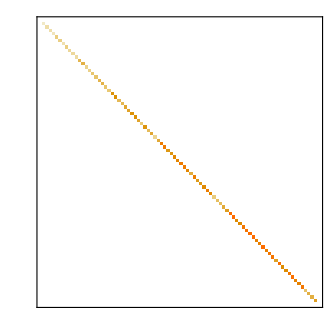
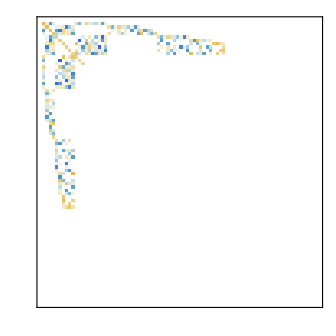
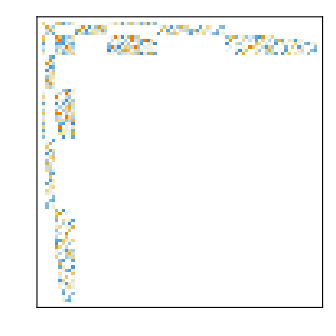
H^(0) | H^(1) | H^(2)
-Graphics- | -Graphics- | -Graphics-

```mathematica
pertPlot[mat_]:=
With[{m=If[Length[Dimensions[mat]]==1, Transpose@{mat}, mat]},
figMatrixPlot[m, 
ImageSize->Replace[pixelsPerState*Replace[Dimensions[Transpose@m], 1->0, 1], 0->Automatic, 1], 
AspectRatio->Automatic
]
];
perturbations=;
perturbations[[2]]+=DiagonalMatrix[10^-3*Join[
1/Sqrt[Range[13]],
ConstantArray[0, nStates-13]
]
];
pixelsPerState=4;
nStates=Length[perturbations[[1]]];
Grid@{
figStyleText/@{"H^(0)", "H^(1)", "H^(2)"},
pertPlot/@perturbations
}
```

```mathematica
Block[{pixelsPerState=3},
MapThread[
imageify@Show[#2, Epilog->Inset[#1, Scaled[{.5, 0}], Scaled[{.5, 0}]]]&,
{
figStyleText@Style[#, FontSize->30]&/@{"H^(0)", "H^(1)", "H^(2)"},
pertPlot/@perturbations[[;;, ;;40, ;;40]]
}
]
]
```

{-Graphics-,-Graphics-,-Graphics-}

#### Non-Degenerate Case

E_n^(k)=n^(0)H^(k)n^(0) + n^(0):T ΔE_1^1(k)T:Δn
P_T_n n^(k)=[T_n:Π_n^(0):T_n]T:Δn_0^1(k)
n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

We’ll pick some state and call it n. In the non-degenerate case this defines n^(0).

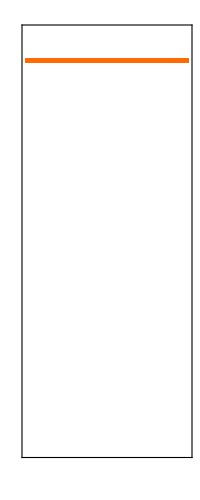
n^(0) | = | -Graphics-

```mathematica
perturbedState=6;
$ptData=initializePTData[perturbations, perturbedState];
$ptData[["n", 1]]=
Join[ConstantArray[0, perturbedState-1], {1},ConstantArray [0, $ptData[["NDim"]]-perturbedState]];
Grid@{
{figStyleText["n^(0)"], figStyleText@"=",
pertPlot[Transpose[{ϕ[$ptData][0]}]]
}
}
```

we get the first-order energy through a matrix contraction

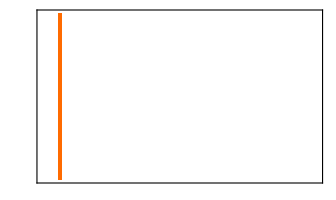
E^(1) | = | -Graphics- | -Graphics- | -Graphics-

```mathematica
$ptData[["E", 2]]=ϕ[$ptData][0].Η[$ptData][1].ϕ[$ptData][0];
Grid@{
{figStyleText["E^(1)"], 
figStyleText@"=",
pertPlot[{ϕ[$ptData][0]}],
pertPlot[Η[$ptData][1]],
pertPlot[Transpose@{ϕ[$ptData][0]}]
}
}
```

and defining the perturbation operator in this space

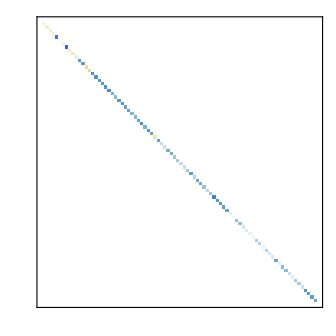
[T_n:Π_n^(0):T_n] | = | -Graphics-

```mathematica
Grid@{
{
figStyleText["[T_n:Π_n^(0):T_n]"], figStyleText@"=",
pertPlot[Π[$ptData][𝒯𝓃[$ptData], 0]]
}
}
```

we can build the first order correction to the wave function in the T_n subspace by first building an energy-shifted perturbation and applying this to the zero-order state to get an unperturbed correction

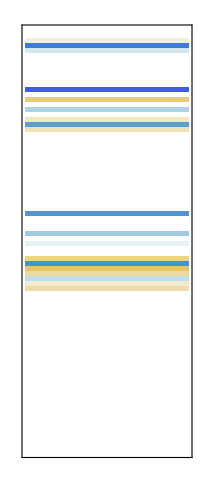
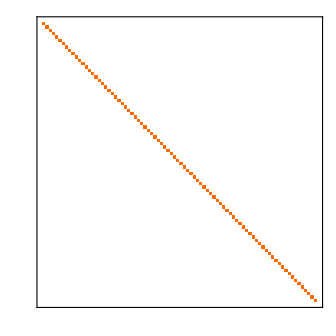
Δn^(1) | = | -Graphics- | = | (-Graphics---Graphics-) | -Graphics-

```mathematica
Grid@{
{figStyleText["Δn^(1)"], 
figStyleText@"=",
pertPlot[
Transpose@{Δn[$ptData][𝒯[$ptData], 1, {0, 1}]}
],
figStyleText@"=",
RawBoxes@RowBox@{
StyleBox["(", $figTextStyles],
ToBoxes@pertPlot[Η[$ptData][1]],
ToBoxes@figStyleText@"-",
ToBoxes@pertPlot[DiagonalMatrix[ConstantArray[Ε[$ptData][1], $ptData[["NDim"]] ]]],
StyleBox[")", $figTextStyles]
},
pertPlot[Transpose@{ϕ[$ptData][0]}]
}
}
```

and then to get the true first-order wave function correction in T_n we apply the perturbation operator

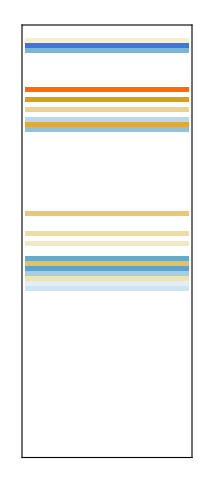
n^(1) | = | -Graphics- | = | -Graphics- | -Graphics-

```mathematica
$ptData[["n", 2]]=Dot[Π[$ptData][𝒯𝓃[$ptData], 0], Δn[$ptData][𝒯[$ptData], 1, {0, 1}]];
Grid@{
{figStyleText["n^(1)"], 
figStyleText@"=",
pertPlot[Transpose@{ϕ[$ptData][1]}],
figStyleText@"=",
pertPlot[Π[$ptData][𝒯𝓃[$ptData], 0]],
pertPlot[Transpose@{Δn[$ptData][𝒯[$ptData], 1, {0, 1}]}]
}
}
```

and in general we need to evaluate overlaps to get the correction to n^(1) along n^(0) but that is always 0 at first order so we’ll ignore it here.

Moving to second order stuff gets more interesting E^(2) now has a component from n^(0) but now also has a n^(1) part from an energy shifted version of H^(1)

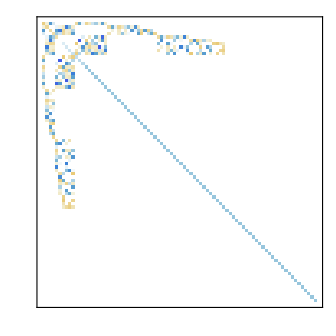
E^(2) | = | -Graphics- | -Graphics- | -Graphics- | +
 |  | -Graphics- | -Graphics- | -Graphics- |

```mathematica
$ptData[["E", 3]]=
Dot[ϕ[$ptData][0], Η[$ptData][2], ϕ[$ptData][0]]+
Dot[ϕ[$ptData][0], Δn[$ptData][𝒯[$ptData], 2, {1, 1}]];
Grid@{
{figStyleText["E^(2)"], 
figStyleText@"=",
pertPlot[{ϕ[$ptData][0]}],
pertPlot[Η[$ptData][2]],
pertPlot[Transpose@{ϕ[$ptData][0]}],
figStyleText@"+"
},
{"", "", 
pertPlot[{ϕ[$ptData][0]}],
pertPlot[dH[$ptData][1]],
pertPlot[Transpose@{ϕ[$ptData][1]}]
}
}
```

and the T_n portion of the wavefunction correction now looks like

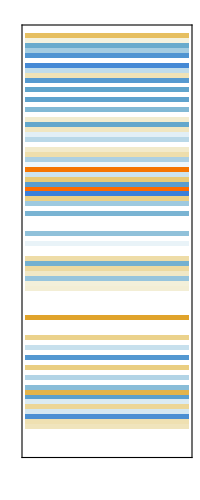
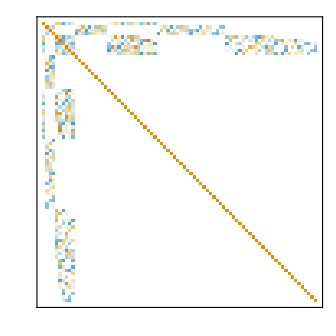
Δn^(2) | = | -Graphics- | = | -Graphics- | -Graphics- | + | -Graphics- | -Graphics-

```mathematica
Grid@{
{figStyleText["Δn^(2)"], 
figStyleText@"=",
pertPlot[Transpose@{Δn[$ptData][𝒯[$ptData],2, {0, 1}]}],
figStyleText@"=",
pertPlot[dH[$ptData][2]],
pertPlot[Transpose@{ϕ[$ptData][0]}],
figStyleText@"+",
pertPlot[dH[$ptData][1]],
pertPlot[Transpose@{ϕ[$ptData][1]}]
}
}
```

and again to get the true correction in the T_n subspace we apply the perturbation operator to this (and add on the n^(0) component by doing the not-shown overlaps)

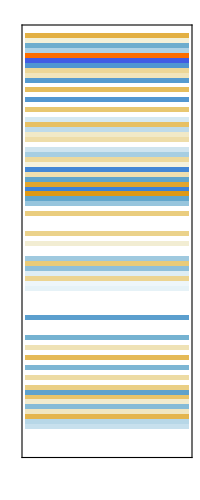
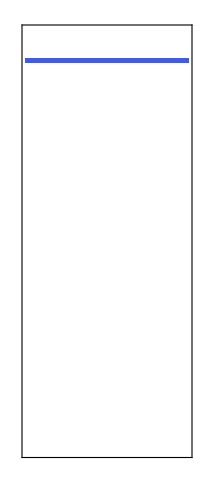
n^(2) | = | -Graphics- | = | -Graphics- | -Graphics- | + | -Graphics-

```mathematica
$ptData[["n", 3]]=
Dot[Π[$ptData][𝒯𝓃[$ptData], 0], Δn[$ptData][𝒯[$ptData], 2, {0, 1}]]+
♚[$ptData][2]*ϕ[$ptData][0];
Grid@{
{figStyleText["n^(2)"], 
figStyleText@"=",
pertPlot[ϕ[$ptData][2]],
figStyleText@"=",
pertPlot[Π[$ptData][𝒯𝓃[$ptData], 0]],
pertPlot[Transpose@{Δn[$ptData][𝒯[$ptData], 2, {0, 1}]}],
figStyleText@"+",
pertPlot[♚[$ptData][2]*ϕ[$ptData][0]]
}
}
```

the exact same code can now be used to get to arbitrary orders of correction.

#### Degenerate Case

We’ll pull out a subspace of H^(0) where the energies are close enough that we’ll call them degenerate (I’m picking randomly, JSYK, so this will actually introduce some degree of error). We’re going to show how to get perturbation corrections for these states.

The projection operator onto this space looks like

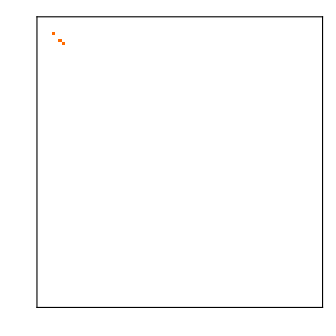

```mathematica
𝒟={6,7,4};
pertPlot[𝒫𝓇[$ptData][𝒟]]
```

and to get the proper zero-order states we take the appropriate chunks of H^(1)

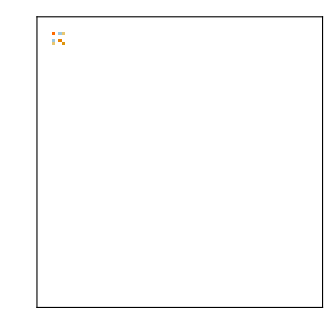
P_DH^(1)P_D | = | -Graphics-

```mathematica
Grid@
{
{
figStyleText["P_DH^(1)P_D"], 
figStyleText@"=",
pertPlot[𝒫𝓇[$ptData][𝒟].Η[$ptData][1].𝒫𝓇[$ptData][𝒟]]
}
}
```

and we diagonalize in the subspace.

Then for consistency, we’ll use the state that looks most like our initial state of interest, assuming one exists

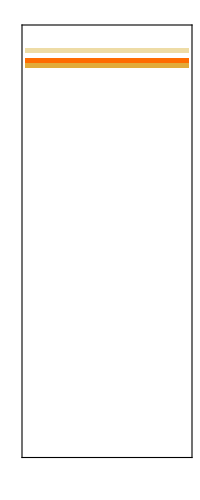
n^(0) | = | -Graphics-

```mathematica
{degE1, degN0}=Eigensystem[ 𝒫[𝒟]**Η[$ptData][1]**𝒫[𝒟]];
$dD=initializePTData[perturbations, 𝒟[[1]]];
𝒰=Complement[𝒯[$dD], 𝒟];
$dD[["E", 2]]=degE1[[2]];
$dD[["n", 1]]=ReplacePart[ConstantArray[0, $dD[["NDim"]]], Thread[𝒟->degN0[[2]]]];
Grid@{{figStyleText["n^(0)"], figStyleText@"=",
pertPlot[Transpose[{ϕ[$dD][0]}]]
}}
```

where we can see that this is clearly a linear combination of the degenerate original states where the strongest contribution is coming from state 4 in the original bases.

We have the first order energy correction from this already, too, so now we focus on getting the first-order corrections to the wave functions in the non-degenerate space. To do this we have

P_U n^(k)=[U:Π_n^(0):U]T:Δn_1^1(k) + [U:Π_n^(0):U]H^(k)n^(0)

which means we build most of the unperturbed correction to the wave function in the total space & then add on the final order k part in only non-degenerate pace. We won’t go too much into this, since it looks pretty much identical to what we did before. In any case we get

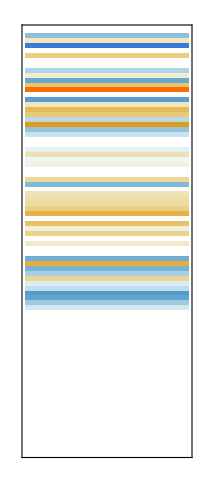
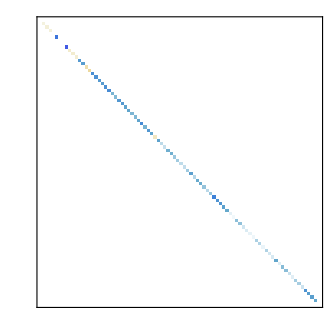
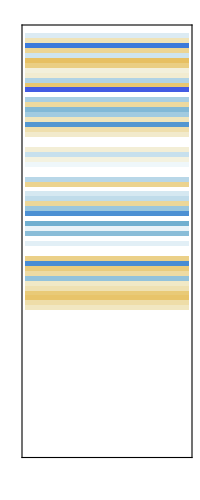
P_Un^(1) | = | -Graphics- | = | -Graphics- | -Graphics-

```mathematica
$dD[["n", 2]]=Dot[Π[$dD][𝒰, 0], Δn[$dD][𝒯[$ptData],1, {1, 1}]+Dot[Η[$ptData][1], ϕ[$dD][0]]];
Grid@{{figStyleText["P_Un^(1)"], figStyleText@"=",
pertPlot[ϕ[$dD][1]],
figStyleText@"=",
pertPlot[Π[$dD][𝒰, 0]],
pertPlot[
Δn[$dD][𝒯[$ptData],1, {1, 1}]
+Dot[Η[$ptData][1], ϕ[$dD][0]]
]
}}
```

and now we get the second order energy correction using

E^(k)= n^(0)H^(k)n^(0) + n^(0):T δH_n^(1)U:n^(k-1) + n^(0):T ΔH_1^2(k)T:Δn

which we will only illustrate in part, since it gets tedious to type out

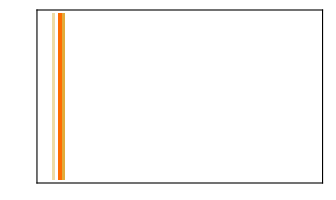
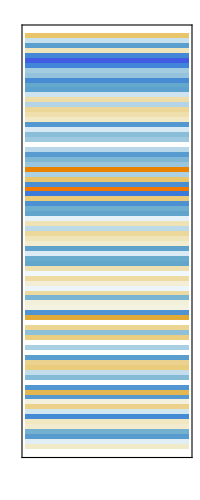
E_n^(2) | = | -Graphics- | -Graphics-

```mathematica
$dD[["E", 3]]=Dot[ϕ[$dD][0], 
Dot[Η[$dD][2],ϕ[$dD][0]] + 
Dot[dH[$dD][1], 𝒫𝓇[$dD][𝒰].ϕ[$dD][1]]+
Δn[$dD][𝒯[$dD], 2, {1, 2}]
];
Grid@{{figStyleText["E_n^(2)"],figStyleText@"=",
pertPlot[{ϕ[$dD][0]}],
pertPlot[
Dot[Η[$dD][2],ϕ[$dD][0]] + 
Dot[dH[$dD][1], 𝒫𝓇[$dD][𝒰].ϕ[$dD][1]]+
Δn[$dD][𝒯[$dD], 2, {1, 2}]
]
}}
```

and then with this we can get P_D n^(1) (since we’re at order 1 the overlap part is zero)

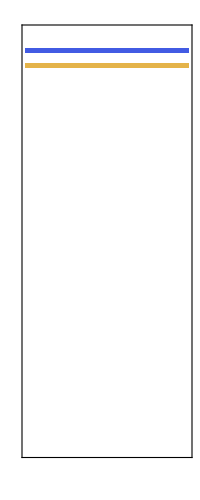
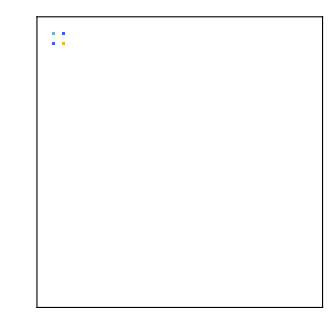
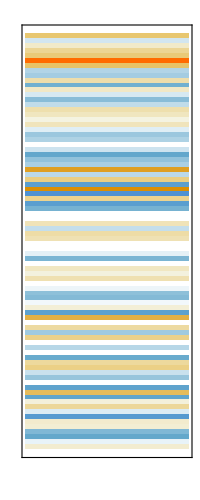
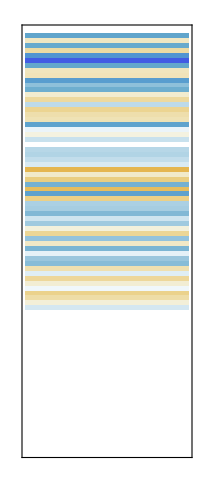
P_Dn^(1) | = | -Graphics- | = | -Graphics- | -Graphics- | + | -Graphics- | -Graphics-

```mathematica
$dD[["n", 2]]=
ReplacePart[$dD[["n", 2]], Thread[𝒟->0]]+
Π[$dD][Complement[𝒟, {$dD[["idx"]]} ], 1].(
Δn[$dD][𝒟, 2, {0, 2}]+
Δn[$dD][𝒰, 2, {0, 1}]
)+♚[$dD][1]*ϕ[$dD][0];
Grid@{{figStyleText["P_Dn^(1)"],figStyleText@"=",
pertPlot[
Π[$dD][Complement[𝒟, {$dD[["idx"]]} ], 1].(
Δn[$dD][𝒟, 2, {0, 2}]+Δn[$dD][𝒰, 2, {0, 1}]
)
],
figStyleText@"=",
pertPlot[Π[$dD][Complement[𝒟, {$dD[["idx"]]}], 1]],
pertPlot[Δn[$dD][𝒟, 2, {0, 2}]],
figStyleText@"+",
pertPlot[Π[$dD][Complement[𝒟, {$dD[["idx"]]}], 1]],
pertPlot[Δn[$dD][𝒰, 2, {0, 1}]]
}}
```

P_D H^(1)P_D n^(0)=E_n^(1)P_D n^(0)
P_U n^(k)=[U:Π_n^(0):U]T:Δn_1^1(k) + [U:Π_n^(0):U]H^(k)n^(0)
E^(k)= n^(0)H^(k)n^(0) + n^(0):T δE_n^(1)U:n^(k-1) + n^(0):T ΔE_1^2(k)T:Δn
P_Dn n^(k)=[D_n:Π_n^(1):Dn]D:Δn_0^2(k+1) + [D_n:Π_n^(1):Dn]U:Δn_0^1(k+1)
n^(0)  n^(k)=-1/2n^(k)∑_(i=1)^(k-1) n^(i)  n^(k-i)

and with this we can build up to arbitrary order

#### Degeneracies in E^(1)

On occasion we’ll end with a degeneracy through H^(1). Just because, we’ll pretend that two of the states we had in D remain degenerate through H^(1).  This space is now expressed in terms of the zero-order states coming from H^(1), so the projection onto the twice degenerate space, G, and its complement V look like

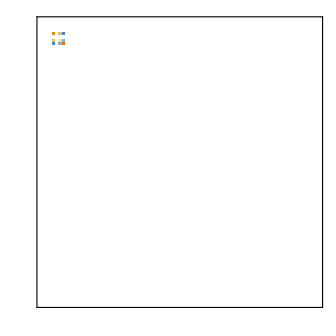
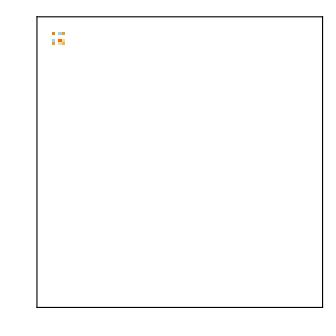
P_G | = | -Graphics- | P_V | = | -Graphics-

```mathematica
𝒢={1, 2};
𝒫𝓇𝒢=
ReplacePart[
ConstantArray[0, {$dD[["NDim"]], $dD[["NDim"]]}],
Thread[Flatten[Outer[List, 𝒟, 𝒟], 1]->
Flatten[Transpose[degN0[[𝒢]]].degN0[[𝒢]], 1]
]
];
𝒱={3};
𝒫𝓇𝒱=
ReplacePart[
ConstantArray[0, {$dD[["NDim"]], $dD[["NDim"]]}],
Thread[Flatten[Outer[List, 𝒟, 𝒟], 1]->
Flatten[Transpose[degN0[[𝒱]]].degN0[[𝒱]], 1]
]
];
Grid@{{
figStyleText["P_G"],figStyleText@"=",pertPlot@𝒫𝓇𝒱,
figStyleText["P_V"],figStyleText@"=",pertPlot@𝒫𝓇𝒢
}}
```

the first thing we do is get the second order correction to the energy by

P_G (H^(2)-H^(1)[U:Π_n^(0):U]H^(1))P_G n^(0)=E_n^(2)P_G n^(0)

where the total perturbed perturbation matrix is given by

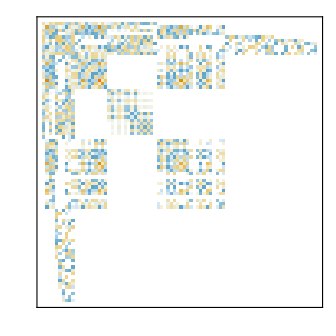

```mathematica
pertPlot[Η[$dD][2] - Dot[Η[$dD][1], Π[$dD][𝒰, 0], Η[$dD][1]]]
```

but worth noting of course that we only use a small fragment of it (I scaled the image size up by 10× so we can actually see it...)

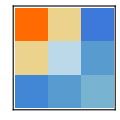

```mathematica
pertH2=𝒫[𝒟]**Dot[
𝒫𝓇𝒢,
Η[$dD][2] - Dot[Η[$dD][1], Π[$dD][𝒰, 0], Η[$dD][1]],
𝒫𝓇𝒢
]**𝒫[𝒟];
Block[{pixelsPerState=40},
pertPlot[
𝒫[𝒟]**Dot[
𝒫𝓇𝒢,
Η[$dD][2] - Dot[Η[$dD][1], Π[$dD][𝒰, 0], Η[$dD][1]],
𝒫𝓇𝒢
]**𝒫[𝒟]
]
]
```

and from this we get the zero-order states and second-order energies, with the mild subtlety that we have a properly 2D state space in G, but this is a 3×3 matrix, meaning either we will want to transform the matrix into our 2×2 space or just drop the states corresponding to eigenvalues of zero. We’ll do the latter. We’ll also once again pull the state with the largest contribution from our initial zero-order state of interest.

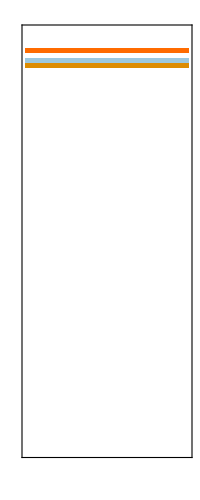
n^(0) | = | -Graphics-

```mathematica
$gData=initializePTData[perturbations,perturbedState];
$gData[["E", 2]]=$dD[["E", 2]];
{deg2E2, deg2N0}=Eigensystem[pertH2];
$gData[["E", 3]]=deg2E2[[2]];
$gData[["n", 1]]=ReplacePart[ConstantArray[0, $dD[["NDim"]]], Thread[𝒟->deg2N0[[2]]]];
Grid@{{figStyleText["n^(0)"], figStyleText@"=",
pertPlot[ϕ[$gData][0]]
}}
```

and now we can apply the equations we’ve written down in basically the same way as we did before, starting with getting the corrections in the non-degenerate subspace using E_n^(1), then moving to V space, using E^(2), and finally using those bits to build E^(3), which we’ll use to get the corrections in the G space.

### Nearly-Degenerate Analysis

It is often not the case that we have truly degenerate states, instead tending to have nearly degenerate states which cause numerical issues. To that effect, we note that the use of the identity

H^(0)P_D n^(k)=E_n^(0)P_D n^(k)

is not formally correct. If instead we have that

∀_(d∈D)H^(0)d^(0)=E_n^(0)+δ E_d

we get

H^(0)P_D n^(k)=E_n^(0)P_D n^(k)+∑_d δ E_d n^(k) d^(0)d^(0)

and so when we use that identity we are actually assuming that δ E_d is small enough in general to swamp any overlap term.

A key place this comes in is in deriving the first order degenerate energy correction when we say that

P_D H^(0)n^(1)-E_n^(0)P_D n^(1) = 0

if we are to include this error term we have

P_D H^(1)n^(0)=E_n^(1)P_D n^(0)+∑_d δ E_d n^(1) d^(0)d^(0)

and by using the same trick as for the degenerate H^(1) case, we pull P_D n^(1) in terms of n^(0)

P_n=I-n^(0)n^(0)

and now we can define

Π_Dn=P_D(P_n(H^(1)-E_n^(1)))^-1 P_n P_D

which means that

P_Dn n^(1)=Π_Dn( (E_n^(2)n^(0)-H^(2)n^(0)) + (H^(1)-E_n^(1))Π_U H^(1)n^(0))
=Π_Dn E_n^(2)n^(0)-Π_Dn H^(2)n^(0)+Π_Dn H^(1)Π_U H^(1)n^(0)-E_n^(1)Π_Dn Π_U H^(1)n^(0)
=Π_Dn(H^(1)Π_U H^(1)-H^(2))n^(0)

and so we get

∑_d δ E_d n^(1) d^(0)d^(0)=∑_d δ E_d d^(0)d^(0)Π_Dn(H^(1)Π_U H^(1)-H^(2))n^(0)

then we’ll introduce an error operator

F_D=∑_d δ E_d d^(0)d^(0)

which gives us

∑_d δ E_d n^(1) d^(0)d^(0)=F_D Π_Dn(H^(1)Π_U H^(1)-H^(2))n^(0)

which almost gives us a way to get a “corrected” E^(1) and zero-order states from which we can infer our error bounds from assuming F_D=𝟘. Unfortunately

Π_Dn=P_D(P_n(H^(1)-E_n^(1)))^-1 P_n P_D

so

P_D H^(1)n^(0)=E_n^(1)P_D n^(0)+F_D P_D(I-n^(0)n^(0))(H^(1)-E_n^(1))^-1(I-n^(0)n^(0))P_D(H^(1)Π_U H^(1)-H^(2))n^(0)

which is a non-trivially solvable problem (honestly it might not be generally solvable), but which does give us a way to measure how the n^(0) and E^(1) we obtain are to the “proper” solution since in that case

F_D P_D(I-n^(0)n^(0))(H^(1)-E_n^(1))^-1(I-n^(0)n^(0))P_D(H^(1)Π_U H^(1)-H^(2))n^(0)=𝟘

and so we can introduce the norm of this term as an error measure, i.e.

F_D=∑_d δ E_d d^(0)d^(0)
F̃=|F_D Π_Dn(H^(1)Π_U H^(1)-H^(2))n^(0)|

where if this is large, we know we were not justified in calling the states nearly degenerate.

### Table of Evaluated Terms

Annoyingly, this arrangement of the terms isn’t very popular. Instead scientists usually write out direct expanded expressions in terms of the zero-order states. So we’re gonna tabulate first, second, and third order correction expressions to make working with existing stuff cleaner. We won’t do full expansions of the terms, because that’s a pain in the ass, but we’ll get part of the way there.

##### First Order

E_n^(1)=n^(0) H^(1)n^(0)
n^(0)  n^(1)=0
n^(1)=Π_n(H^(1)-E_n^(1))n^(0)
=Π_n H^(1)n^(0)

##### Second Order

E_n^(2)=n^(0) H^(2)n^(0)+ n^(0) H^(1)n^(1)-E_n^(1)n^(0)  n^(1)
n^(0)  n^(2)=-1/2n^(1)  n^(1)
n^(2)=Π_n(H^(2)-E_n^(2))n^(0)+Π_n(H^(1)-E_n^(1))n^(1)+n^(0)  n^(2)n^(0)
=Π_n H^(2)n^(0)+Π_n(H^(1)-E_n^(1))Π_n H^(1)n^(0)-1/2 n^(1)  n^(1)n^(0)
=Π_n H^(2)n^(0)+Π_n H^(1)Π_n H^(1)n^(0)-E_n^(1)Π_n Π_n H^(1)n^(0)-1/2 n^(1)  n^(1)n^(0)

##### Third Order

E_n^(3)=n^(0) H^(3)n^(0)+ ∑_(i=1)^2 n^(0) H^(3-i)n^(i)-E_n^(3-i)n^(0)  n^(i)
=n^(0) H^(3)n^(0)+n^(0) H^(2)n^(1)-E_n^(2)n^(0)  n^(1)+n^(0) H^(1)n^(2)-E_n^(1)n^(0)  n^(2)
n^(0)  n^(3)=-1/2∑_(i=1)^2 n^(i)  n^(3-i)
=-1/2(n^(1)  n^(2)+n^(2)  n^(1))
=-n^(1)  n^(2)
n^(3)=∑_(i=0)^2 Π_n(H^(3-i)-E_n^(3-i))n^(i)+n^(0)n^(0)  n^(3)
=Π_n(H^(3)-E_n^(3))n^(0)+Π_n(H^(2)-E_n^(2))n^(1)+Π_n(H^(1)-E_n^(1))n^(2)+n^(0)n^(0)  n^(3)
=Π_n H^(3)n^(0)+Π_n H^(2)n^(1)+Π_n H^(1)n^(2)-E_n^(2)Π_n n^(1)-n^(1)  n^(2)n^(0)

##### Fourth Order Energy

E_n^(k)=n^(0) H^(4)n^(0)+n^(0) H^(3)n^(1)+n^(0) H^(2)n^(2)+n^(0) H^(1)n^(3)-E_n^(2)n^(0)  n^(2)-E_n^(1)n^(0)  n^(3)
n^(2)=Π_n H^(2)n^(0)+Π_n H^(1)Π_n H^(1)n^(0)-E_n^(1)Π_n Π_n H^(1)n^(0)-1/2 n^(1)  n^(1)n^(0)
n^(3)=Π_n H^(3)n^(0)+Π_n H^(2)n^(1)+Π_n H^(1)n^(2)-E_n^(2)Π_n n^(1)-n^(1)  n^(2)n^(0)

### Operator Representations

Often we have an operator A and need to get something like

nAm=(∑_k n^(k)λ^k)A(∑_k m^(l)λ^k)

naively, we might think that we can just evaluate this out directly. Unfortunately, because of the truncation done in the perturbation expansion, this would introduce errors. Instead, we need to first expand A itself out as a series of perturbations

A=∑_k A^(k)λ^k

and then we can compute the perturbative correction to the expectation value by matching up terms with the same total value of λ^k. Since we’re going to be adding up terms that look like

n^(α)A^(γ)m^(β)

we unfortunately have three indices to sum over, i.e. we’re looking for non-negative, integral solutions to

α+β+γ=k

which we’ll want to do in two steps:

Fix a value for α∈{0...k}

Sum over the solutions to β+γ=k-α

or written out explicitly

nA m^(k)=∑_(α=0)^k ∑_(β=0)^(k-α) n^(α)A^(k-α-β)m^(β)

which if done out explicitly for k=2 gives us

nA m^(2)= n^(0)A^(2)m^(0)+n^(0)A^(1)m^(1)+n^(0)A^(0)m^(2)+n^(1)A^(1)m^(0)
+n^(1)A^(0)m^(1)+n^(2)A^(0)m^(0)

#### Selection Rules

It’s worth considering how this play with selection rules, to improve efficiency. First off, we will note that when we have

n^(α)A^(k-α-β)m^(β)

in general n^(α) will be an expansion over a select set of initial states and m^(β) will be an expansion over a different one. We’ll write this as

n^(α) = ∑_k c_k^(n)ϕ_k^(0)
m^(β) = ∑_j c_j^(m)ϕ_j^(0)

Now if A^(k-α-β) has an associated set of selection rules, {Δ}, then we can generate the set of transformed states

{Δ}⊗{ϕ_j^(0)}

and take the intersection of this set with {ϕ_k^(0)} to determine what our active space is.

Alternately, as long as our operator is Hermitian, we can apply {Δ} to {ϕ_k^(0)}

### Degeneracies Derivation

We’d like a more-elegant way to manage the degeneracies. To that effect, we’ll modify our existing perturbation operator. We start with a state of interest, n, and identifying a space of degenerate states which can couple to it, D (and crucially including n itself in this subspace) we can write our projection operator as

R_n=(I-∑_(d∈D) d^(0)d^(0))

and so we are able to project onto the non-degenerate subspace for n.

We can then apply non-degenerate perturbation theory as usual.

Then when looking at the corrections to n we have

n^(k)=∑_(i=0)^(k-1) Π_n(E_n^(k-i)-H^(k-i))n^(i)+n^(0)n^(0)  n^(k)

where Π_n will now remove any contribution from D, meaning that at all levels of correction n^(k) has no contribution from D. We would now like to recover these contributions. That means we’d like to be able to write

n^(k)=∑_(i=0)^(k-1) Π_n(E_n^(k-i)-H^(k-i))n^(i)+∑_(d∈D) d^(0)d^(0)  n^(k)

In the single state case we set m=n in

n^(0)  m^(k)+n^(k)  m^(0)=-∑_(i=1)^(k-1) n^(i)  m^(k-i)

but now that will not save us.

Instead all we have is

n^(k)  m^(0)=-∑_(i=1)^(k-1) n^(i)  m^(k-i) - n^(0)  m^(k)

and so we have an apparently under-determined system.

#### A Return to Sakurai

As Sakurai points out, even though our states begin life as degenerate, the effect of the perturbation is generally to remove this degeneracy. To that effect, we expand in our degenerate states as

n^(0)=∑_(d∈D) d^(0)  n^(0)d^(0)

which, if all states d^(0) have the same energy, will still be an eigenstate of the zero-order Hamiltonian.

Beyond this, we’ll write n as usual as

n=∑_(i=0) n^(i)λ^i
H=∑_(i=0) H^(i)λ^i
E=∑_(i=0) E^(i)λ^i

and as usual we’ll assume λ=1, but keep in mind that the equations we’ll write must work for any choice of λ.

Dope. Now we’ll introduce a separation into a degenerate and non-degenerate subspace as

P_D=∑_(d∈D) d^(0)d^(0)
P_U=I-P_D

then we can write

Hn=E(P_U+P_D)n
Hn=E P_U n+E P_D n

and then turn this into two equations by projecting using P_U or P_D respectively

P_U Hn=P_U E P_U n+P_U E P_D n
=P_U E P_U n+E P_U P_D n
=E P_U n
P_D Hn=P_D E P_U n+P_D E P_D n
=E P_D n

we’ll look at the first of these and note that if we define

Π_D=(P_U(H^(0)-E_n^(0)))^-1 P_U

we can solve for P_U n using the normal approach, given all the lower-order corrections, which will of course include n^(0) which is currently undetermined. We’ll go into this more in a bit.

Looking at the second, we’ll expand out the first two Trash Equations, because we’ll basically be doing strong induction with base case of i=1

P_D H^(0)n^(0)=E^(0)P_D n^(0)
P_D H^(0)n^(1)+P_D H^(1)n^(0)=E^(0)P_D n^(1)+E^(1)P_D n^(0)

the first of these isn’t particularly interesting, but in the second we’ll insert the identity operator again, this time on the left

P_D H^(0)P_D n^(1)+P_D H^(0)P_U n^(1)+P_D H^(1)P_D n^(0)+P_D H^(1)P_U n^(0)=E^(0)P_D n^(1)+E^(1)P_D n^(0)

now we’ll note that by construction

P_D H^(0)P_U n^(1)=0
P_D H^(0)P_D n^(1)=E^(0)P_D n^(1)     ( bc ∀_dϵD d^(0)H^(0)d^(0)=E^(0))
P_U n^(0)=0    ( bc n^(0)=∑_(d∈D) d^(0)  n^(0)d^(0) )

so we get

P_D H^(1)P_D n^(0)+P_D H^(1)P_U n^(0)=E^(1)P_D n^(0)
P_D H^(1)P_D n^(0)=E^(1)P_D n^(0)

which gives us a concrete way to evaluate

n^(0)=∑_(d∈D) d^(0)  n^(0)d^(0)

and simultaneously get E^(1) which is pretty cool. It’s worth pointing out that E^(1) doesn’t need to be 0 in this construction, even for the H.O. basis.

With that in place, we can now get P_U n^(1).

Moving on to the general case, we can always write

P_D H^(0)n^(k)+∑_(i=0)^(k-1) P_D H^(k-i)n^(i)=P_D E^(0)n^(k)+∑_(i=0)^(k-1)  P_D E^(k-i)n^(i)
∑_(i=0)^(k-1) P_D H^(k-i)n^(i)=∑_(i=0)^(k-1)  P_D E^(k-i)n^(i)

which is pretty slick, but also means that if we P_D n^(k) we actually need to go to order k+1.

In any case, we’ll try to find a general way to get E^(k) and P_D n^(k-1) assuming we know the lower-order stuff. To do that, we’ll basically just take a note from what we did in the non-degenerate case and apply n^(0) on the left

∑_(i=0)^(k-1) n^(0)P_D H^(k-i)n^(i)=∑_(i=0)^(k-1)  E^(k-i)n^(0)P_D n^(i)

then we’ll isolate and rearrange stuff so things look the way the did in the non-degenerate case

E^(k)n^(0)P_D n^(0)=n^(0)P_D H^(k)n^(0)+ ∑_(i=1)^(k-1) n^(0)P_D H^(k-i)-E^(k-i)P_D n^(i)

but then we’ll need to pull out one more term

E^(k)n^(0)P_D n^(0)=n^(0)P_D H^(k)n^(0)+ n^(0)P_D H^(1)-E^(1)P_D n^(k-1)+ ∑_(i=1)^(k-2) n^(0)P_D H^(k-i)-E^(k-i)P_D n^(i)

because as we noted before, we don’t actually have n^(k-1)

Hope is not lost though, since we recall that earlier we solved

P_D H^(1)P_D n^(0)=E^(1)P_D n^(0)

or equivalently by Hermiticity

n^(0)P_D H^(1)P_D=n^(0)E^(1)P_D

and therefore

n^(0)P_D H^(1)-E^(1)P_D n^(k-1) = n^(0) (P_D H^(1)-E^(1)P_D) (P_U+P_D)n^(k-1)
= n^(0) (P_D H^(1)-E^(1)P_D)P_U n^(k-1) + n^(0) (P_D H^(1)-E^(1)P_D)P_D n^(k-1)
= n^(0) P_D H^(1)P_U n^(k-1) + n^(0) P_D H^(1)P_D n^(k-1)-n^(0) E^(1) n^(k-1)
= n^(0) P_D H^(1)P_U n^(k-1) + n^(0)E^(1)P_D n^(k-1)-n^(0) E^(1) n^(k-1)
= n^(0) P_D H^(1)P_U n^(k-1)

and so we end up with an even more restricted summation than in the non-degenerate case

E^(k)n^(0)P_D n^(0)=n^(0)P_D H^(k)n^(0)+n^(0) P_D H^(1)P_U n^(k-1)+ ∑_(i=1)^(k-2) n^(0)P_D H^(k-i)-E^(k-i)P_D n^(i)

where we will assume (this will be justified later) that we have P_U n^(k-1).

Now we can make use of the fact that when we solved for n^(0) we did so by diagonalizing a matrix in the P_D subspace, and so we can choose n^(0) to be normalized, giving us

n^(0)P_D n^(0)=1
E^(k)=n^(0)P_D H^(k)n^(0)+n^(0) P_D H^(1)P_U n^(k-1)+ ∑_(i=1)^(k-2) n^(0)P_D H^(k-i)-E^(k-i)P_D n^(i)

Great! We’ve recovered k-order energy. Now we need to get P_D n^(k-1). To do that, again, we’ll return to

∑_(i=0)^(k-1) P_D H^(k-i)n^(i)=∑_(i=0)^(k-1)  P_D E^(k-i)n^(i)

and now that we can evaluate the entirety of the RHS, we can happily write

P_D(H^(1)-E^(1))n^(k-1)=∑_(i=0)^(k-2)  P_D(E^(k-i)-H^(k-i))n^(i)

which, I will not lie, doesn’t look too promising. But we’ll add in the identity again to give us

P_D(H^(1)-E^(1))P_D n^(k-1)+P_D(H^(1)-E^(1))P_U n^(k-1)=∑_(i=0)^(k-2)  P_D(E^(k-i)-H^(k-i))n^(i)

and so now if we can evaluate P_U n^(k-1) we can write

P_D(H^(1)-E^(1))P_D n^(k-1)=∑_(i=0)^(k-2)  P_D(E^(k-i)-H^(k-i))n^(i)-P_D(H^(1)-E^(1))P_U n^(k-1)

and then invert P_D H^(1)P_D which will be a small, easy to work with matrix (it is important to point out that since H^(1) will be represented in the basis of eigenfunctions of H^(0) it won’t matter that n^(0) is an eigenfunction of H^(1)) [CHECK THIS]

And so at long last we finally come back to the claim that using

Π_D=(P_U(H^(0)-E_n^(0)))^-1 P_U

will make it easy to solve

P_U Hn=E P_U n

to start off with, we do exactly what we always do, and expand and match terms in order k. Setting up the Trash Equations for arbitrary k in this subspace as

∑_(i=0)^k P_U H^(k-i)n^(i)=∑_(i=0)^k E_n^(k-i)P_U n^(i)

then we note we already have E^(k) (it’s actually impossible to determine from this using the regular trick, since n^(0)P_U=0) so we jump straight into getting the wavefunction corrections by separating out the order k terms

P_U H^(0)n^(k) +∑_(i=0)^(k-1) P_U H^(k-i)n^(i)=E_n^(0)P_U n^(k)+∑_(i=0)^(k-1) E_n^(k-i)P_U n^(i)

then we do the usual rearrangement to give us

P_U(H^(0)-E_n^(0))n^(k) =∑_(i=0)^(k-1) P_U(E_n^(k-i)-H^(k-i))n^(i)

where you’ll note we’re assuming we have n^(k-1), which seems to be in contradiction to our previous work. Don’t worry, we’ll resolve this in a moment.

Finally then we add the identity on the left and expand

P_U(H^(0)-E_n^(0))n^(k) =P_U(H^(0)-E_n^(0))P_U n^(k)+P_U(H^(0)-E_n^(0))P_D n^(k)

and then we note that any linear combination of states in the degenerate subspace is an eigenstate of H^(0) with eigenvalue E_n^(0), since

H^(0)∑_(d∈D) c_d d^(0)=∑_(d∈D) c_d H^(0)d^(0)
=∑_(d∈D) c_d E_n d^(0)
=E_n∑_(d∈D) c_d d^(0)

therefore

(H^(0)-E_n^(0))P_D n^(k)=H^(0)P_D n^(k)-E_n^(0)P_D n^(k)
=E_n^(0)P_D n^(k)-E_n^(0)P_D n^(k)
=0

and so

P_U(H^(0)-E_n^(0))n^(k) =P_U(H^(0)-E_n^(0))P_U n^(k)

which is exactly what we needed as we can now write

P_U(H^(0)-E_n^(0))P_U n^(k)=∑_(i=0)^(k-1) P_U(E_n^(k-i)-H^(k-i))n^(i)

and this is cleanly solvable by saying

Π_D=(P_U(H^(0)-E_n^(0))P_U)^-1

Finally, we need to resolve the apparent contradiction that I’m assuming we have the k-1 states here but in the previous section we needed to solve for k-1.

This contradiction is resolved by noting that what we meant by k changed. To wit, the way we actually will build up looks like this

E^(1) → from eigenvalues of H^(1)
P_U n^(0) → initialized to 𝟘
P_D n^(0) → from eigenvectors of H^(1)
E^(2) → does not use n^(1)
P_U n^(1) → usesn^(0)
P_D n^(1) → calculated when k=2, using P_U n^(1) 
E^(3) → does not use n^(2)
P_U n^(2) → usesn^(1)
P_D n^(2) → calculated when k=3, using P_U n^(2)

although actually looking at the math...we don’t even need E^(3) or to get P_D n^(2) so maybe this is a moot point anyway...basically we can use P_U n^(k-1) which only uses n^(k-2) to get P_D n^(k-1)

##### Reduction to the g=1 case

It would be interesting to look at what happens in this approach when the size of D is 1. I.e. when we don’t have a degeneracy. This ought to recover the non-degenerate case

##### Handling Cases where H^(1) doesn’t remove the degeneracy

The key to the approach was

P_D H^(0)P_D n^(1)+P_D H^(0)P_U n^(1)+P_D H^(1)P_D n^(0)+P_D H^(1)P_U n^(0)=E^(0)P_D n^(1)+E^(1)P_D n^(0)

now we’ll note that by construction

P_D H^(0)P_U n^(1)=0
P_D H^(0)P_D n^(1)=E^(0)P_D n^(1)     ( bc ∀_dϵD d^(0)H^(0)d^(0)=E^(0))
P_U n^(0)=0    ( bc n^(0)=∑_(d∈D) d^(0)  n^(0)d^(0) )

so we get

P_D H^(1)P_D n^(0)+P_D H^(1)P_U n^(0)=E^(1)P_D n^(0)
P_D H^(1)P_D n^(0)=E^(1)P_D n^(0)

but what do we do if H^(1)P_D is 0? What if it is diagonal?

In the former case, we’ll need revisit what we had

P_D H^(1)P_D n^(0)=E^(1)P_D n^(0)

and note that

P_D H^(1)P_D = 𝟘 ⇒ E^(1) = 0

we’ll also note that by construction

P_U n^(0) = 𝟘

so

P_D H^(1)n^(0) = 𝟘

So we’ll expand to the next layer of trash equations

P_D H^(0)n^(2)+P_D H^(1)n^(1)+P_D H^(2)n^(0)=E^(0)P_D n^(2)+E^(1)P_D n^(1)+E^(2)P_D n^(0)
=E^(0)P_D n^(2)+E^(2)P_D n^(0)

and then apply simplification rules like we did in the previous case

P_D H^(0)P_U n^(2)=0
P_D H^(0)P_D n^(2)=E_n^(0)P_D n^(2)     ( bc ∀_dϵD d^(0)H^(0)d^(0)=E^(0))
P_U n^(0)=0    ( bc n^(0)=∑_(d∈D) d^(0)  n^(0)d^(0) )
P_D H^(1)P_D n^(1)=0

to get

E_n^(0)P_D n^(2)+P_D H^(1)P_U n^(1)+P_D H^(2)n^(0)=E^(0)P_D n^(2)+E^(2)P_D n^(0)
P_D H^(1)P_U n^(1)+P_D H^(2)n^(0)=E^(2)P_D n^(0)

which is almost what we had before, but now we need an explicit form for P_U n^(1) to substitute and so we go to the set of equations from the non-degenerate subspace and apply our relationships

P_U H^(0)n^(1) +P_U H^(1)n^(0)=E_n^(0)P_U n^(1)+E_n^(1)P_U n^(0)
E_n^(1)=0
P_U H^(0)P_D n^(1)+P_U H^(0)P_U n^(1) + P_U H^(1)n^(0) =E_n^(0)P_U n^(1)
H^(0)P_D n^(1)=E_n^(0)P_D n^(1)   ( bc ∀_dϵD d^(0)H^(0)d^(0)=E^(0))
E_n^(0)P_U P_D n^(1)=𝟘
P_U H^(0)P_U n^(1)+P_U H^(1)n^(0)=E_n^(0)P_U n^(1)
P_U(H^(0)-E_n^(0))P_U n^(1)=-P_U H^(1)n^(0)
=-P_U H^(1)n^(0)

and that left part is cleanly invertible as expected and is just our new perturbation operator, so

P_U n^(1)=-Π_D P_U H^(1)n^(0)
=-Π_D P_U H^(1)P_D n^(0) ( bc P_U n^(0)=𝟘)

giving us now

P_D H^(1)P_U n^(1)+P_D H^(2)n^(0)=-P_D H^(1)Π_D P_U H^(1)P_D n^(0)+P_D H^(2)n^(0)
=E^(2)P_D n^(0)

and so now we can write

P_D(H^(2)-H^(1)Π_D P_U H^(1))P_D n^(0)=E^(2)P_D n^(0)

and so now we obtain the second order energy correction and the zero-order states in one go by diagonalizing that perturbed from of H^(2) in the P_D subspace

Returning to the degenerate part of n^(1), we write down what we had in the previous case

∑_(i=0)^(k-1) P_D H^(k-i)n^(i)=∑_(i=0)^(k-1)  P_D E^(k-i)n^(i)

and again we write

P_D(H^(1)-E^(1))n^(k-1)=∑_(i=0)^(k-2)  P_D(E^(k-i)-H^(k-i))n^(i)

but now we know E^(1)=0 so

P_D H^(1)n^(k-1)=∑_(i=0)^(k-2)  P_D(E^(k-i)-H^(k-i))n^(i)

and then by assumption

P_D H^(1)P_D=𝟘

so now we’re left with

P_D H^(1)P_U n^(k-1)=∑_(i=0)^(k-2)  P_D(E^(k-i)-H^(k-i))n^(i)

We’ll do an odd thing now, and assume we already know how to get P_U n^(k-1), so now we’ll pull out the k-2 part

P_D H^(1)P_U n^(k-1)=P_D(E^(2)-H^(2))n^(k-2) + ∑_(i=0)^(k-3)  P_D(E^(k-i)-H^(k-i))n^(i)

and so

P_D(H^(2)-E^(2))P_D n^(k-2)=P_D(E^(2)-H^(2))P_U n^(k-2) - P_D H^(1)P_U n^(k-1) + ∑_(i=0)^(k-3)  P_D(E^(k-i)-H^(k-i))n^(i)

and returning to the case at hand, if we let k=3 we get

P_D(H^(2)-E^(2))P_D n^(1)=P_D(E^(2)-H^(2))P_U n^(1)-P_D H^(1)P_U n^(2)+P_D(E^(3)-H^(3))n^(0)

which now requires E^(3)...but we’ll look at what’s necessary for that

E^(3)n^(0)P_D n^(0)=n^(0)P_D H^(3)n^(0)+ n^(0)P_D H^(1)-E^(1)P_D n^(2) + n^(0)P_D H^(2)-E^(2)P_D n^(1)

and then by previous stuff

n^(0)P_D H^(1)-E^(1)P_D n^(2)=n^(0)P_D H^(1)n^(2)
=n^(0)P_D H^(1)P_U n^(2)
n^(1)=Π_D P_U H^(1)P_D n^(0)+P_D n^(1)
 n^(0)P_D H^(2)-E^(2)P_D n^(1)=n^(0)P_D(H^(2)-E^(2))P_U n^(1)+n^(0)P_D(H^(2)-E^(2))P_D n^(1)

which is admittedly not going great. We want to be able to do some eigenvalue trickery somewhere to clean this up. To that effect, we’ll use the OG equations at k=2

P_U(H^(0)-E_n^(0))P_U n^(2)=P_U(E_n^(1)-H^(1))n^(1)+P_U(E_n^(2)-H^(2))n^(0)

and then invert

P_U n^(2)=Π_D(P_U(E_n^(1)-H^(1))n^(1)+P_U(E_n^(2)-H^(2))n^(0))

so now

n^(0)P_D H^(1)-E^(1)P_D n^(2)=n^(0)P_D H^(1)P_U n^(2)
=n^(0)P_D H^(1)Π_D(P_U(E_n^(1)-H^(1))n^(1)+P_U(E_n^(2)-H^(2))n^(0))
=n^(0)P_D H^(1)Π_D P_U(E_n^(1)-H^(1))n^(1)+n^(0)P_D H^(1)Π_D P_U(E_n^(2)-H^(2))n^(0)

and therefore

n^(0)P_D H^(1)-E^(1)P_D n^(2) + n^(0)P_D H^(2)-E^(2)P_D n^(1) = n^(0)P_D H^(1)Π_D P_U(E_n^(1)-H^(1))n^(1)
+ n^(0)P_D H^(1)Π_D P_U(E_n^(2)-H^(2))n^(0)
+ n^(0)P_D H^(2)-E^(2)P_D n^(1)
= n^(0)P_D H^(1)Π_D P_U(E_n^(1)-H^(1))+P_D(H^(2)-E^(2))n^(1) 
+n^(0)P_D H^(1)Π_D P_U(E_n^(2)-H^(2))n^(0)
= n^(0)P_D H^(1)Π_D P_U(E_n^(1)-H^(1))+P_D H^(2)n^(1)
-n^(0)P_D E^(2)n^(1)
+n^(0)P_D H^(1)Π_D P_U(E_n^(2)-H^(2))n^(0)

and now we finally get to applying our eigenvalue criterion since

n^(0)P_D H^(1)Π_D P_U(E_n^(1)-H^(1))+P_D H^(2)n^(1)=n^(0)P_D H^(2)-P_D H^(1)Π_D P_U H^(1)n^(1)
=n^(0)P_D(H^(2)-P_D H^(1)Π_D P_U H^(1))P_U n^(1)
 + n^(0)P_D(H^(2)-P_D H^(1)Π_D P_U H^(1))P_D n^(1)
=n^(0)P_D(H^(2)-P_D H^(1)Π_D P_U H^(1))P_U n^(1)
 + n^(0)P_D E^(2)n^(1)

and bringing stuff back together

n^(0)P_D H^(1)-E^(1)P_D n^(2) + n^(0)P_D H^(2)-E^(2)P_D n^(1) = n^(0)P_D H^(1)Π_D P_U(E_n^(1)-H^(1))+P_D H^(2)n^(1)
- n^(0)P_D E^(2)n^(1)
+ n^(0)P_D H^(1)Π_D P_U(E_n^(2)-H^(2))n^(0)
= n^(0)P_D(H^(2)-P_D H^(1)Π_D P_U H^(1))P_U n^(1)
+ n^(0)P_D E^(2)n^(1)
- n^(0)P_D E^(2)n^(1)
+ n^(0)P_D H^(1)Π_D P_U(E_n^(2)-H^(2))n^(0)
=n^(0)P_D(H^(2)-P_D H^(1)Π_D P_U H^(1))P_U n^(1) 
+ n^(0)P_D H^(1)Π_D P_U(E_n^(2)-H^(2))n^(0)

and so at the end of the day

E^(3)n^(0)P_D n^(0)=n^(0)P_D H^(3)n^(0) + n^(0)P_D(H^(2)-P_D H^(1)Π_D P_U H^(1))P_U n^(1) 
+ n^(0)P_D H^(1)Π_D P_U(E_n^(2)-H^(2))n^(0)

which is possible to evaluate entirely in terms of things we have and so we will be able to now obtain

P_D(H^(2)-E^(2))P_D n^(1)=P_D(E^(2)-H^(2))P_U n^(1)-P_D H^(1)P_U n^(2)+P_D(E^(3)-H^(3))n^(0)

and then by inverting (H^(2)-E^(2)) in the P_D subspace we can get P_D n^(1)

Generalization of this Procedure

We’ll return to

P_D(H^(2)-E^(2))P_D n^(k-2)=P_D(E^(2)-H^(2))P_U n^(k-2) - P_D H^(1)P_U n^(k-1) + ∑_(i=0)^(k-3)  P_D(E^(k-i)-H^(k-i))n^(i)

which, provides a way to get the degenerate space n^(k-2) correction given the up to the E^(k) energy. That energy correction is given by

E^(k)n^(0)P_D n^(0)=n^(0)P_D H^(k)n^(0)+ ∑_(i=1)^(k-1) n^(0)P_D H^(k-i)-E^(k-i)P_D n^(i)

and which can be factored out like

E^(k)n^(0)P_D n^(0)= n^(0)P_D H^(k)n^(0) + n^(0)P_D H^(1)-E^(1)P_D n^(k-1) + n^(0)P_D H^(2)-E^(2)P_D n^(k-2) 
+ ∑_(i=1)^(k-3) n^(0)P_D H^(k-i)-E^(k-i)P_D n^(i)

now we’ll re-isolate

n^(0)P_D H^(1)-E^(1)P_D n^(k-1) + n^(0)P_D H^(2)-E^(2)P_D n^(k-2) =  n^(0)P_D H^(1)P_D n^(k-1)
+n^(0)P_D H^(1)P_U n^(k-1) 
+n^(0)P_D(H^(2)-E^(2))P_D n^(k-2)
+n^(0)P_D(H^(2)-E^(2))P_U n^(k-2)
=n^(0)P_D(H^(2)-E^(2))P_U n^(k-2)
+n^(0)P_D H^(1)P_U n^(k-1)
+n^(0)P_D(H^(2)-E^(2))P_D n^(k-2)

then by writing c= k-1 we can look at the non-degenerate corrections at that order to get

P_U(H^(0)-E_n^(0))P_U n^(c)=∑_(i=0)^(c-1) P_U(E_n^(c-i)-H^(c-i))n^(i)

which gives us

P_U n^(c)=Π_D P_U(E_n^(1)-H^(1))n^(c-1) +Π_D ∑_(i=0)^(c-2) P_U(E_n^(c-i)-H^(c-i))n^(i)

and then sticking k-1 back in for c

P_U n^(k-1)=Π_D P_U(E_n^(1)-H^(1))n^(k-2) +Π_D ∑_(i=0)^(k-3) P_U(E_n^(k-1-i)-H^(k-1-i))n^(i)
=-Π_D P_U H^(1)n^(k-2) + Π_D ∑_(i=0)^(k-3) P_U(E_n^(k-1-i)-H^(k-1-i))n^(i)

then we plug this back in to what we had before

n^(0)P_D H^(1)P_U n^(k-1)=- n^(0)P_D H^(1)Π_D P_U H^(1))n^(k-2) 
+n^(0)P_D H^(1)Π_D ∑_(i=0)^(k-3) P_U(E_n^(k-1-i)-H^(k-1-i))n^(i)

and so

n^(0)P_D(H^(2)-E^(2))P_U n^(k-2)+n^(0)P_D H^(1)P_U n^(k-1)+n^(0)P_D(H^(2)-E^(2))P_D n^(k-2) 
= 
n^(0)P_D(H^(2)-E^(2))P_U n^(k-2) + n^(0)P_D H^(1)Π_D ∑_(i=0)^(k-3) P_U(E_n^(k-1-i)-H^(k-1-i))n^(i)
- n^(0)P_D(H^(1)Π_D P_U H^(1))n^(k-2) + n^(0)P_D(H^(2)-E^(2))P_D n^(k-2)

and then as before by applying our eigenvalue conditions

n^(0)P_D(H^(2)-E^(2))P_D n^(k-2) - n^(0)P_D(H^(1)Π_D P_U H^(1))n^(k-2) = -n^(0)P_D(H^(1)Π_D P_U H^(1))P_U n^(k-2)

which gives us in total

n^(0)P_D(H^(2)-E^(2))P_U n^(k-2)+n^(0)P_D H^(1)P_U n^(k-1)+n^(0)P_D(H^(2)-E^(2))P_D n^(k-2)
=
n^(0)P_D(H^(2)-E^(2)-H^(1)Π_D P_U H^(1))P_U n^(k-2) 
+ n^(0)P_D H^(1)Π_D ∑_(i=0)^(k-3) P_U(E_n^(k-1-i)-H^(k-1-i))n^(i)

and so at the end of the day

E^(k)n^(0)P_D n^(0)= n^(0)P_D H^(k)n^(0) + n^(0)P_D(H^(2)-E^(2)-H^(1)Π_D P_U H^(1))P_U n^(k-2) 
+∑_(i=0)^(k-3) n^(0)P_D H^(1)Π_D P_U(E_n^(k-1-i)-H^(k-1-i)) + P_D(H^(k-i)-E^(k-i))n^(i)

which then allows us to evaluate the entirety of the RHS in

P_D(H^(2)-E^(2))P_D n^(k-2)=P_D(E^(2)-H^(2))P_U n^(k-2) - P_D H^(1)P_U n^(k-1) + ∑_(i=0)^(k-3)  P_D(E^(k-i)-H^(k-i))n^(i)

and then we can recover P_D n^(k-2) by inverting (H^(2)-E^(2)) in the P_D subspace

The General Case

It’d be nice to have a general way to obtain results in the case where the first j perturbations don’t resolve the degeneracy. Our first approach will be in the case of no coupling. The case of degeneracies persisting through the perturbation will be treated later. To that effect, we write

∀_(i ≤ j)P_D H^(i)P_D = 𝟘

now when we look at the j+1 order equations, we have

∑_(i=0)^(j+1) P_D H^(k-i)n^(i)=∑_(i=0)^(j+1)  P_D E^(j-i)n^(i)
∑_(i=0)^(j+1) P_D H^(j-i)(P_U+P_D)n^(i)=P_D H^(j+1)P_D n^(0)+∑_(i=0)^(j+1) P_D H^(j-i)P_U n^(i)+∑_(i=1)^(j+1) P_D H^(j-i)P_D n^(i)
=P_D H^(j+1)P_D n^(0)+∑_(i=0)^(j+1) P_D H^(j-i)P_U n^(i)
P_D H^(j+1)P_D n^(0)+∑_(i=0)^j P_D H^(j-i)P_U n^(i)=∑_(i=0)^j  P_D E^(j-i)n^(i)

and separating out the i=0 terms

∑_(i=0)^j P_D H^(j-i)P_U n^(i)=P_D E^(j)n^(0)+∑_(i=1)^j  P_D E^(j-i)n^(i)

#### Previous Attempts

Old Stuff

Going back to Sakurai, he defines

P_D=∑_(d∈D) d^(0)d^(0)
P_U=I-P_D

then writes

0=(∑_(i=0) H^(i)-E^(i))(P_U+P_D)n

which is then split into sets of equations by projecting with P_U and P_D individually, giving

0=P_U(∑_(i=0) H^(i)-E^(i))P_U n+P_U(∑_(i=0) H^(i)-E^(i))P_D n
=∑_(i=0) (P_U H^(i)P_U n-E^(i)P_U n) + ∑_(i=0) P_U H^(i)P_D n
0=P_D(∑_(i=0) H^(i)-E^(i))P_U n+P_D(∑_(i=0) H^(i)-E^(i))P_D n
=(∑_(i=0) P_D H^(i)P_U n-P_D E^(i)P_U n)+P_D(∑_(i=0) H^(i)-E^(i))P_D n

Showing That Projecting with P_U Gives Clean Non-Deg PT

We will look towards an iterative solution by focusing on the k^th order corrections. I.e. at every order k we have

0=(H^(0)-E_n^(0))P_U n^(k)+(H^(0)-E_n^(0))P_D n^(k)+∑_(i=0)^(k-1) (H^(k-i)-E_n^(k-i))n^(i)

and then we can project by P_U or P_D in turn, giving us two equations

0=P_U(H^(0)-E_n^(0))P_U n^(k)+P_U(H^(0)-E_n^(0))P_D n^(k)+∑_(i=0)^(k-1) P_U(H^(k-i)-E_n^(k-i))n^(i)
=(H^(0)-E_n^(0))P_U n^(k)+(H^(0)-E_n^(0))P_U P_D n^(k)+∑_(i=0)^(k-1) P_U(H^(k-i)-E_n^(k-i))n^(i)
=(H^(0)-E_n^(0))P_U n^(k)+∑_(i=0)^(k-1) P_U(H^(k-i)-E_n^(k-i))n^(i)
0=P_D(H^(0)-E_n^(0))P_U n^(k)+P_D(H^(0)-E_n^(0))P_D n^(k)+∑_(i=0)^(k-1) P_D(H^(k-i)-E_n^(k-i))n^(i)
=(H^(0)-E_n^(0))P_D n^(k)+∑_(i=0)^(k-1) P_D(H^(k-i)-E_n^(k-i))n^(i)

the first of these gives rise to the non-degenerate case from before, as (H^(0)-E_n^(0))P_U is cleanly invertible. This gives us a way to obtain P_U n^(k).

The second is somewhat more subtle as we are assuming that

∀_(d∈D) E_d^(0)=E_n^(0)

which means that

(H^(0)-E_n^(0))P_D n^(k)=𝟘

and therefore

∑_(i=0)^(k-1) P_D(H^(k-i)-E_n^(k-i))n^(i) = 𝟘

so...as it stands we get no new info from this.

Obtaining corrections for P_D

We’ll write

Hn=E_n n
H(P_U+P_D)n=E_n(P_U+P_D)n

and now projecting on the left with n P_U

n P_U H(P_U+P_D)n=n P_U E_n(P_U+P_D)n
n P_U H P_U n+n P_U H P_D n=E_n n P_U n

now we’ll do this for each state in D to build up a system of equations

In the two state case we have

n P_U H P_U n+n P_U H P_D n=E_n n P_U n
m P_U H P_U n+m P_U H P_D n=E_n m P_U n
m P_U H P_U m+m P_U H P_D m=E_m m P_U m
n P_U H P_U m+n P_U H P_D m=E_m n P_U m

or as a matrix equation

n P_U H P_D n=E_n n P_U n-n P_U H P_U n
m P_U H P_D n=E_n m P_U n-m P_U H P_U n
m P_U H P_D m=E_m m P_U m-m P_U H P_U m
=

[Doesn’t Work] Obtaining Corrections for P_D

We can backtrack, though. Now that we can write P_U n we return to Sakurai’s equations

0=(∑_(i=0) P_D H^(i)P_U n-P_D E^(i)P_U n)+P_D(∑_(i=0) H^(i)-E^(i))P_D n
=∑_(i=0) P_D H^(i)P_U n+P_D(∑_(i=0) H^(i)-E^(i))P_D n

and now we rearrange

P_D(∑_(i=0) H^(i)-E^(i))P_D n=∑_(i=0) P_D H^(i)P_U n

we might want to try to use the same term matching we’ve done in the past to isolate the order k term, but that would give us

P_D(H^(0)-E^(0))P_D n^(k)=(∑_(i=0) P_D H^(i)P_U n) - ∑_(i=0)^(k-1)...

where the LHS is clearly not invertible.

Instead at each step in the iteration we'll allow the entire construction of

P_D(∑_(i=0) H^(i)-E^(i))

and directly invert this to obtain a total solution as

P_D n=(P_D(∑_(i=0) H^(i)-E^(i)))^-1 (∑_(i=0) P_D H^(i)P_U n)
=

and then write

P_D n^(k)=n-∑_(i=0)^(k-1) P_D n^(i)

whether or not this will work in general...I don’t know, but the math seems clean

Won’t Work

We can try returning to our original equations though

m^(0)∑_(i=0)^k H^(k-i)n^(i)=m^(0)∑_(i=0)^k E_n^(k-i)n^(i)
=∑_(i=0)^k E_n^(k-i)m^(0)  n^(i)

and again assuming we have all terms up to order k-1, we can cleanly write

m^(0)H^(0)n^(k)+m^(0)∑_(i=0)^(k-1) H^(k-i)n^(i)=m^(0)∑_(i=0)^k E_n^(k-i)n^(i)
=E_n^(0)m^(0)  n^(k)+∑_(i=0)^(k-1) E_n^(k-i)m^(0)  n^(i)

giving us

(E_m^(0)-E_n^(0))m^(0)  n^(k) = ∑_(i=0)^(k-1) E_n^(k-i)m^(0)  n^(i) - ∑_(i=0)^(k-1) m^(0)H^(k-i)n^(i)

...which will break down if (E_m^(0)-E_n^(0)) are truly exactly degenerate... OTOH might be good enough if they’re only nearly degenerate?

#### Post-PT Diagonalization Approach

To do so, we apply non-degenerate perturbation theory to each state in D, giving us a set of corrections {d_i^(k)}, which we then use to transform the entirety of H into the non-degenerate subspace for D, through

(H^ndeg)_ij=∑_k ∑_(α=0)^k ∑_(β=0)^(k-α) d_i^(α)A^(k-α-β)d_j^(β)

this can then be diagonalized to give us a new set of degenerate energies and a transformation to apply to the non-degenerate corrections, i.e. we have

E^deg=Q^deg(H^ndeg(Q^deg))^-1

for simplicity, H^ndeg being Hermitian implies (Q^deg)^-1=(Q^deg)^T

It is worth noting that to get results that map nicely onto our original basis of states, we will want to sort by contributions in Q^deg, although there will be cases where almost perfect mixing is achieved.

#### First Go

The idea in degenerate perturbation theory is to use non-degenerate perturbation theory to create a contracted representation and then do a regular variational calculation in this contracted subspace. To that effect we start with the regular perturbation theory representation of the Hamiltonian

H=∑_k H^(k)

then we take our initial basis of states {n^(0)} and we partition it into a non-degenerate subspace and a nearly-degenerate subspace, which we’re calling {χ_i}.

We then, temporarily, artificially set all of the problematic off-diagonal elements to zero, i.e. we say

χ_nHχ_m = χ_nHχ_n δ_nm

or in terms of matrices, we say

H = H_(non-deg) +H_deg

We then treat H^(non-deg) as usual using non-degenerate perturbation theory.

This gives us a new basis of states to work in {n}, and we can use this to represent the entire Hamiltonian. First, we’ll note that

n H^(non-deg)m = n∑_k H_(non-deg)^(k)n δ_nm

and so the difficulty is really just in dealing with the omitted terms.

To do that, we note that from our non-degenerate treatment we have

n=∑_m c_m n^(0)

and so then for any two nearly-degenerate states, χ_i and χ_j, we need to pull the appropriate c_m coefficients to allow them to couple. We then want to use this as a transformation on the non-zero elements of H^deg to give the representation of H^deg in the basis of non-degenerate modes. Once we have that, we can diagonalize add it onto our diagonal representation of H^(non-deg), and diagonalize this to get a transformation from non-degenerate space to the degenerate space. This transformation can then be applied to anything that is represented in the non-degenerate space to take it to the degenerate one.

### Nearly-Degenerate PT Orthonormality

To get orthogonality we have

n^(0)  m^(k)+n^(k)  m^(0)=-∑_(i=1)^(k-1) n^(i)  m^(k-i)

and when m=n we have

n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

unfortunately in the non-degenerate PT context we have....

n^(0)  m^(k) + n^(k)  m^(0) = -∑_(i=1)^(k-1) n^(i)  m^(k-i)

We don’t have any restrictions on these terms though so we’ll say

n^(0)  m^(k) = n^(k)  m^(0)

which gives us

n^(k)  m^(0) = n^(0)  m^(k) = -1/2∑_(i=1)^(k-1) n^(i)  m^(k-i)

the issue now is that we need (n  m)^(k) = δ_nm and so at every order k we have

n^(k)  n^(0) = -1/2∑_(i=1)^(k-1) n^(i)  n^(k-i) | n^(k)  m^(0) = -1/2∑_(i=1)^(k-1) n^(i)  m^(k-i)
m^(k)  n^(0) = -1/2∑_(i=1)^(k-1) n^(i)  m^(k-i) | m^(k)  m^(0) = -1/2∑_(i=1)^(k-1) m^(i)  m^(k-i)

### Sample Implementation

This is a totally general implementation of non-degenerate perturbation theory up to arbitrary order. You’ve got to supply the perturbations, though.

#### getVPT2Corrections

```mathematica
getVPT2Corrections//ClearAll
getVPT2Corrections[
n_, 
perts:_List,
 order:_Integer:2
]:=
Block[{
energies={},
overlaps={},
corrs={},
e0vec,
en,
Πn,
eng,
corr,
ov,
nstates
},
e0vec=Diagonal[perts[[1]]];
en=e0vec[[n]];
e0vec = e0vec - en;
e0vec[[n]] = 1;
Πn = DiagonalMatrix[1/e0vec];
Πn[[n, n]]=0;
nstates = Length[e0vec];
AppendTo[energies, en];
AppendTo[overlaps, 1];
AppendTo[corrs, 
ReplacePart[ConstantArray[0., nstates], n->1]
];

Do[
AppendTo[
energies, 
If[Length[perts]>=k,
perts[[k]][[n, n]],
0
]+
Sum[
If[Length[perts]>=(k-i),
perts[[k-i]][[n]].corrs[[i+1]],
0
]-energies[[k-i]]*overlaps[[i+1]],
{i, 1, k-2}
]
];
AppendTo[
overlaps,
 -1/2 * Sum[
(corrs[[i+1]].corrs[[k-i]]),
{i,  1, k-2}
]
];
AppendTo[
corrs,
Sum[
Πn.(
energies[[k-i]]*corrs[[i+1]]
-If[Length[perts]>=(k-i),
perts[[k-i]].corrs[[i+1]],
ConstantArray[0, nstates]
]
),
{i, 0, k-2}
]
];
corrs[[k, n]]=overlaps[[k]],
{k, 2, order+1}
];
{
energies,
overlaps,
corrs
}
];
```

## Perturbation Theory Extensions

We’re going to redo what we did before, but with more insight this time.

We start out by defining

ΔH_n^(i)=(H^(i)-E_n^(i))

the benefit of this definition is that if n is an eigenstate of H^(i) then ΔH_n^(i)n = 𝟘. This will allow us to understand the operations in the perturbation theory as accounting for the deviation of each applied state from being an eigenstate of the operator.

Next we’ll introduce the concept of a perturbation operator which will be an approximate inverse to a term looking like

P_S^σ=P_S-s^(0)s^(0)
Π_S^σ=-(P_S^σ(H_S^(0)-E_σ^(0)))^-1 P_S^σ

where H_S^(0) is an effective zero-order Hamiltonian in the space S and E_σ^(0) is the effective energy of the zero-order state σ^(0) in this space. This will be important when we handle degeneracies, as we will do this by choosing subspaces where the degeneracies go away.

The systems of equations we’re solving are given by

𝟘 =∑_(i=0)^k ΔH_n^(k-i)n^(i)

up to some maximal order of correction k.

This leads to a straightforward expression for the energy at order k

E_n^(k) =n^(0)H^(k)n^(0)+∑_(i=1)^(k-1) n^(0)ΔH_n^(k-i)n^(i)

where we’ve made use of n^(0)ΔH_n^(0)=𝟘

And similarly we able to obtain expressions for most of the correction to the wave functions by calling our total state space T and writing

P_S^σ n^(k) =Π_S^σ∑_(i=0)^(k-1) ΔH_n^(k-i)n^(i)

which coms from

P_U(-ΔH_n^(0))n^(k) =P_U(-ΔH_n^(0))P_U n^(k)+P_U(-ΔH_n^(0))P_D n^(k)
=P_U(-ΔH_n^(0))P_U n^(k) (by commutativity)
=P_U∑_(i=0)^(k-1) ΔH_n^(k-i)n^(i)

so

P_S^σ n^(k) =Π_S^σ∑_(i=0)^(k-1) ΔH_n^(k-i)n^(i)

finally by enforcing a normalization criterion and using the fact that n^(k)  n^(0) is the complex conjugate of n^(0)  n^(k) we have

n^(0)  n^(k)+n^(k)  n^(0)=-∑_(i=1)^(k-1) n^(i)  n^(k-i)
Re(n^(0)  n^(k))=(n^(0)  n^(k)+n^(k)  n^(0))/2
=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

and the imaginary part is indeterminate, so we can choose it to be 0 (check this)

#### Formal Analysis of Non-Degenerate Wavefunctions

We’ll suppose that for every to order j < k we can write

P_U n^(j)=Π_n A_n^(j)n^(0)

well then clearly

P_U n^(k) =Π_n∑_(i=0)^(k-1) ΔH_n^(k-i)Π_n A_n^(i)n^(0)+ΔH_n^(k-i)n^(0)n^(0)  n^(i)

which means

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))

and

n^(k)=(Π_n A_n^(k)+n^(0)  n^(k))n^(0)

this definition can also be nicely related to our key sums, as

ΔH_n^(k-i)n^(i) =ΔH_n^(k-i)(Π_n A^(i)+n^(0)  n^(i))n^(0)
∑_(i=0)^(k-1) ΔH_n^(k-i)n^(i)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n A^(i)+n^(0)  n^(i))n^(0)
=A^(k)n^(0)

and then we recall that

∑_(i=0)^k ΔH_n^(k-i)n^(i) = 𝟘

but also

n^(0)∑_(i=0)^k ΔH_n^(k-i)n^(i) = n^(0)∑_(i=0)^(k-1) ΔH_n^(k-i)n^(i)
= n^(0)A_n^(k)n^(0)

therefore for every k we get

n^(0)A_n^(k)n^(0) = 0

##### Energy Ideas

We’ll note that

E_n^(k) =n^(0)H^(k)n^(0)+∑_(i=1)^(k-1) n^(0)ΔH_n^(k-i)n^(i)

which means we will want to define an operator B_n^(k) such that

B_n^(k)n^(0) = (A_n^(k)- ΔH_n^(k))n^(0) = ∑_(i=1)^(k-1) ΔH_n^(k-i)n^(i)

giving us

E_n^(k) =n^(0)H^(k)n^(0) + n^(0)B_n^(k)n^(0)

which means we can transform B_n^(k) iteratively, so when we write

A_n^(k)n^(0)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))n^(0)

we can instead have

(B_n^(k) + ΔH_n^(k))=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n(B_n^(i) + ΔH_n^(i))+n^(0)  n^(i))
∴ B_n^(k) =-ΔH_n^(k) + ∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n B_n^(i) + Π_n ΔH_n^(i)+n^(0)  n^(i))
=∑_(i=1)^(k-1) ΔH_n^(k-i)(Π_n B_n^(i) + Π_n ΔH_n^(i)+n^(0)  n^(i)) + ΔH_n^(k)(Π_n(B_n^(0) + ΔH_n^(0))+n^(0)  n^(0)) - ΔH_n^(k)
=∑_(i=1)^(k-1) ΔH_n^(k-i)(Π_n B_n^(i) + Π_n ΔH_n^(i)+n^(0)  n^(i))  + ΔH_n^(k) - ΔH_n^(k)
=∑_(i=1)^(k-1) ΔH_n^(k-i)(Π_n B_n^(i) + Π_n ΔH_n^(i)+n^(0)  n^(i))
=∑_(i=1)^(k-1) ΔH_n^(k-i)n^(0)  n^(i) + ΔH_n^(k-i)Π_n(B_n^(i) + ΔH_n^(i))

which provides a not totally terrible expression we can calculate to keep track of to build B_n^(k) which then gives us

E_n^(k) =n^(0)H^(k)n^(0) + n^(0)B_n^(k)n^(0)
n^(k) = Π_n(B_n^(k) + ΔH_n^(k))n^(0) + n^(0)n^(0)  n^(i)

furthermore, at order k+1 this gives

E_n^(k+1) =n^(0)H^(k+1)n^(0) + n^(0)B_n^(k+1)n^(0)
=n^(0)H^(k+1)n^(0) + ∑_(i=1)^(k+1) n^(0) ΔH_n^(k+1-i)n^(0)  n^(i) + ΔH_n^(k+1-i)Π_n(B_n^(i) + ΔH_n^(i))n^(0)
=n^(0)H^(k+1)n^(0) + ∑_(i=1)^(k+1) n^(0) ΔH_n^(k+1-i)n^(0)n^(0)  n^(i) + n^(0) H^(k+1-i)Π_n H^(i)n^(0) + n^(0) H^(k+1-i)Π_n B_n^(i)n^(0)
=n^(0)H^(k+1)n^(0) + ∑_(i=1)^(k+1) n^(0) H^(k+1-i)n^(0)n^(0)  n^(i) + n^(0) H^(k+1-i)Π_n H^(i)n^(0) + n^(0) H^(k+1-i)Π_n B_n^(i)n^(0) - E_n^(k+1-i)n^(0)  n^(i)

which shows that we can nicely partition B_n^(k) into a portion that only requires transformations of the Hamiltonian and a portion will all of the energy shifts, i.e. we’ll be able to write B_n^(k) = ℌ_n^(k) - 𝔈_n^(k).

To go further, we have (expanding B_n^(k) = ℌ_n^(k) + 𝔈_n^(k) where it matters)

B_n^(k) = ∑_(i=1)^(k-1) ΔH_n^(k-i)n^(0)  n^(i) + ΔH_n^(k-i)Π_n(B_n^(i) + ΔH_n^(i))
= ∑_(i=1)^(k-1) H_n^(k-i)n^(0)  n^(i) +  H^(k-i)Π_n H^(i) + H_n^(k-i)Π_n B_n^(i) - E_n^(k-i)Π_n B_n^(i) - E_n^(k-i)Π_n H^(i)- E^(i)ΔH_n^(k-i)Π_n - E^(k-i)n^(0)  n^(i)
=∑_(i=1)^(k-1) H_n^(k-i)n^(0)  n^(i) +  H^(k-i)Π_n H^(i) + H_n^(k-i)Π_n ℌ_n^(i) - H_n^(k-i)Π_n 𝔈_n^(i) - E_n^(k-i)Π_n B_n^(i) - E_n^(k-i)Π_n H^(i)- E^(i)ΔH_n^(k-i)Π_n - E^(k-i)n^(0)  n^(i)

which pretty clearly gives us

ℌ^(k) = ∑_(i=1)^(k-1) H_n^(k-i)(n^(0)  n^(i) +  Π_n H^(i) + Π_n ℌ_n^(i))
𝔈_n^(k) = ∑_(i=1)^(k-1) H_n^(k-i)Π_n 𝔈_n^(i) + E_n^(k-i)Π_n B_n^(i) + E_n^(k-i)Π_n H^(i)+ E^(i)ΔH_n^(k-i)Π_n + E_n^(k-i)n^(0)  n^(i)
= ∑_(i=1)^(k-1) E_n^(k-i)n^(0)  n^(i) + E_n^(k-i)Π_n ℌ_n^(i)  + E_n^(k-i)Π_n H^(i) +  ΔH_n^(k-i)Π_n 𝔈_n^(i) + H_n^(k-i)Π_n E_n^(i) - E_n^(i)E_n^(k-i)Π_n  
= ∑_(i=1)^(k-1) E_n^(k-i)(n^(0)  n^(i) +  Π_n H^(i) + Π_n ℌ_n^(i)) + ΔH_n^(k-i)Π_n(𝔈_n^(i) + E_n^(i))

but it turns out this is less useful that I thought...

##### Condensed B operator

We can actually do something pretty convenient. We note that

E_n^(k) =n^(0)H^(k) + B_n^(k)n^(0)

and

A_n^(k)n^(0) = (H^(k) + B_n^(k) - E_n^(k))n^(0)
= (H^(k) + B_n^(k) - E_n^(k))n^(0)
= (H^(k) + B_n^(k) - n^(0)H^(k) + B_n^(k)n^(0))n^(0)

which means instead we could write all of this as

ℋ_n^(k) = H^(k) + B_n^(k)
E_n^(k) = n^(0)ℋ_n^(k)n^(0)
n^(k) = Π_n Δℋ_n^(k)n^(0) + n^(0)n^(0)  n^(k)

##### Application to Nearly-Degenerate Problems

We’ll introduce a set of nearly degenerate states, i.e. ones where when naively pushing the perturbation theory through one would obtain a non-convergent series, D={d^(0)}, and its orthogonal complement O, and we’ll note that we can write

P_U n^(k) =Π_n A_n^(k)n^(0)
=Π_n P_O A_n^(k)n^(0) + Π_n P_D A_n^(k)n^(0)

this alone isn’t that useful, but if we expand A_n^(k) we note we can also write

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n P_O A_n^(i)+Π_n P_D A_n^(i)+n^(0)  n^(i))

by definition, if we eliminate all terms of the form Π_n P_D, the perturbation theory converges. This is the kind of non-degenerate treatment Anne has done in the past. It is possible, however, that divergence in the PT comes in only once we have multiple applications of Π_n P_D, i.e. issues arise when we have terms involving, e.g. (Π_n P_D)^K. If that’s the case, then we can actually treat that and potentially get a better 0 order picture for a variational treatment than defining Π_n P_D=𝟘 would give.

We’ll define a related quantity to A_n^(i)

B_n^(k)=∑_(i=1)^(k-1) ΔH_n^(k-i)Π_n A_n^(i)

which will make it easier to motivate what we’re going to do. Now we’ll expand B_n^(i)to fourth order

B_n^(1)=ΔH_n^(1)
B_n^(2)=ΔH_n^(2)+ΔH_n^(1)Π_n ΔH_n^(1)
B_n^(3)=ΔH_n^(3)+ΔH_n^(2)Π_n ΔH_n^(1)
+ΔH_n^(1)Π_n ΔH_n^(2)+ΔH_n^(1)Π_n ΔH_n^(1)Π_n ΔH_n^(1)
B_n^(4)=ΔH_n^(4)+ΔH_n^(3)Π_n ΔH_n^(1)
+ΔH_n^(2)Π_n ΔH_n^(2)+ΔH_n^(2)Π_n ΔH_n^(1)Π_n ΔH_n^(1)
+ΔH_n^(1)Π_n ΔH_n^(3)+ΔH_n^(1)Π_n ΔH_n^(2)Π_n ΔH_n^(1)
+ΔH_n^(1)Π_n ΔH_n^(1)Π_n ΔH_n^(2)+ΔH_n^(1)Π_n ΔH_n^(1)Π_n ΔH_n^(1)Π_n ΔH_n^(1)

and we can see that there are many terms, like ΔH_n^(3)Π_n ΔH_n^(1), which only have one application of Π_n and would therefore may be unproblematic in the PT, conversely, we have stuff like ΔH_n^(1)Π_n ΔH_n^(1)Π_n ΔH_n^(1)Π_n ΔH_n^(1) which has a full 3 application of Π_n and may well be problematic. The order at which things would become problematic is non-obvious to this lowly graduate student. We can make use of this, though, and track terms by their order in Π_n, which is not much of a lift. We’ll go one step further, though, and everywhere we see a Π_n we’ll expand it as Π_n P_O+Π_n P_D. I’m only going to do this through order 3

B_n^(1)=ΔH_n^(1)
B_n^(2)=ΔH_n^(2)+ΔH_n^(1)Π_n P_O ΔH_n^(1)+ΔH_n^(1)Π_n P_D ΔH_n^(1)
B_n^(3)=ΔH_n^(3)+ΔH_n^(2)Π_n P_O ΔH_n^(1)+ΔH_n^(2)Π_n P_D ΔH_n^(1)
+ΔH_n^(1)Π_n P_O ΔH_n^(2)+ΔH_n^(1)Π_n P_D ΔH_n^(2)+
+ΔH_n^(1)Π_n P_O ΔH_n^(1)Π_n P_O ΔH_n^(1)+ΔH_n^(1)Π_n P_O ΔH_n^(1)Π_n P_D ΔH_n^(1)
+ΔH_n^(1)Π_n P_D ΔH_n^(1)Π_n P_O ΔH_n^(1)+ΔH_n^(1)Π_n P_D ΔH_n^(1)Π_n P_D ΔH_n^(1)

and we see that we really only have one term that is order 2 in Π_n P_D even in B_n^(3) and we can get a potentially better basis for the variational calculation by leaving the order 1 terms in.

Okay! Now we will go back and suppose that for every j < k it is possible to write

A_n^(j)=∑_(a=0)^(j-1) 𝒜_n^(j, a)

where 𝒜_n^(j, a) only contains terms which are order a in Π_n P_D. It should be clear from what we just did that this is possible through 3rd order.

Now with that we can write

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n P_O A_n^(i)+Π_n P_D A_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i) + ∑_(i=1)^(k-1) ΔH_n^(k-i)Π_n P_O A_n^(i)+∑_(i=1)^(k-1) ΔH_n^(k-i)Π_n P_D A_n^(i)
=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i) + ∑_(i=1)^(k-1) ΔH_n^(k-i)Π_n P_O∑_(a=0)^(i-1) 𝒜_n^(j, a)+∑_(i=1)^(k-1) ΔH_n^(k-i)Π_n P_D∑_(a=0)^(i-1) 𝒜_n^(j, a)
=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)+∑_(i=1)^(k-1) ∑_(a=0)^(i-1)  ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, a) + ∑_(i=1)^(k-1) ∑_(a=0)^(i-1) ΔH_n^(k-i)Π_n P_D 𝒜_n^(i, a)
=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)+∑_(a=0)^(k-2) ∑_(i=a+1)^(k-1) ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, a) + ∑_(a=0)^(k-2) ∑_(i=a+1)^(k-1) ΔH_n^(k-i)Π_n P_D 𝒜_n^(i, a)

then we can note that ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, a) is a term of order a in Π_n P_D while ΔH_n^(k-i)Π_n P_D 𝒜_n^(i, a) is of order a+1, so we can rewrite this as

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)+ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, 0)+∑_(a=1)^(k-2) ∑_(i=a+1)^(k-1)  ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, a)
+ ∑_(a=0)^(k-3) ∑_(i=a+1)^(k-1) ΔH_n^(k-i)Π_n P_D 𝒜_n^(i, a)+ΔH_n^(1)Π_n P_D 𝒜_n^(k-1,k-2)
=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)+ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, 0)+∑_(a=1)^(k-2) ∑_(i=a+1)^(k-1)  ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, a)
+ ∑_(a=1)^(k-2) ∑_(i=a)^(k-1) ΔH_n^(k-i)Π_n P_D 𝒜_n^(i, a-1)+ΔH_n^(1)Π_n P_D 𝒜_n^(k-1,k-2)
=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)+ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, 0)+∑_(a=1)^(k-2) ∑_(i=a+1)^(k-1)  ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, a)
+ ∑_(a=1)^(k-2) ΔH_n^(k-a)Π_n P_D 𝒜_n^(a, a-1)+∑_(i=a+1)^(k-1) ΔH_n^(k-i)Π_n P_D 𝒜_n^(i, a-1)+ΔH_n^(1)Π_n P_D 𝒜_n^(k-1,k-2)
=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n P_O 𝒜_n^(i, 0)+n^(0)  n^(i))+∑_(a=1)^(k-2) ΔH_n^(k-a)Π_n P_D 𝒜_n^(a, a-1)+∑_(i=a+1)^(k-1) (ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, a)+ΔH_n^(k-i)Π_n P_D 𝒜_n^(i, a-1))+ΔH_n^(1)Π_n P_D 𝒜_n^(k-1,k-2)

which provides exactly what we wanted! And in particular (for 0<a<k-1)

𝒜_n^(k,0)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n P_O 𝒜_n^(i, 0)+n^(0)  n^(i))
𝒜_n^(k,a)=ΔH_n^(k-a)Π_n P_D 𝒜_n^(a, a-1)+∑_(i=a+1)^(k-1) (ΔH_n^(k-i)Π_n P_O 𝒜_n^(i, a)+ΔH_n^(k-i)Π_n P_D 𝒜_n^(i, a-1))
𝒜_n^(k,k-1)=ΔH_n^(1)Π_n P_D 𝒜_n^(k-1,k-2)

and so we have shown that we can indeed write

A_n^(k)=∑_(a=0)^(k-1) 𝒜_n^(k, a)

which allows us to now drop any terms that are too higher order in Π_n P_D, but keep anything lower, and in fact we can do this in a clean, iterative way that allows us to not do too much extra work at each iteration

##### Energy Expansion in Nearly-Degenerate Cases

We’ll also note how this feeds into the PT as we will choose to do it in nearly-degenerate cases. We’ll start off by noting that

E_n^(k) =n^(0)H^(k)+A_n^(k)n^(0)

so we can write

E_n^(k) =n^(0)H^(k)+𝒜_n^(k,0)n^(0) + ∑_(a=1)^(k-1) n^(0)𝒜_n^(k,a)n^(0)

and then we’ll define

ℰ_n^(k, 0) = n^(0)H^(k)+𝒜_n^(k,0)n^(0)
ℰ_n^(k, a)= n^(0)𝒜_n^(k,a)n^(0)
E_n^(k) = ∑_(a=0)^(k-1) ℰ_n^(k, 0)

and if simply dropping terms of order > α in Π_n P_D is sufficient to induce the series to be quickly convergent, we can easily make that happen.

##### Expansion in Terms that Depend on E_n^(k)

The next thing we need to do is show that we can write

A_n^(k) = ℌ_n^(k) - 𝔈_n^(k)

where 𝔈_n^(k) contains all terms involving any E_n^(i) of the energy. Obviously we can do this at first order. The rest is super easy by induction, since we have

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) H^(k-i)(Π_n A_n^(i)+n^(0)  n^(i)) - ∑_(i=0)^(k-1) E_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) H^(k-i)(Π_n(ℌ_n^(i) - 𝔈_n^(i))+n^(0)  n^(i)) - ∑_(i=0)^(k-1) E_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) H^(k-i)(Π_n ℌ_n^(i)+n^(0)  n^(i)) - ∑_(i=0)^(k-1) H^(k-i)Π_n 𝔈_n^(i) - ∑_(i=0)^(k-1) E_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) H^(k-i)(Π_n ℌ_n^(i)+n^(0)  n^(i)) - ∑_(i=0)^(k-1) (E_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i)) + H^(k-i)Π_n 𝔈_n^(i))

so

ℌ_n^(k)= ∑_(i=0)^(k-1) H^(k-i)(Π_n ℌ_n^(i)+n^(0)  n^(i))
𝔈_n^(k)=∑_(i=0)^(k-1) E_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i)) + H^(k-i)Π_n 𝔈_n^(i)
=∑_(i=0)^(k-1) (E_n^(k-i)(Π_n H_n^(i)+n^(0)  n^(i)) - E_n^(i)Π_n 𝔈_n^(i) + H^(k-i)Π_n 𝔈_n^(i)
=∑_(i=0)^(k-1) E_n^(k-i)(Π_n H_n^(i)+n^(0)  n^(i)) + (H^(k-i) - E_n^(i))Π_n 𝔈_n^(i)

and then we’ll actually split 𝔈_n^(k) at bit further by writing

𝔈_n^(k)

Took 1 Step too Far

I think this could be useful at some future junction, as we can now do things like

n^(0)A_n^(k)m^(0) = n^(0)ℌ_n^(k)m^(0) - n^(0)𝔈_n^(k)m^(0)
n^(0)ℌ_n^(k)m^(0) = ∑_(i=0)^(k-1) n^(0)H^(k-i)Π_n ℌ_n^(i)m^(0) +n^(0)H^(k-i)m^(0)n^(0)  n^(i)

and then

n^(0)H^(k-i)Π_n ℌ_n^(i)m^(0) = n^(0)H^(k-i)Π_n Π_m ΔH_m^(0)ℌ_n^(i)m^(0) + 1/(E_n-E_m)n^(0)H^(k-i)m^(0)m^(0)ℌ_n^(i)m^(0)
=n^(0)H^(k-i)Π_n H^(0)Π_m ℌ_n^(i)m^(0) - E_m^(0)n^(0)H^(k-i)Π_n Π_m ℌ_n^(i)m^(0) + 1/(E_n-E_m)n^(0)H^(k-i)m^(0)m^(0)ℌ_n^(i)m^(0)

then as we can show that ℌ_n^(k) is Hermitian in the same way that can show that A_n^(k) is, we get

ℌ_n^(k)= ∑_(i=0)^(k-1) H^(k-i)(Π_n ℌ_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) (ℌ_n^(i)Π_n+n^(0)  n^(i))H^(k-i)

so

n^(0)ℌ_n^(k)m^(0) + n^(0)ℌ_m^(k)m^(0) = ∑_(i=0)^(k-1) n^(0)H^(k-i)(Π_n ℌ_n^(i)+n^(0)  n^(i))m^(0) + n^(0)(ℌ_m^(i)Π_m+m^(0)  m^(i))H^(k-i)m^(0)
=∑_(i=0)^(k-1) n^(0)H^(k-i)m^(0)(n^(0)  n^(i) + m^(0)  m^(i)) + n^(0)H^(k-i)Π_n ℌ_n^(i)m^(0) + n^(0)ℌ_m^(i)Π_m H^(k-i)m^(0)

which gives us

n^(0)ℌ_m^(i)Π_m H^(k-i)m^(0)=n^(0)ℌ_m^(i)Π_m Π_n ΔH_n^(0)H^(k-i)m^(0) - 1/(E_n-E_m)n^(0)ℌ_m^(i)n^(0)n^(0)H^(k-i)m^(0)

##### Explicit Expansion

For what comes next, we’ll also want to show how to write down A_n^(k) in terms of energy and Hamiltonian terms. We start by noting that

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)Π_n A^(i)+ΔH_n^(k-i)n^(0)  n^(i)
=∑_(i=0)^(k-1) ΔH_n^(k-i)Π_n(∑_(j=0)^(i-1) ΔH_n^(i-j)Π_n A^(j)+ΔH_n^(i-j)n^(0)  n^(j))+ΔH_n^(k-i)n^(0)  n^(i)
=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i) + ∑_(j=0)^(i-1) ΔH_n^(k-i)Π_n ΔH_n^(i-j)Π_n A^(j)+ΔH_n^(k-i)Π_n ΔH_n^(i-j)n^(0)  n^(j)
=∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)+∑_(j=0)^(i-1) ΔH_n^(k-i)Π_n ΔH_n^(i-j)n^(0)  n^(j)+ΔH_n^(k-i)Π_n ΔH_n^(i-j)Π_n(∑_(l=0)^(j-1) ΔH_n^(j-l)Π_n A^(l)+ΔH_n^(i-j)n^(0)  n^(j))

with this we can see that the form of our terms will come out so that the sum of all of the exponents is always k. Furthermore, we’ll note that we can add up these coefficients in strings of up to length k. Our inductive hypothesis will be as follows. For every j<k, we will denote the set of all unique permutations of integer partitions of j of length M as Ξ_j^M (these may be indexed, like the Schur Polynomials, by the semistandard Young Tableaux) and suppose

A_n^(j)=∑_(M=1)^j ∑_(p∈Ξ_j^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)

where we’re just defining ΔH_n^(p_(M-1))=𝟘 if M≤1

Now, I know this doesn’t seem like a nice inductive hypothesis, but if we can prove that it holds this will bear fruit. So now we’ll note that

A_n^(k)=∑_(j=0)^(k-1) ΔH_n^(k-j)Π_n A^(i)+ΔH_n^(k-j)n^(0)  n^(i)
=∑_(j=0)^(k-1) ΔH_n^(k-j)n^(0)  n^(j) + ΔH_n^(k-j)Π_n∑_(M=1)^j ∑_(p∈Ξ_j^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)
=∑_(j=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)+∑_(M=1)^j ∑_(p∈Ξ_j^M) ΔH_n^(k-j)Π_n(∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + ΔH_n^(k-j)Π_n(∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)

The first thing to note is that

∑_(j=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)=∑_(p∈Ξ_k^2) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + ∑_(p∈Ξ_j^1) (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)

so then the question is whether

∑_(j=0)^(k-1) ∑_(M=1)^j ∑_(p∈Ξ_j^M) ΔH_n^(k-j)Π_n(∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + ΔH_n^(k-j)Π_n(∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)=
∑_(M=3)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + ∑_(M=2)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)

the beauty of this is that even though the notation looks gross, the problem is a simple combinatoric one.

We'll note first off that

∀_(p∈Ξ_j^M) q = (k-j, p_1, p_2, ..., p_M) ∈ Ξ_k^(M+1)

and we’ll note that actually

Ξ_k^(M+1) = ∪_(j=1)^(k-1) { (k-j, p_1, p_2, ..., p_M) ∣ p∈Ξ_j^M}

Now we’ll focus on the first term there, making a length argument to say

∑_(j=0)^(k-1) ∑_(M=1)^j ∑_(p∈Ξ_j^M) ΔH_n^(k-j)Π_n(∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) = ∑_(j=0)^(k-1) ∑_(M=2)^j ∑_(p∈Ξ_j^M) ΔH_n^(k-j)Π_n(∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M)

and now by the previous way to express Ξ_k^(M+1) we get

∑_(M=3)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M)

and similarly the second term gives us

∑_(j=0)^(k-1) ∑_(M=1)^j ∑_(p∈Ξ_j^M) ΔH_n^(k-j)Π_n(∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)=∑_(M=2)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)

and so adding that to the prior stuff, we have indeed shown that

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)

we will only very rarely actually make use of this explicit form as it is more involved and no more efficient than the simple iterative forms we already introduced.

##### Basic Expressions

There is one proper use for this form, though. We can expand each ΔH like

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) (H^(p_i)-E_n^(p_i))Π_n)(H^(p_(M-1))-E_n^(p_(M-1)))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) (H^(p_i)-E_n^(p_i))Π_n)(H^(p_M)-E_n^(p_M))

and now we clearly can either pick H or E_n at each juncture, which we can encoded in some form of selection vector of 0 and 1, giving us

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(s∈S(M-1)) (∏_(i=1)^(M-2) (H^(p_i)δ_(s_i 0)-E_n^(p_i)δ_(s_i 1))Π_n)(H^(p_(M-1))δ_(s_(M-1)0)-E_n^(p_(M-1))δ_(s_(M-1)1))n^(0)  n^(p_M)
+∑_(s∈S(M)) (∏_(i=1)^(M-1) (H^(p_i)δ_(s_i 0)-E_n^(p_i)δ_(s_i 1))Π_n)(H^(p_M)δ_(s_M 0)-E_n^(p_M)δ_(s_M 1))

which allows us to pull all phase information into this vector

A_n^(k)=∑_(M=2)^k ∑_(s∈S(M-1)) (-1)^(count(s, 1))∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) (H^(p_i)δ_(s_i 0)+E_n^(p_i)δ_(s_i 1))Π_n)(H^(p_(M-1))δ_(s_(M-1)0)+E_n^(p_(M-1))δ_(s_(M-1)1))n^(0)  n^(p_M)
+∑_(M=1)^k ∑_(s∈S(M)) (-1)^(count(s, 1))∑_(p∈Ξ_k^M) (∏_(i=1)^(M-1) (H^(p_i)δ_(s_i 0)+E_n^(p_i)δ_(s_i 1))Π_n)(H^(p_M)δ_(s_M 0)+E_n^(p_M)δ_(s_M 1))

this has another benefit, if we think about

n^(0)A_n^(k)=∑_(M=2)^k ∑_(s∈S(M-1)) (-1)^(count(s, 1))∑_(p∈Ξ_k^M) n^(0)(∏_(i=1)^(M-2) (H^(p_i)δ_(s_i 0)+E_n^(p_i)δ_(s_i 1))Π_n)(H^(p_(M-1))δ_(s_(M-1)0)+E_n^(p_(M-1))δ_(s_(M-1)1))n^(0)  n^(p_M)
+∑_(M=1)^k ∑_(s∈S(M)) (-1)^(count(s, 1))∑_(p∈Ξ_k^M) n^(0)(∏_(i=1)^(M-1) (H^(p_i)δ_(s_i 0)+E_n^(p_i)δ_(s_i 1))Π_n)(H^(p_M)δ_(s_M 0)+E_n^(p_M)δ_(s_M 1))

it is clear that whenever s_1=1 and M is large enough, that term is 0, a similar property applies for the opposite direction

##### Hermiticity

Finally, this also tells us that if each ΔH_n^(i) is Hermitian, A_n^(k) is also Hermitian. The proof is straightforward. We start by writing

(A_n^(k))^†=∑_(M=1)^k ∑_(p∈Ξ_k^M) ((∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M))^† + ((∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M))^†
=∑_(M=1)^k ∑_(p∈Ξ_k^M) ΔH_n^(p_(M-1))(∏_(i=M-2)^1 Π_n ΔH_n^(p_i))n^(p_M)  n^(0)+ΔH_n^(p_M)(∏_(i=M-1)^1 Π_n ΔH_n^(p_i))

but now we note that

∀_(p∈Ξ_k^M) (p_M, p_(M-1), ..., p_1)∈Ξ_k^M

therefore all we have done is swap the order in which we do the summation, meaning we can once again reorder this as

(A_n^(k))^†=∑_(M=1)^k ∑_(p∈Ξ_k^M) ΔH_n^(p_(M-1))(∏_(i=M-2)^1 Π_n ΔH_n^(p_i))n^(p_M)  n^(0)+ΔH_n^(p_M)(∏_(i=M-1)^1 Π_n ΔH_n^(p_i))
=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)
=A_n^(k)

##### Improved Forms

We’ll start with our totally general expression

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)

and now we’ll assume we want to evaluate integrals like n^(0)A_n^(k)m^(0), which will be much easier if we can relate A_n^(k) to m^(0).

So first we can do a resolution of the identity to split A_n^(k) up like

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n(Π_m ΔH_m^(0)+P_m))ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n(Π_m ΔH_m^(0)+P_m))ΔH_n^(p_M)
=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)(Π_n Π_m ΔH_m^(0)+(m^(0)m^(0))/(E_m^(0)-E_n^(0))))ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)(Π_n Π_m ΔH_m^(0)+(m^(0)m^(0))/(E_m^(0)-E_n^(0))))ΔH_n^(p_M)

next, to make this less of a disaster, we’ll define

Ω_n^(p_i)=ΔH_n^(p_i)Π_n Π_m ΔH_m^(0)
Γ_n^(p_i)=ΔH_n^(p_i)m^(0)m^(0)

so

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) Ω_n^(p_i)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i))ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) Ω_n^(p_i)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i))ΔH_n^(p_M)

and now we’ll introduce the same set of indexing sequences as before, just to pick which path we take, S^M being the set of all possible sets of 0 and 1 of length M, giving us

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(s∈S^(M-2)) (∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))n^(0)  n^(p_M) + ∑_(t∈S^(M-1)) (∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)

and now we’ll give these innermost things a name (the M is redundant but w/e)

𝔅_n(M, p, s)=(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))n^(0)  n^(p_M)
ℭ_n(M, p, t)=(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)

and now

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(s∈S^(M-2)) 𝔅_n(M, p, s) +∑_(t∈S^(M-1)) ℭ_n(M, p, t)

there is one big simplification we can do here

𝔅_n(M, p, s)=1/((E_m^(0)-E_n^(0))^(count(s,1)))(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))n^(0)  n^(p_M)
ℭ_n(M, p, t)=1/((E_m^(0)-E_n^(0))^(count(t,1)))(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)

and we’ll perform one more definition, now, writing

𝔇_n(M, p, t)=(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_N)

Next, we’ll note that there is a sequence {r_j} of length |r| that provides the positions of every 1 in r, so making use of the fact that Γ_n^(p_i)=ΔH_n^(p_i)m^(0)m^(0) this splits our expression into a much more compact one

𝔇_n(M, p, t)=(∏_(i=1)^(r_1-1) Ω_n^(p_i))ΔH_n^(p_r_1)m^(0)(∏_(j=2)^(|r|-1) m^(0)(∏_(i=r_j+1)^(r_(j+1)-1) Ω_n^(p_i))ΔH_n^(r_(j+1))m^(0))m^(0)(∏_(i=r_(|r|)+1)^(M-1) Ω_n^(p_i))ΔH_n^(M)

and we’ll drop some brackets by writing

(∏_(i=a+1)^(b-1) Ω_n^(p_i))ΔH_n^(p_b)=𝔒_n^(p)|_a^b

so

𝔇_n(M, p, t)=( ∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0))𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M

and returning to the forms of the integral that motivated this all

n^(0)𝔇_n(M, p, t)m^(0)=( ∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0))m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)n^(0)𝔒_n^(p)|_0^r_1 m^(0)

which interestingly means we only have one integral between n^(0) and m^(0) to evaluate, although of course sum over all possible sequences, so every sequence of integrals will be evaluated.

Now, we’ll introduce our (hopefully) final notation for this specific form of terms as

n^(0)𝔉_n(M, p, r)m^(0)=n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)

which just is a rewriting of the previous term over sequences in r.

it is worth noting for every t there is a corresponding r and vice verse, and in fact the set of all of these r terms is just the power set of ℕ_M, 𝒫^M, meaning we can now write

n^(0)A_n^(k)m^(0) =∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(r∈𝒫^(M-2)) (n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(|r|))n^(0)𝔉_n(M-1, p[:-1], r)m^(0) +∑_(q∈𝒫^(M-1)) 1/((E_m^(0)-E_n^(0))^(|q|))n^(0)𝔉_n(M, p, q)m^(0)
=∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(r∈𝒫^(M-2)) (n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(|r|))n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)
+∑_(q∈𝒫^(M-1)) 1/((E_m^(0)-E_n^(0))^(|q|))n^(0)𝔒_n^(p)|_0^q_1 m^(0)m^(0)𝔒_n^(p)|_(q_(|q|))^M m^(0)∏_(j=2)^(|q|-1) m^(0)𝔒_n^(p)|_q_j^(q_(j+1))m^(0)

This new form has the benefit of reducing the annoying algebra we need to do to simply products of terms which are products of Ω_n^(p_i) terms. We will look at a general one of these terms and reverse an earlier conversion to write R_m=Π_m ΔH_m^(0)

m^(0)𝔒_n^(p)|_a^b m^(0)=m^(0)(∏_(i=a+1)^(b-1) Ω_n^(p_i))ΔH_n^(p_b)m^(0)
=m^(0)(∏_(i=a+1)^(b-1) ΔH_n^(p_i)Π_n R_m)ΔH_n^(p_b)m^(0)

and it should be noted that, while annoying, this expression is not actually problematic to evaluate since we don’t need to worry about (E_m^(0)-E_n^(0)) being small, as (E_m^(0)-E_n^(0)) can never be in the denominator. We can go a step further, though, and say that maybe there’s another state η^(0) where (E_η^(0)-E_n^(0)) is also small. For that we can play the exact same trick as before and write

m^(0)𝔒_n^(p)|_a^b m^(0)=m^(0)(∏_(i=a+1)^(b-1) ΔH_n^(p_i)Π_n R_m(R_η+η^(0)η^(0)))ΔH_n^(p_b)m^(0)
=∑_(q∈𝒫^(M-1))

where we’ll actually

### Orthogonality

##### Bad Intro

Can we get this for different states? From induction, we can say

∑_(i=0)^k n^(i)  m^(k-i)=∑_i^k n^(i)P_U_n P_U_m m^(k-i)+n^(i)P_U_n m^(0)m^(0)  m^(k-i)+n^(i)  n^(0)n^(0)P_U_m m^(k-i)
=0
n^(i)P_U_n P_U_m m^(k-i)=(∑_(j=0)^(i-1) n^(j)ΔH_n^(i-j)Π_n)(∑_(l=0)^(k-i-1) Π_m ΔH_m^(k-i-l)m^(l) )
=∑_(l=0)^(k-i-1) ∑_(j=0)^(i-1) n^(j)ΔH_n^(i-j)Π_n Π_m ΔH_m^(k-i-l)m^(l)
n^(i)P_U_n m^(0)m^(0)  m^(k-i)=-1/2(∑_(l=1)^(k-i-1) m^(l)  m^(k-i-l))∑_(j=0)^(i-1) n^(j)ΔH_n^(i-j)Π_n m^(0)
n^(i)  n^(0)n^(0)P_U_m m^(k-i)=-1/2(∑_(j=1)^(i-1) n^(j)  n^(i-j))∑_(l=0)^(k-i-1) n^(0)Π_m ΔH_m^(k-i-l)m^(l)

These last two rows will be the key to making this all zero out. We’ll start by just simply adding them

∑_(l=0)^(k-i-1) ∑_(j=1)^(i-1) n^(j)  n^(i-j)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+∑_(l=1)^(k-i-1) ∑_(j=0)^(i-1) m^(l)  m^(k-i-l)n^(j)ΔH_n^(i-j)Π_n m^(0)=
∑_(l=0)^(k-i-1) ∑_(j=0)^(i-1) n^(j)  n^(i-j)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+m^(l)  m^(k-i-l)n^(j)ΔH_n^(i-j)Π_n m^(0)-
(∑_(l=0)^(k-i-1) n^(0)  n^(i)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+∑_(j=0)^(i-1) m^(0)  m^(k-i)n^(j)ΔH_n^(i-j)Π_n m^(0))

and now if we add all of the first terms up we get

∑_(i=0)^k ∑_(l=0)^(k-i-1) ∑_(j=0)^(i-1) n^(j)  n^(i-j)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+m^(l)  m^(k-i-l)n^(j)ΔH_n^(i-j)Π_n m^(0)

but we note here that by inspecting the limits of the sum, we actually get

∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) ∑_(j=0)^(i-1) n^(j)  n^(i-j)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+m^(l)  m^(k-i-l)n^(j)ΔH_n^(i-j)Π_n m^(0)

if we add up all of the second terms we get

∑_(i=0)^(k-1) ∑_(l=0)^(k-i-1) n^(0)  n^(i)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+∑_(i=1)^k ∑_(j=0)^(i-1) m^(0)  m^(k-i)n^(j)ΔH_n^(i-j)Π_n m^(0)
=∑_(i=1)^(k-1) (∑_(l=0)^(k-i-1) n^(0)  n^(i)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+∑_(j=0)^(i-1) m^(0)  m^(k-i)n^(j)ΔH_n^(i-j)Π_n m^(0))+
∑_(l=0)^(k-1) n^(0)  n^(0)n^(0)Π_m ΔH_m^(k-l)m^(l)+∑_(j=0)^(k-1) m^(0)  m^(0)n^(j)ΔH_n^(k-j)Π_n m^(0)
=∑_(i=1)^(k-1) (∑_(l=0)^(k-i-1) n^(0)  n^(i)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+∑_(j=0)^(i-1) m^(0)  m^(k-i)n^(j)ΔH_n^(i-j)Π_n m^(0))+
∑_(l=0)^(k-1) n^(0)Π_m ΔH_m^(k-l)m^(l)+n^(j)ΔH_n^(k-j)Π_n m^(0)
=∑_(i=1)^(k-1) (∑_(l=0)^(k-i-1) n^(0)  n^(i)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+∑_(j=0)^(i-1) m^(0)  m^(k-i)n^(j)ΔH_n^(i-j)Π_n m^(0))+
n^(0)  m^(k)+n^(k)  m^(0)

so in total up to this point we need to show that

∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) ∑_(j=0)^(i-1) n^(j)ΔH_n^(i-j)Π_n Π_m ΔH_m^(k-i-l)m^(l)+
1/2∑_(i=1)^(k-1) (∑_(l=0)^(k-i-1) n^(0)  n^(i)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+∑_(j=0)^(i-1) m^(0)  m^(k-i)n^(j)ΔH_n^(i-j)Π_n m^(0))+n^(0)  m^(k)+n^(k)  m^(0)
=1/2∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) ∑_(j=0)^(i-1) n^(j)  n^(i-j)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+m^(l)  m^(k-i-l)n^(j)ΔH_n^(i-j)Π_n m^(0)

which, not gonna lie, seems really tough...so maybe we should go back to the drawing board and note that all we’ve done thus far is write

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(i)P_U_n P_U_m m^(k-i)+n^(i)P_U_n m^(0)m^(0)  m^(k-i)+n^(i)  n^(0)n^(0)P_U_m m^(k-i)
=∑_(i=1)^(k-1) n^(i)P_U_n P_U_m m^(k-i)+n^(i)P_U_n m^(0)m^(0)  m^(k-i)+n^(i)  n^(0)n^(0)P_U_m m^(k-i)
+n^(k)P_U_n m^(0)+n^(0)P_U_m m^(k)
=∑_(i=1)^(k-1) n^(i)P_U_n P_U_m m^(k-i)+n^(i)  m^(0)m^(0)  m^(k-i)+n^(i)  n^(0)n^(0)  m^(k-i)
+n^(k)  m^(0)+n^(0)  m^(k)

##### Redo

We start by playing some projector tricks where we insert the identity twice

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(i)(P_U_n +P_n)(P_U_m +P_m)m^(k-i)
=∑_(i=0)^k n^(i)(P_U_n +P_n)(P_U_m +P_m)m^(k-i)
=∑_(i=0)^k n^(i)P_U_n P_U_m +P_n+P_m m^(k-i)

then

∑_(i=0)^k n^(i)P_n m^(k-i)=∑_(i=0)^k n^(i)  n^(0)n^(0)  m^(k-i)
=∑_(i=0)^(k-1) n^(i)  n^(0)n^(0)  m^(k-i)
=n^(0)  m^(k)-1/2∑_(i=1)^(k-1) ∑_(j=1)^(i-1) n^(j)  n^(i-j)n^(0)  m^(k-i)
∑_(i=0)^k n^(i)P_m m^(k-i)=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i)
=∑_(i=1)^k n^(i)  m^(0)m^(0)  m^(k-i)
=∑_(i=0)^(k-1) n^(k-i)  m^(0)m^(0)  m^(i)
=n^(k)  m^(0)-1/2∑_(i=1)^(k-1) ∑_(j=1)^(i-1) n^(k-i)  m^(0)m^(j)  m^(i-j)

so

∑_(i=0)^k n^(i)P_n m^(k-i)+n^(i)P_m m^(k-i)=n^(k)  m^(0)+n^(0)  m^(k)-1/2∑_(i=1)^(k-1) ∑_(j=1)^(i-1) n^(j)  n^(i-j)n^(0)  m^(k-i)+n^(k-i)  m^(0)m^(j)  m^(i-j)

then we note that

n^(0)  m^(k-i)=∑_(l=0)^(k-i-1) n^(0)Π_m ΔH_m^(k-i-l)m^(l)
n^(k-i)  m^(0)=∑_(l=0)^(k-i-1) n^(l)ΔH_n^(k-i-l)Π_n m^(0)

and

n^(0)  m^(k)=∑_(l=0)^(k-1) n^(0)Π_m ΔH_m^(k-l)m^(l)
n^(k)  m^(0)=∑_(l=0)^(k-1) n^(l)ΔH_n^(k-l)Π_n m^(0)

so in total we have

∑_(l=0)^(k-1) n^(0)Π_m ΔH_m^(k-l)m^(l)+n^(l)ΔH_n^(k-l)Π_n m^(0)
 -1/2∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) ∑_(j=1)^(i-1) n^(j)  n^(i-j)n^(0)Π_m ΔH_m^(k-i-l)m^(l)+n^(l)ΔH_n^(k-i-l)Π_n m^(0)m^(j)  m^(i-j)

which is currently not much for me...notationally, we’ll make this simpler by saying

Γ_m^(i)=Π_m ΔH_m^(i)=Π_m H^(i)-Π_m E_m^(i)
Γ_n^(j)=ΔH_n^(j)Π_n=H^(j)Π_n-Π_n E_n^(j)

which just makes this a bit more compact

∑_(l=0)^(k-1) n^(0)Γ_m^(k-l)m^(l)+n^(l)Γ_n^(k-l)m^(0)
 -1/2∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) ∑_(j=1)^(i-1) n^(j)  n^(i-j)n^(0)Γ_m^(k-i-l)m^(l)+m^(j)  m^(i-j)n^(l)Γ_n^(k-i-l)m^(0)

now we’ll look at the last piece of the puzzle

∑_(i=1)^(k-1) n^(i)P_U_n P_U_m m^(k-i)=∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) ∑_(j=0)^(i-1) n^(j)Γ_n^(i-j)Γ_m^(k-i-l)m^(l)
=∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) ∑_(j=1)^(i-1) n^(j)Γ_n^(i-j)Γ_m^(k-i-l)m^(l)+∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) n^(0)Γ_n^(i)Γ_m^(k-i-l)m^(l)

and we’ll merge what we can?

∑_(l=0)^(k-1) n^(0)Γ_m^(k-l)m^(l)+n^(l)Γ_n^(k-l)m^(0)+∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) n^(0)Γ_n^(i)Γ_m^(k-i-l)m^(l)
 +∑_(i=1)^(k-1) ∑_(l=0)^(k-i-1) ∑_(j=1)^(i-1) n^(j)Γ_n^(i-j)Γ_m^(k-i-l)m^(l)-1/2(n^(j)  n^(i-j)n^(0)Γ_m^(k-i-l)m^(l)+m^(j)  m^(i-j)n^(l)Γ_n^(k-i-l)m^(0))

which feels pretty useless...maybe we need to try some explicit examples

##### Inductive Intuition

Okay! O.G. thing to 2nd order, we get that

∑_(i=0)^2 n^(i)  m^(2-i)=n^(0)  m^(2)+n^(1)  m^(1)+n^(2)  m^(0)
=n^(0)Γ_m^(2)m^(0)+n^(0)Γ_m^(1)m^(1)+n^(1)  m^(1)+n^(1)Γ_n^(1)m^(0)+n^(0)Γ_n^(2)m^(0)
=n^(0)Γ_m^(2)m^(0)+n^(0)Γ_m^(1)m^(1)+n^(0)Γ_n^(1)Γ_n^(1)m^(0)+n^(1)Γ_n^(1)m^(0)+n^(0)Γ_n^(2)m^(0)

then we clearly know that

n^(0)Γ_m^(i)m^(0)=n^(0)Π_m H^(i)m^(0)
=(n^(0)H^(i)m^(0))/(E_n-E_m)
n^(0)Γ_n^(i)m^(0)=n^(0)H^(i)Π_n m^(0)
=(n^(0)H^(i)m^(0))/(E_m-E_n)
n^(0)Γ_n^(i)m^(0)=-n^(0)Γ_m^(i)m^(0)

but obviously there is nothing special about H^(i) so for any operator A we can say

n^(0)A Π_n m^(0)=-n^(0)Π_m Am^(0)

next we’ll note that when we say

P_U n^(k) =Π_n∑_(i=0)^(k-1) ΔH_n^(k-i)n^(i)

we can expand this out as

P_U n^(k) =Π_n∑_(i=0)^(k-1) ΔH_n^(k-i)P_U n^(i)+ΔH_n^(k-i)n^(0)n^(0)  n^(i)

#### Intuition Development

##### First Order

With this we can expand our condition to first order as

n^(0)  m^(1)+n^(1)  m^(0)=n^(0)A_n^(1)Π_n m^(0)+n^(0)Π_m A_m^(1)m^(0)

now we’ll note that

A_n^(1)=ΔH_n^(1)
A_m^(1)=ΔH_m^(1)

and then we’ll use the reversal property we wrote down a while back to say

n^(0)A_n^(1)Π_n m^(0)=-n^(0)Π_m A_n^(1)m^(0)

so

n^(0)  m^(1)+n^(1)  m^(0)=n^(0)Π_m ΔH_m^(1)m^(0)-n^(0)Π_m ΔH_n^(1)m^(0)

and, finally, by pulling though the E^(1) terms we have

Π_m ΔH_m^(1)m^(0)=Π_m ΔH_n^(1)m^(0)=Π_m H^(1)m^(0)

and so

n^(0)  m^(1)+n^(1)  m^(0)=n^(0)Π_m H^(1)m^(0)-n^(0)Π_m H^(1)m^(0)
=0

##### Second Order

At second order this will be more complicated. We start by just expanding everything out

n^(0)  m^(2)+n^(2)  m^(0)+n^(1)  m^(1)=n^(0)Π_m A_m^(2)m^(0)+n^(0)A_n^(2)Π_n m^(0)+n^(0)(A_n^(1)Π_n+n^(1)  n^(0))(Π_m A_m^(1)+m^(0)  m^(1))m^(0)
=n^(0)Π_m A_m^(2)m^(0)+n^(0)A_n^(2)Π_n m^(0)+n^(0)A_n^(1)Π_n Π_m A_m^(1)m^(0)
+n^(0)A_n^(1)Π_n m^(0)m^(0)  m^(1)+n^(0)Π_m A_m^(1)m^(0)n^(1)  n^(0)

Now we’ll use that identity from earlier to again give

n^(0)A_n^(2)Π_n m^(0)=-n^(0)Π_m A_n^(2)m^(0)

or perhaps we want to do this after expanding, where we write

n^(0)Π_m A_m^(2)m^(0)=n^(0)Π_m ΔH_m^(2)m^(0)+n^(0)Π_m ΔH_m^(1)Π_m ΔH_m^(1)m^(0)
n^(0)A_n^(2)Π_n m^(0)=n^(0)ΔH_n^(2)Π_n m^(0)+n^(0)ΔH_n^(1)Π_n ΔH_n^(1)Π_n m^(0)

then we’ll note that

n^(0)ΔH_n^(1)Π_n ΔH_n^(1)=n^(0)H^(1)Π_n H^(1)-H^(1)Π_n E_n^(1)
ΔH_m^(1)Π_m ΔH_m^(1)m^(0)=H^(1)Π_m H^(1)-E_m^(1)Π_m H^(1)m^(0)

so including the previous condition

n^(0)A_n^(2)Π_n m^(0)=-n^(0)Π_m A_n^(2)m^(0)
=-n^(0)Π_m ΔH_n^(2)m^(0)-n^(0)Π_m H^(1)Π_n H^(1)-Π_m H^(1)Π_n E_n^(1)m^(0)
n^(0)Π_m A_m^(2)m^(0)=n^(0)Π_m ΔH_m^(2)m^(0)+n^(0)Π_m ΔH_m^(1)Π_m ΔH_m^(1)m^(0)
=n^(0)Π_m ΔH_m^(2)m^(0)+n^(0)Π_m H^(1)Π_m H^(1)-E_m^(1)Π_m Π_m H^(1)m^(0)

and we’ll note that, again

n^(0)ΔH_n^(2)Π_n m^(0)=-n^(0)Π_m ΔH_m^(2)m^(0)

so

n^(0)Π_m A_m^(2)m^(0)+n^(0)A_n^(2)Π_n m^(0)=
+n^(0)Π_m H^(1)Π_m H^(1)-Π_m H^(1)Π_n H^(1)m^(0)-n^(0)E_m^(1)Π_m Π_m H^(1)-Π_m H^(1)Π_n E_n^(1)m^(0)

which feels not useful? And then finally we also have

n^(0)A_n^(1)Π_n Π_m A_m^(1)m^(0)=n^(0)H^(1)Π_n Π_m H^(1)m^(0)

Moving to the terms with overlaps, here we recall

n^(0)A_n^(1)Π_n m^(0)=-n^(0)Π_m A_m^(1)m^(0)

so

n^(0)A_n^(1)Π_n m^(0)m^(0)  m^(1)+n^(0)Π_m A_m^(1)m^(0)n^(1)  n^(0)=n^(0)Π_m A_m^(1)m^(0)(m^(0)  m^(1)-n^(1)  n^(0))

although we’ll note this can’t matter since the overlaps are both 0...it might matter for later though.

Now adding up the remaining terms we have

n^(0)Π_m H^(1)Π_m H^(1)-Π_m H^(1)Π_n H^(1)m^(0)-n^(0)E_m^(1)Π_m Π_m H^(1)-Π_m H^(1)Π_n E_n^(1)m^(0)+n^(0)H^(1)Π_n Π_m H^(1)m^(0)

then we note

n^(0)Π_m H^(1)Π_m H^(1)-Π_m H^(1)Π_n H^(1)m^(0)=1/(E_n^(0)-E_m^(0))n^(0)H^(1)Π_m H^(1)-H^(1)Π_n H^(1)m^(0)

and

n^(0)E_m^(1)Π_m Π_m H^(1)-Π_m H^(1)Π_n E_n^(1)m^(0)=-n^(0)E_m^(1)Π_m H^(1)Π_n+Π_m H^(1)Π_n E_n^(1)m^(0)
=-(E_m^(1)+E_n^(1))n^(0)Π_m H^(1)Π_n m^(0)
=(-(E_m^(1)+E_n^(1))n^(0)H^(1)m^(0))/((E_m-E_n)(E_n-E_m))
=(E_m^(1)+E_n^(1))/((E_m^(0)-E_n^(0))^2)n^(0)H^(1)m^(0)

then we’ll do some identity resolution by noting that

I=(R_m+P_m)
R_m=ΔH_m^(0)Π_m
I=ΔH_m^(0)Π_m+P_m

so

n^(0)H^(j)Π_n(ΔH_m^(0)Π_m+P_m)H^(i)m^(0)=n^(0)H^(j)Π_n ΔH_m^(0)Π_m H^(i)m^(0)+n^(0)H^(j)Π_n P_m H^(i)m^(0)
=n^(0)H^(j)ΔH_m^(0)Π_n Π_m H^(i)m^(0)+n^(0)H^(j)Π_n m^(0)m^(0)H^(i)m^(0)
=n^(0)H^(j)ΔH_m^(0)Π_n Π_m H^(i)m^(0)+(n^(0)H^(j)m^(0)m^(0)H^(i)m^(0))/(E_m-E_n)
n^(0)H^(j)Π_m(ΔH_n^(0)Π_n+P_n)H^(i)m^(0)=n^(0)H^(j)ΔH_n^(0)Π_n Π_m H^(i)m^(0)+(n^(0)H^(j)n^(0)n^(0)H^(i)m^(0))/(E_n-E_m)

meaning that

n^(0)H^(1)Π_m H^(1)-H^(1)Π_n H^(1)m^(0)=
n^(0)H^(1)ΔH_n^(0)Π_m Π_n H^(1)m^(0)-n^(0)H^(j)ΔH_m^(0)Π_n Π_m H^(i)m^(0)
   +(n^(0)H^(1)n^(0)n^(0)H^(1)m^(0))/(E_n-E_m)-(n^(0)H^(1)m^(0)m^(0)H^(1)m^(0))/(E_m-E_n)

this first term may be factored as

n^(0)H^(1)ΔH_n^(0)Π_m Π_n H^(1)m^(0)-n^(0)H^(1)ΔH_m^(0)Π_n Π_m H^(1)m^(0)=n^(0)H^(1)(ΔH_n^(0)-ΔH_m^(0))Π_n Π_m H^(1)m^(0)

and

ΔH_n^(0)-ΔH_m^(0)=(H^(0)-E_n^(0))-(H^(0)-E_m^(0))
=E_m^(0)-E_n^(0)

so

n^(0)H^(1)ΔH_n^(0)Π_m Π_n H^(1)m^(0)-n^(0)H^(1)ΔH_m^(0)Π_n Π_m H^(1)m^(0)=(E_m^(0)-E_n^(0))n^(0)H^(1)Π_n Π_m H^(1)m^(0)

similarly the second terms become

(n^(0)H^(1)n^(0)n^(0)H^(1)m^(0))/(E_n-E_m)-(n^(0)H^(1)m^(0)m^(0)H^(1)m^(0))/(E_m-E_n)=-(n^(0)H^(1)m^(0))/(E_m-E_n)(n^(0)H^(1)n^(0)+m^(0)H^(1)m^(0))
=-(E_n^(1)+E_n^(2))/(E_m-E_n)n^(0)H^(1)m^(0)

and so

1/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_m H^(1)-H^(1)Π_n H^(1)m^(0)=(E_m^(0)-E_n^(0))/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_n Π_m H^(1)m^(0)-(E_n^(1)+E_n^(2))/(E_m-E_n)n^(0)H^(1)m^(0)
=n^(0)H^(1)Π_n Π_m H^(1)m^(0)-(E_m^(1)+E_n^(1))/((E_m^(0)-E_n^(0))^2)n^(0)H^(1)m^(0)
=n^(0)H^(1)Π_n Π_m H^(1)m^(0)-n^(0)E_m^(1)Π_m Π_m H^(1)-Π_m H^(1)Π_n E_n^(1)m^(0)

meaning

n^(0)Π_m H^(1)Π_m H^(1)-Π_m H^(1)Π_n H^(1)m^(0)=-1/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_m H^(1)-H^(1)Π_n H^(1)m^(0)
=-(n^(0)H^(1)Π_n Π_m H^(1)m^(0)-n^(0)E_m^(1)Π_m Π_m H^(1)-Π_m H^(1)Π_n E_n^(1)m^(0))

and so

n^(0)Π_m H^(1)Π_m H^(1)-Π_m H^(1)Π_n H^(1)m^(0)-n^(0)E_m^(1)Π_m Π_m H^(1)-Π_m H^(1)Π_n E_n^(1)m^(0)+n^(0)H^(1)Π_n Π_m H^(1)m^(0)=0

Now we need to figure out where all of that came from and how we can do that with less effort in the future...

##### Third Order

n^(0)  m^(3)+n^(3)  m^(0)+n^(1)  m^(2)+n^(2)  m^(1)=∑_(i=0)^3 n^(0)A_n^(i)m^(0)(m^(0)  m^(3-i))/(E_m^(0)-E_n^(0))-(n^(0)  n^(3-i))/(E_m^(0)-E_n^(0))n^(0)A_m^(i)m^(0)+n^(0)A_n^(i)Π_n Π_m A_m^(3-i)m^(0)
=n^(0)A_n^(3)m^(0)1/(E_m^(0)-E_n^(0))-1/(E_m^(0)-E_n^(0))n^(0)A_m^(3)m^(0)
+n^(0)A_n^(1)m^(0)(m^(0)  m^(2))/(E_m^(0)-E_n^(0))-(n^(0)  n^(2))/(E_m^(0)-E_n^(0))n^(0)A_m^(1)m^(0)+n^(0)A_n^(1)Π_n Π_m A_m^(2)m^(0)
+n^(0)A_n^(2)m^(0)(m^(0)  m^(1))/(E_m^(0)-E_n^(0))-(n^(0)  n^(1))/(E_m^(0)-E_n^(0))n^(0)A_m^(2)m^(0)+n^(0)A_n^(2)Π_n Π_m A_m^(1)m^(0)

We’ll evaluate terms in A^(i) explicitly...

n^(0)A_n^(1)m^(0)=n^(0)H^(1)m^(0)
n^(0)A_n^(2)m^(0)=n^(0)H^(2)m^(0)+n^(0)H^(1)Π_n ΔH_n^(1)m^(0)
=n^(0)H^(2)m^(0)+n^(0)H^(1)Π_n H^(1)m^(0)+E_n^(1)/(E_m^(0)-E_n^(0))n^(0)H^(1)m^(0)
n^(0)A_n^(3)m^(0)=n^(0)H^(3)m^(0)+n^(0)H^(2)Π_n ΔH_n^(1)m^(0)+n^(0)H^(1)Π_n A_n^(2)m^(0)+n^(0)H^(1)m^(0)n^(0)  n^(2)
=n^(0)H^(3)m^(0)+n^(0)H^(2)Π_n ΔH_n^(1)m^(0)+n^(0)H^(1)m^(0)n^(0)  n^(2)
+n^(0)H^(1)Π_n ΔH_n^(2)m^(0)+n^(0)H^(1)Π_n ΔH_n^(1)Π_n ΔH_n^(1)m^(0)
=n^(0)H^(3)m^(0)+n^(0)H^(2)Π_n H_n^(1)m^(0)+E_n^(1)/(E_m^(0)-E_n^(0))n^(0)H^(2)m^(0)+n^(0)H^(1)m^(0)n^(0)  n^(2)
+n^(0)H^(1)Π_n H^(2)m^(0)+E_n^(2)/(E_m^(0)-E_n^(0))n^(0)H^(1)m^(0)
+n^(0)H^(1)Π_n H_n^(1)Π_n H^(1)m^(0)+E_n^(1)n^(0)H^(1)Π_n Π_n H^(1)m^(0)
+E_n^(1)/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_n H^(1)m^(0)+(E_n^(1)/(E_m^(0)-E_n^(0)))^2 n^(0)H^(1)m^(0)

The first term in A_n^(3) will cancel with the A_m^(3) version trivially. The second term is more interesting, so we’ll look at

n^(0)H^(2)Π_n H^(1)m^(0)-n^(0)H^(2)Π_m H^(1)m^(0)=
n^(0)H^(2)Π_n Π_m ΔH_m^(0)H^(1)m^(0)+n^(0)H^(2)Π_n m^(0)m^(0)H^(1)m^(0)
-n^(0)H^(2)Π_m Π_n ΔH_n^(0)H^(1)m^(0)-n^(0)H^(2)Π_m n^(0)n^(0)H^(1)m^(0)

taking the first two terms we get

n^(0)H^(2)Π_n Π_m ΔH_m^(0)H^(1)m^(0)-n^(0)H^(2)Π_m Π_n ΔH_n^(0)H^(1)m^(0)=n^(0)H^(2)Π_n Π_m(ΔH_m^(0)-ΔH_n^(0))H^(1)m^(0)
=(E_m^(0)-E_n^(0))n^(0)H^(2)Π_n Π_m H^(1)m^(0)

the final two terms give

n^(0)H^(2)Π_n m^(0)m^(0)H^(1)m^(0)-n^(0)H^(2)Π_m n^(0)n^(0)H^(1)m^(0)=1/(E_m^(0)-E_n^(0))(m^(0)H^(1)m^(0)n^(0)H^(2)m^(0)+n^(0)H^(2)n^(0)n^(0)H^(1)m^(0))

which is largely unhelpful but gives us

n^(0)H^(i)Π_n H^(j)m^(0)-n^(0)H^(i)Π_m H^(j)m^(0)=
(E_m^(0)-E_n^(0))n^(0)H^(i)Π_n Π_m H^(j)m^(0)+1/(E_m^(0)-E_n^(0))(m^(0)H^(i)m^(0)n^(0)H^(j)m^(0)+n^(0)H^(i)n^(0)n^(0)H^(j)m^(0))

and so we get similar forms for

n^(0)H^(1)Π_n H^(2)m^(0)-n^(0)H^(1)Π_m H^(2)m^(0)

and

n^(0)H^(2)Π_n H^(1)m^(0)-n^(0)H^(2)Π_m H^(1)m^(0)

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))

Next we’ll expand

n^(0)A_n^(2)Π_n Π_m A_m^(1)m^(0)=n^(0)ΔH_n^(2)Π_n Π_m ΔH_m^(1)m^(0)+n^(0)ΔH_n^(1)Π_n ΔH_n^(1)Π_n Π_m ΔH_m^(1)m^(0)
=n^(0)H^(2)Π_n Π_m H^(1)m^(0)+n^(0)H^(1)Π_n ΔH_n^(1)Π_n Π_m H^(1)m^(0)
n^(0)A_n^(1)Π_n Π_m A_m^(2)m^(0)=n^(0)ΔH_n^(1)Π_n Π_m ΔH_m^(2)m^(0)+n^(0)ΔH_n^(1)Π_n Π_m ΔH_m^(1)Π_m ΔH_m^(1)m^(0)
=n^(0)H^(1)Π_n Π_m H^(2)m^(0)+n^(0)H^(1)Π_n Π_m ΔH_m^(1)Π_m H^(1)m^(0)

and the first term in both of these will cancel with terms from

1/(E_m^(0)-E_n^(0))(n^(0)H^(2)Π_n H^(1)m^(0)-n^(0)H^(2)Π_m H^(1)m^(0))

and

1/(E_m^(0)-E_n^(0))(n^(0)H^(1)Π_n H^(2)m^(0)-n^(0)H^(2)Π_m H^(2)m^(0))

respectively, but the following terms are shittier. We have

n^(0)H^(1)Π_n ΔH_n^(1)Π_n Π_m H^(1)m^(0)=n^(0)H^(1)Π_n H^(1)Π_n Π_m H^(1)m^(0)+E_n^(1)n^(0)H^(1)Π_n Π_n Π_m H^(1)m^(0)
n^(0)H^(1)Π_n Π_m ΔH_m^(1)Π_m H^(1)m^(0)=n^(0)H^(1)Π_n Π_m H^(1)Π_m H^(1)m^(0)+E_m^(1)n^(0)H^(1)Π_n Π_m Π_m H^(1)m^(0)

the first of these can be dealt with in the usual way

n^(0)H^(1)Π_n H^(1)Π_n Π_m H^(1)m^(0)=n^(0)H^(1)Π_n Π_m ΔH_m^(0)H^(1)Π_n Π_m H^(1)m^(0)+1/(E_m^(0)-E_n^(0))n^(0)H^(1)m^(0)m^(0)H^(1)Π_n Π_m H^(1)m^(0)
n^(0)H^(1)Π_n Π_m H^(1)Π_m H^(1)m^(0)=n^(0)H^(1)Π_n Π_m H^(1)ΔH_n^(0)Π_n Π_m H^(1)m^(0)-1/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_n Π_m H^(1)n^(0)n^(0)H^(1)m^(0)

the latter terms will require us to expand out more of A_n^(3), which we’ll note had two terms like

n^(0)H^(1)Π_n H^(1)Π_n H^(1)m^(0)+E_n^(1)n^(0)H^(1)Π_n Π_n H^(1)m^(0)

we can write

n^(0)H^(1)Π_n H^(1)Π_n H^(1)m^(0)=n^(0)H^(1)Π_n H^(1)ΔH_m^(0)Π_m Π_n H^(1)m^(0)+1/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_n H^(1)m^(0)m^(0)H^(1)m^(0)
=n^(0)H^(1)Π_n Π_m ΔH_m^(0)H^(1)ΔH_m^(0)Π_m Π_n H^(1)m^(0)+1/(E_m^(0)-E_n^(0))n^(0)H^(1)m^(0)m^(0)H^(1)ΔH_m^(0)Π_m Π_n H^(1)m^(0)
+1/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_n H^(1)m^(0)m^(0)H^(1)m^(0)
=n^(0)H^(1)Π_n Π_m ΔH_m^(0)H^(1)ΔH_m^(0)Π_m Π_n H^(1)m^(0)+1/(E_m^(0)-E_n^(0))n^(0)H^(1)m^(0)m^(0)H^(1)ΔH_m^(0)Π_m Π_n H^(1)m^(0)
+1/(E_m^(0)-E_n^(0))n^(0)H^(1)ΔH_m^(0)Π_n Π_m H^(1)m^(0)m^(0)H^(1)m^(0)
+1/((E_m^(0)-E_n^(0))^2)n^(0)H^(1)m^(0)m^(0)H^(1)m^(0)m^(0)H^(1)m^(0)

or taking them m version

n^(0)H^(1)Π_m H^(1)Π_m H^(1)m^(0)=n^(0)H^(1)Π_m H^(1)ΔH_n^(0)Π_n Π_m H^(1)m^(0)-1/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_m H^(1)n^(0)n^(0)H^(1)m^(0)
=n^(0)H^(1)Π_n Π_m ΔH_m^(0)H^(1)ΔH_m^(0)Π_m Π_n H^(1)m^(0)-1/(E_m^(0)-E_n^(0))n^(0)H^(1)n^(0)n^(0)H^(1)ΔH_m^(0)Π_m Π_n H^(1)m^(0)
-1/(E_m^(0)-E_n^(0))n^(0)H^(1)Π_m H^(1)n^(0)n^(0)H^(1)m^(0)
=n^(0)H^(1)Π_n Π_m ΔH_n^(0)H^(1)ΔH_n^(0)Π_m Π_n H^(1)m^(0)-1/(E_m^(0)-E_n^(0))n^(0)H^(1)n^(0)n^(0)H^(1)ΔH_n^(0)Π_m Π_n H^(1)m^(0)
-1/(E_m^(0)-E_n^(0))n^(0)H^(1)ΔH_n^(0)Π_m Π_n H^(1)n^(0)n^(0)H^(1)m^(0)
+1/((E_m^(0)-E_n^(0))^2)n^(0)H^(1)n^(0)n^(0)H^(1)n^(0)n^(0)H^(1)m^(0)

then when we take the differences of these first of these terms in the n and m cases we get

n^(0)H^(1)Π_n Π_m ΔH_m^(0)H^(1)ΔH_m^(0)Π_m Π_n H^(1)m^(0)-n^(0)H^(1)Π_n Π_m ΔH_n^(0)H^(1)ΔH_n^(0)Π_m Π_n H^(1)m^(0)=
n^(0)H^(1)Π_n Π_m(ΔH_m^(0)H^(1)ΔH_m^(0)-ΔH_n^(0)H^(1)ΔH_n^(0))Π_m Π_n H^(1)m^(0)

and

ΔH_m^(0)H^(1)ΔH_m^(0)-ΔH_n^(0)H^(1)ΔH_n^(0)=H^(1)(E_m^(0)E_m^(0)-E_n^(0)E_n^(0))-(H^(0)H^(1)+H^(1)H^(0))(E_m^(0)-E_n^(0))

so all in all we get

(E_m^(0)E_m^(0)-E_n^(0)E_n^(0))n^(0)H^(1)Π_n Π_m H^(1)Π_m Π_n H^(1)m^(0)-(E_m^(0)-E_n^(0))n^(0)H^(1)Π_n Π_m(H^(0)H^(1)+H^(1)H^(0))Π_m Π_n H^(1)m^(0)

which I will not deny isn’t exactly what I was expecting...but it works I guess...

We can’t even really take the difference of any of the remaining terms because there are too many differences in what they are evaluated over...I guess we can do the final two to get

(m^(0)H^(1)(m^(0))^2-n^(0)H^(1)(n^(0))^2)/((E_m^(0)-E_n^(0))^2)n^(0)H^(1)m^(0)

but the middle terms will just end up needing to be cancelled by other terms...

UUUUGH

Keeping in mind???? How do I use this????

∑_(i=0)^(k-1) E_n^(k-i)n^(0)  n^(i)=∑_(i=0)^(k-1) n^(0)H^(k-i)n^(0)n^(0)  n^(i)+n^(0)H^(k-i)Π_n A_n^(i)n^(0)

#### Attempt 9999

We start with the...I guess obvious expressions

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i) + n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0) 
=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i)  +1/(E_m-E_n)(n^(0)A_n^(i)Π_m A_m^(k-i)m^(0) - n^(0)A_n^(i)Π_n A_m^(k-i)m^(0))
=1/(E_m-E_n)∑_(i=0)^k n^(0)A_n^(i)m^(0) m^(0)  m^(k-i) - n^(i)  n^(0) n^(0)A_m^(k-i)m^(0) + n^(0)A_n^(i)Π_m A_m^(k-i)m^(0) - n^(0)A_n^(i)Π_n A_m^(k-i)m^(0)
=1/(E_m-E_n)∑_(i=0)^k n^(0)A_n^(i)m^(k-i)  -  n^(i)A_m^(k-i)m^(0)

and the goal is to prove that

∑_(i=0)^k n^(0)A_n^(i)m^(k-i)  -  n^(k-i)A_m^(i)m^(0) = 0

in other words show that

∑_(i=0)^k n^(0)A_n^(i)m^(k-i) =^? ∑_(i=0)^k n^(k-i)A_n^(i)m^(0)

we can start by expanding like

∑_(i=0)^k ∑_(j=0)^(i-1) n^(i-j)ΔH_n^(j)m^(k-i)  -  n^(k-i)ΔH_m^(j)m^(i-j) = ∑_(i=0)^k ∑_(j=0)^(i-1) n^(i-j)H^(j)m^(k-i)  -  n^(k-i)H^(j)m^(i-j) - (E_n^(j)n^(i-j)  m^(k-i)- E_m^(j)n^(k-i)  m^(i-j))

then we note by looking at the summation indices that we get

∑_(i=0)^k ∑_(j=0)^(i-1) n^(i-j)H^(j)m^(k-i)  -  n^(k-i)H^(j)m^(i-j) = ∑_(i=0)^(k-1) n^(k-i)H^(i)m^(0)  -  n^(0)H^(i)m^(k-i)
∑_(i=0)^k ∑_(j=0)^(i-1) E_n^(j)n^(i-j)  m^(k-i)- E_m^(j)n^(k-i)  m^(i-j) = ∑_(i=0)^(k-1) E_n^(i)n^(0)  m^(k-i) - E_m^(i)n^(k-i)  m^(0) + ∑_(i=0)^(k-1) ∑_(j=0)^(i-1) (E_n^(i) - E_m^(j))n^(k-i)  m^(i-j)

so in total we get

∑_(i=0)^k ∑_(j=0)^(i-1) n^(i-j)ΔH_n^(j)m^(k-i)  -  n^(k-i)ΔH_m^(j)m^(i-j) = ∑_(i=0)^(k-1) n^(k-i)ΔH_n^(i)m^(0)  -  n^(0)ΔH_m^(i)m^(k-i) - ∑_(i=0)^(k-1) ∑_(j=0)^(i-1) (E_n^(i) - E_m^(j))n^(k-i)  m^(i-j)
= ∑_(i=0)^(k-1) n^(0)A_n^(i) -A_m^(i)m^(0) - ∑_(i=0)^(k-1) ∑_(j=0)^(i-1) (E_n^(i) - E_m^(j))n^(k-i)  m^(i-j)

and using

Π_m Π_n=1/(E_m-E_n)(Π_m - Π_n - n^(0)n^(0)Π_m + m^(0)m^(0)Π_n)
∴ Π_n =-(ΔH_m^(0)-ΔH_n^(0))Π_m Π_n + Π_m - n^(0)n^(0)Π_m + m^(0)m^(0)Π_n
Π_m =(ΔH_m^(0)-ΔH_n^(0))Π_m Π_n + Π_n + n^(0)n^(0)Π_m - m^(0)m^(0)Π_n

we get

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) ΔH_n^(k-i)Π_n A_n^(i) + ΔH_n^(k-i)Π_n A_n^(i)  + ΔH_n^(k-i)n^(0)  n^(i) 
=∑_(i=0)^(k-1) ΔH_n^(k-i)(-(ΔH_m^(0)-ΔH_n^(0))Π_m Π_n + Π_m - n^(0)n^(0)Π_m + m^(0)m^(0)Π_n)A_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) -ΔH_n^(k-i)(ΔH_m^(0)-ΔH_n^(0))Π_m Π_n A_n^(i) + ΔH_n^(k-i) Π_m A_n^(i) - (ΔH_n^(k-i)m^(0)m^(0)A_n^(i))/(E_m-E_n) + ΔH_n^(k-i)n^(0)  n^(i)

A_m^(k)=∑_(i=0)^(k-1) ΔH_m^(k-i)(Π_m A_m^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) ΔH_m^(k-i)(-(ΔH_m^(0)-ΔH_n^(0))Π_m Π_n + Π_m + m^(0)m^(0)Π_n)A_n^(i)+n^(0)  n^(i))
=∑_(i=0)^(k-1) -ΔH_n^(k-i)(ΔH_m^(0)-ΔH_n^(0))Π_m Π_n + ΔH_n^(k-i) Π_m - (ΔH_n^(k-i)m^(0)m^(0)A_n^(i))/(E_m-E_n) + ΔH_n^(k-i)n^(0)  n^(i)

#### Playing With Forms of A

We start with

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(0)A_n^(i)m^(0)(m^(0)  m^(k-i))/(E_m^(0)-E_n^(0))-(n^(0)  n^(k-i))/(E_m^(0)-E_n^(0))n^(0)A_m^(i)m^(0)+n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0)

then we’ll note that

n^(0)A_n^(i)m^(0)=∑_(j=0)^(i-1) n^(0)ΔH_n^(i-j)(Π_n A_n^(j)+n^(0)  n^(j))m^(0)
=∑_(j=0)^(i-1) n^(0)H^(i-j)Π_n A_n^(j)m^(0)+n^(0)H^(i-j)m^(0)n^(0)  n^(j)

I’d like to be able to write

A_n^(k)=∑_(i=0)^(k-1) ΔH_n^(k-i)(Π_n A_n^(i)+n^(0)  n^(i))
=∑_(i=1)^(k-1) ΔH_n^(k-i)Π_n A_n^(i)+∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)
?=∑_(i=1)^(k-1) A_n^(k-i)Π_n A_n^(i)+∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)

or something like it...so we’ll see what happens

A_n^(1)=ΔH_n^(1)n^(0)  n^(0)=✓
A_n^(2)=ΔH_n^(1)Π_n A_n^(1)+ΔH_n^(2)n^(0)  n^(0)+ΔH_n^(1)n^(0)  n^(1)=✓
A_n^(3)=ΔH_n^(2)Π_n A_n^(1)+ΔH_n^(1)Π_n A_n^(2)+∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)
=ΔH_n^(2)Π_n A_n^(1)+A_n^(1)Π_n A_n^(2)+∑_(i=0)^(k-1) ΔH_n^(k-i)n^(0)  n^(i)

which means the explicit thing I want obviously doesn’t work, but we’ll still expand

ΔH_n^(2)Π_n A_n^(1)+A_n^(1)Π_n A_n^(2)=ΔH_n^(2)Π_n ΔH_n^(1)+A_n^(1)Π_n ΔH_n^(1)Π_n A_n^(1)+A_n^(1)Π_n ΔH_n^(2)n^(0)  n^(0)+A_n^(1)Π_n ΔH_n^(1)n^(0)  n^(1)
=ΔH_n^(1)Π_n ΔH_n^(1)Π_n ΔH_n^(1)+(ΔH_n^(2)Π_n ΔH_n^(1)+ΔH_n^(1)Π_n ΔH_n^(2)) + ΔH_n^(1)Π_n ΔH_n^(1)n^(0)  n^(1)

which is...still not useful

We should also keep in mind that

E_n^(k)=n^(0)H^(k)n^(0)+∑_(i=1)^(k-1) n^(0)ΔH_n^(k-i)n^(i)
=n^(0)H^(k)n^(0)+∑_(i=1)^(k-1) n^(0)H^(k-i)Π_n A_n^(i)n^(0)+∑_(i=1)^(k-1) E_n^(k-i)n^(0)  n^(i)

then as before

n^(0)H^(k-i)Π_n A_n^(i)n^(0)=∑_(j=1)^(i-1) n^(0)H^(k-i)Π_n A_n^(j)Π_n H^(i-j)n^(0)

so

E_n^(k)=n^(0)H^(k)n^(0)+∑_(i=2)^(k-1) ∑_(j=1)^(i-1) n^(0)H^(j)Π_n A_n^(i-j)Π_n H^(k-i)n^(0)+∑_(i=1)^(k-1) E_n^(k-i)n^(0)  n^(i)

#### Kato’s Expression

We start with

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(0)(A_n^(i)Π_n+n^(0)  n^(i))(Π_m A_m^(k-i)+m^(0)  m^(k-i))m^(0)
=∑_(i=0)^k n^(0)A_n^(i)Π_n m^(0)m^(0)  m^(k-i)+n^(0)  n^(i)n^(0)Π_m A_m^(k-i)m^(0)+n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0)
=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i) +n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0)

then we note that

Π_m Π_n = (I-P_m)ℛ_m(I-P_m)(I-P_n)ℛ_n(I-P_n)
=(I-P_m)(I-P_n)ℛ_m ℛ_n(I-P_n)(I-P_m)
=(I-P_m)(I-P_n)(ℛ_m - ℛ_n)/(E_m-E_n)(I-P_n)(I-P_m)
=1/(E_m-E_n)(I-P_n)Π_m- 1/(E_m-E_n)(I-P_m)Π_n
=1/(E_m-E_n)(Π_m - Π_n - n^(0)n^(0)Π_m + m^(0)m^(0)Π_n)

giving us

n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0) = 
1/(E_m-E_n)( n^(0)A_n^(i)Π_m A_m^(k-i)m^(0) - n^(0)A_n^(i)Π_n A_m^(k-i)m^(0) + n^(0)A_n^(i)Π_n m^(0)m^(0)A_m^(k-i)m^(0) - n^(0)A_n^(i)n^(0)n^(0)Π_m A_m^(k-i)m^(0))
=1/(E_m-E_n)(n^(0)A_n^(i)Π_m A_m^(k-i)m^(0) - n^(0)A_n^(i)Π_n A_m^(k-i)m^(0) + n^(i)  m^(0)m^(0)A_m^(k-i)m^(0) - n^(0)A_n^(i)n^(0)n^(0)  m^(k-i)

then by prior work we showed that

m^(0)A_m^(k-i)m^(0) = 0
n^(0)A_n^(i)n^(0) = 0

which gives us

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i) + n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0) 
=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i)  +1/(E_m-E_n)(n^(0)A_n^(i)Π_m A_m^(k-i)m^(0) - n^(0)A_n^(i)Π_n A_m^(k-i)m^(0))
=1/(E_m-E_n)∑_(i=0)^k n^(0)A_n^(i)m^(0) m^(0)  m^(k-i) - n^(i)  n^(0) n^(0)A_m^(k-i)m^(0) + n^(0)A_n^(i)Π_m A_m^(k-i)m^(0) - n^(0)A_n^(i)Π_n A_m^(k-i)m^(0)

then adding

Π_m A_m^(k-i)m^(0) = m^(k-i) - m^(0)m^(0)  m^(k-i)

we get

n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0) = 1/(E_m-E_n)(n^(0)A_n^(i)Π_m A_m^(k-i)m^(0) - n^(0)A_n^(i)Π_n A_m^(k-i)m^(0))
= 1/(E_m-E_n)(n^(0)A_n^(i)m^(k-i) - n^(0)A_n^(i)m^(0)m^(0)  m^(k-i) - n^(i)A_m^(k-i)m^(0) + n^(0)  n^(i)n^(0)A_m^(k-i)m^(0)) 
=1/(E_m-E_n)(n^(0)A_n^(i)m^(k-i) -  n^(i)A_m^(k-i)m^(0)) - 1/(E_m-E_n)(n^(0)A_n^(i)m^(0)m^(0)  m^(k-i) - n^(0)  n^(i)n^(0)A_m^(k-i)m^(0))
=1/(E_m-E_n)(n^(0)A_n^(i)m^(k-i) -  n^(i)A_m^(k-i)m^(0)) - (n^(0)A_n^(i)Π_n m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)Π_m A_m^(k-i)m^(0))
= 1/(E_m-E_n)(n^(0)A_n^(i)m^(k-i) -  n^(i)A_m^(k-i)m^(0)) - (n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i))

so in total we get

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i) + n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0) 
=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i) + 1/(E_m-E_n)(n^(0)A_n^(i)m^(k-i) -  n^(i)A_m^(k-i)m^(0)) - (n^(i)  m^(0)m^(0)  m^(k-i) + n^(0)  n^(i)n^(0)  m^(k-i))
=1/(E_m-E_n)∑_(i=0)^k n^(0)A_n^(i)m^(k-i) - n^(i)A_m^(k-i)m^(0)
=1/(E_m-E_n)∑_(i=0)^k n^(0)A_n^(i)m^(k-i) - n^(k-i)A_m^(i)m^(0)

then we can note that

n^(0)A_n^(i) = ∑_(j=0)^(i-1) n^(j)ΔH_n^(i-j)
= ∑_(j=0)^i n^(j)ΔH_n^(i-j) -n^(i)ΔH_n^(0)
= -n^(i)ΔH_n^(0)
A_m^(i)m^(0) = ∑_(j=0)^(i-1) ΔH_m^(i-j)m^(j)
= ∑_(j=0)^i ΔH_m^(i-j)m^(j) - ΔH_m^(0)m^(i)
= - ΔH_m^(0)m^(i)

so

∑_(i=0)^k n^(0)A_n^(i)m^(k-i) - n^(k-i)A_m^(i)m^(0) =- ∑_(i=0)^k n^(i)ΔH_n^(0)m^(k-i) - n^(k-i)ΔH_m^(0)m^(i)
=- ∑_(i=0)^k n^(i)ΔH_n^(0)m^(k-i) - n^(i)ΔH_m^(0)m^(k-i)
= (E_m-E_n)∑_(i=0)^k n^(i)  m^(k-i)

...god fucking damn it...maybe I do need to expand things after all...but first let’s just try avoiding that final trick

∑_(i=0)^k n^(0)A_n^(i)m^(k-i) - n^(i)A_m^(k-i)m^(0) = n^(0)A_n^(i)Π_m A_m^(k-i)m^(0) - n^(0)A_n^(i)Π_n A_m^(k-i)m^(0) + n^(0)A_n^(i)m^(0) m^(0)  m^(k-i) - n^(i)  n^(0) n^(0)A_m^(k-i)m^(0)

and this is just gonna get us back to the same spot...ugh...

#### Orthog By Explicit Expansions of A

We will write

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(0)(A_n^(i)Π_n+n^(0)  n^(i))(Π_m A_m^(k-i)+m^(0)  m^(k-i))m^(0)
=∑_(i=0)^k n^(0)A_n^(i)Π_n m^(0)m^(0)  m^(k-i)+n^(0)  n^(i)n^(0)Π_m A_m^(k-i)m^(0)+n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0)
=∑_(i=0)^k n^(0)A_n^(i)m^(0)(m^(0)  m^(k-i))/(E_m^(0)-E_n^(0))-(n^(0)  n^(i))/(E_m^(0)-E_n^(0))n^(0)A_m^(k-i)m^(0)+n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0)

and then we’ll note that when we write

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n)ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n)ΔH_n^(p_M)

we can do a resolution of the identity to split this up like

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)Π_n(Π_m ΔH_m^(0)+P_m))ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)Π_n(Π_m ΔH_m^(0)+P_m))ΔH_n^(p_M)
=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) ΔH_n^(p_i)(Π_n Π_m ΔH_m^(0)+(m^(0)m^(0))/(E_m^(0)-E_n^(0))))ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) ΔH_n^(p_i)(Π_n Π_m ΔH_m^(0)+(m^(0)m^(0))/(E_m^(0)-E_n^(0))))ΔH_n^(p_M)

next, to make this less of a disaster, we’ll define

Ω_n^(p_i)=ΔH_n^(p_i)Π_n Π_m ΔH_m^(0)
Γ_n^(p_i)=ΔH_n^(p_i)m^(0)m^(0)

so

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) (∏_(i=1)^(M-2) Ω_n^(p_i)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i))ΔH_n^(p_(M-1))n^(0)  n^(p_M) + (∏_(i=1)^(M-1) Ω_n^(p_i)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i))ΔH_n^(p_M)

and now we’ll introduce the same set of indexing sequences as before, just to pick which path we take, S^M being the set of all possible sets of 0 and 1 of length M, giving us

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(s∈S^(M-2)) (∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))n^(0)  n^(p_M) + ∑_(t∈S^(M-1)) (∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)

and now we’ll give these innermost things a name (the M is redundant but w/e)

𝔅_n(M, p, s)=(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))n^(0)  n^(p_M)
ℭ_n(M, p, t)=(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+1/(E_m^(0)-E_n^(0))Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)

and now

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(s∈S^(M-2)) 𝔅_n(M, p, s) +∑_(t∈S^(M-1)) ℭ_n(M, p, t)

there is one big simplification we can do here

𝔅_n(M, p, s)=1/((E_m^(0)-E_n^(0))^(count(s,1)))(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))n^(0)  n^(p_M)
ℭ_n(M, p, t)=1/((E_m^(0)-E_n^(0))^(count(t,1)))(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)

and so

n^(0)𝔅_n(M, p, s)m^(0)=(n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(count(s,1)))n^(0)(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))m^(0)
n^(0)ℭ_n(M, p, t)m^(0)=1/((E_m^(0)-E_n^(0))^(count(t,1)))n^(0)(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)m^(0)

we’ll perform one more redefinition, now, writing

𝔇_n(N, q, u)=(∏_(i=1)^(N-1) Ω_n^(q_i)δ_(u_i 0)+Γ_n^(q_i)δ_(u_i 1))ΔH_n^(q_N)

so that we have

n^(0)𝔅_n(M, p, s)m^(0)=(n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(count(s,1)))n^(0)𝔇_n(M-1, p[:-1], s)m^(0)
n^(0)ℭ_n(M, p, t)m^(0)=1/((E_m^(0)-E_n^(0))^(count(t,1)))n^(0)(𝔇_n(M, p, t)m^(0)

which gives us

n^(0)𝔅_n(M, p, s)m^(0)=n^(0)  n^(p_M)n^(0)ℭ_n(M-1, p[:-1], s)m^(0)

and so for whatever it’s worth we can write

∑_(p∈Ξ_k^M) ∑_(s∈S^(M-2)) 𝔅_n(M, p, s)=∑_(i=0)^(k-1) n^(0)  n^(i)∑_(g∈Ξ_(k-i)^(M-1)) ∑_(t∈S^(M-2)) ℭ_n(M-1, g, t)

which should be no surprise given our other way of defining A_n, but which does let us write

A_n^(k)=∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(s∈S^(M-2)) 𝔅_n(M, p, s) +∑_(t∈S^(M-1)) ℭ_n(M, p, t)
=∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(t∈S^(M-1)) ℭ_n(M, p, t) + ∑_(i=0)^(k-1) n^(0)  n^(i)∑_(g∈Ξ_(k-i)^(M-1)) ∑_(t∈S^(M-2)) ℭ_n(M-1, g, t)

We do, however, get from this that all we need to resolve is how to relate n^(0)(𝔇_n(M, p, t)m^(0) and n^(0)(𝔇_m(M, p, t)m^(0), as the latter will come half the time and the former will come in half the time.

For that, we can consider another potential simplification. First we note that

n^(0)𝔇_n(M, p, t)m^(0)=n^(0)(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)m^(0)

and written out we get series of terms that pairwise either look like Γ_n^(p_i)Γ_n^(p_(i+1)), Γ_n^(p_i)Ω_n^(p_(i+1)), Ω_n^(p_i)Γ_n^(p_(i+1)), or Ω_n^(p_i)Ω_n^(p_i+1), and we can enumerate the effect of the ones of these that will turn out to be relevant

Γ_n^(p_i)Γ_n^(p_(i+1))=(m^(0)ΔH_n^(p_(i+1))m^(0))(ΔH_n^(p_i)m^(0)m^(0))
=Γ_n^(p_i)m^(0)ΔH_n^(p_(i+1))m^(0)
=Γ_n^(p_i)m^(0)H^(p_(i+1))m^(0)-Γ_n^(p_i)E_n^(p_(i+1))
Ω_n^(p_i)Ω_n^(p_i+1)=ΔH_n^(p_i)Π_n Π_m ΔH_m^(0)ΔH_n^(p_(i+1))Π_n Π_m ΔH_m^(0)
=ΔH_n^(p_i)Π_n Π_m ΔH_m^(0)H^(p_(i+1))Π_n Π_m ΔH_m^(0)+E_n^(p_(i+1))ΔH_n^(p_i)Π_n Π_n Π_m ΔH_m^(0)

The first of these provides the key motif that will simplify these terms down to forms that can negate one another. As an example, we know we’ll some t which is just all 1s, giving us (assuming len(p) > 1, but the final conclusion is valid without it)

n^(0)𝔇_n(M, p, 1...)m^(0)=n^(0)(∏_(i=1)^(M-1) Γ_n^(p_i))ΔH_n^(p_M)m^(0)
=(∏_(i=2)^(M-1) m^(0)ΔH_n^(p_i)m^(0))n^(0)Γ_n^(p_1)ΔH_n^(p_M)m^(0)
=(∏_(i=2)^M m^(0)ΔH_n^(p_i)m^(0))n^(0)ΔH_n^(p_1)m^(0)

Obviously, this is just a bunch of products of matrix elements! And everything commutes! The next key thing to realize is that any time we have a 1 in the sequence, this allows us to split up the product into two products, e.g. let’s say t_r=1,  this allows us to write

n^(0)𝔇_n(M, p, t)m^(0)=n^(0)(∏_(i=1)^(r-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_r)m^(0)m^(0)(∏_(i=r+1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)m^(0)
=n^(0)𝔇_n(r, p[:r], t[:r])m^(0)m^(0)𝔇_n(M-r, p[r+1:], t[r+1:])m^(0)

which the immediate benefit that we have recovered commutativity. We can go further than this, though, and say that there is a sequence {r_j} of length |r| that provides the positions of every 1 in t, so we can now write

n^(0)𝔇_n(M, p, t)m^(0)=n^(0)(∏_(i=1)^(r_1-1) Ω_n^(p_i))ΔH_n^(p_r_1)m^(0)(∏_(j=2)^(|r|-1) m^(0)(∏_(i=r_j+1)^(r_(j+1)-1) Ω_n^(p_i))ΔH_n^(r_(j+1))m^(0))m^(0)(∏_(i=r_(|r|)+1)^(M-1) Ω_n^(p_i))ΔH_n^(M)m^(0)

we’ll drop some brackets by writing

(∏_(i=a+1)^(b-1) Ω_n^(p_i))ΔH_n^(p_b)=𝔒_n^(p)|_a^b

so

n^(0)𝔇_n(M, p, t)m^(0)=n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)

and we’ll introduce our (hopefully) final notation for this specific form of terms as

n^(0)𝔉_n(M, p, r)m^(0)=n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)

which just is a rewriting of the previous term over sequences in r

it is worth noting for every t there is a corresponding r and vice verse, and in fact the set of all of these r terms is just the power set of ℕ_M, 𝒫^M, meaning we can now write

n^(0)A_n^(k)m^(0) =∑_(M=1)^k ∑_(p∈Ξ_k^M) ∑_(r∈𝒫^(M-2)) (n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(|r|))n^(0)𝔉_n(M-1, p[:-1], r)m^(0) +∑_(q∈𝒫^(M-1)) 1/((E_m^(0)-E_n^(0))^(|q|))n^(0)𝔉_n(M, p, q)m^(0)
=∑_(M=1)^k ∑_(p∈Ξ_k^M) ( ∑_(r∈𝒫^(M-2)) (n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(|r|))n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)
             +∑_(q∈𝒫^(M-1)) 1/((E_m^(0)-E_n^(0))^(|r|))n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0))

This new form has the benefit of reducing the annoying algebra we need to do to simply products of terms which are products of Ω_n^(p_i) terms, so let’s look at one of those

n^(0)(∏_(i=1)^(r-1) Ω_n^(p_i))ΔH_n^(p_r)m^(0)=n^(0)(∏_(i=1)^(r-1) ΔH_n^(p_i)Π_n Π_m ΔH_m^(0))ΔH_n^(p_r)m^(0)
=n^(0)H^(p_1)Π_n Π_m ΔH_m^(0)(∏_(i=2)^(r-1) ΔH_n^(p_i)Π_n Π_m ΔH_m^(0))H^(p_r)m^(0)
=n^(0)H^(p_1)Π_n Π_m ΔH_m^(0)(∏_(i=2)^(r-1) (H^(p_i)-E_n^(p_i))Π_n Π_m ΔH_m^(0))H^(p_r)m^(0)

and let’s look at an explicit example where we have r=3

n^(0)(∏_(i=1)^(r-1) Ω_n^(p_i))ΔH_n^(p_r)m^(0)=n^(0)H^(p_1)Π_n Π_m ΔH_m^(0)(H^(p_2)-E_n^(p_2))Π_n Π_m ΔH_m^(0)H^(p_3)m^(0)
=n^(0)H^(p_1)Π_n Π_m ΔH_m^(0)H^(p_2)ΔH_m^(0)Π_n Π_m H^(p_3)m^(0)-E_n^(p_2)n^(0)H^(p_1)Π_n Π_n Π_m ΔH_m^(0)H^(p_3)m^(0)

let’s also consider the case where we’re working over Ω_m

n^(0)(∏_(i=1)^(r-1) Ω_m^(p_i))ΔH_m^(p_r)m^(0)=n^(0)H^(p_1)Π_n Π_m ΔH_n^(0)H^(p_2)ΔH_n^(0)Π_n Π_m H^(p_3)m^(0)-E_m^(p_2)n^(0)H^(p_1)Π_m Π_m Π_n ΔH_n^(0)H^(p_3)m^(0)

Returning to what we need to show, we have

∑_(i=0)^k n^(0)A_n^(i)m^(0)(m^(0)  m^(k-i))/(E_m^(0)-E_n^(0))-(n^(0)  n^(k-i))/(E_m^(0)-E_n^(0))n^(0)A_m^(i)m^(0)+n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0)

We’ve shown how to reduce terms in A_n^(i), but we also need to look at n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0), which gives us

A_n^(i)Π_n Π_m A_m^(k-i)=(∑_(M=1)^i ∑_(p∈Ξ_i^M) ∑_(s∈S^(M-2)) 𝔅_n(M, p, s) +∑_(t∈S^(M-1)) ℭ_n(M, p, t))Π_n Π_m(∑_(M=1)^(k-i) ∑_(p∈Ξ_(k-i)^M) ∑_(s∈S^(M-2)) 𝔅_m(M, p, s) +∑_(t∈S^(M-1)) ℭ_m(M, p, t))
=∑_(M=1)^i ∑_(N=1)^(k-i) ∑_(p∈Ξ_i^M) ∑_(q∈Ξ_(k-i)^N) (∑_(s∈S^(M-2)) ∑_(σ∈S^(N-2)) 𝔅_n(M, p, s)Π_n Π_m 𝔅_m(M, q, σ)+∑_(s∈S^(M-2)) ∑_(τ∈S^(N-1)) 𝔅_n(M, p, s)Π_n Π_m ℭ_m(M, q, τ)
+∑_(t∈S^(M-1)) ∑_(σ∈S^(N-2)) ℭ_n(M, p, t)Π_n Π_m 𝔅_m(M, q, σ)+∑_(t∈S^(M-1)) ∑_(τ∈S^(N-1)) ℭ_n(M, p, t)Π_n Π_m ℭ_m(M, q, τ))

which means in evaluating n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0), we just need to evaluate elements over those products. Expanding these terms then gives us

n^(0)𝔅_n(M, p, s)Π_n Π_m 𝔅_m(N, q, σ)m^(0)=
(n^(0)  n^(p_M)m^(0)  m^(q_N))/((-1)^(#(σ,1))(E_m^(0)-E_n^(0))^(#(s,1)+#(σ,1)))n^(0)(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))Π_n Π_m(∏_(i=1)^(N-2) Ω_m^(q_i)δ_(σ_i 0)+Γ_m^(q_i)δ_(σ_i 1))ΔH_m^(q_(N-1))m^(0)
n^(0)𝔅_n(M, p, s)Π_n Π_m ℭ_m(N, q, τ)m^(0)=
(n^(0)  n^(p_M))/((-1)^(#(τ,1))(E_m^(0)-E_n^(0))^(#(s,1)+#(τ,1)))n^(0)(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))Π_n Π_m(∏_(i=1)^(N-1) Ω_m^(q_i)δ_(τ_i 0)+Γ_m^(q_i)δ_(τ_i 1))ΔH_m^(q_N)m^(0)
n^(0)ℭ_n(M, p, t)Π_n Π_m 𝔅_m(N, q, σ)m^(0)=
(m^(0)  m^(q_N))/((-1)^(#(σ,1))(E_m^(0)-E_n^(0))^(#(t,1)+#(σ,1)))n^(0)(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)Π_n Π_m(∏_(i=1)^(N-2) Ω_m^(q_i)δ_(σ_i 0)+Γ_m^(q_i)δ_(σ_i 1))ΔH_m^(q_(N-1))m^(0)
n^(0)ℭ_n(M, p, t)Π_n Π_m C_m(N, q, τ)m^(0)=
1/((-1)^(#(τ,1))(E_m^(0)-E_n^(0))^(#(t,1)+#(τ,1)))n^(0)(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)Π_n Π_m(∏_(i=1)^(N-1) Ω_m^(q_i)δ_(τ_i 0)+Γ_m^(q_i)δ_(τ_i 1))ΔH_m^(q_N)m^(0)

and we can now introduce the same r as before and v mapping to t being the positions of the 1s in s and t and corresponding ρ, θ for σ, τ giving us

n^(0)𝔅_n(M, p, r)Π_n Π_m 𝔅_m(N, q, ρ)m^(0)=
(n^(0)  n^(p_M)m^(0)  m^(q_N))/((-1)^(|ρ|)(E_m^(0)-E_n^(0))^(|r|+|ρ|))n^(0)(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))Π_n Π_m(∏_(i=1)^(N-2) Ω_m^(q_i)δ_(σ_i 0)+Γ_m^(q_i)δ_(σ_i 1))ΔH_m^(q_(N-1))m^(0)
n^(0)𝔅_n(M, p, r)Π_n Π_m ℭ_m(N, q, θ)m^(0)=
(n^(0)  n^(p_M))/((-1)^(|θ|)(E_m^(0)-E_n^(0))^(|r|+|θ|))n^(0)(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))Π_n Π_m(∏_(i=1)^(N-1) Ω_m^(q_i)δ_(τ_i 0)+Γ_m^(q_i)δ_(τ_i 1))ΔH_m^(q_N)m^(0)
n^(0)ℭ_n(M, p, v)Π_n Π_m 𝔅_m(N, q, ρ)m^(0)=
(m^(0)  m^(q_N))/((-1)^(|ρ|)(E_m^(0)-E_n^(0))^(|v|+|ρ|))n^(0)(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)Π_n Π_m(∏_(i=1)^(N-2) Ω_m^(q_i)δ_(σ_i 0)+Γ_m^(q_i)δ_(σ_i 1))ΔH_m^(q_(N-1))m^(0)
n^(0)ℭ_n(M, p, v)Π_n Π_m C_m(N, q, θ)m^(0)=
1/((-1)^(|θ|)(E_m^(0)-E_n^(0))^(|v|+|θ|))n^(0)(∏_(i=1)^(M-1) Ω_n^(p_i)δ_(t_i 0)+Γ_n^(p_i)δ_(t_i 1))ΔH_n^(p_M)Π_n Π_m(∏_(i=1)^(N-1) Ω_m^(q_i)δ_(τ_i 0)+Γ_m^(q_i)δ_(τ_i 1))ΔH_m^(q_N)m^(0)

and now we’ll reduce the first inner term as

n^(0)(∏_(i=1)^(M-2) Ω_n^(p_i)δ_(s_i 0)+Γ_n^(p_i)δ_(s_i 1))ΔH_n^(p_(M-1))Π_n Π_m(∏_(i=1)^(N-2) Ω_m^(q_i)δ_(σ_i 0)+Γ_m^(q_i)δ_(σ_i 1))ΔH_m^(q_(N-1))m^(0)=
n^(0)𝔒_n^(p)|_0^r_1 m^(0)(∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0))m^(0)𝔒_n^(p)|_(r_(|r|))^(M-1)Π_n Π_m 𝔒_m^(q)|_0^ρ_1 n^(0)(∏_(j=2)^(|ρ|-1) n^(0)𝔒_m^(q)|_ρ_j^(ρ_(j+1))n^(0))n^(0)𝔒_m^(q)|_(ρ_(|ρ|))^(N-1)m^(0)=
n^(0)𝔒_n^(p)|_0^r_1 m^(0)n^(0)𝔒_m^(q)|_(ρ_(|ρ|))^(N-1)m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^(M-1)Π_n Π_m 𝔒_m^(q)|_0^ρ_1 n^(0)(∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0))(∏_(j=2)^(|ρ|-1) n^(0)𝔒_m^(q)|_ρ_j^(ρ_(j+1))n^(0))

and what is notable here is that we can write this in a form that looks like

n^(0)𝔉_n(A, b, c)m^(0)n^(0)𝔉_m(D, e, f)m^(0)m^(0)𝔒_n^(x)|_y^Y Π_n Π_m 𝔒_m^(X)|_z^Z n^(0)

the specific form of this is not clear yet, but we can do it. Even more importantly, though, we will be adding up every possible form like this. This is a direct product of the fact that we are summing over all possible p and q, all possible M and N, and all power sets of terms. That means that when we have

∑_(i=0)^k n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0)

we’re covering every single combination of these terms. This will allow us to rewrite our terms in surprisingly simplified forms, once we work through all the appropriate partitionings of M and whatnot.

and the others will clearly have the same form, just with different indices. Especially relevant for us will be the term ℭ_n(M, p, v)Π_n Π_m C_m(N, q, θ), since we’ll hope that this will cancel with

n^(0)A_n^(k)m^(0)1/(E_m^(0)-E_n^(0))-1/(E_m^(0)-E_n^(0))n^(0)A_m^(k)m^(0)

##### Application to OG Eqs.

We’ll recall that we have

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(i)  m^(0)m^(0)  m^(k-i)+n^(0)  m^(i)n^(0)  n^(k-i)+n^(0)A_n^(i)Γ A_m^(k-i)m^(0)
=∑_(i=0)^k n^(0)A_n^(i)m^(0)(m^(0)  m^(k-i))/(E_m^(0)-E_n^(0))-(n^(0)  n^(k-i))/(E_m^(0)-E_n^(0))n^(0)A_m^(i)m^(0)+n^(0)A_n^(i)Γ A_m^(k-i)m^(0)

and then expanding, we have

∑_(i=0)^k (m^(0)  m^(k-i))/(E_m^(0)-E_n^(0)) n^(0)A_n^(i)m^(0) =∑_(i=1)^k ∑_(M=1)^i ∑_(p∈Ξ_i^M) ( ∑_(r∈𝒫^(M-2)) (m^(0)  m^(k-i)n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(|r|+1))n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)
             +∑_(q∈𝒫^(M-1)) (m^(0)  m^(k-i))/((E_m^(0)-E_n^(0))^(|q|+1))n^(0)𝔒_n^(p)|_0^q_1 m^(0)m^(0)𝔒_n^(p)|_(q_(|q|))^M m^(0)∏_(j=2)^(|q|-1) m^(0)𝔒_n^(p)|_q_j^(q_(j+1))m^(0))

and similarly

-∑_(i=0)^k (n^(0)  n^(k-i))/(E_m^(0)-E_n^(0)) n^(0)A_m^(i)m^(0) =∑_(i=1)^k ∑_(M=1)^i ∑_(p∈Ξ_i^M) ( ∑_(r∈𝒫^(M-2)) (n^(0)  n^(k-i)m^(0)  m^(p_M))/((-1)^(r|+1)(E_m^(0)-E_n^(0))^(|r|+1))n^(0)𝔒_m^(p)|_0^r_1 n^(0)n^(0)𝔒_m^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) n^(0)𝔒_m^(p)|_r_j^(r_(j+1))n^(0)
             +∑_(q∈𝒫^(M-1)) (m^(0)  m^(k-i))/((-1)^(q|+1)(E_m^(0)-E_n^(0))^(|q|+1))n^(0)𝔒_m^(p)|_0^q_1 n^(0)n^(0)𝔒_m^(p)|_(q_(|q|))^M m^(0)∏_(j=2)^(|q|-1) n^(0)𝔒_m^(p)|_q_j^(q_(j+1))n^(0))

which is all well and good, but I think this means we need to compare n^(0)𝔒_m^(p)|_a^b n^(0) and m^(0)𝔒_n^(p)|_a^r_b m^(0). First we’ll note that

𝔒_m^(p)|_a^b=(∏_(i=a+1)^(b-1) ΔH_m^(p_i)Γ(H^(0) - E_n^(0)))ΔH_m^(p_b)

and introducing another indexing sequence σ of length ν = b-a-1 with J 1s in it and supposing a=0 for now

𝔒_m^(p)(b, σ) = (-1)^J(E_n^(0))^J (∏_(i=1)^(b-1) ΔH_m^(p_i)Γ(H^(0)δ_(σ_i 0) + δ_(σ_i 1)))ΔH_m^(p_b)

where now all of the dependence of the term on E_n^(0) is explicitly pulled in front. We’ll do a similar trick now with the ΔH_m^(p_b) terms over a sequence τ of length b, giving us

𝔒_m^(p)(b, σ, τ) = (-1)^J(E_n^(0))^J(∏_(i∈ones(τ)) -E_m^(p_i))(∏_(i=1)^(b-1) (H^(p_i)δ_(τ_b 0) + δ_(τ_b 1))Γ(H^(0)δ_(σ_i 0) + δ_(σ_i 1)))(H^(p_b)δ_(τ_b 0) + δ_(τ_b 1))

and letting the number of ones in τ be K we get

𝔒_m^(p)(b, σ, τ) = (-1)^(J+K)(E_n^(0))^J(∏_(i∈ones(τ)) E_m^(p_i))(∏_(i=1)^(b-1) (H^(p_i)δ_(τ_b 0) + δ_(τ_b 1))Γ(H^(0)δ_(σ_i 0) + δ_(σ_i 1)))(H^(p_b)δ_(τ_b 0) + δ_(τ_b 1))

which seems still nasty until we consider the fact that E_m^(p_i)=m^(0)H^(p_i)m^(0) + m^(0)A_m^(p_i)m^(0) and so introducing a final index sequence ρ we have

𝔒_m^(p)(b, σ, τ, ρ) = (-1)^(J+K)(E_n^(0))^J(∏_(i∈ones(τ)) m^(0)H^(p_i)m^(0)δ_(ρ_i 0) + m^(0)A_m^(p_i)m^(0)δ_(ρ_i 1))(∏_(i=1)^(b-1) (H^(p_i)δ_(τ_b 0) + δ_(τ_b 1))Γ(H^(0)δ_(σ_i 0) + δ_(σ_i 1)))(H^(p_b)δ_(τ_b 0) + δ_(τ_b 1))

Why is this nice? Well first let’s write

𝔏^(p)(b, σ, τ) = (∏_(i=1)^(b-1) (H^(p_i)δ_(τ_b 0) + δ_(τ_b 1))Γ(H^(0)δ_(σ_i 0) + δ_(σ_i 1)))(H^(p_b)δ_(τ_b 0) + δ_(τ_b 1))
𝔈_m^(p)(b, τ, ρ) = (∏_(i∈ones(τ)) E_m^(p_i))
= (∏_(i∈ones(τ)) m^(0)H^(p_i)m^(0)δ_(ρ_i 0) + m^(0)A_m^(p_i)m^(0)δ_(ρ_i 1))

giving us

𝔒_m^(p)(b, σ, τ, ρ)=(-1)^(|ones(σ)|+|ones(τ)|)(E_n^(0))^(ones(σ))𝔈_m^(p)(τ, ρ)𝔏^(p)(b, σ, τ)
𝔒_n^(p)(b, σ, τ, ρ)=(-1)^(|ones(σ)|+|ones(τ)|)(E_m^(0))^(ones(σ))𝔈_n^(p)(τ, ρ)𝔏^(p)(b, σ, τ)

where the first three terms are just constants, which I’ll write as

ℵ_m^(p)(b, σ, τ, ρ)=(-1)^(|ones(σ)|+|ones(τ)|)(E_n^(0))^(ones(σ))𝔈_m^(p)(τ, ρ)
ℵ_n^(p)(b, σ, τ, ρ)=(-1)^(|ones(σ)|+|ones(τ)|)(E_m^(0))^(ones(σ))𝔈_n^(p)(τ, ρ)

and so

n^(0)𝔒_m^(p)(b, σ, τ, ρ) n^(0) =ℵ_m(b, σ, τ, ρ) n^(0)𝔏^(p)(b, σ, τ)n^(0)
m^(0)𝔒_n^(p)(b, σ, τ, ρ) m^(0) =ℵ_n(b, σ, τ, ρ) m^(0)𝔏^(p)(b, σ, τ)m^(0)

which means now

𝔒_m^(p)|_a^b = ∑_(σ,τ,ρ∈S^(b-a)) ℵ_m^(p)(a, b, σ, τ, ρ)𝔏^(p)(a, b, σ, τ)
𝔒_n^(p)|_a^b = ∑_(σ,τ,ρ∈S^(b-a)) ℵ_n^(p)(a, b, σ, τ, ρ)𝔏^(p)(a, b, σ, τ)

and so the total action of A_n^(k) will be to take a product over every possible partition of terms like 𝔏^(p)(a, b, σ, τ)

Next, we should look at the coefficients to sketch the rest of the proof. But first, a note on where we’re going. First we recall that we have

∑_(i=0)^k (m^(0)  m^(k-i))/(E_m^(0)-E_n^(0)) n^(0)A_n^(i)m^(0) =∑_(i=1)^k ∑_(M=1)^i ∑_(p∈Ξ_i^M) ( ∑_(r∈𝒫^(M-2)) (m^(0)  m^(k-i)n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(|r|+1))n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)
             +∑_(q∈𝒫^(M-1)) (m^(0)  m^(k-i))/((E_m^(0)-E_n^(0))^(|q|+1))n^(0)𝔒_n^(p)|_0^q_1 m^(0)m^(0)𝔒_n^(p)|_(q_(|q|))^M m^(0)∏_(j=2)^(|q|-1) m^(0)𝔒_n^(p)|_q_j^(q_(j+1))m^(0))

and

-∑_(i=0)^k (n^(0)  n^(k-i))/(E_m^(0)-E_n^(0)) n^(0)A_m^(i)m^(0) =∑_(i=1)^k ∑_(M=1)^i ∑_(p∈Ξ_i^M) ( ∑_(r∈𝒫^(M-2)) (n^(0)  n^(k-i)m^(0)  m^(p_M))/((-1)^(r|+1)(E_m^(0)-E_n^(0))^(|r|+1))n^(0)𝔒_m^(p)|_0^r_1 n^(0)n^(0)𝔒_m^(p)|_(r_(|r|))^M m^(0)∏_(j=2)^(|r|-1) n^(0)𝔒_m^(p)|_r_j^(r_(j+1))n^(0)
             +∑_(q∈𝒫^(M-1)) (n^(0)  n^(k-i))/((-1)^(q|+1)(E_m^(0)-E_n^(0))^(|q|+1))n^(0)𝔒_m^(p)|_0^q_1 n^(0)n^(0)𝔒_m^(p)|_(q_(|q|))^M m^(0)∏_(j=2)^(|q|-1) n^(0)𝔒_m^(p)|_q_j^(q_(j+1))n^(0))

next we note that every term like

∑_(r∈𝒫^(M-2)) (m^(0)  m^(k-i)n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(|r|+1))n^(0)𝔒_n^(p)|_0^r_1 m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^(M-2)m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)

can have the final element of each r pulled out, giving

∑_(j=0)^(M-2) n^(0)𝔒_n^(p)|_0^r_1 m^(0)∑_(r∈𝒫^(M-3)) (m^(0)  m^(k-i)n^(0)  n^(p_M))/((E_m^(0)-E_n^(0))^(|r|+1))m^(0)𝔒_n^(p)|_j^(M-2)m^(0)m^(0)𝔒_n^(p)|_(r_(|r|))^(M-2)m^(0)∏_(j=2)^(|r|-1) m^(0)𝔒_n^(p)|_r_j^(r_(j+1))m^(0)

which means that when we expand n^(0)𝔒_n^(p)|_0^r_1 m^(0)we just end up taking a convolution of this term with the power-set sum of other terms.

Other Stuff

We’ll also likely need to make use of the fact that

E_n^(k)=n^(0)H^(k)n^(0)+∑_(i=1)^(k-1) n^(0)ΔH_n^(k-i)n^(i)
=n^(0)H^(k)n^(0)+∑_(i=1)^(k-1) n^(0)ΔH_n^(k-i)Π_n A_n^(i)n^(0)+n^(0)ΔH_n^(k-i)n^(0)n^(0)  n^(i)
=∑_(i=0)^(k-1) n^(0)H^(k-i)n^(0)n^(0)  n^(i)+∑_(i=1)^(k-1) n^(0)H^(k-i)Π_n A_n^(i)n^(0)-∑_(i=1)^(k-1) E_n^(k-i)n^(0)  n^(i)

which is maybe more useful as

∑_(i=0)^(k-1) E_n^(k-i)n^(0)  n^(i)=∑_(i=0)^(k-1) n^(0)H^(k-i)n^(0)n^(0)  n^(i)+n^(0)H^(k-i)Π_n A_n^(i)n^(0)

and potentially use the fact that

n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)
=-1/2∑_(i=1)^(k-1) n^(0)(A_n^(i)Π_n + n^(0)  n^(k-i))(Π_n A_n^(k-i) + n^(0)  n^(i))n^(0)
=-1/2∑_(i=1)^(k-1) n^(0)A_n^(i)Π_n Π_n A_n^(k-i)n^(0)+n^(0)  n^(k-i)n^(0)  n^(i)

Which is just crushing my soul...there’s gotta be a better way...but nothing’s coming up so we’ll look at the fact that we can write

∑_(i=0)^k n^(i)  m^(k-i)=∑_(i=0)^k n^(0)A_n^(i)m^(0)(m^(0)  m^(k-i))/(E_m^(0)-E_n^(0))-(n^(0)  n^(k-i))/(E_m^(0)-E_n^(0))n^(0)A_m^(i)m^(0)+n^(0)A_n^(i)Π_n Π_m A_m^(k-i)m^(0)

which means taking those first two terms we get differences looking like

n^(0)A_n^(i)m^(0)m^(0)  m^(k-i)-n^(0)  n^(k-i)n^(0)A_m^(i)m^(0)=n^(0)A_n^(i)m^(0)  m^(k-i)-A_m^(i)n^(0)  n^(k-i)m^(0)

which will generate a sum over terms that look like

𝔅_n(M, p, s)m^(0)  m^(k-i)-𝔅_m(M, p, s)n^(0)  n^(k-i)

A_n^(i)m^(0)  m^(k-i)-A_m^(i)n^(0)  n^(k-i)=∑_(M=1)^i ∑_(p∈Ξ_i^M) ∑_(s∈S^(M-2)) +∑_(t∈S^(M-1)) ℭ_n(M, p, t)-ℭ_m(M, p, t)

##### Working out ideas...

and now we’ll do a trick I’ve never had to do before and drop to summation notation because I don’t know how to show relations on these terms...

Π_m=∑_l (1-δ_lm)/(E_l-E_m)
Π_n=∑_l (1-δ_ln)/(E_l-E_n)
n^(0)H^(j)Π_n H^(i)m^(0)=∑_α ∑_β H_αn^(j)(1-δ_βn)/(E_β-E_n)H_βm^(i)
n^(0)H^(j)Π_m H^(i)m^(0)=∑_α ∑_β H_αn^(j)(1-δ_βm)/(E_β-E_m)H_βm^(i)
n^(0)H^(j)Π_n H^(i)-H^(j)Π_m H^(i)m^(0)=∑_α ∑_β H_αn^(j)((1-δ_βn)/(E_β-E_n)-(1-δ_βm)/(E_β-E_m))H_βm^(i)
=∑_α ∑_β H_αn^(j)((((E_β-E_m)-(E_β-E_n))(1-δ_βn)(1-δ_βm))/((E_β-E_n)(E_β-E_m)))H_βm^(i)
+∑_α ∑_β H_αn^(j)((1-δ_βn)δ_βm)/(E_β-E_n)H_βm^(i)+∑_α ∑_β H_αn^(j)((1-δ_βm)δ_βn)/(E_β-E_m)H_βm^(i)
=∑_α ∑_β H_αn^(j)((((E_β-E_m)-(E_β-E_n))(1-δ_βn)(1-δ_βm))/((E_β-E_n)(E_β-E_m)))H_βm^(i)
+∑_α H_αn^(j)1/(E_β-E_n)H_mm^(i)+∑_α H_αn^(j)((1-δ_βm)δ_βn)/(E_β-E_m)H_nm^(i)

so

Π_m Π_n=∑_l ((1-δ_ln)(1-δ_lm))/((E_l-E_n)(E_l-E_m))
Π_m H^(i)n^(0)=∑_β (1-δ_βm)/(E_β-E_m)H_βn^(i)
H^(i)Π_m n^(0)=∑_β H_βn^(i)/(E_n-E_m)

which means

(Π_m H^(1)-H^(1)Π_m)n^(0)=∑_β (H_βn^(i)(1-δ_βm))/(E_β-E_m)-H_βn^(i)/(E_n-E_m)
=∑_β H_βn^(i)((1-δ_βm)(1-δ_βn))/(E_β-E_m)-(H_βn^(i)(1-δ_βn))/(E_n-E_m)
=∑_β (E_β-E_n)H_βn^(i)((1-δ_βm)(1-δ_βn))/((E_β-E_n)(E_β-E_m))-∑_β (H_βn^(i)(1-δ_βn))/(E_n-E_m) 
=ΔH_n^(0)Π_n Π_m H^(1)n^(0)-R_n H^(1)Π_m n^(0)

which is honestly not great, but it does show an approach we can take, as we can say

P_U ΔH_n^(0)P_U Π_n=P_U

### Degeneracies

#### First-Brush at Degeneracies

Including degeneracies, now, we’ll assume we have some space of degenerate states D and that there is some order of correction, Ω, such that the states are no longer degenerate. To obtain the transformation to a new subspace where the prior equations will apply we will expand our equations to the appropriate order as

P_D H^(Ω)n^(0)+P_D∑_(i=1)^Ω ΔH_n^(Ω-i)n^(i) =P_D E_n^(Ω)n^(0)

and the goal will be to set up an effective zero-order Hamiltonian in this new space so that we can write

ℋ_D^(k)η^(0) =E_η^(k)η^(0)

and build as usual. We are going to build a general solution by induction, but we'll start with the first-order case to get our intuition in place

P_D H^(1)n^(0)+P_D ΔH_n^(0)n^(1) =P_D E_n^(1)n^(0)

Now we’ll note the fact that ΔH_n^(0)P_U=P_U ΔH_n^(0) by the fact that ΔH_n^(0) is diagonal in the total space and then use the degeneracy to write

P_D ΔH_n^(0)n^(1)=P_D ΔH_n^(0)(P_D+P_U)n^(1)
=P_D ΔH_n^(0)P_D n^(1) + P_D ΔH_n^(0)P_U n^(1)
=𝟘

so now we have

P_D H^(1)n^(0) =P_D E_n^(1)n^(0)

which is what we wanted.

Next we’ll go to order 2, assuming the degeneracy persists through E_n^(1), meaning P_D H^(1)P_D n=𝟘

P_D H^(2)n^(0)+P_D∑_(i=1)^2 ΔH_n^(2-i)n^(i) =P_D E_n^(2)n^(0)

By the same diagonality/degeneracy at order 0 we can eliminate the P_D ΔH_n^(0)n^(2) term giving us

P_D H^(2)n^(0)+P_D ΔH_n^(1)n^(1) =P_D E_n^(2)n^(0)

then we make use of the fact that P_D ΔH_n^(1)P_D n=𝟘 to write

P_D H^(2)n^(0)+P_D ΔH_n^(1)P_U n^(1) =P_D E_n^(2)n^(0)

and finally we substitute for P_U n^(1) as

P_D H^(2)n^(0)+P_D ΔH_n^(1)Π_U^n ΔH_n^(1)n^(0) =P_D E_n^(2)n^(0)

to write

P_D(H^(2)+ΔH_n^(1)Π_U^n ΔH_n^(1))P_D n^(0) =P_D E_n^(2)n^(0)

where now ℋ_D^(2)=P_D(H^(2)+ΔH_n^(1)Π_U^n ΔH_n^(1))P_D.

Going to third order, now, we have

P_D H^(3)n^(0)+P_D∑_(i=1)^3 ΔH_n^(3-i)n^(i) =P_D E_n^(3)n^(0)

The P_D ΔH_n^(0)n term is eliminated as usual. We then apply P_D ΔH_n^(1)P_D n=𝟘 to get.

P_D H^(3)n^(0)+P_D ΔH_n^(2)n^(1) + P_D ΔH_n^(1)P_U n^(2)  =P_D E_n^(3)n^(0)

next we substitute for P_U n^(2) as

P_U n^(2)=Π_U^n ΔH_n^(2)n^(0)+Π_U^n ΔH_n^(1)n^(1)

allowing us to write

P_D H^(3)n^(0)+P_D(ΔH_n^(2)+ΔH_n^(1)Π_U^n ΔH_n^(1))n^(1) + P_D ΔH_n^(1)Π_U^n ΔH_n^(2)n^(0) =P_D E_n^(3)n^(0)

which we will write as

P_D(H^(3)+ΔH_n^(1)Π_U^n ΔH_n^(2))n^(0)+P_D Δℋ_Dn^(2)n^(1)=P_D E_n^(3)n^(0)

and by the assumption that the degeneracy persists through order 2 we have P_D ΔH_(D,n)^(0,2)n^(1)=P_D ΔH_(D,n)^(0,2)P_U n^(1).

One more time we will substitute for P_U n^(1) giving us now

P_D(H^(3)+ΔH_n^(1)Π_U^n ΔH_n^(2))n^(0)+P_D Δℋ_Dn^(2)Π_U^n ΔH_n^(1)n^(0)=P_D E_n^(3)n^(0)

so

P_D(H^(3)+ΔH_n^(1)Π_U^n ΔH_n^(2)+ΔH_(D,n)^(0,2)Π_U^n ΔH_n^(1))n^(0)=P_D E_n^(3)n^(0)

and now we’ll write ΔH_n^(1)=Δℋ_Dn^(1) to give

P_D(H^(3)+Δℋ_Dn^(1)Π_U^n ΔH_n^(2)+Δℋ_Dn^(2)Π_U^n Δℋ_Dn^(1))n^(0)=P_D E_n^(3)n^(0)

#### Working Towards Inductive Hypothesis

We note that

P_U n^(k)=∑_(i=0)^(k-1) Π_U^n ΔH_n^(k-i)n^(i)
P_D ΔH^(1)n^(k)+P_D ΔH_n^(0)n^(k+1) =P_D ΔH^(1)P_D n^(k)+P_D ΔH^(1)P_U n^(k)
=P_D Δℋ^(1)P_D n^(k)+P_D∑_(i=0)^(k-1) Δℋ^(1)Π_U^n ΔH_n^(k-i)n^(i)
P_D ΔH^(2)n^(k)+P_D ΔH_n^(1)n^(k+1)+P_D ΔH_n^(0)n^(k+2)=P_D ΔH^(2)n^(k)+P_D ΔH_n^(1)P_U n^(k+1)
=P_D Δℋ^(2)n^(k)+∑_(i=0)^(k-1) P_D ΔH_n^(1)Π_U^n ΔH_n^(k+1-i)n^(i)
P_D Δℋ^(2)P_U n^(k)=∑_(i=0)^(k-1) P_D Δℋ^(2)Π_U^n ΔH_n^(k-i)n^(i)
P_D ΔH^(2)n^(k)+P_D ΔH_n^(1)n^(k+1)+P_D ΔH_n^(0)n^(k+2)=P_D Δℋ^(2)P_D n^(k)
+∑_(i=0)^(k-1) P_D Δℋ^(2)Π_U^n ΔH_n^(k-i)n^(i)
+∑_(i=0)^(k-1) P_D Δℋ_n^(1)Π_U^n ΔH_n^(k+1-i)n^(i)

#### Induction on Degeneracy Order

Suppose up to degeneracy order a for any k we have

∑_(j=0)^a P_D ΔH^(a-j)n^(k+j)=P_D Δℋ^(a)P_D n^(k)+∑_(j=1)^a ∑_(i=0)^(k-1) P_D Δℋ^(j)Π_U^n ΔH_n^(k+a-j-i)n^(i)

Now at order a+1 we have

∑_(j=0)^(a+1) P_D ΔH^(a+1-j)n^(k+j)=P_D ΔH^(a+1)n^(k)+∑_(j=1)^(a+1) P_D ΔH^(a+1-j)n^(k+j)
=P_D ΔH^(a+1)n^(k)+∑_(j=0)^a P_D ΔH^(a-j)n^(k+1+j)
=P_D ΔH^(a+1)n^(k)+P_D Δℋ^(a)P_D n^(k+1)+∑_(j=1)^a ∑_(i=0)^k P_D Δℋ^(j)Π_U^n ΔH_n^(k+a+1-j-i)n^(i)

then if we’re assuming the degeneracy persists through order a+1 we have P_D Δℋ^(a)P_D n^(k+1)=𝟘, which means

∑_(j=0)^(a+1) P_D ΔH^(a+1-j)n^(k+j)=P_D ΔH^(a+1)n^(k)+∑_(j=1)^a ∑_(i=0)^k P_D Δℋ^(j)Π_U^n ΔH_n^(k+a+1-j-i)n^(i)

which is close to what we want...but now we need to coerce this into the appropriate form. In particular we have

∑_(j=1)^a ∑_(i=0)^k P_D Δℋ^(j)Π_U^n ΔH_n^(k+a+1-j-i)n^(i)=∑_(j=1)^a P_D Δℋ^(j)Π_U^n ΔH_n^(a+1-j)n^(k)+ ∑_(j=1)^a ∑_(i=0)^(k-1) P_D Δℋ^(j)Π_U^n ΔH_n^(k+a+1-j-i)n^(i)

the second term is almost perfect, needing only to go up to order a+1. The first term will be combined with what we already have to write

Δℋ^(a+1)=ΔH^(a+1)+∑_(j=1)^a P_D Δℋ^(j)Π_U^n ΔH_n^(a+1-j)

so now we can write

∑_(j=0)^(a+1) P_D ΔH^(a+1-j)n^(k+j)=P_D Δℋ^(a+1)n^(k)+∑_(j=1)^a ∑_(i=0)^(k-1) P_D Δℋ^(j)Π_U^n ΔH_n^(k+a+1-j-i)n^(i)

and finally by doing the same split and substitute as before we have

P_D Δℋ^(a+1)n^(k)=P_D Δℋ^(a+1)P_D n^(k)+∑_(i=0)^(k-1) P_D Δℋ^(a+1)Π_U^n ΔH_n^(k-i)n^(i)

and so

∑_(j=0)^(a+1) P_D ΔH^(a+1-j)n^(k+j)=P_D Δℋ^(a+1)P_D n^(k)+∑_(j=1)^(a+1) ∑_(i=0)^(k-1) P_D Δℋ^(j)Π_U^n ΔH_n^(k+a+1-j-i)n^(i)

and we’ve shown that with our base cases in hand, inductively we can get any order of degeneracy

#### Subspace Considerations

Our inductive hypothesis was that at degeneracy order a

∑_(j=0)^a P_D ΔH^(a-j)n^(k+j)=P_D Δℋ^(a)P_D n^(k)+∑_(j=1)^a ∑_(i=0)^(k-1) P_D Δℋ^(j)Π_U^n ΔH_n^(k+a-j-i)n^(i)

to go to order a+1 we used P_D Δℋ^(a)P_D n^(k+1)=𝟘, by degeneracies. We will now consider the case that in D there is a degenerate subsubspace, G, and a non-degenerate subsubspace V. As these subspaces are comprised of the eigenvalues of P_D Δℋ^(a)P_D we end up with

P_D Δℋ^(a)P_D n^(k+1)=P_G Δℋ^(a)P_G n^(k+1)+P_V Δℋ^(a)P_V n^(k+1)
=P_V Δℋ^(a)P_V n^(k+1)

Clearly this means we need to adapt our hypothesis. Rather than having one degenerate subspace, we’ll have a degenerate subspace and non-degenerate subspace at each order a, given by D^(a) and U^(a) respectively.

Now we rebuild our intuition. We start by noting that when we have only a single degenerate space

P_(U^(0))n^(k)=∑_(i=0)^(k-1) Π_(U^(0))^n ΔH_n^(k-i)n^(i)
P_(D^(0))ΔH^(1)n^(k)+P_(D^(0))ΔH_n^(0)n^(k+1) =P_(D^(0))ΔH^(1)P_(D^(0))n^(k)+P_(D^(0))ΔH^(1)P_(U^(0))n^(k)
=P_(D^(0))Δℋ^(1)P_(D^(0))n^(k)+P_(D^(0))∑_(i=0)^(k-1) Δℋ^(1)Π_(U^(0))^n ΔH_n^(k-i)n^(i)

so

P_(D^(0))∑_(i=0)^(k+1) ΔH^(k+1-i)n^(i)=P_(D^(0))Δℋ^(1)P_(D^(0))n^(k)+∑_(i=0)^(k-1) P_(D^(0))(Δℋ^(1)Π_(U^(0))^n ΔH_n^(k-i)+ΔH^(k+1-i))n^(i)
-P_(D^(0))Δℋ^(1)P_(D^(0))n^(k)=∑_(i=0)^(k-1) P_(D^(0))(Δℋ^(1)Π_(U^(0))^n ΔH_n^(k-i)+ΔH^(k+1-i))n^(i)

But at order 2 we get

P_(D^(1))ΔH^(2)n^(k)+P_(D^(1))ΔH_n^(1)n^(k+1)+P_(D^(1))ΔH_n^(0)n^(k+2)=P_(D^(1))ΔH^(2)n^(k)+P_(D^(1))ΔH_n^(1)(P_(U^(0))+P_(U^(1)))n^(k+1)
P_(D^(1))ΔH_n^(1)(P_(U^(0))+P_(U^(1)))n^(k+1)=P_(D^(1))ΔH_n^(1)P_(U^(0))n^(k+1)+P_(D^(1))Δℋ^(1)P_(U^(1))n^(k+1)
=P_(D^(1))ΔH_n^(1)P_(U^(0))n^(k+1)
P_(D^(1))ΔH^(2)n^(k)+P_(D^(1))ΔH_n^(1)P_(U^(0))n^(k+1)=P_(D^(1))Δℋ^(2)n^(k)+∑_(i=0)^(k-1) P_D ΔH_n^(1)Π_(U^(0))^n ΔH_n^(k+1-i)n^(i)
=P_(D^(1))Δℋ^(2)n^(k)+P_(D^(1))Δℋ^(2)P_(U^(1))n^(k)
+∑_(i=0)^(k-1) P_(D^(1))ΔH_n^(1)Π_(U^(0))^n ΔH_n^(k+1-i)n^(i)
∑_(j=0)^2 P_(D^(1))ΔH^(2-j)n^(k+j)=P_(D^(1))Δℋ^(2)n^(k)+P_(D^(1))Δℋ^(2)P_(U^(1))n^(k)
+∑_(i=0)^(k-1) P_(D^(1))ΔH_n^(1)Π_(U^(0))^n ΔH_n^(k+1-i)n^(i)

but now we need an expression for P_(D^(1))Δℋ^(2)P_(U^(1))n^(k). We get that by noting P_(U^(1))⊂P_(D^(0)) and P_(D^(1))Δℋ^(1)P_(D^(1))n^(k)=0, so

P_(D^(0))Δℋ^(1)P_(D^(0))n^(k)=P_(U^(1))Δℋ^(1)P_(U^(1))n^(k)

and therefore

-P_(U^(1))Δℋ^(1)P_(U^(1))n^(k)=∑_(i=0)^(k-1) P_(D^(0))(Δℋ^(1)Π_(U^(0))^n ΔH_n^(k-i)+ΔH^(k+1-i))n^(i)
P_(U^(1))n^(k)=∑_(i=0)^(k-1) Π_(U^(1))^n(Δℋ^(1)Π_(U^(0))^n ΔH_n^(k-i)+ΔH^(k+1-i))n^(i)
P_(D^(1))Δℋ^(2)P_(U^(1))n^(k)=P_(D^(1))∑_(i=0)^(k-1) (Δℋ^(2)Π_(U^(1))^n Δℋ^(1)Π_(U^(0))^n ΔH_n^(k-i)+Δℋ^(2)Π_(U^(1))^n ΔH^(k+1-i))n^(i)

for notational simplicity we’ll write

Γ_b^a=Δℋ^(a)Π_(U^(b))^n

so

P_(D^(1))Δℋ^(2)P_(U^(1))n^(k)=P_(D^(1))∑_(i=0)^(k-1) (Γ_1^2 Γ_0^1 ΔH_n^(k-i)+Γ_1^2 ΔH^(k+1-i))n^(i)

meaning

∑_(j=0)^2 P_(D^(1))ΔH^(2-j)n^(k+j)=P_(D^(1))Δℋ^(2)P_(D^(1))n^(k)+P_(D^(1))Δℋ^(2)P_(U^(1))n^(k)+∑_(i=0)^(k-1) P_(D^(1))Γ_0^1 ΔH_n^(k+1-i)n^(i)
=P_(D^(1))Δℋ^(2)P_(D^(1))n^(k)+P_(D^(1))∑_(i=0)^(k-1) (Γ_1^2 Γ_0^1 ΔH_n^(k-i)+(Γ_1^2+Γ_0^1)ΔH_n^(k+1-i))n^(i)
=P_(D^(1))Δℋ^(2)P_(D^(1))n^(k)+P_(D^(1))∑_(i=0)^(k-1) (J_2^(2)ΔH_n^(k-i)+J_2^(1)ΔH_n^(k+1-i))n^(i)
=P_(D^(1))Δℋ^(2)P_(D^(1))n^(k)+P_(D^(1))∑_(j=1)^2 ∑_(i=0)^(k-1) J_2^(j)ΔH_n^(k+2-j-i)n^(i)

expanding to full-order, setting J_2^(0)=I, this means

∑_(i=0)^(k+2) P_(D^(1))ΔH^(k+2-i)n^(i)=∑_(i=0)^(k+2) P_(D^(1))ΔH^(k+2-i)n^(i)+∑_(i=0)^(k-1) P_(D^(1))ΔH^(k+2-i)n^(i)
=P_(D^(1))Δℋ^(2)P_(D^(1))n^(k)+P_(D^(1))∑_(j=0)^2 ∑_(i=0)^(k-1) J_2^(j)ΔH_n^(k+2-j-i)n^(i)

#### (Intuition) Induction on Degeneracy Order (fuuuuck this requires a lot of concentration)

We will start out by noting that at order a+1, we have

I=P_(D^(a))+∑_(b=0)^a P_(U^(b))

which simply reflects that fact that we keep refining the degenerate subspaces. This means that any hypothesis we come up with must include an iteration over these spaces.

In particular, at order a+1 (we’re going to do use a as the base case), we can expand

P_(D^(a))∑_(j=0)^(a+1) ΔH^(a+1-i)n^(k+j)=P_(D^(a))ΔH^(a+1)n^(k)+P_(D^(a))∑_(j=1)^(a+1) ΔH^(a+1-j)n^(k+j)
=P_(D^(a))ΔH^(a+1)n^(k)+P_(D^(a))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)

which means for the first term we have

P_(D^(a))ΔH^(a+1)n^(k)=P_(D^(a))ΔH^(a+1)P_(D^(a))n^(k)+∑_(b=0)^a P_(D^(a))ΔH^(a+1)P_(U^(b))n^(k)

and now we’ll use the inductive hypothesis we come up with to provide an explicit form for P_(U^(b))n^(k) as a sum over states through k-1, in particular it will look like

P_(U^(b))n^(k)=Π_(U^(b))∑_(i=0)^(k-1) X^(k, b, i)n^(i)

The second term will be a direct application of the inductive hypothesis, as P_(D^(a)) is a subspace of P_(D^(a-1)), giving us some form like

P_(D^(a))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)=P_(D^(a))P_(D^(a-1))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)
=P_(D^(a))Δℋ^(a)P_(D^(a-1))n^(k+1) +P_(D^(a)) ???

and then by the assumption that degeneracies persist through order a+1 and using commutativity we get

P_(D^(a))Δℋ^(a)P_(D^(a-1))n^(k+1)=𝟘

giving us

P_(D^(a))∑_(j=0)^(a+1) ΔH^(a+1-i)n^(k+j)=P_(D^(a))ΔH^(a+1)P_(D^(a))n^(k)+P_(D^(a))∑_(b=0)^a ∑_(i=0)^(k-1) ΔH^(a+1)Π_(U^(b)) X^(k, b, i)n^(i) + ???

where we can expect ??? to require a separation of an order k term as well and application of the same tricks to reduce it to something or order

#### Working Version (but has some bumps)

We’ll be veeeeery vague for now and assume that up through order a, for any k, there’s a set of J_a^(i) operators such that

P_D^(a)∑_(j=0)^a ΔH^(a-j)n^(k+j)=P_D^(a)Δℋ^(a)P_D^(a)n^(k)+P_D^(a)∑_(i=0)^(k-1) J_a^(k-i)n^(i)

this means that

P_D^(a)∑_(i=0)^(k+a) ΔH^(k+a-i)n^(i)=P_D^(a)∑_(j=0)^a ΔH^(a-i)n^(k+j)+P_D^(a)∑_(i=0)^(k-1) ΔH^(k+a-i)n^(i)
=P_D^(a)Δℋ^(a)P_D^(a)n^(k)+P_D^(a)∑_(i=0)^(k-1) J_a^(k-i)n^(i)+P_D^(a)∑_(i=0)^(k-1) ΔH^(k+a-i)n^(i)

and so

-P_D^(a)Δℋ^(a)P_D^(a)n^(k)=P_(D^(a-1))∑_(i=0)^(k-1) (J_a^(k-i)+ΔH^(k+a-i))n^(i)

Now if degeneracies persist through order a as usual we’ll call the corresponding degenerate subspace P_(D^(a)) and then at order a+1 we have

-P_D^(a)Δℋ^(a)P_D^(a)n^(k)=-P_U^(a+1)Δℋ^(a)P_U^(a+1)n^(k)

so

P_U^(a+1)n^(k)=Π_U^(a)∑_(i=0)^(k-1) (J_a^(k-i)+ΔH^(a-1+k-i))n^(i)

Then to move forward we’ll write

P_D^(a+1)∑_(j=0)^(a+1) ΔH^(a+1-i)n^(k+j)=P_D^(a+1)ΔH^(a+1)n^(k)+P_D^(a+1)∑_(j=1)^(a+1) ΔH^(a+1-j)n^(k+j)
=P_D^(a+1)ΔH^(a+1)n^(k)+P_D^(a+1)∑_(j=0)^a ΔH^(a-i)n^(k+1+j)

and for the first term we have

P_D^(a+1)ΔH^(a+1)n^(k)=P_D^(a+1)ΔH^(a+1)P_D^(a+1)n^(k)+P_D^(a+1)∑_(b=0)^a ΔH^(a+1)P_(U^(b))n^(k)
=P_D^(a+1)ΔH^(a+1)P_D^(a+1)n^(k)+P_D^(a+1)∑_(b=0)^a ΔH^(a+1)Π_U^(b)∑_(i=0)^(k-1) (ΔH^(k+b-i)+J_b^(k-i))n^(i)
=P_D^(a+1)ΔH^(a+1)P_D^(a+1)n^(k)+P_D^(a+1)∑_(i=0)^(k-1) ∑_(b=0)^a ΔH^(a+1)Π_U^(b)(ΔH^(k+b-i)+J_b^(k-i))n^(i)

which is clearly taking steps towards the inductive hypothesis.

Next we apply the inductive hypothesis to the second term to give us

P_(D^(a))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)=P_(D^(a))Δℋ^(a)P_(D^(a-1))n^(k+1)+P_(D^(a))∑_(i=0)^k J_a^(k+1-i)n^(i)

and we use the degeneracy/commutativity properties to say P_(D^(a))Δℋ^(a)P_(D^(a-1))n^(k+1)=𝟘 and pull out the k term to give

P_(D^(a))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)=P_(D^(a))J_a^(1)n^(k)+P_(D^(a))∑_(i=0)^(k-1) J_a^(k+1,i)n^(i)
=P_(D^(a))J_a^(1)P_(D^(a))n^(k)+P_(D^(a))J_a^(1)∑_(b=0)^a P_(U^(b))n^(k)+P_(D^(a))∑_(i=0)^(k-1) J_a^(k+1-i)n^(i)

then

P_(D^(a))J_a^(1)∑_(b=0)^a P_(U^(b))n^(k)=P_(D^(a))J_a^(1)∑_(b=0)^a Π_U^(b)∑_(i=0)^(k-1) (J_b^(k-i)+ΔH^(k+b-i))n^(i)
=P_(D^(a))∑_(i=0)^(k-1) ∑_(b=0)^a J_a^(1)Π_U^(b)(J_b^(k-i)+ΔH^(k+b-i))n^(i)

so

P_(D^(a))∑_(j=0)^(a+1) ΔH^(a+1-i)n^(k+j)=P_(D^(a))ΔH^(a+1)P_(D^(a))n^(k)+P_(D^(a))J_a^(1)P_(D^(a))n^(k)
+P_(D^(a))∑_(i=0)^(k-1) ∑_(b=0)^a ΔH^(a+1)Π_U^(b)(J_b^(k-i)+ΔH^(k+b-i))n^(i)
+P_(D^(a))∑_(i=0)^(k-1) ∑_(b=0)^a J_a^(1)Π_U^(b)(J_b^(k-i)+ΔH^(k+b-i))n^(i)
+P_(D^(a))∑_(i=0)^(k-1) J_a^(k+1-i)n^(i)

so now we say

ℋ^(a+1)=H^(a+1)+J_a^(1)

and

J_(a+1)^(k-i)=J_a^(k+1-i)+∑_(b=0)^a (ΔH^(a+1)+J_a^(1))Π_U^(b)(J_b^(k-i)+ΔH^(k+b-i))

which gives us, as desired

P_(D^(a))∑_(j=0)^(a+1) ΔH^(a+1-i)n^(k+j)=P_(D^(a))Δℋ^(a+1)P_(D^(a))n^(k)+P_(D^(a))∑_(i=0)^(k-1) J_(a+1)^(k-i)n^(i)

So at just plain order a we have

ℋ^(a)=H^(a)+J_(a-1)^(1)
J_a^(m)=J_(a-1)^(m+1)+∑_(b=0)^(a-1) (ΔH^(a)+J_(a-1)^(1))Π_U^(b)(ΔH^(b+m)+J_b^(m))
=J_(a-1)^(m+1)+∑_(b=0)^(a-1) Δℋ^(a)Π_U^(b)(ΔH^(b+m)+J_b^(m))

and in particular

J_a^(1)=J_(a-1)^(2)+∑_(b=0)^(a-1) Δℋ^(a)Π_U^(b)(ΔH^(b+1)+J_b^(1))
=J_(a-1)^(2)+∑_(b=0)^(a-1) Δℋ^(a)Π_U^(b)Δℋ^(b+1)

##### Energies

We note that when we write

P_(D^(a-1))∑_(i=0)^(k+a) ΔH^(k+a-i)n^(i)=𝟘

we clearly will need E^(k+a) to make this all work. To get that, we write

P_(D^(a-1))E^(k+a)n^(i)=P_(D^(a-1))H^(k+a)n^(0)+P_(D^(a-1))∑_(j=0)^a ΔH^(a-j)n^(k+j)+P_(D^(a-1))∑_(i=1)^(k-1) ΔH^(k+a-i)n^(i)
=P_(D^(a-1))H^(k+a)n^(0)+P_(D^(a-1))Δℋ^(a)P_(D^(a-1))n^(k)+P_(D^(a-1))J_a^(k,0)n^(0)+P_(D^(a-1))∑_(i=1)^(k-1) (J_a^(k,i)+ΔH^(k+a-i))n^(i)
=P_(D^(a-1))(H^(k+a)+J_a^(k,0))n^(0)+P_(D^(a-1))Δℋ^(a)P_(D^(a-1))n^(k)+P_(D^(a-1))∑_(i=1)^(k-1) (J_a^(k,i)+ΔH^(k+a-i))n^(i)

we can then apply n^(0) to give

E^(k+a)=n^(0) H^(k+a)+J_a^(k,0)n^(0)+n^(0)P_(D^(a-1))Δℋ^(a)P_(D^(a-1))n^(k)+∑_(i=1)^(k-1) n^(0) (J_a^(k,i)+ΔH^(k+a-i))n^(i)

and then we use the fact that n^(0) is an eigenstate of P_(D^(a-1))Δℋ^(a)P_(D^(a-1)) to give

E^(k+a)=n^(0) H^(k+a)+J_a^(k)n^(0)+∑_(i=1)^(k-1) n^(0) (J_a^(k-i)+ΔH^(k+a-i))n^(i)

now if we can show that every J_a^(k,i) can be evaluated without using E^(k+a) we’re golden. So we’ll recall that

J_a^(k,i)=J_(a-1)^(k+1,i)+∑_(b=0)^(a-1) (ΔH^(a)Π_U^(b)+J_(a-1)^(k+1,k)Π_U^(b))(J_b^(k,i)+ΔH^(k+b-i))

Clearly we’ll want to do induction on J_a^(k,i) to establish where it comes from, since we’re build this up iteratively as well.

First we note that at order 0 we have no degenerate subspace (i.e. there is no P_D^(-1)) and moreover we just have

Δℋ^(0)=ΔH^(0)

meaning that ∀_i J_0^(k,i)=𝟘

This jibes with the fact that at order 1 we have

P_(D^(0))∑_(j=0)^1 ΔH^(1-j)n^(k+j)=P_(D^(0))Δℋ^(1)P_(D^(0))n^(k)+P_(D^(0))∑_(i=0)^(k-1) Δℋ^(1)Π_(U^(0))^n ΔH_n^(k-i)n^(i)

meaning

∀_i J_1^(k,i)=Δℋ^(1)Π_(U^(0))^n ΔH_n^(k-i)
=𝟘 +∑_(b=0)^0 (ΔH^(1)Π_U^(b)+(𝟘Π)_U^(b))(J_b^(k,i)+ΔH^(k+b-i))
=ΔH^(1)Π_U^(0)ΔH^(k-i)

Cool. And from this we can see that at order 1 we don’t need terms involving k+1. So we’ll assume that up to order a-1, ∀_i J_(a-1)^(k,i) doesn’t require terms involving k+a-1. Then at order a we have

J_a^(k-i)=J_(a-1)^(k+1-i)+∑_(b=0)^(a-1) (ΔH^(a)+J_(a-1)^(1))Π_U^(b)(ΔH^(k+b-i)+J_b^(k-i))

and clearly since we are only allowing b to go to a-1, the only terms here that can involve k+a come from the terms looking like J_(a-1)^(k+1,i). Inductively, though, we said J_(a-1)^(k,i) doesn’t require terms involving k+a-1, so J_(a-1)^(k+1,i) cannot require terms involving  k+a. Kinda a dumb proof, but a necessary one.

Therefore!

E^(k+a)=n^(0) H^(k+a)+J_a^(k)n^(0)+∑_(i=1)^(k-1) n^(0) (J_a^(k-i)+ΔH^(k+a-i))n^(i)

and we can be sure this is possible to evaluate

#### Nearly-Degenerate Error Analysis

##### Setup

This is formally only correct when we have true degeneracies, that is when a set of states have exactly the same energy and thus may be factored out. We now consider the magnitude of the error induced by approximating nearly-degenerate states as truly degenerate. To start, we will assume there is some energy window δE and given a target zero-order state n^(0) we will say that any state m^(0) such that |E_n^(0)-E_m^(0)| < δE is degenerate with n^(0).

We will then note that we made use of the degeneracy in our inductive proof when we wrote

P_D^(a+1)Δℋ^(a)P_D^(a)=P_D^(a+1)Δℋ^(a)P_D^(a+1)+P_D^(a+1)Δℋ^(a)P_U^(a+1)
=P_D^(a+1)Δℋ^(a)P_D^(a+1)
=𝟘

this hinges on expressing the operator as

Δℋ^(a)=∑_(d∈D^(a+1)) E_d^(a)d^(0)d^(0)-E_η^(a)

and by the definition of degeneracy

Δℋ^(a)=∑_(d∈D^(a+1)) E_η^(a)d^(0)d^(0)-E_η^(a)
=E_η^(a)(P_D^(a+1)-I)

so the scale of the error we make in the nearly-degenerate case is proportional to the error induced by assuming E_d^(a)=E_η^(a) for all d ∈ D^(a+1), that is our error can be bounded at the 2-norm level by

(||(∑_(d∈D^(a+1)) E_d^(a)d^(0)d^(0)-E_η^(a)) - ( ∑_(d∈D^(a+1)) E_d^(a)d^(0)d^(0) - E_η^(a))||)_2 ≤ δE (||P_D^(a+1)||)_2

this also appeared when we wrote

-P_D^(a)Δℋ^(a)P_D^(a)n^(k)=-P_U^(a+1)Δℋ^(a)P_U^(a+1)n^(k)

where in the nearly-degenerate context we instead get

-P_D^(a)Δℋ^(a)P_D^(a)n^(k)=-P_U^(a+1)Δℋ^(a)P_U^(a+1)n^(k) + -P_D^(a+1)Δℋ^(a)P_D^(a+1)n^(k)

and here we can apply the same type of error bound, but more relevant is the fact that we wrote

P_U^(a+1)n^(k)=Π_U^(a)∑_(i=0)^(k-1) (J_a^(k,i)+ΔH^(k+a-i))n^(i)

we instead should formally have written

P_U^(a+1)n^(k)=Π_U^(a)∑_(i=0)^(k-1) (J_a^(k,i)+ΔH^(k+a-i))n^(i) + Π_U^(a)P_D^(a+1)Δℋ^(a)P_D^(a+1)n^(k)

but by projection operator relations, this reduces to the original case, showing that no additional error is introduced by using the nearly-degenerate approximation here.

This means the overall error we introduce comes solely from the first type of error and in particular, it comes when we write

P_D^(a+1)∑_(j=0)^a ΔH^(a-i)n^(k+1+j)=P_D^(a+1)J_a^(k+1,k)P_D^(a+1)n^(k)+P_(D^(a))J_a^(k+1,k)∑_(b=0)^a P_U^(b)n^(k)+P_D^(a+1)∑_(i=0)^(k-1) J_a^(k+1,i)n^(i)

where more accurately this should have been

P_D^(a+1)∑_(j=0)^a ΔH^(a-i)n^(k+1+j)=P_D^(a+1)Δℋ^(a)P_D^(a+1)n^(k+1)+P_D^(a+1)J_a^(k+1,k)P_D^(a+1)n^(k)
+P_(D^(a))J_a^(k+1,k)∑_(b=0)^a P_U^(b)n^(k)+P_D^(a+1)∑_(i=0)^(k-1) J_a^(k+1,i)n^(i)

and obviously this is untenable, because we have an P_D^(a+1)n^(k+1) term lying around, but we can see that the error in assuming the degeneracy can be bounded by the same type of error bound as before,

err(P_D^(a+1)∑_(j=0)^a ΔH^(a-i)n^(k+1+j)) ≤ δE (||P_D^(a+1)n^(k+1)||)_2

which gives rise to an interesting relation: if the degenerate space correction to the wave function decays to zero, i.e.

lim_(k→∞) (||P_D^(a+1)n^(k+1)||)_2 = 0

then the induced error in the inductive hypothesis can be bounded

This I think, corresponds to the case that the perturbation expansion to the Hamiltonian is decaying and where there are large enough gaps between the non-degenerate energy corrections at each order.

Finally, we can use this to bound the error in the energy. First we recall that we wrote

E^(k+a)=n^(0)H^(k+a)n^(0)+n^(0)∑_(j=0)^a ΔH^(a-j)n^(k+j)+∑_(i=1)^(k-1) n^(0)ΔH^(k+a-i)n^(i)

and then applied the inductive hypothesis. Assuming no error before applying the inductive hypothesis, we get

err(E^(k+a)) ≤ δE|n^(0) n^(k)|

that is of course a suspect assumption in general, but we can use it to build an inductive expression for the error in general.

First taking on the error in n^(k) we recall that we could write, without error,

P_U^(a)n^(k)=Π_U^(a-1)∑_(i=0)^(k-1) (J_(a-1)^(k,i)+ΔH^(k+a-1-i))n^(i)

by assuming that E^(k+a-i) was exact for all i≥1 and that n^(i) was exact for i<k we find there is no error in this at all. Then we recall we had

P_V^(a)=P_D^(a)-n^(0)n^(0)
Π_V^(a)=(P_V^(a)(-Δℋ_n^(a)))^-1 P_V^(a)
P_V^(a)n^(k)=Π_V^(a)∑_(i=0)^(k-1) (J_(n,a)^(k,i) + Δℋ_n^(k+a-i))n^(i)

where now the only error comes from Δℋ_n^(k+a), which is equivalent in magnitude to err(E^(k+a)), but this term comes in as

Π_V^(a)E^(k+a)n^(0)=𝟘

and so there is no induced error up through order n^(k) either.

We’ll now consider moving to correction k+1

E^(k+1+a)=n^(0)H^(k+1+a)n^(0)+n^(0)∑_(j=0)^a ΔH^(a-j)n^(k+1+j)+∑_(i=1)^k n^(0)ΔH^(k+1+a-i)n^(i)
=n^(0)H^(k+1+a)n^(0)+n^(0)∑_(j=0)^a ΔH^(a-j)n^(k+1+j)+∑_(i=1)^k n^(0)ΔH^(k+1+a-i)n^(i)
=n^(0)H^(k+1+a)n^(0)+n^(0)∑_(j=0)^a ΔH^(a-j)n^(k+1+j)+n^(0)ΔH^(k+a)n^(1)+∑_(i=2)^k n^(0)ΔH^(k+1+a-i)n^(i)

we’ll obtain an error bounded by δE n^(0) n^(k+1) from the second term and can propagate through the error bounded by δE n^(0) n^(k) from ΔH^(k+a) giving us

err(E^(k+1+a))≤δE|n^(0) n^(k+1)|+δE|n^(0) n^(k)n^(0) n^(1)|

then looking at the wave function corrections, first we have

P_U^(a)n^(k+1)=Π_U^(a-1)∑_(i=0)^k (J_(a-1)^(k+1,i)+ΔH^(k+a-i))n^(i)

which contains a term involving Π_U^(a-1)E^(k+a)n^(1)

next we have

P_V^(a)n^(k+1)=Π_V^(a)∑_(i=0)^k (J_(n,a)^(k+1,i) + Δℋ_n^(k+a+1-i))n^(i)

we now have a term that looks like Π_V^(a)E^(k+a)n^(1) which allows the error in E^(k+a) to propagate, being bounded like

err(P_V^(a)n^(k))≤err(E^(k+a))‖Π_V^(a)n^(1)‖=δE|n^(0) n^(k)|‖Π_V^(a)n^(1)‖

##### Proper Attempt 1: Assuming Nearly-Degenerate vs. Not

We need a good metric to define our error. We will define this as follows, given a system with true degeneracies up to order a and a near-degeneracy with error-bound δE at order a+1, which just to keep notationally clean we’ll write β=a+1, we can define the first error in the corrections to the energy by

E^(β), η^(0) ∈Λ(P_D^(β)ℋ^(β)P_D^(β))
E^(a), n^(0) ∈Λ(P_D^(a)ℋ^(a)P_D^(a))
ℰ^(a+1)=n^(0) H^(a+1)+J_a^(1)n^(0)
err(E^(β))=|E^(β)-ℰ^(a+1)|

we will assume, because the converse would not require a nearly-degenerate approach, that n^(0)∈D^(β).

Next we’ll recognize that

ℋ^(β)=H^(a+1)+J_a^(1)
n^(0)ℋ^(β)n^(0)=n^(0)P_D^(a)ℋ^(β)P_D^(a)n^(0)
P_D^(a)=P_D^(β) + P_U^(β)

and so by n^(0)∈D^(β)

ℰ^(a+1)=n^(0) P_D^(β)ℋ^(β)P_D^(β)n^(0)

now we will note that we can express P_D^(β)ℋ^(β)P_D^(β) in the eigenstates of P_D^(a)ℋ^(a)P_D^(a) by writing

(P_D^(β)ℋ^(β)P_D^(β))_ij=i^(0)P_D^(β)ℋ^(β)P_D^(β)j^(0)
=Piecewise[{{i^(0)ℋ^(β)j^(0), i^(0),j^(0)∈D^(β)}, {0, else}}]

which is clearly possible to rewrite in block diagonal form over only the states i^(0), j^(0)∈D^(β). This is relevant, because we assumed n^(0)∈D^(β) and so n^(0) P_D^(β)ℋ^(β)P_D^(β)n^(0) is a diagonal element of P_D^(β)ℋ^(β)P_D^(β).

Next, by Gerschgorin’s circle theorem, the eigenvalues of P_D^(β)ℋ^(β)P_D^(β) are bounded by disks centered around the diagonal entries of the matrix. We have a Hermitian matrix, so instead we can write this as a union of intervals, i.e.

a_ij=i^(0)P_D^(β)ℋ^(β)P_D^(β)j^(0)
D_i=[a_ii-∑_(j≠i) |a_ij|, a_ii+∑_(j≠i) |a_ij|]
Λ(P_D^(β)ℋ^(β)P_D^(β))⊂∪_i D_i

It actually goes further and says that if D_n is disjoint from the remaining D_i then D_n contains only a single eigenvalue. Of course, we cannot assume that holds in general, but it is a cute thing to keep in mind as a way to cut down our error bounds even more.

At its weakest, this theorem provides us a rigorous way to bound our error, by defining some radius

ρ_n=max_i |(a_nn-a_ii)|+∑_(j≠i) |a_ij|

at its strongest, this theorem gives us the bound

ρ_n= ∑_(j≠n) |a_nj|

But it might be possible to provide a bound on the size of the off-diagonal terms. To do that, we’ll note that

ℋ^(a+1)=H^(a+1)+J_a^(1)
J_a^(m)=J_(a-1)^(m+1)+∑_(b=0)^(a-1) Δℋ^(a)Π_U^(b)(ΔH^(b+m)+J_b^(m))
J_(a-1)^(m+1)=J_(a-2)^(m+2)+∑_(b=0)^(a-2) Δℋ^(a-1)Π_U^(b)(ΔH^(b+m+1)+J_b^(m+1))
J_a^(m)=J_(a-2)^(m+2)+Δℋ^(a)Π_U^(a-1)(ΔH^(a-1+m)+J_(a-1)^(m)) +∑_(b=0)^(a-2) (Δℋ^(a)+Δℋ^(a-1))Π_U^(b)(ΔH^(b+m)+J_b^(m)+ΔH^(b+m+1)+J_b^(m+1))
J_a^(1)=J_(a-1)^(2)+∑_(b=0)^(a-1) Δℋ^(a)Π_U^(b)Δℋ^(b+1)

so

i^(0)P_D^(β)ℋ^(β)P_D^(β)j^(0)=i^(0)P_D^(β)H^(β)P_D^(β)j^(0)+i^(0)P_D^(β)J_(a-1)^(2)P_D^(β)j^(0)+∑_(b=0)^(a-1) i^(0)P_D^(β)Δℋ^(a)Π_U^(b)Δℋ^(b+1)P_D^(β)j^(0)

which actually I don’t see a way to reduce...this is weird, since the near degeneracy tells us that the error we make in applying the inductive hypothesis is controllable, but this one doesn’t seem to be?

##### Proper Attempt 2: Big O error on Setup

We will then note that we made use of the degeneracy in our inductive proof when we wrote

P_D^(a+1)Δℋ^(a)P_D^(a)=P_D^(a+1)Δℋ^(a)P_D^(a+1)+P_D^(a+1)Δℋ^(a)P_U^(a+1)
=P_D^(a+1)Δℋ^(a)P_D^(a+1)
=𝟘

this hinges on expressing the operator as

Δℋ^(a)=∑_(d∈D^(a+1)) E_d^(a)d^(0)d^(0)-E_η^(a)

and by the definition of degeneracy

Δℋ^(a)=∑_(d∈D^(a+1)) E_η^(a)d^(0)d^(0)-E_η^(a)
=E_η^(a)(P_D^(a+1)-I)

so the scale of the error we make in the nearly-degenerate case is proportional to the error induced by assuming E_d^(a)=E_η^(a) for all d ∈ D^(a+1), that is our error can be bounded at the 2-norm level by

(||(∑_(d∈D^(a+1)) E_d^(a)d^(0)d^(0)-E_η^(a)) - ( ∑_(d∈D^(a+1)) E_d^(a)d^(0)d^(0) - E_η^(a))||)_2 ≤ δE (||P_D^(a+1)||)_2

In other words,

P_D^(a+1)Δℋ^(a)P_D^(a) = 𝟘 + O(δE (||P_D^(a+1)||)_2)

we can plug this in to the inductive hypothesis to give

P_D^(a+1)∑_(j=0)^(a+1) ΔH^(a+1-j)n^(k+j)=P_D^(a+1)Δℋ^(a+1)P_D^(a+1)n^(k)+P_D^(a+1)∑_(i=0)^(k-1) ΔJ_n^(a+1, k-i)n^(i) + O(δE (||P_D^(a+1)||)_2) P_D^(a+1)n^(k+1)

which at k=0 gives

P_D^(a+1)ℋ^(a+1)P_D^(a+1)n^(0) = E_n^(a+1)n^(0) + O(δE (||P_D^(a+1)||)_2) P_D^(a+1)n^(1)

by taking n^(k) from the analysis where we don’t assume near-degeneracies we get

η^(k)=P_D^(a)η^(k)+(I-P_D^(a))η^(k)
=-1/2∑_(i=1)^(k-1) η^(k-i)  η^(i)η^(0)+Π_V^(a)∑_(i=0)^(k-1) (ΔJ^(a, k-i) + ΔH^(a+k-i))i+∑_(i=0)^(k-1) ∑_(b=0)^(a-1) Π_U^(b)(ΔJ^(b, k-i) + ΔH^(b+k-i))i

or from assuming near-degeneracies are true degeneracies

n^(k)=P_D^(a+1)n^(k)+(I-P_D^(a+1))n^(k)
=-1/2∑_(i=1)^(k-1) n^(k-i)  n^(i)n^(0)+Π_V^(a+1)∑_(i=0)^(k-1) (ΔJ^(a+1, k-i) + ΔH^(a+1+k-i))i+∑_(i=0)^(k-1) ∑_(b=0)^a Π_U^(b)(ΔJ^(b, k-i) + ΔH^(b+k-i))i

and substituting k=1 into both we have

η^(1)=Π_V^(a)(ΔJ^(a, 1) + ΔH^(a+1))η^(0)+∑_(b=0)^(a-1) Π_U^(b)(ΔH^(b+1)+ΔJ^(b, 1))η^(0)
=Π_V^(a)Δℋ^(a)η^(0)+∑_(b=0)^(a-1) Π_U^(b)Δℋ^(b)η^(0)
n^(1)=Π_V^(a+1)Δℋ^(a+1)n^(0)+∑_(b=0)^a Π_U^(b)Δℋ^(b)n^(0)

if we take now, n^(1)-η^(1) we get

n^(1)-η^(1)=Π_V^(a+1)Δℋ^(a+1)n^(0)+Π_U^(a)Δℋ^(a)n^(0)-Π_V^(a)Δℋ^(a)η^(0)+∑_(b=0)^(a-1) Π_U^(b)Δℋ^(b)(n^(0)-η^(0))

then recalling that

Π_U^(a)=(P_U^(a+1)(-Δℋ^(a)))^-1 P_U^(a+1)
Π_V^(a)=(P_D^(a)-η^(0)η^(0))(-Δℋ^(a))^-1(P_D^(a)-η^(0)η^(0))
P_D^(a)=P_D^(a+1)+P_U^(a+1)

we get, by the fact that Δℋ^(a) commutes P_U^(a+1) and P_V^(a+1),

Π_V^(a)=(P_U^(a+1)+P_V^(a+1))(-Δℋ^(a))^-1(P_U^(a+1)+P_V^(a+1))
=(P_U^(a+1)(-Δℋ^(a)))^-1 P_U^(a+1)+(P_V^(a+1)(-Δℋ^(a)))^-1 P_V^(a+1)
=Π_U^(a)+(P_V^(a+1)(-Δℋ^(a)))^-1 P_V^(a+1)

we’ll call that unnamed term

𝒫_V^(a+1)=(P_V^(a+1)(-Δℋ^(a)))^-1 P_V^(a+1)

and then substituting this in we get

n^(1)-η^(1)=Π_V^(a+1)Δℋ^(a+1)n^(0)-𝒫_V^(a+1)Δℋ^(a)η^(0)+∑_(b=0)^a Π_U^(b)Δℋ^(b)(n^(0)-η^(0))

it is interesting to compare Π_V^(a+1)Δℋ^(a+1) and 𝒫_V^(a+1)Δℋ^(a), where we have

Π_V^(a+1)Δℋ^(a+1)=(P_V^(a+1)(-Δℋ^(a+1)))^-1 P_V^(a+1)Δℋ^(a+1)
𝒫_V^(a+1)Δℋ^(a)=(P_V^(a+1)(-Δℋ^(a)))^-1 P_V^(a+1)Δℋ^(a)

these are clearly similar terms, but unfortunately aren’t directly comparable...in any case, we can make the approximation in

P_D^(a+1)ℋ^(a+1)P_D^(a+1)n^(0) = E_n^(a+1)n^(0) + O(δE (||P_D^(a+1)||)_2) P_D^(a+1)n^(1)

that n^(1) ≃ η^(1) (it’s not clear what this n^(1) should be...) which would give us

P_D^(a+1)ℋ^(a+1)P_D^(a+1)n^(0) = E_n^(a+1)n^(0) + O(δE (||P_D^(a+1)||)_2) P_D^(a+1)(Π_V^(a)Δℋ^(a)η^(0)+∑_(b=0)^(a-1) Π_U^(b)Δℋ^(b)η^(0))
=E_n^(a+1)n^(0) + O(δE (||P_D^(a+1)||)_2)Π_V^(a)Δℋ^(a)η^(0)

then we note that with this δE we can write

(||Π_V^(a)||)_2≥1/δE

which is actually very concerning since this is telling us our error is unboundable...huh did not expect that...I guess I could have been more precise and said that δE^max was the largest difference between the E_n and E_m in P_D^(a+1) and δE^min was the smallest non-zero difference and gotten

O(δE^max/δE^min (||P_D^(a+1)||)_2‖Δℋ^(a)η^(0)‖)

which is like a terrible result because it says that the goal should be to make δE^min as large as possible and δE^max as small as possible, which at best can just be 1.

The other option would have been to say

P_D^(a+1)ℋ^(a+1)P_D^(a+1)n^(0) = E_n^(a+1)n^(0) + O(δE (||P_D^(a+1)||)_2) P_D^(a+1)(Π_V^(a+1)Δℋ^(a+1)n^(0)+∑_(b=0)^a Π_U^(b)Δℋ^(b)n^(0))
=E_n^(a+1)n^(0) + O(δE (||P_D^(a+1)||)_2)Π_V^(a+1)Δℋ^(a+1)n^(0)

and then we can only evaluate the scale of the error once we’ve actually done the calculation...with the erroneous zero-order state.

I think what this is telling us is that there is no real way to assess the error made by assuming states are degenerate when they’re only nearly degenerate, but there’s reason to think it might work out since we have an error which is O(δE (||P_D^(a+1)||)_2) which can be made small.

#### OLD BAD VERSION

We’ll be suppose that up to order a, for any k

P_(D^(a-1))∑_(j=0)^a ΔH^(a-j)n^(k+j)=P_(D^(a-1))Δℋ^(a)P_(D^(a-1))n^(k)+P_(D^(a-1))∑_(i=0)^(k-1) J_a^(k,i)n^(i)

Now if degeneracies persist through order a as usual we’ll call the corresponding degenerate subspace P_(D^(a)) and then at order a+1 we have

P_(D^(a))∑_(j=0)^(a+1) ΔH^(a+1-i)n^(k+j)=P_(D^(a))ΔH^(a+1)n^(k)+P_(D^(a))∑_(j=1)^(a+1) ΔH^(a+1-j)n^(k+j)
=P_(D^(a))ΔH^(a+1)n^(k)+P_(D^(a))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)

taking the first term, we’ll note by resolution of the identity that

P_(D^(a))ΔH^(a+1)n^(k)=P_(D^(a))ΔH^(a+1)P_(D^(a))n^(k)+P_(D^(a))ΔH^(a+1)P_(U^(a))n^(k)+∑_(b=0)^(a-1) P_(D^(a))ΔH^(a+1)P_(U^(b))n^(k)

and then from the inductive hypothesis, defining J_a^(0)=I

P_(D^(a-1))∑_(i=0)^(k+a) ΔH^(k+a-i)n^(i)=P_(D^(a-1))∑_(j=0)^a ΔH^(a-i)n^(k+j)+P_(D^(a-1))∑_(i=0)^(k-1) ΔH^(k+a-i)n^(i)
=P_(D^(a-1))Δℋ^(a)P_(D^(a-1))n^(k)+P_(D^(a-1))∑_(j=0)^a ∑_(i=0)^(k-1) J_a^(j)ΔH_n^(k+a-j-i)n^(i)

so

-P_(D^(a-1))Δℋ^(a)P_(D^(a-1))n^(k)=P_(D^(a-1))∑_(j=0)^a ∑_(i=0)^(k-1) J_a^(j)ΔH_n^(k+a-j-i)n^(i)

P_(D^(a-1))=P_(D^(a))+P_(U^(a)) and use the commutativity of P_(U^(a)) and Δℋ^(a) to write P_(D^(a-1))Δℋ^(a)P_(D^(a-1))=P_(U^(a))Δℋ^(a)P_(U^(a)), so

P_(U^(a))n^(k)=Π_(U^(a))∑_(j=0)^a ∑_(i=0)^(k-1) J_a^(j)ΔH_n^(k+a-j-i)n^(i)

formally this should be a lemma, but this will work for every P_(U^(b)) meaning we get

P_(D^(a))ΔH^(a+1)n^(k)=P_(D^(a))ΔH^(a+1)P_(D^(a))n^(k)+P_(D^(a))∑_(b=0)^a ∑_(j=0)^b ∑_(i=0)^(k-1) ΔH^(a+1)Π_(U^(b))J_b^(j)ΔH_n^(k+b-j-i)n^(i)
=P_(D^(a))ΔH^(a+1)P_(D^(a))n^(k)+P_(D^(a))∑_(i=0)^(k-1) ∑_(b=0)^a ∑_(j=0)^b Γ_b^(a+1)J_b^(j)ΔH_n^(k+b-j-i)n^(i)

Moving to the second term in the expression, as P_(D^(a)) is a subspace of P_(D^(a-1)) inductively we have

P_(D^(a))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)=P_(D^(a))P_(D^(a-1))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)
=P_(D^(a))Δℋ^(a)P_(D^(a-1))n^(k+1)+P_(D^(a))∑_(j=1)^a ∑_(i=0)^k J_a^(j)ΔH_n^(k+1+a-j-i)n^(i)

by the same separation of P_(D^(a-1)) and use of commutativity, now P_(D^(a))Δℋ^(a)P_(D^(a-1))n^(k+1)=𝟘.

Next we’ll separate the sum as

P_(D^(a))∑_(j=1)^a ∑_(i=0)^k J_a^(j)ΔH_n^(k+1+a-j-i)n^(i)=P_(D^(a))∑_(j=1)^a J_a^(j)ΔH_n^(a+1-j)n^(k)+P_(D^(a))∑_(j=1)^a ∑_(i=0)^(k-1) J_a^(j)ΔH_n^(k+a+1-j-i)n^(i)

and the first term can again be decomposed as

P_(D^(a))∑_(j=1)^a J_a^(j)ΔH_n^(a+1-j)n^(k)=P_(D^(a))∑_(j=1)^a J_a^(j)ΔH_n^(a+1-j)P_(D^(a))n^(k)
+P_(D^(a))∑_(b=0)^a ∑_(j=1)^a J_a^(j)ΔH_n^(a+1-j)P_(U^(b))n^(k)

and we once again use

P_(U^(b))n^(k)=Π_(U^(b))∑_(j=0)^b ∑_(i=0)^(k-1) J_b^(j)ΔH_n^(k+b-j-i)n^(i)

so now [CHECK THIS]

P_(D^(a))∑_(b=0)^a ∑_(j=1)^a J_a^(j)ΔH_n^(a+1-j)P_(U^(b))n^(k)=P_(D^(a))∑_(b=0)^a ∑_(j=1)^a J_a^(j)ΔH_n^(a+1-j)Π_(U^(b))∑_(l=0)^b ∑_(i=0)^(k-1) J_b^(l)ΔH_n^(k+b-l-i)n^(i)
=P_(D^(a))∑_(b=0)^a ∑_(j=1)^a ∑_(l=0)^b ∑_(i=0)^(k-1) J_a^(j)Γ_b^(a+1-j)J_b^(l)ΔH_n^(k+b-l-i)n^(i)

and so now

P_(D^(a))ΔH^(a+1)n^(k)+P_(D^(a))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)=P_(D^(a))ΔH^(a+1)P_(D^(a))n^(k)+P_(D^(a))∑_(j=1)^a J_a^(j)ΔH_n^(a+1-j)P_(D^(a))n^(k)
+P_(D^(a))∑_(i=0)^(k-1) ∑_(b=0)^a ∑_(l=0)^b Γ_b^(a+1)J_b^(l)ΔH_n^(k+b-l-i)n^(i)
+P_(D^(a))∑_(j=1)^a ∑_(i=0)^(k-1) ∑_(b=0)^a ∑_(l=0)^b J_a^(j)Γ_b^(a+1-j)J_b^(l)ΔH_n^(k+b-l-i)n^(i)

finally by recalling we defined J_a^(0)=I we get

P_(D^(a))ΔH^(a+1)n^(k)+P_(D^(a))∑_(j=0)^a ΔH^(a-i)n^(k+1+j)=P_(D^(a))∑_(j=0)^a J_a^(j)ΔH_n^(a+1-j)P_(D^(a))n^(k)
+P_(D^(a))∑_(j=0)^a ∑_(i=0)^(k-1) ∑_(b=0)^a ∑_(l=0)^b J_a^(j)Γ_b^(a+1-j)J_b^(l)ΔH_n^(k+b-l-i)n^(i)

and so

Δℋ^(a+1)=∑_(j=0)^a J_a^(j)ΔH_n^(a+1-j)

recalling our inductive hypothesis was

P_(D^(a-1))∑_(j=0)^a ΔH^(a-j)n^(k+j)=P_(D^(a-1))Δℋ^(a)P_(D^(a-1))n^(k)+P_(D^(a-1))∑_(j=1)^a ∑_(i=0)^(k-1) J_a^(j)ΔH_n^(k+a-j-i)n^(i)

but I guess the second part doesn’t quite satisfy our hypothesis, so we’ll need to do some clean up there...

#### Degeneracies with New Notation

We’ll take inspiration from the fact that we can always write

ΔH^(0)n^(k) = ∑_(i=0)^(k-1) ΔH^(k-i)n^(i)

to introduce a family of operators Δℋ_a^(i) such that at any order k can write

P_D^(a-1)∑_(i=0)^(k+a) ΔH^(k+a-i)n^(i)= P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) +P_D^(a-1)∑_(i=0)^(k-1) Δℋ_a^(k-i)n^(i)

which implies that

-P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k)=P_D^(a-1)∑_(i=0)^(k-1) Δℋ_a^(k-i)n^(i)

and so defining

Π_U^(a)=(P_U^(a)(-Δℋ_a^(0)))^-1 P_U^(a)

we get

P_U^(a)n^(k)=Π_U^(a)∑_(i=0)^(k-1) Δℋ_a^(k-i)n^(i)

moreover, by rearrangement we can get

P_D^(a-1)∑_(i=k)^(k+a) ΔH^(k+a-i)n^(i) = P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) +P_D^(a-1)∑_(i=0)^(k-1) (Δℋ_a^(k-i) - ΔH^(k+a-i))n^(i)

or in the form we’ll actually use, for any k we have

P_D^(a-1)∑_(i=0)^a ΔH^(a-i)n^(k+i) = P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) +P_D^(a-1)∑_(i=0)^(k-1) (Δℋ_a^(k-i) - ΔH^(k+a-i))n^(i)

then at order a+1 we have

P_D^(a)∑_(i=0)^(k+a+1) ΔH^(k+a+1-i)n^(i)= P_D^(a)ΔH_n^(a+1)n^(k) + P_D^(a)∑_(i=0)^(k-1) ΔH_n^(k+a+1-i)n^(i) + P_D^(a)∑_(i=k+1)^(k+a+1) ΔH_n^(k+a+1-i)n^(i)
= P_D^(a)ΔH_n^(a+1)n^(k) + P_D^(a)∑_(i=0)^(k-1) ΔH_n^(k+a+1-i)n^(i) + P_D^(a)∑_(i=0)^a ΔH_n^(a-i)n^(k+1+i)
=P_D^(a)ΔH_n^(a+1)n^(k) + P_D^(a)∑_(i=0)^(k-1) ΔH_n^(k+a+1-i)n^(i) + P_D^(a)Δℋ_a^(0)P_D^(a-1)n^(k+1) +P_D^(a)∑_(i=0)^k (Δℋ_a^(k+1-i) - ΔH^(k+a+1-i))n^(i)
=P_D^(a)ΔH_n^(a+1)n^(k) +  P_D^(a)Δℋ_a^(0)P_D^(a-1)n^(k+1) + P_D^(a) (Δℋ_a^(1) - ΔH^(a+1))n^(k) + P_D^(a)∑_(i=0)^(k-1) (ΔH_n^(k+a+1-i) + Δℋ_a^(k+1-i) - ΔH^(k+a+1-i))n^(i)
=P_D^(a)Δℋ_a^(1)n^(k) + P_D^(a)Δℋ_a^(0)P_D^(a-1)n^(k+1) + P_D^(a)∑_(i=0)^(k-1) Δℋ_a^(k+1-i)n^(i)

then by commutativity/degeneracy P_D^(a)Δℋ_a^(0)P_D^(a-1)n^(k+1) = 𝟘 and so we get

P_D^(a)∑_(i=0)^(k+a+1) ΔH^(k+a+1-i)n^(i)= P_D^(a)Δℋ_a^(1)n^(k) + P_D^(a)∑_(i=0)^(k-1) Δℋ_a^(k+1-i)n^(i)

which is tantalizingly close, but now we need to note that by the way we’re constructing these subspaces

n^(k) = P_D^(a)n^(k) + ∑_(b=0)^a P_U^(b)n^(k)
= P_D^(a)n^(k) + ∑_(b=0)^a Π_U^(b)∑_(i=0)^(k-1) Δℋ_b^(k-i)n^(i)
= P_D^(a)n^(k) + ∑_(i=0)^(k-1) ∑_(b=0)^a Π_U^(b)Δℋ_b^(k-i)n^(i)

and so

P_D^(a)∑_(i=0)^(k+a+1) ΔH^(k+a+1-i)n^(i)= P_D^(a)Δℋ_a^(1)P_D^(a)n^(k) + P_D^(a)∑_(i=0)^(k-1) (Δℋ_a^(1+k-i)+∑_(b=0)^a Δℋ_a^(1)Π_U^(b)Δℋ_b^(k-i))n^(i)

any by letting

Δℋ_(a+1)^(0)=Δℋ_a^(1)
Δℋ_(a+1)^(i)=Δℋ_a^(1+i)+∑_(b=0)^a Δℋ_a^(1)Π_U^(b)Δℋ_b^(i)

we get as desired that

P_D^(a)∑_(i=0)^(k+a+1) ΔH^(k+a+1-i)n^(i)= P_D^(a)Δℋ_(a+1)^(0)P_D^(a)n^(k) + P_D^(a)∑_(i=0)^(k-1) Δℋ_(a+1)^(k-i)n^(i)

##### Improved Forms

Back at order a we have

Δℋ_a^(0)=Δℋ_(a-1)^(1)
Δℋ_a^(i)=Δℋ_(a-1)^(1+i)+∑_(b=0)^(a-1) Δℋ_(a-1)^(1)Π_U^(b)Δℋ_b^(i)

and expanding the general term we get

Δℋ_a^(i)=Δℋ_(a-1)^(1+i)+∑_(b=0)^(a-1) Δℋ_(a-1)^(1)Π_U^(b)Δℋ_b^(i)
=Δℋ_(a-2)^(2+i)+∑_(b=0)^(a-2) Δℋ_(a-2)^(1)Π_U^(b)Δℋ_b^(i+1)+ ∑_(b=0)^(a-1) Δℋ_(a-1)^(1)Π_U^(b)Δℋ_b^(i)
=Δℋ_(a-2)^(2+i) + ∑_(b=0)^(a-3) Δℋ_(a-3)^(1)Π_U^(b)Δℋ_b^(i+2) +∑_(b=0)^(a-2) Δℋ_(a-2)^(1)Π_U^(b)Δℋ_b^(i+1)+ ∑_(b=0)^(a-1) Δℋ_(a-1)^(1)Π_U^(b)Δℋ_b^(i)

and then given that

Δℋ_0^(a+i) = ΔH^(a+i)

we get

Δℋ_a^(i) = ΔH^(a+i) + ∑_(c=0)^(a-1) ∑_(b=0)^(a-c) Δℋ_(a-c)^(1)Π_U^(b)Δℋ_b^(i+c)

for convenience sake we’ll call this extra term

𝒥_a^(i) = ∑_(c=0)^(a-1) ∑_(b=0)^(a-c) Δℋ_(a-c)^(1)Π_U^(b)Δℋ_b^(i+c)

giving us

Δℋ_a^(i) = ΔH^(a+i) + 𝒥_a^(i)

and therefore

Δℋ_a^(0)= ΔH^(a) + 𝒥_a^(1)

##### Energies

This means then if we want E_n^(k+a) we’ll start with

P_D^(a-1)∑_(i=0)^(k+a) ΔH^(k+a-i)n^(i) = P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) +P_D^(a-1)∑_(i=0)^(k-1) Δℋ_a^(k-i)n^(i)

which means

0 = P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) +P_D^(a-1)Δℋ_a^(k-i)n^(0) + P_D^(a-1)∑_(i=1)^(k-1) Δℋ_a^(k-i)n^(i)
= P_D^(a-1)Δℋ_a^(k)n^(0)  + P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) + P_D^(a-1)∑_(i=1)^(k-1) Δℋ_a^(k-i)n^(i)
= P_D^(a-1)(ΔH^(a+k) + 𝒥_a^(k))n^(0) + P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) + P_D^(a-1)∑_(i=1)^(k-1) Δℋ_a^(k-i)n^(i)
∴ E_n^(a+k)n^(0) = P_D^(a-1)(H^(a+k) + 𝒥_a^(k))n^(0) + P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) + P_D^(a-1)∑_(i=1)^(k-1) Δℋ_a^(k-i)n^(i)

meaning

E_n^(a+k) = n^(0)H^(a+k) + 𝒥_a^(k)n^(0) + n^(0)P_D^(a-1)Δℋ_a^(0)P_D^(a-1)n^(k) + P_D^(a-1)∑_(i=1)^(k-1) n^(0)Δℋ_a^(k-i)n^(i)

and n^(0)P_D^(a-1)Δℋ_a^(0)P_D^(a-1) = 𝟘 so

E_n^(a+k) = n^(0)H^(a+k) + 𝒥_n^(a, k)n^(0) + ∑_(i=1)^(k-1) n^(0)Δℋ_n^(a, k-i)n^(i)

##### Wavefunctions

Similarly, to get wave functions we simply need to invert each chunk independently, giving us

n^(k) = ∑_(b=0)^a Π_U^(a)∑_(i=0)^(k-1) Δℋ_b^(k-i)n^(i) - 1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)

### Near Degeneracies

By near-degeneracies we just mean cases where the perturbation expansions either do not converge or, alternately, converge very slowly. To counter this, we will introduce a two-parameter expansion to our wave functions and energies

E_n = ∑_(i=0)^∞ ∑_(a=0)^∞ E_n^(λ,a)λ^(i)ϵ^(a)
n = ∑_(i=0)^∞ ∑_(a=0)^∞ n^(λ,a)λ^(i)ϵ^(a)

or alternately, for any order k in λ we have

E_n^(k) = ∑_(a=0)^∞ E_n^(k,a)ϵ^(a)
n^(k) = ∑_(a=0)^∞ n^(k,a)ϵ^(a)

which allows us to reexpress the perturbation theory equations as

𝟘 =∑_(i=0)^k ΔH_n^(k-i)n^(i)
=∑_(m=0)^M ∑_(i=0)^k ∑_(a=0)^m ΔH_n^(k-i, m-a)n^(i, a)

which so far is no different from everything we have presented before. But what we can do is say for this to converge, we should be able to truncate at some maximal M. The idea with the non-convergence is that there is no such M.

will note that the energies come directly from our wavefunctions

E_n^(k) =n^(0)H^(k)n^(0)+∑_(i=1)^(k-1) n^(0)ΔH_n^(k-i)n^(i)

and so if the perturbation theory is going to yield non-convergent expansions for the energies and wave functions

### Expressing in Terms of Zero-Order State & Selection Rule Math

Again, we’re going to try to do induction. We start with

P_U n^(k)=Π_U∑_(i=0)^(k-1) ΔH^(k-i)i

which means

P_U n^(1)=Π_U ΔH^(1)n^(0)
P_U n^(2)=(Π_U ΔH^(2)+Π_U ΔH^(1)(Π_U ΔH^(1)+n^(0)  n^(1)))n^(0)
=(Π_U ΔH^(2)+n^(0)  n^(1)Π_U ΔH^(1)+Π_U ΔH^(1)Π_U ΔH^(1))n^(0)
P_U n^(3)=Π_U ΔH^(3)n^(0)+Π_U ΔH^(2)n^(1)+Π_U ΔH^(1)n^(2)
=Π_U ΔH^(3)n^(0)+Π_U ΔH^(2)(Π_U ΔH^(1)+n^(0)  n^(1))n^(0)
+Π_UΔH^(1)(Π_U ΔH^(2)+n^(0)  n^(1)Π_U ΔH^(1)+Π_U ΔH^(1)Π_U ΔH^(1)+n^(0)  n^(2))n^(0)

then we’ll define

Γ^(i)=Π_U ΔH^(i)

giving us

P_U n^(1)=Γ^(1)n^(0)
P_U n^(2)=(Γ^(2)+n^(0)  n^(1)Γ^(1)+Γ^(1)Γ^(1))n^(0)
P_U n^(3)=Γ^(3)n^(0)+Γ^(2)Γ^(1)+n^(0)  n^(1)Γ^(2)n^(0)
+Γ^(1)Γ^(2)+n^(0)  n^(1)Γ^(1)Γ^(1)+Γ^(1)Γ^(1)Γ^(1)+n^(0)  n^(2)Γ^(1)n^(0)
=(Γ^(3)+Γ^(2)Γ^(1)+Γ^(1)Γ^(2)+Γ^(1)Γ^(1)Γ^(1)+n^(0)  n^(1)Γ^(2)+n^(0)  n^(1)(Γ^(2)+Γ^(1)Γ^(1)))n^(0)

which is looking promising, like we should be able to build a simple way to express this, but it’s not totally clear yet, so we’ll just merge it all as

P_U n^(1)=G^(1)n^(0)
P_U n^(2)=G^(2)n^(0)
P_U n^(3)=G^(3)n^(0)

and inductively we’ll be able to build the proper form for these terms.

We’ll assume we have that form for all G up to order k-1, then clearly

P_U n^(k)=Π_U∑_(i=0)^(k-1) ΔH^(k-i)n^(i)
=Π_U∑_(i=0)^(k-1) ΔH^(k-i)(P_U+n^(0)n^(0))n^(i)
=∑_(i=0)^(k-1) Γ^(k-i)P_U n^(i)+Γ^(k-i)n^(0)  n^(i)n^(0)
=∑_(i=0)^(k-1) Γ^(k-i)(G^(i)+n^(0)  n^(i))n^(0)

so clearly

G^(k)=∑_(i=0)^(k-1) Γ^(k-i)(G^(i)+n^(0)  n^(i))

and finally using the normalization criterion we always have

G^(k)=∑_(i=0)^(k-1) Γ^(k-i)(G^(i)-1/2∑_(j=1)^(i-1) n^(i-j)  n^(j))

which is unfortunately still not totally convenient, since we have that overlap term, but from a group theoretic perspective this is nice, since that overlap term is diagonal and so will transform exactly as Γ^(k-i) does.

#### Selection Rules Group Theory

In particular, this means is for every H^(i) we have a set of selection rules, S(H^(i)), as ΔH^(i) will support the exact same set of selection rules. The selection-rule space operation of the projection operator is the removal of the identity rule, so

S(Γ^(k-i))=S(H^(k-i)) ∖ { e }

since Γ is always applied last, we can write

S(Γ^(k-i)G^(i))=S(H^(k-i))⊗S(G^(i)) ∖ { e }

and so

S(G^(k))=∪_(i=0)^(k-1) (S(H^(k-i))⊗S(G^(i)))∪S(H^(k-i)) ∖ { e }
=( ∪_(i=0)^(k-1) S(H^(k-i))⊗S(G^(i)) ) ∪ ( ∪_(i=0)^(k-1) S(H^(k-i)) ) \ {e}

then looking at some examples of these selection rules we have

S(G^(0))={ e } ∖ { e } = ∅
S(G^(1))=S(H^(1)) ∖ { e }
S(G^(2))=S(H^(1))⊗S(G^(1)) ∪ S(H^(2)) ∪ S(H^(1)) ∖ { e }
=S(H^(1))⊗S(H^(1)) ∪ S(H^(2)) ∪ S(H^(1)) ∖ { e }

S(G^(0))={ e } ∖ { e } = ∅
S(G^(1))=S(H^(1)) ∖ { e }
S(G^(2))=S(H^(1))⊗S(G^(1)) ∪ S(H^(2)) ∪ S(H^(1)) ∖ { e }
=S(H^(1))⊗S(H^(1)) ∪ S(H^(2)) ∪ S(H^(1)) ∖ { e }

this becomes useful when we think about the common structure of S(H^(1)) and S(H^(2)), which can be decomposed into the operation of a permutation on a set of equivalence classes of operators, e.g. usually we only have three distinct operations for S(H^(1)) as something like

S(H^(1))=𝒫^3({S(q_1 q_1 q_1), S(q_1 q_1 q_2), S(q_1 q_2 q_3)})

which can be decomposed like

S(H^(1))=𝒫^1(S(q_1 q_1 q_1)) ∪ 𝒫^2(S(q_1 q_1 q_2)) ∪ 𝒫^3(S(q_1 q_2 q_3))

which gives us three equivalence classes of operations.

Then when we write

S(H^(1))⊗S(H^(1))=𝒫^1(S(q_1 q_1 q_1)) ∪ 𝒫^2(S(q_1 q_1 q_2)) ∪ 𝒫^3(S(q_1 q_2 q_3))⊗
                        𝒫^1(S(q_1 q_1 q_1)) ∪ 𝒫^2(S(q_1 q_1 q_2)) ∪ 𝒫^3(S(q_1 q_2 q_3))

we end expanding over our equivalence classes both with the same labels and with alternate labels, i.e. we have

S(H^(1))⊗S(H^(1))=𝒫^1(S(q_1^6))∪𝒫^2(S(q_1^3 q_2^3))∪𝒫^2(S(q_1^5 q_2))∪𝒫^3(S(q_1^3 q_2^2 q_3))∪𝒫^3(S(q_1^4 q_2 q_3))∪𝒫^4(S(q_1^3 q_2 q_3 q_4))∪
   𝒫^2(S(q_1^4 q_2^2))∪𝒫^4(S(q_1^2 q_2^2 q_3 q_4))∪𝒫^5(S(q_1^2 q_2 q_3 q_4 q_5))∪
      𝒫^3(S(q_1^2 q_2^2 q_3^2))∪𝒫^6(S(q_1 q_2 q_3 q_4 q_5 q_6))

and we’ll just toss it out there, but these are all of the integer partitions of 6 + a permutation of appropriate size

```mathematica
IntegerPartitions[6]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

just like the rules for H^(1) were the partitions of 3

```mathematica
IntegerPartitions[3]
```

{{3},{2,1},{1,1,1}}

Before setting out to prove anything, though, we’ll look at

S(G^(3))=( ∪_(i=0)^2 S(H^(k-i))⊗S(G^(i)) ) ∪ ( ∪_(i=0)^2 S(H^(k-i)) ) \ {e}
= S(H^(2))⊗S(G^(1))∪S(H^(1))⊗S(G^(2))∪S(H^(2))∪S(H^(1)) \ {e}

which will include S(H^(2))⊗S(H^(1)). This will involve the partition/permutations up to order 7.

At this point, we’ll introduce some helpful notation, we’ll say IP(N) is the set of integer partitions of non-negative integer N. We’ll call D(v) the length/dimension of the vector v.

With this, we can write

S(H^(1))=∪_(v∈IP(3))P^(D(v)) (  ∏_(i=1)^(D(v))  q_i^v_i )
S(H^(2))=∪_(v∈IP(4))P^(D(v)) (  ∏_(i=1)^(D(v))  q_i^v_i )

which means that under the equivalence relation which is just sorting the coefficients on ∏_(i=1)^(D(v))  q_i^v_i we can define some mapping

ϕ(S(H^(1))) = IP(3)
ϕ(S(H^(2))) = IP(4)

which defines the equivalence classes of S(H^(1)) and S(H^(2))

We’ll toss out a conjecture which I won’t even bother to prove

Conjecture

Suppose we have operators G^(i) and G^(j) and corresponding integers N and M such that

ϕ(S(G^(i))) = IP(N)
ϕ(S(G^(j))) = IP(M)

then

ϕ(S(G^(i)G^(j)))=ϕ(S(G^(i))⊗S(G^(j)))=IP(N+M)

this conjecture basically comes from mapping G^(i) to Q^N and G^(j) to Q^M and noting by operator math that Q^N Q^M=Q^(N+M)

Now for the real proof

Theorem

For every k, there is some set of integers {N_i^(k)} such that ϕ(S(G^(k)))=∪_i IP(N_i^(k))

As will everything we’ll prove this by induction. The first few cases we already did, so we’ll assume that holds for k and write

ϕ(S(G^(k+1)))=( ∪_(i=0)^k ϕ( S(H^(k+1-i))⊗S(G^(i)) ) ) ∪ ( ∪_(i=0)^k ϕ(S(H^(k+1-i)) ) )

we’ll note that by the assumed form of our Hamiltonian, there’s some {M^(j)} so that second half of this can be written as

∪_(i=0)^k ϕ(S(H^(k+1-i)) ) = ∪_(i=0)^k IP(M^(k+1-i))

as for the first part, we can now apply the inductive hypothesis and the prior conjecture to write

ϕ(S(H^(k+1-i))⊗S(G^(i)))=∪_j IP(M^(k+1-i)+N_j^(i))

so

{N_i^(k+1)}=∪_(i=0)^k ({M^(k+1-i)+n : n ∈ {N_j^(i)}) ∪ {M^(k+1-i)}
=∪_(i=0)^k { M^(k+1-i)+n : n ∈ {0}∪{N_j^(i)} }

which shows that all of our terms can be written as simple expansions in integer partitions and permutations. For what follows, we’ll write

𝒩^(k)={N_i^(k)}

But we can actually do better than this if we assume that there's some starting order Z such that for all i > 0

ϕ(S(H^(i)))=IP(Z+i)

then we can say that

𝒩^(k)=∪_(i=0)^(k-1) { Z+n+k-i : n ∈ {0}∪𝒩^(i) }

and by noting that

𝒩^(0)={}
𝒩^(1)={Z+1}
𝒩^(2)=∪_(i=0)^1 { Z+n+k-i : n ∈ {0}∪𝒩^(i) }
={ Z+n+2 : n ∈ {0}∪𝒩^(0) } ∪ { Z+n+1 : n ∈ {0}∪𝒩^(1) }
={ Z+2, Z+1, 2Z+2 }
={ Z+2, 2Z+2, Z+1}
={ Z+2, 2Z+2} ∪ 𝒩^(1)
𝒩^(3)=∪_(i=0)^2 { Z+n+k-i : n ∈ {0}∪𝒩^(i) }
={Z+n+3:n ∈ {0}∪𝒩^(0)} ∪ {Z+n+2:n ∈ {0}∪𝒩^(1)} ∪ {Z+n+1:n ∈ {0}∪𝒩^(2) }
={ Z+3, Z+2, 2Z+3, Z+1, 2Z+2, 3Z+3}
={ Z+3, 2Z+3, 3Z+3, Z+2, 2Z+2, Z+1}
={ Z+3, 2Z+3, 3Z+3} ∪ 𝒩^(2)

which leads to the inductive hypothesis

𝒩^(k)=∪_(i=1)^k {nZ+i : n∈ℕ_i}, ℕ_i=1, 2, ..., i

and to show this works, we write

𝒩^(k+1)=∪_(i=0)^k { Z+n+k+1-i : n ∈ {0}∪𝒩^(i) }
= { Z+n+k+1-k : n ∈ {0}∪𝒩^(k) } ∪ ∪_(i=0)^(k-1) { Z+n+k+1-i : n ∈ {0}∪𝒩^(i) }
= { Z+n+1 : n ∈ {0}∪𝒩^(k) } ∪ 𝒩^(k)
= { Z+n+1 : n ∈ {0} ∪ ∪_(i=1)^k {nZ+i : n∈ℕ_i} } ∪ ∪_(i=1)^k {nZ+i : n∈ℕ_i}
= { Z+1 } ∪ ∪_(i=1)^k { Z+nZ+i+1 : n∈ℕ_i } ∪ ∪_(i=1)^k {nZ+i : n∈ℕ_i}
= ∪_(i=1)^k { (n+1)Z+i+1 : n∈ℕ_i } ∪ ∪_(i=1)^k {nZ+i : n∈ℕ_i}
=∪_(i=2)^(k+1) { nZ+i : n∈ℕ_i } ∪ ∪_(i=1)^k {nZ+i : n∈ℕ_i}
=∪_(i=1)^(k+1) { nZ+i : n∈ℕ_i }

as a direct corollary of this, we also have

𝒩^(k+1)={ nZ+k+1 : n∈ℕ_(k+1) } ∪ 𝒩^(k)

## Perturbation Theory Hamiltonians

### Background

In our representation of our Hamiltonian, we have

H^(1)=∑_ijk 1/2(∂g_ij)/(∂Q_k)p_i Q_k p_j+1/6(∂^3 V)/(∂Q_i Q_j Q_k)Q_i Q_j Q_k

then if we ask for element of this

n H^(1)m=n∑_ijk 1/2(∂g_ij)/(∂Q_k)p_i Q_k p_j+1/6(∂^3 V)/(∂Q_i Q_j Q_k)Q_i Q_j Q_k m
=∑_ijk 1/2(∂g_ij)/(∂Q_k)n p_i Q_k p_j m + 1/6(∂^3 V)/(∂Q_i Q_j Q_k)n Q_i Q_j Q_k m

we realize that we need to get representations of the operators pQp and QQQ

The form that these operator representations should take may not be entirely obvious.

#### A 2D Example

The first thing we should do is consider a 2-dimensional example, e.g. the operator xy. As it turns out, the representation for this in some general basis, {ϕ}, unlike the case of something like x^2+y^2 is unpleasant since it cannot be cleanly separated into some combination of 1D representations.

However, if we set up a direct product basis, i.e. one such that

ϕ_n=ϕ_n_x ϕ_n_y

this becomes much nicer

In this case we have

nxym=n_yn_xxym_xm_y
=n_xxm_xn_yym_y

and so if we can set up representations for both x and y, we can take the direct product of those representations and get a total representation

What we do need to keep in mind with this is that it will take us from a 2D matrix to a 4D tensor, as we have two quantum numbers (n_x n_y) for every n

##### Representation

What might this look like, then, for a product of harmonic oscillator wavefunction basis?

Let’s assume we have N_x wavefunctions in x and N_y in y. This means the representations will be

X=(0 | √1 |   |   |  
√1 | 0 | √2 |   |  
  | √2 | ⋱ | ⋱ |  
  |   | ⋱ |   | √N_x
  |   |   | √N_x | 0)

Y=(0 | √1 |   |   |  
√1 | 0 | √2 |   |  
  | √2 | ⋱ | ⋱ |  
  |   | ⋱ |   | √N_y
  |   |   | √N_y | 0)

But then what happens when we have our total basis of size N_x N_y? Well we can assume that our basis functions are ordered like

ϕ_1=ϕ_(x=1)ϕ_(y=1)
ϕ_2=ϕ_(x=2)ϕ_(y=1)
 ⋮
ϕ_N_x=ϕ_(x=N_x)ϕ_(y=1)
ϕ_(N_x+1)=ϕ_(x=1)ϕ_(y=2)
⋮
ϕ_(N_x N_y)=ϕ_(x=N_x)ϕ_(y=N_y)

and so when we look at our total array, it will look like

XY=(X_11 Y_11 | X_12 Y_11 | … | X_(1 N_x)Y_11 | X_11 Y_12 | … | X_(1 N_x)Y_(1 N_y)
X_21 Y_11 | X_22 Y_11 |   |   |   |   |  ⋮
⋮ |   | ⋱ | ⋮  |   |   |  
X_(N_x 1)Y_11 |   | … | X_(N_x N_x)Y_11 |   |   |  
X_11 Y_21 |   |   | ⋱ |   |   |  
⋮ |   |   |   |   |   |  
  |   |   |   |   |   |  
X_(N_x 1)Y_(N_y 1) | … |   |   |   |   | X_(N_x N_x)Y_(N_y N_y))

which we could rewrite as

XY=(X Y_11 | X Y_12 | … | X Y_(1 N_y)
X Y_21 | X Y_22 |   |  
⋮ |   | ⋱ | ⋮ 
XY_(N_y 1) |   | … | X Y_(N_y N_y))

which is the Kronecker product of the matrices X and Y, or in more standard notation

XY = X⊗Y

The ND case follows the same pattern, being

X=X_1⊗X_2⊗…⊗X_N

### Representation of H^(1)

With all this in place, we can now think about how we will handle just the second part of H^(1)

∑_ijk (∂^3 V)/(∂Q_i Q_j Q_k)Q_i Q_j Q_k

as we’ve shown previously, we can get a full tensor representation of the derivatives, i.e.

(V_(Q^3))_ijk=(∂^3 V)/(∂Q_i Q_j Q_k)

This term has dimension (M, M, M) where M is the total number of coordinates in our system.

The question, then, is what to do with Q^3?

Here we need to decide how many quanta of excitation we will allow to be in each of our modes. We will let this be N_i. This means our basis elements look like

ϕ_n=∏_(i=1)^M φ_n_i

and we have a total basis size of

N=∏_(i=1)^M N_i

and so we expect that H^(1) should be have dimension (N, N)

Thus we expect to have representation of QQQ that has dimension (M, M, M, N, N), which can of course get memory intensive very quickly unless we can control the size of N or by computing individual elements of H^(1), like

(H^(1))_(n,m)=(H^(1))_(n_x_1 n_x_2…n_x_M,m_x_1 m_x_2…m_x_M)
=V_(Q^3)⊙((Q^3)_(...nm))

where the ⊙ is telling us to contract the axes of V_(Q^3) with the first three axes of Q^3

But, saving that for another day, we’re still left with the question of how to represent Q^3, given that for M>3 the indices i, j, k  don’t cover the full set of combinations of axes.

In this case, we can think of this as

Q^3=Q^3 I^(M-3)

and so we end up having

Q^3=I_N_1⊗I_N_2⊗…⊗Q_i⊗I_(N_(i+1))⊗…⊗Q_j⊗I_(N_(j+1))⊗…Q_k⊗I_(N_(k+1))⊗(…I)_N_M

which is a truly massive tensor

On the other hand, it is also an extremely sparse tensor, and so by using sparse matrix methods we can end up storing very little of it, if we decide that we do want to do a direct calculation of the tensor.

#### Explicit Form

There is also a mild complication that we haven’t dealt with here, either, which is that sometimes we won’t have three distinct indices. That is sometimes we’ll have Q_x Q_y Q_z but other times we might have Q_x Q_y Q_x. These terms will have different representations:

Q_x Q_y Q_z ⇒ Q_x⊗Q_y⊗Q_z
Q_x Q_y Q_x⇒Q_x^2⊗Q_y

where that Q_x^2 term is, as usual, a matrix power of the representation of Q_x, not a direct term wise multiplication.

This can also make indexing something of a challenge to think about. Let’s consider three modes (we’ll call them x, y, and z) and in each of these we put up to 1 quantum of excitation.

Then if we’re asking for QQQ_nm we are really asking for this tensor

QQQ_nm=(((Q_x Q_x Q_x)_nm | (Q_x Q_x Q_y)_nm | (Q_x Q_x Q_z)_nm
(Q_x Q_y Q_x)_nm | (Q_x Q_y Q_y)_nm | (Q_x Q_y Q_z)_nm
(Q_x Q_z Q_x)_nm | (Q_x Q_z Q_y)_nm | (Q_x Q_z Q_z)_nm)
((Q_y Q_x Q_x)_nm | (Q_y Q_x Q_y)_nm | (Q_y Q_x Q_z)_nm
(Q_y Q_y Q_x)_nm | (Q_y Q_y Q_y)_nm | (Q_y Q_y Q_z)_nm
(Q_y Q_z Q_x)_nm | (Q_y Q_z Q_y)_nm | (Q_y Q_z Q_z)_nm)
((Q_z Q_x Q_x)_nm | (Q_z Q_x Q_y)_nm | (Q_z Q_x Q_z)_nm
(Q_z Q_y Q_x)_nm | (Q_z Q_y Q_y)_nm | (Q_z Q_y Q_z)_nm
(Q_z Q_z Q_x)_nm | (Q_z Q_z Q_y)_nm | (Q_z Q_z Q_z)_nm))
=(((Q_x^3)_nm | (Q_x^2 Q_y)_nm | (Q_x^2 Q_z)_nm
(Q_x^2 Q_y)_nm | (Q_x Q_y^2)_nm | (Q_x Q_y Q_z)_nm
(Q_x^2 Q_z)_nm | (Q_x Q_z Q_y)_nm | (Q_x Q_z^2)_nm)
((Q_x^2 Q_y)_nm | (Q_x Q_y^2)_nm | (Q_y Q_x Q_z)_nm
(Q_x Q_y^2)_nm | (Q_y^3)_nm | (Q_y^2 Q_z)_nm
(Q_y Q_z Q_x)_nm | (Q_y^2 Q_z)_nm | (Q_y Q_z^2)_nm)
((Q_x^2 Q_z)_nm | (Q_z Q_x Q_y)_nm | (Q_x Q_z^2)_nm
(Q_z Q_y Q_x)_nm | (Q_y^2 Q_z)_nm | (Q_y Q_z^2)_nm
(Q_x Q_z^2)_nm | (Q_y Q_z^2)_nm | (Q_z^3)_nm))

Then the question is: what is nm?

To answer this we need to think about how our total Hamiltonian is structured. A given element of this looks like

nHm=nTm+nVm

and keeping in mind that our basis is the direct product of the basis sets

Φ_x={0_x, 1_x}
Φ_y={0_y, 1_y}
Φ_z={0_z, 1_z}

so our overall basis is

Φ={0_x 0_y 0_z, 1_x 0_y 0_z, 0_x 1_y 0_z, 0_x 0_y 1_z,
          1_x 1_y 0_z, 1_x 0_y 1_z, 0_x 1_y 1_z, 1_x 1_y 1_z,}

and then n refers to one of these basis functions and m to another, i.e. (removing the redundant subscripts)

Φ_n=n_xn_yn_z

So overall

QQQ_nm = n_xn_yn_z(((Q_x^3) | (Q_x^2 Q_y) | (Q_x^2 Q_z)
(Q_x^2 Q_y) | (Q_x Q_y^2) | (Q_x Q_y Q_z)
(Q_x^2 Q_z) | (Q_x Q_z Q_y) | (Q_x Q_z^2))
((Q_x^2 Q_y) | (Q_x Q_y^2) | (Q_y Q_x Q_z)
(Q_x Q_y^2) | (Q_y^3) | (Q_y^2 Q_z)
(Q_y Q_z Q_x) | (Q_y^2 Q_z) | (Q_y Q_z^2))
((Q_x^2 Q_z) | (Q_z Q_x Q_y) | (Q_x Q_z^2)
(Q_z Q_y Q_x) | (Q_y^2 Q_z) | (Q_y Q_z^2)
(Q_x Q_z^2) | (Q_y Q_z^2) | (Q_z^3)))m_xm_ym_z

this is a real pain to show in full, so we’ll just focus on the three types of terms in the middle block

n_xn_yn_z Q_y^3 m_xm_ym_z = n_y Q_y^3 m_yn_x   m_xn_z   m_z
n_xn_yn_z Q_x^2 Q_y m_xm_ym_z = n_x Q_x^2 m_xn_y Q_y m_yn_z   m_z
 n_xn_yn_z Q_x Q_y^2 m_xm_ym_z = n_x Q_x m_xn_y Q_y^2 m_yn_z   m_z
n_xn_yn_z Q_y^2 Q_z m_xm_ym_z = n_y Q_y^2 m_yn_z Q_z m_zn_x   m_x
n_xn_yn_z Q_y Q_z^2 m_xm_ym_z = n_y Q_y m_yn_z Q_z^2 m_zn_x   m_x
n_xn_yn_z Q_y Q_x Q_z m_xm_ym_z = n_x Q_x m_xn_y Q_y m_yn_z Q_z m_z

and assuming that x, y, and z all have the same representation for Q this means the whole tensor is

QQQ_nm=(((Q^3)_(n_x m_x)δ_(n_y m_y)δ_(n_z m_z) | (Q^2)_(n_x m_x)Q_(n_y m_y)δ_(n_z m_z) | (Q^2)_(n_x m_x)Q_(n_z m_z)δ_(n_y m_y)
(Q^2)_(n_x m_x)Q_(n_y m_y)δ_(n_z m_z) | Q_(n_x m_x)(Q^2)_(n_y m_y)δ_(n_z m_z) | Q_(n_x m_x)Q_(n_y m_y)Q_(n_z m_z)
(Q^2)_(n_x m_x)Q_(n_z m_z δ_(n_y m_y)) | Q_(n_x m_x)Q_(n_y m_y)Q_(n_z m_z) | Q_(n_x m_x)(Q^2)_(n_z m_z)δ_(n_y m_y))
((Q^2)_(n_x m_x)Q_(n_y m_y)δ_(n_z m_z) | Q_(n_x m_x)(Q^2)_(n_y m_y)δ_(n_z m_z) | Q_(n_x m_x)Q_(n_y m_y)Q_(n_z m_z)
Q_(n_x m_x)(Q^2)_(n_y m_y)δ_(n_z m_z) | (Q^3)_(n_y m_y)δ_(n_x m_x)δ_(n_z m_z) | (Q^2)_(n_y m_y)Q_(n_z m_z)δ_(n_x m_x)
Q_(n_x m_x)Q_(n_y m_y)Q_(n_z m_z) | (Q^2)_(n_y m_y)Q_(n_z m_z)δ_(n_x m_x) | Q_(n_y m_y)(Q^2)_(n_z m_z)δ_(n_x m_x))
((Q^2)_(n_x m_x)Q_(n_z m_z)δ_(n_y m_y) | Q_(n_x m_x)Q_(n_y m_y)Q_(n_z m_z) | Q_(n_x m_x)(Q^2)_(n_z m_z)δ_(n_y m_y)
Q_(n_x m_x)Q_(n_y m_y)Q_(n_z m_z) | (Q^2)_(n_y m_y)Q_(n_z m_z)δ_(n_x m_x) | Q_(n_y m_y)(Q^2)_(n_z m_z)δ_(n_x m_x)
Q_(n_x m_x)(Q^2)_(n_z m_z)δ_(n_y m_y) | Q_(n_y m_y)(Q^2)_(n_z m_z)δ_(n_x m_x) | (Q^3)_(n_z m_z)δ_(n_x m_x)δ_(n_y m_y)))

which looks imposing, but really ends up being quite simple. If, for instance, we have

n_x=1 | m_x=0
n_y=0 | m_y=1
n_z=1 | m_z=1

based on ordering our basis as

Φ={0_x 0_y 0_z, 1_x 0_y 0_z, 0_x 1_y 0_z, 0_x 0_y 1_z,
          1_x 1_y 0_z, 1_x 0_y 1_z, 0_x 1_y 1_z, 1_x 1_y 1_z,}

we get

QQQ_65=(((Q^3)_10 δ_01 δ_11 | (Q^2)_10 Q_01 δ_11 | (Q^2)_10 Q_11 δ_01
(Q^2)_10 Q_01 δ_11 | Q_10(Q^2)_01 δ_11 | Q_10 Q_01 Q_11
(Q^2)_10 Q_11 δ_01 | Q_10 Q_01 Q_11 | Q_10(Q^2)_11 δ_01)
((Q^2)_10 Q_01 δ_11 | Q_10(Q^2)_01 δ_11 | Q_10 Q_01 Q_11
Q_10(Q^2)_01 δ_11 | (Q^3)_01 δ_10 δ_11 | (Q^2)_01 Q_11 δ_10
Q_10 Q_01 Q_11 | (Q^2)_01 Q_11 δ_10 | Q_01(Q^2)_11 δ_10)
((Q^2)_10 Q_11 δ_01 | Q_10 Q_01 Q_11 | Q_10(Q^2)_11 δ_01
Q_10 Q_01 Q_11 | (Q^2)_01 Q_11 δ_10 | Q_01(Q^2)_11 δ_10
Q_10(Q^2)_11 δ_01 | Q_01(Q^2)_11 δ_10 | (Q^3)_11 δ_10 δ_01))

assuming we’re working with harmonic oscillator wavefunctions, this gives us

Q = (0 | 1/(√2) | 0
1/(√2) | 0 | 1
0 | 1 | 0) | Q^2=(1/2 | 0 | 1/(√2)
0 | 3/2 | 0
1/(√2) | 0 | 5/2) | Q^3=(0 | 3/(2 √2) | 0
3/(2 √2) | 0 | 3
0 | 3 | 0)

and so

Q_10=1/(√2) | Q_11=0 | Q_01=3/(√2)
(Q^2)_10=0 | (Q^2)_11=3/2 | (Q^2)_01=0
(Q^3)_10=3/(√2) | (Q^3)_11=0 | (Q^3)_01=3/(√2)

and so

QQQ_65=((3/(2 √2)δ_01 δ_11 | 0*1/(√2)δ_11 | 0*0 δ_01
0*1/(√2)δ_11 | 1/(√2)*0 δ_11 | 1/(√2)*1/(√2)*0
0*0 δ_01 | 1/(√2)*1/(√2)*0 | 1/(√2)*3/2 δ_01)
(0*1/(√2)δ_11 | 1/(√2)*0 δ_11 | 1/(√2)*1/(√2)*0
1/(√2)*0 δ_11 | 3/(2 √2)δ_10 δ_11 | 0*0 δ_10
1/(√2)*1/(√2)*0 | 0*0 δ_10 | 1/(√2)3/2 δ_10)
(0*0 δ_01 | 1/(√2)*1/(√2)*0 | 1/(√2)*3/2 δ_01
1/(√2)*1/(√2)*0 | 0*0 δ_10 | 1/(√2)*3/2 δ_10
1/(√2)*3/2 δ_01 | 1/(√2)*3/2 δ_10 | 0 δ_10 δ_01))=((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

And so looked like a very large tensor turns out to be identically 0. This is a pretty common phenomenon with these and if we are trying to be very computationally efficient we can use selection rules to guide which terms we actually need to consider.

### Operator Tensor Symmetries

When we build our representations, one key thing we can take advantage of is the symmetry of the problem. In particular, for unshared indices, we should be able to symmetrize at will, so

p_i Q_j p_k=p_i p_k Q_j=p_k p_i Q_j
p_i Q_j p_i=p_i p_i Q_j

but when indices are shared we lose that flexibility, as we note that

p_i Q_i p_j≠Q_i p_i p_j

this is effectively due to the lack of commutativity of these terms

This means that when we are determining if two terms are equivalent we need to ask ourselves one main thing: have we transposed our terms?

The issue is that this can be tough to figure out. Algorithmically we need to first know which of our terms can be treated as equivalent (e.g. Q and Q, but not Q and p). Then we check to see if any of our terms have been swapped around.

### Sample Code

This provides Mathematica code to obtain explicit symbolic forms of tensor elements

(p_i Q_j Q_k p_l)_1111=p_1 Q_1 Q_1 p_1

#### productOperatorTensor

```mathematica
productOperatorTensor//Clear
productOperatorTensor[ops_List, ndim_][
n:{{__Integer}..}, 
m:{{__Integer}..}]:=
Array[
productOperatorTensorElement[ops, ndim][n, m],
ConstantArray[ndim, Length[ops]]
];
productOperatorTensorElement//Clear
productOperatorTensorElement[ops_List, ndim_][
n:{{__Integer}..}, 
m:{{__Integer}..}
][v__]:=
Block[
{
missing,
pow,
missBra,
missKet,
ortho,
reps,
groups,
inds={v}
},
(* build the tensor reps *)
pow=Max[Flatten[{m, n}]]+3;
groups=
GroupBy[Transpose@{inds, Range[Length[inds]]}, First->Last];
reps=
KeyValueMap[
Dot@@Map[ops[[#]][pow]&, #2]&,
groups
];
(* generate orthonormality conds *)
missing=Complement[Range[ndim], inds];
If[missing=={},
ortho=ConstantArray[1, Length[n]],
missBra=n[[;;, missing]];
missKet=m[[;;, missing]];
ortho=Map[
If[Total[#]==0, 1, 0]&,
Abs[missBra-missKet]
]
];
(* take elements of the reps and multiply them by the ortho conds and by themselves*)
MapThread[
If[#==0,
0.,
Times@@
MapThread[
takeOperatorElement,
{
reps, 
(* gives me the indices to pull *)
Transpose@Map[
#[[Keys[groups]]]&, 
#2
]
}
]
]&,
{
ortho,
Transpose@{n,m}
}
]
];
takeOperatorElement//Clear
takeOperatorElement[l:_List|_SparseArray, {n_, m_}]:=l[[n, m]];
takeOperatorElement[op_, {n_, m_}]:=op[n, m];
```

##### Specific Operator Tests

#### testQQ

```mathematica
testQQ[n_, m_]:=
Block[{Q},
Q//Clear;
Q[dim_]:=
Q[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->N@Sqrt[Range[dim-1]/2]
}
];
productOperatorTensor[
{Q,Q}, 
Length[n[[1]]]
][n, m]//Transpose[#, {2, 3, 1}]&
];
testQQQ[n_, m_]:=
Block[{Q},
Q//Clear;
Q[dim_]:=
Q[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->N@Sqrt[Range[dim-1]/2]
}
];
productOperatorTensor[
{Q, Q,Q}, 
Length[n[[1]]]
][n, m]//Transpose[#, {2, 3, 4, 1}]&
];
testQQQQ[n_, m_]:=
Block[{Q},
Q//Clear;
Q[dim_]:=
Q[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->N@Sqrt[Range[dim-1]/2]
}
];
productOperatorTensor[
{Q, Q,Q, Q}, 
Length[n[[1]]]
][n, m]//Transpose[#, {2, 3, 4, 5, 1}]&
];
```

```mathematica
testIpp[n_, m_]:=
Block[{p},
p[dim_]:=
p[dim]=
SparseArray[
{
Band[{1, 2}]->I*N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->-I*N@Sqrt[Range[dim-1]/2]
}
];productOperatorTensor[{p, p}, Length[n[[1]]]][n, m]//Transpose[#, {2, 3, 1}]&
];
testIpQp[n_, m_]:=
Block[{Q, p},
Q[dim_]:=
Q[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->N@Sqrt[Range[dim-1]/2]
}
];
p[dim_]:=
p[dim]=
SparseArray[
{
Band[{1, 2}]->I*N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->-I*N@Sqrt[Range[dim-1]/2]
}
];productOperatorTensor[{p,Q, p}, Length[n[[1]]]][n, m]//Transpose[#, {2, 3, 4, 1}]&
];
testIpQQp[n_, m_]:=
Block[{Q, p},
Q[dim_]:=
Q[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->N@Sqrt[Range[dim-1]/2]
}
];
p[dim_]:=
p[dim]=SparseArray[
{
Band[{1, 2}]->I*N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->-I*N@Sqrt[Range[dim-1]/2]
}
];productOperatorTensor[{p, Q,Q, p}, Length[n[[1]]]][n, m]//Transpose[#, {2, 3, 4, 5, 1}]&
];
```

```mathematica
testpp[n_, m_]:=
Block[{p},
p[dim_]:=
p[dim]=
SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->-N@Sqrt[Range[dim-1]/2]
}
];productOperatorTensor[{p, p}, Length[n[[1]]]][n, m]//Transpose[#, {2, 3, 1}]&
];
testpQp[n_, m_]:=
Block[{Q, p},
Q[dim_]:=
Q[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->N@Sqrt[Range[dim-1]/2]
}
];
p[dim_]:=
p[dim]=
SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->-N@Sqrt[Range[dim-1]/2]
}
];productOperatorTensor[{p,Q, p}, Length[n[[1]]]][n, m]//Transpose[#, {2, 3, 4, 1}]&
];
testpQQp[n_, m_]:=
Block[{Q, p},
Q[dim_]:=
Q[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->N@Sqrt[Range[dim-1]/2]
}
];
p[dim_]:=
p[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->-N@Sqrt[Range[dim-1]/2]
}
];productOperatorTensor[{p, Q,Q, p}, Length[n[[1]]]][n, m]//Transpose[#, {2, 3, 4, 5, 1}]&
];
testQpQp[n_, m_]:=
Block[{Q, p},
Q[dim_]:=
Q[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->N@Sqrt[Range[dim-1]/2]
}
];
p[dim_]:=
p[dim]=SparseArray[
{
Band[{1, 2}]->N@Sqrt[Range[dim-1]/2],
Band[{2, 1}]->-N@Sqrt[Range[dim-1]/2]
}
];productOperatorTensor[{Q,p, Q, p}, Length[n[[1]]]][n, m]//Transpose[#, {2, 3, 4, 5, 1}]&
];
```

#### Tests

```mathematica
testQpQp[{
{1, 1, 1}
}, 
{
{1, 1, 1}
}][[1]][[1, 2, 1, 3]]
```

0.

```mathematica
testQpQp[{
{1, 1, 1}
}, 
{
{1, 1, 1}
}][[1]][[1, 2, 1, 2]]
```

-0.25

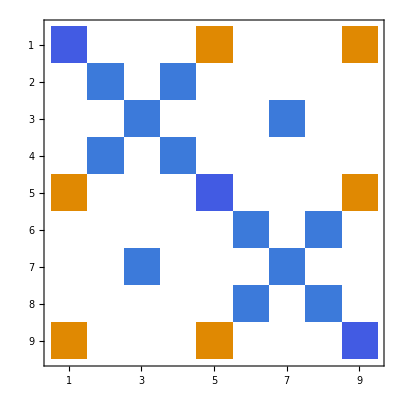

```mathematica
testQpQp[{
{1, 1, 1}
}, 
{
{1, 1, 1}
}]//ArrayReshape[#, {9, 9}]&//MatrixPlot
```

```mathematica
testQQQ[{
{1, 1, 1, 1, 1, 1}
}, 
{
{1, 1, 1, 1, 1, 2}
}]
```

```mathematica
testIpQQp[{
{1, 1, 1, 1, 1, 1}
}, 
{
{1, 1, 1, 1, 1, 1}
}]+testpQQp[{
{1, 1, 1, 1, 1, 1}
}, 
{
{1, 1, 1, 1, 1, 1}
}]//Chop
```

```mathematica
testIpQQp[{
{1, 1, 1, 1, 1, 1}
}, 
{
{1, 1, 1, 1, 1, 1}
}]//Chop
```

##### Check State Matrices

```mathematica
meh=Import["/Users/Mark/Desktop/bleh.dat", "Table"];
sts=1+Import["/Users/Mark/Desktop/states.dat", "Table"]//Floor;
```

```mathematica
AllTrue[
Range[ 1, Length[sts]],
Abs[Max[
Flatten[
ArrayReshape[
meh[[#]],
{6*6, 6*6}
]-ArrayReshape[
testIpQQp[sts[[{11}]], sts[[{#}]]],
{36,36}
]
]
]
]<10^-15&
]
```

True

```mathematica
Manipulate[
Grid@List@{
ArrayReshape[
meh[[i]],
{6*6, 6*6},
ImageSize->250
]//MatrixPlot,
ArrayReshape[
testIpQQp[sts[[{2}]], sts[[{i}]]],
{36,36},
ImageSize->250
]//MatrixPlot
},
{i, 1, Length[sts], 1}
]
```

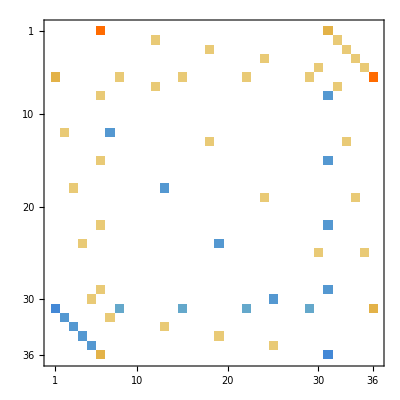

```mathematica
ArrayReshape[
testIpQQp[sts[[{2}]], sts[[{7}]]],
{36,36}
]//MatrixPlot
```

```mathematica
2
```

```mathematica
Table[
Check[
testQQQQ[sts[[{1}]], sts[[{i}]]];Nothing,
Throw@i
],
{i, Length[sts]}
]
```

$Aborted

```mathematica
sts[[90]]
```

{5,1,1,1,1,1}

```mathematica
Do[
Block[{a, b},
a=ArrayReshape[
testQQQQ[sts[[{1}]], sts[[{i}]]],
{6*6, 6*6}
];
b=ArrayReshape[
meh[[i]],
{6*6, 6*6}
];
If[Max[Threshold@Abs[a-b]]>0,
Throw@Grid@{
{
i, 
MatrixPlot[a-b, ImageSize->250]
},
{
MatrixPlot[a, ImageSize->250], 
MatrixPlot[b, ImageSize->250]
}
}
]
],
{i, Length[sts]}
]//Catch
```

```mathematica
ArrayReshape[
testQQQQ[
states6[[{1}]], 
states6[[{8}]]
],
{6*6,6*6}
]//MatrixPlot
```

-Graphics-

```mathematica
{{0,0}},{2,3},{{1,1}},{{1,1}},{1,1,1,1}
```

```mathematica
{
states6[[{1}]], 
states6[[{8}]]
}//Column
```

{{1,1,1,1,1,1}}
{{1,1,1,1,2,3}}

```mathematica
testQQQQ[
states6[[{1}]], 
states6[[{8}]]
][[1, 1, 1]]//MatrixForm
```

(0.75 | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.353553)

```mathematica
ArrayReshape[
testQQQQ[
states6[[{1}]], 
states6[[{8}]]
],
{6*6,6*6}
]//MatrixForm
```

(0.75 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553
0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.75 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553
0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0.
0. | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0.25 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0 | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0.
0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.75 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553
0. | 0 | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0.
0. | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0.25 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0.
0. | 0 | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.75 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0 | 0 | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0 | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0.
0. | 0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0.
0. | 0 | 0 | 0. | 0. | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.353553 | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0. | 0. | 0. | 0.353553 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.12132)

```mathematica
ArrayReshape[
testpQQp[{
{1, 1, 1, 1, 1, 1}
}, 
{
{1, 1, 1, 1, 1, 1}
}],
{6,6,6,6}
]//Map[MatrixForm, #, {2}]&//Grid
```

(-0.75 | 0. | 0. | 0. | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.
0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0. | 0. | 0. | -0.25) | (0. | -0.25 | 0. | 0. | 0. | 0.
-0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0 | 0 | 0
0. | 0. | 0 | 0. | 0 | 0
0. | 0. | 0 | 0 | 0. | 0
0. | 0. | 0 | 0 | 0 | 0.) | (0. | 0. | -0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0 | 0 | 0
-0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0 | 0. | 0. | 0 | 0
0. | 0 | 0. | 0 | 0. | 0
0. | 0 | 0. | 0 | 0 | 0.) | (0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | 0 | 0. | 0 | 0
0. | 0 | 0. | 0. | 0 | 0
-0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0 | 0 | 0. | 0. | 0
0. | 0 | 0 | 0. | 0 | 0.) | (0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0 | 0 | 0. | 0
0. | 0 | 0. | 0 | 0. | 0
0. | 0 | 0 | 0. | 0. | 0
-0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0 | 0 | 0 | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | -0.25
0. | 0. | 0 | 0 | 0 | 0.
0. | 0 | 0. | 0 | 0 | 0.
0. | 0 | 0 | 0. | 0 | 0.
0. | 0 | 0 | 0 | 0. | 0.
-0.25 | 0. | 0. | 0. | 0. | 0.)
(0. | -0.25 | 0. | 0. | 0. | 0.
-0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0 | 0 | 0
0. | 0. | 0 | 0. | 0 | 0
0. | 0. | 0 | 0 | 0. | 0
0. | 0. | 0 | 0 | 0 | 0.) | (-0.25 | 0. | 0. | 0. | 0. | 0.
0. | -0.75 | 0. | 0. | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.
0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0. | 0. | 0. | -0.25) | (0. | 0. | 0. | 0 | 0 | 0
0. | 0. | -0.25 | 0. | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0 | 0
0 | 0. | 0. | 0 | 0. | 0
0 | 0. | 0. | 0 | 0 | 0.) | (0. | 0. | 0 | 0. | 0 | 0
0. | 0. | 0. | -0.25 | 0. | 0.
0 | 0. | 0. | 0. | 0 | 0
0. | -0.25 | 0. | 0. | 0. | 0.
0 | 0. | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0 | 0.) | (0. | 0. | 0 | 0 | 0. | 0
0. | 0. | 0. | 0. | -0.25 | 0.
0 | 0. | 0. | 0 | 0. | 0
0 | 0. | 0 | 0. | 0. | 0
0. | -0.25 | 0. | 0. | 0. | 0.
0 | 0. | 0 | 0 | 0. | 0.) | (0. | 0. | 0 | 0 | 0 | 0.
0. | 0. | 0. | 0. | 0. | -0.25
0 | 0. | 0. | 0 | 0 | 0.
0 | 0. | 0 | 0. | 0 | 0.
0 | 0. | 0 | 0 | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.)
(0. | 0. | -0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0 | 0 | 0
-0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0 | 0. | 0. | 0 | 0
0. | 0 | 0. | 0 | 0. | 0
0. | 0 | 0. | 0 | 0 | 0.) | (0. | 0. | 0. | 0 | 0 | 0
0. | 0. | -0.25 | 0. | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0 | 0
0 | 0. | 0. | 0 | 0. | 0
0 | 0. | 0. | 0 | 0 | 0.) | (-0.25 | 0. | 0. | 0. | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.
0. | 0. | -0.75 | 0. | 0. | 0.
0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0. | 0. | 0. | -0.25) | (0. | 0 | 0. | 0. | 0 | 0
0 | 0. | 0. | 0. | 0 | 0
0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.
0 | 0 | 0. | 0. | 0. | 0
0 | 0 | 0. | 0. | 0 | 0.) | (0. | 0 | 0. | 0 | 0. | 0
0 | 0. | 0. | 0 | 0. | 0
0. | 0. | 0. | 0. | -0.25 | 0.
0 | 0 | 0. | 0. | 0. | 0
0. | 0. | -0.25 | 0. | 0. | 0.
0 | 0 | 0. | 0 | 0. | 0.) | (0. | 0 | 0. | 0 | 0 | 0.
0 | 0. | 0. | 0 | 0 | 0.
0. | 0. | 0. | 0. | 0. | -0.25
0 | 0 | 0. | 0. | 0 | 0.
0 | 0 | 0. | 0 | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.)
(0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | 0 | 0. | 0 | 0
0. | 0 | 0. | 0. | 0 | 0
-0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0 | 0 | 0. | 0. | 0
0. | 0 | 0 | 0. | 0 | 0.) | (0. | 0. | 0 | 0. | 0 | 0
0. | 0. | 0. | -0.25 | 0. | 0.
0 | 0. | 0. | 0. | 0 | 0
0. | -0.25 | 0. | 0. | 0. | 0.
0 | 0. | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0 | 0.) | (0. | 0 | 0. | 0. | 0 | 0
0 | 0. | 0. | 0. | 0 | 0
0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.
0 | 0 | 0. | 0. | 0. | 0
0 | 0 | 0. | 0. | 0 | 0.) | (-0.25 | 0. | 0. | 0. | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.
0. | 0. | 0. | -0.75 | 0. | 0.
0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0. | 0. | 0. | -0.25) | (0. | 0 | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0
0 | 0 | 0. | 0. | 0. | 0
0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0. | -0.25 | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.) | (0. | 0 | 0 | 0. | 0 | 0.
0 | 0. | 0 | 0. | 0 | 0.
0 | 0 | 0. | 0. | 0 | 0.
0. | 0. | 0. | 0. | 0. | -0.25
0 | 0 | 0 | 0. | 0. | 0.
0. | 0. | 0. | -0.25 | 0. | 0.)
(0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0 | 0 | 0. | 0
0. | 0 | 0. | 0 | 0. | 0
0. | 0 | 0 | 0. | 0. | 0
-0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0 | 0 | 0 | 0. | 0.) | (0. | 0. | 0 | 0 | 0. | 0
0. | 0. | 0. | 0. | -0.25 | 0.
0 | 0. | 0. | 0 | 0. | 0
0 | 0. | 0 | 0. | 0. | 0
0. | -0.25 | 0. | 0. | 0. | 0.
0 | 0. | 0 | 0 | 0. | 0.) | (0. | 0 | 0. | 0 | 0. | 0
0 | 0. | 0. | 0 | 0. | 0
0. | 0. | 0. | 0. | -0.25 | 0.
0 | 0 | 0. | 0. | 0. | 0
0. | 0. | -0.25 | 0. | 0. | 0.
0 | 0 | 0. | 0 | 0. | 0.) | (0. | 0 | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0
0 | 0 | 0. | 0. | 0. | 0
0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0. | -0.25 | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.) | (-0.25 | 0. | 0. | 0. | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.
0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | 0. | 0. | -0.75 | 0.
0. | 0. | 0. | 0. | 0. | -0.25) | (0. | 0 | 0 | 0 | 0. | 0.
0 | 0. | 0 | 0 | 0. | 0.
0 | 0 | 0. | 0 | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.25
0. | 0. | 0. | 0. | -0.25 | 0.)
(0. | 0. | 0. | 0. | 0. | -0.25
0. | 0. | 0 | 0 | 0 | 0.
0. | 0 | 0. | 0 | 0 | 0.
0. | 0 | 0 | 0. | 0 | 0.
0. | 0 | 0 | 0 | 0. | 0.
-0.25 | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0 | 0 | 0 | 0.
0. | 0. | 0. | 0. | 0. | -0.25
0 | 0. | 0. | 0 | 0 | 0.
0 | 0. | 0 | 0. | 0 | 0.
0 | 0. | 0 | 0 | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.) | (0. | 0 | 0. | 0 | 0 | 0.
0 | 0. | 0. | 0 | 0 | 0.
0. | 0. | 0. | 0. | 0. | -0.25
0 | 0 | 0. | 0. | 0 | 0.
0 | 0 | 0. | 0 | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.) | (0. | 0 | 0 | 0. | 0 | 0.
0 | 0. | 0 | 0. | 0 | 0.
0 | 0 | 0. | 0. | 0 | 0.
0. | 0. | 0. | 0. | 0. | -0.25
0 | 0 | 0 | 0. | 0. | 0.
0. | 0. | 0. | -0.25 | 0. | 0.) | (0. | 0 | 0 | 0 | 0. | 0.
0 | 0. | 0 | 0 | 0. | 0.
0 | 0 | 0. | 0 | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.25
0. | 0. | 0. | 0. | -0.25 | 0.) | (-0.25 | 0. | 0. | 0. | 0. | 0.
0. | -0.25 | 0. | 0. | 0. | 0.
0. | 0. | -0.25 | 0. | 0. | 0.
0. | 0. | 0. | -0.25 | 0. | 0.
0. | 0. | 0. | 0. | -0.25 | 0.
0. | 0. | 0. | 0. | 0. | -0.75)

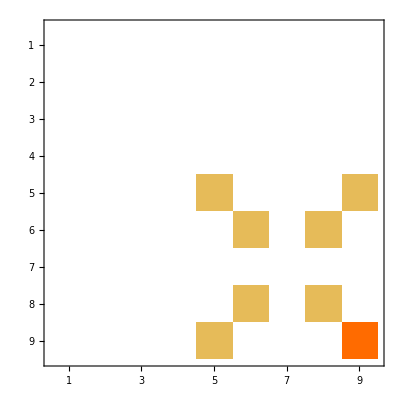

```mathematica
ArrayReshape[
testQQQQ[{
{1, 1, 1}
}, 
{
{1, 1, 1}
}],
{3*3, 3*3}
]//MatrixPlot
```

```mathematica
testQQQQ[{
{1, 1, 1,1,1,1}
}, 
{
{1, 1, 1,1,1,1}
}][[1]]//Map[MatrixForm, #, {2}]&//Grid
```

(0.75 | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.25) | (0. | 0.25 | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.)
(0. | 0.25 | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0.75 | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.25) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.)
(0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0.75 | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.25) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.)
(0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0.75 | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.25) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.)
(0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.) | (0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0.75 | 0.
0. | 0. | 0. | 0. | 0. | 0.25) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0.25 | 0.)
(0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.25
0. | 0. | 0. | 0. | 0.25 | 0.) | (0.25 | 0. | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0.75)

## State Orthogonality

We’ll consider

n  m = ∑_k (n  m)^(k)
= ∑_k ∑_(i=0)^k n^(k-i)  m^(i)

and by the recursive definition of n^(i) we have

(n  m)^(k) = ∑_(i=0)^k ∑_(s∈P(k-i)) ∑_(r∈P(i)) n^(0) (∏_(s_a∈s) ΔH_n^(s_a)Π_n)(∏_(r_b∈r) Π_m ΔH_m^(r_b))m^(0)

where P(k−i) is the set of permutations of integer partitions of k−i

Our goal will to be to find rules that allow every pair of sequences (s,r) to be at least partially canceled by another sequence

To do this, we will need a bit of helpful notation, first we will say

S^(k) = ΔH_n^(s_1)Π_n... ΔH_n^(s_k)Π_n
R^(j) = Π_m ΔH_m^(r_j)... Π_m ΔH_m^(r_1)

and then we’ll define the “reduced” sequences

S_-^(k) = ΔH_n^(s_1)Π_n... ΔH_n^(s_k)
R_-^(j) = ΔH_m^(r_j)... Π_m ΔH_m^(r_1)

we do this because we have two sequence rules that we can express in terms of these reduced sequences

First, any sequence S^(k) unpaired with an R^(j) can be expressed in terms of its reduced sequence and ΔE = E_n^(0)-E_m^(0)and vice versa

n^(0) S^(k)m^(0) = n^(0) S_-^(k)Π_n m^(0)
= 1/ΔE n^(0) S_-^(k)m^(0)
n^(0) R^(j)m^(0) = n^(0) Π_m R_-^(j)m^(0)
=-1/ΔEn^(0) R_-^(j)m^(0)

Second, by properties of the resolvent, for any paired sequence, we have

n^(0) S^(k)R^(j)m^(0) = n^(0) S_-^(k)Π_n Π_m R_-^(j)m^(0)
= 1/ΔE n^(0) S_-^(k)(Π_m-Π_n)R_-^(j)m^(0)
= 1/ΔE(n^(0) S_-^(k)R^(j)m^(0) - n^(0) S^(k)R_-^(j)m^(0))

We can look at this now with an instructive example

n^(0) ΔH_n^(1)Π_n ΔH_n^(2)Π_n ΔH_n^(1)Π_n m^(0) = 1/ΔE n^(0) ΔH_n^(1)Π_n ΔH_n^(2)Π_n ΔH_n^(1)m^(0)
n^(0) ΔH_n^(1)Π_n ΔH_n^(2)Π_n Π_m ΔH_m^(1)m^(0) = 1/ΔE[n^(0) ΔH_n^(1)Π_n ΔH_n^(2)Π_m ΔH_m^(1)m^(0)-n^(0) ΔH_n^(1)Π_n ΔH_n^(2)Π_n ΔH_m^(1)m^(0)]

This is low-key a pain to look at, we we’ll simplify notation once again and write

ΔH_λ^(i) = (i
λ)
Π_λ = ( 
λ)
H^(i) = (i
 )

Giving us

(1
n)( 
n)(2
n)( 
n)(1
n)( 
n) = 1/ΔE(1
n)( 
n)(2
n)( 
n)(1
n)
(1
n)( 
n)(2
n)( 
n)( 
m)(1
m) = 1/ΔE[(1
n)( 
n)(2
n)( 
m)(1
m) - (1
n)( 
n)(2
n)( 
n)(1
m)]

and we’ll note that the term (1
n)( 
n)(2
n)( 
n)(1
n) almost cancels -(1
n)( 
n)(2
n)( 
n)(1
m), and indeed from this we have sequence composition rule

S^(k)ΔH_n^(i)R^(j)-S^(k)ΔH_m^(i)R^(j) = (E_n^(i)-E_m^(i))S^(k)R^(j)

Why is this useful? Well we can write a reduced sequence as a product of a regular sequence and some ΔH_λ^(i)

S_-^(k)=S^(k-i)ΔH_n^(i)

and so generically we have

n^(0) S^(k)R^(j)m^(0) = 1/ΔE(n^(0) S^(k-λ)ΔH_n^(λ)R^(j)m^(0) - n^(0) S^(k)ΔH_m^(i)R^(j-i)m^(0))

then we’ll note that there is a corresponding term (for S^(k+i), assuming j>i)

n^(0) S^(k)ΔH_n^(i)Π_n R^(j-i)m^(0) = 1/ΔE(n^(0) S^(k)ΔH_n^(i)R^(j-i)m^(0) - n^(0) S^(k+i)ΔH_m^(l)R^(j-l)m^(0))

And so adding these two terms we have

n^(0) S^(k)R^(j)m^(0)+n^(0) S^(k)ΔH_n^(i)Π_n R^(j-i)m^(0) =
1/ΔE[n^(0) S^(k-λ)ΔH_n^(λ)R^(j)m^(0) - n^(0) S^(k+i)ΔH_m^(l)R^(j-l)m^(0) + (E_n^(i)-E_m^(i))n^(0) S^(k)R^(j-i)m^(0)]

and importantly we can add on terms that will lead to a similar reduction for the λ and l terms as well, with the caveat that we will eventually run into edge terms like

n^(0) S^(k+i)m^(0) = 1/ΔE n^(0) S^(k)ΔH_n^(i)m^(0)
n^(0) R^(j+i)m^(0) = -1/ΔEn^(0) ΔH_m^(i)R^(j)m^(0)

but even then, these will simply partially cancel with terms generated by other sequences

Next, we note that this occurs for every order i and every possible sequence S^(k) and R^(j), meaning we end up with

(n  m)^(k) =∑_(j=1)^k ∑_(i=0)^(k-j) (E_n^(j)-E_m^(j)) ∑_(s∈P(k-i-j)) ∑_(r∈P(i)) n^(0) (∏_(s_a∈s) ΔH_n^(s_a)Π_n)(∏_(r_b∈r) Π_m ΔH_m^(r_b))m^(0)

but that inner loop is the same as (n  m)^(j) meaning at the end of the day we have

(n m)^(k) = ∑_(i=1)^k (E_n^(i)-E_m^(i))(n m)^(k-i)

and if (n m)^(k−i) = 0 for i>0, inductively

(n m)^(k) = 0

## Operator Simplifications

nA m^(2) = n^(1)A^(0)m^(1) + n^(2)A^(0)m^(0) + n^(0)A^(0)m^(2)
= n^(1)A^(0)m^(1) + n^(1)ΔH_1 A^(0)m^(0) + c_20 n^(0)A^(0)m^(0)

We’ll consider

nA m^(k) = ∑_(i=0)^k ∑_(j=0)^i ∑_(s∈P(k-i-j)) ∑_(r∈P(i)) n^(0) (∏_(s_a∈s) ΔH_n^(s_a)Π_n)A^(j)(∏_(r_b∈r) Π_m ΔH_m^(r_b))m^(0)

which can be expanded out in terms of the sequences from above like

n^(0) S^(k)A^(i)R^(j)m^(0) = n^(0) S^(k)A^(i)Π_m ΔH_m^(a)R^(j-a)m^(0)
= n^(0) S^(k-b)ΔH_n^(b)Π_n A^(i)R^(j)m^(0)

and we can pair up these sequences like

n^(0) S^(k)A^(i)Π_m ΔH_m^(a)R^(j-a)m^(0) + n^(0) S^(k)ΔH_n^(a)Π_n A^(i)R^(j-a)m^(0)

ΔH_n^(a)Π_n A^(i) + A^(i)Π_m ΔH_m^(a) = H^(a)Π_n A^(i) + A^(i)Π_m H^(a) - (E_n^(a)Π_n A^(i)+E_m^(a)A^(i)Π_m)
H^(a)Π_n A^(i) + A^(i)Π_m H^(a) = ∑_k ((H^(a)k^(0)k^(0)A^(i))/(E_n-E_k) + (A^(i)k^(0)k^(0)H^(a))/(E_m-E_k))
= ∑_k (((V_a)_xk(A_a)_ky Q^a k^(0)k^(0)Q^a)/(E_n-E_k) + ((A_a)_nk(V_a)_km Q^a k^(0)k^(0)Q^a)/(E_m-E_k))
= ∑_k (((V_a)_xk(A_a)_ky)/(E_n-E_k) + ((A_a)_xk(V_a)_ky)/(E_m-E_k)) Q^a k^(0)k^(0)Q^a
= ∑_k (((V_a)_xk(A_a)_ky(E_m-E_k))/((E_n-E_k)(E_m-E_k)) + ((E_n-E_k)(A_a)_xk(V_a)_ky)/((E_n-E_k)(E_m-E_k))) Q^a k^(0)k^(0)Q^a

Next, assuming H^(a) and A^(i) operate on states in a similar manner (that is, they are both say 3rd order in the raising and lowering operators), then...IDK they’ll feed the same states into Π_m or something and so the same selection rules will apply???

We’ll assume specifically for the moment that

H^(a)=V_a⊙Q_a
A^(i) = A_a⊙Q_a

then

H^(a)Π_n A^(i) + A^(i)Π_m H^(a) = V_a⊙(Q_a/(E_n-E_m))

Therefore, every sequence will have a set of partner sequences given by different values of a and b

{n^(0) S^(k)A^(i)R^(j)m^(0), n^(0) S^(k-b)A^(i+b)R^(j)m^(0), n^(0) S^(k)A^(i+a)R^(j-a)m^(0)}

and in particular we will have terms that look like

n^(0) S^(k)(A^(i)Π_m ΔH_m^(a) + A^(i+a))R^(j-a)m^(0)

and notably, if

where

n^(0) S^(k)R^(j)m^(0) = n^(0) S_-^(k)Π_n Π_m R_-^(j)m^(0)
= 1/ΔE n^(0) S_-^(k)(Π_m-Π_n)R_-^(j)m^(0)
= 1/ΔE(n^(0) S_-^(k)R^(j)m^(0) - n^(0) S^(k)R_-^(j)m^(0))

#### Diagonal Terms

n^(0) ΔH^(1)Π_n H^(0)Π_m ΔH^(1)m^(0) = n^(0) H^(1)Π_n H^(0)Π_m H^(1)m^(0)
= n^(0) (V_3)_xyz⊙(Q^3)_xyz(1/(W_v⊙(Δ_3)_vxyz))H^(0)(V_3)_xyz⊙(Q^3)_xyz(1/(W_v⊙(Δ_3)_vxyz))Π_m H^(1)m^(0)

Note that every path we do on the left has a corresponding path on the right and all of those are treated identically until we get to H^(0), where we filter by state, which allows us to filter out by the admissible paths, which are the ones that account for the difference in quantum numbers between n and m

If, however, we want to transform entire spaces, i.e. we want the space of all m that differ from n by two quantum numbers, we can do this somewhat differently, as we know the transform H^(1)

We can get a bit further with diagonal operators

n^(0) S_-^(k)Π_n H^(0)Π_m R_-^(j)m^(0) = n^(0) S_-^(k)Π_n Π_m H^(0)R_-^(j)m^(0)
= 1/ΔE[n^(0) S_-^(k)Π_n H^(0)R_-^(j)m^(0) - n^(0) S_-^(k)Π_m H^(0)R_-^(j)m^(0)]
= 1/ΔE[n^(0) S^(k)H^(0)R_-^(j)m^(0) - n^(0) S_-^(k)H^(0)R^(j)m^(0)]

## Lattice Paths / Raising-Lowering Relations

We can encode any string of raising/lowering operations as a lattice paths on a diagonal grid, for instance, here are the paths of length 16 that have value 6 after 8 steps

```mathematica
quickBlock[8, 2]
```

-Graphics-

For any two blocks that meet at a point, we can express the total polynomial from the combination of those paths as the product of two polynomial terms, e.g. for the block above the total polynomial for those paths is K_3^5(n)K_3^5(n), where K_b^a indicates that we have gone up a steps and down b steps

Naturally, from this we see that to get the total polynomial over these 16 steps, we can add up the polynomials induced by each point in the center (and in fact we can add up the polynomials induced by any column), giving us

K_8^8 = K_0^8(n)K_8^0(n) + K_1^7(n)K_7^1(n) + K_2^6(n)K_6^2(n) + ...
= ∑_(i=0)^8 K_i^(8-i)(n)K_(8-i)^i(n)

We can show, moreover, that

K_b^a(n) = (∑_(i=0)^(|a-b|/2) c_i^(a,b)n^i)Piecewise[{{∏_(j=1)^(a-b) √(n+j), a ≥b}, {∏_(j=0)^(b-a-1) √(n-j), a < b}}]

can be written more nicely as

K_b^a(n) = P_b^a(n)S_b^a(n)

where P_b^a is a polynomial of degree |a−b|/2 and S_b^a(n) is a product of |a−b| square roots

⟨n|μn+k = ⟨n^(2)|μ^(0)n+k^(0) + ⟨n^(1)|μ^(1)n+k^(0) + ⟨n^(1)|μ^(0)n+k^(1) + ...

⟨n^(1)|μ^(0)n+k^(1) = ⟨n^(0)|H^(1)Π_n μ^(0)Π_(n+k)H^(1)n+k^(0)

H^(1)Π_n μ^(0)Π_(n+k)H^(1) = (dV/(d q^3))q^3 Π_n(dμ/dq)qΠ_(n+k)(dV/(d q^3))q^3

H^(1)Π_n μ^(0)Π_(n+k)H^(1) = (dV/(d q^3))q^3 Π_n(dμ/dq)qΠ_(n+k)(dV/(d q^3))q^3

n^(0)On+k^(0) = ∑_(p∈diagrams(O,k)) (coeffs(O,p))/(energies(p))P_p^[O](n)

#### Alternate Recursion

Starting from

P_b^a = (n+a-b+1)P_(b-1)^a + P_b^(a-1)

Is this accurate?????

We can expand instead like

P_b^a = ∑_(i=0)^b (∏_(j=0)^i (n+(a-b+1)+j))P_(b-i)^(a-1)(n)

then if we express this in terms of the parameter z = n + (a−b+1) we get

P_b^a = ∑_(i=0)^b (∏_(j=0)^i (z+j))P_(b-i)^(a-1)(n)
= ∑_(i=0)^b ∑_(j=0)^i (-1)^(i-j)S_1(i, j)z^(j+1)P_(b-i)^(a-1)(n)

but I know the relevant parameter is n + (a−b+1)/2...so letting η = z − (a−b+1)/2 and for notation letting Δ = (a−b+1)/2

P_b^a = ∑_(i=0)^b (∏_(j=0)^i (z+j))P_(b-i)^(a-1)(n)
= ∑_(i=0)^b ∑_(j=0)^i (-1)^(i-j)S_1(i, j)(η+Δ)^(j+1)∑_(k=0)^(b-i) (c_k^(a-1, b-i)(η-Δ))^k
= ∑_(i=0)^b ∑_(j=0)^i ∑_(k=0)^(b-i) (-1)^(i-j)S_1(i, j) c_k^(a-1,b-i)( ∑_(y=0)^(j+1) (j+1
y)Δ^(j+1-y) η^j )(∑_(x=0)^k (k
x)(-1)^(k-x)Δ^(k-x)η^x)
= ∑_(i=0)^b ∑_(j=0)^i ∑_(k=0)^(b-i) (-1)^(i-j)S_1(i, j) c_k^(a-1,b-i)∑_(σ=0)^(k+j+1) η^σ∑_(τ=0)^σ (j+1
τ)Δ^(j+1-τ)(k
σ-τ)(-1)^(k-(σ-τ))Δ^(k-(σ-τ))
= ∑_(i=0)^b ∑_(j=0)^i ∑_(k=0)^(b-i) ∑_(σ=0)^(k+j+1)  c_k^(a-1, b-i)Δ^(k+j+1-σ)η^σ ((-1)^(i-j)S_1(i, j) ∑_(τ=0)^σ (-1)^(k-(σ-τ))(j+1
τ)(k
σ-τ))
= ∑_(σ=0)^(b+1) η^σ∑_(k=0)^b ∑_(i=0)^(b-k) ∑_(j=σ-k-1)^i   c_k^(a-1, b-i)Δ^(k+j+1-σ) ((-1)^(i-j)S_1(i, j) ∑_(τ=0)^σ (-1)^(k-(σ-τ))(j+1
τ)(k
σ-τ))

where S_1(i, -...) = 0

```mathematica
cc[a_,-1]:=0;
ugh[a_, b_, s_]:=
Sum[
Sum[
Sum[
cc[a-1, k]*Δ^(k+j+1-s)*(-1)^(i-j)*StirlingS1[i, j]
*Sum[(-1)^(k-(s-t))Binomial[j+1, t]*Binomial[k, s-t], {t, 0, s}],
{j, Max@{0, s-k-1}, i}
],
{i, 0, b-k}
],
{k, 0, b}
]
```

```mathematica
ugh[4, 3, 0]//CoefficientList[#, Δ]&
```

{0,cc[3,0],4 cc[3,0]-cc[3,1],4 cc[3,0]-2 cc[3,1]+cc[3,2],cc[3,0]-cc[3,1]+cc[3,2]-cc[3,3]}

```mathematica
ugh[3, 4, 1]
```

cc[2,0]+20 Δ cc[2,0]+45 Δ^2 cc[2,0]+28 Δ^3 cc[2,0]+5 Δ^4 cc[2,0]-4 Δ^2 cc[2,1]-8 Δ^3 cc[2,1]-3 Δ^4 cc[2,1]-Δ^2 cc[2,2]+Δ^4 cc[2,2]+2 Δ^3 cc[2,3]+Δ^4 cc[2,3]-3 Δ^4 cc[2,4]

```mathematica
Reduce@{
0≤i≤b,
0≤j≤i,
0≤k≤b-i,
0≤1≤k+j+1
}
```

```mathematica
With[{b=4},
Table[
Table[
Table[
Table[{i, j, k, s}, {s, 0, k+j+1}],
{k, 0, b-i}
],
{j, 0, i}],
{i, 0, b}
]
]//Flatten[#, 3]&//Sort//GatherBy[#, #[[-1]]&]&//Map[Map[Column@*SortBy[#[[3]]&]]@GatherBy[#, #[[1]]&]&]//Take[#, -3]&
```

{{{0,0,2,3}
{0,0,3,3}
{0,0,4,3},{1,1,1,3}
{1,0,2,3}
{1,1,2,3}
{1,0,3,3}
{1,1,3,3},{2,2,0,3}
{2,1,1,3}
{2,2,1,3}
{2,0,2,3}
{2,1,2,3}
{2,2,2,3},{3,2,0,3}
{3,3,0,3}
{3,1,1,3}
{3,2,1,3}
{3,3,1,3},{4,2,0,3}
{4,3,0,3}
{4,4,0,3}},{{0,0,3,4}
{0,0,4,4},{1,1,2,4}
{1,0,3,4}
{1,1,3,4},{2,2,1,4}
{2,1,2,4}
{2,2,2,4},{3,3,0,4}
{3,2,1,4}
{3,3,1,4},{4,3,0,4}
{4,4,0,4}},{{0,0,4,5},{1,1,3,5},{2,2,2,5},{3,3,1,5},{4,4,0,5}}}

```mathematica
Reduce[{
0≤i≤b,
0≤j≤i,
0≤k≤b-i,
0≤σ-k-1≤j
}]
```

```mathematica
With[{b=4},
Table[
Table[
Table[
Table[
{i, j, k, s}, 
{j, Max@{s-k-1, 0}, i}
],
{i, 0, b-k}
],
{k, 0, b}
],
{s, 0, b+1}
]
]//Flatten[#, 3]&//Sort//GatherBy[#, #[[-1]]&]&//Map[Map[Column@*SortBy[#[[3]]&]]@GatherBy[#, #[[1]]&]&]//Take[#, -3]&
```

{{{0,0,2,3}
{0,0,3,3}
{0,0,4,3},{1,1,1,3}
{1,0,2,3}
{1,1,2,3}
{1,0,3,3}
{1,1,3,3},{2,2,0,3}
{2,1,1,3}
{2,2,1,3}
{2,0,2,3}
{2,1,2,3}
{2,2,2,3},{3,2,0,3}
{3,3,0,3}
{3,1,1,3}
{3,2,1,3}
{3,3,1,3},{4,2,0,3}
{4,3,0,3}
{4,4,0,3}},{{0,0,3,4}
{0,0,4,4},{1,1,2,4}
{1,0,3,4}
{1,1,3,4},{2,2,1,4}
{2,1,2,4}
{2,2,2,4},{3,3,0,4}
{3,2,1,4}
{3,3,1,4},{4,3,0,4}
{4,4,0,4}},{{0,0,4,5},{1,1,3,5},{2,2,2,5},{3,3,1,5},{4,4,0,5}}}

```mathematica
{{0,0,4,5},{1,1,3,5},{2,2,2,5},{3,3,1,5},{4,4,0,5}}//Column
```

{0,0,4,5}
{1,1,3,5}
{2,2,2,5}
{3,3,1,5}
{4,4,0,5}

```mathematica
{{0,0,2,3},{0,0,3,3},{0,0,4,3},{1,0,2,3},{1,0,3,3},{1,1,1,3},{1,1,2,3},{1,1,3,3},{2,0,2,3},{2,1,1,3},{2,1,2,3},{2,2,0,3},{2,2,1,3},{2,2,2,3},{3,1,1,3},{3,2,0,3},{3,2,1,3},{3,3,0,3},{3,3,1,3},{4,2,0,3},{4,3,0,3},{4,4,0,3}}//SortBy[First]//Column
```

{0,0,2,3}
{0,0,3,3}
{0,0,4,3}
{1,0,2,3}
{1,0,3,3}
{1,1,1,3}
{1,1,2,3}
{1,1,3,3}
{2,0,2,3}
{2,1,1,3}
{2,1,2,3}
{2,2,0,3}
{2,2,1,3}
{2,2,2,3}
{3,1,1,3}
{3,2,0,3}
{3,2,1,3}
{3,3,0,3}
{3,3,1,3}
{4,2,0,3}
{4,3,0,3}
{4,4,0,3}

```mathematica
{{0,0,0,0},{0,0,1,0},{0,0,2,0},{0,0,3,0},{0,0,4,0},{1,0,0,0},{1,0,1,0},{1,0,2,0},{1,0,3,0},{1,1,0,0},{1,1,1,0},{1,1,2,0},{1,1,3,0},{2,0,0,0},{2,0,1,0},{2,0,2,0},{2,1,0,0},{2,1,1,0},{2,1,2,0},{2,2,0,0},{2,2,1,0},{2,2,2,0},{3,0,0,0},{3,0,1,0},{3,1,0,0},{3,1,1,0},{3,2,0,0},{3,2,1,0},{3,3,0,0},{3,3,1,0},{4,0,0,0},{4,1,0,0},{4,2,0,0},{4,3,0,0},{4,4,0,0}}//SortBy[{#[[-2]]&, #[[-3]]&}]//Column
```

{0,0,0,0}
{1,0,0,0}
{2,0,0,0}
{3,0,0,0}
{4,0,0,0}
{1,1,0,0}
{2,1,0,0}
{3,1,0,0}
{4,1,0,0}
{2,2,0,0}
{3,2,0,0}
{4,2,0,0}
{3,3,0,0}
{4,3,0,0}
{4,4,0,0}
{0,0,1,0}
{1,0,1,0}
{2,0,1,0}
{3,0,1,0}
{1,1,1,0}
{2,1,1,0}
{3,1,1,0}
{2,2,1,0}
{3,2,1,0}
{3,3,1,0}
{0,0,2,0}
{1,0,2,0}
{2,0,2,0}
{1,1,2,0}
{2,1,2,0}
{2,2,2,0}
{0,0,3,0}
{1,0,3,0}
{1,1,3,0}
{0,0,4,0}

```mathematica
Assuming[k∈Integers&&m∈Integers, (x+y)^4(x-y)^6//CoefficientList[#, x]&]
```

```mathematica
{y^10,-2 y^9,-3 y^8,8 y^7,2 y^6,-12 y^5,2 y^4,8 y^3,-3 y^2,-2 y,1}/.y->1
```

{1,-2,-3,8,2,-12,2,8,-3,-2,1}

```mathematica
Assuming[k∈Integers&&m∈Integers, (x+y)^2(x-y)^3//CoefficientList[#, x]&]
```

```mathematica
reducedPolyGen[3]/.{n->(m-(a-3+1)/2)}//FullSimplify//CoefficientList[#, m]&//FullSimplify
```

{0,-8+6 a,0,8}

```mathematica
Product[x+j, {j, 0, i}]
```

x Pochhammer[1+x,i]

```mathematica
1/2 (1+1) (1+2 n)
```

1+2 n

```mathematica
polyGen[3]//CoefficientList[#, n]&//Length
```

4

```mathematica
polyGenAlt[1]=1/2 (1+a) (a+2 n);
polyGenAlt[a_, b_]:=polyGenAlt[a, b]=FullSimplify[
Sum[
Product[, {j, 0, i}],
/.i->a
];
```

#### Action-Based Evaluation of P_b^a

We’ll assume that we can write

P_b^a=∑_(i=0)^a (n+i-(b-1))1/2^(b-1)(i+b-1
b-1)(P̃)_(b-1)^i(n+i)
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1)(n+i-(b-1))∑_(k=0)^(b-1) Q_k^(b-1)(i)n^k
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1) ∑_(k=0)^(b-1) (i-b+1)Q_k^(b-1)(i)n^k + Q_k^(b-1)(i)n^(k+1)
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1) ∑_(k=0)^b ((i-b+1)Q_k^(b-1)(i) + Q_(k-1)^(b-1)(i))n^k

```mathematica
With[{b=3},
(polyGen[b]/.{
n->(m+(a-b+1)/2)
})/.a->(1+2 c-b)
]//FullSimplify
```

1/6 c (-1+2 c) (1+2 c) (-4+2 c+m) (27+8 c^2+2 (-8+m) m+c (-29+8 m))

```mathematica
Solve[c==(a+b-1)/2, a]
```

{{a→1+2 c-b}}

We start with

c_k0^(b)= S_1(b, k)
s_lω^(b) = ∑_(j=l)^(ω+1)  S_2(ω, j)b/(b+j) S_1(j, l)
c_kl^(b)=∑_(ω=l)^(b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1) + c_(k-1ω)^(b-1))s_lω^(b)

and

(P̃)_b^a(n) = ∑_(k=0)^b (∑_(l=0)^(b-k) c_kl^(b)a^l)n^k

now we make the substitution

n = z - (a-b+1)/2
(P̃)_b^a(n) = ∑_(k=0)^b ∑_(l=0)^(b-k) c_kl^(b)(a^l(z - (a-b+1)/2))^k
= ∑_(k=0)^b ∑_(j=0)^k (∑_(l=0)^(b-k) c_kl^(b)(k
j)(a^l((a-b+1)/2))^(k-j))z^j
= ∑_(j=0)^b ∑_(k=j)^b (∑_(l=0)^(b-k) c_kl^(b)(k
j)(1/2)^(k-j)(a^l(a-b+1))^(k-j))z^j

and now expanding this out we get

∑_(k=j)^b (∑_(l=0)^(b-k) ∑_(ω=0)^(k-j) (-1)^(k-j-w)(b-1)^(k-j-w)c_kl^(b)(k
j)(k-j
ω)(1/2)^(k-j))a^(l+ω)

shifting by x = k − j

∑_(x=0)^(b-j) ∑_(l=0)^(b-x+j) ∑_(ω=0)^x (-1)^(x-w)(b-1)^(x-w)(x+j
j)(x
ω)(1/2)^x(c_(x+jl)^(b)a^(l+ω))

#### Generic Evaluation of P_b^a

##### Best Formula

For a > b we use

P_b^a(n) =(a+b
b) ∑_(ω=0)^b 1/2^ω ω!(b
ω)(a
ω)(n)_(b-ω)

```mathematica
ExportString[NotebookRead@PreviousCell[], "TeXFragment"]
```

```mathematica
2.825^-02
```

and alternately we have

P_a^b(n + (a-b)) = P_b^a(n)

We can make a combinatoric model of this where (a+b
b) is the total number of paths where we go up a steps and down b steps, ω!(b
ω)(a
ω) is a falling factorial connection coefficient which correspond to the numbers of ways to pull together ω raising/lowering operations, and the 1/2^ω is keeping us from over-counting as we would naturally double-count (and so recursively multiply) for each of the ω choices

```mathematica
"
  ::> M[2](0, 0, 0) ([-0.00228772])
    > prefactor: 1.061
    > coeffs: [array([1., 1.])]
    > contrib: -0.002426495603822034
  <::
  > -0.002426495603822034
"
```

```mathematica
"-2.28772199e-03"
```

```mathematica
-4.04415934*^-04/-2.28772199*^-03
```

0.176777

```mathematica
0.17677669566834037*Sqrt[2]
```

0.25

```mathematica
3/(2Sqrt[2.])
```

1.06066

```mathematica
"-4.04415934e-04"
```

```mathematica
"-4.04415934e-04"
```

```mathematica
"-5.06717599e-02   0.00000000e+00   0.00000000e+00   0.00000000e+00  -4.48221780e-04   4.34423641e-05   4.66746578e-04   1.77260946e-04  -1.08709459e-03  -2.66896880e-04"
```

```mathematica
0.00566/2
```

0.00283

```mathematica
"-2.09594939e-04   0.00000000e+00  -2.56171592e-04"
```

Reverse Direction

We know that for b > a

(P_-)_b^a(n) = P_a^b(n - (a-b))

where we simply switched the roles of a and b (so where b was originally the number of lowering operations, now it’s the number of raising operations) and so if b > a

P_b^a(n) = (a+b
b) ∑_(ω=0)^a 1/2^ω ω!(b
ω)(a
ω)(n-(a-b))_(a-ω)
= (a+b
b) ∑_(ω=0)^a 1/2^ω ω!(b
ω)(a
ω)∑_(j=0)^(a-ω) (b-a
ω)(b-a)_[a-ω-j](n)_j

Power Series Equivalent

For computational convenience it’s nice to maintain a power-series form so we’ll expand in the Stirling numbers as

```mathematica
polyGenDirect[5, 2]//Expand
```

105+84 n+21 n^2

```mathematica
polyGen[5, 2]//Expand
```

105+84 n+21 n^2

```mathematica
polyGenDirect[a_, b_]:=Binomial[a+b, a]*Sum[
w!/2^w *Binomial[b, w]*Binomial[a, w]*FactorialPower[n, b-w]//FunctionExpand,
{w, 0, b}
]
```

P_b^a(n) =(a+b
b) ∑_(ω=0)^b 1/2^ω ω!(b
ω)(a
ω)(n)_(b-ω)
=(a+b
b) ∑_(ω=0)^b 1/2^ω ω!(b
ω)(a
ω)∑_(j=0)^(b-ω) S_1(b-ω, j)n^j 
=(a+b
b) ∑_(j=0)^b ∑_(ω=0)^(b-j) 1/2^ω ω!(b
ω)(a
ω) S_1(b-ω, j)n^j
=(a+b
b) ∑_(j=0)^b (∑_(ω=0)^(b-j) 1/2^ω ω!(b
ω)(a
ω) S_1(b-ω, j)) n^j

```mathematica
polyGenCoeffs[a_, b_]:=Binomial[a+b, a]Table[
Sum[
w!/2^w *Binomial[b, w]*Binomial[a, w]*StirlingS1[b-w, j],
{w, 0, b-j}
],
{j, 0, b}
]
```

##### Setup

We can also note that this yields some nice recursions, in particular, assuming a > 1

K_1^a = K_0^a K_1^0(n+a) + K_1^(a-1)K_0^1(n+a-1)
= (n+a)S_0^(a-1)(n) + P_1^(a-1)(n)S_1^(a-1)(n)√(n+a)
= ((n+a) + P_1^(a-1))S_0^(a-1)(n)
= ((n+a) + P_1^(a-1))S_1^a(n)
⇒ P_1^a = (n+a) + P_1^(a-1)

K_2^a = K_1^a √(n+a-1) + K_2^(a-1)K_0^1(n+a-3)
= (n+a-1)P_1^a S_0^(a-2)(n) +P_2^(a-1)S_2^(a-1)√(n+a-2) 
= ((n+a-1)P_1^a +P_2^(a-1))S_0^(a-2)(n)
⇒ P_2^a = (n+a-1)P_1^a +P_2^(a-1)

And now (noting that P_0^a = 1) we can conjecture that for k < a

P_k^a = (n+a+1-k)P_(k-1)^a + P_k^(a-1)

which is in retrospect pretty obviously true

We can potentially make this better, by expanding out these recursions, but first we’ll need an expression for k > a, we start again with

K_a^1 = √(n-a+1)S_a^0 + P_(a-1)^1 S_(a-1)^1 √(n-a+2)
= (n-a+1)S_a^1 + P_(a-1)^1 S_a^1
⇒ P_a^1 = (n-a+1) + P_(a-1)^1

and we find

P_a^k = (n-a+k)P_a^(k-1) + P_(a-1)^k

and finally

P_k^k = (n+1)P_(k-1)^k + (n)P_k^(k-1)

so now we can start building our recursions, starting with P_1

P_1^a = (n+a) + P_(a-1)^1
⇒ P_1^a = ∑_(i=0)^a (n+i)
=1/2 (1+a) (2n+a)
P_a^1 = (n-(a-1)) + P_1^a
⇒ P_a^1 = ∑_(i=-1)^(a-1) (n-i)
=1/2 (1+a) (2(n+1)-a)

And now for P_2 we get

⇒ P_2^a = (n+a-1)(1/2(a+1)(a+2n)) + P_2^(a-1)
= (n+a-1)(1/2(a+1)(a+2n)) + (n+a-2)(1/2(a)(a-1+2n)) + P_2^(a-2)
= ∑_(i=0)^(a-3) 1/2(a-i+1)(a-i+2n)(a-i+n-1) + P_2^2
P_2^2 = (n+1)1/2(a-(a-2)+1)(a-(a-2)+2n) + (n)1/2 (1+2) (2(n+1)-2)
((= 1/2(a-i+1)(a-i+2n)(n+(a-i)-1)|)_(i=a-2) + 1/2 ((a-i)+1+1)(2n+(a-i)-1)(n+(a-i)-1)|)_(i=a-1)
P_2^2= ∑_(i=a-2)^(a-1) 1/2(a-i+1)(a-i+2n)(a-i+n-1) + 1/2 n(2n-2)
= ∑_(i=a-2)^a 1/2(a-i+1)(a-i+2n)(a-i+n-1)
P_2^a = ∑_(i=0)^a 1/2(a-i+1)(a-i+2n)(a-i+n-1)
= ∑_(i=0)^a 1/2(i+1)(i+2n)(i+n-1)
=1/8 (1+a) (2+a) (a^2+a(-1+4n)+4(-1+n)n)

Finally, for P_3 we have

P_3^a = (n+a-2)P_2^a + (n+(a-1)-2)P_2^(a-1) + ... + (n+(a-(a-4))-2)P_2^4 + P_3^3

Generically, we can generate these as polynomial expressions from

P_b^a=∑_(i=0)^a (n+i-(b-1))P_(b-1)^i(n)

where (P̃)_b^a(n) is a degree b polynomial in n and a 2b degree polynomial in a, given by

P_b^a(n) = ∑_(k=0)^b ∑_(l=0)^(2b-k) c_kl^(b)a^l n^k

Note that for the terms of degree k in n, we end up with a 2b−k degree polynomial in a, i.e. the sum of the polynomial degrees in a and n are equal to 2b, so we’ll reduce this one step further to

P_b^a(n) = ∑_(k=0)^b Q_k^(b)(a)n^k

Expanding this out, we get

P_b^a=∑_(i=0)^a (n+i-(b-1))∑_(k=0)^(b-1) Q_k^(b-1)(i)n^k
=∑_(i=0)^a (n+i-(b-1))∑_(k=0)^(b-1) Q_k^(b-1)(i)n^k
=∑_(i=0)^a  ∑_(k=0)^(b-1) (i-b+1)Q_k^(b-1)(i)n^k + Q_k^(b-1)(i)n^(k+1)
=∑_(i=0)^a ∑_(k=0)^b ((i-b+1)Q_k^(b-1)(i) + Q_(k-1)^(b-1)(i))n^k

```mathematica
Clear[polyGen];
polyGen[0]=1;
polyGen[1]=1/2 (1+a) (a+2 n);
polyGen[b_]:=polyGen[b]=FullSimplify[∑_(a=0)^i (n+a-b+1) polyGen[b-1]/.i->a];
reducedPolyGen[b_]:=polyGen[b] 2^b /Binomial[a+b, b]//Simplify;
polyGen[a_, b_]:=If[a==0||b==0,
1,
If[b>a,
polyGen[a]/.{
a->b,
n->(n+(a-b))
}//Expand,
polyGen[b]/.a->a
]
];
polyGen[a_, b_, shift_]:=
polyGen[a, b]/.n->n+shift;
polySqrtGen[a_, b_]:=
polyGen[a, b]*If[b>a,
Product[Sqrt[n-i], {i, 0, b-a-1}],
Product[Sqrt[n+i], {i, 1, a-b}]
];
polySqrtGen[a_, b_, shift_]:=
polySqrtGen[a, b]/.n->n+shift;
```

##### Cursed Attempt with the Bernoulli Numbers and Explicit Factorization

where polynomials that go out of bounds are uniformly zero, we can then swap our summation indices and expand the polynomials to give

P_b^a=∑_(k=0)^b ∑_(i=0)^a ((i-b+1)Q_k^(b-1)(i) + Q_(k-1)^(b-1)(i))n^k
=∑_(k=0)^b ∑_(i=0)^a ((i-(b-1))∑_(l=0)^(2b-k-1) c_kl^(b-1)i^l + ∑_(l=0)^(2b-k) c_(k-1l)^(b-1)i^l)n^k
=∑_(k=0)^b ∑_(i=0)^a (∑_(l=0)^(2b-k-1) (c_kl^(b-1)i^(l+1)-(b-1)c_kl^(b-1)i^l) + ∑_(l=0)^(2b-k) c_(k-1l)^(b-1)i^l)n^k
=∑_(k=0)^b ∑_(i=0)^a (∑_(l=0)^(2b-k) (c_(kl-1)^(b-1)-(b-1)c_kl^(b-1)+c_(k-1l)^(b-1))i^l)n^k

where c_(k -1)^(b-1)=c_(k 2b-k)^(b-1) = 0

Finally, we need to express all the i terms as a terms, which we do with another rearrangement (changing l to ω for ease of reading) and an application of the Bernoulli numbers

∑_(i=0)^a (∑_(l=0)^(2b-k) (c_(kl-1)^(b-1)-(b-1)c_kl^(b-1)+c_(k-1l)^(b-1))i^l) = (-(b-1)c_(k,0)^(b-1)+c_(k-1,0)^(b-1)) + ∑_(ω=0)^(2b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1)+c_(k-1ω)^(b-1))(∑_(i=1)^a i^ω)
= (-(b-1)c_(k,0)^(b-1)+c_(k-1,0)^(b-1)) +  ∑_(ω=0)^(2b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1)+c_(k-1ω)^(b-1))∑_(z=0)^ω ((ω)!)/(z!(ω+1-z)!)B_z^+a^(ω+1-z)

and all that is left is to rearrange the right-hand sum in powers of a as

∑_(ω=0)^(2b-k) ∑_(z=0)^ω (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1)+c_(k-1ω)^(b-1)) ((ω)!)/(z!(ω+1-z)!)B_z^+a^(ω+1-z) = ∑_(p=1)^(2b+1-k) ∑_(ω=p-1)^(2b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1)+c_(k-1ω)^(b-1)) ((ω)!)/((ω+1-p)!(p)!)B_(ω+1-p)^+a^p

and so

c_k0^(b) = -(b-1)c_(k,0)^(b-1)+c_(k-1,0)^(b-1)
c_kp^(b) =∑_(ω=p-1)^(2b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1)+c_(k-1ω)^(b-1)) ((ω)!)/((ω+1-p)!(p)!)B_(ω+1-p)^+
=∑_(ω=0)^(2b+1-(k+p)) (c_(k ω+p-2)^(b-1)-(b-1)c_(k ω+p-1)^(b-1)+c_(k-1ω+p-1)^(b-1)) ((ω+p-1)!)/((ω)!(p)!)B_ω^+
=∑_(ω=0)^(2b+1-(k+p)) (c_(k ω+p-2)^(b-1)-(b-1)c_(k ω+p-1)^(b-1)+c_(k-1ω+p-1)^(b-1)) ( ∏_(j=1)^(p-1) (ω+j)/(1+j))B_ω^+

and now we get to try to simplify these coefficient expressions, first off, it’s possible to see through a recurrence that c_k0^(b) is a Stirling number of the first kind

c_k0^(b) = S_1(b, k)

Next, we know empirically, Q_k^(b)(a) is proportional to (a+b
b) = 1/(b!)∏_(j=1)^b (a+j), and so we can iteratively divide these terms out, i.e. we can write

(Q̃)_k^(b)(a) =( (Q_k^(b)(a)/(a+1)) /(a+2))/...

This is possible using “synthetic division” which algorithmically can be defined recursively as

(∑_(k=0)^L c_k a^k)/(a+j) = ∑_(k=0)^(L-1) c_k^(j)a^k

where

c_(L-1)^(j) = c_L
c_k^(j) = c_(k+1)-j c_(k+1)^(j)

and if we let j=1 and iterate this process, we find that we get

(Q̃)_k^(b)(a) = ∑_(p=0)^b (c̃)_kp^(b)a^p

with

(c̃)_kp^(b) = ∑_(j=b+p-1)^(2b) (-1)^(j+p+1)S_2(j-p, b)c_kj^(b)
= ∑_(j=0)^(b+1-p) (-1)^(j+b+1)S_2(j+b-1, b)c_(kj+b+p-1)^(b)
= ∑_(j=0)^(b+1-p) (-1)^(j+b+1)S_2(j+b-1, b)(∑_(ω=0)^(b+2-(k+j+p)) (c_(k ω+j+b+p-3)^(b-1)-(b-1)c_(k ω+j+b+p-2)^(b-1)+c_(k-1ω+j+b+p-2)^(b-1)) ( ∏_(x=1)^(j+b+p-2) (ω+x)/(1+x))B_ω^+)

comparing this to the same with (b − 1)

(c̃)_kp^(b-1) = ∑_(j=0)^(b-p) (-1)^(j+b)S_2(j+b-2, b-1)(∑_(ω=0)^(b+1-(k+j+p)) (c_(k ω+j+b+p-4)^(b-2)-(b-2)c_(k ω+j+b+p-3)^(b-2)+c_(k-1ω+j+b+p-3)^(b-1)) ( ∏_(x=1)^(j+b+p-3) (ω+x)/(1+x))B_ω^+)

We’ll note that

S_2(j+b-1, b) = b S_2(j+b-2, b) + S_2(j+b-2, b-1)

and so

∑_(j=0)^(b+1-p) (-1)^(j+b+1)S_2(j+b-1, b)(...) =∑_(j=0)^(b+1-p) b S_2(j+b-2, b)(...) + (-1) ∑_(j=0)^(b-p) (-1)^(j+b)S_2(j+b-2, b-2)(...)

and then

∑_(ω=0)^(b+2-(k+j+p)) (...) ( ∏_(x=1)^(j+b+p-2) (ω+x)/(1+x))B_ω^+ = (...) ( ∏_(x=1)^(j+b+p-2) (b+2-(k+j+p)+x)/(1+x))B_(b+2-(k+j+p))^+ +  ∑_(ω=0)^(b+1-(k+j+p)) (...)((ω+j+b+p-2)/(j+b+p-1)) ( ∏_(x=1)^(j+b+p-3) (ω+x)/(1+x))B_ω^+

finally

(c_(k ω+j+b+p-4)^(b-2)-(b-1)c_(k ω+j+b+p-3)^(b-2)+c_(k-1ω+j+b+p-3)^(b-1)) - ((ω+j+b+p-2)/(j+b+p-1))(c_(k ω+j+b+p-3)^(b-1)-(b-1)c_(k ω+j+b+p-2)^(b-1)+c_(k-1ω+j+b+p-2)^(b-1)) = ???

(c̃)_kp^(b-1) + ∑_(j=0)^(b-p) (-1)^(j+b)S_2(j+b-2, b-2) ∑_(ω=0)^(b+1-(k+j+p)) (...)((ω+j+b+p-2)/(j+b+p-2)) ( ∏_(x=1)^(j+b+p-3) (ω+x)/(1+x))B_ω^+ = ∑_(□=□)^□ (...)()

```mathematica
With[{b=3},
Table[
Table[cdE[b, k, j], {j, 0, b-k}],
{k, 0, b}
]
]
```

{{0,-1/24,1/16,-1/48},{-1/3,3/8,-1/8},{1/2,-1/4},{-1/6}}

```mathematica
With[{b=3},
Table[
Table[cdE[b, k, j], {j, 0, b-k}],
{k, 0, b}
]
]
```

{{0,-1/24,1/16,-1/48},{-1/3,3/8,-1/8},{1/2,-1/4},{-1/6}}

```mathematica
With[{b=4},
Table[
Table[cdE[b, k, j], {j, 0, b-k}],
{k, 0, b}
]
]
```

{{0,-1/64,11/384,-1/64,1/384},{-1/4,13/48,-1/8,1/48},{11/24,-5/16,1/16},{-1/4,1/12},{1/24}}

```mathematica
CoefficientList[
CoefficientList[polyGen[4]/Product[a+j, {j, 4}], n],
a
]
```

{{0,-1/64,11/384,-1/64,1/384},{-1/4,13/48,-1/8,1/48},{11/24,-5/16,1/16},{-1/4,1/12},{1/24}}

```mathematica
Clear[cd]
cd[b_, k_, p_]:=Sum[
(-1)^(j+p+1)StirlingS2[j-p, b]*cp[b, k, j], 
{j, b+p-1, 2b}
];
cd2[b_, k_, p_]:=Sum[
(-1)^(j+b+1)StirlingS2[j+b-1, b]*cp[b, k, j+b+p-1], 
{j, 0, b+1-p}
];
cdE[b_, k_, p_]:=cd2[b, k, p]/.{
S1->StirlingS1,
Bb->positiveBernouliB,
sBb->scaledBernoulliB
}
```

```mathematica
With[{b=3},
Table[
Table[cd[b, k, i], {i, 0, b-k}]/.{
S1->StirlingS1,
Bb->positiveBernouliB,
sBb->scaledBernoulliB
},
{k,0, b}
]
]
```

{{0,1/24,-1/16,1/48},{1/3,-3/8,1/8},{-1/2,1/4},{1/6}}

```mathematica
With[{b=3},
Table[
Table[cd2[b, k, i], {i, 0, b-k}]/.{
S1->StirlingS1,
Bb->positiveBernouliB,
sBb->scaledBernoulliB
},
{k,0, b}
]
]
```

{{0,1/24,-1/16,1/48},{1/3,-3/8,1/8},{-1/2,1/4},{1/6}}

```mathematica
With[{b=5},
CoefficientList[
CoefficientList[
polyGen[b]/Product[a+j, {j, 1, b}],
n
],
a
]
]
```

{{0,1/160,-5/384,7/768,-1/384,1/3840},{1/5,-13/64,13/128,-5/192,1/384},{-5/12,5/16,-3/32,1/96},{7/24,-7/48,1/48},{-1/12,1/48},{1/120}}

```mathematica
With[{b=3}, Table[cp[b, 0, i], {i, 0, 2b}]]/.{
S1->StirlingS1,
Bb->positiveBernouliB,
sBb->scaledBernoulliB
}
```

{0,1/4,1/12,-5/16,-5/48,1/16,1/48}

```mathematica
polyGen[3]//CoefficientList[#, n]&//CoefficientList[#, a]&
```

{{0,1/4,1/12,-5/16,-5/48,1/16,1/48},{2,17/12,-11/8,-13/24,3/8,1/8},{-3,-4,-1/4,1,1/4},{1,11/6,1,1/6}}

```mathematica
With[{b=3}, Table[cp[b, 0, i], {i, 0, 2b}]]/.{
S1->StirlingS1,
Bb->positiveBernouliB,
sBb->scaledBernoulliB
}
```

{0,1/4,1/12,-5/16,-5/48,1/16,1/48}

```mathematica
Clear[cp];
cp[0, 0, 0]=1;
cp[b_, -1, _]:=0;
cp[-1, k_, _]:=0
cp[b_, k_, 0]:=-(b-1)cp[b-1, k, 0] + cp[b-1, k-1, 0];
cp[b_, k_, 0]:=S1[b, k];
cp[b_, k_, p_]:=If[
p+k≥2(b+1)||p<0,
0,
 Sum[
(cp[(b-1), k, w-1]-(b-1)cp[b-1, k, w] + cp[b-1, k-1, w])*
sBb[w, p],
{w, p-1, 2b-k}
]
];
Bb[0]=1;
sBb[i_, i_]:=Bb[1];
sBb[i_, 1]:=Bb[i];
sBb[i_, j_]/;j==i+1:=If[j==2, Bb[1], 1/j];
sBb[j_, i_]/;j==i+1:=If[j==2, Bb[2], Bb[1]*Bb[2]*(j)];
positiveBernouliB[k_]:=(-1)^k BernoulliB[k];
scaledBernoulliB[w_, p_]:=(w!)/((w-p+1)!p!)positiveBernouliB[w-p+1]
```

```mathematica
cdp[]
```

```mathematica
Clear[divCoeffs];
divC[CC_, L_, j_][k_]:=Which[
k>=L||k<0, 0,
k==L-1, CC[L],
True,CC[k+1]-j divC[CC, L, j][k+1]//Simplify
];
divIter[CC_, L_, n_]:=
Fold[divC[#, L-#2+1, #2]&, CC, Range[n] ];
divCoeffs[L_, n_]:=
With[{di=divIter[C, L, n]},
CoefficientList[
Table[di[k], {k, 1, L-n}]/.C[x_]:>c^x,
c
]
]
```

```mathematica
divCoeffs[10, 5]
```

{{0,0,0,0,0,0,1,-15,140,-1050,6951},{0,0,0,0,0,0,0,1,-15,140,-1050},{0,0,0,0,0,0,0,0,1,-15,140},{0,0,0,0,0,0,0,0,0,1,-15},{0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
StirlingS2[Range[10], 5]
```

{0,0,0,0,1,15,140,1050,6951,42525}

```mathematica
divIter[CC, 6, 3][3]
```

CC[6]

```mathematica
divIter[CC, 5, 3][1]
```

CC[4]-6 CC[5]

```mathematica
divIter[CC, 5, 3][1]
```

CC[4]-6 CC[5]

```mathematica
iterat
```

```mathematica
divC[divC[divC[CC, 6, 1], 5, 2], 4, 3][2]//FullSimplify
```

CC[5]-6 CC[6]

```mathematica
divC[divC[divC[CC, 6, 1], 5, 2], 4, 3][1]//FullSimplify
```

CC[4]-6 CC[5]+25 CC[6]

```mathematica
divC[divC[divC[CC, 5, 1], 4, 2], 3, 3][1]
```

CC[4]-6 CC[5]

```mathematica
divC[divC[divC[CC, 5, 1], 4, 2], 3, 3][0] //FullSimplify
```

CC[3]-6 CC[4]+25 CC[5]

```mathematica
With[{b=1},
Table[
Table[cp[b, k, p], {p, 0, 2b-k}],
{k, 0,b}
]
][[1]]
```

{S1[1,0],Bb[1],Bb[1]}

```mathematica
With[{b=2},
Table[
Table[cp[b, k, p], {p, 0, 2b-k}],
{k, 0,b}
]
][[1]]//Simplify
```

{S1[2,0],-Bb[1]^2-S1[1,0]+Bb[1] (Bb[3]+S1[1,0]),Bb[1] (Bb[1] (-1+3 Bb[2])+S1[1,0]),Bb[1]^2,Bb[1]/4}

```mathematica
With[{b=3},
Table[
Table[cp[b, k, p], {p, 0, 2b-k}],
{k, 0,b}
]
][[1]]//Simplify
```

{S1[3,0],2 Bb[1]^3+Bb[1]^2 (Bb[2]-6 Bb[2]^2-5 Bb[3]+3 Bb[2] Bb[3]+Bb[4]-2 S1[1,0])-Bb[2] S1[1,0]-2 S1[2,0]+Bb[1] (-Bb[4]/2+Bb[5]/4+Bb[2] (Bb[3]-S1[1,0])+2 S1[1,0]+Bb[3] S1[1,0]+S1[2,0]),1/4 Bb[1] (12 Bb[1]^2 (1-5 Bb[2]+3 Bb[2]^2)+4 S1[1,0]+4 S1[2,0]-4 Bb[1] (Bb[3]-3 (-1+Bb[2]) S1[1,0]-sBb[4,2])-2 sBb[4,2]+sBb[5,2]),1/12 (12 Bb[1]^3 (-3+7 Bb[2])-4 S1[1,0]+Bb[1]^2 (4-48 Bb[2]+12 S1[1,0])+Bb[1] (4 Bb[3]-4 S1[1,0]+3 sBb[5,3])),1/4 Bb[1] (4 Bb[1]^2+Bb[1] (-5+8 Bb[2])+S1[1,0]),1/20 Bb[1] (-2+9 Bb[1]),Bb[1]/24}

```mathematica
Bb[1]
```

```mathematica
Clear[cp];
cp[0, 0, 0]=1;
cp[b_, -1, _]:=0;
cp[-1, k_, _]:=0
cp[b_, k_, 0]:=-(b-1)cp[b-1, k, 0] + cp[b-1, k-1, 0];
cp[b_, k_, 0]:=S1[b, k];
cp[b_, k_, p_]:=If[
p+k≥2(b+1)||p<0,
0,
 Sum[
(cp[(b-1), k, w-1]-(b-1)cp[b-1, k, w] + cp[b-1, k-1, w])*
sBb[w, p],
{w, p-1, 2b-k}
]
];
Bb[0]=1;
sBb[i_, i_]:=Bb[1];
sBb[i_, 1]:=Bb[i];
sBb[i_, j_]/;j==i+1:=If[j==2, Bb[1], 1/j];
sBb[j_, i_]/;j==i+1:=If[j==2, Bb[2], Bb[1]*Bb[2]*(j)];
positiveBernouliB[k_]:=(-1)^k BernoulliB[k];
scaledBernoulliB[w_, p_]:=(w!)/((w-p+1)!p!)positiveBernouliB[w-p+1]
```

P_b^a(n) = ∑_(k=0)^(b+1) ∑_(l=0)^(2b+1-k) c_kl^(b)a^l n^k

```mathematica
Table[scaledBernoulliB[i, 1], {i, 5}]
```

```mathematica
Table[scaledBernoulliB[i, 1], {i, 5}]
```

{1/2,1/6,0,-1/30,0}

```mathematica
B[1]
```

-1/2

```mathematica
scaledBernoulliB[1, 0]
```

1/12

```mathematica
scaledBernoulliB[0, 1]
```

1

```mathematica
With[{b=1},
Table[
Table[cp[b, k, p], {p, 0, 2b+1-k}],
{k, b+1}
]
]
```

```mathematica
Table[cp[3, i, 0], {i, 3}]
```

{2,-3,1}

```mathematica
Table[StirlingS1[3, i], {i, 3}]
```

{2,-3,1}

```mathematica
With[{b=3, k=2},
Table[
Table[{w, z, w+1-z}, {z, 0, w}],
{w, 0, 2b-k}
]
]//Catenate//Sort
```

{{0,0,1},{1,0,2},{1,1,1},{2,0,3},{2,1,2},{2,2,1},{3,0,4},{3,1,3},{3,2,2},{3,3,1},{4,0,5},{4,1,4},{4,2,3},{4,3,2},{4,4,1}}

```mathematica
With[{b=3, k=2},
Table[
Table[{w, w+1-p, p}, {w, p-1, 2b-k}],
{p, 1, 2b+1-k}
]
]//Catenate//Sort
```

{{0,0,1},{1,0,2},{1,1,1},{2,0,3},{2,1,2},{2,2,1},{3,0,4},{3,1,3},{3,2,2},{3,3,1},{4,0,5},{4,1,4},{4,2,3},{4,3,2},{4,4,1}}

```mathematica
Solve[w+1-z==p, z]
```

{{z→1-p+w}}

∑_(z=0)^ω ((ω)!)/(z!(l+1-z)!)B_z^+a^(ω-z+1)

```mathematica
CoefficientList[polyGen[4], n]//Length
```

5

```mathematica
Map[Length]@
CoefficientList[
CoefficientList[polyGen[4], n],
a
]
```

{9,8,7,6,5}

##### Successful Attempt with Stirling Numbers over the Falling Factorials

Generically, we can generate these as a polynomial expression that looks like

P_b^a=1/2^b(a+b
b) (P̃)_b^a(n)

where (P̃)_b^a(n) is a degree-b polynomial in n and an degree-b polynomial in a, given by

(P̃)_b^a(n) = ∑_(k=0)^b ∑_(l=0)^(b-k) c_kl^(b)a^l n^k

Note that for the terms of degree k in n, we end up with a b+1−k degree polynomial in a, i.e. the sum of the polynomial degrees in a and n are equal to b+1, so we’ll reduce this one step further to

(P̃)_b^a(n) = ∑_(k=0)^b Q_k^(b)(a)n^k

where Q_k^(b) is a degree b−k polynomial

P_b^a=∑_(i=0)^a (n+i-(b-1))1/2^(b-1)(i+b-1
b-1)(P̃)_(b-1)^i(n)
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1)(n+i-(b-1))∑_(k=0)^(b-1) Q_k^(b-1)(i)n^k
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1) ∑_(k=0)^(b-1) (i-b+1)Q_k^(b-1)(i)n^k + Q_k^(b-1)(i)n^(k+1)
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1) ∑_(k=0)^b ((i-b+1)Q_k^(b-1)(i) + Q_(k-1)^(b-1)(i))n^k

Next, we’ll note that we have the total recursion

P_b^a=∑_(i=0)^a (n+i-(b-1))1/2^(b-1)(i+b-1
b-1)(P̃)_(b-1)^i(n)
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1)(n+i-(b-1))∑_(k=0)^(b-1) Q_k^(b-1)(i)n^k
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1) ∑_(k=0)^(b-1) (i-b+1)Q_k^(b-1)(i)n^k + Q_k^(b-1)(i)n^(k+1)
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1) ∑_(k=0)^b ((i-b+1)Q_k^(b-1)(i) + Q_(k-1)^(b-1)(i))n^k

We’ll then note that we can freely rearrange this sum to give (where c_-1^(b-1) = c_b^(b-1) = 0 and ...)

P_b^a=1/2^(b-1)∑_(k=0)^b ∑_(i=0)^a (i+b-1
b-1) ((i-b+1)Q_k^(b-1)(i) + Q_(k-1)^(b-1)(i))n^k
=1/2^(b-1)∑_(k=0)^b ∑_(i=0)^a (i+b-1
b-1) ((i-b+1)∑_(l=0)^(b-1-k) c_kl^(b-1)i^l + ∑_(l=0)^(b-1-(k-1)) c_(k-1l)^(b-1)i^l)n^k
=1/2^(b-1)∑_(k=0)^b ∑_(i=0)^a (i+b-1
b-1) (∑_(l=0)^(b-1-k) c_kl^(b-1)i^(l+1)-(b-1)c_kl^(b-1)i^l + ∑_(l=0)^(b-k) c_(k-1l)^(b-1)i^l)n^k
=1/2^(b-1)∑_(k=0)^b ∑_(i=0)^a (i+b-1
b-1) (∑_(l=0)^(b-k) (c_(kl-1)^(b-1)-(b-1)c_kl^(b-1) + c_(k-1l)^(b-1))i^l)n^k

where, now c_(k -1)^(b-1) =c_(k b-k+1)^(b-1)=0

Focussing on the interior of this, we can move the sum over i inside as

∑_(i=0)^a (i+b-1
b-1) (∑_(l=0)^(b-k) (c_(kl-1)^(b-1)+c_(k-1l)^(b-1)-(b-1)c_kl^(b-1))i^l) = ∑_(l=0)^(b-k) (c_(kl-1)^(b-1)+c_(k-1l)^(b-1)-(b-1)c_kl^(b-1))∑_(i=0)^a (i+b-1
b-1) i^l

which we’ll express in terms of the rising factorials through the use of the Stirling numbers of the second kind, as this sum can be handled very cleanly analytically (for ω > 0)

∑_(i=0)^a (i+b-1
b-1)i^ω = ∑_(i=0)^a (i+b-1
b-1)∑_(j=0)^ω S_2(ω, j+1)∏_(x=0)^j (i-x)
= ∑_(i=0)^a 1/((b-1)!)∑_(j=0)^ω S_2(ω, j+1)∏_(x=-j)^(b-1) (i+j)
= 1/((b-1)!)∑_(j=0)^ω S_2(ω, j+1)∑_(i=0)^a ∏_(x=-j)^(b-1) (i+x)
= 1/((b-1)!)∑_(j=0)^ω S_2(ω, j+1)1/(b+1+j)((a+b)!)/((a-(j+1))!)
= ∑_(j=0)^ω S_2(ω, j+1)b/(b+1+j)((a+b)!)/(b!a!)∏_(x=0)^j (a-x)
= (a+b
b)∑_(j=0)^ω S_2(ω, j+1)b/(b+1+j)∏_(x=0)^j (a-x)
=  (a+b
b)∑_(j=0)^ω S_2(ω, j+1)b/(b+j+1)∑_(l=1)^(j+1) S_1(j+1, l)a^l

Which we can express in terms of a^l as [Note that I fucked with the expression a bit after checking against the code--RHS is fine] [Also note that this expression involving S_2 and S_1 would have been the identity if not for the b/(b+j+1) term → a sign that this could probably be done with matrix transforms between the rising and falling factorial bases]

∑_(j=0)^ω ∑_(l=1)^(j+1) S_2(ω, j)b/(b+j+1) S_1(j+1, l)a^l =∑_(l=1)^ω (∑_(j=l)^(ω+1)  S_2(ω, j)b/(b+j) S_1(j, l))a^l

To do this for all possible choices of ω, we can recognize this as the matrix transform

A^(b)=S_2(b/(b+j))S_1

where (b/(b+j)) is the diagonal matrix constructed by taking j to be the appropriate row/column

The upshot of this is twofold, first off this shows that we’re really just transforming from plain polynomials to rising factorials, scaling by b/b+j, and transforming back, second, this can help with later recurrences

```mathematica
s2Mat=Table[StirlingS2[i, j], {i, 0, 10}, {j,0, 10}];
s1Mat=Table[StirlingS1[i, j], {i, 0,10}, {j,0, 10}];
testMat=
s2Mat.
DiagonalMatrix[b/(b+Range[0, 10])].
s1Mat;
```

```mathematica
bigS2=Table[StirlingS2[i, j], {i, 0, 100}, {j,0, 100}];
bigS1=Table[StirlingS1[i, j], {i, 0, 100}, {j,0, 100}];
ABmat[b_Integer]:=
bigS2[[;;b+1,;;b+1]].
DiagonalMatrix[b/(b+Range[0, b])].
bigS1[[;;b+1, ;;b+1]];
```

Then we can re-aggregate and gather once again in powers of a, giving us

∑_(ω=0)^(b-k) (...)∑_(i=0)^a (i+b-1
b-1) i^ω =(a+b
b) ∑_(ω=0)^(b-k) ∑_(l=1)^ω (...) (∑_(j=l)^(ω+1)  S_2(ω, j)b/(b+j) S_1(j, l))a^l
=(a+b
b)∑_(l=1)^(b-k) (∑_(ω=l+1)^(b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1) + c_(k-1ω)^(b-1))(∑_(j=l)^(ω+1)  S_2(ω, j)b/(b+j) S_1(j, l)))a^l
=(a+b
b)∑_(l=1)^(b-k) (∑_(ω=l+1)^(b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1) + c_(k-1ω)^(b-1))(A^(b))_ωl)a^l

This inner sum can be written as the appropriate dot product

C_(k;)^(b-1)·A_(;l)^(b)∑_(ω=l+1)^(b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1) + c_(k-1ω)^(b-1))(A^(b))_ωl

and we do this for all valid values of l, meaning we can interpret this coefficient as a part of a matrix multiplication by writing

C^(b)=(C_(;ω-1)^(b-1)-(b-1)C^(b-1) + C_(k-1;)^(b-1))A^(b)

and in fact by noting that our definition of A would have its 0th row and column be the identity and by noting that C^(b-1) will have its b+1th row and column to be entirely zeros, we can pad appropriately and construct the entire matrix of polynomial coefficients in a and n through this single matrix multiplication without considering the l=0 case separately

And in fact this can be reduced even further by the identity

C^(b)=Q^(b)S_1^(b)
Q_kω^(b)=1/2^ω(b
b-ω)S_1(b-ω, k)

and so

c_kl^(b)=∑_(ω=0)^(b-k) 1/2^ω(b
b-ω)S_1(b-ω, k)S_1(ω, l)

but considering all the zeros of this expression, we actually end up with

c_kl^(b)=Piecewise[{{∑_(ω=l)^(b-k) 1/2^ω(b
ω)S_1(b-ω, k)S_1(ω, l), l > 0, k > 0}, {1/2^b S_1(b, l), k = 0}, {S_1(b, k), l = 0}}]

of course, if we want to write this in matrix form we have

C^(b)= (rev(S_1))^T(1/2^ω(b
ω))S_1

where the rev operator reverses the rows of S_1

```mathematica
cQMat2[b_]:=
Transpose[bigS1[[b+1;;1;;-1, ;;b+1]]].
DiagonalMatrix[Table[Binomial[b, w]/2^w, {w, 0, b}]].
bigS1[[;;b+1, ;;b+1]]
```

```mathematica
cMat[b_]:=
With[
{
S=Table[StirlingS1[k, w],{k, 0, b}, {w, 0, b}],
J=Array[KroneckerDelta[#, b-#2]&, {b, b}+1, 0],
W=DiagonalMatrix[Table[Binomial[b, w]/2^w, {w, 0, b}]]
},
Transpose[S].(J.W).S
]
```

```mathematica
{(b-w)!Binomial[n, b-w],Product[n-j, {j, 0,(b-w-1)}]}/.{
b->5, w->2
}//FullSimplify
```

{(-2+n) (-1+n) n,(-2+n) (-1+n) n}

```mathematica
polyGenCoreCombFalling[a_, b_]:=Sum[(w!)/2^w Binomial[b, w]Binomial[a, w]Product[n-j, {j, 0,(b-w-1)}], {w, 0, b}]
polyGenCoreComb[a_, b_]:=b!Sum[1/2^w Binomial[a, w]Binomial[n, b-w], {w, 0, b}]
polyGenComb[a_, b_]:=Binomial[a+b, b]*polyGenCoreComb[a, b]
```

```mathematica
polyGenCoreCombFalling[a, 3]//Expand
```

2 n-3 n^2+n^3+a/4-(9 n a)/4+(3 n^2 a)/2-(3 a^2)/8+(3 n a^2)/4+a^3/8

```mathematica
polyGenCoreComb[a, 3]//Expand
```

2 n-3 n^2+n^3+a/4-(9 n a)/4+(3 n^2 a)/2-(3 a^2)/8+(3 n a^2)/4+a^3/8

THIS IS A GOOD FORMULA

```mathematica
sparseS1=SparseArray@bigS1;
sparseWMat[b_]:=
SparseArray[
Table[
{b+2-w, w}->Binomial[b, w-1]/2^(w-1),
{w, 1, b+1}
],
{b+1, b+1}
]
```

```mathematica
cQMatSparse[b_]:=
With[{s1=sparseS1[[;;b+1, ;;b+1]]},
Transpose[s1].sparseWMat[b].s1
]
```

```mathematica
cQMatSparse[50];//RepeatedTiming
```

{0.0166353,Null}

```mathematica
cQMatOld[50];//RepeatedTiming
```

{0.00106726,Null}

```mathematica
s1=Table[StirlingS1[k, w],{k, 0, 25}, {w, 0, 25}];
```

```mathematica
humph=Transpose[woof.s1, {1, 3, 2}].Transpose[s1];
```

next we’ll note that this sum

∑_(ω=l)^(b-k) (b
ω)S_1(b-ω, k)(S_1(ω, l))/2^ω

is potentially identifiable with a sequence of binomial type?

```mathematica
With[{b=5},
Sum[
Binomial[b, w]*StirlingS1[b-w, k]*StirlingS1[w, l],
{w, 0, b}
]
]//FullSimplify
```

10 StirlingS1[2,l] StirlingS1[3,k]+10 StirlingS1[2,k] StirlingS1[3,l]+5 StirlingS1[1,l] StirlingS1[4,k]+5 StirlingS1[1,k] StirlingS1[4,l]+StirlingS1[0,l] StirlingS1[5,k]+StirlingS1[0,k] StirlingS1[5,l]

then we can shift the sum

∑_(ω=l)^(b-k) 1/2^ω(b
ω)S_1(b-ω, k)S_1(ω, l) = ∑_(j=0)^(b-(k+l)) 1/2^(l+j)(b
l+j)S_1(b-(l+j), k)S_1(l+j, l)

because

S_1(l+j, l) = (l+j-1)S_1(l+j-1, l) + S_1(l+j-1, l-1)
S_1(b-l-j, k) = (S_1(b-l-j+1, k) - S_1(b-l-j, k-1))/(b-l-j)

and so

S_1(l+1, l) = (-l + S_1(l, l-1))
S_1(b-l-1, k) = (S_1(b-l, k) - S_1(b-l, k-1))/(b-l)

```mathematica
Clear[sl]
sl[l_, 0, 0]:=1
sl[l_, 0, d_]:=sl^(-d)
sl[l_, j_Integer?(GreaterThan[0]), d_]:=(-(l+j-1)sl[l, j-1, d]+sl[l, j-1, d-1])
sk[bl_, j_Integer?(GreaterThan[0]), d_]:=(sk[bl, j-1, d] - sk[bl, j-1, d-1])/(bl-(j-1))
```

```mathematica
sl[l, 5, 0]//Expand//CoefficientList[#, {sl, l}]&//MatrixForm
```

(0 | -24 | -50 | -35 | -10 | -1
24 | 100 | 105 | 40 | 5 | 0
-50 | -105 | -60 | -10 | 0 | 0
35 | 40 | 10 | 0 | 0 | 0
-10 | -5 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
StirlingS1[5, 0]
```

```mathematica
Table[
PadRight[sl[l, j, 0]/.sl->(0&)//CoefficientList[#, l]&, 2],
{j, 0, 10}
]//Column
```

{1,0}
{0,-1}
{-1,-2}
{-3,-3}
{-6,-4}
{-10,-5}
{-15,-6}
{-21,-7}
{-28,-8}
{-36,-9}
{-45,-10}

1/2^(l+1)(b
l+1)S_1(b-l-1, k)S_1(l+1, l) = 1/2^(l+1)(b
l+1)S_1(b-l-1, k)(-l + S_1(l, l-1))
= 1/2^(l+1)(b
l+1)

Finally, this means for any matrix element of powers of x we get

n x^(a+b)n+(a-b) =(a+b
b)(∑_(k=0)^b ∑_(l=0)^(b-k) c_kl^(b)a^l n^k)∏_(j=1)^k n+k

##### Final Checks

```mathematica
xMat[k_]:=SparseArray[
{
Band[{1, 2}]->Sqrt[Range[1, k]],
Band[{2, 1}]->Sqrt[Range[1, k]]
},
{k+1, k+1}
];
pMat[k_]:=SparseArray[
{
Band[{1, 2}]->Sqrt[Range[1, k]],
Band[{2, 1}]->-Sqrt[Range[1, k]]
},
{k+1, k+1}
]
```

```mathematica
xMatElQuick[n_, a_, b_]:=(* doesn't work *)
Binomial[a+b, b]*Sum[
(
StirlingS1[b, k]
+1/2^(b-k)Binomial[b, k]*Sum[StirlingS1[b-k, l]*a^l, {l, 1, b-k}]
)*n^k,
{k, 0, b}
]*Product[Sqrt[n+j], {j, 1, a-b}]
```

```mathematica
cQMatElDirect[b_, k_, l_]:=
Which[
k==0,
StirlingS1[b, l]/2^b,
l==0,
StirlingS1[b, k],
True,
Sum[
Binomial[b, w]/2^w*StirlingS1[b-w, k]*StirlingS1[w, l],
{w, l, b-k}
]
];
cQMatDirectFast[b_]:=
Table[cQMatElDirect[b, k, l], {k, 0, b}, {l, 0, b}];
(*polyMatFast[a_, b_]:=
*)
```

```mathematica
cQMatCoreElem[b_, k_, w_]:=Binomial[b, b-w]/2^w*bigS1[[b-w+1, k+1]]
```

```mathematica
cQMatOld[5]//MatrixForm
```

(0 | 3/4 | -25/16 | 35/32 | -5/16 | 1/32
24 | -195/8 | 195/16 | -25/8 | 5/16 | 0
-50 | 75/2 | -45/4 | 5/4 | 0 | 0
35 | -35/2 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatDirectFast[5]//MatrixForm
```

(0 | 3/4 | -25/16 | 35/32 | -5/16 | 1/32
24 | -195/8 | 195/16 | -25/8 | 5/16 | 0
-50 | 75/2 | -45/4 | 5/4 | 0 | 0
35 | -35/2 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatDirectFast[5]//MatrixForm
```

(0 | 3/4 | -25/16 | 35/32 | -5/16 | 1/32
24 | -195/8 | 195/16 | -25/8 | 5/16 | 0
-50 | 75/2 | -45/4 | 5/4 | 0 | 0
35 | -35/2 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
Table[StirlingS1[w, k], {w, 0, 5}, {k, 0, 5}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0
0 | 2 | -3 | 1 | 0 | 0
0 | -6 | 11 | -6 | 1 | 0
0 | 24 | -50 | 35 | -10 | 1)

0 <= w <= b -k & l <= w <=b

```mathematica
cQMatCore[5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1/32
24 | -15 | 5 | -5/4 | 5/16 | 0
-50 | 55/2 | -15/2 | 5/4 | 0 | 0
35 | -15 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMat[5]//MatrixForm
```

(0 | 3/4 | -25/16 | 35/32 | -5/16 | 1/32
24 | -195/8 | 195/16 | -25/8 | 5/16 | 0
-50 | 75/2 | -45/4 | 5/4 | 0 | 0
35 | -35/2 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatCore[5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1/32
24 | -15 | 5 | -5/4 | 5/16 | 0
-50 | 55/2 | -15/2 | 5/4 | 0 | 0
35 | -15 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
CoefficientList[Expand[polyGen[4]/Binomial[a+4, 4]], {n, a}]//MatrixForm
```

(0 | -3/8 | 11/16 | -3/8 | 1/16
-6 | 13/2 | -3 | 1/2 | 0
11 | -15/2 | 3/2 | 0 | 0
-6 | 2 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

```mathematica
cQMatDirectFast[4]//MatrixForm
```

(0 | -3/8 | 11/16 | -3/8 | 1/16
-6 | 1 | -3/2 | 1/2 | 0
11 | -3/2 | 3/2 | 0 | 0
-6 | 2 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

```mathematica
latticePolyG[8, 0]//Expand//CoefficientList[#, n]&
```

{105,280,350,140,70}

```mathematica
polyGen[4, 4]//Expand//CoefficientList[#, n]&
```

{105,280,350,140,70}

```mathematica
With[{n=8, X=xMat[50], s=11, k=5},
{
MatrixPower[X, s][[n+1, n+1+k]],
latticePolyG[s, k]/.n->n,
(Product[Sqrt[n+j], {j, 1, k}]*polyGen[1/2(s+k), 1/2(s-k)])/.n->n,
xMatElQuick[n, 1/2(s+k), 1/2(s-k)]
}
]
```

{1372140 √4290,1372140 √4290,1372140 √4290,1467180 √4290}

```mathematica
xMatElQuick[n, 4, 4]//Expand//CoefficientList[#, n]&
```

{105+840 n+1260 n^2+560 n^3}

```mathematica
polyGen[4, 4]//Expand//CoefficientList[#, n]&
```

{105,280,350,140,70}

```mathematica
cQMatElFast[b_, k_, l_]:=
If[l==0,
StirlingS1[b, k],
1/2^(b-k)*Binomial[b, k]*StirlingS1[b-k, l]
];
cQMatDirectFast[b_]:=
Table[cQMatElFast[b, k, l], {k, 0, b}, {l, 0, b}];
(*polyMatFast[a_, b_]:=
*)
```

```mathematica
simpCore2[b_]:=Transpose@Table[
Binomial[b, k]StirlingS1[k, Range[0, b]],
{k, b, 0, -1}
]
```

```mathematica
cQMatDirectFast[5]//MatrixForm
```

(0 | 3/4 | -25/16 | 35/32 | -5/16 | 1/32
24 | -15/8 | 55/16 | -15/8 | 5/16 | 0
-50 | 5/2 | -15/4 | 5/4 | 0 | 0
35 | -5/2 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatOld[5]//MatrixForm
```

(0 | 3/4 | -25/16 | 35/32 | -5/16 | 1/32
24 | -195/8 | 195/16 | -25/8 | 5/16 | 0
-50 | 75/2 | -45/4 | 5/4 | 0 | 0
35 | -35/2 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatCore[5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1/32
24 | -15 | 5 | -5/4 | 5/16 | 0
-50 | 55/2 | -15/2 | 5/4 | 0 | 0
35 | -15 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatCoreElem[b_, k_, w_]:=Binomial[b, b-w]/2^w*bigS1[[b-w+1, k+1]]
```

```mathematica
cQMat[5]//MatrixForm
```

(0 | 3/4 | -25/16 | 35/32 | -5/16 | 1/32
24 | -195/8 | 195/16 | -25/8 | 5/16 | 0
-50 | 75/2 | -45/4 | 5/4 | 0 | 0
35 | -35/2 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
Table[
cQMatCoreElem[5, k, w], 
{k, 0, 5},
{w, 0, 5}
]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1/32
24 | -15 | 5 | -5/4 | 5/16 | 0
-50 | 55/2 | -15/2 | 5/4 | 0 | 0
35 | -15 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatCore[5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1/32
24 | -15 | 5 | -5/4 | 5/16 | 0
-50 | 55/2 | -15/2 | 5/4 | 0 | 0
35 | -15 | 5/2 | 0 | 0 | 0
-10 | 5/2 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatCoreFast[b_]:=Transpose@Table[
Binomial[b, k]/2^(b-k)bigS1[[k+1, ;;b+1]],
{k, b, 0, -1}
];
cQMatFast[b_]:=
cQMatCoreFast[b].bigS1[[;;b+1,;;b+1]]
```

Considering a few initial cases, we have

C^(0) = 1
C^(1) = (0 | 1
1 | 0)S_2^(1)(1 |  
  | b/(b+1))S_1^(1) = (0 | b/(b+1)
1 | 0)
C^(2) = (0 | -b/(1+b) | b/(1+b)
-1 | 1+b/(1+b) | 0
1 | 0 | 0)S_2^(2)(1 |   | 0
  | b/(b+1) | 0
0 | 0 | b/(b+2))S_1^(2)

and we see how the complexity builds...so let’s consider this purely symbolically

```mathematica
With[{b=3, bVar=b},
With[{C=ArrayFlatten[{{cQMat[b-1, bVar-1], 0}, {0, 0}}]},
Join[
ConstantArray[0, {b+1, 1}],
C[[;;,1;;-2]] ,
2
]-(b-1)*C[[;;, ;;]]
+Join[
ConstantArray[0, {1, b+1}],
C[[1;;-2, ;;]] ,
1
]
].bigS2[[;;b+1,;;b+1]]
]//FullSimplify//MatrixForm
```

```mathematica
cQMatCore[3, b]/.b->2//Simplify//ReleaseHold//MatrixForm
```

(0 | 0 | 0 | 2/15
2 | -38/27 | 13/18 | 0
-3 | 38/27 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
bigS2=Table[StirlingS2[i, j], {i, 0, 100}, {j,0, 100}];
bigS1=Table[StirlingS1[i, j], {i, 0, 100}, {j,0, 100}];
Clear[ABmat, cQMat, cQMatCore2];
ABmat[b_Integer, bVar_:None]:=
bigS2[[;;b+1,;;b+1]].
DiagonalMatrix[
If[bVar ===None, b, HoldForm[bVar]]/
If[bVar ===None, b+Range[0, b], Map[HoldForm, bVar+Range[0, b]]]
].bigS1[[;;b+1, ;;b+1]];
cQMat[0, bVar_:None]:={{1}};
cQMat[b_, bVar_:None]:=
If[bVar ===None,
cQMat[b, bVar]=With[{C=ArrayFlatten[{{cQMat[b-1, bVar], 0}, {0, 0}}]},
Join[
ConstantArray[0, {b+1, 1}],
C[[;;,1;;-2]] ,
2
]-(b-1)*C[[;;, ;;]]
+Join[
ConstantArray[0, {1, b+1}],
C[[1;;-2, ;;]] ,
1
]
].ABmat[b, bVar],
With[{C=ArrayFlatten[{{cQMat[b-1, bVar-1], 0}, {0, 0}}]},
Join[
ConstantArray[0, {b+1, 1}],
C[[;;,1;;-2]] ,
2
]-(b-1)*C[[;;, ;;]]
+Join[
ConstantArray[0, {1, b+1}],
C[[1;;-2, ;;]] ,
1
]
].ABmat[b, bVar]
];
cQMatOld[b_]:=
Table[cQ[b, k, l], {k, 0, b}, {l, 0, b}];
cQMatCore[b_, bVar_:None]:=
cQMat[b, bVar].bigS2[[;;b+1, ;;b+1]];
```

```mathematica
cQMatCore[3, b]//FullSimplify//MatrixForm
```

(0 | 0 | 0 | ((-2+b) b)/((1+b) (3+b))
2 | -((-2+b)+(-1+b)+b)/(1+b) | ((-1+b) (1+b)+(-2+b) (b+(1+b)))/((1+b) (2+b)) | 0
-3 | ((-2+b)+(-1+b)+b)/(1+b) | 0 | 0
1 | 0 | 0 | 0)

```mathematica
simpCore[b_]:=cQMatCore[b].DiagonalMatrix[2^Range[0,b]]
```

```mathematica
StirlingS1[5, Range[0, 6]]
```

{0,24,-50,35,-10,1,0}

```mathematica
simpCore2[b_]:=Transpose@Table[
Binomial[b, k]StirlingS1[k, Range[0, b]],
{k, b, 0, -1}
]
```

```mathematica
simpCore2[6]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1
-120 | 144 | -90 | 40 | -15 | 6 | 0
274 | -300 | 165 | -60 | 15 | 0 | 0
-225 | 210 | -90 | 20 | 0 | 0 | 0
85 | -60 | 15 | 0 | 0 | 0 | 0
-15 | 6 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
simpCore2[6]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1
-120 | 144 | -90 | 40 | -15 | 6 | 0
274 | -300 | 165 | -60 | 15 | 0 | 0
-225 | 210 | -90 | 20 | 0 | 0 | 0
85 | -60 | 15 | 0 | 0 | 0 | 0
-15 | 6 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
cQMatCoreFast[b_]:=Transpose@Table[
Binomial[b, k]/2^(b-k)bigS1[[k+1, ;;b+1]],
{k, b, 0, -1}
];
cQMatFast[b_]:=
cQMatCoreFast[b].bigS1[[;;b+1,;;b+1]]
```

```mathematica
cQMatFast[3]
```

{{0,1/4,-3/8,1/8},{2,-9/4,3/4,0},{-3,3/2,0,0},{1,0,0,0}}

```mathematica
cQMat[3]
```

{{0,1/4,-3/8,1/8},{2,-9/4,3/4,0},{-3,3/2,0,0},{1,0,0,0}}

```mathematica
bigS1[[3, ;;10]]//RepeatedTiming
```

{4.3699×10^-7,{0,-1,1,0,0,0,0,0,0,0}}

```mathematica
StirlingS1[2, Range[0, 10]]//RepeatedTiming
```

{2.26182×10^-6,{0,-1,1,0,0,0,0,0,0,0,0}}

Misc

It is also worth noting exactly what the terms with dropped rows and columns do, in effect if we have

C^(b-1) = (c_00 | c_01 | c_02 | ⋯ | c_(0m)
c_10 | c_11 | c_12 |   |  
c_12 | c_21 | c_22 |   |  
⋮ |   |   | ⋱ |  
c_n0 |   |   |   | c_nm)

then

C_(;ω-1)^(b-1) + C_(k-1;)^(b-1) = (0 | c_00 | c_01 | c_02 | ⋯ | c_(0m-1)
0 | c_10 | c_11 | c_12 |   |  
0 | c_12 | c_21 | c_22 |   |  
0 | ⋮ |   |   | ⋱ |  
0 | c_n0 |   |   |   | c_(nm-1)) + (0 | 0 | 0 | 0 | 0
c_00 | c_01 | c_02 | ⋯ | c_(0m)
c_10 | c_11 | c_12 |   |  
c_12 | c_21 | c_22 |   |  
⋮ |   |   | ⋱ |  
c_(n-10) |   |   |   | c_(n-1m))

The nice thing about this recursion is how it composes since we have a simple form for A^(b), so letting

K^(b)=C_(;ω-1)^(b-1)-(b-1)C^(b-1) + C_(k-1;)^(b-1)

we get

C^(b) = K^(b)A^(b)

and then

K^(b) = (K^(b-1)A^(b-1))_(;ω-1)+(K^(b-1)A^(b-1))_(k-1;)-(b-1)K^(b-1)A^(b-1)
= (K^(b-1)(A^(b-1)))_(;ω-1)+(K^(b-1))_(k-1;)A^(b-1)-(b-1)K^(b-1)A^(b-1)

so

C^(b) = K^(b)A^(b)
=(K^(b-1)(A^(b-1)))_(;ω-1)A^(b)+(K^(b-1))_(k-1;)A^(b-1)A^(b)-(b-1)K^(b-1)A^(b-1)A^(b)

but

S_1^(b-1)S_2^(b) = I^(b-1)
=(1 |   |   |  
  |   ⋱ |   |  
  |   |   1 |    
  |   |   | 0)

where

C_kl^(b) = (C_(;l-1)^(b-1))_(k;)A^(b)+C_(k-1;)^(b-1)A^(b) - (b-1)C_(k;)^(b-1)A_(;l)^(b)
=

C^(b)=(C_(;ω-1)^(b-1)-(b-1)(C_(;ω-1)^(b-2)-(b-2)C^(b-2) + C_(k-1;)^(b-2))A^(b) + C_(k-1;)^(b-1))A^(b)

Example

```mathematica
testCQ=
With[{b=8},
Table[cQ[b-1, k, l], {k, 0, b}, {l, 0, b}]
];
```

```mathematica
testCQ//MatrixForm
```

(0 | 45/8 | -441/32 | 203/16 | -735/128 | 175/128 | -21/128 | 1/128 | 0
720 | -5229/8 | 10101/32 | -6405/64 | 1295/64 | -147/64 | 7/64 | 0 | 0
-1764 | 10983/8 | -4095/8 | 3535/32 | -105/8 | 21/32 | 0 | 0 | 0
1624 | -8295/8 | 4585/16 | -315/8 | 35/16 | 0 | 0 | 0 | 0
-735 | 1435/4 | -525/8 | 35/8 | 0 | 0 | 0 | 0 | 0
175 | -231/4 | 21/4 | 0 | 0 | 0 | 0 | 0 | 0
-21 | 7/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
testMat2=With[{bb=8},testMat[[;;bb+1, ;;bb+1]]/.b->bb];
```

```mathematica
testMat2//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4/45 | 4/5 | 0 | 0 | 0 | 0 | 0 | 0
0 | -28/495 | 12/55 | 8/11 | 0 | 0 | 0 | 0 | 0
0 | 8/495 | -26/165 | 4/11 | 2/3 | 0 | 0 | 0 | 0
0 | 28/1287 | 8/429 | -40/143 | 20/39 | 8/13 | 0 | 0 | 0
0 | -1576/45045 | 2042/15015 | -40/1001 | -110/273 | 60/91 | 4/7 | 0 | 0
0 | -4/6435 | -328/2145 | 916/2145 | -8/39 | -20/39 | 4/5 | 8/15 | 0
0 | 464/6435 | -92/715 | -722/2145 | 25/26 | -20/39 | -3/5 | 14/15 | 1/2)

```mathematica
testCR=
With[{b=8},
Join[
ConstantArray[0, {b+1, 1}],
testCQ[[;;,1;;-2]] ,
2
]-(b-1)*testCQ[[;;, ;;]]
+Join[
ConstantArray[0, {1, b+1}],
testCQ[[1;;-2, ;;]] ,
1
]
]
```

{{0,-315/8,3267/32,-3283/32,6769/128,-245/16,161/64,-7/32,1/128},{-5040,5301,-2877,65849/64,-31675/128,4823/128,-413/128,15/128,0},{13068,-48111/4,168693/32,-88655/64,14245/64,-1281/64,49/64,0,0},{-13132,10255,-56875/16,21525/32,-1085/16,91/32,0,0,0},{6769,-34265/8,17675/16,-1085/8,105/16,0,0,0,0},{-1960,938,-1281/8,77/8,0,0,0,0,0},{322,-413/4,35/4,0,0,0,0,0,0},{-28,9/2,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0}}

```mathematica
testCR.testMat2//N//Dimensions
```

{9,9}

```mathematica
testCQF//N//MatrixForm
```

(0. | -19.6875 | 51.0469 | -51.2969 | 26.4414 | -7.65625 | 1.25781 | -0.109375 | 0.00390625
-5040. | 4395. | -2037.88 | 647.938 | -144.375 | 21. | -1.75 | 0.0625 | 0.
13068. | -10141.3 | 3879.75 | -920.938 | 137.813 | -11.8125 | 0.4375 | 0. | 0.
-13132. | 8760.5 | -2686.25 | 463.75 | -43.75 | 1.75 | 0. | 0. | 0.
6769. | -3701.25 | 853.125 | -96.25 | 4.375 | 0. | 0. | 0. | 0.
-1960. | 819. | -126. | 7. | 0. | 0. | 0. | 0. | 0.
322. | -91. | 7. | 0. | 0. | 0. | 0. | 0. | 0.
-28. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
testCQF=With[{b=8},
Table[cQ[b, k, l], {k,0, b}, {l,0,b}]
];
```

Direct Approach

Note that I actually dropped the l=0 term earlier, as we need to also consider the case l=0 in the prior sum, which is given by

(c_(kl-1)^(b-1)+c_(k-1l)^(b-1)-(b-1)c_kl^(b-1))∑_(i=0)^a (i+b-1
b-1)

but this sum is easy as

∑_(i=0)^a (i+b-1
b-1) = (a+b
b)

meaning

c_k0^(b)= (-(b-1)c_k0^(b-1) + c_(k-10)^(b-1)) = S_1(b, k)
c_kl^(b)=∑_(ω=l+1)^(b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1) + c_(k-1ω)^(b-1))(∑_(j=l)^(ω+1)  S_2(ω, j)b/(b+j) S_1(j, l))

where we’ll define the rising/falling factorial term as

s_lω^(b) = ∑_(j=l)^(ω+1)  S_2(ω, j)b/(b+j) S_1(j, l)

giving us

c_kl^(b)=∑_(ω=l)^(b-k) (c_(kω-1)^(b-1)-(b-1)c_kω^(b-1) + c_(k-1ω)^(b-1))s_lω^(b)

and I’m not sure we’re going to do much better than that

```mathematica
Clear[slw, cQ];
slw[b_, l_, w_]:=
slw[b, l, w]=
Sum[StirlingS2[w, j]*b/(b+j)*StirlingS1[j, l], {j, l, w+1}];
cQ[b_, k_, l_]:=
cQ[b, k, l]=
Which[
k<0||l<0||l+k>b, 
0,
l==0,
StirlingS1[b, k],
True,
Sum[
(cQ[b-1, k, w-1]-(b-1)cQ[b-1, k, w]+cQ[b-1, k-1, w])slw[b, l, w],
{w, l, b-k}
]
]
```

```mathematica
With[{b=10},
CoefficientList[
CoefficientList[
FullSimplify[polyGen[b]/Binomial[a+b, b]],
n
],
a
]
]
```

{{0,-2835/8,64161/64,-293175/256,22615/32,-269325/1024,63273/1024,-4725/512,435/512,-45/1024,1/1024},{-362880,4788351/16,-8256915/64,1246565/32,-2309265/256,408429/256,-26145/128,2235/128,-225/256,5/256},{1026576,-12577995/16,19378515/64,-4916205/64,3547845/256,-14175/8,19425/128,-495/64,45/256},{-1172700,3257785/4,-1096515/4,922845/16,-64575/8,735,-315/8,15/16},{723680,-1774395/4,2021355/16,-678825/32,69825/32,-4095/32,105/32},{-269325,563661/4,-259875/8,32655/8,-2205/8,63/8},{63273,-108045/4,37695/8,-1575/4,105/8},{-9450,3075,-360,15},{870,-765/4,45/4},{-45,5},{1}}

```mathematica
With[{b=20},
Table[
cQ[b, k, l],
{k, 0, b},
{l, 0, b-k}
]
]
```

#### None Of This Matters Any More

```mathematica
polyGenNeg[3]//Simplify
```

-1/48 (1+a) (2+a) (3+a) (a-2 (2+n)) (a^2+4 (1+n) (3+n)-a (5+4 n))

```mathematica
polyGen[3]/.(n->(n-(a-3)))//Simplify
```

-1/48 (1+a) (2+a) (3+a) (a-2 (2+n)) (a^2-a (5+4 n)+4 (3+4 n+n^2))

##### Reverse Direction

IT TURNS OUT THE REVERSE DIRECTION IS EQUIVALENT TO THE FORWARD DIRECTION BUT WITH A SHIFT ON N

P_a^b(n + (a-b)) = P_b^a(n)

```mathematica
Clear[polyGenNeg];
polyGenNeg[0]=1;
polyGenNeg[1]=1/2(1+a)(2(n+1)-a);
polyGenNeg[b_]:=polyGenNeg[b]=FullSimplify[
Sum[(n-a+b) polyGenNeg[b-1], {a, 0, i}]/.i->a
];
reducedPolyGenNeg[b_]:=polyGenNeg[b] 2^b /Binomial[a+b, b]//Simplify
```

We can do much the same in the opposite direction, writing

P_a^b=1/2^b(a+b
b) (P̃)_a^b(n)

and expanding like

where Q_k^(b) is a degree b−k polynomial

P_b^a=∑_(i=0)^a (n-i+b)1/2^(b-1)(i+b-1
b-1)(P̃)_i^(b-1)(n)
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1)(n-i+b)∑_(k=0)^(b-1) Q_k^(b-1)(i)n^k
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1) ∑_(k=0)^(b-1) (b-i)Q_k^(b-1)(i)n^k + Q_k^(b-1)(i)n^(k+1)
=1/2^(b-1)∑_(i=0)^a (i+b-1
b-1) ∑_(k=0)^b ((b-i)Q_k^(b-1)(i) + Q_(k-1)^(b-1)(i))n^k
=1/2^(b-1)∑_(k=0)^b ∑_(i=0)^a (i+b-1
b-1) ((b-i)∑_(l=0)^(b-1-k) c_kl^(b-1)i^l + ∑_(l=0)^(b-1-(k-1)) c_(k-1l)^(b-1)i^l)n^k
=1/2^(b-1)∑_(k=0)^b ∑_(i=0)^a (i+b-1
b-1) (∑_(l=0)^(b-1-k) b c_kl^(b-1)i^l-c_kl^(b-1)i^(l+1) + ∑_(l=0)^(b-k) c_(k-1l)^(b-1)i^l)n^k
=1/2^(b-1)∑_(k=0)^b (∑_(l=0)^(b-k) b c_kl^(b-1)-c_(kl-1)^(b-1) + c_(k-1l)^(b-1))(∑_(i=0)^a (i+b-1
b-1)i^l)n^k

which can be handled exactly as before, leading to

c_k0^(b)= (-1)^(b+k)S_1(b+1, k+1)
c_kl^(b)=∑_(ω=l)^(b-k) (b c_kω^(b-1)-c_(kω-1)^(b-1)+c_(k-1ω)^(b-1))s_lω^(b)

```mathematica
With[{b=3},
CoefficientList[
CoefficientList[polyGenNeg[b]/Binomial[a+b, b], n],
a
]
]
```

{{6,-4,9/8,-1/8},{11,-21/4,3/4},{6,-3/2},{1}}

```mathematica
Clear[cQNeg];
cQNeg[b_, k_, l_]:=
cQNeg[b, k, l]=
Which[
k<0||l<0||l+k>b, 
0,
l==0,
(-1)^(b+k)StirlingS1[b+1, k+1],
True,
Sum[
(b cQNeg[b-1, k, w]-cQNeg[b-1, k, w-1]+cQNeg[b-1, k-1, w])slw[b, l, w],
{w, l, b-k}
]
]
```

```mathematica
With[{b=8},
CoefficientList[
CoefficientList[
FullSimplify[polyGenNeg[b]/Binomial[a+b, b]],
n
],
a
]
]
```

{{40320,-446907/16,617027/64,-139979/64,91329/256,-1351/32,441/128,-11/64,1/256},{109584,-70433,175525/8,-68817/16,2275/4,-399/8,21/8,-1/16},{118124,-273077/4,73689/4,-47355/16,4725/16,-273/16,7/16},{67284,-67431/2,29995/4,-3675/4,245/4,-7/4},{22449,-37205/4,12705/8,-525/4,35/8},{4536,-1449,168,-7},{546,-119,7},{36,-4},{1}}

```mathematica
With[{b=8},
Table[
cQNeg[b, k, l],
{k, 0, b},
{l, 0, b-k}
]
]
```

{{40320,-446907/16,617027/64,-139979/64,91329/256,-1351/32,441/128,-11/64,1/256},{109584,-70433,175525/8,-68817/16,2275/4,-399/8,21/8,-1/16},{118124,-273077/4,73689/4,-47355/16,4725/16,-273/16,7/16},{67284,-67431/2,29995/4,-3675/4,245/4,-7/4},{22449,-37205/4,12705/8,-525/4,35/8},{4536,-1449,168,-7},{546,-119,7},{36,-4},{1}}

##### Symmetric Products

We can consider the symmetric product of two polynomials, assuming to start a > b,

K_b^a(n)K_a^b(n+(a-b)) = P_b^a(n)P_a^b(n+(a-b))S_b^a(n)S_a^b(n+(a-b))
= (P_b^a(n))^2 S_b^a(n)S_a^b(n+(a-b))
= (P_b^a(n))^2(∏_(j=1)^(a-b) √(n+j)∏_(j=0)^(b-a-1) √(n+(a-b)-j)
= (P_b^a(n))^2∏_(j=1)^(a-b) (n+j)
=(P_b^a(n))^2( ∑_(k=0)^(a-b) (-1)^(a-b-k)S_1(a-b, k)n^k)

```mathematica
Product[n+j, {j, 1, a-b}]
```

Pochhammer[1+n,a-b]

```mathematica
With[{a=3, b=2},
reducedPolyGen[b]^2*Product[n+j, {j, 1, a-b}]/.a->a
]//CoefficientList[#, n]&
```

{36,132,208,176,80,16}

```mathematica
With[{a=3, b=2},
reducedPolyGen[b]^2*Product[n+j, {j, 1, a-b}]/.a->a
]/.{n->(m-2/2)}//CoefficientList[#, m]&
```

{0,4,0,16,0,16}

```mathematica
reducedPolyGen[7]//FullSimplify
```

(-6+a+2 n) ((-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a+4 (-6+a) (640+a (-366+a (137+3 (-10+a) a))) n+4 (8128+3 a (-1674+a (499+a (-78+5 a)))) n^2+32 (-6+a) (124+a (-39+5 a)) n^3+16 (484+3 a (-53+5 a)) n^4+192 (-6+a) n^5+64 n^6)

```mathematica
reducedPolyGen[3]/.{
n->(m+(1+a-3)/2)
}//FullSimplify//CoefficientList[#, m]&
```

{-48+76 a-42 a^2+8 a^3,88-90 a+24 a^2,-48+24 a,8}

```mathematica
1/24 (1+a) (2+a) (3+a) (-2+a+m) (4 a^2+4 (-3+m) (-1+m)+a (-13+8 m))/.{a->(z+(a-3)/2)}//FullSimplify//CoefficientList[#, m]&//FullSimplify
```

{1/768 (-7+a+2 z) (-1+a+2 z) (1+a+2 z) (3+a+2 z) (81+a (-25+2 a)-50 z+8 a z+8 z^2),1/384 (-1+a+2 z) (1+a+2 z) (3+a+2 z) (277+6 a^2+6 z (-27+4 z)+3 a (-27+8 z)),1/32 (-7+a+2 z) (-1+a+2 z) (1+a+2 z) (3+a+2 z),1/48 (-1+a+2 z) (1+a+2 z) (3+a+2 z)}

```mathematica
Solve[c==(1+a-b)/2, a]
```

{{a→-1+2 c+b}}

```mathematica
{{0,12,12}/2,{},{32,48}/4,{},{16}/16}
```

{{0,6,6},{},{8,12},{},{1}}

```mathematica
{{},{48,200,120}/8,{},{160,160}/16,{},{32}/32}
```

{{},{6,25,15},{},{10,10},{},{1}}

```mathematica
{{0,240,360,120}/8,{},{736,1680,720}/16,{},{640,480}/32,{},{64}/64}
```

{{0,30,45,15},{},{46,105,45},{},{20,15},{},{1}}

```mathematica
{{},{1440,7056,6720,1680},{},{6272,10080,3360},{},{2240,1344},{},{128}}
```

```mathematica
{0,10080,18480,10080,1680},{},{33792,94976,67200,13440},{},{39424,49280,13440},{},{7168,3584},{},{256}
```

```mathematica
Assuming[k∈Integers&&ω∈Integers&&l∈Integers, 
Sum[(-j/2)^(k-l)(z[a]-j/2)^ω, {j, 0, a}]
]
```

∑_(j=0)^a 2^(-k+l) (-j)^(k-l) (-j/2+z[a])^ω

```mathematica
yurgh
```

{{{},{2}},{{0,2},{},{4}},{{},{4,12},{},{8}},{{0,12,12},{},{32,48},{},{16}},{{},{48,200,120},{},{160,160},{},{32}},{{0,240,360,120},{},{736,1680,720},{},{640,480},{},{64}},{{},{1440,7056,6720,1680},{},{6272,10080,3360},{},{2240,1344},{},{128}},{{0,10080,18480,10080,1680},{},{33792,94976,67200,13440},{},{39424,49280,13440},{},{7168,3584},{},{256}},{{},{80640,438336,526176,221760,30240},{},{418816,854784,483840,80640},{},{204288,209664,48384},{},{21504,9216},{},{512}},{{0,725760,1512000,1058400,302400,30240},{},{2594304,8323200,7600320,2620800,302400},{},{3676160,5967360,2822400,403200},{},{924672,806400,161280},{},{61440,23040},{},{1024}}}

```mathematica
Table[
Table[],
{yuck, yurgh}
]
```

```mathematica
yurgh=Table[
With[{b=bb},
(
FullSimplify[reducedPolyGen[b]]/.{
n->(m-(1+(a-b))/2)
}
)/.{
a->(-1+ c+b)
}//CoefficientList[#, m]&//Expand//CoefficientList[#, c]&
],
{bb, 10}
]
```

{{{},{2}},{{0,1},{},{4}},{{},{4,6},{},{8}},{{0,6,3},{},{32,24},{},{16}},{{},{48,100,30},{},{160,80},{},{32}},{{0,120,90,15},{},{736,840,180},{},{640,240},{},{64}},{{},{1440,3528,1680,210},{},{6272,5040,840},{},{2240,672},{},{128}},{{0,5040,4620,1260,105},{},{33792,47488,16800,1680},{},{39424,24640,3360},{},{7168,1792},{},{256}},{{},{80640,219168,131544,27720,1890},{},{418816,427392,120960,10080},{},{204288,104832,12096},{},{21504,4608},{},{512}},{{0,362880,378000,132300,18900,945},{},{2594304,4161600,1900080,327600,18900},{},{3676160,2983680,705600,50400},{},{924672,403200,40320},{},{61440,11520},{},{1024}}}

```mathematica
GCD[1440,3528,1680,210]
```

6

```mathematica
GCD[80640,219168,131544,27720,1890]
```

18

```mathematica
yurgh[[;;,2]]//DeleteCases[{}]//Map[Apply[GCD]]
```

{2,2,2,6,18}

```mathematica
yurgh[[;;,1]]//DeleteCases[{}]//Map[Apply[GCD]]
```

{1,3,15,105,945}

```mathematica
105*9
```

945

```mathematica
yurgh[[2;;, -3]]//Map[#/Apply[GCD, #]&]
```

{{0,1},{2,3},{4,3},{6,3},{8,3},{10,3},{12,3},{14,3},{16,3}}

```mathematica
yurgh[[4;;, -5]][[;;, -1]]//FindSequenceFunction
```

2^(-4+#1) #1 (1+#1) (2+#1) (3+#1)&

```mathematica
yurgh[[4;;, -5]][[;;, -2]]//FindSequenceFunction
```

FindSequenceFunction[{6,100,840,5040,24640,104832,403200}]

```mathematica
yurgh[[4;;, -5]][[;;, -3]]//FindSequenceFunction
```

FindSequenceFunction[{0,48,736,6272,39424,204288,924672}]

```mathematica
FindSequenceFunction[{3, }]
```

```mathematica
{112,90,15}*4
```

{448,360,60}

```mathematica
184/24
```

23/3

```mathematica
{{0,2,1},{24,50,15},{184,210,45},{112,90,15}*4,{176,110,15}*5,{152,78,9}*6*15,{344,150,15}*7}
```

{{0,2,1},{24,50,15},{184,210,45},{448,360,60},{880,550,75},{13680,7020,810},{2408,1050,105}}

```mathematica
yurgh//Column
```

{{},{2}}
{{0,1},{},{4}}
{{},{4,6},{},{8}}
{{0,6,3},{},{32,24},{},{16}}
{{},{48,100,30},{},{160,80},{},{32}}
{{0,120,90,15},{},{736,840,180},{},{640,240},{},{64}}
{{},{1440,3528,1680,210},{},{6272,5040,840},{},{2240,672},{},{128}}
{{0,5040,4620,1260,105},{},{33792,47488,16800,1680},{},{39424,24640,3360},{},{7168,1792},{},{256}}
{{},{80640,219168,131544,27720,1890},{},{418816,427392,120960,10080},{},{204288,104832,12096},{},{21504,4608},{},{512}}
{{0,362880,378000,132300,18900,945},{},{2594304,4161600,1900080,327600,18900},{},{3676160,2983680,705600,50400},{},{924672,403200,40320},{},{61440,11520},{},{1024}}

```mathematica
Table[
With[{b=bb, s=0},
(
FullSimplify[reducedPolyGen[b]^2]/.{
n->(m-(1+(a-b))/2)
}
)/.{
a->(c+s)
}//CoefficientList[#, m]&//Expand//CoefficientList[#, c]&
],
{bb, 5}
]//Column
```

{{},{},{4}}
{{1,-2,1},{},{-8,8},{},{16}}
{{},{},{64,-96,36},{},{-128,96},{},{64}}
{{81,-216,198,-72,9},{},{-720,1392,-816,144},{},{1888,-2304,672},{},{-1280,768},{},{256}}
{{},{},{16384,-35840,27280,-8400,900},{},{-40960,65280,-32000,4800},{},{33792,-34560,8320},{},{-10240,5120},{},{1024}}

```mathematica
Table[
With[{b=bb, a=6, s=0},
(
FullSimplify[
(reducedPolyGen[b]^2/.a->a)*Product[n+j, {j, 1, a-b}]]/.{
n->(m-(1+(a-b))/2)
}
)//CoefficientList[#, m]&//Expand
],
{bb, 5}
]//Column
```

{0,0,0,16,0,-20,0,4}
{225/16,0,-40,0,-66,0,0,0,16}
{0,0,0,-784,0,336,0,384,0,64}
{-2025/4,0,-315,0,6296,0,11424,0,3264,0,256}
{0,0,0,135424,0,235520,0,125952,0,20480,0,1024}

```mathematica
{105,-36,3}/3
```

{35,-12,1}

```mathematica
polyGen[4]
```

1/384 (1+a) (2+a) (3+a) (4+a) ((-3+a) (-2+a) (-1+a) a+8 (-3+a) (4+(-3+a) a) n+8 (22+3 (-5+a) a) n^2+32 (-3+a) n^3+16 n^4)

```mathematica
8 (-3+a) (4+(-3+a) a) n
```

```mathematica
CoefficientList[8 (-3+a) (4+(-3+a) a) n, a]/n
```

{-96,104,-48,8}

```mathematica
CoefficientList[reducedPolyGen[4]/.n->(m-(1+(a-4))/2)//FullSimplify, m]
```

{3 (-3+a) (-1+a),0,8 (-5+3 a),0,16}

```mathematica
With[{b=5},
CoefficientList[#, a]&/@CoefficientList[reducedPolyGen[b]/.n->(m-(1+(a-b))/2)//FullSimplify, m]
]
```

{{},{128,-140,30},{},{-160,80},{},{32}}

```mathematica
With[{b=10},
(#/GCD[Sequence@@#]&)[
fallingFac[#, a]
]&/@CoefficientList[reducedPolyGen[b]/.n->(m-(1+(a-b))/2)//FullSimplify, m]
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{-945,945,-420,105,-15,1},{},{117469,-101085,36505,-6650,525},{},{-17281,12033,-3150,315},{},{209,-105,15},{},{-11,3},{},{1}}

```mathematica
s
```

{{-225,225,-90,15},{},{1036,-780,180},{},{-560,240},{},{64}}

```mathematica
fallingFac[poly_, var_]:=
With[{coeffs=CoefficientList[poly, var]},
CoefficientList[
Total@MapIndexed[
With[{n=#2[[1]]-1},
# * Sum[StirlingS2[n, k] f^k, {k, 0, n}]
]&,
coeffs
],
f
]
]
```

```mathematica
CoefficientList[8 (-3+a) (4+(-3+a) a) , a]
```

{-96,104,-48,8}

```mathematica
fallingFac[8 (-3+a) (4+(-3+a) a) , a]
```

{-96,64,-24,8}

```mathematica
StirlingS2[]
```

```mathematica
With[{b=4, a=6, b2=3},
FullSimplify[
(polyGen[b]/.{
n->(m-(1+(a-b))/2)
})/.{a->(c-b)}
]//CoefficientList[#, m]&//CoefficientList[#,  c]&
]//Column
```

{0,-105/64,457/128,-87/32,59/64,-9/64,1/128}
{}
{0,17/8,-205/48,45/16,-35/48,1/16}
{}
{0,-1/4,11/24,-1/4,1/24}

```mathematica
With[{b=5, a=6, b2=3},
FullSimplify[
(reducedPolyGen[b]/.{
n->(m-(1+(a-b))/2)
})/.{a->(c+b)}
]//CoefficientList[#, m]&//CoefficientList[#,  c]&
]//Column
```

{}
{178,160,30}
{}
{240,80}
{}
{32}

```mathematica
With[{b=4, a=6, b2=3},
FullSimplify[
reducedPolyGen[b]*reducedPolyGen[b2]/.{
n->(m-(1+(a-b))/2)
}
]//CoefficientList[#, m]&//CoefficientList[#, a]&
]//Column
```

{-27,63,-45,9}
{-18,78,-78,18}
{228,-336,108}
{152,-384,168}
{-528,336}
{-352,288}
{192}
{128}

```mathematica
With[{b=4, a=6, b2=3},
FullSimplify[
reducedPolyGen[b]*reducedPolyGen[b2]/.{
n->(m-(a-b)/2)
}
]//CoefficientList[#, m]&//CoefficientList[#, a]&
]//Column
```

##### Old?

and so

P_k^a = ∑_(i=0)^(a-k) (n+(a-k)+(i+1))P_(k-(i+1))^a + P_k^k

then we’ll assume that we can write

P_(k-(i+1))^a(n) = ∑_(l=0)^a ∑_(j=0)^(k-(i+1)) f_j^(a,k-(i+1))(l)n^j

and so we have

P_k^a = ∑_(i=0)^a (n+a-k+(i+1))P_(k-(i+1))^a
= ∑_(i=0)^a (n+a-k+(i+1))∑_(l=0)^a ∑_(j=0)^(k-(i+1)) f_j^(a,k-(i+1))(l)n^j
= ∑_(l=0)^a ∑_(i=0)^a ∑_(j=0)^(k-(i+1)) (n+a-k+(i+1))f_j^(a,k-(i+1))(l)n^j
= ∑_(l=0)^a ∑_(i=0)^a ∑_(j=0)^(k-i) [(a-k+(i+1))f_j^(a,k-(i+1))+ f_(j-1)^(a,k-(i+1))](l)n^j

and so letting

f_j

where f_0^(a,k−1) = f_k^(a,k−1)=0

⇒ f_0^(a, k) = (a − (k−1))Δf_j^(a,k-1)

```mathematica
Solve[(i+1)(i+2n)(i+n-1)==0, n]
```

{{n→1-i},{n→-i/2}}

```mathematica
Solve[(remainderPolyG[11, 1]-remainderPolyG[10, 0]//FullSimplify)==0, n]
```

{{n→-2},{n→1/2 (-3-ⅈ √(13-2 √31))},{n→1/2 (-3+ⅈ √(13-2 √31))},{n→1/2 (-3-ⅈ √(13+2 √31))},{n→1/2 (-3+ⅈ √(13+2 √31))}}

```mathematica
`q
```

```mathematica
Solve[(remainderPolyG[10, 2]-remainderPolyG[9, 1]//FullSimplify)==0, n]
```

{{n→-3},{n→-2},{n→1/2 (-4-ⅈ √14)},{n→1/2 (-4+ⅈ √14)}}

```mathematica
Solve[(remainderPolyG[9, 1]-remainderPolyG[8, 0]//FullSimplify)==0, n]
```

{{n→-2},{n→-3/2},{n→1/2 (-3-ⅈ √11)},{n→1/2 (-3+ⅈ √11)}}

```mathematica
Solve[(remainderPolyG[9, 3]-remainderPolyG[8, 2]//FullSimplify)==0, n]
```

{{n→-4},{n→1/2 (-5-ⅈ √5)},{n→1/2 (-5+ⅈ √5)}}

```mathematica
(n+1/2 (-5-ⅈ √5))(n+1/2 (-5+ⅈ √5))//Expand
```

15/2-5 n+n^2

```mathematica
Solve[(remainderPolyG[8, 2]-remainderPolyG[7, 1]//FullSimplify)==0, n]
```

{{n→-3},{n→-2-ⅈ},{n→-2+ⅈ}}

```mathematica
Solve[(remainderPolyG[7, 1]-remainderPolyG[6, 0]//FullSimplify)==0, n]
```

{{n→-2},{n→1/2 (-3-ⅈ √3)},{n→1/2 (-3+ⅈ √3)}}

```mathematica
Solve[(remainderPolyG[6, 2]-remainderPolyG[5, 1]//FullSimplify)==0, n]
```

{{n→-3},{n→-2}}

```mathematica
Solve[(remainderPolyG[5, 1]-remainderPolyG[4, 0]//FullSimplify)==0, n]
```

{{n→-2},{n→-3/2}}

##### Experiments

Lattice Poly Derivation

```mathematica
delta={2, 1, 1, 0};
```

```mathematica
paths={
{
{{1, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}},
{{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 0, 0, -1}}
}
}
```

```mathematica
p1=Permutations[{a, a, a, xp, xm, xp, xm}];
```

```mathematica
groups=DeleteDuplicates[{Sort[#[[;;3]]], Sort[#[[4;;6]]], #[[7]]}&/@p1]
```

{{{a,a,a},{xm,xp,xp},xm},{{a,a,a},{xm,xm,xp},xp},{{a,a,xp},{a,xm,xp},xm},{{a,a,xp},{a,xm,xm},xp},{{a,a,xp},{xm,xm,xp},a},{{a,a,xm},{a,xp,xp},xm},{{a,a,xm},{a,xm,xp},xp},{{a,a,xm},{xm,xp,xp},a},{{a,xm,xp},{a,a,xp},xm},{{a,xm,xp},{a,a,xm},xp},{{a,xm,xp},{a,xm,xp},a},{{a,xp,xp},{a,a,xm},xm},{{a,xp,xp},{a,xm,xm},a},{{a,xm,xm},{a,a,xp},xp},{{a,xm,xm},{a,xp,xp},a},{{xm,xp,xp},{a,a,a},xm},{{xm,xp,xp},{a,a,xm},a},{{xm,xm,xp},{a,a,a},xp},{{xm,xm,xp},{a,a,xp},a}}

```mathematica
Clear[getExpect, getEng];
getEng[a[x_Symbol]]:=e[x];
getEng[a[-x_Symbol]]:=-e[x];
getEng[a[x_Integer?Positive]]:=(e[x]);
getEng[a[x_Integer?Negative]]:=(-e[-x]);
getEng[a:{__}]:=Total[getEng/@a];
getExpect[left:{___List},op_List, right:{___List}]:=Block[
{
leftEs=getEng/@left,
rightEs=getEng/@right
},
bk[Flatten@{left, op, right}]/(
(Times@@Table[Total@leftEs[[;;i]], {i, Length@leftEs}])*
(Times@@Table[Total@rightEs[[;;i]], {i, Length@rightEs}])
)];
```

```mathematica
getExpect[{{a[x], a[y], a[z]}, {a[1], a[-1], a[2]}}, {a[-2]}, {}]
```

bk[{a[x],a[y],a[z],a[1],a[-1],a[2],a[-2]}]/((e[x]+e[y]+e[z]) (e[2]+e[x]+e[y]+e[z]))

```mathematica
term[partition_, split_]:=Block[
{
pos=Reverse@Accumulate[Reverse[partition]],
which=Unitize[partition-1]
},
(Times@@Sqrt[n+pos+which])/(E1+Ei*Total[partition[[;;split]]])
]
```

```mathematica
ughPerm//Clear
ughPerm[D_, split_Integer]:=
With[{
base=Join[ConstantArray[1, D], ConstantArray[-1, D]]
(*perms=Permutations[Range[2*D]]*)
},
Total[
term[#, split]&/@Permutations[base]
]
];
ughPerm[D_, split:None:None]:=ughPerm[D, D]
```

```mathematica
ughCoeff//Clear
ughCoeff[D_, split_Integer]:=
With[{maxEng=Mod[split, D, 1]},
CoefficientList[
ughPerm[D, split]/.(
Thread[
E1-Ei*Reverse@Range[-maxEng, maxEng, 2]->
de^(-Range[0, maxEng])
]
),
de
]
]
ughCoeff[D_, split:None:None]:=ughCoeff[D, D]
```

```mathematica
ugh//Clear
ugh[D_]:=
Map[
CoefficientList[#, n]&,
ughCoeff[D]
]
```

```mathematica
ugh[2]
```

{{2,3,1},{1,4,4},{0,-1,1}}

```mathematica
ugh[3]
```

{{6,11,6,1},{9,27,27,9},{0,0,0,9},{0,2,-3,1}}

```mathematica
(n+1)*(n+2)*(4n+(1+2+3))^2//Expand
```

72+204 n+212 n^2+96 n^3+16 n^4

```mathematica
ughCoeff[4][[2]]//Expand
```

72+204 n+212 n^2+96 n^3+16 n^4

```mathematica
ughCoeff[4][[2]]
```

n^2 (1+n) (2+n)+2 n (1+n)^2 (2+n)+(1+n)^3 (2+n)+2 n (1+n) (2+n)^2+2 (1+n)^2 (2+n)^2+(1+n) (2+n)^3+2 n (1+n) (2+n) (3+n)+2 (1+n)^2 (2+n) (3+n)+2 (1+n) (2+n)^2 (3+n)+(1+n) (2+n) (3+n)^2

```mathematica
ugh[4]
```

{{24,50,35,10,1},{72,204,212,96,16},{9,36,72,72,36},{0,-4,20,-32,16},{0,-6,11,-6,1}}

```mathematica
ugh[5]
```

{{120,274,225,85,15,1},{600,1700,1850,975,250,25},{225,825,1300,1100,500,100},{0,25,0,100,0,100},{0,50,-175,225,-125,25},{0,24,-50,35,-10,1}}

```mathematica
p1=Product[n+i, {i, 1, 3}];
p2=Product[n+i, {i, 2, 4}];
```

```mathematica
CoefficientList[p1*p2, n]
```

{144,420,484,285,91,15,1}

```mathematica
ListConvolve[CoefficientList[p1, n],CoefficientList[p2, n],{1,-1},0]
```

{144,420,484,285,91,15,1}

```mathematica
Outer[Times, CoefficientList[p1, n], CoefficientList[p2, n]]
```

{{144,156,54,6},{264,286,99,11},{144,156,54,6},{24,26,9,1}}

```mathematica
ListConvolve[c1,c2,{1,-1},0]
```

```mathematica
Outer
```

```mathematica
CoefficientList[p1, n]
```

{6,11,6,1}

```mathematica
CoefficientList[p2, n]
```

{24,26,9,1}

```mathematica
Dot[p1, p2]
```

((1+n) (2+n) (3+n)).((2+n) (3+n) (4+n))

```mathematica
(
(n+1)(n+2)(n+3)*
(n+1)(n+2)(n+3)
```

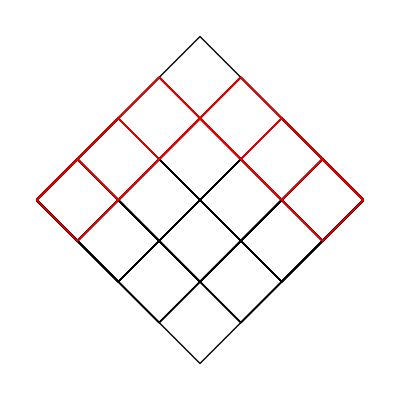

```mathematica
highlightBlock[4, 4, 2]
```

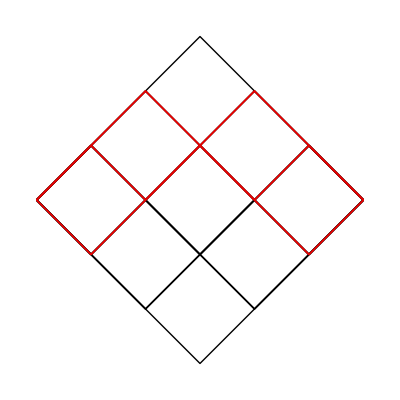

```mathematica
highlightBlock[3, 3, 1]
```

```mathematica
diagonalLatticePaths[n_]:=
Select[Accumulate/@Tuples[{1, -1}, n], #[[-1]]==0&]//Transpose[
{
ConstantArray[Range[0, n], Length@#],
Join[
ConstantArray[0, {Length@#, 1}],
#,
2
]
},
{3, 1, 2}
]&
```

```mathematica
highlightBlock[n_, split_, value_]:=
With[{paths=diagonalLatticePaths[2*n]},
Graphics[{
Line@paths,
{
Thick,
Hue[0, 1, .9],
Line@Pick[paths, paths[[;;, split+1, 2]], value]
}
}]
]
```

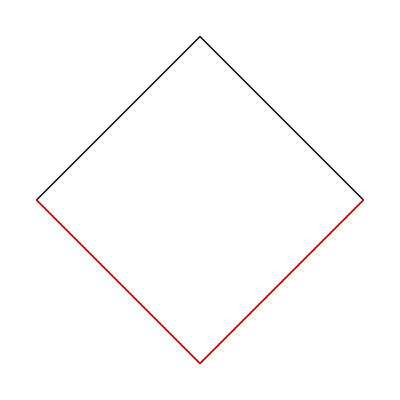

```mathematica
highlightBlock[1, 1, -1]
```

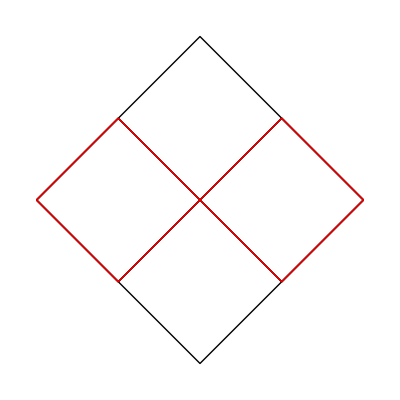

```mathematica
highlightBlock[2, 2, 0]
```

```mathematica
highlightBlock[3, 3, 1]
```

-Graphics-

```mathematica
ugh[3]
```

{{6,11,6,1},{9,27,27,9},{0,0,0,9},{0,2,-3,1}}

```mathematica
highlightBlock[5, 5, 3]
```

```mathematica
ugh[5]
```

{{120,274,225,85,15,1},{600,1700,1850,975,250,25},{225,825,1300,1100,500,100},{0,25,0,100,0,100},{0,50,-175,225,-125,25},{0,24,-50,35,-10,1}}

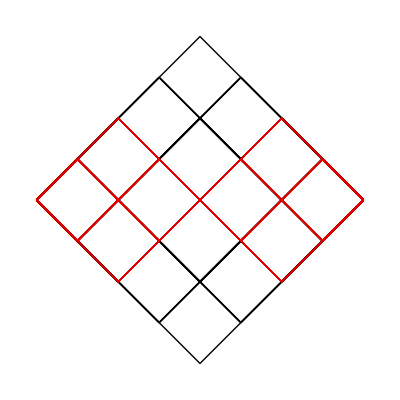

```mathematica
highlightBlock[4, 4, 0]
```

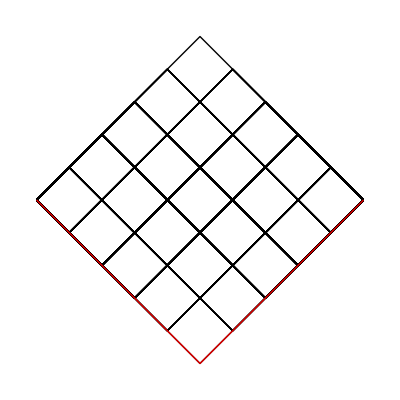

```mathematica
highlightBlock[5, 5, -5]
```

```mathematica
highlightBlock[10, 5, -5]
```

-Graphics-

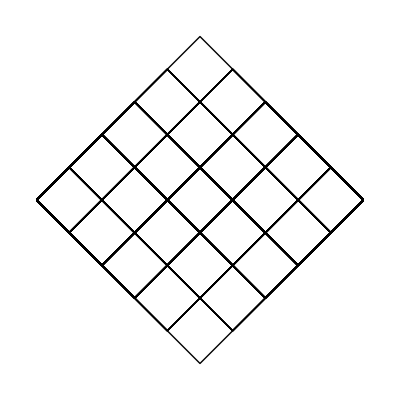

```mathematica
Line@diagonalLatticePaths[10]//Graphics
```

```mathematica
Clear[totalPolyCoeffs,totalLatticePoly, pathPartitionPoly] 
pathPartitionPoly[partition_, var_:n]:=Block[
{
pos=Reverse@Accumulate[Reverse[partition]],
which=Unitize[partition-1]
},
Times@@Sqrt[var+pos+which]
];
totalLatticePoly[ups_Integer,downs_Integer, var:Except[_Integer]:n]:=
Total@(pathPartitionPoly[#, var]&/@Permutations[Join[ConstantArray[1, ups], ConstantArray[-1, downs]]]);
totalLatticePoly[D_, var:Except[_Integer]:n]:=
Total@(pathPartitionPoly[#, var]&/@Permutations[Join[ConstantArray[1, D], ConstantArray[-1, D]]]);
totalPolyCoeffs[D_, var:Except[_Integer]:n, shift_Integer:0]:=
CoefficientList[totalLatticePoly[D, var+shift], var];
coeffProd[c1_, c2_]:=
ListConvolve[
c1,
c2, 
{1, -1}, 
0
]
```

```mathematica
reducedPolyGen[1]//FullSimplify
```

a+2 n

```mathematica
reducedRemainderPolyG[2, 0]//FullSimplify
```

1+2 n

```mathematica
reducedRemainderPolyG[6, 4]//FullSimplify
```

5+2 n

```mathematica
reducedRemainderPolyG[4, 2]//FullSimplify
```

3+2 n

```mathematica
latticePolyGP[10, 4]//Expand
```

-3150 √(1+n) √(2+n) √(3+n) √(4+n)-2760 n √(1+n) √(2+n) √(3+n) √(4+n)-900 n^2 √(1+n) √(2+n) √(3+n) √(4+n)-120 n^3 √(1+n) √(2+n) √(3+n) √(4+n)

```mathematica
latticePolyG[10, 4]//Expand
```

3150 √(1+n) √(2+n) √(3+n) √(4+n)+2760 n √(1+n) √(2+n) √(3+n) √(4+n)+900 n^2 √(1+n) √(2+n) √(3+n) √(4+n)+120 n^3 √(1+n) √(2+n) √(3+n) √(4+n)

```mathematica
Clear[latticePolyG, remainderPolyG, reducedRemainderPolyG, latticePolyGP]
latticePolyG[0, k_, var_Symbol:n, shift_:0]:=1;
latticePolyG[n_Integer?Positive, n_Integer, var_Symbol:n, shift_:0]:=
Product[Sqrt[var+shift+i], {i, 1, n}];
latticePolyG[n_Integer?Positive, m_Integer, var_Symbol:n, shift_:0]/;m==-n:=
Product[Sqrt[var+shift-i], {i, 0, n-1}];
latticePolyG[n_Integer?Positive, k_, var_Symbol:n, shift_:0]/;Mod[n, 2]==Mod[k, 2]:=
latticePolyG[n, k, var, shift]=Assuming[var>=0,
Expand[
Sqrt[var+shift+1]*latticePolyG[n-1, k-1, var, shift+1]+
Sqrt[var+shift]*latticePolyG[n-1, k+1, var, shift-1]
]
];
latticePolyGP[0, k_, var_Symbol:n, shift_:0]:=1 ;
latticePolyGP[n_Integer?Positive, n_Integer, var_Symbol:n, shift_:0]:=
(-1)^n Product[Sqrt[var+shift+i], {i, 1, n}];
latticePolyGP[n_Integer?Positive, m_Integer, var_Symbol:n, shift_:0]/;m==-n:=
Product[Sqrt[var+shift-i], {i, 0, n-1}];
latticePolyGP[n_Integer?Positive, k_, var_Symbol:n, shift_:0]/;Mod[n, 2]==Mod[k, 2]:=
latticePolyGP[n, k, var, shift]=Assuming[var>=0,
Expand[
-Sqrt[var+shift+1]*latticePolyGP[n-1, k-1, var, shift+1]+
Sqrt[var+shift]*latticePolyGP[n-1, k+1, var, shift-1]
]
];
remainderPolyG[n_, k_,var_Symbol:n, shift_:0]:=
Assuming[var>=0,
latticePolyG[n, k, shift]/
Product[Sqrt[var+shift+i], {i, 1, k}]//FullSimplify
];
reducedRemainderPolyG[n_, k_,var_Symbol:n, shift_:0]/;k>=0:=
2((n-k)/2)!*remainderPolyG[n, k, var, shift]/
Product[(n-i), {i, 0,(n-k)/2-1}]//FullSimplify
```

```mathematica
remainder2Poly[n_, prefactor:True|False:True]:=With[{k=n-1}, (k+2*n)*If[prefactor, n/2, 1]];
remainder4Poly[n_, prefactor:True|False:True]:=With[{k=n-3}, 
If[n>4,
remainder4Poly[n-1, False]+(1+n)(n-3+n),
((1+n)remainder2Poly[n-2]-n)
]*If[prefactor, (n(n-1)/4), 1]
];
remainder6Poly[n_, prefactor:True|False:True]:=With[{k=n-4}, 
remainder2Poly[n-4, False]*(k+remainder4Poly[n-2, False])*If[prefactor, (n(n-1)(n-2)/24), 1]
]
remainder2PolyExplicit[n_, prefactor:True|False:True]:=
(n-1+2*n)*If[prefactor, n/2, 1];
remainder4PolyExplicit[n_, prefactor:True|False:True]:=
((n-3+2n)(1+n)(n-2)/2-n)*If[prefactor, (n(n-1)/4), 1];
remainder6PolyExplicit[n_, prefactor:True|False:True]:=
(n-5+2n)((n-4)(1+(1+n)(n-5+2*n)/2)-n)*If[prefactor, (n(n-1)(n-2)/24), 1];
```

```mathematica
remPoly8Results=First/@{{3+2 n (1+n) (4+n (1+n))},{15+2 n (2+n) (7+n (2+n))},{45+2 n (3+n) (11+n (3+n))},{105+2 n (4+n) (16+n (4+n))},{210+2 n (5+n) (22+n (5+n))},{378+2 n (6+n) (29+n (6+n))},{630+2 n (7+n) (37+n (7+n))},{990+2 n (8+n) (46+n (8+n))},{1485+2 n (9+n) (56+n (9+n))},{2145+2 n (10+n) (67+n (10+n))},{3003+2 n (11+n) (79+n (11+n))}};
```

```mathematica
quickBlock[n_, k_]:=
With[{d=n, y=n-(n-k)/2, x=(n-k)/2},
Graphics[
{
Line@Join[
Table[{{i, 0},{i, d}}, {i, 0, d}],
Table[{{0, i},{d, i}}, {i, 0, d}]
],
{
Red,
Thick,
Line@Join[
Table[{{i, 0},{i,y}}, {i, 0, x}],
Table[{{0, i},{x, i}}, {i, 0, y}]
],
Line@Join[
Table[{{i, y},{i, d}}, {i, x, d}],
Table[{{x, i},{d, i}}, {i, y, d}]
]
}
}//Rotate[#, -π/4]&
]
]
```

```mathematica
Transpose@{
Table[remainder2Poly[n, False]//Expand, {n, 2, 6}],
Table[remainder4Poly[n, False]//Expand, {n, 4, 8}],
Table[remainder6Poly[n, False]//Expand, {n, 6, 10}],
Expand/@remPoly8Results[[;;5]]
}//Grid[#, Spacings->2]&
```

1+2 n | 1+2 n+2 n^2 | 3+8 n+6 n^2+4 n^3 | 3+8 n+10 n^2+4 n^3+2 n^4
2+2 n | 3+5 n+3 n^2 | 12+22 n+16 n^2+6 n^3 | 15+28 n+22 n^2+8 n^3+2 n^4
3+2 n | 6+9 n+4 n^2 | 30+47 n+30 n^2+8 n^3 | 45+66 n+40 n^2+12 n^3+2 n^4
4+2 n | 10+14 n+5 n^2 | 60+86 n+48 n^2+10 n^3 | 105+128 n+64 n^2+16 n^3+2 n^4
5+2 n | 15+20 n+6 n^2 | 105+142 n+70 n^2+12 n^3 | 210+220 n+94 n^2+20 n^3+2 n^4

```mathematica
105/3
```

35

```mathematica
210/3
```

70

```mathematica
Table[
24*2remainderPoly[n, n-8]/(n(n-1)(n-2)(n-3))//FullSimplify,
{n, 8, 18}
]//Column
```

```mathematica
remainder2Poly[2, False]*remainder4Poly[n, False]
```

```mathematica
remPoly8Results[[1]]-remainder6Poly[6, False]//Expand
```

4 n^2+2 n^4

```mathematica
remPoly8Results[[2]]-remainder6Poly[7, False]//FullSimplify
```

3+2 n (1+n) (3+n^2)

```mathematica
remPoly8Results[[3]]-remainder6Poly[8, False]//FullSimplify
```

15+n (19+2 n (5+n (2+n)))

```mathematica
remPoly8Results[[4]]-remainder6Poly[9, False]//FullSimplify
```

45+2 n (21+n (8+n (3+n)))

```mathematica
remPoly8Results[[5]]-remainder6Poly[10, False]//FullSimplify
```

105+2 n (39+n (12+n (4+n)))

```mathematica
remPoly8Results[[5]]-remainder6Poly[10, False]//FullSimplify
```

```mathematica
Table[remainder4Poly[n, False]//Expand, {n, 4, 8}]
```

{1+2 n+2 n^2,3+5 n+3 n^2,6+9 n+4 n^2,10+14 n+5 n^2,15+20 n+6 n^2}

```mathematica
Grid@
Table[
{remainder6Poly[n, False]//Expand, Append[quickBlock[n,n-6], ImageSize->250]},
{n, 6, 10}
]
```

3+8 n+6 n^2+4 n^3 | -Graphics-
12+22 n+16 n^2+6 n^3 | -Graphics-
30+47 n+30 n^2+8 n^3 | -Graphics-
60+86 n+48 n^2+10 n^3 | -Graphics-
105+142 n+70 n^2+12 n^3 | -Graphics-

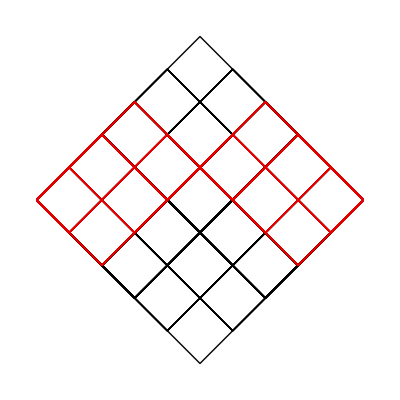

```mathematica
highlightBlock[5,5, 1]
```

```mathematica
remainder4Poly[6, False]//FullSimplify
```

6+n (9+4 n)

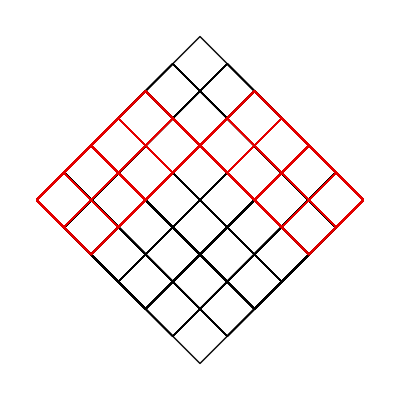

```mathematica
highlightBlock[6, 6, 2]
```

```mathematica
remainder6Poly[7, False]//FullSimplify
```

2 (1+n) (6+n (5+3 n))

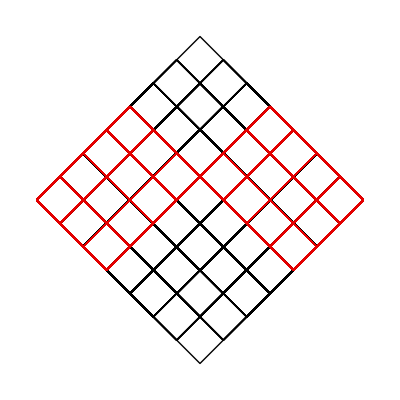

-Graphics-

```mathematica
highlightBlock[7, 7, 1]
```

```mathematica
remPoly8Results[[3]]//Expand
```

45+66 n+40 n^2+12 n^3+2 n^4

```mathematica
remPoly8Results[[4]]-remPoly8Results[[3]]//FullSimplify
```

```mathematica
remPoly8Results[[4]]-remPoly8Results[[3]]//FullSimplify
```

2 (2+n) (15+2 n (4+n))

```mathematica
remPoly8Results[[5]]-remPoly8Results[[4]]//FullSimplify
```

(5+2 n) (21+2 n (5+n))

```mathematica
{{3+2 n (1+n) (4+n(1+n))}, {15+2 n (2+n) (7+n (2+n))}, {45+2 n (3+n) (11+n (3+n))}, {105+2 n (4+n) (16+n (4+n))}, {210+2 n (5+n) (22+n (5+n))}, {378+2 n (6+n) (29+n (6+n))}, {630+2 n (7+n) (37+n (7+n))}, {990+2 n (8+n) (46+n (8+n))}, {1485+2 n (9+n) (56+n (9+n))}, {2145+2 n (10+n) (67+n (10+n))}, {3003+2 n (11+n) (79+n (11+n))}}
```

{{3+2 n (1+n) (4+n (1+n))},{15+2 n (2+n) (7+n (2+n))},{45+2 n (3+n) (11+n (3+n))},{105+2 n (4+n) (16+n (4+n))},{210+2 n (5+n) (22+n (5+n))},{378+2 n (6+n) (29+n (6+n))},{630+2 n (7+n) (37+n (7+n))},{990+2 n (8+n) (46+n (8+n))},{1485+2 n (9+n) (56+n (9+n))},{2145+2 n (10+n) (67+n (10+n))},{3003+2 n (11+n) (79+n (11+n))}}

```mathematica
s
```

3+2 n (1+n) (4+n(1+n))
15+2 n (2+n) (7+n (2+n))
45+2 n (3+n) (11+n (3+n))
105+2 n (4+n) (16+n (4+n))
210+2 n (5+n) (22+n (5+n))
378+2 n (6+n) (29+n (6+n))
630+2 n (7+n) (37+n (7+n))
990+2 n (8+n) (46+n (8+n))
1485+2 n (9+n) (56+n (9+n))
2145+2 n (10+n) (67+n (10+n))
3003+2 n (11+n) (79+n (11+n))

```mathematica
Table[
24*2remainderPoly[n, n-8]/(n(n-1)(n-2)(n-3))//FullSimplify,
{n, 8, 18}
]//Column
```

3+2 n (1+n) (4+n+n^2)
15+2 n (2+n) (7+n (2+n))
45+2 n (3+n) (11+n (3+n))
105+2 n (4+n) (16+n (4+n))
2 (7+n (5+n)) (15+n (5+n))
378+2 n (6+n) (29+n (6+n))
630+2 n (7+n) (37+n (7+n))
990+2 n (8+n) (46+n (8+n))
1485+2 n (9+n) (56+n (9+n))
2145+2 n (10+n) (67+n (10+n))
3003+2 n (11+n) (79+n (11+n))

```mathematica
Table[
48remainderPoly[n, n-8]/(n(n-1)(n-2)(n-3))//FullSimplify,
{n, 8, 18}
]//Column
```

3+2 n (1+n) (4+n+n^2)
15+2 n (2+n) (7+n (2+n))
45+2 n (3+n) (11+n (3+n))
105+2 n (4+n) (16+n (4+n))
210+2 n (5+n) (22+n (5+n))
378+2 n (6+n) (29+n (6+n))
630+2 n (7+n) (37+n (7+n))
990+2 n (8+n) (46+n (8+n))
1485+2 n (9+n) (56+n (9+n))
2145+2 n (10+n) (67+n (10+n))
3003+2 n (11+n) (79+n (11+n))

```mathematica
2 (7+n (5+n)) (15+n (5+n))//Expand
```

210+220 n+94 n^2+20 n^3+2 n^4

```mathematica
220 n+94 n^2+20 n^3+2 n^4//FullSimplify
```

2 n (5+n) (22+n (5+n))

```mathematica
Table[
remainderPoly[n, n-8]//FullSimplify,
{n, 19, 24}
]//Column
```

1938 (4095+2 n (12+n) (92+n (12+n)))
4845 (2730+n (13+n) (106+n (13+n)))
5985 (51+n (14+n)) (70+n (14+n))
7315 (4590+n (15+n) (137+n (15+n)))
8855 (5814+n (16+n) (154+n (16+n)))
5313 (14535+2 n (17+n) (172+n (17+n)))

```mathematica
Table[
n*(n-1)*(n-2)*(n-3)/24/2,
{n, 8, 24}
]//Column
```

35
63
105
165
495/2
715/2
1001/2
1365/2
910
1190
1530
1938
4845/2
5985/2
7315/2
8855/2
5313

```mathematica
s
```

5 (1+2 n)(3+2 n (1+n))
35 (1+n) (3+n (2+n))
28 (3+2 n) (5+n (3+n))
42 (2+n) (15+2 n (4+n))
30 (5+2 n) (21+2 n (5+n))
165 (3+n) (14+n (6+n))
110 (7+2 n) (18+n (7+n))
143 (4+n) (45+2 n (8+n))
91 (9+2 n) (55+2 n (9+n))
455 (5+n) (33+n (10+n))
280 (11+2 n) (39+n (11+n))
340 (6+n) (91+2 n (12+n))
204 (13+2 n) (105+2 n (13+n))

```mathematica
blockPolyCoeffs//Clear
blockPolyCoeffs[n_, k_, shift_Integer:0]/;Mod[k, 2]==Mod[n, 2]:=
Which[
k==n,
CoefficientList[Product[(n+shift+i), {i, 1, n}], n],
k==-n,
CoefficientList[Product[(n+shift-i), {i, 0, n-1}], n],
k==0,
coeffProd[totalPolyCoeffs[n/2, shift],totalPolyCoeffs[n/2, shift]],
k==n-2,
CoefficientList[
Product[(n+shift+i), {i, 1, n-2}]*
(Sum[n+shift+i, {i, 0, n-1}]^2),
n],
k==-(n-2),
CoefficientList[
Product[(n+shift-i), {i, 0, n-3}]*
(Sum[n+shift-i, {i, -1, n-2}]^2),
n],
k>0,
coeffProd[
CoefficientList[Product[(n+shift+i), {i, 1, k}], n],
coeffProd[#, #]
]&@
CoefficientList[
totalLatticePoly[(n+k)/2, (n-k)/2, n]/
Product[Sqrt[n+i], {i, 1, k}], 
n],
True,
Missing["NotImplemented"]
]
```

```mathematica
Solve[{a+b==n, a-b==k}, {a, b}]
```

{{a→(k+n)/2,b→1/2 (-k+n)}}

##### n+1/2 Expansions

```mathematica
CoefficientList[
reducedPolyGen[4]//CoefficientList[#, n]&,
a
]
```

{{0,-6,11,-6,1},{-96,104,-48,8},{176,-120,24},{-96,32},{16}}

```mathematica
CoefficientList[
reducedPolyGen[4]/.(n->m-1/2)//CoefficientList[#, m]&,
a
]
```

{{105,-92,41,-10,1},{-352,248,-72,8},{344,-168,24},{-128,32},{16}}

```mathematica
CoefficientList[
reducedPolyGen[3]/.(n->m+1/2)//CoefficientList[#, m]&,
a
]
```

{{3,-4,0,1},{-2,-6,6},{-12,12},{8}}

```mathematica
CoefficientList[
reducedPolyGenNeg[3]/.(n->m-3/2)//CoefficientList[#, m]&,
a
]
```

{{-3,4,0,-1},{-2,-6,6},{12,-12},{8}}

```mathematica
n12Expand[p_]:=p/.n->(m-(1/2))//Expand
```

```mathematica
CoefficientList[
reducedPolyGen[1]*reducedPolyGenNeg[1]//n12Expand//CoefficientList[#, m]&//FullSimplify,
a
]
```

{{-1,2,-1},{},{4}}

```mathematica
With[
{a1=4, b1=2},
(reducedPolyGen[b1]/.a->a1)*
(reducedPolyGenNeg[b1]/.{n->n+(a1-b1), a->a1})
]//n12Expand//CoefficientList[#, m]&
```

{49,112,120,64,16}

```mathematica
With[
{a1=4, b1=2},
(reducedPolyGen[b1]/.a->a1)^2
]//n12Expand//CoefficientList[#, m]&
```

{49,112,120,64,16}

```mathematica
With[
{a1=4, b1=2},
(reducedPolyGen[b1]/.a->a1)*
(reducedPolyGen[b1]/.{n->n+(a1-b1), a->a1})
]//CoefficientList[#, n]&
```

```mathematica
With[
{a1=4, b1=2},
(reducedPolyGen[b1]/.a->a1)*
(reducedPolyGen[b1]/.{ a->a1})
]//n12Expand//CoefficientList[#, m]&
```

{49,112,120,64,16}

```mathematica
reducedPolyGenNeg[5]/.{n->n+(a-5)}//FullSimplify
```

(-4+a+2 n) ((-3+a) (-2+a) (-1+a) a+8 (-4+a) (6+(-3+a) a) n+8 (38+a (-19+3 a)) n^2+32 (-4+a) n^3+16 n^4)

```mathematica
reducedPolyGen[5]
```

(-4+a+2 n) ((-3+a) (-2+a) (-1+a) a+8 (-4+a) (6+(-3+a) a) n+8 (38+a (-19+3 a)) n^2+32 (-4+a) n^3+16 n^4)

```mathematica
With[
{a1=4, b1=2},
(reducedPolyGen[b1]/.a->a1)*
(reducedPolyGenNeg[b1]/.{ a->a1})
]//n12Expand//CoefficientList[#, m]&
```

{49,0,-8,0,16}

```mathematica
Solve[c==(a-b+1)/2, a]
```

{{a→-1+2 c+b}}

```mathematica
Solve[c==(a+1)/2, a]
```

{{a→-1+2 c}}

```mathematica
With[{b=6},
(FullSimplify[reducedPolyGen[b]]/.{n->(m-(a-b+1)/2)})/.{
a->(c)
}//Expand//CoefficientList[#, m]&//CoefficientList[#, c]&//Column
]
```

{-225,345,-135,15}
{}
{1036,-960,180}
{}
{-560,240}
{}
{64}

```mathematica
With[{b=6},
(FullSimplify[reducedPolyGen[b]]/.{n->(m-(a-b+1)/2)})/.{
a->-1+2 c+b
}//Expand//CoefficientList[#, m]&//CoefficientList[#, c]&//Column
]
```

{0,240,360,120}
{}
{736,1680,720}
{}
{640,480}
{}
{64}

```mathematica
Table[
(
reducedPolyGen[b]/.{n->n+2, a->2}
)/.{
n->(m-(2+(2-b+1 )/2))
}//Expand//CoefficientList[#, m]&,
{b, 10}
]
```

{{0,2},{1,0,4},{0,4,0,8},{-3,0,8,0,16},{0,-32,0,0,0,32},{45,0,-164,0,-80,0,64},{0,768,0,-448,0,-448,0,128},{-1575,0,6352,0,224,0,-1792,0,256},{0,-36864,0,31744,0,10752,0,-6144,0,512},{99225,0,-420876,0,77600,0,77952,0,-19200,0,1024}}

```mathematica
(reducedPolyGen[3]/.{a->4})/.{
n->(m-(1+4-3)/2)
}//CoefficientList[#, m]&
```

{0,16,0,8}

```mathematica
(reducedPolyGen[3]/.{a->4})*(reducedPolyGen[2]/.{a->4})//CoefficientList[#, n]&
```

{288,768,864,544,192,32}

```mathematica
Product[n+i, i]
```

```mathematica
(
(
(reducedPolyGen[3]/.{a->4})*
(reducedPolyGen[2]/.{a->4})
)//CoefficientList[#, n]&
)/.{
n->(m-(1+8-5)/2)
}
```

{288,768,864,544,192,32}

```mathematica
(
(
(reducedPolyGen[3]/.{a->4})*
(reducedPolyGen[2]/.{a->4})
)//CoefficientList[#, n]&
)/.{
n->(m-(1+8-5)/2)
}
```

```mathematica
laa
```

```mathematica
((reducedPolyGen[3]/.{a->4})/.{
n->(m-(1+4-3)/2)
})^2//CoefficientList[#, m]&
```

{0,0,256,0,256,0,64}

```mathematica
(
reducedPolyGen[3]/.{a->4}
)*(
reducedPolyGen[2]/.{a->2}
)*(
reducedPolyGen[2]/.{a->4}
)/.{
n->(m-(1+3)/2)
}//FullSimplify//CoefficientList[#, m]&
```

{-960,3712,-6976,8128,-6144,3008,-896,128}

```mathematica
(
reducedPolyGen[7]/.{n->n, a->10}
)/.{
n->(m-(3+1)/2)
}//FullSimplify//CoefficientList[#, m]&
```

{0,55872,0,39872,0,4928,0,128}

```mathematica
fallingFac[]
```

```mathematica
Table[
(FullSimplify[reducedPolyGen[b]]/.{n->(m-(a-b+1)/2)})/.{
a->-1+2 c+b
}//Expand//CoefficientList[#, m]&//Map[fallingFac[#, c]&]//MapIndexed[
#/2^(#2[[1]]-1)&
],
{b, 7}
]//Column[#, Alignment->Right]&
```

{{},{1}}
{{0,2},{},{1}}
{{},{2,6},{},{1}}
{{0,24,12},{},{8,12},{},{1}}
{{},{24,160,60},{},{20,20},{},{1}}
{{0,720,720,120},{},{184,600,180},{},{40,30},{},{1}}
{{},{720,7728,5880,840},{},{784,1680,420},{},{70,42},{},{1}}

```mathematica
FactorInteger[420]
```

{{2,2},{3,1},{5,1},{7,1}}

```mathematica
FactorInteger[180]
```

{{2,2},{3,2},{5,1}}

```mathematica
{240 c+360 c^2+120 c^3,0,736+1680 c+720 c^2,0,640+480 c,0,64}//Map[fallingFac[#, c]&]//MapIndexed[
#/2^(#2[[1]]-1)&
]
```

{{0,720,720,120},{},{184,600,180},{},{40,30},{},{1}}

```mathematica
With[{b=6},
(FullSimplify[reducedPolyGen[b]]/.{n->(m-(a-b+1)/2)})/.{
a->-1+2 c+b
}//Expand//CoefficientList[#, m]&//CoefficientList[#, c]&//Column
]
```

```mathematica
With[{b=6},
(polyGen[b]/.{n->(m-(a-b+1)/2)})/.{
a->(c)
}//Expand//CoefficientList[#, m]&//CoefficientList[#, c]&//Column
]
```

{-225/64,-825/256,811/256,11171/3072,119/256,-427/1024,-31/256,3/1024,1/256,1/3072}
{}
{259/16,7891/320,3707/1440,-2667/256,-11599/2304,-581/1920,1547/5760,47/768,1/256}
{}
{-35/4,-283/16,-1519/144,-91/192,245/144,21/32,7/72,1/192}
{}
{1,49/20,203/90,49/48,35/144,7/240,1/720}

### Products

We will have things like

```mathematica
permutationOperatorPathDiagram[{4, 3}, {2, 2}, {4, 2}]
```

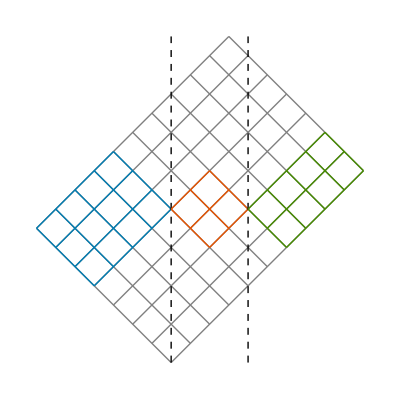

```mathematica
s
```

and we want to write out the left-to-right polynomial in reverse order as (I think)

K_2^4(n+1)K_2^2(n+1)K_3^4(n)

#### Examples

Sample extra poly contrib.

S_2^0(n)S_2^1(n-2)S_0^5(n-3)S_0^4(n+2)/S_4^10(n) = √((∏_(j=0)^1 (n-j))(∏_(j=0)^0 (n-2-j))(∏_(j=1)^5 (n-3+j))(∏_(j=1)^4 (n+2+j))/(∏_(j=1)^6 (n+j)))
= √((∏_(j=0)^1 (n-j))(∏_(j=2)^2 (n-j))(∏_(j=-2)^2 (n+j))(∏_(j=3)^6 (n+j))/(∏_(j=1)^6 (n+j)))
= √((∏_(j=0)^2 (n-j))(∏_(j=0)^2 (n-j))(∏_(j=1)^2 (n+j))(∏_(j=3)^6 (n+j))/(∏_(j=1)^6 (n+j)))
= √((∏_(j=0)^2 (n-j))(∏_(j=0)^2 (n-j)))
= ∏_(j=0)^2 (n-j)
⇒ S_2^0(n)S_2^1(n-2)S_0^5(n-3)S_0^4(n+2) = S_2^0(n)S_1^0(n-2)S_3^0(n)S_0^2(n)S_0^4(n+2)
= S_3^0(n)S_3^0(n)S_0^6(n)
= (S_3^0(n))^2 S_4^10(n)

So in general we have some nice sqrt props

S_b^a(n) = S_(b-a)^0(n)
S_b^0(n)S_c^0(n-b) = S_(b+c)^0(n)
S_0^a(n-c) = S_c^0(n) S_0^(a-c)(n)
S_b^0(n+c) = S_0^c(n) S_(b-c)^0(n)

and now if we have a string of N operators that generate lead to a change in quanta by k we have

K_b_1^a_1(n)K_b_2^a_2(n+(a_1-b_2))...K_b_N^a_N(n+k-(a_N-b_N)) = P_(b_1 b_2...)^(a_1 a_2...)(n) S_b_1^a_1(n)S_b_2^a_2(n+(a_1-b_2))...S_b_N^a_N(n+k-(a_N-b_N))

and so we want determine what the extra polynomial contribution is (since we note we’ll always divide out by S_(sum(b))^(sum(a)))

To get at we’ll first put the terms in a canonical form as

T_b_i^a_i = S_(min(b_i-a_i,0))^(max(a_i-b_i,0))

and then we’ll split up the crossing terms (where the change in quanta is greater than the shift and opposite in sign) into their two pure ascending and pure descending parts like

T_b_i^a_i(n+k_i) = Piecewise[{{S_(b_i-a_i-k_i)^0(n)S_0^k_i(n), k_i>0}, {S_0^(a_i-b_i-k_i)(n)S_k_i^0(n), k_i<0}}]

then we can split this up into pure raising terms and pure lowering terms

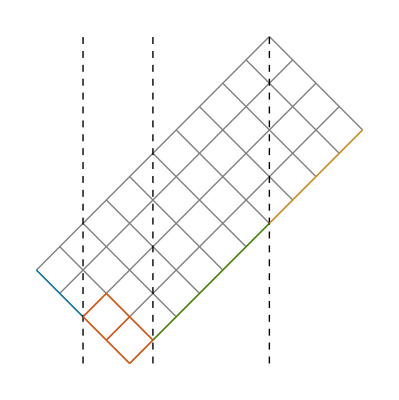
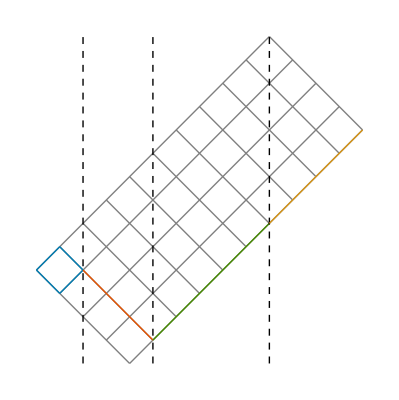
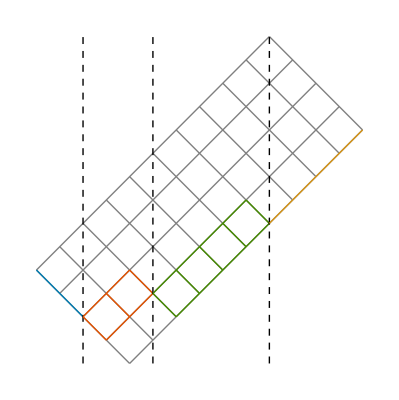
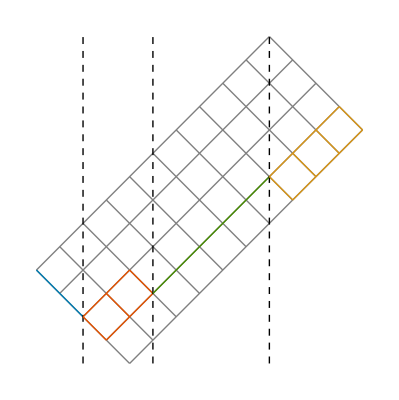
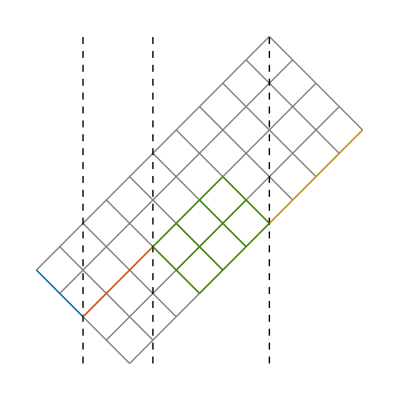
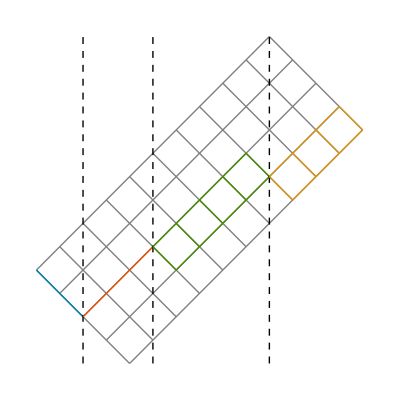
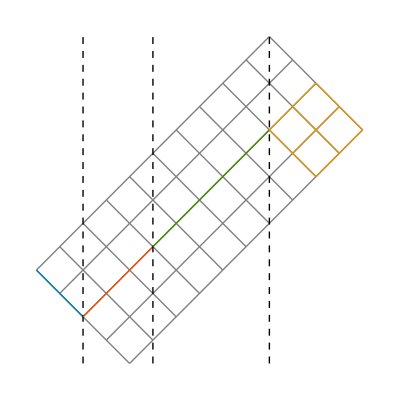
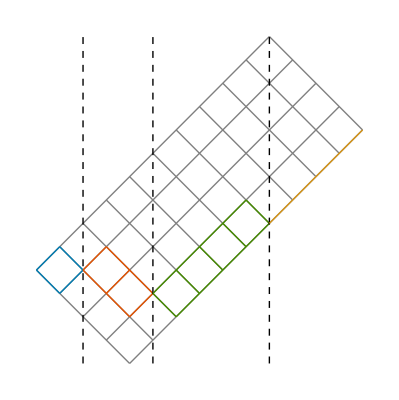
(-2+n) (-1+n) n | -Graphics--Graphics-
(-1+n) n | -Graphics--Graphics--Graphics--Graphics--Graphics-
n | -Graphics--Graphics-
1 | -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
3+n | -Graphics--Graphics-
(7+n) (8+n) | -Graphics--Graphics--Graphics-
n (1+n) (2+n) | -Graphics--Graphics-
2+n | -Graphics--Graphics--Graphics-
(3+n) (4+n) (5+n) | -Graphics-
5+n | -Graphics-
(7+n) (8+n) (9+n) (10+n) | -Graphics-

#### Intuitive Understanding of S-products

We really just need to modify our sequence

S_b_1^a_1(n)S_b_2^a_2(n+(a_1-b_2))...S_b_N^a_N(n+k-(a_N-b_N))

to split it up each time the direction turns as every change from going down to going up will contribute a product of terms like (n+k_M) and vice versa

We should also note that if we are coupling n to n+k, we can decompose the total S product into a form like (assuming k>0)

S_0^k(n)∏_(i,p) (n+i)^p

for some sequence of i and p

If we were to add up all of the possible paths, the (n+i)^p terms would revert to the basic K-function form but

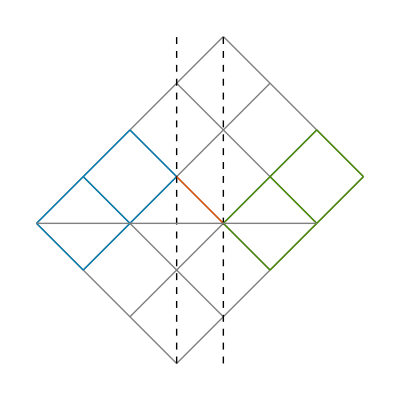

```mathematica
permutationOperatorPathDiagram[{2, 1}, {0, 1}, {2, 1}]
```

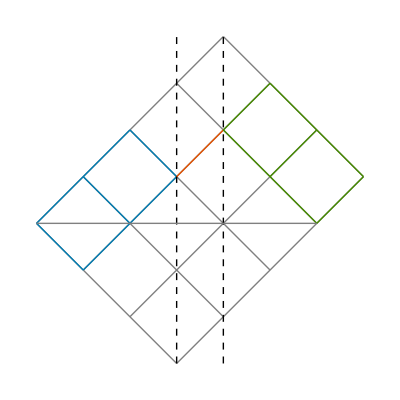

```mathematica
permutationOperatorPathDiagram[{2, 1}, {1, 0}, {1, 2}]
```

#### Recursive Construction of K-product

When constructing the set of terms like

K_b_1^a_1(n)K_b_2^a_2(n+(a_1-b_2))...K_b_N^a_N(n+k-(a_N-b_N)) = P_(b_1 b_2...)^(a_1 a_2...)(n) S_b_1^a_1(n)S_b_2^a_2(n+(a_1-b_2))...S_b_N^a_N(n+k-(a_N-b_N))

it ends up being fastest to do this recursively, where we’ll build off of our processes for building the possible paths

In that process, we built up the possible K products one by one, adding on newer terms at the end, subject to the constraint that we will eventually end up at the appropriate change in quanta, as so with N terms that change quanta by k, we have

S_b_1^a_1(n)S_b_2^a_2(n+(a_1-b_2))...S_b_N^a_N(n+k-(a_N-b_N)) = R_(b_1 b_2...)^(a_1 a_2...)(n)S_0^k(n)

where this remainder term looks like

R_(b_1 b_2...)^(a_1 a_2...)(n)=∏_(i=-(b_T-1))^a_T (n+i)^p_i

where p_i is a sequence of powers determined by the turns in the sequence of raising and lowering operations

This means to add on another term, we check where we currently are (i.e. k) and then if we are heading towards zero we add on as many terms as steps we have taken, in practice, this means

R_(b_1 b_2...)^(a_1 a_2...)(n)S_(b_(N+1))^(a_(N+1))(n+k) = R_(b_1 b_2...)^(a_1 a_2...)(n)Piecewise[{{1, sign(k) = sign(a_(N+1)-b_(N+1))}, {(S_(b_(N+1))^(a_(N+1))(n+k))^2, else}}]

then we can note that if a_(N+1) > b_(N+1)

(S_(b_(N+1))^(a_(N+1))(n+k))^2 = (n+k)^[k_(N+1)]
= (n + k + k_(N+1))_[k_(N+1)]
= ∑_(j=0)^(k_(N+1)) (k_(N+1)
j)(k + k_(N+1))_[k_(N+1)- j](n)_[j]

and so we can take quick convolutions using FFTs in the basis of ... ah shit no... products of basis functions don’t work that nicely... probably still best to expand everything as

(S_(b_(N+1))^(a_(N+1))(n+k))^2 = (n+k)^[k_(N+1)]
= ∑_(j=0)^(k_(N+1)) (-1)^j S_1(k_(N+1), j) (n+k)^j
= ∑_(j=0)^(k_(N+1)) ∑_(l=0)^j (j
l)(k^(j-l)(-1))^j S_1(k_(N+1), j) n^l
= ∑_(l=0)^(k_(N+1)) (∑_(j=l)^(k_(N+1)) (j
l)(k^(j-l)(-1))^j S_1(k_(N+1), j))n^l

##### Falling / Rising Poly Examples

```mathematica
With[{k=2, a=3, b=1},
Pochhammer[n+k, a-b]
]//Expand
```

6+5 n+n^2

```mathematica
With[{k=2, d=3-1},
Sum[(-1)^j*StirlingS1[d, j]*(n+k)^j, {j, 0, d}]
]//Expand
```

6+5 n+n^2

```mathematica
With[{k=2, d=3-1},
Sum[
Sum[(-1)^l*StirlingS1[d, l]*Binomial[l, j]*k^(l-j), {l, j, d}]*n^j, 
{j, 0, d}
]
]//Expand
```

6+5 n+n^2

```mathematica
With[{k=1, b=6, a=1},
FactorialPower[n+k, b-a]
]//FunctionExpand//Expand
```

-6 n+5 n^2+5 n^3-5 n^4+n^5

```mathematica
With[{k=1, d=6-1},
Sum[
Sum[StirlingS1[d, l]*Binomial[l, j]*k^(l-j), {l, j, d}]*n^j, 
{j, 0, d}
]
]//Expand
```

-6 n+5 n^2+5 n^3-5 n^4+n^5

##### Exploration

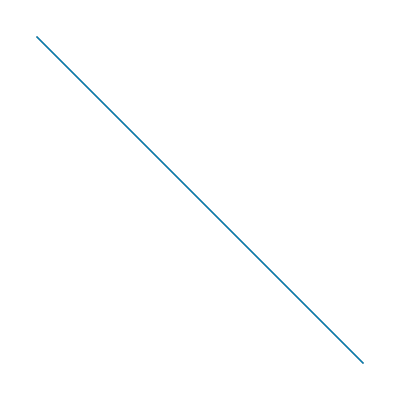
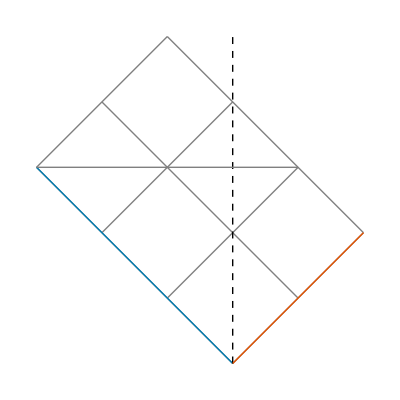
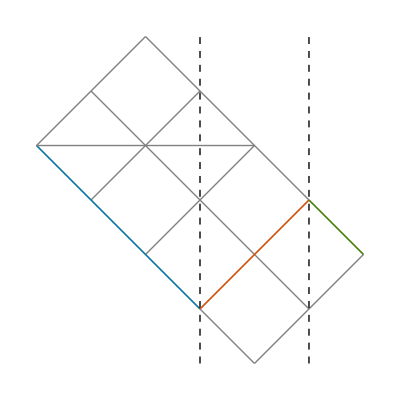
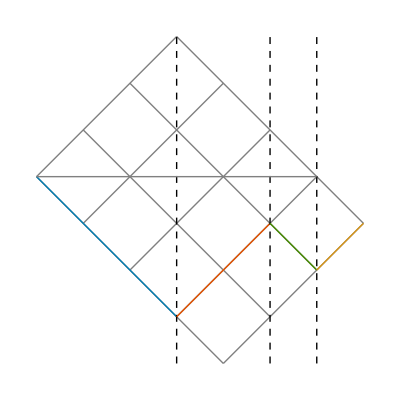
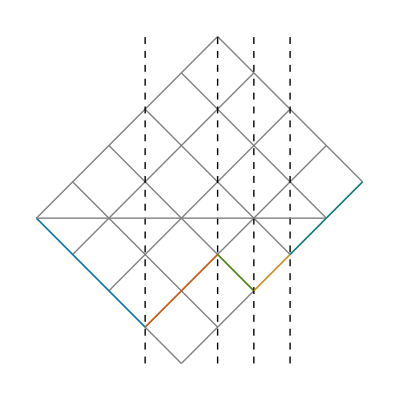
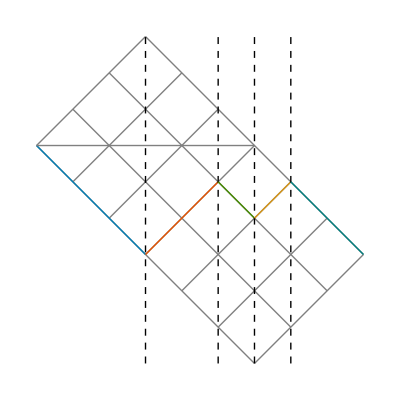
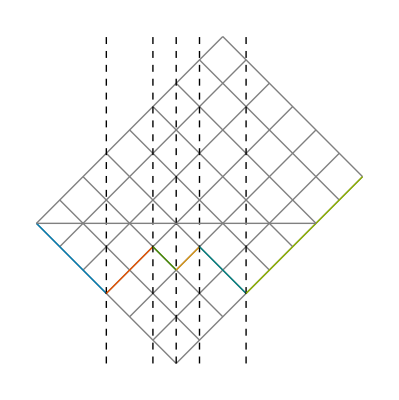
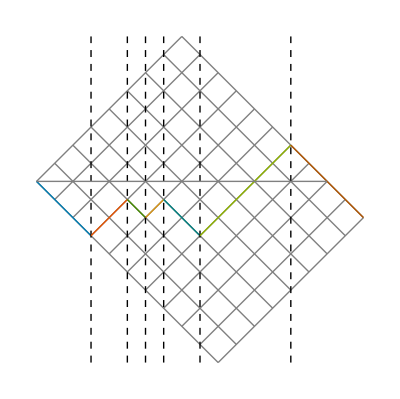
1 | -Graphics-
n_-2 n_-1 | -Graphics-
n_-2 n_-1 | -Graphics-
n_-2 n_-1^2 | -Graphics-
n_-2 n_-1^2 n_0 | -Graphics-
n_-2 n_-1^2 | -Graphics-
n_-2^2 n_-1^3 n_0 | -Graphics-
n_-2^2 n_-1^3 n_0 n_1 n_2 | -Graphics-

```mathematica
Transpose@{
getPathPolyRemainder@@@#/.Thread[
Thread[n+Range[-10, 10]]->Thread[Subscript[n, Range[-10, 10]]]
],
permutationOperatorPathDiagram@@@#
}&@{
{{0,3}},
{{0,3},{2, 0}},
{{0,3},{2, 0},{0, 1}},
{{0,3},{2, 0},{0, 1},{1, 0}},
{{0,3},{2, 0},{0, 1},{1, 0}, {2, 0}},
{{0,3},{2, 0},{0, 1},{1, 0}, {0, 2}},
{{0,3},{2, 0},{0, 1},{1, 0}, {0, 2}, {5, 0}},
{{0,3},{2, 0},{0, 1},{1, 0}, {0, 2}, {5, 0}, {0, 4}}
}//Grid
```

```mathematica
permutationOperatorPathDiagram@@@{
{{0,3}},
{{0,3},{2, 0}},
{{0,3},{2, 0},{0, 1}},
{{0,3},{2, 0},{0, 1},{1, 0}},
{{0,3},{2, 0},{0, 1},{1, 0}, {0, 2}},
{{0,3},{2, 0},{0, 1},{1, 0}, {0, 2}, {5, 0}},
{{0,3},{2, 0},{0, 1},{1, 0}, {0, 2}, {5, 0}, {0, 4}}
}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

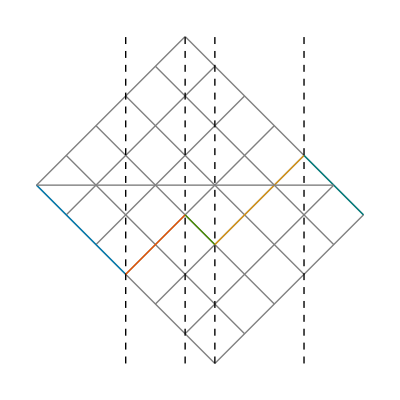
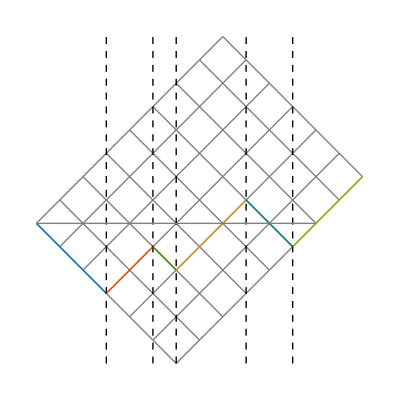
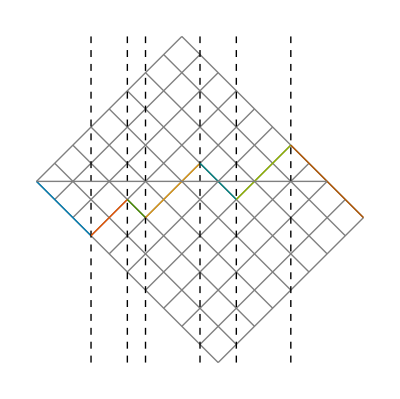
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
permutationOperatorPathDiagram@@@{
{{0,3}},
{{0,3},{2, 0}},
{{0,3},{2, 0},{0, 1}},
{{0,3},{2, 0},{0, 1},{1, 0}},
{{0,3},{2, 0},{0, 1},{3, 0}, {0, 2}},
{{0,3},{2, 0},{0, 1},{3, 0}, {0, 2}, {3, 0}},
{{0,3},{2, 0},{0, 1},{3, 0}, {0, 2}, {3, 0}, {0, 4}}
}
```

```mathematica
getPathPolyRemainder@@@{
{{0,3}},
{{0,3},{2, 0}},
{{0,3},{2, 0},{0, 1}},
{{0,3},{2, 0},{0, 1},{1, 0}},
{{0,3},{2, 0},{0, 1},{3, 0}, {0, 2}},
{{0,3},{2, 0},{0, 1},{3, 0}, {0, 2}, {3, 0}},
{{0,3},{2, 0},{0, 1},{3, 0}, {0, 2}, {3, 0}, {0, 4}}
}/.n->m+7/4//FullSimplify//ReplaceAll[m->m-7/4]//Column
```

1
(-2+m) (-1+m)
(-2+m) (-1+m)
(-2+m) (-1+m)^2
(-2+m) (-1+m)^2 m (1+m)
(-2+m) (-1+m)^2 m^2 (1+m)
m^2 (-4+m^2) (-1+m^2)^2

```mathematica
cps=enumeratePossibleChangePaths[{2, 3, 5, 4}, 6];
```

```mathematica
getPathPolyRemainder@@cps[[1]]
```

(-2+n) (-1+n) n

```mathematica
getPathPolyRemainder@@cps[[1, ;;2]]
```

1

```mathematica
cps[[1]]
```

{{0,2},{1,2},{5,0},{4,0}}

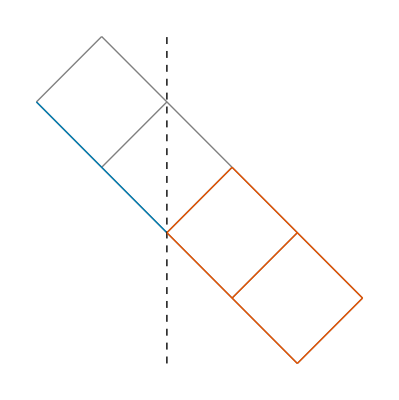
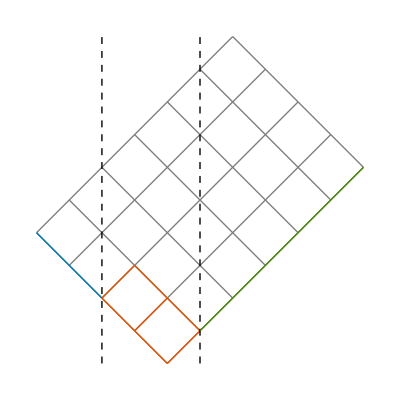
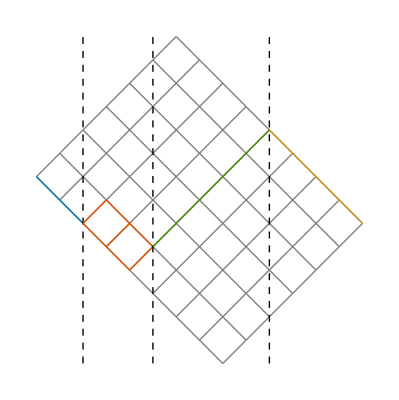

```mathematica
permutationOperatorPathDiagram@@@{
{{0,2},{1,2}},
{{0,2},{1,2}, {5, 0}},
{{0,2},{1,2}, {5, 0}, {0, 4}}
}
```

```mathematica
getPathPolyRemainder@@@{
{{0,2},{1,2}},
{{0,2},{1,2}, {5, 0}},
{{0,2},{1,2}, {5, 0}, {0, 4}}
}/.n->m+2//FullSimplify
```

{1,m (1+m) (2+m),m (1+m) (2+m) (3+m) (4+m)}

```mathematica
permutationOperatorPathDiagram@@@
enumeratePossibleChangePaths[{2, 3, 5, 4}, 6]
```

```mathematica
getPathPolyRemainder@@@enumeratePossibleChangePaths[{2, 3, 5, 4, 8}, 6]//FullSimplify//Column
```

```mathematica
(
getPathPolyRemainder@@@Permutations[{
{{0,3}, {3, 0}},  {{0,3}, {3, 0}}, {{0, 1}, {1, 0}}
}]
)/.n->m+2//FullSimplify//Column
```

```mathematica
(getPathPolyRemainder@@@{
{{0,2},{1,2}},
{{0,2},{1,2}, {7, 0}},
{{0,2},{1,2}, {5, 0}, {0, 1}},
{{0,2},{1,2}, {5, 0}, {0, 2}},
{{0,2},{1,2}, {5, 0}, {0, 3}},
{{0,2},{1,2}, {5, 0}, {0, 3}, {3, 0}},
{{0,2},{1,2}, {6, 0}, {0, 4}}
})/.n->m+2//FullSimplify//Column
```

1
m (1+m) (2+m)
m (1+m) (2+m) (4+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m)^2 (3+m) (4+m)
m (1+m) (2+m) (3+m) (4+m) (5+m)

```mathematica
(getPathPolyRemainder@@@{
{{0,2},{1,2}, {1,2}},
{{0,2},{1,2}, {1,2}, {7, 0}},
{{0,2},{1,2}, {1,2}, {5, 0}, {0, 1}},
{{0,2},{1,2}, {1,2}, {5, 0}, {0, 2}},
{{0,2},{1,2}, {1,2}, {5, 0}, {0, 3}},
{{0,2},{1,2}, {1,2}, {5, 0}, {0, 3}, {3, 0}},
{{0,2},{1,2}, {1,2}, {6, 0}, {0, 4}}
})/.n->m+3//FullSimplify//Column
```

1
m (1+m) (2+m) (3+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m)^2 (3+m)^2 (4+m)
m (1+m) (2+m) (3+m) (4+m) (5+m)

1
m (1+m) (2+m) (3+m)
m (1+m) (2+m) (3+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m)^2 (3+m)^2 (4+m)
m (1+m) (2+m) (3+m) (4+m) (5+m)

1
(-1+m) m (1+m) (2+m)
m (1+m) (2+m)
m (1+m) (2+m) (4+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m) (3+m) (4+m)
m (1+m) (2+m)^2 (3+m) (4+m)
m (1+m) (2+m) (3+m) (4+m) (5+m)

```mathematica
enumeratePossibleZeroPaths
```

```mathematica
(getPathPolyRemainder@@@{
{{0,2},{1,2}},
{{0,2},{1,2}, {1, 2}, {7, 0}},
{{0,2},{1,2}, {7, 0}},
{{0,2},{1,2}, {5, 0}, {0, 1}},
{{0,2},{1,2}, {5, 0}, {0, 2}},
{{0,2},{1,2}, {5, 0}, {0, 3}},
{{0,2},{1,2}, {5, 0}, {0, 3}, {3, 0}},
{{0,2},{1,2}, {6, 0}, {0, 4}}
})/.n->m+2//FullSimplify//Column
```

#### Experiments

##### Base Lattice Poly

```mathematica
latticePolyG[6, 2, n]*latticePolyG[4, 0, n]*latticePolyG[7, 1]//FullSimplify
```

1575 (1+n)^2 √(2+n) (1+2 n (1+n)) (3+n (2+n)) (3+n (3+n))

```mathematica
latticePolyG[17, 3, n]//FullSimplify
```

9724 √(1+n) (2+n)^(3/2) √(3+n) (4725+n (4+n) (1335+n (4+n) (101+2 n (4+n))))

```mathematica
(
latticePolyG[6, 2, n, 1]
*latticePolyG[4, 0, n, 1]
*latticePolyG[7, 1]/Product[√(i+n), {i, 1, 3}]
)//FullSimplify
```

1575 (1+n) (3+n (2+n)) (5+2 n (3+n)) (7+n (5+n))

```mathematica
(
latticePolyG[6, 2, n, 1]
*latticePolyG[4, 0, n, 1]
*latticePolyG[7, 1]/Product[√(i+n), {i, 1, 3}]
)//FullSimplify
```

1575 (1+n) (3+n (2+n)) (5+2 n (3+n)) (7+n (5+n))

```mathematica
(polySqrtGen[4, 2]/.n->n+1)*(polySqrtGen[2, 2]/.n->n+1)*polySqrtGen[4, 3]/Product[√(i+n), {i, 1, 3}]//FullSimplify
```

1575 (1+n) (3+n (2+n)) (5+2 n (3+n)) (7+n (5+n))

```mathematica
polyGen[6, 3]/.{
n->(m-(1+3)/2)
}//Expand
```

294 m+84 m^3

##### Diagrams

```mathematica
Clear[permutationPathDiagram, permutationDiagramLines]
permutationDiagramLines[a_, b_, Optional[{ox_, oy_},{0, 0}]]:=
With[{x=ox, y=oy-b},
Line[
Join[
Table[{{i, y},{i, b+y}}, {i, x, a+x}],
Table[{{x, i},{a+x, i}}, {i, y, b+y}]
].RotationMatrix[-π/4]
]
];
permutationPathDiagram[a_, b_, Optional[{x_, y_},{0, 0}]]:=
Graphics[permutationDiagramLines[a, b, {x, y}]];
permutationMatchDiagram[{a_, b_}, {sa_, sb_}]:=
Graphics[{
permutationDiagramLines[a, b, {0, 0}],
{
Thick,
Red,
permutationDiagramLines[sa, sb, {0, 0}]
},
{
Thick,
Blue,
permutationDiagramLines[a-sa, b-sb, {sa, -sb}]
},
{
Dashed,
Line[{{sa+sb, 1-a}, {sa+sb, a}}1/(√2)]
}
}]
permutationOperatorPathDiagram[steps:{_, _}..]:=
Block[{total=Total[{steps}], new, cur={0, 0}, idx=0,colors=ColorData[68]},
Graphics[
{
{
Gray,
permutationDiagramLines[total[[1]], total[[2]], cur]
},
Table[
cur+=s;
idx+=1;
{
{
Thick,
colors[idx],
permutationDiagramLines[s[[1]], s[[2]], {cur[[1]]-s[[1]], -(cur[[2]]-s[[2]])}]
},
If[cur!=total,
{
Dashed,
Line[{{Total[cur], (total[[1]]-total[[2]])-total[[1]]}, {Total[cur], total[[1]]}}1/(√2)]
},
Nothing
]
},
{s, {steps}}
],
{
Thin,
Gray,
Line[{{0, 0}, {Min[cur], Min[cur]}}.RotationMatrix[π/4]]
}
}
]
]
```

##### Enumeration

```mathematica
enumeratePossibleZeroPaths[s1_, s2_, s3_]:=
Table[
(* calculate how many raising/lowering ops we need to do to get to zero *)
If[-s3<=(s1-2i+s2-2j)≤s3,
{
{1/2 (s3-(s1-2i+s2-2j)), 1/2(s3+(s1-2i+s2-2j))},
{s2-j, j},
{s1-i, i}
},
Nothing
],
{j, 0, s2},
{i, 0, s1}
]//Catenate
enumeratePossibleZeroDiagrams[s1_, s2_, s3_]:=
enumeratePossibleZeroPaths[s1, s2, s3]//Map[Apply[permutationOperatorPathDiagram]]//Partition[#, UpTo[5]]&//Grid
getPossibleZeroContrib[{{a3_, b3_}, {a2_, b2_}, {a1_, b1_}}]:=
(polySqrtGen[a3, b3]/.n->n+(a1+a2)-(b1+b2))*
(polySqrtGen[a2, b2]/.n->n+(a1-b1))*
polySqrtGen[a1, b1]
```

```mathematica
Clear[enumeratePossibleChangePaths, getPathContrib];
enumeratePossibleChangePaths[
{steps_Integer},
target_
]:=
If[Mod[steps, 2]==Mod[Abs[target], 2],
{(target+steps)/2, (target-steps)/2},
{}
];
enumeratePossibleChangePaths[
{s1_Integer, s2_Integer},
k_
]:=
If[Mod[s1+s2, 2]==Mod[Abs[k], 2],
Table[
{{a1, s1-a1}, {1/2(k+s1+s2)-a1, 1/2(s2-(k+s1))+a1}},
{a1, Max@{0, 1/2 (k+s1-s2)}, Min@{s1, 1/2 (k+s1+s2)}}
],
{}
];
enumeratePossibleChangePaths[
{s1_, steps__},
k_
]:=
If[Mod[s1+Total[{steps}], 2]==Mod[Abs@k, 2],
Catenate@
Table[
If[Abs[k-(2a1-s1)]≤Total[{steps}],
Prepend[{a1, s1-a1}]/@
enumeratePossibleChangePaths[
{steps},
k-(2a1-s1)
],
{}
],
{a1, 0,s1}
],
{}
];
naivePaths[steps:{__Integer}, target_]:=
With[{
bases=Table[Table[{s-b, b}, {b, 0, s}], {s, steps}]
},
Length[Tuples[bases]]
(*Select[Tuples[bases], Total[#[[;;, 1]]]-Total[#[[;;, 2]]]==target&]*)
]
getPathContrib[path:{_, _}..]:=
Fold[
{
#1[[1]]*polySqrtGen[#2[[1]], #2[[2]], #[[2]]],
#1[[2]] + #2[[1]]-#2[[2]]
}&,
{1, 0},
{path}
][[1]];
getPathEngContrib[path:{_, _}..]:=
Quiet@Fold[
{
If[#1[[3]]/ω+(#2[[1]]-#2[[2]])==0,
0,
#1[[1]]*polySqrtGen[#2[[1]], #2[[2]], #[[2]]]/(#1[[3]]+(#2[[1]]-#2[[2]])ω)
],
#1[[2]] + #2[[1]]-#2[[2]],
#1[[3]]+(#2[[1]]-#2[[2]])ω
}&,
{1, 0, 0},
{path}
][[1]];
getPathPolyContrib[path:{_, _}..]:=
Fold[
{
#1[[1]]*polyGen[#2[[1]], #2[[2]], #[[2]]],
#1[[2]] + #2[[1]]-#2[[2]]
}&,
{1, 0},
{path}
][[1]]
getPathPolyRemainder[path:{_, _}..]:=
With[{a=Total[{path}[[;;, 1]]], b=Total[{path}[[;;, 2]]]},
 (
(getPathContrib[path])/Product[Sqrt[n+i], {i, Min@{a-b+1, 1}, Max@{a-b, 0}}]
)/(getPathPolyContrib[path])//FullSimplify
];
getPathPolyRemainderExponents[{a_, b_}, res:{_, _}..]:=
Block[{step,cur=a-b, minMax={a, b}+Total[{res}], coeffs},
coeffs=ConstantArray[0, Total[minMax]+1];
Do[
step=s[[1]]-s[[2]];
If[Sign[step]==-Sign[cur],
Do[
coeffs[[minMax[[2]]+cur+i+1]]+=1, 
{i, 
1+If[step>0, 0, Max@{step, -cur}], 
If[step>0, Min@{step, -cur}, 0]
}
]
];
cur+=step,
{s, {res}}
];
Times@@((n+Range[-minMax[[2]], minMax[[1]]])^coeffs)
];
```

```mathematica
{c1, c2, c3}=RandomInteger[{-15, 15}, {3, 5, 5}];
{p1, p2, p3}=Total[#*Array[n^# m^#2&, {5, 5}, 0], 2]&/@{c1, c2, c3};
```

```mathematica
p1*p2//Expand//CoefficientList[#, {n, m}]&//MatrixForm
```

(-7 | -100 | -216 | -222 | -318 | -250 | -36 | -71 | -10
6 | -152 | -60 | 130 | -296 | -49 | 177 | 30 | 90
9 | -168 | 177 | 487 | 440 | 406 | -123 | 455 | -188
-65 | -110 | 20 | -625 | -544 | -563 | -354 | -352 | -10
-136 | -101 | -67 | -389 | -1010 | -701 | -147 | -173 | 179
-53 | -325 | -223 | -144 | -334 | 558 | 372 | 220 | 192
163 | 191 | 266 | 157 | 155 | 154 | 79 | -33 | -222
-207 | -252 | -245 | -396 | -280 | -288 | -353 | -292 | -111
15 | -166 | -250 | -286 | -556 | -322 | -214 | -186 | 45)

```mathematica
InverseFourier[
Fourier[
ArrayPad[c1,Thread[{0, Dimensions[c2]-1}]],
 FourierParameters->{1, -1}
]*
Fourier[
ArrayPad[c2,Thread[{0, Dimensions[c1]-1}]],
FourierParameters->{1, -1}
],
FourierParameters->{1, -1}
]//Round//MatrixForm
```

(-7 | -100 | -216 | -222 | -318 | -250 | -36 | -71 | -10
6 | -152 | -60 | 130 | -296 | -49 | 177 | 30 | 90
9 | -168 | 177 | 487 | 440 | 406 | -123 | 455 | -188
-65 | -110 | 20 | -625 | -544 | -563 | -354 | -352 | -10
-136 | -101 | -67 | -389 | -1010 | -701 | -147 | -173 | 179
-53 | -325 | -223 | -144 | -334 | 558 | 372 | 220 | 192
163 | 191 | 266 | 157 | 155 | 154 | 79 | -33 | -222
-207 | -252 | -245 | -396 | -280 | -288 | -353 | -292 | -111
15 | -166 | -250 | -286 | -556 | -322 | -214 | -186 | 45)

```mathematica
Product[k[i]x+c[i]y, {i, 5}]//Expand//CoefficientList[#, {x, y}]&//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | c[1] c[2] c[3] c[4] c[5]
0 | 0 | 0 | 0 | c[2] c[3] c[4] c[5] k[1]+c[1] c[3] c[4] c[5] k[2]+c[1] c[2] c[4] c[5] k[3]+c[1] c[2] c[3] c[5] k[4]+c[1] c[2] c[3] c[4] k[5] | 0
0 | 0 | 0 | c[3] c[4] c[5] k[1] k[2]+c[2] c[4] c[5] k[1] k[3]+c[1] c[4] c[5] k[2] k[3]+c[2] c[3] c[5] k[1] k[4]+c[1] c[3] c[5] k[2] k[4]+c[1] c[2] c[5] k[3] k[4]+c[2] c[3] c[4] k[1] k[5]+c[1] c[3] c[4] k[2] k[5]+c[1] c[2] c[4] k[3] k[5]+c[1] c[2] c[3] k[4] k[5] | 0 | 0
0 | 0 | c[4] c[5] k[1] k[2] k[3]+c[3] c[5] k[1] k[2] k[4]+c[2] c[5] k[1] k[3] k[4]+c[1] c[5] k[2] k[3] k[4]+c[3] c[4] k[1] k[2] k[5]+c[2] c[4] k[1] k[3] k[5]+c[1] c[4] k[2] k[3] k[5]+c[2] c[3] k[1] k[4] k[5]+c[1] c[3] k[2] k[4] k[5]+c[1] c[2] k[3] k[4] k[5] | 0 | 0 | 0
0 | c[5] k[1] k[2] k[3] k[4]+c[4] k[1] k[2] k[3] k[5]+c[3] k[1] k[2] k[4] k[5]+c[2] k[1] k[3] k[4] k[5]+c[1] k[2] k[3] k[4] k[5] | 0 | 0 | 0 | 0
k[1] k[2] k[3] k[4] k[5] | 0 | 0 | 0 | 0 | 0)

```mathematica
Expand[p1*p2]//CoefficientList[#, {n, m}]&//MatrixForm
```

(143 | -39 | -10 | 331 | -183 | 264 | 30 | -156 | 40
65 | 307 | 53 | 725 | 207 | 63 | 237 | 84 | -114
-135 | -194 | 55 | -200 | -455 | 200 | -175 | 73 | 158
-59 | -583 | -294 | -518 | -240 | 12 | 18 | -327 | -114
89 | -271 | 548 | -264 | 929 | -554 | 99 | 291 | -122
40 | 189 | 456 | -467 | 17 | -476 | 24 | 128 | 198
-235 | 177 | -81 | 94 | 104 | 26 | 407 | -213 | -198
-379 | 187 | -203 | 711 | 123 | -2 | -359 | -33 | 12
-195 | 207 | -10 | 288 | -202 | 31 | -193 | 9 | 60)

```mathematica
MapIndexed[#[[#2[[1]]]]&, CoefficientList[Expand[p1*p2], n], {2}]
```

Part::partw: Part 4 of {} does not exist.

{{-28,-90 m^2,54 m^4,30 m^6,12 m^8},{0,0,0,0,0},{0,0,0,0,0},{0,{}⟦4⟧,0,0,0},{0,0,0,0,0}}

```mathematica
cf2
```

{-7,-10,-9,6,3,1,-6,-6,9,-5,1,-8,6,-4,7,5,0,3,-6,10,4,9,-8,-8,3}

```mathematica
cf1
```

{4,9,-6,5,4,-10,1,10,-5,-6,8,-9,-1,7,-6,5,-1,2,8,-1,-3,1,2,10,-3}

```mathematica
InverseFourier[
Fourier[PadRight[c1, Length[c1]+Length[c2]+Length[c3]-2], FourierParameters->{1, -1}]*
Fourier[PadRight[c2, Length[c1]+Length[c2]+Length[c3]-2], FourierParameters->{1, -1}]*
Fourier[PadRight[c3, Length[c1]+Length[c2]+Length[c3]-2], FourierParameters->{1, -1}],
FourierParameters->{1, -1}
]
```

{-96.,-52.,630.,-55.,-101.,599.,-379.,-27.,-855.,413.,-303.,-110.,336.}

```mathematica
p1*p2*p3//Expand//CoefficientList[#, n]&
```

{-96,-52,630,-55,-101,599,-379,-27,-855,413,-303,-110,336}

```mathematica
p1*p2//Expand//CoefficientList[#, n]&//Length
```

9

```mathematica
yeeshGroups=GroupBy[yeesh, Total@#[[;;2]]&]
```

<|{1,4}→{{{0,2},{1,2},{5,0},{4,0}},{{1,1},{0,3},{5,0},{4,0}}},{2,3}→{{{0,2},{2,1},{4,1},{4,0}},{{0,2},{2,1},{5,0},{3,1}},{{1,1},{1,2},{4,1},{4,0}},{{1,1},{1,2},{5,0},{3,1}},{{2,0},{0,3},{4,1},{4,0}},{{2,0},{0,3},{5,0},{3,1}}},{3,2}→{{{0,2},{3,0},{3,2},{4,0}},{{0,2},{3,0},{4,1},{3,1}},{{0,2},{3,0},{5,0},{2,2}},{{1,1},{2,1},{3,2},{4,0}},{{1,1},{2,1},{4,1},{3,1}},{{1,1},{2,1},{5,0},{2,2}},{{2,0},{1,2},{3,2},{4,0}},{{2,0},{1,2},{4,1},{3,1}},{{2,0},{1,2},{5,0},{2,2}}},{4,1}→{{{1,1},{3,0},{2,3},{4,0}},{{1,1},{3,0},{3,2},{3,1}},{{1,1},{3,0},{4,1},{2,2}},{{1,1},{3,0},{5,0},{1,3}},{{2,0},{2,1},{2,3},{4,0}},{{2,0},{2,1},{3,2},{3,1}},{{2,0},{2,1},{4,1},{2,2}},{{2,0},{2,1},{5,0},{1,3}}},{5,0}→{{{2,0},{3,0},{1,4},{4,0}},{{2,0},{3,0},{2,3},{3,1}},{{2,0},{3,0},{3,2},{2,2}},{{2,0},{3,0},{4,1},{1,3}},{{2,0},{3,0},{5,0},{0,4}}}|>

```mathematica
Table[
(getPathEngContrib@@@yee)/(√(1+n) √(2+n) √(3+n) √(4+n) √(5+n) √(6+n))//Total//FullSimplify//Decompose[#, n]&,
{yee, Values@yeeshGroups}
]
```

{{-n/(6 ω^4)+n^2/(3 ω^4)-(5 n^3)/(24 ω^4)+n^4/(24 ω^4)},{(2 n)/(3 ω^4)-(137 n^2)/(24 ω^4)-(31 n^3)/(24 ω^4)+(7 n^4)/(12 ω^4)},{295/(2 ω^4)+(5647 n)/(24 ω^4)+(939 n^2)/(8 ω^4)+(49 n^3)/(2 ω^4)+(11 n^4)/(6 ω^4)},{4645/(8 ω^4)+(25661 n)/(48 ω^4)+(184 n^2)/ω^4+(457 n^3)/(16 ω^4)+(41 n^4)/(24 ω^4)},{30979/(60 ω^4)+(402653 n)/(1200 ω^4)+(2094 n^2)/(25 ω^4)+(11443 n^3)/(1200 ω^4)+(251 n^4)/(600 ω^4)}}

n^(1) = Π_n H^(1)n^(0)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/w1_expr.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/w1_expr.pdf

E^(2) = n^(0)H^(2) + 1/2[[H^(1), Π_n], Η^(1)]n^(0)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/commutators2_expr.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/commutators2_expr.pdf

H^(i)G^(j) = H^(i)Π_n H^(j)
G^(j)H^(i) = -H^(j)Π_n H^(i)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/G_operator_relations.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/G_operator_relations.pdf

nμ(n+k)^(M) = ∑_(i=0)^M ∑_(j=0)^(M-i) n^(i)μ^(M-i-j)n+k^(M)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/operator_expansion.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/operator_expansion.pdf

q = 1/(√2)(a^++a)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/rl_operators.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/rl_operators.pdf

E^(2) = n^(0)H^(2) + 1/2[H^(1), G^(1)]n^(0)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/e2_comm_expr.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/e2_comm_expr.pdf

E^(4) = n^(0)H^(4) + 1/2[H^(3), G^(1)] + 1/2[H^(2), G^(2)] + 1/6[[H^(1), G^(1)], G^(1)]]n^(0)

∇_(R^1) V = ∇_R X∇_X V
∇_(R^2) V = ∇_(R^2) X∇_X V + ∇_(R^1) X∇_(R^1) X∇_(X^2) V 
∇_(R^3) V = ∇_(R^3) X∇_X V + ∇_(R^2) X∇_(R^1) X∇_(X^2) V + ∇_(R^1) X∇_(R^2) X∇_(X^2) V + ∇_(R^1) X∇_(R^1) X∇_(R^1) X∇_(X^3) V

(∇_(R^n) V)_(i_1,... i_n) = ∂^n/(∂r_i_1…∂r_i_n)V

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/nth_derivs.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/nth_derivs.pdf

e^-G H = ∑_n 1/(n!)[[[H, G], G], ..., G]

S^(n)(t_n, t_(n-1), ..., t_1) ∝ ⟨[[[V(t_n+....+t_1)], V(t_(n-1)+....+t_1)], ..., V(t_n+....+t_1)]ρ(-∞)⟩

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/nonlinear_optical_response.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/nonlinear_optical_response.pdf

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/e4_comm_expr.pdf", 
NotebookRead[PreviousCell[]]
]
```

E^(2) = n^(0)H^(2)n^(0)+n^(0)H^(1)Π_n Η^(1)n^(0)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/e2_expr.pdf", 
NotebookRead[PreviousCell[]]
]
```

E^(4) = n^(0)H^(4)n^(0) + n^(0)H^(3)Π_n Η^(1)n^(0) + n^(0)H^(1)Π_n Η^(3)n^(0) + n^(0)H^(2)Π_n Η^(1)Π_n Η^(1)n^(0) + ...

E^(4) = n^(0)H^(4)n^(0) + n^(0)H^(3)Π_n Η^(1)n^(0) + n^(0)H^(1)Π_n Η^(3)n^(0) + n^(0)H^(2)Π_n Η^(1)Π_n Η^(1)n^(0) + ...

E^(4) = n^(0)H^(4) + [[H^(3), Π_n], Η^(1)] + n^(0) + ...

```mathematica
c[c[H1, G1], G1]
```

-G1**(-G1**H1)+(-G1**H1)**G1-G1**H1**G1+H1**G1**G1

```mathematica
c[c[H2, G1], G1]
```

-G1**(-G1**H2)+(-G1**H2)**G1-G1**H2**G1+H2**G1**G1

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/e4_expr.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/e4_expr.pdf

n^(0)H^(1)Π_n Η^(1)n^(0) + ...

##### Exploration

```mathematica
Table[
(getPathPolyRemainderExponents@@@yeesh)==(getPathPolyRemainder@@@yeesh)//FullSimplify,
{yeesh,
Table[enumeratePossibleChangePaths[{2, 3, 5, 4}, i], {i, -12, 12, 2}]
}
]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[
(getPathPolyRemainderExponents@@@yeesh)==(getPathPolyRemainder@@@yeesh)//FullSimplify,
{yeesh,
Table[enumeratePossibleChangePaths[{4, 2, 3, 6}, i], {i, -11, 12, 2}]
}
]
```

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
yeesh=enumeratePossibleChangePaths[{2, 3, 5, 4}, 6];
```

```mathematica
permutationOperatorPathDiagram@@@Select[
enumeratePossibleChangePaths[{2, 3, 5, 4}, 6],
#[[1]]=={2, 0}&
]//Show
```

-Graphics-

```mathematica
permutationOperatorPathDiagram@@@Select[
enumeratePossibleChangePaths[{2, 5, 5, 2}, 6],
#[[1]]=={1, 1}&
]//Show
```

-Graphics-

Coefficient Simplifications

```mathematica
eSum[path_]:=Times@@Accumulate[path[[;;, 1]]-path[[;;, 2]]]
```

```mathematica
p6coeffs2=(
getPathPolyContrib[##]*getPathPolyRemainder[##]&@@@
enumeratePossibleChangePaths[{4, 5, 3}, 6]
)/.n->(m-(6+1)/2)//Expand//CoefficientList[#, m]&
```

{{-252,191,-48,4},{-1665/4,1095/2,-225,30},{1665/4,-207/2,-63,18},{-60,110,-120,40},{-150,-285,60,60},{-294,-21,60,12},{15/4,25/2,15,10},{825/4,615/2,165,30},{3675/8,1785/4,285/2,15},{693/8,239/4,27/2,1}}

```mathematica
p6coeffs=(
getPathPolyContrib[##]*getPathPolyRemainder[##]&@@@
enumeratePossibleChangePaths[{3, 5, 4}, 6]
)/.n->(m-(6+1)/2)//Expand//CoefficientList[#, m]&
```

{{-693/8,239/4,-27/2,1},{-3675/8,1785/4,-285/2,15},{294,-21,-60,12},{-825/4,615/2,-165,30},{150,-285,-60,60},{-1665/4,-207/2,63,18},{-15/4,25/2,-15,10},{60,110,120,40},{1665/4,1095/2,225,30},{252,191,48,4}}

```mathematica
With[{cfs=p6coeffs},
With[{ixs=Range[Length@cfs]},
Table[
{Total[cfs[[c1]]],Total[cfs[[Complement[ixs, c1]]]]},
{c1, Subsets[ixs, {4}]}
]
]
]
```

```mathematica
Subsets[p6coeffs][[2;;]]//Map[Total]//Select[#[[1]]==0&&#[[3]]==0&]
```

{{0,1265,0,220}}

```mathematica
Total[
getPathPolyContrib[##]*getPathPolyRemainder[##]&@@@
enumeratePossibleChangePaths[{3, 5, 4}, 6]
]/.n->(m-(6+1)/2)//Expand//CoefficientList[#, m]&
```

{0,1265,0,220}

```mathematica
Table[
polyGen[b]/.n->(m-(a-b+1)/2)//Expand//CoefficientList[#, m]&//First[#]===0&,
{b, 1, 6}
]
```

{True,False,True,False,True,False}

```mathematica
polyGen[6]/.n->(m-(a-6+1)/2)//Expand//CoefficientList[#, m]&//Column
```

-225/64-(825 a)/256+(811 a^2)/256+(11171 a^3)/3072+(119 a^4)/256-(427 a^5)/1024-(31 a^6)/256+(3 a^7)/1024+a^8/256+a^9/3072
0
259/16+(7891 a)/320+(3707 a^2)/1440-(2667 a^3)/256-(11599 a^4)/2304-(581 a^5)/1920+(1547 a^6)/5760+(47 a^7)/768+a^8/256
0
-35/4-(283 a)/16-(1519 a^2)/144-(91 a^3)/192+(245 a^4)/144+(21 a^5)/32+(7 a^6)/72+a^7/192
0
1+(49 a)/20+(203 a^2)/90+(49 a^3)/48+(35 a^4)/144+(7 a^5)/240+a^6/720

```mathematica
enumeratePossibleChangePaths[{3, 5, 4}, 6]//Column
```

{{0,3},{5,0},{4,0}}
{{1,2},{4,1},{4,0}}
{{1,2},{5,0},{3,1}}
{{2,1},{3,2},{4,0}}
{{2,1},{4,1},{3,1}}
{{2,1},{5,0},{2,2}}
{{3,0},{2,3},{4,0}}
{{3,0},{3,2},{3,1}}
{{3,0},{4,1},{2,2}}
{{3,0},{5,0},{1,3}}

```mathematica
blech=getPathPolyContrib[##]*getPathPolyRemainder[##]&@@@
enumeratePossibleChangePaths[{3, 5, 4}, 6]/.n->(m-(6+1)/2)//Expand//CoefficientList[#, m]&;
```

```mathematica
blech[[;;1]]//Total
```

{-693/8,239/4,-27/2,1}

```mathematica
blech[[2;;3]]//Total
```

{-1323/8,1701/4,-405/2,27}

```mathematica
blech[[4;;6]]//Total
```

{-945/2,-81,-162,108}

```mathematica
blech[[7;;]]//Total
```

{1449/2,861,378,84}

```mathematica
blech[[2;;3]]//Total
```

```mathematica
{{-693/8,239/4,-27/2,1},{-3675/8,1785/4,-285/2,15},{294,-21,-60,12},{-825/4,615/2,-165,30},{150,-285,-60,60},{-1665/4,-207/2,63,18},{-15/4,25/2,-15,10},{60,110,120,40},{1665/4,1095/2,225,30},{252,191,48,4}}[[;;3]]//Total
```

{-252,485,-216,28}

```mathematica
{{-693/8,239/4,-27/2,1},{-3675/8,1785/4,-285/2,15},{294,-21,-60,12},{-825/4,615/2,-165,30},{150,-285,-60,60},{-1665/4,-207/2,63,18},{-15/4,25/2,-15,10},{60,110,120,40},{1665/4,1095/2,225,30},{252,191,48,4}}[[4;;]]//Total
```

{252,780,216,192}

```mathematica
getPathPolyContrib[##]*getPathPolyRemainder[##]&@@@
enumeratePossibleChangePaths[{3, 5, 4}, 6]/.n->(m-(6+1)/2)//Expand//CoefficientList[#, m]&//Accumulate
```

{{-693/8,239/4,-27/2,1},{-546,506,-156,16},{-252,485,-216,28},{-1833/4,1585/2,-381,58},{-1233/4,1015/2,-441,118},{-1449/2,404,-378,136},{-2913/4,833/2,-393,146},{-2673/4,1053/2,-273,186},{-252,1074,-48,216},{0,1265,0,220}}

```mathematica
getPathPolyContrib[##]&@@@
enumeratePossibleChangePaths[{3, 5, 4}, 6]/.n->(m-(6+1)/2)//Expand//CoefficientList[#, m]&//Map[PadRight[#, 4]&]//Total
```

{151/2,925/2,220,178}

```mathematica
getPathPolyRemainder[##]&@@@
enumeratePossibleChangePaths[{3, 5, 4}, 6]/.n->(m-(6+1)/2)//Expand//CoefficientList[#, m]&//Map[PadRight[#, 4]&]//Total
```

{-587/8,283/4,-25/2,1}

```mathematica
getPathPolyContrib[##]*getPathPolyRemainder[##]&@@@
enumeratePossibleChangePaths[{3, 5, 4}, 6]/.n->(m-(6+1)/2)//Expand//CoefficientList[#, m]&//Total
```

```mathematica
permutationOperatorPathDiagram@@@enumeratePossibleChangePaths[{3, 5, 4}, 10]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
permutationOperatorPathDiagram@@@enumeratePossibleChangePaths[{3, 5, 4}, 8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
enumeratePossibleChangePaths[{3, 5, 4}, 8]
```

{{{1,2},{5,0},{4,0}},{{2,1},{4,1},{4,0}},{{2,1},{5,0},{3,1}},{{3,0},{3,2},{4,0}},{{3,0},{4,1},{3,1}},{{3,0},{5,0},{2,2}}}

```mathematica
polyGen[2,1, 0]*polyGen[4, 1, 1]*polyGen[4, 0, 1]//Expand
```

45+60 n+15 n^2

```mathematica
getPathPolyContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, 8]//Expand
```

{3 n,45+60 n+15 n^2,90+102 n+12 n^2,165+80 n+10 n^2,750+250 n+20 n^2,435+102 n+6 n^2}

```mathematica
Total[
getPathContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, 8]
]/Product[Sqrt[n+i], {i, 1, 8}]//Expand
```

1485+594 n+66 n^2

```mathematica
getPathPolyContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, 8]//FullSimplify
```

{3 n,15 (1+n) (3+n),6 (1+n) (15+2 n),5 (33+2 n (8+n)),10 (5+n) (15+2 n),435+6 n (17+n)}

```mathematica
enumeratePossibleChangePaths[{3, 5, 4}, 6]//Length
```

10

```mathematica
Clear[formatP];
formatP[{a_Integer, b_Integer}]:=Style[Subsuperscript["P", b, a], ShowStringCharacters->False];
formatP[ps:{{_Integer, _Integer}..}]:=Row[formatP/@ps]
```

```mathematica
With[{k=6},
With[{paths=enumeratePossibleChangePaths[{3, 5, 4}, k]},
Thread[
paths->
(
(getPathContrib@@@paths)/Product[Sqrt[n+i], {i, 1, k}]
)/(getPathPolyContrib@@@paths)//FullSimplify
]//Map[First]/@GroupBy[#, Last]&
]
]//Grid@Transpose[{Keys[#], Map[formatP]/@Values[#]}]&
```

```mathematica
With[{k=6},
With[{paths=enumeratePossibleChangePaths[{2, 3, 5, 4}, k]},
Thread[
paths->
(
(getPathContrib@@@paths)/Product[Sqrt[n+i], {i, 1, k}]
)/(getPathPolyContrib@@@paths)//FullSimplify
]//Map[First]/@GroupBy[#, Last]&
]
]//Grid@Transpose[{Keys[#], Map[formatP, Values[#], {2}]}]&
```

(-2+n) (-1+n) n | {P_2^0P_2^1P_0^5P_0^4,P_1^1P_3^0P_0^5P_0^4}
(-1+n) n | {P_2^0P_1^2P_1^4P_0^4,P_2^0P_1^2P_0^5P_1^3,P_2^0P_0^3P_2^3P_0^4,P_2^0P_0^3P_1^4P_1^3,P_2^0P_0^3P_0^5P_2^2}
n | {P_1^1P_2^1P_1^4P_0^4,P_1^1P_2^1P_0^5P_1^3}
1 | {P_1^1P_1^2P_2^3P_0^4,P_1^1P_1^2P_1^4P_1^3,P_1^1P_1^2P_0^5P_2^2,P_1^1P_0^3P_2^3P_1^3,P_1^1P_0^3P_1^4P_2^2,P_0^2P_1^2P_2^3P_1^3,P_0^2P_1^2P_1^4P_2^2,P_0^2P_0^3P_2^3P_2^2}
3+n | {P_1^1P_0^3P_3^2P_0^4,P_0^2P_1^2P_3^2P_0^4}
(7+n) (8+n) | {P_1^1P_0^3P_0^5P_3^1,P_0^2P_1^2P_0^5P_3^1,P_0^2P_0^3P_1^4P_3^1}
n (1+n) (2+n) | {P_0^2P_3^0P_1^4P_0^4,P_0^2P_3^0P_0^5P_1^3}
2+n | {P_0^2P_2^1P_2^3P_0^4,P_0^2P_2^1P_1^4P_1^3,P_0^2P_2^1P_0^5P_2^2}
(3+n) (4+n) (5+n) | {P_0^2P_0^3P_4^1P_0^4}
5+n | {P_0^2P_0^3P_3^2P_1^3}
(7+n) (8+n) (9+n) (10+n) | {P_0^2P_0^3P_0^5P_4^0}

S_2^0(n)S_2^1(n-2)S_0^5(n-3)S_0^4(n+2)/S_4^10(n) = √((∏_(j=0)^1 (n-j))(∏_(j=0)^0 (n-2-j))(∏_(j=1)^5 (n-3+j))(∏_(j=1)^4 (n+2+j))/(∏_(j=1)^6 (n+j)))
= √((∏_(j=0)^1 (n-j))(∏_(j=2)^2 (n-j))(∏_(j=-2)^2 (n+j))(∏_(j=3)^6 (n+j))/(∏_(j=1)^6 (n+j)))
= √((∏_(j=0)^2 (n-j))(∏_(j=0)^2 (n-j))(∏_(j=1)^2 (n+j))(∏_(j=3)^6 (n+j))/(∏_(j=1)^6 (n+j)))
= √((∏_(j=0)^2 (n-j))(∏_(j=0)^2 (n-j)))
= ∏_(j=0)^2 (n-j)

```mathematica
With[{k=6},
With[{paths=enumeratePossibleChangePaths[{2, 3, 5, 4}, k]},
Thread[
paths->
(
(getPathContrib@@@paths)/Product[Sqrt[n+i], {i, 1, k}]
)/(getPathPolyContrib@@@paths)//FullSimplify
]//Map[First]/@GroupBy[#, Last]&
]
]//Grid@Transpose[{Keys[#], Row/@Map[Apply[permutationOperatorPathDiagram], Values[#], {2}]}]&
```

(-2+n) (-1+n) n | -Graphics--Graphics-
(-1+n) n | -Graphics--Graphics--Graphics--Graphics--Graphics-
n | -Graphics--Graphics-
1 | -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
3+n | -Graphics--Graphics-
(7+n) (8+n) | -Graphics--Graphics--Graphics-
n (1+n) (2+n) | -Graphics--Graphics-
2+n | -Graphics--Graphics--Graphics-
(3+n) (4+n) (5+n) | -Graphics-
5+n | -Graphics-
(7+n) (8+n) (9+n) (10+n) | -Graphics-

```mathematica
With[{k=4},
(
(getPathContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, k])/Product[Sqrt[n+i], {i, 1, k}]
)/(getPathPolyContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, k])
]//FullSimplify
```

{(-2+n) (-1+n) n,(-2+n) (-1+n) n,n,n,n,1+n,1,1,(5+n) (6+n),(1+n) (2+n) (3+n),3+n,1,(5+n) (6+n),(5+n) (6+n) (7+n) (8+n)}

```mathematica
getPathPolyContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, 8]
```

```mathematica
Total[
getPathPolyContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, 8]
]-polyGen[10, 2]//Expand
```

3 n-3 n^2

```mathematica
Total[
getPathPolyContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, 6]
]-polyGen[9, 3]//Expand
```

-1839-806 n-221 n^2-42 n^3

```mathematica
Total[
getPathPolyContrib@@@enumeratePossibleChangePaths[{3, 5, 4}, 4]
]-polyGen[8, 4]//Expand
```

-22244-19559 n-7316 n^2-1562 n^3-225 n^4

```mathematica
polyGen[9, 3]//Expand
```

13860+9350 n+2310 n^2+220 n^3

```mathematica
polyGen[5, 5]//Expand
```

10395+31878 n+45276 n^2+27720 n^3+16170 n^4+2772 n^5+924 n^6

```mathematica
%1714-%1713
```

8643+28084 n+41356 n^2+25540 n^3+15030 n^4+2412 n^5+924 n^6

```mathematica
polyGen[7, 5]//Expand
```

62370+102168 n+71280 n^2+27720 n^3+5940 n^4+792 n^5

```mathematica
permutationOperatorPathDiagram[{4, 3},{3, 2}, {2, 2}]
```

-Graphics-

```mathematica
getPossibleZeroContrib//DownValues
```

{HoldPattern[getPossibleZeroContrib[{{a3_,b3_},{a2_,b2_},{a1_,b1_}}]]:>(polySqrtGen[a3,b3]/.n→n+(a1+a2)-(b1+b2)) (polySqrtGen[a2,b2]/.n→n+(a1-b1)) polySqrtGen[a1,b1]}

```mathematica
parityHalved[n_]:=1/4 (3-(-1)^n+2 n-2 Cos[(n π)/2]-2 Sin[(n π)/2])
```

```mathematica
parityHalved[Range[20]]
```

{1,2,3,2,3,4,5,4,5,6,7,6,7,8,9,8,9,10,11,10}

```mathematica
With[{steps=RandomInteger[{3, 12}, 6]},
{steps, Length@enumeratePossibleChangePaths[steps, parityHalved@Total[steps]]}
]
```

{{9,4,10,5,12,3},2169}

```mathematica
Show[
Graphics@{
{Thin, Line[{{0, 0}, {15, 15}}.RotationMatrix[π/4]]},
Hue[.6, .4, 1], 
permutationDiagramLines[15,15]
}, 
permutationOperatorPathDiagram[{2, 3},{3, 1}, {3, 3},{7, 0}]
]
```

-Graphics-

```mathematica
permutationOperatorPathDiagram@@@enumeratePossibleChangePaths[{2, 5, 4}, -3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
zpaths=enumeratePossibleZeroPaths[5, 4, 5];
```

```mathematica
Table[
getPossibleZeroContrib[p]/.n->(m-(1)/2)//Expand//CoefficientList[#, m]&//N//Prepend[p],
{p, zpaths}
]//Grid
```

{{0,5},{4,0},{3,2}} | 221.484 | 1087.03 | 2241.56 | 2674.38 | 1856.25 | 707.5 | 135. | 10.
{{1,4},{4,0},{2,3}} | -52.7344 | -21.0938 | 210.938 | 21.875 | -56.25 | 237.5 | 225. | 50.
{{2,3},{4,0},{1,4}} | 52.7344 | -21.0938 | -210.938 | 21.875 | 56.25 | 237.5 | -225. | 50.
{{3,2},{4,0},{0,5}} | -221.484 | 1087.03 | -2241.56 | 2674.38 | -1856.25 | 707.5 | -135. | 10.
{{0,5},{3,1},{4,1}} | 3543.75 | 15915.9 | 26452.5 | 22073.8 | 10200. | 2645. | 360. | 20.
{{1,4},{3,1},{3,2}} | 843.75 | 4696.88 | 11212.5 | 15537.5 | 13200. | 6650. | 1800. | 200.
{{2,3},{3,1},{2,3}} | 0. | -56.25 | 0. | 175. | 0. | 100. | 0. | 400.
{{3,2},{3,1},{1,4}} | -843.75 | 4696.88 | -11212.5 | 15537.5 | -13200. | 6650. | -1800. | 200.
{{4,1},{3,1},{0,5}} | -3543.75 | 15915.9 | -26452.5 | 22073.8 | -10200. | 2645. | -360. | 20.
{{0,5},{2,2},{5,0}} | 4473.98 | 17764.6 | 24501.6 | 16469.6 | 6056.25 | 1246.5 | 135. | 6.
{{1,4},{2,2},{4,1}} | 5853.52 | 29552.3 | 57923.4 | 58940.6 | 34143.8 | 11362.5 | 2025. | 150.
{{2,3},{2,2},{3,2}} | 210.938 | 1321.88 | 3806.25 | 6712.5 | 7725. | 5850. | 2700. | 600.
{{3,2},{2,2},{2,3}} | -210.938 | 1321.88 | -3806.25 | 6712.5 | -7725. | 5850. | -2700. | 600.
{{4,1},{2,2},{1,4}} | -5853.52 | 29552.3 | -57923.4 | 58940.6 | -34143.8 | 11362.5 | -2025. | 150.
{{5,0},{2,2},{0,5}} | -4473.98 | 17764.6 | -24501.6 | 16469.6 | -6056.25 | 1246.5 | -135. | 6.
{{1,4},{1,3},{5,0}} | 3543.75 | 15915.9 | 26452.5 | 22073.8 | 10200. | 2645. | 360. | 20.
{{2,3},{1,3},{4,1}} | 843.75 | 4696.88 | 11212.5 | 15537.5 | 13200. | 6650. | 1800. | 200.
{{3,2},{1,3},{3,2}} | 0. | -56.25 | 0. | 175. | 0. | 100. | 0. | 400.
{{4,1},{1,3},{2,3}} | -843.75 | 4696.88 | -11212.5 | 15537.5 | -13200. | 6650. | -1800. | 200.
{{5,0},{1,3},{1,4}} | -3543.75 | 15915.9 | -26452.5 | 22073.8 | -10200. | 2645. | -360. | 20.
{{2,3},{0,4},{5,0}} | 221.484 | 1087.03 | 2241.56 | 2674.38 | 1856.25 | 707.5 | 135. | 10.
{{3,2},{0,4},{4,1}} | -52.7344 | -21.0938 | 210.938 | 21.875 | -56.25 | 237.5 | 225. | 50.
{{4,1},{0,4},{3,2}} | 52.7344 | -21.0938 | -210.938 | 21.875 | 56.25 | 237.5 | -225. | 50.
{{5,0},{0,4},{2,3}} | -221.484 | 1087.03 | -2241.56 | 2674.38 | -1856.25 | 707.5 | -135. | 10.

```mathematica
permutationOperatorPathDiagram[{0,5},{3,1},{4,1}]
```

```mathematica
permutationOperatorPathDiagram[{0,5},{3,1},{4,1}]
```

-Graphics-

```mathematica
permutationOperatorPathDiagram[{4,1},{3,1},{0, 5}]
```

-Graphics-

```mathematica
With[{s1=5, s2=4, s3=5},
Sum[
(* calculate how many raising/lowering ops we need to do to get to zero *)
If[-s3<=(s1-2i+s2-2j)≤s3,
(polySqrtGen[
1/2 (s3-(s1-2i+s2-2j)), 
1/2(s3+(s1-2i+s2-2j))
]/.n->n+(s1-2i)+(s2-2j))*
(polySqrtGen[s2-j, j]/.n->n+(s1-2i))*
polySqrtGen[s1-i, i]
(*{
{1/2 (s3-(s1-2i+s2-2j)), 1/2(s3+(s1-2i+s2-2j))},
{s2-j, j},
{s1-i, i}
}*),
0
],
{j, 0, s2},
{i, 0, s1}
]
]//Expand
```

135135+453024 n+588588 n^2+528528 n^3+210210 n^4+96096 n^5+12012 n^6+3432 n^7

```mathematica
Solve[{
a-b==k,
a+b==s2
},
{a, b}]
```

{{a→(k+s2)/2,b→1/2 (-k+s2)}}

```mathematica
With[{s1=4, s2=2},
Sum[
(* calculate how many raising/lowering ops we need to do to get to zero *)
If[-s2<=(s1-2i)≤s2,
(polyGen[1/2 (s2-(s1-2i)), (s1-2i+s2)/2]/.n->n+(s1-2i))*
polyGen[s1-i, i]
(*{
{1/2 (s2-(s1-2i)), (s1-2i+s2)/2},
{s1-i, i}
}*),
0
],
{i, 0, s1}
]
]//Expand
```

21+42 n+36 n^2+16 n^3

```mathematica
polySqrtGen[3, 3]//Expand
```

15+40 n+30 n^2+20 n^3

```mathematica
totalLatticePoly[3, 3]//Expand
```

15+40 n+30 n^2+20 n^3

```mathematica
polySqrtGen[3, 3]//Expand
```

15+40 n+30 n^2+20 n^3

```mathematica
polySqrtGen[0,2]
```

√(-1+n) √n

```mathematica
polySqrtGen[0, 2]
```

√(-1+n) √n

```mathematica
(polySqrtGen[3, 1]/.(n->n-2))*polySqrtGen[0, 2]//Expand
```

2 n-6 n^2+4 n^3

```mathematica
(polySqrtGen[2, 2]/.(n->n-0))*polySqrtGen[1, 1]//Expand
```

3+12 n+18 n^2+12 n^3

```mathematica
(polySqrtGen[1, 3]/.(n->n+2))*polySqrtGen[2, 0]//Expand
```

336+796 n+690 n^2+280 n^3+54 n^4+4 n^5

```mathematica
polySqrtGen[1, 3]//FullSimplify
```

2 √(-1+n) √n (1+n) (2+n) (3+2 n)

```mathematica
polyGen[3, 1]
```

2 (3+2 n)

```mathematica
permutationOperatorPathDiagram[{0,2},{3,1}]
```

-Graphics-

```mathematica
permutationOperatorPathDiagram[{3, 2}, {3, 1},{1, 4}]
```

```mathematica
polySqrtGen[6, 6]
```

231/16 (720+2208 n+3136 n^2+1920 n^3+1120 n^4+192 n^5+64 n^6)

```mathematica
permutationOperatorPathDiagram[{3, 2}, {3, 1},{1, 4}]
```

-Graphics-

```mathematica
(
(polySqrtGen[1, 4]/.n->n+3)*(polySqrtGen[3, 1]/.n->n+1)*polySqrtGen[3, 2]

)/.{
n->(m-1/2)
}//Expand
```

3375/4+(37575 m)/8+(22425 m^2)/2+(31075 m^3)/2+13200 m^4+6650 m^5+1800 m^6+200 m^7

```mathematica
Table[
(polyGen[3, 1]/.n->n+1)*polyGen[3, 2]/.{
n->(m-x/y)
}//Expand//Count[CoefficientList[#, m], 0]&,
{x, -20, 20},
{y, 1, 15}
]//Grid
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(polyGen[2]/.n->n+(a1-3)+(a2-2))*(polyGen[2]/.n->n+(a1-3))*polyGen[3]//FullSimplify
```

1/3072(1+a)^3 (2+a)^3 (3+a) (-2+a+2 n) (a^2+4 (-2+n) n+a (-1+4 n)) (a^2+4 (-4+n+a1) (-3+n+a1)+a (-13+4 n+4 a1)) (a^2+4 (-6+n+a1+a2) (-5+n+a1+a2)+a (-1+4 (-5+n+a1+a2)))

```mathematica
polySqrtGen[4, 3]//FullSimplify
```

35 (1+n)^(3/2) (3+n (2+n))

### Numbers of Paths

Another key feature here is how many paths are there when we change quanta by k, which looking at one of our diagrams

```mathematica
permutationPathDiagram[5, 3]
```

-Graphics-

is pretty clearly given by

N(a, b) = N(a-1, b) + N(a, b-1)

which we can recognize pretty quickly as the binomial coefficient (a+b
b) which should be unsurprising as we are essentially trying to fit b lowering operations into a+b steps

And so now when we enumerate possible paths this provides an easy termination metric, for example taking the path

```mathematica
permutationOperatorPathDiagram[{3, 3},{2, 1}, {2, 1}, {4, 4}, {3, 1}]
```

-Graphics-

```mathematica
enumeratePossibleChangePaths[{6, 3, 3, 8, 4}, 4]//Length//AbsoluteTiming
```

{0.003847,440}

```mathematica
Reduce[((2a1-s1)-k)≤sT, a1]
```

(k|s1|sT)∈ℝ&&a1≤1/2 (k+s1+sT)

```mathematica
Reduce[(k-(2a1-s1))≤sT, a1]
```

(k|s1|sT)∈ℝ&&a1≥1/2 (k+s1-sT)

```mathematica
1/2 (k+s1-sT)
```

```mathematica
1/2 (k+s1-sT)/.{
k->4,
s1->3,
sT->12
}
```

-5/2

```mathematica
permutationOperatorPathDiagram[{3,3},{2,1},{3,0}]
```

-Graphics-

```mathematica
enumeratePossibleChangePaths[{6, 3, 3}, 4]
```

{{{2,4},{3,0},{3,0}},{{3,3},{2,1},{3,0}},{{3,3},{3,0},{2,1}},{{4,2},{1,2},{3,0}},{{4,2},{2,1},{2,1}},{{4,2},{3,0},{1,2}},{{5,1},{0,3},{3,0}},{{5,1},{1,2},{2,1}},{{5,1},{2,1},{1,2}},{{5,1},{3,0},{0,3}},{{6,0},{0,3},{2,1}},{{6,0},{1,2},{1,2}},{{6,0},{2,1},{0,3}}}

```mathematica
Assuming[
k<0&&a1>0&&a1>s1&&s1>0&&sT>0,
Abs[k-(2 a1-s1)]≤sT//Reduce
(*Abs[k-(2 a1-s1)]≤sT*)
]
```

sT≥Abs[-2 a1+k+s1]

The condition is

|k-(2a-s)| ≤ s_T

```mathematica
Assuming[a>0&&s>0&&sT>0&&k∈Integers,
Reduce[Abs[k-(2a-s)]==sT,a,  Reals]
]
```

(sT==0&&a==(k+s)/2)||(sT>0&&(a==1/2 (k+s-sT)||a==1/2 (k+s+sT)))

but we also know that

|k|-|(2a-s)| ≤ |k-(2a-s)|

and so we have the simplified condition

|(2a-s)| ≥ |k| - s_T

and so if a > s/2, we get

a ≥ 1/2(|k| - ...)

which holds when a ≤ 1/2(s + s_T − |k|)

```mathematica
Clear[enumeratePossibleChangePaths2i, enumeratePossibleChangePaths2];
enumeratePossibleChangePaths2i[{s_},k_]:={{{(s+k)/2,(s-k)/2}}};
enumeratePossibleChangePaths2i[{s1_Integer,s2_Integer},k_]:=
Table[
{
{a1,s1-a1},
{1/2(k+s1+s2)-a1,1/2 (s2-(k+s1))+a1}
},
{a1,
Max@{0,1/2 (k+s1-s2)},
Min@{s1,1/2 (k+s1+s2)}
}
]
enumeratePossibleChangePaths2i[{s1_, steps__},k_]:=
With[{sT=Plus[steps]},
Catenate@
Table[
Prepend[{a1, s1-a1}]/@
enumeratePossibleChangePaths2[
{steps},
k-(2a1-s1)
],
{a1, 
Max@{0, 1/2(k+s1-sT)},
Min@{s1, 1/2(k+sT+s1)}
}
]
];
enumeratePossibleChangePaths2[{steps__},k_]:=
If[Mod[Plus[steps], 2]==Mod[Abs@k, 2],
enumeratePossibleChangePaths2i[{steps}, k],
{}
]
```

```mathematica
<<UWTools`
```

PacletManager`PacletSite::shdw: Symbol PacletSite appears in multiple contexts {PacletManager`,System`}; definitions in context PacletManager` may shadow or be shadowed by other definitions.

```mathematica
permutationOperatorPathDiagram@@@enumeratePossibleChangePaths2[{3, 1, 3}, 1]//Partition[#, UpTo[4]]&//Grid//imageify
```

-Graphics-

```mathematica
enumeratePossibleChangePaths[{6, 3,6, 3, 8}, 4]//Length//RepeatedTiming
```

{0.00456637,589}

```mathematica
enumeratePossibleChangePaths2[{6, 3,6, 3, 8}, 4]//Length//RepeatedTiming
```

{0.00400309,589}

```mathematica
tSqrt[n_]:=
```

```mathematica
Complement[
enumeratePossibleChangePaths[{6, 3, 3, 2}, 4],
enumeratePossibleChangePaths2[{6, 3,3, 2}, 4]
]
```

{}

```mathematica
enumeratePossibleChangePaths2[{6, 3,3}, 4]
```

{{{2,4},{3,0},{3,0}},{{3,3},{2,1},{3,0}},{{3,3},{3,0},{2,1}},{{4,2},{1,2},{3,0}},{{4,2},{2,1},{2,1}},{{4,2},{3,0},{1,2}},{{5,1},{0,3},{3,0}},{{5,1},{1,2},{2,1}},{{5,1},{2,1},{1,2}},{{5,1},{3,0},{0,3}},{{6,0},{0,3},{2,1}},{{6,0},{1,2},{1,2}},{{6,0},{2,1},{0,3}}}

```mathematica
{{{2,4},{3,0},{3,0}},{{3,3},{2,1},{3,0}},{{3,3},{3,0},{2,-1}},{{4,2},{1,2},{3,0}},{{4,2},{2,1},{2,-1}},{{4,2},{3,0},{1,-2}},{{5,1},{0,3},{3,0}},{{5,1},{1,2},{2,-1}},{{5,1},{2,1},{1,-2}},{{5,1},{3,0},{0,-3}},{{6,0},{0,3},{2,-1}},{{6,0},{1,2},{1,-2}},{{6,0},{2,1},{0,-3}}}//Length
```

13

```mathematica
s
```

{{{2,4},{3,0},{3,0}},{{3,3},{2,1},{3,0}},{{3,3},{3,0},{2,1}},{{4,2},{1,2},{3,0}},{{4,2},{2,1},{2,1}},{{4,2},{3,0},{1,2}},{{5,1},{0,3},{3,0}},{{5,1},{1,2},{2,1}},{{5,1},{2,1},{1,2}},{{5,1},{3,0},{0,3}},{{6,0},{0,3},{2,1}},{{6,0},{1,2},{1,2}},{{6,0},{2,1},{0,3}}}

```mathematica
permutationOperatorPathDiagram[{3, 2},{1, 0}, {3, 4}, {3, 1}]
```

```mathematica
permutationOperatorPathDiagram@@@enumeratePossibleChangePaths2[{1, 2, 1}, 0]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
permutationOperatorPathDiagram[{3, 2},{1, 0}, {3, 4}, {3, 1}]
```

-Graphics-

### Inclusion of Momenta

#### Generic Momentum Evaluation

I FUCKED UP IT’S JUST (-1)^b P_b^a(n)

It could be helpful to be able to evaluate arbitrary products of the momenta, so to that end we’ll note that our recursion is

Q_b^a = (n+a-b+1)Q_(b-1)^a - Q_b^(a-1)
= (n+a-b+1)Q_(b-1)^a - (n+a-b)Q_(b-1)^(a-1) + Q_b^(a-2)
= ∑_(i=0)^a (-1)^(a-i)(n+i-(b-1))Q_(b-1)^i(n)

our polynomial this time will be expressed in terms of the falling polynomials and specifically as

Q_b^a(n) = ∑_(k=0)^b (c_k^(a,b)[n])_(b-k)

which gives us as a complete expression

Q_b^a(n) = ∑_(i=0)^a (-1)^(a-i)(n+i-(b-1))∑_(k=0)^(b-1) (c_k^(i,b-1)[n])_(b-1-k)

and now we want to factor out the n−(b−k−1) part as that’s the next term in the sequence, giving us

Q_b^a(n) = ∑_(i=0)^a (-1)^(a-i)∑_(k=0)^(b-1) (c_k^(i,b-1)(n+i-(b-1))[n])_(b-1-k)
= ∑_(i=0)^a (-1)^(a-i)∑_(k=0)^(b-1) (c_k^(i,b-1)(n-(b-k-1) + (i-k))[n])_(b-k-1)
= ∑_(i=0)^a (-1)^(a-i)∑_(k=0)^(b-1) (c_k^(i,b-1)[n])_(b-k)+ ∑_(k=0)^(b-1) (i-k)(c_(k-1)^(i,b-1)[n])_(b-k-1)
 =∑_(k=0)^(b-1) ((∑_(i=0)^a (-1)^(a-i)(c_k^(i,b-1) + (i-k+1)c_(k-1)^(i,b-1)))[n])_(b-k)
= ∑_(k=0)^b (c_k^(a,b)[n])_(b-k)

where

c_k^(a,b) = ∑_(i=0)^a (-1)^(a-i)(c_k^(i,b-1) + (i-k+1)c_(k-1)^(i,b-1))

##### Immediate Approach

F-Transform

We’ll note that we can write

```mathematica
With[{b=4},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgCoeffsDirect[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
10 | 1 | 0 | 0 | 0
-15 | 10 | 1 | 0 | 0
-15 | -15 | 10 | 1 | 0
75 | -15 | -15 | 10 | 1)

and so all we need to do is determine 2^(b+k)f_k0^(b) since that determines the sequence of interest, to get at that, we’ll note that we wrote

F^(b)=ℱ^(b)(S_2 Λ S_1 P)

where

Λ = 1/2(ω!)/(m!)(-1/2)^(ω-m)Piecewise[{{1, m ≤ ω}, {0, else}}]

but all we really need to worry about is the first column of this, and so we’ll use the property

S_2 Λ S_1 P = I - S_2 Λ S_1

and then

(S_2 Λ S_1)_k0=(S_2 Λ)_k0
=S_2_k·Λ_(;0)
=∑_(ω=0)^k (-1)^ω(ω!)/2^(ω+1)S_2(k, ω)

and so

(S_2 Λ S_1 P)_k0 = δ_k0 - ∑_(ω=0)^k (-1)^ω(ω!)/2^(ω+1)S_2(k, ω)

then we’ll start by noting that

ℱ^(1) = I
(F^(1))_k0 = δ_k0 - ∑_(ω=0)^k (-1)^ω(ω!)/2^(ω+1)S_2(k, ω)

but we’ll also note that

```mathematica
Cmat=Table[
PadRight[
With[{b=b},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgShiftMatsDirect[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
][[;;, 1]]
],
16
],
{b, 1, 15}
];
Cmat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | -9 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | -21 | 39 | -18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 10 | -35 | 45 | 165 | -600 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 15 | -45 | -60 | 1305 | -5535 | 8550 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 21 | -42 | -420 | 4725 | -22365 | 49455 | -26460 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 28 | -14 | -1218 | 11865 | -55230 | 88515 | 314055 | -1274490 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 36 | 54 | -2646 | 23247 | -85050 | -218295 | 3988845 | -17783955 | 28622160 | 0 | 0 | 0 | 0 | 0 | 0
1 | 45 | 180 | -4860 | 36855 | -36855 | -1970325 | 20752200 | -102527775 | 238125825 | -134464050 | 0 | 0 | 0 | 0 | 0
1 | 55 | 385 | -7920 | 46035 | 259875 | -7484400 | 69854400 | -338513175 | 577390275 | 2027492775 | -8610178500 | 0 | 0 | 0 | 0
1 | 66 | 693 | -11715 | 37125 | 1104840 | -20332620 | 171018540 | -621672975 | -2084717250 | 35403550875 | -160872968025 | 263975723550 | 0 | 0 | 0
1 | 78 | 1131 | -15873 | -12870 | 2934360 | -44247060 | 306486180 | 71756685 | -23477003550 | 240074759925 | -1205518389075 | 2865542404725 | -1663928065800 | 0 | 0
1 | 91 | 1729 | -19656 | -138138 | 6276270 | -79999920 | 334053720 | 5241481245 | -110899753965 | 1014653715075 | -4991581494900 | 8766398666025 | 30640998413025 | -133382870671050 | 0
1 | 105 | 2520 | -21840 | -384930 | 11621610 | -119369250 | -162162000 | 23199301125 | -363597609375 | 2989347010650 | -10698921733500 | -41721921115875 | 680548093099875 | -3123157386974625 | 5182883073868500)

```mathematica
Amat=Prepend[
Table[
PadRight[
With[{b=b},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgCoeffsDirect[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
][[;;, 1]]
],
16
],
{b, 1, 15}
],
PadRight[{1}, 16]
];
Amat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | -3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | -9 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 10 | -15 | -15 | 75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 15 | -15 | -120 | 585 | -855 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 21 | 0 | -420 | 2205 | -4725 | 2205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 28 | 42 | -1050 | 5565 | -10710 | -18585 | 91035 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 36 | 126 | -2142 | 10395 | -1890 | -237195 | 1142505 | -1788885 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 45 | 270 | -3780 | 14175 | 76545 | -1204875 | 6293700 | -14415975 | 7470225 | 0 | 0 | 0 | 0 | 0 | 0
1 | 55 | 495 | -5940 | 10395 | 343035 | -4054050 | 21205800 | -41631975 | -88721325 | 430508925 | 0 | 0 | 0 | 0 | 0
1 | 66 | 825 | -8415 | -13365 | 997920 | -10353420 | 46777500 | 33212025 | -1553324850 | 7443703575 | -11998896525 | 0 | 0 | 0 | 0
1 | 78 | 1287 | -10725 | -77220 | 2316600 | -21081060 | 53513460 | 820945125 | -10341881550 | 53920892025 | -127100548575 | 69330336075 | 0 | 0 | 0
1 | 91 | 1911 | -12012 | -210210 | 4594590 | -34054020 | -74594520 | 4197157965 | -43745226525 | 227239637625 | -446788742400 | -1062953666775 | 5130110410425 | 0 | 0
1 | 105 | 2730 | -10920 | -450450 | 8018010 | -39189150 | -632431800 | 14345255925 | -134073514575 | 576023748300 | 821553232500 | -23647750000875 | 113002093078875 | -185102966923875 | 0
1 | 120 | 3780 | -5460 | -843570 | 12432420 | -11261250 | -2209457250 | 38280367125 | -306769963500 | 466795479150 | 16860570977250 | -194755578892875 | 1014483303083250 | -2429931620741625 | 1366499920660875)

(ℱ^(b)S_2)_ij = C_(i-j)^(b)1/2^(b-1+(i-j))(b-(i-j)
j)

where C is another magic sequence, this gives us

(ℱ^(b)(S_2 Λ S_1 P))_k0 = (ℱ^(b)(S_2 S_1-S_2 Λ S_1))_k0
= ((ℱ^(b)S_2)(I-Λ)S_1)_k0
= (ℱ^(b)S_2)_k·(I-Λ)_0
= ∑_(j=0)^k C_(k-j)^(b)1/2^(b-1+(k-j))(b-(k-j)
j)(δ_j0-(-1)^j(j!)/2^(j+1))
=1/2^(b+(k-j)) ∑_(j=0)^k C_(k-j)^(b)2^(j+1)((b-(k-j))!)/(j!(b-k)!)(δ_j0-(-1)^j(j!)/2^(j+1))
=1/2^(b+(k-j)) ∑_(j=0)^k (C_(k-j)^(b)(b-k+1))^[j]2^(j+1)/(j!)(δ_j0-(-1)^j(j!)/2^(j+1))
=1/2^(b+(k-j)) ∑_(j=0)^k (C_(k-j)^(b)(b-k+1))^[j](2 δ_j0-(-1)^j)
=1/2^(b+(k-j))(C_(k-j)^(b) + ∑_(j=1)^k (-1)^(j-1)(C_(k-j)^(b)(b-k+1))^[j])

although the delta version is a bit more compact

```mathematica
aSeqGen[b_, k_]:=Sum[
(-1)^If[j==0, j, j+1] Cmat[[b]][[k-j+1]]Pochhammer[b-k+1, j],
{j, 0, k}
];
aSeqGen2[b_, k_]:=Sum[
(-1)^If[j==k, 0, k-j+1] Cmat[[b]][[j+1]]Pochhammer[b-k+1, k-j],
{j, 0, k}
];
fTermGen[b_, i_, j_]:=
aSeqMat[[b+1, i-j+1]]*1/(2^(b+(i-j)))*Binomial[b-(i-j), j];
fGen[b_, i_, j_]:=
Sum[
aSeqMat[[b+1, m+1]]*1/(2^(b+m))*Binomial[b-m, i-m]StirlingS1[i-m, j],
{m, 0, i-j}
]
```

and this is also 1/2^(b+k)A_k^(b), so we get

A_k^(b) = ∑_(j=0)^k (C_(k-j)^(b)(b-k+1))^[j](2 δ_j0-(-1)^j)
= ∑_(j=0)^k (2 δ_jk-(-1)^(k-j))(C_j^(b)(b-k+1))^[k-j]

which is actually surprisingly nice, and then given

(F^(b)S_2)_ij  = 1/2^(b+(i-j))A_(i-j)^(b)(b-(i-j)
j)

we get

(F^(b))_ij = (F^(b)S_2 S_1)_ij
= ∑_(m=j)^i A_(i-m)^(b)1/2^(b+(i-m))(b-(i-m)
m)S_1(m, j)
= ∑_(m=0)^(i-j) A_m^(b)1/2^(b+m)(b-m
i-m)S_1(i-m, j)
= ∑_(m=0)^(i-j) 1/2^(b+m)(b-m
i-m)S_1(i-m, j)∑_(ω=0)^m (2 δ_ωm-(-1)^(m-ω))(C_ω^(b)(b-m+1))^[m-ω]
=∑_(ω=0)^(i-j) C_ω^(b)∑_(m=ω)^(i-j) 1/2^(b+m)(b-m
i-m)S_1(i-m, j)(2 δ_ωm-(-1)^(m-ω))(b-m+1)^[m-ω]

```mathematica
zTerm[b_, k_, j_, w_]:=
Sum[
1/(2^(b+m))Binomial[b-m, k-m]StirlingS1[k-m, j]*
(2 KroneckerDelta[w, m]-(-1)^(m-w))Pochhammer[b-m+1, m-w]
,
{m, w, k-j}
];
fRec[b_, k_, j_]:=
Sum[
Cmat[[b]][[w+1]]*zTerm[b, k, j, w],
{w, 0, k-j}
]//Quiet
```

```mathematica
Table[
fRec[3, k, j],
{k, 0, 3},
{j, 0, 3}
]//MatrixForm
```

(1/8 | 0 | 0 | 0
3/8 | 3/8 | 0 | 0
-9/32 | 3/8 | 3/8 | 0
3/64 | -13/32 | 0 | 1/8)

```mathematica
fgCoeffs[3][[1]]//MatrixForm
```

(1/8 | 0 | 0 | 0
3/8 | 3/8 | 0 | 0
-9/32 | 3/8 | 3/8 | 0
3/64 | -13/32 | 0 | 1/8)

For now, we’ll bundle this second sum into a term

Z^(b)(i, j, ω) =∑_(m=ω)^(i-j) 1/2^(b+m)(b-m
i-m)S_1(i-m, j)(2 δ_ωm-(-1)^(m-ω))(b-m+1)^[m-ω]

where it’s worth noting that S_1(i−m, 0)= δ_im

Z^(b)(i, 0, ω) =∑_(m=ω)^i 1/2^(b+m)(b-m
i-m)S_1(i-m, 0)(2 δ_ωm-(-1)^(m-ω))(b-m+1)^[m-ω]
= (-1)^(i-ω+1+δ_ωi)/2^(b+i)(b-i+1)^[i-ω]

then finally

(ℱ^(b))_kj = (F^(b-1))_kj-(k-1)F_(k-1j)^(b-1) + F_(k-1j-1)^(b-1)

and our goal here will be to learn what C_i^(b) is, so we consider that

C_i^(b) = 2^(b-1+i)(ℱ^(b))_i0

giving us

(ℱ^(b))_k0 = ∑_(ω=0)^k C_ω^(b-1)Z^(b-1)(k, 0, ω) - (k-1)∑_(ω=0)^(k-1) C_ω^(b-1)Z^(b-1)(k-1, 0, ω)
=1/2^(b+k)C_k^(b-1)+ ∑_(ω=0)^(k-1) C_ω^(b-1)((-1)^(k-ω+1+δ_ωk)/2^(b-1+k)(b-k)^[k-ω] - (k-1)(-1)^(k-1-ω+1+δ_(ωk-1))/2^(b-1+k-1)(b-k+1)^[k-1-ω])
=1/2^(b+k-1)C_k^(b-1)+ ∑_(ω=0)^(k-1) C_ω^(b-1)(-1)^(k-ω+1)/2^(b+k-1)((b-k)^[k-ω] + 2(k-1)(b-k+1)^[k-1-ω])
=1/2^(b+k-1)(C_k^(b-1)+∑_(ω=0)^(k-1) (-1)^(k-ω+1)C_ω^(b-1)((b-k)^[k-ω] + (-1)^(δ_(ωk-1))2(k-1)(b-k+1)^[k-1-ω]))

and so

C_k^(b) = C_k^(b-1)+∑_(ω=0)^(k-1) (-1)^(k-ω+1)C_ω^(b-1)((b-k)^[k-ω] + (-1)^(δ_(ωk-1))2(k-1)(b-k+1)^[k-1-ω])

```mathematica
Clear[fgC];
fgC[b_, 0]:=1;
fgC[b_, k_]:=
If[k>b, 
0,
fgC[b, k]=
fgC[b-1, k]+
Sum[
fgC[b-1, w]*(-1)^(k-w+1)(
Pochhammer[b-k, k-w]+
2(-1)^KroneckerDelta[w, k-1](k-1)Pochhammer[b-k+1, k-w-1]
),
{w, 0, k-1}
]
];
fgCvec[b_]:=
Table[fgC[b, k], {k, 0, b}];
fRec[b_, k_, j_]:=
Sum[
fgC[b, w+1]*zTerm[b, k, j, w],
{w, 0, k-j}
]//Quiet
zTerm[b_, k_, j_, w_]:=
Sum[
1/(2^(b+m))Binomial[b-m, k-m]StirlingS1[k-m, j](2KroneckerDelta[w, m]-(-1)^(m-w))
Pochhammer[b-m+1, m-w],
{m, w, j}
]
```

This means that

C_k^(b) = C_k^(b-1)+∑_(ω=0)^(k-1) (C_ω^(b-1)(-1))^(k-ω+1)((b-k)^[k-ω] + (-1)^(δ_(ωk-1))2(k-1)(b-k+1)^[k-1-ω])

then as

(F^(b))_ij = ∑_(ω=0)^(i-j) C_ω^(b)∑_(m=ω)^(i-j) (2 δ_ωm-(-1)^(m-ω))/2^(b+m)(b-m
i-m)S_1(i-m, j)(b-m+1)^[m-ω]

there’s some small chance that we can gain something by expanding C?

C_0^(1)=1
C_1^(b)=C_1^(b-1)+ (b-1)
C_2^(b)=C_2^(b-1)+∑_(ω=0)^1 (C_ω^(b-1)(-1))^(1-ω)((b-2)^[2-ω] + (-1)^(δ_(ωk-1))2(b-1)^[1-ω])
=C_2^(b-1) + C_1^(b-1)(b-4) - ((b-2)(b-1) + 2(b-1))

and like we could generate a family of transformations for every b to build up new coefficients but I’m not sure it’s worth it

G-Transform

Next, it’d be nice to see how we can use this for G, for that we can recall

(G^(b))_i0 = δ_i0-(F^(b))_i0
= δ_i0-1/2^(b+i)A_i^(b)

coming from the fact that

(I_0 S_2 Ω)_i0 = (I - (S_2 Λ S_1 P))_i0
= (S_2 Λ S_1)_i0

and that

(S_2 Φ D^-1 S_1 P)_i0 = δ_i0

and so we don’t need to worry about that but we can note that

(G^(b))_ij = (𝒢^(b))_(i;)(S_2 Φ D^-1 S_1 P)_(;j)
= (𝒢^(b))_(i;)(S_2 Φ D^-1 S_1 + B)_(;j)

where

(B^(b))_ωj = Piecewise[{{δ_ωj, ω < b}, {-S_1(2b-1, j), ω = b}}]
(S_2 Φ D^-1 S_1)_ωj = ∑_(n=0)^(2b) S_2(ω, n) 1/(n+1)S(n+1, j)

where it’s worth noting that

(S_2 Φ D^-1 S_1)_(2b j) = 0
(S_2 Φ D^-1 S_1)_jj = δ_j0 + ((-1)^j j)/2

so this total product can be written as

(S_2 Φ D^-1 S_1 P)_ωj = Piecewise[{{(-1)^j/2 j + δ_j0 + 1, ω = j}, {∑_(n=j-1)^(2b) S_2(ω, n) 1/(n+1)S_1(n+1, j), ω < 2b}, {-S_1(2b-1, j), ω = 2b}}]

and so

(G^(b))_ij = ∑_(ω=0)^(2b) (𝒢_iω^(b)(S_2 Φ D^-1 S_1 P))_ωj
= ∑_(ω=0)^(2b-1) (1-δ_ωj)𝒢_iω^(b)(∑_(n=j-1)^(2b) S_2(ω, n) 1/(n+1)S(n+1, j)) + 𝒢_ij^(b)((-1)^j/2 j + δ_j0 + 1) - 𝒢_i2b^(b)S_1(2b-1, j)

but we know that

𝒢_(i2b-1)^(b) = 𝒢_(i2b-2)^(b) = 0
𝒢_i0^(b) = δ_i0-ℱ_i0^(b)

giving us (making use of S_2(0, n) = δ_n0)

(G^(b))_ij = (1-δ_j0)(δ_i0-ℱ_i0^(b))(∑_(n=j-1)^(2b) S_2(0, n) 1/(n+1)S(n+1, j)) + 𝒢_ij^(b)((-1)^j/2 j + δ_j0 + 1)
+=                                     + ∑_(ω=1)^(2b-3) (1-δ_ωj)𝒢_iω^(b)(∑_(n=j-1)^(2b) S_2(ω, n) 1/(n+1)S(n+1, j))
= (δ_i0-ℱ_i0^(b))δ_j1 + 𝒢_ij^(b)((-1)^j/2 j + δ_j0 + 1) + ∑_(ω=1)^(2b-3) (1-δ_ωj)𝒢_iω^(b)(∑_(n=j-1)^(2b) S_2(ω, n) 1/(n+1)S(n+1, j))
= (δ_i0-ℱ_i0^(b))δ_j0 + (δ_i0-ℱ_i0^(b))δ_j1 + 𝒢_ij^(b)(1+(-1)^j/2 j) + ∑_(ω=1)^(2b-3) (1-δ_ωj)𝒢_iω^(b)(∑_(n=j-1)^(2b) S_2(ω, n) 1/(n+1)S_1(n+1, j))

and before we further we should test this

```mathematica
fgCoeffsDirect[4][[2]]
```

{{15/16,17/12,5/8,1/12,0,0,0,0},{-5/16,5/12,3/2,5/6,1/8,0,0,0},{15/64,7/16,-3/8,1/16,9/32,1/16,0,0},{15/128,-27/32,1/24,3/16,-19/192,0,1/96,0},{-75/256,65/128,23/192,-7/32,19/384,1/64,-1/192,0}}

```mathematica
gNextElem[4, 0, 0]
```

7/4

```mathematica
gNextElem[b_, i_, j_]:=
With[{fg=fgShiftMatsDirect[b]},
(KroneckerDelta[i, 0]-fg[[1]][[i+1, 1]])*KroneckerDelta[j, 0]
+(KroneckerDelta[i, 0]-fg[[1]][[i+1, 1]])KroneckerDelta[j, 1]
+fg[[2]][[i+1, j+1]]*(1+j(-1)^j/2)
+Sum[
(1-KroneckerDelta[w, j])fg[[2]][[i+1, w+1]]*
Sum[StirlingS2[w, n]*(1/(n+1))*StirlingS1[n+1, j], {n, Max@{j-1, 0}, 2b}],
{w, 1, 2b-3}
]
]
```

```mathematica
fgShiftMatsDirect[3][[2]]//Dimensions
```

{4,6}

```mathematica
fgShiftMatsDirect[2][[2]]//MatrixForm
```

(1/2 | 0 | 0 | 0
-1/4 | 1/2 | 0 | 0
1/4 | -1/4 | 0 | 0)

```mathematica
With[{b=3},
Table[
Table[
fgShiftMatsDirect[b][[2, i]]*Table[StirlingS2[w, n], {w, 0, 2b-1}],
{i, 1, b+1}
]//MatrixForm,
{n, 1, b}
]
]
```

{(0 | 1/2 | 0 | 0 | 0 | 0
0 | 3/4 | 3/4 | 0 | 0 | 0
0 | -1/4 | -3/8 | 1/4 | 0 | 0
0 | -1/16 | 3/8 | -1/8 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3/4 | 0 | 0 | 0
0 | 0 | -3/8 | 3/4 | 0 | 0
0 | 0 | 3/8 | -3/8 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 | 0 | 0
0 | 0 | 0 | -1/8 | 0 | 0)}

```mathematica
With[{b=4},
Table[
Table[
fgShiftMatsDirect[b][[2, i]]*Table[StirlingS2[w, n], {w, 0, 2b-1}],
{i, 1, b+1}
]//MatrixForm,
{n, 1, b}
]
]
```

{(0 | 1 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 1 | 7/4 | 1/2 | 0 | 0 | 0 | 0
0 | -1/8 | -7/8 | 1/2 | 5/16 | 0 | 0 | 0
0 | -13/16 | 1 | -3/16 | -5/32 | 1/16 | 0 | 0
0 | 63/64 | -23/32 | -1/16 | 5/32 | -1/32 | 0 | 0),(0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7/4 | 3/2 | 0 | 0 | 0 | 0
0 | 0 | -7/8 | 3/2 | 35/16 | 0 | 0 | 0
0 | 0 | 1 | -9/16 | -35/32 | 15/16 | 0 | 0
0 | 0 | -23/32 | -3/16 | 35/32 | -15/32 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 15/8 | 0 | 0 | 0
0 | 0 | 0 | -3/16 | -15/16 | 25/16 | 0 | 0
0 | 0 | 0 | -1/16 | 15/16 | -25/32 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5/16 | 0 | 0 | 0
0 | 0 | 0 | 0 | -5/32 | 5/8 | 0 | 0
0 | 0 | 0 | 0 | 5/32 | -5/16 | 0 | 0)}

```mathematica
fgCoeffsDirect[6][[2, 1]]
```

{63/64,121/60,35/24,23/48,7/96,1/240,0,0,0,0,0,0}

```mathematica
Table[
fgShiftMatsDirect[3][[2, i]]*Table[StirlingS2[w, 1], {w, 0, 5}],
{i, 1, 4}
]//MatrixForm
```

and to make this a bit more compact while we come up with a better recursion we’ll let

N_ωj^(b)=∑_(n=j-1)^(2b) S_2(ω, n) 1/(n+1)S_1(n+1, j)

so

(G^(b))_ij  =

and then we’ll expand one step further by noting

(𝒢^(b))_kj = (G^(b-1))_kj-(k-1)G_(k-1j)^(b-1) + G_(k-1j-1)^(b-1)

which will allow us to directly bootstrap (G^(b))_ij from G^(b-1) with

G^(b-1) =

giving us

(ℱ^(b))_k0 = ∑_(ω=0)^k C_ω^(b-1)Z^(b-1)(k, 0, ω) - (k-1)∑_(ω=0)^(k-1) C_ω^(b-1)Z^(b-1)(k-1, 0, ω)
=1/2^(b+k)C_k^(b-1)+ ∑_(ω=0)^(k-1) C_ω^(b-1)((-1)^(k-ω+1+δ_ωk)/2^(b-1+k)(b-k)^[k-ω] - (k-1)(-1)^(k-1-ω+1+δ_(ωk-1))/2^(b-1+k-1)(b-k+1)^[k-1-ω])
=1/2^(b+k-1)C_k^(b-1)+ ∑_(ω=0)^(k-1) C_ω^(b-1)(-1)^(k-ω+1)/2^(b+k-1)((b-k)^[k-ω] + 2(k-1)(b-k+1)^[k-1-ω])
=1/2^(b+k-1)(C_k^(b-1)+∑_(ω=0)^(k-1) (-1)^(k-ω+1)C_ω^(b-1)((b-k)^[k-ω] + (-1)^(δ_(ωk-1))2(k-1)(b-k+1)^[k-1-ω]))

and so

C_k^(b) = C_k^(b-1)+∑_(ω=0)^(k-1) (-1)^(k-ω+1)C_ω^(b-1)((b-k)^[k-ω] + (-1)^(δ_(ωk-1))2(k-1)(b-k+1)^[k-1-ω])

```mathematica
fgShiftMatsDirect[3][[1]]//MatrixForm
```

(1/4 | 0 | 0 | 0
3/8 | 3/4 | 0 | 0
-9/16 | 0 | 3/4 | 0
3/8 | -7/16 | -3/8 | 1/4)

```mathematica
fgShiftMatsDirect[3][[2]]//MatrixForm
```

(3/4 | 1/2 | 0 | 0 | 0 | 0
-3/8 | 3/4 | 3/4 | 0 | 0 | 0
9/16 | -1/4 | -3/8 | 1/4 | 0 | 0
-3/8 | -1/16 | 3/8 | -1/8 | 0 | 0)

```mathematica
Array[StirlingS1, {8, 8}, 0].Array[Binomial, {8, 8}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 2 | -1 | -2 | 1 | 0 | 0 | 0
0 | -6 | 5 | 5 | -5 | 1 | 0 | 0
0 | 24 | -26 | -15 | 25 | -9 | 1 | 0
0 | -120 | 154 | 49 | -140 | 70 | -14 | 1)

```mathematica
Array[StirlingS2, {8, 8}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 3 | 1 | 0 | 0 | 0 | 0
0 | 1 | 7 | 6 | 1 | 0 | 0 | 0
0 | 1 | 15 | 25 | 10 | 1 | 0 | 0
0 | 1 | 31 | 90 | 65 | 15 | 1 | 0
0 | 1 | 63 | 301 | 350 | 140 | 21 | 1)

```mathematica
With[{b=2},
Diagonal[Array[StirlingS2, {2b, 2b}, 0]*(phiMat[b].Array[StirlingS1, {2b, 2b}, 0])]
]
```

{0,-1/2,-1,0}

```mathematica
With[{b=3},
Diagonal[Array[StirlingS2, {2b, 2b}, 0]*(phiMat[b].Array[StirlingS1, {2b, 2b}, 0])]
]
```

{0,-1/2,-1,-3/2,-2,0}

```mathematica
With[{b=4},
Diagonal[Array[StirlingS2, {2b, 2b}, 0]*(phiMat[b].Array[StirlingS1, {2b, 2b}, 0])]
]
```

{0,-1/2,-1,-3/2,-2,-5/2,-3,0}

```mathematica
(Array[StirlingS1, {8, 8}, {1, 0}])//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 2 | -3 | 1 | 0 | 0 | 0 | 0
0 | -6 | 11 | -6 | 1 | 0 | 0 | 0
0 | 24 | -50 | 35 | -10 | 1 | 0 | 0
0 | -120 | 274 | -225 | 85 | -15 | 1 | 0
0 | 720 | -1764 | 1624 | -735 | 175 | -21 | 1
0 | -5040 | 13068 | -13132 | 6769 | -1960 | 322 | -28)

```mathematica
With[{b=8},
MapIndexed[
If[#2[[2]]-#2[[1]]==1, #2[[1]], 2]*#&,
(phiMat[b]).Array[StirlingS1, {2b, 2b}, 0],
{2}
]//MatrixForm
]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4/3 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3 | 11/2 | -3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 48/5 | -20 | 14 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -40 | 274/3 | -75 | 85/3 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1440/7 | -504 | 464 | -210 | 50 | -6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1260 | 3267 | -3283 | 6769/4 | -490 | 161/2 | -7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8960 | -24352 | 236248/9 | -14952 | 14966/3 | -1008 | 364/3 | -8 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -72576 | 1026576/5 | -234540 | 144736 | -53865 | 63273/5 | -1890 | 174 | -9 | 1 | 0 | 0 | 0 | 0 | 0
0 | 7257600/11 | -1932480 | 2318832 | -1529000 | 621260 | -164010 | 28686 | -3300 | 240 | -10 | 1 | 0 | 0 | 0 | 0
0 | -6652800 | 20090640 | -25152996 | 52629038/3 | -7665955 | 13339535/6 | -439593 | 119141/2 | -5445 | 1925/6 | -11 | 1 | 0 | 0 | 0
0 | 958003200/13 | -228683520 | 297163008 | -217540752 | 101108744 | -31703100 | 6921574 | -1065636 | 115302 | -8580 | 418 | -12 | 1 | 0 | 0
0 | -889574400 | 19802759040/7 | -3799531008 | 2901964728 | -1422529108 | 476588398 | -112991879 | 135036473/7 | -2381379 | 210639 | -13013 | 533 | -13 | 1 | 0
0 | 11623772160 | -37795419648 | 261437865216/5 | -41465234720 | 63888642272/3 | -7555115568 | 28818645856/15 | -357527170 | 147364646/3 | -4974970 | 5499494/15 | -19110 | 2002/3 | -14 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Array[StirlingS2, {8, 8}, 0].ArrayFlatten[{{Array[StirlingS1, {7, 7}, 0], 0}, {0, 0}}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -720 | 1764 | -1624 | 735 | -175 | 21 | 0)

```mathematica
Table[StirlingS1[7, j], {j, 0, 8}]
```

{0,720,-1764,1624,-735,175,-21,1,0}

```mathematica
(phiMat[4].Array[StirlingS1, {8, 8}, 0]) + ArrayFlatten[{{Array[StirlingS1, {7, 7}, 0], 0}, {0, 0}}]//MatrixForm
```

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0
0 | 1/2 | -1/4 | -1/2 | 1/4 | 0 | 0 | 0
0 | -6/5 | 1 | 1 | -1 | 1/5 | 0 | 0
0 | 4 | -13/3 | -5/2 | 25/6 | -3/2 | 1/6 | 0
0 | -120/7 | 22 | 7 | -20 | 10 | -2 | 1/7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Array[StirlingS1, {8, 8}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 2 | -3 | 1 | 0 | 0 | 0 | 0
0 | -6 | 11 | -6 | 1 | 0 | 0 | 0
0 | 24 | -50 | 35 | -10 | 1 | 0 | 0
0 | -120 | 274 | -225 | 85 | -15 | 1 | 0
0 | 720 | -1764 | 1624 | -735 | 175 | -21 | 1)

```mathematica
105//FactorInteger
```

{{3,1},{5,1},{7,1}}

which we get

```mathematica
tfPhiMat[2]//MatrixForm
```

(1 | 1 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/6 | 1/2 | 1/3
0 | -1/2 | 1/2 | 1)

F^(b)=ℱ^(b)(S_2 Λ S_1 P)
G^(b)=ℱ^(b)(I_0 S_2 Ω) + 𝒢^(b)(S_2(Φ(S_1 P))_(ω+1;))

```mathematica
fgShiftMatsDirect[4][[2]]//MatrixForm
```

(7/8 | 1 | 1/4 | 0 | 0 | 0 | 0 | 0
-3/8 | 1 | 7/4 | 1/2 | 0 | 0 | 0 | 0
21/32 | -1/8 | -7/8 | 1/2 | 5/16 | 0 | 0 | 0
-39/64 | -13/16 | 1 | -3/16 | -5/32 | 1/16 | 0 | 0
9/64 | 63/64 | -23/32 | -1/16 | 5/32 | -1/32 | 0 | 0)

```mathematica
Table[
fgShiftMatsDirect[b][[2]].Array[StirlingS2, {2b, 2b}, 0]//MatrixForm,
{b, 5}
]//Column
```

(0 | 0
0 | 0)
(1/2 | 0 | 0 | 0
-1/4 | 1/2 | 0 | 0
1/4 | -1/4 | 0 | 0)
(3/4 | 1/2 | 0 | 0 | 0 | 0
-3/8 | 3/2 | 3/4 | 0 | 0 | 0
9/16 | -3/8 | 3/8 | 1/4 | 0 | 0
-3/8 | 3/16 | 0 | -1/8 | 0 | 0)
(7/8 | 5/4 | 1/4 | 0 | 0 | 0 | 0 | 0
-3/8 | 13/4 | 13/4 | 1/2 | 0 | 0 | 0 | 0
21/32 | -3/16 | 45/16 | 19/8 | 5/16 | 0 | 0 | 0
-39/64 | -3/32 | 9/32 | 7/16 | 15/32 | 1/16 | 0 | 0
9/64 | 21/64 | -9/32 | 3/32 | -5/32 | -1/32 | 0 | 0)
(15/16 | 17/8 | 7/8 | 1/12 | 0 | 0 | 0 | 0 | 0 | 0
-5/16 | 95/16 | 35/4 | 65/24 | 5/24 | 0 | 0 | 0 | 0 | 0
35/64 | 5/32 | 335/32 | 545/48 | 275/96 | 3/16 | 0 | 0 | 0 | 0
-45/128 | -15/16 | 45/64 | 105/16 | 365/64 | 5/4 | 7/96 | 0 | 0 | 0
-165/256 | 255/128 | -135/128 | 15/64 | 125/128 | 53/64 | 35/192 | 1/96 | 0 | 0
75/64 | -435/256 | 45/64 | -15/128 | 0 | -25/128 | -7/96 | -1/192 | 0 | 0)

```mathematica
With[{b=3},
MapIndexed[
2^(b-2+#2[[1]]-Switch[#2[[2]], 1, 0,2(b-1), 2, _, 1])#&,
fgShiftMatsDirect[b][[2]].Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

```mathematica
With[{b=3},
MapIndexed[
2^(b-2+#2[[1]]-Switch[#2[[2]], 1, 0,2(b-1), 2, _, 1])#&,
fgShiftMatsDirect[b][[2]].Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

(3 | 1 | 0 | 0 | 0 | 0
-3 | 6 | 3 | 0 | 0 | 0
9 | -3 | 3 | 1 | 0 | 0
-12 | 3 | 0 | -1 | 0 | 0)

```mathematica
With[{b=4},
MapIndexed[
2^(b-2+#2[[1]]-Switch[#2[[2]], 1, 0,2(b-1), 2, _, 1])#&,
fgShiftMatsDirect[b][[2]].Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

(7 | 5 | 1 | 0 | 0 | 0 | 0 | 0
-6 | 26 | 26 | 4 | 0 | 0 | 0 | 0
21 | -3 | 45 | 38 | 5 | 0 | 0 | 0
-39 | -3 | 9 | 14 | 15 | 1 | 0 | 0
18 | 21 | -18 | 6 | -10 | -1 | 0 | 0)

```mathematica
With[{b=4},
MapIndexed[
2^(b-2+#2[[1]]-Switch[#2[[2]], 1, 0, 2|3|4|5, 1, 6, 2])#&,
fgShiftMatsDirect[b][[2]].Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

(7 | 5 | 1 | 0 | 0 | 0 | 0 | 0
-6 | 26 | 26 | 4 | 0 | 0 | 0 | 0
21 | -3 | 45 | 38 | 5 | 0 | 0 | 0
-39 | -3 | 9 | 14 | 15 | 1 | 0 | 0
18 | 21 | -18 | 6 | -10 | -1 | 0 | 0)

```mathematica
With[{b=4},
2^(b-1+Range[0, b])*
fgShiftMatsDirect[b][[2]].Array[StirlingS2, {2b, 2b}, 0]
]//MatrixForm
```

(7 | 10 | 2 | 0 | 0 | 0 | 0 | 0
-6 | 52 | 52 | 8 | 0 | 0 | 0 | 0
21 | -6 | 90 | 76 | 10 | 0 | 0 | 0
-39 | -6 | 18 | 28 | 30 | 4 | 0 | 0
18 | 42 | -36 | 12 | -20 | -4 | 0 | 0)

```mathematica
With[{b=5},
MapIndexed[
If[#2[[2]]>#2[[1]], 3, 1]*#&,
2^(b-1+Range[0, b])*
fgShiftMatsDirect[b][[2]].Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

(15 | 102 | 42 | 4 | 0 | 0 | 0 | 0 | 0 | 0
-10 | 190 | 840 | 260 | 20 | 0 | 0 | 0 | 0 | 0
35 | 10 | 670 | 2180 | 550 | 36 | 0 | 0 | 0 | 0
-45 | -120 | 90 | 840 | 2190 | 480 | 28 | 0 | 0 | 0
-165 | 510 | -270 | 60 | 250 | 636 | 140 | 8 | 0 | 0
600 | -870 | 360 | -60 | 0 | -100 | -112 | -8 | 0 | 0)

```mathematica
With[{b=5},
MapIndexed[
If[#2[[2]]>#2[[1]], 3, 1]*#&,
2^(b-2+Range[0, b])*
(
fgShiftMatsDirect[b][[2]]
(*-ArrayPad[IdentityMatrix[b+1]-fgShiftMatsDirect[b][[1]], {{0, 0}, {0, b-1}}]*)
).Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

(15/2 | 51 | 21 | 2 | 0 | 0 | 0 | 0 | 0 | 0
-5 | 95 | 420 | 130 | 10 | 0 | 0 | 0 | 0 | 0
35/2 | 5 | 335 | 1090 | 275 | 18 | 0 | 0 | 0 | 0
-45/2 | -60 | 45 | 420 | 1095 | 240 | 14 | 0 | 0 | 0
-165/2 | 255 | -135 | 30 | 125 | 318 | 70 | 4 | 0 | 0
300 | -435 | 180 | -30 | 0 | -50 | -56 | -4 | 0 | 0)

```mathematica
2^4
```

16

```mathematica
2^8
```

256

```mathematica
With[{b=4},
MapIndexed[
If[#2[[2]]>#2[[1]], 3, 1]*#&,
2^(b-2+Range[0, b])*
(
fgShiftMatsDirect[b][[2]]
-ArrayPad[IdentityMatrix[b+1]-fgShiftMatsDirect[b][[1]], {{0, 0}, {0, b-1}}]
).Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

(0 | 15 | 3 | 0 | 0 | 0 | 0 | 0
0 | 22 | 78 | 12 | 0 | 0 | 0 | 0
0 | -1 | 41 | 114 | 15 | 0 | 0 | 0
0 | -77 | -51 | -2 | 45 | 6 | 0 | 0
0 | -4 | -508 | -354 | -66 | -6 | 0 | 0)

```mathematica
With[{b=4},
MapIndexed[
If[#2[[2]]>#2[[1]], 3, 1]*#&,
2^(b-2+Range[0, b])*
(
fgShiftMatsDirect[b][[2]]
-ArrayPad[IdentityMatrix[b+1]-fgShiftMatsDirect[b][[1]], {{0, 0}, {0, b-1}}]
).Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

```mathematica
With[{b=7},
MapIndexed[
If[#2[[2]]>#2[[1]], 3*5, 1]*#&,
2^(b-2+Range[0, b])*
fgShiftMatsDirect[b][[2]].Array[StirlingS2, {2b, 2b}, 0],
{2}
]
]//MatrixForm
```

(63/2 | 1935 | 1665 | 490 | 55 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-21/2 | 924 | 33075 | 20580 | 4795 | 448 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21 | 84 | 7812 | 192780 | 93870 | 18144 | 1456 | 40 | 0 | 0 | 0 | 0 | 0 | 0
210 | -630 | 210 | 27580 | 520800 | 208740 | 34580 | 2440 | 60 | 0 | 0 | 0 | 0 | 0
-4725/2 | 3045 | -525 | -210 | 45745 | 706650 | 242130 | 35300 | 2235 | 50 | 0 | 0 | 0 | 0
22365/2 | -8190 | -945 | 1680 | -525 | 34020 | 453810 | 138000 | 18225 | 1060 | 22 | 0 | 0 | 0
-49455/2 | 4725 | 11655 | -6510 | 1575 | -210 | 6958 | 91020 | 27045 | 3490 | 198 | 4 | 0 | 0
13230 | 22995 | -27720 | 10710 | -2100 | 210 | 0 | -1988 | -15300 | -2610 | -176 | -4 | 0 | 0)

##### Direct Attempt?

If we expand this out as

c_k^(a,b) = ∑_(i=0)^a (-1)^(a-i)c_k^(i,b-1) -(k+1) ∑_(i=0)^a (-1)^(a-i)c_(k-1)^(i,b-1) + ∑_(i=0)^a (-1)^(a-i)i c_(k-1)^(i,b-1)

we get the special case that

c_1^(a,b) = ∑_(i=0)^a (-1)^(a-i)c_1^(i,b-1) - 2 ∑_(i=0)^a (-1)^(a-i)c_0^(i,b-1) + ∑_(i=0)^a (-1)^(a-i)i c_0^(i,b-1)
=∑_(i=0)^a (-1)^(a-i)c_1^(i,b-1) + ∑_(i=0)^a (-1)^(a-i)i c_0^(i,b-1) - 2 c_0^(a,b)

and then

c_2^(a,b) = ∑_(i=0)^a (-1)^(a-i)c_2^(i,b-1) - 3 ∑_(i=0)^a (-1)^(a-i)c_1^(i,b-1) + ∑_(i=0)^a (-1)^(a-i)i c_1^(i,b-1)
=∑_(i=0)^a (-1)^(a-i)c_2^(i,b-1)+ ∑_(i=0)^a (-1)^(a-i)i c_1^(i,b-1)- 3 (c_1^(a,b)+2 c_0^(a,b)-∑_(i=0)^a (-1)^(a-i)i c_0^(i,b-1))
=∑_(i=0)^a (-1)^(a-i)c_2^(i,b-1) -(3 c_1^(a,b)+6 c_0^(a,b))+∑_(i=0)^a (-1)^(a-i)i(c_1^(i,b-1)+3 c_0^(i,b-1))
c_3^(a,b)=∑_(i=0)^a (-1)^(a-i)c_3^(i,b-1)-(4 c_2^(a,b)+12 c_1^(a,b)+24 c_0^(a,b))+∑_(i=0)^a (-1)^(a-i)i(c_2^(i,b-1)+4 c_1^(i,b-1)+12 c_0^(i,b-1))

and following the pattern

c_k^(a,b)=∑_(i=0)^a (-1)^(a-i)c_k^(i,b-1)-∑_(j=0)^(k-1) (k+1)_[k-j]c_j^(a,b)+∑_(i=0)^a (-1)^(a-i)i ∑_(j=0)^(k-1) (k+1)_[k-j-1]c_j^(i,b-1)

and so

∑_(j=0)^k (k+1)_[k-j]c_j^(a,b) = ∑_(i=0)^a (-1)^(a-i)(c_k^(i,b-1)+i ∑_(j=0)^(k-1) (k+1)_[k-j-1]c_j^(i,b-1))

```mathematica
With[{b=3, a=5},
Table[
Sum[
(-1)^(a-i)(momC[k, i, b-1]+i Sum[FactorialPower[k+1, k-j]momC[j-1, i, b-1], {j, 0, k-1}]),
{i, 0, a}
],
{k, 0, 15}
]
]
```

{-12,-10,-106,-624,-2920,-17520,-122640,-981120,-8830080,-88300800,-971308800,-11655705600,-151524172800,-2121338419200,-31820076288000,-509121220608000}

```mathematica
Table[
Sum[FactorialPower[11, k]momC[k, a, 3],{k, 0, 10}],
{a, 0, 10}
]
```

{1,-2,400,2832,5619,20580,10840,74560,2005,195330,-44184}

```mathematica
Table[
momC[k, a, 3],
{a, 0, 10},
{k, 0, 10}
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 6 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6 | -12 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 30 | 21 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-12 | -48 | -24 | 24 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 84 | 90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-20 | -120 | -120 | 90 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25 | 180 | 270 | -30 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-30 | -240 | -360 | 240 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36 | 330 | 645 | -120 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
With[{b=3, a=5},
Table[
Sum[
(-1)^(a-i)(momC[k, i, b-1]+i Sum[FactorialPower[k+1, k-j]momC[j-1, i, b-1], {j, 0, k-1}]),
{i, 0, a}
],
{k, 0, 15}
]
]
```

```mathematica
momCParts[k_, a_, b_]:=
{
Sum[(-1)^(a-zz)* momC[k, zz, b-1], {zz, 0, a}],
Sum[(-1)^(a-zz)* momC[k-1, zz, b-1], {zz, 0, a}],
Sum[(-1)^(a-zz)*zz* momC[k-1, zz, b-1], {zz, 0, a}]
}
```

```mathematica
woof1=Transpose[Table[ momCParts[0,a, b], {a, 1, 8}, {b, 1, 8}], {2, 3, 1}][[1]];
woof=Transpose[Table[ momCParts[1,a, b], {a, 1, 8}, {b, 1, 8}], {2, 3, 1}];
```

```mathematica
woof1
```

{{0,-1,-2,-3,-4,-5,-6,-7},{1,2,4,7,11,16,22,29},{0,-2,-6,-13,-24,-40,-62,-91},{1,3,9,22,46,86,148,239},{0,-3,-12,-34,-80,-166,-314,-553},{1,4,16,50,130,296,610,1163},{0,-4,-20,-70,-200,-496,-1106,-2269},{1,5,25,95,295,791,1897,4166}}

```mathematica
woof1//MatrixForm
```

(0 | -1 | -2 | -3 | -4 | -5 | -6 | -7
1 | 2 | 4 | 7 | 11 | 16 | 22 | 29
0 | -2 | -6 | -13 | -24 | -40 | -62 | -91
1 | 3 | 9 | 22 | 46 | 86 | 148 | 239
0 | -3 | -12 | -34 | -80 | -166 | -314 | -553
1 | 4 | 16 | 50 | 130 | 296 | 610 | 1163
0 | -4 | -20 | -70 | -200 | -496 | -1106 | -2269
1 | 5 | 25 | 95 | 295 | 791 | 1897 | 4166)

```mathematica
woof[[3]]//MatrixForm
```

(1 | 0 | -1 | -2 | -3 | -4 | -5 | -6
1 | 2 | 5 | 10 | 17 | 26 | 37 | 50
2 | -2 | -11 | -28 | -56 | -98 | -157 | -236
2 | 6 | 23 | 64 | 144 | 282 | 501 | 828
3 | -6 | -38 | -124 | -314 | -682 | -1331 | -2398
3 | 12 | 62 | 220 | 614 | 1462 | 3107 | 6058
4 | -12 | -90 | -360 | -1104 | -2862 | -6579 | -13800
4 | 20 | 130 | 560 | 1864 | 5222 | 12907 | 28976)

```mathematica
woof
```

```mathematica
woof[[3]]-2*woof[[2]]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
-1 | -2 | -3 | -4 | -5 | -6 | -7 | -8
2 | 2 | 1 | -2 | -8 | -18 | -33 | -54
0 | 0 | 5 | 20 | 52 | 110 | 205 | 350
3 | 0 | -14 | -56 | -154 | -350 | -703 | -1292
1 | 4 | 30 | 120 | 354 | 870 | 1887 | 3732
4 | -4 | -50 | -220 | -704 | -1870 | -4367 | -9262
2 | 10 | 80 | 370 | 1274 | 3640 | 9113 | 20644)

```mathematica
Transpose[Table[ momCParts[1,a, b], {a, 1, 8}, {b, 1, 8}], {2, 3, 1}]//Map[MatrixForm]
```

{(0 | 1 | 1 | 0 | -2 | -5 | -9 | -14
0 | 0 | 1 | 6 | 18 | 40 | 75 | 126
0 | 2 | -1 | -18 | -64 | -160 | -333 | -616
0 | 0 | 7 | 48 | 176 | 480 | 1095 | 2212
0 | 3 | -10 | -96 | -396 | -1190 | -2967 | -6510
0 | 0 | 22 | 180 | 796 | 2600 | 7029 | 16646
0 | 4 | -30 | -300 | -1456 | -5160 | -15051 | -38276
0 | 0 | 50 | 480 | 2496 | 9520 | 29793 | 80976),(0 | -1 | -2 | -3 | -4 | -5 | -6 | -7
1 | 2 | 4 | 7 | 11 | 16 | 22 | 29
0 | -2 | -6 | -13 | -24 | -40 | -62 | -91
1 | 3 | 9 | 22 | 46 | 86 | 148 | 239
0 | -3 | -12 | -34 | -80 | -166 | -314 | -553
1 | 4 | 16 | 50 | 130 | 296 | 610 | 1163
0 | -4 | -20 | -70 | -200 | -496 | -1106 | -2269
1 | 5 | 25 | 95 | 295 | 791 | 1897 | 4166),(1 | 0 | -1 | -2 | -3 | -4 | -5 | -6
1 | 2 | 5 | 10 | 17 | 26 | 37 | 50
2 | -2 | -11 | -28 | -56 | -98 | -157 | -236
2 | 6 | 23 | 64 | 144 | 282 | 501 | 828
3 | -6 | -38 | -124 | -314 | -682 | -1331 | -2398
3 | 12 | 62 | 220 | 614 | 1462 | 3107 | 6058
4 | -12 | -90 | -360 | -1104 | -2862 | -6579 | -13800
4 | 20 | 130 | 560 | 1864 | 5222 | 12907 | 28976)}

```mathematica
({{1, 0, -1, -2, -3, -4, -5, -6}, {1, 2, 5, 10, 17, 26, 37, 50}, {2, -2, -11, -28, -56, -98, -157, -236}, {2, 6, 23, 64, 144, 282, 501, 828}, {3, -6, -38, -124, -314, -682, -1331, -2398}, {3, 12, 62, 220, 614, 1462, 3107, 6058}, {4, -12, -90, -360, -1104, -2862, -6579, -13800}, {4, 20, 130, 560, 1864, 5222, 12907, 28976}})-({{0, -1, -2, -3, -4, -5, -6, -7}, {1, 2, 4, 7, 11, 16, 22, 29}, {0, -2, -6, -13, -24, -40, -62, -91}, {1, 3, 9, 22, 46, 86, 148, 239}, {0, -3, -12, -34, -80, -166, -314, -553}, {1, 4, 16, 50, 130, 296, 610, 1163}, {0, -4, -20, -70, -200, -496, -1106, -2269}, {1, 5, 25, 95, 295, 791, 1897, 4166}})//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 3 | 6 | 10 | 15 | 21
2 | 0 | -5 | -15 | -32 | -58 | -95 | -145
1 | 3 | 14 | 42 | 98 | 196 | 353 | 589
3 | -3 | -26 | -90 | -234 | -516 | -1017 | -1845
2 | 8 | 46 | 170 | 484 | 1166 | 2497 | 4895
4 | -8 | -70 | -290 | -904 | -2366 | -5473 | -11531
3 | 15 | 105 | 465 | 1569 | 4431 | 11010 | 24810)

```mathematica
Transpose[Table[ momCParts[2,a, b], {a, 1, 5}, {b, 1, 5}], {2, 3, 1}]//Map[MatrixForm]
```

{(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 3 | 9
0 | 0 | 2 | -3 | -42
0 | 0 | 1 | 24 | 186
0 | 0 | 8 | -48 | -546),(0 | 1 | 1 | 0 | -2
0 | 0 | 1 | 6 | 18
0 | 2 | -1 | -18 | -64
0 | 0 | 7 | 48 | 176
0 | 3 | -10 | -96 | -396),(0 | 1 | 1 | 0 | -2
0 | 1 | 3 | 12 | 34
0 | 5 | -3 | -48 | -172
0 | 3 | 27 | 168 | 620
0 | 12 | -42 | -408 | -1720)}

```mathematica
Transpose[Table[ momCParts[3,a, b], {a, 1, 5}, {b, 1, 5}], {2, 3, 1}]//Map[MatrixForm]
```

{(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 3
0 | 0 | 0 | 0 | 39
0 | 0 | 0 | 24 | -129),(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 3 | 9
0 | 0 | 2 | -3 | -42
0 | 0 | 1 | 24 | 186
0 | 0 | 8 | -48 | -546),(0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 18
0 | 0 | 7 | -6 | -117
0 | 0 | 5 | 90 | 693
0 | 0 | 40 | -210 | -2493)}

```mathematica
Transpose[Table[ momCParts[0,a, b], {a, 1, 10}, {b, 1, 10}], {2, 3, 1}]
```

{(1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55
-1 | -4 | -10 | -20 | -35 | -56 | -84 | -120 | -165 | -220
1 | 5 | 15 | 35 | 70 | 126 | 210 | 330 | 495 | 715
-1 | -6 | -21 | -56 | -126 | -252 | -462 | -792 | -1287 | -2002
1 | 7 | 28 | 84 | 210 | 462 | 924 | 1716 | 3003 | 5005
-1 | -8 | -36 | -120 | -330 | -792 | -1716 | -3432 | -6435 | -11440
1 | 9 | 45 | 165 | 495 | 1287 | 3003 | 6435 | 12870 | 24310
-1 | -10 | -55 | -220 | -715 | -2002 | -5005 | -11440 | -24310 | -48620
1 | 11 | 66 | 286 | 1001 | 3003 | 8008 | 19448 | 43758 | 92378),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
Transpose[Table[ momCParts[1,a, b], {a, 1, 10}, {b, 1, 10}], {2, 3, 1}]//Map[MatrixForm@*Differences]
```

{(0 | -1 | 0 | 6 | 20 | 45 | 84 | 140 | 216 | 315
0 | 2 | -2 | -24 | -82 | -200 | -408 | -742 | -1244 | -1962
0 | -2 | 8 | 66 | 240 | 640 | 1428 | 2828 | 5136 | 8730
0 | 3 | -17 | -144 | -572 | -1670 | -4062 | -8722 | -17084 | -31167
0 | -3 | 32 | 276 | 1192 | 3790 | 9996 | 23156 | 48696 | 94959
0 | 4 | -52 | -480 | -2252 | -7760 | -22080 | -54922 | -123476 | -256392
0 | -4 | 80 | 780 | 3952 | 14680 | 44844 | 119252 | 285504 | 629064
0 | 5 | -115 | -1200 | -6542 | -26075 | -85143 | -241108 | -612536 | -1427562
0 | -5 | 160 | 1770 | 10332 | 43995 | 152952 | 459592 | 1235024 | 3035754),(1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55
-1 | -4 | -10 | -20 | -35 | -56 | -84 | -120 | -165 | -220
1 | 5 | 15 | 35 | 70 | 126 | 210 | 330 | 495 | 715
-1 | -6 | -21 | -56 | -126 | -252 | -462 | -792 | -1287 | -2002
1 | 7 | 28 | 84 | 210 | 462 | 924 | 1716 | 3003 | 5005
-1 | -8 | -36 | -120 | -330 | -792 | -1716 | -3432 | -6435 | -11440
1 | 9 | 45 | 165 | 495 | 1287 | 3003 | 6435 | 12870 | 24310
-1 | -10 | -55 | -220 | -715 | -2002 | -5005 | -11440 | -24310 | -48620
1 | 11 | 66 | 286 | 1001 | 3003 | 8008 | 19448 | 43758 | 92378),(0 | 2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90
1 | -4 | -16 | -38 | -73 | -124 | -194 | -286 | -403 | -548
0 | 8 | 34 | 92 | 200 | 380 | 658 | 1064 | 1632 | 2400
1 | -12 | -61 | -188 | -458 | -964 | -1832 | -3226 | -5353 | -8468
0 | 18 | 100 | 344 | 928 | 2144 | 4438 | 8456 | 15096 | 25566
1 | -24 | -152 | -580 | -1718 | -4324 | -9686 | -19858 | -37957 | -68528
0 | 32 | 220 | 920 | 2968 | 8084 | 19486 | 42776 | 87168 | 167136
1 | -40 | -305 | -1390 | -4853 | -14224 | -36713 | -85924 | -185962 | -377408
0 | 50 | 410 | 2020 | 7588 | 23814 | 65532 | 162896 | 373168 | 799196)}

```mathematica
{{8, 34, 92, 200, 380, 658, 1064, 1632, 2400}}/2
```

{{4,17,46,100,190,329,532,816,1200}}

```mathematica
{{2, -2, -24, -82}}/2
```

{{1,-1,-12,-41}}

```mathematica
Transpose[Table[ momCParts[2,a, b], {a, 1, 5}, {b, 1, 5}], {2, 3, 1}]//Map[MatrixForm]
```

{(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 3 | 9
0 | 0 | 2 | -3 | -42
0 | 0 | 1 | 24 | 186
0 | 0 | 8 | -48 | -546),(0 | 1 | 1 | 0 | -2
0 | 0 | 1 | 6 | 18
0 | 2 | -1 | -18 | -64
0 | 0 | 7 | 48 | 176
0 | 3 | -10 | -96 | -396),(0 | 1 | 1 | 0 | -2
0 | 1 | 3 | 12 | 34
0 | 5 | -3 | -48 | -172
0 | 3 | 27 | 168 | 620
0 | 12 | -42 | -408 | -1720)}

```mathematica
Transpose[Table[ momCParts[3,a, b], {a, 1, 6}, {b, 1, 6}], {2, 3, 1}]//Map[MatrixForm]
```

{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 3 | -30
0 | 0 | 0 | 0 | 39 | 390
0 | 0 | 0 | 24 | -129 | -1920
0 | 0 | 0 | -24 | 579 | 7380),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 3 | 9 | 25
0 | 0 | 2 | -3 | -42 | -175
0 | 0 | 1 | 24 | 186 | 805
0 | 0 | 8 | -48 | -546 | -2675
0 | 0 | -2 | 138 | 1416 | 7415),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 18 | 50
0 | 0 | 7 | -6 | -117 | -500
0 | 0 | 5 | 90 | 693 | 3020
0 | 0 | 40 | -210 | -2493 | -12370
0 | 0 | -4 | 750 | 7713 | 40810)}

```mathematica
momCParts[1, 2, 1]
```

```mathematica
Table[
Table[momC[k, a, b], {a, 0, b}, {k, 0, b}]//MatrixForm,
{b, 5}
]//Column
```

(1 | 0
0 | 1)
(1 | 0 | 0
-1 | 1 | 0
2 | 2 | 1)
(1 | 0 | 0 | 0
-2 | 0 | 0 | 0
4 | 6 | 3 | 0
-6 | -12 | 0 | 3)
(1 | 0 | 0 | 0 | 0
-3 | -2 | 0 | 0 | 0
7 | 16 | 9 | 0 | 0
-13 | -46 | -33 | 3 | 0
22 | 112 | 144 | 42 | 3)
(1 | 0 | 0 | 0 | 0 | 0
-4 | -5 | 0 | 0 | 0 | 0
11 | 35 | 25 | 0 | 0 | 0
-24 | -120 | -150 | -30 | 0 | 0
46 | 320 | 630 | 360 | 45 | 0
-80 | -710 | -1870 | -1530 | -180 | 45)

(1 | 0 | 0 | 0 | 0 | 0
15 | 1 | 0 | 0 | 0 | 0
-15 | 15 | 1 | 0 | 0 | 0
-120 | -15 | 15 | 1 | 0 | 0
585 | -120 | -15 | 15 | 1 | 0
-855 | 585 | -120 | -15 | 15 | 1)

```mathematica
(IdentityMatrix[6]-shiftMat[5, 1].rangeMat[5])//Dimensions
```

{6,6}

```mathematica
ArrayFlatten[{{fgCoeffs[4], 0}, {0, 0}}]//Dimensions
```

{3,6}

```mathematica
(IdentityMatrix[b+1]-shiftMat[b, 1].rangeMat[b]).ArrayFlatten[{{fgCoeffs[b-1][[1]], 0}, {0, 0}}].
Array[StirlingS1, {b+1, b+1}, 0]
```

```mathematica
With[{b=4},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))#&,
IdentityMatrix[b+1].ArrayFlatten[{{fgCoeffs[b-1][[1]], 0}, {0, 0}}],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
6 | 3 | 0 | 0 | 0
-9 | 6 | 3 | 0 | 0
3 | -13 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
With[{b=4},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))#&,
shiftMat[b, 1].rangeMat[b].ArrayFlatten[{{fgCoeffs[b-1][[1]], 0}, {0, 0}}],
{2}
]
]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
12 | 6 | 0 | 0 | 0
-36 | 24 | 12 | 0 | 0
18 | -78 | 0 | 6 | 0)

```mathematica
With[{b=4},
MapIndexed[
#/Echo@Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
2^(b-1)*(
DiagonalMatrix[2^Range[0, b]].fgShiftMats[b][[1]].Array[StirlingS2, {b+1, b+1}, 0].DiagonalMatrix[2^-Range[0, b]]
),
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
6 | 1 | 0 | 0 | 0
-21 | 6 | 1 | 0 | 0
39 | -21 | 6 | 1 | 0
-18 | 39 | -21 | 6 | 1)

```mathematica
{{1}, {6}, {-21}, {39}, {-18}}//Flatten
```

```mathematica
{{1}, {6}, {-21}, {39}, {-18}}//Flatten
```

{1,6,-21,39,-18}

```mathematica
Array[StirlingS2, {4+1, 4+1}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 3 | 1 | 0
0 | 1 | 7 | 6 | 1)

```mathematica
2^(3)*fgShiftMats[4][[1]].Array[StirlingS2, {4+1, 1}, 0]//MatrixForm
```

(1/8
3/8
-21/32
39/64
-9/64)

```mathematica
tfLamMat[3][[;;, 1]]//MatrixForm
```

(1/2
1/4
0
-1/8)

```mathematica
tfLamMat[4][[;;, 1]]//MatrixForm
```

(1/2
1/4
0
-1/8
0)

```mathematica
fgShiftMats[b][[1]].tfLamMat[b]
```

```mathematica
With[{b=4},
MapIndexed[
#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
2^(b)*(
DiagonalMatrix[2^Range[0, b]].
fgShiftMats[b][[1]].tfLamMat[b]
.DiagonalMatrix[2^-Range[0, b]]
),
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
10 | 1 | 0 | 0 | 0
-15 | 6 | 1 | 0 | 0
-15 | -29 | 2 | 1 | 0
75 | 47 | -31 | -2 | 1)

```mathematica
With[{b=4},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgCoeffs[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
10 | 1 | 0 | 0 | 0
-15 | 10 | 1 | 0 | 0
-15 | -15 | 10 | 1 | 0
75 | -15 | -15 | 10 | 1)

```mathematica
With[{b=6},
2^Range[0, 6]*(
Array[StirlingS2, {b+1, b+1}, 0].
DiagonalMatrix[2^-Range[0, b]].
Array[StirlingS1, {b+1, b+1}, 0]
)
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 3 | 1 | 0 | 0 | 0
0 | -2 | 3 | 6 | 1 | 0 | 0
0 | 0 | -10 | 15 | 10 | 1 | 0
0 | 16 | -30 | -15 | 45 | 15 | 1)

```mathematica
With[{b=6},
(
Array[StirlingS1, {b+1, b+1}, 0].
Inverse[Array[Binomial, {b+1, b+1}, 0]].
Array[StirlingS2, {b+1, b+1}, 0]
)
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0
2 | -2 | 1 | 0 | 0 | 0 | 0
-6 | 6 | -3 | 1 | 0 | 0 | 0
24 | -24 | 12 | -4 | 1 | 0 | 0
-120 | 120 | -60 | 20 | -5 | 1 | 0
720 | -720 | 360 | -120 | 30 | -6 | 1)

```mathematica
preslam=With[{b=10},
MapIndexed[
#&,
tfLamMat[b].Inverse[Array[Binomial, {b+1, b+1}, 0]],
{2}
]
];
```

```mathematica
With[{b=3},
2^(b)*MapIndexed[
2^((#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgShiftMats[b][[1]].
Array[StirlingS2, {b+1, b+1}, 0].
DiagonalMatrix[2^-Range[0, b]].
Array[StirlingS1, {b+1, b+1}, 0].
,
{2}
]
]//MatrixForm
```

(2 | 0 | 0 | 0
6 | 1 | 0 | 0
-18 | 3/2 | 1/2 | 0
24 | -10 | 0 | 1/4)

```mathematica
With[{b=2},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgShiftMats[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(1 | 0 | 0
1 | 1 | 0
-2 | 1 | 1)

```mathematica
With[{b=2},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgShiftMats[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(1 | 0 | 0
1 | 1 | 0
-2 | 1 | 1)

```mathematica
With[{b=4},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgShiftMats[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
6 | 1 | 0 | 0 | 0
-21 | 6 | 1 | 0 | 0
39 | -21 | 6 | 1 | 0
-18 | 39 | -21 | 6 | 1)

```mathematica
With[{b=5},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgShiftMats[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
10 | 1 | 0 | 0 | 0 | 0
-35 | 10 | 1 | 0 | 0 | 0
45 | -35 | 10 | 1 | 0 | 0
165 | 45 | -35 | 10 | 1 | 0
-600 | 165 | 45 | -35 | 10 | 1)

```mathematica
With[{b=3},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))#&,
shiftMat[b, 1].rangeMat[b].
ArrayFlatten[{{fgCoeffs[b-1][[1]], 0}, {0, 0}}].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
6 | 4 | 0 | 0
-12 | 12 | 4 | 0)

```mathematica
With[{b=3},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))#(*/If[#!=0, Binomial[b-1-(#2[[1]]-#2[[2]]), #2[[2]]-1]]*)&,
IdentityMatrix[b+1].
ArrayFlatten[{{fgCoeffs[b-1][[1]], 0}, {0, 0}}].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0
3 | 2 | 0 | 0
-3 | 3 | 1 | 0
0 | 0 | 0 | 0)

```mathematica
With[{b=3},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))#(*/If[#!=0, Binomial[b-1-(#2[[1]]-#2[[2]]), #2[[2]]-2]]*)&,
shiftMat[b, 1].
ArrayFlatten[{{fgCoeffs[b-1][[1]], 0}, {0, 0}}].
shiftMat[b, -1].
Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 7 | 2 | 0
0 | 3 | 7 | 1)

```mathematica
With[{b=4},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]#&,
fgShiftMats[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
6 | 1 | 0 | 0 | 0
-21 | 6 | 1 | 0 | 0
39 | -21 | 6 | 1 | 0
-18 | 39 | -21 | 6 | 1)

```mathematica
With[{b=4},
MapIndexed[
2^(b-1+(#2[[1]]-#2[[2]]))#&,
shiftMat[b, 1].ArrayFlatten[{{fgCoeffs[b-1][[1]], 0}, {0, 0}}].shiftMat[b, -1],
{2}
]
]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 6 | 3 | 0 | 0
0 | -9 | 6 | 3 | 0
0 | 3 | -13 | 0 | 1)

```mathematica
.
Array[StirlingS1, {b+1, b+1}, 0]
```

```mathematica
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgExpansions2[b][[;;, 1]]//Map[fallingFactorialize[#, a]&]//Map[PadRight[#, b+1]&],
{2}
]
```

```mathematica
leadMat=Table[
PadRight[
With[{b=b},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgExpansions2[b][[;;, 1]]//Map[fallingFactorialize[#, a]&]//Map[PadRight[#, b+1]&],
{2}
]
][[;;, 1]],
31
],
{b, 1, 30}
];
```

```mathematica
leadMat=Table[
PadRight[
With[{b=b},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgExpansions2[b][[;;, 1]]//Map[fallingFactorialize[#, a]&]//Map[PadRight[#, b+1]&],
{2}
]
][[;;, 1]],
31
],
{b, 1, 30}
];
```

```mathematica
PadRight[CoefficientList[#, a], 6]&/@fgExpansions2[5][[;;, 1]]//MatrixForm
```

(1/32 | 0 | 0 | 0 | 0 | 0
15/64 | 5/32 | 0 | 0 | 0 | 0
-15/128 | 5/8 | 5/16 | 0 | 0 | 0
-15/32 | -145/128 | 15/32 | 5/16 | 0 | 0
585/512 | 45/128 | -185/128 | 0 | 5/32 | 0
-855/1024 | 369/512 | 115/128 | -55/128 | -5/64 | 1/32)

```mathematica
With[{b=5},
fgCoeffs[b][[1]].Array[StirlingS2, {b+1, b+1}, 0]
]//MatrixForm
```

(1/32 | 0 | 0 | 0 | 0 | 0
15/64 | 5/32 | 0 | 0 | 0 | 0
-15/128 | 15/16 | 5/16 | 0 | 0 | 0
-15/32 | -45/128 | 45/32 | 5/16 | 0 | 0
585/512 | -15/16 | -45/128 | 15/16 | 5/32 | 0
-855/1024 | 585/512 | -15/32 | -15/128 | 15/64 | 1/32)

```mathematica
{{6}, {15}, {27}, {42}, {60}, {81}}//Flatten
```

{6,15,27,42,60,81}

```mathematica
With[{b=6},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgExpansions2[b][[;;, 1]]//Map[fallingFactorialize[#, a]&]//Map[PadRight[#, b+1]&],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
21 | 1 | 0 | 0 | 0 | 0 | 0
0 | 21 | 1 | 0 | 0 | 0 | 0
-420 | 0 | 21 | 1 | 0 | 0 | 0
2205 | -420 | 0 | 21 | 1 | 0 | 0
-4725 | 2205 | -420 | 0 | 21 | 1 | 0
2205 | -4725 | 2205 | -420 | 0 | 21 | 1)

```mathematica
With[{b=7},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgExpansions2[b][[;;, 1]]//Map[fallingFactorialize[#, a]&]//Map[PadRight[#, b+1]&],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28 | 1 | 0 | 0 | 0 | 0 | 0 | 0
42 | 28 | 1 | 0 | 0 | 0 | 0 | 0
-1050 | 42 | 28 | 1 | 0 | 0 | 0 | 0
5565 | -1050 | 42 | 28 | 1 | 0 | 0 | 0
-10710 | 5565 | -1050 | 42 | 28 | 1 | 0 | 0
-18585 | -10710 | 5565 | -1050 | 42 | 28 | 1 | 0
91035 | -18585 | -10710 | 5565 | -1050 | 42 | 28 | 1)

```mathematica
{{21}, {0}, {-420}, {2205}, {-4725}, {2205}}/7
```

{{3},{0},{-60},{315},{-675},{315}}

```mathematica
Flatten[{{1}, {21}, {0}, {-420}, {2205}, {-4725}, {2205}}]//Map[FactorInteger]//Column
```

{{1,1}}
{{3,1},{7,1}}
{{0,1}}
{{-1,1},{2,2},{3,1},{5,1},{7,1}}
{{3,2},{5,1},{7,2}}
{{-1,1},{3,3},{5,2},{7,1}}
{{3,2},{5,1},{7,2}}

```mathematica
Table[
With[{b=7},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgExpansions2[b][[;;, 1]]//Map[fallingFactorialize[#, a]&]//Map[PadRight[#, b+1]&],
{2}
]
]//MatrixForm
```

(9906 | -1054 | -64 | 24 | 1 | 0 | 0 | 0
-39410 | 9906 | -1054 | -64 | 24 | 1 | 0 | 0
61887 | -39410 | 9906 | -1054 | -64 | 24 | 1 | 0
77805 | 61887 | -39410 | 9906 | -1054 | -64 | 24 | 1)

```mathematica
1+
```

```mathematica
75/15
```

5

```mathematica
855/45
```

19

```mathematica
{{15}, {-15}, {-120}, {585}, {-855}}/15
```

{{1},{-1},{-8},{39},{-57}}

```mathematica
With[{b=5},
MapIndexed[
#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgExpansions2[b][[;;, 1]]//Map[fallingFactorialize[#, a]&]//Numerator//Map[PadRight[#, b+1]&],
{2}
]
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
15 | 1 | 0 | 0 | 0 | 0
-15 | 15/4 | 1/2 | 0 | 0 | 0
-15 | -15 | 15/2 | 1/2 | 0 | 0
585 | -15/2 | -15 | 15/4 | 1 | 0
-855 | 585 | -15 | -15 | 15 | 1)

```mathematica
585/45
```

13

```mathematica
855/45
```

19

```mathematica
75/5
```

15

```mathematica
Array[pascVariant, {15, 15}, 0]//MatrixForm
```

```mathematica
FindSequenceFunction[Flatten@{{1}, {5}, {-15}, {-15}, {75}}]
```

FindSequenceFunction[{1,5,-15,-15,75}]

```mathematica
i-j==0=>
```

```mathematica
Table[If[j>i, 0, Binomial[4-(i-j), j-1]], {i, 1, 5}, {j, 1, 5}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
1 | 4 | 0 | 0 | 0
1 | 3 | 6 | 0 | 0
1 | 2 | 3 | 4 | 0
1 | 1 | 1 | 1 | 1)

```mathematica
{{1, 0, 0, 0, 0}, {5, 1*4, 0, 0, 0}, {-15, 15, 3*2, 0, 0}, {-15, -15*2, 15, 1*4, 0}, {75, -15, -15, 5, 1}}
```

```mathematica
(a+1)/(a-(w-1))//FullSimplify
```

(1+a)/(1+a-w)

##### Pasc Variant Version

```mathematica
pascVariant[#, 1]&/@Range[10]
```

{1,1,2,2,3,3,4,4,5,5}

```mathematica
momC2[1, a, 1]/.a->Range[10]
```

{1,1,2,2,3,3,4,4,5,5}

New model

c_k^(a,b) = ∑_(j=0)^b f_kj^(b)B(a, j)

then

c_k^(a,b) = ∑_(i=0)^a (-1)^(a-i)(c_k^(i,b-1) + (i-k+1)c_(k-1)^(i,b-1))
= (∑_(j=0)^(b-1) f_kj^(b-1)∑_(i=0)^a (-1)^(a-i)B(a, j) +(i-k+1)∑_(j=0)^(b-1) f_kj^(b-1)B(a, j))

```mathematica
Table[
Sum[(-1)^(a-i)i  pascVariant[i, j], {i, 0, a}],
{a, 0, 10},
{j, 0, 10}
]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 5 | 4 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 3 | 12 | 9 | 4 | 0 | 0 | 0 | 0 | 0 | 0
-6 | 12 | 18 | 26 | 16 | 5 | 0 | 0 | 0 | 0 | 0
12 | 6 | 36 | 52 | 50 | 25 | 6 | 0 | 0 | 0 | 0
-12 | 22 | 48 | 102 | 118 | 87 | 36 | 7 | 0 | 0 | 0
20 | 10 | 80 | 170 | 250 | 233 | 140 | 49 | 8 | 0 | 0
-20 | 35 | 100 | 280 | 470 | 541 | 418 | 212 | 64 | 9 | 0
30 | 15 | 150 | 420 | 830 | 1119 | 1062 | 698 | 306 | 81 | 10)

```mathematica
FindSequenceFunction[Thread[{Range[0, 10], {{0}, {0}, {2}, {-2}, {6}, {-6}, {12}, {-12}, {20}, {-20}, {30}}//Flatten}]]
```

```mathematica
ugh=Array[pascTri[1/8 (-1+(-1)^(1+#1)+2 (1+#1)+2 (-1)^(1+#1) (1+#1)-2 (-1)^(1+#1) (1+#1)^2)&], {11, 11}, 0];
ugh//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 3 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 1 | 5 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-6 | 7 | 6 | 8 | 4 | 1 | 0 | 0 | 0 | 0 | 0
12 | 1 | 13 | 14 | 12 | 5 | 1 | 0 | 0 | 0 | 0
-12 | 13 | 14 | 27 | 26 | 17 | 6 | 1 | 0 | 0 | 0
20 | 1 | 27 | 41 | 53 | 43 | 23 | 7 | 1 | 0 | 0
-20 | 21 | 28 | 68 | 94 | 96 | 66 | 30 | 8 | 1 | 0
30 | 1 | 49 | 96 | 162 | 190 | 162 | 96 | 38 | 9 | 1)

```mathematica
Table[
Sum[(-1)^(a-i)pascVariant[i, j], {i, 0, a}],
{a, 0, 10},
{j, 0, 10}
]
```

```mathematica
Table[
Sum[(-1)^(a-i)i pascVariant[i, j], {i, 0, a}],
{a, 0, 10},
{j, 0, 10}
]-ugh//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 7 | 6 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 12 | 18 | 12 | 4 | 0 | 0 | 0 | 0 | 0
0 | 5 | 23 | 38 | 38 | 20 | 5 | 0 | 0 | 0 | 0
0 | 9 | 34 | 75 | 92 | 70 | 30 | 6 | 0 | 0 | 0
0 | 9 | 53 | 129 | 197 | 190 | 117 | 42 | 7 | 0 | 0
0 | 14 | 72 | 212 | 376 | 445 | 352 | 182 | 56 | 8 | 0
0 | 14 | 101 | 324 | 668 | 929 | 900 | 602 | 268 | 72 | 9)

```mathematica
Clear[pascTri];
pascTri[initializer_][a_, k_]:=
Which[
a<0||k>a,
0,
k==0, 
initializer[a], 
k==a,
1,
True,
pascTri[initializer][a, k]=pascTri[initializer][a-1, k]+pascTri[initializer][a-1, k-1]
]
```

```mathematica
Array[pascTri[(1+(-1)^#)/2&], {11, 11}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 4 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 6 | 7 | 4 | 1 | 0 | 0 | 0 | 0 | 0
1 | 3 | 9 | 13 | 11 | 5 | 1 | 0 | 0 | 0 | 0
0 | 4 | 12 | 22 | 24 | 16 | 6 | 1 | 0 | 0 | 0
1 | 4 | 16 | 34 | 46 | 40 | 22 | 7 | 1 | 0 | 0
0 | 5 | 20 | 50 | 80 | 86 | 62 | 29 | 8 | 1 | 0
1 | 5 | 25 | 70 | 130 | 166 | 148 | 91 | 37 | 9 | 1)

```mathematica
Array[pascTri[1/4 (-1)^(1+#1) (-1+(-1)^(1+#1)-2 (1+#1))&], {11, 11}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 3 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-3 | 3 | 3 | 5 | 3 | 1 | 0 | 0 | 0 | 0 | 0
4 | 0 | 6 | 8 | 8 | 4 | 1 | 0 | 0 | 0 | 0
-4 | 4 | 6 | 14 | 16 | 12 | 5 | 1 | 0 | 0 | 0
5 | 0 | 10 | 20 | 30 | 28 | 17 | 6 | 1 | 0 | 0
-5 | 5 | 10 | 30 | 50 | 58 | 45 | 23 | 7 | 1 | 0
6 | 0 | 15 | 40 | 80 | 108 | 103 | 68 | 30 | 8 | 1)

##### Falling Factorial Version

After doing two other variants of this problem, we’ll try the expansion

c_k^(a,b) = ∑_(j=0)^k (f_kj^(b)(a))_[j] + (-1)^a ∑_(j=0)^(b+k-1) (g_kj^(b)(a))_[j]

I guess at some level we already know that

F^(b)=ℱ^(b)(S_2 Λ S_1 P S_2)
ℱ^(b) = (I-D_1 R)F^(b-1)S_1 + D_1 F^(b-1)S_1 D_-1

But I’d like something nicer to pop out, so for now I’ll ignore the g terms just because they don’t do anything different (yet)

Then we can write

c_k^(a,b)-G = ∑_(i=0)^a (-1)^(a-i)(∑_(j=0)^k (f_kj^(b-1)(i))_[j] + (i-k+1)∑_(j=0)^k (f_(k-1j)^(b-1)(i))_[j])
= ∑_(i=0)^a (-1)^(a-i)(∑_(j=0)^k (f_kj^(b-1)(i))_[j] + -k∑_(j=0)^(b-1) (f_(k-1j)^(b-1)(i+1))_[j+1])
= (∑_(j=0)^k f_kj^(b-1)∑_(i=0)^a (-1)^(a-i)(i)_[j] + -k∑_(j=1)^k f_(k-1j-1)^(b-1)∑_(i=0)^a (-1)^(a-i)(i+1)_[j])
= (∑_(j=0)^k f_kj^(b-1)j!B(a, j)+ -k∑_(j=1)^k f_(k-1j-1)^(b-1)j!B_1(a+1, j))

where B(a, j) is the adapted Pascal’s triangle from before and

B_1(a, j) = B(a+1, j)
B_1(a, 0) = (1+(-1)^a)/2

but of course we already have j > 0 for that term, so we get

c_k^(a,b)-G = (∑_(j=0)^(b-1) f_kj^(b-1)j!B(a, j)+ -k∑_(j=1)^b f_(k-1j-1)^(b-1)j!B(a+1, j))

and now we’ll re-express all of this in terms of falling factorials in a so I can get a proper recursion, writing

B(a, j) = 1/2((-1)^(a+j)/2^j+(-1/2)^j ∑_(ω=0)^j (-2)^ω/(ω!)(a+1)_[ω])
= 1/2(-1/2)^j((-1)^a +∑_(ω=0)^j (-2)^ω/(ω!)(a+1)_[ω])
= (-1/2)^j((1+(-1)^a)/2(a+1)_[0] + 1/2∑_(ω=1)^j (-2)^ω/(ω!)(a+1)_[ω])

giving us in total

c_k^(a,b)-G = ∑_(j=0)^b (-1)^j(j!)/2^(j+1)(∑_(ω=0)^j (-2)^ω/(ω!)(f_kj^(b-1)(a+1))_[ω] - k f_(k-1j-1)^(b-1)∑_(ω=0)^j (-2)^ω/(ω!)(a+2)_[ω]) + (-1)^a(∑_(j=0)^b (-1)^j(j!)/2^(j+1)(f_kj^(b-1) +k f_(k-1j-1)^(b-1)))

which is frustratingly close to something good but I think I still don’t have quite the correct model...

```mathematica
fgCoeffs[2][[1]].Array[StirlingS2, {3, 3}, 0]//MatrixForm
```

(1/4 | 0 | 0
3/8 | 1/2 | 0
-3/16 | 3/8 | 1/4)

```mathematica
momC2[0, a, 2]
```

1/4 (-1)^a (3+(-1)^a+2 a)

```mathematica
fgExpansions2[2][[1]]
```

{1/4,(3 (-1)^a)/4+1/2 (-1)^a a}

and we’ll double check this

```mathematica
Table[
Sum[(-1)^(a-i)FactorialPower[i, j], {i, 0, a}],
{a, 0, 10},
{j, 0, 10}
]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 4 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 8 | 18 | 24 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 12 | 42 | 96 | 120 | 0 | 0 | 0 | 0 | 0
1 | 3 | 18 | 78 | 264 | 600 | 720 | 0 | 0 | 0 | 0
0 | 4 | 24 | 132 | 576 | 1920 | 4320 | 5040 | 0 | 0 | 0
1 | 4 | 32 | 204 | 1104 | 4800 | 15840 | 35280 | 40320 | 0 | 0
0 | 5 | 40 | 300 | 1920 | 10320 | 44640 | 146160 | 322560 | 362880 | 0
1 | 5 | 50 | 420 | 3120 | 19920 | 106560 | 458640 | 1491840 | 3265920 | 3628800)

```mathematica
testVar[a_, j_]:=1/2(-1/2)^j((-1)^(a)+ Sum[(-2)^w/(w!)FactorialPower[a+1, w], {w, 0, j}])
```

```mathematica
testVar2[a_, j_]:=(-1/2)^j((1+(-1)^(a))/2+ 1/2Sum[(-2)^w/(w!)FactorialPower[a+1, w], {w, 1, j}])
```

```mathematica
Quiet@Table[1/2((-1)^(a+w)/2^w+ bt4[a, w])-pascVariant[a, w], {a, 0, 10}, {w, 0, 10}]//MatrixForm
bt4[a_, w_]:=(-1/2)^w Sum[(-2)^k/(k!)FactorialPower[a+1, k], {k, 0, w}]
```

```mathematica
Array[testVar2, {10, 10}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 4 | 3 | 1 | 0 | 0 | 0 | 0 | 0
0 | 3 | 6 | 7 | 4 | 1 | 0 | 0 | 0 | 0
1 | 3 | 9 | 13 | 11 | 5 | 1 | 0 | 0 | 0
0 | 4 | 12 | 22 | 24 | 16 | 6 | 1 | 0 | 0
1 | 4 | 16 | 34 | 46 | 40 | 22 | 7 | 1 | 0
0 | 5 | 20 | 50 | 80 | 86 | 62 | 29 | 8 | 1)

Tests

```mathematica
Map[
Function[fg,
{
fallingFactorialize[fg[[1]], a],
fallingFactorialize[fg[[2]]/(-1)^a, a]
}
],
fgExpansionsDirect[2]
]//Column
```

{{1/4},{3/4,1/2}}
{{3/8,1/2},{-3/8,1/4,1/4}}
{{-3/16,3/8,1/4},{3/16,0,-1/8}}

```mathematica
fgCoeffs2
```

```mathematica
Table[
With[{b=b},
MapIndexed[
Function[{fg, idx},
{
PadRight[fallingFactorialize[fg[[1]], a], b+1]*2^(b+idx[[1]]-Range[1, b+1]),
PadRight[fallingFactorialize[fg[[2]]/(-1)^a, a], 2b]*2^(b+idx[[1]]-1)
}
],
fgExpansions2[b]
]
]//Transpose//Map[MatrixForm],
{b, 6}
]//Column
```

{(1 | 0
1 | 1),(1 | 0
-1 | 0)}
{(1 | 0 | 0
3 | 2 | 0
-3 | 3 | 1),(3 | 2 | 0 | 0
-3 | 2 | 2 | 0
3 | 0 | -2 | 0)}
{(1 | 0 | 0 | 0
6 | 3 | 0 | 0
-9 | 12 | 3 | 0
3 | -9 | 6 | 1),(7 | 10 | 2 | 0 | 0 | 0
-6 | 18 | 24 | 4 | 0 | 0
9 | 6 | 6 | 12 | 2 | 0
-3 | -12 | 6 | -8 | -2 | 0)}
{(1 | 0 | 0 | 0 | 0
10 | 4 | 0 | 0 | 0
-15 | 30 | 6 | 0 | 0
-15 | -30 | 30 | 4 | 0
75 | -15 | -15 | 10 | 1),(15 | 34 | 14 | 4/3 | 0 | 0 | 0 | 0
-10 | 92 | 156 | 152/3 | 4 | 0 | 0 | 0
15 | 30 | 174 | 212 | 58 | 4 | 0 | 0
15 | -90 | 30 | 68 | 74 | 20 | 4/3 | 0
-75 | 120 | -30 | 0 | -34 | -16 | -4/3 | 0)}
{(1 | 0 | 0 | 0 | 0 | 0
15 | 5 | 0 | 0 | 0 | 0
-15 | 60 | 10 | 0 | 0 | 0
-120 | -45 | 90 | 10 | 0 | 0
585 | -240 | -45 | 60 | 5 | 0
-855 | 585 | -120 | -15 | 15 | 1),(31 | 98 | 62 | 12 | 2/3 | 0 | 0 | 0 | 0 | 0
-15 | 360 | 750 | 360 | 170/3 | 8/3 | 0 | 0 | 0 | 0
15 | 90 | 1350 | 1900 | 730 | 292/3 | 4 | 0 | 0 | 0
120 | -330 | 60 | 1740 | 1880 | 612 | 72 | 8/3 | 0 | 0
-585 | 690 | -30 | -60 | 530 | 524 | 164 | 56/3 | 2/3 | 0
855 | -540 | -150 | 120 | -30 | -200 | -108 | -16 | -2/3 | 0)}
{(1 | 0 | 0 | 0 | 0 | 0 | 0
21 | 6 | 0 | 0 | 0 | 0 | 0
0 | 105 | 15 | 0 | 0 | 0 | 0
-420 | 0 | 210 | 20 | 0 | 0 | 0
2205 | -1260 | 0 | 210 | 15 | 0 | 0
-4725 | 4410 | -1260 | 0 | 105 | 6 | 0
2205 | -4725 | 2205 | -420 | 0 | 21 | 1),(63 | 258 | 222 | 196/3 | 22/3 | 4/15 | 0 | 0 | 0 | 0 | 0 | 0
-21 | 1206 | 3006 | 1908 | 450 | 212/5 | 4/3 | 0 | 0 | 0 | 0 | 0
0 | 210 | 7200 | 12060 | 6000 | 1180 | 96 | 8/3 | 0 | 0 | 0 | 0
420 | -840 | 0 | 16640 | 21320 | 8752 | 4448/3 | 320/3 | 8/3 | 0 | 0 | 0
-2205 | 1890 | 630 | -420 | 15570 | 16572 | 5884 | 888 | 58 | 4/3 | 0 | 0
4725 | -630 | -3150 | 1260 | -210 | 3756 | 3828 | 1304 | 190 | 12 | 4/15 | 0
-2205 | -5040 | 5670 | -1680 | 210 | 0 | -1252 | -736 | -142 | -32/3 | -4/15 | 0)}

```mathematica
855//FactorInteger
```

{{3,2},{5,1},{19,1}}

```mathematica
s
```

{(1 | 0
1 | 1),(1/2 | 0
-1/4 | 0)}
{(1 | 0 | 0
3 | 2 | 0
-3 | 3 | 1),(3/4 | 1/2 | 0 | 0
-3/8 | -1/4 | 1/4 | 0
3/16 | 1/4 | -1/8 | 0)}
{(1 | 0 | 0 | 0
6 | 3 | 0 | 0
-9 | 12 | 3 | 0
3 | -9 | 6 | 1),(7/8 | 3/4 | 1/4 | 0 | 0 | 0
-3/8 | -1/8 | 0 | 1/4 | 0 | 0
9/32 | 1/4 | 7/16 | -3/8 | 1/16 | 0
-3/64 | -5/32 | -13/32 | 1/4 | -1/32 | 0)}
{(1 | 0 | 0 | 0 | 0
10 | 4 | 0 | 0 | 0
-15 | 30 | 6 | 0 | 0
-15 | -30 | 30 | 4 | 0
75 | -15 | -15 | 10 | 1),(15/16 | 23/24 | 3/8 | 1/12 | 0 | 0 | 0 | 0
-5/16 | -1/6 | 3/8 | 1/12 | 1/8 | 0 | 0 | 0
15/64 | 3/4 | -19/32 | 9/16 | -11/32 | 1/16 | 0 | 0
15/128 | -7/6 | 239/192 | -25/16 | 151/192 | -5/32 | 1/96 | 0
-75/256 | 251/384 | -341/384 | 77/64 | -211/384 | 3/32 | -1/192 | 0)}
{(1 | 0 | 0 | 0 | 0 | 0
15 | 5 | 0 | 0 | 0 | 0
-15 | 60 | 10 | 0 | 0 | 0
-120 | -45 | 90 | 10 | 0 | 0
585 | -240 | -45 | 60 | 5 | 0
-855 | 585 | -120 | -15 | 15 | 1),(31/32 | 13/12 | 25/48 | 1/8 | 1/48 | 0 | 0 | 0 | 0 | 0
-15/64 | 7/96 | 25/96 | 5/12 | 5/96 | 1/24 | 0 | 0 | 0 | 0
15/128 | -1/32 | 61/64 | -55/48 | 95/192 | -17/96 | 1/32 | 0 | 0 | 0
15/32 | 455/384 | -229/48 | 881/192 | -125/48 | 169/192 | -5/32 | 1/96 | 0 | 0
-585/512 | -119/32 | 333/32 | -31/3 | 1581/256 | -203/96 | 151/384 | -7/192 | 1/768 | 0
855/1024 | 5081/1536 | -1447/192 | 5749/768 | -6853/1536 | 375/256 | -193/768 | 1/48 | -1/1536 | 0)}
{(1 | 0 | 0 | 0 | 0 | 0 | 0
21 | 6 | 0 | 0 | 0 | 0 | 0
0 | 105 | 15 | 0 | 0 | 0 | 0
-420 | 0 | 210 | 20 | 0 | 0 | 0
2205 | -1260 | 0 | 210 | 15 | 0 | 0
-4725 | 4410 | -1260 | 0 | 105 | 6 | 0
2205 | -4725 | 2205 | -420 | 0 | 21 | 1),(63/64 | 283/240 | 59/96 | 3/16 | 1/32 | 1/240 | 0 | 0 | 0 | 0 | 0 | 0
-21/128 | 41/240 | 119/192 | 5/16 | 43/192 | 3/160 | 1/96 | 0 | 0 | 0 | 0 | 0
0 | 137/384 | -247/192 | 191/192 | -85/96 | 55/192 | -1/16 | 1/96 | 0 | 0 | 0 | 0
105/128 | -227/96 | 1429/192 | -445/48 | 1163/192 | -7/3 | 9/16 | -1/12 | 1/192 | 0 | 0 | 0
-2205/1024 | 3599/384 | -4139/128 | 31171/768 | -13571/512 | 1367/128 | -699/256 | 55/128 | -19/512 | 1/768 | 0 | 0
4725/2048 | -53157/2560 | 35119/480 | -46353/512 | 184279/3072 | -99/4 | 16727/2560 | -139/128 | 111/1024 | -3/512 | 1/7680 | 0
-2205/4096 | 472327/30720 | -847939/15360 | 203665/3072 | -265627/6144 | 17937/1024 | -22957/5120 | 363/512 | -135/2048 | 5/1536 | -1/15360 | 0)}

```mathematica
105/21
```

5

```mathematica
Diagonal[({{1, 0, 0, 0, 0, 0}, {15, 5, 0, 0, 0, 0}, {-15, 60, 10, 0, 0, 0}, {-120, -45, 90, 10, 0, 0}, {585, -240, -45, 60, 5, 0}, {-855, 585, -120, -15, 15, 1}}), -2]
```

```mathematica
Diagonal[({{1, 0, 0, 0, 0, 0}, {15, 5, 0, 0, 0, 0}, {-15, 60, 10, 0, 0, 0}, {-120, -45, 90, 10, 0, 0}, {585, -240, -45, 60, 5, 0}, {-855, 585, -120, -15, 15, 1}}), -3]/120
```

{-1,-2,-1}

```mathematica
{-15,-45,-45,-15}/15
```

{-1,-3,-3,-1}

```mathematica
{15,60,90,60,15}/15
```

{1,4,6,4,1}

```mathematica
fgCoeffsDirect[3]//Map[MatrixForm]
```

{(1/8 | 0 | 0 | 0
3/8 | 3/8 | 0 | 0
-9/32 | 3/8 | 3/8 | 0
3/64 | -13/32 | 0 | 1/8),(7/8 | 1 | 1/4 | 0 | 0 | 0
-3/8 | 1/8 | 3/4 | 1/4 | 0 | 0
9/32 | 3/8 | -1/4 | 0 | 1/16 | 0
-3/64 | -11/32 | 1/8 | 1/16 | -1/32 | 0)}

Possible Generator...

1/2((-1)^(a+ω)/2^ω+(-1/2)^ω ∑_(k=0)^ω (-2)^k/(k!)(a+1)_[k])

##### 2-Factored Coefficients

We’ll assume the following sum of series

c_k^(a,b) = ∑_(j=0)^b 1/2^(b+k)f_kj^(b)a^j + (-1)^a ∑_(j=0)^(b+k-1) 1/2^(b+k)g_kj^(b)a^j

Everything else is normal except we have

c_k^(a,b) = ∑_(i=0)^a (-1)^(a-i)( ∑_(j=0)^(b-1) (1/2^(b-1+k)f_kj^(b-1)+(i-k+1)1/2^(b-1+k-1)f_(k-1j)^(b-1))i^j +(-1)^i ∑_(j=0)^(b-1+k-1) (g_kj^(b-1)+(i-k+1)g_(k-1j)^(b-1))i^j)
= ∑_(j=0)^b 1/2^(b+k)(2 f_kj^(b-1)-4(k-1)f_(k-1j)^(b-1)+4 f_(k-1j-1)^(b-1))∑_(i=0)^a (-1)^(a-i)i^j + (-1)^(a) ∑_(j=0)^(b+k-1) (g_kj^(b-1)-(k-1)g_(k-1j)^(b-1)+g_(k-1j-1)^(b-1))∑_(i=0)^a i^j

and so we get as expansions

```mathematica
fgShifts2[b_]:=
With[{fg=If[b>1, fgCoeffs2[b-1],{ {{1}}, {{0}} }]},
MapIndexed[
With[{baseMat=
With[{C=ArrayFlatten[{{#, 0}, {0, 0}}]},
Total@{
2C[[;;, ;;]],
4*ArrayFlatten[{{0, 0}, {0, #}}],
-4*Join[
ConstantArray[0, {1, Dimensions[C][[2]]}],
Range[0, b-1]*C[[1;;-2, ;;]] ,
1
]
}
]
},
If[#2[[1]]==2, Map[PadRight[#, 2b]&,baseMat], baseMat]
]&,
fg
]
];
fgCoeffs2[b_]:=
With[{fg=fgShifts2[b]},
{
fg[[1]].tfLamMat[b],
fg[[1]].tfGamMat[b]+fg[[2]].tfPhiMat[b]
}
];
symBF[b_, F_:F]:=Array[If[#2<=#, F[b][##], 0]&, {b+1, b+1}, 0];
shiftMat[b_, k_]:=DiagonalMatrix[ConstantArray[1, b+1-Abs[k]], -k];
rangeMat[b_]:=DiagonalMatrix[Range[0, b]];
slam[b_, padding_]:=ArrayPad[tfLamMat[b], {{0, padding}, {0, padding}}];
fContribs2[1]:=
{slam[1, 0]*{{2, 0}, {4, 4}}};
fContribs2[b_]:=
With[{old=fContribs2[b-1]},
Join[
2IdentityMatrix[b+1].ArrayFlatten[{{#, 0}, {0, 0}}].slam[b, 0]&/@old,
-4shiftMat[b, 1].rangeMat[b].
ArrayFlatten[{{#, 0}, {0, 0}}].slam[b, 0]&/@old,
+4shiftMat[b, 1].ArrayFlatten[{{#, 0}, {0, 0}}].shiftMat[b, -1].slam[b, 0]&/@old
]
]
fgExpansions2Unscaled[b_]:=
Map[
(#).(a)^Range[0, Length[#[[1]]]-1]&,
fgCoeffs2[b]*{
1,
(-1)^a
}
]//Transpose
```

```mathematica
fgCoeffs2[4]
```

{{{1,0,0,0,0},{10,8,0,0,0},{-15,36,24,0,0},{-15,-116,24,32,0},{75,94,-124,-16,16}},{{15,68/3,10,4/3,0,0,0,0},{-10,40/3,48,80/3,4,0,0,0},{15,28,-24,4,18,4,0,0},{15,-108,16/3,24,-38/3,0,4/3,0},{-75,130,92/3,-56,38/3,4,-4/3,0}}}

```mathematica
fallingFactorialize[{-75,130,92/3,-56,38/3,4,-4/3,0}.a^Range[0, 7]/.a->b-1, b]
```

{-111,36,42,-24,6,-8,-4/3}

```mathematica
-75+130 a+(92 a^2)/3-56 a^3+(38 a^4)/3+4 a^5-(4 a^6)/3//TeXForm
```

-\frac{4 a^6}{3}+4 a^5+\frac{38 a^4}{3}-56 a^3+\frac{92 a^2}{3}+130 a-75

```mathematica
(92 a^2)/3+(38 a^4)/3-(4 a^6)/3//FullSimplify
```

2/3 a^2 (46+19 a^2-2 a^4)

```mathematica
fallingFactorialize[a^2 (46+19 a^2-2 a^4), a]
```

{0,63,117,-66,-111,-30,-2}

```mathematica
risingFactorialize[a^2 (46+19 a^2-2 a^4), a]
```

{0,80,-293,336,-151,30,-2}

```mathematica
63/3
```

21

```mathematica
{45/3,-108,16/3,24,-38/3,0,4/3}*3
```

```mathematica
FindSequenceFunction @{45, -324, 16, 72, -38, 0, 4}
```

FindSequenceFunction[{45,-324,16,72,-38,0,4}]

```mathematica
{45, -324, 16, 72, -38, 0, 4}//Differences
```

{-369,340,56,-110,38,4}

```mathematica
2/3 (-15+2 a (10+a (36+a (20+3 a))))//Expand
```

-10+(40 a)/3+48 a^2+(80 a^3)/3+4 a^4

```mathematica
(1+2a^2)a//Expand
```

a+2 a^3

```mathematica
fallingFactorialize[(1+2a^2)a, a]
```

{0,3,6,2}

```mathematica
(1+2a^2)a//FullSimplify
```

a+2 a^3

```mathematica
(1+2a^2)a/3/.a->Range[100]
```

{1,6,19,44,85,146,231,344,489,670,891,1156,1469,1834,2255,2736,3281,3894,4579,5340,6181,7106,8119,9224,10425,11726,13131,14644,16269,18010,19871,21856,23969,26214,28595,31116,33781,36594,39559,42680,45961,49406,53019,56804,60765,64906,69231,73744,78449,83350,88451,93756,99269,104994,110935,117096,123481,130094,136939,144020,151341,158906,166719,174784,183105,191686,200531,209644,219029,228690,238631,248856,259369,270174,281275,292676,304381,316394,328719,341360,354321,367606,381219,395164,409445,424066,439031,454344,470009,486030,502411,519156,536269,553754,571615,589856,608481,627494,646899,666700}

```mathematica
fgExpansions2Unscaled[4]//FullSimplify
```

{{1,1/3 (-1)^a (5+2 a) (9+2 a (5+a))},{10+8 a,2/3 (-1)^a (-15+2 a (10+a (36+a (20+3 a))))},{3 (-5+4 a (3+2 a)),(-1)^a (15+2 a (14+a (-12+a (2+a (9+2 a)))))},{-15+4 a (-29+6 a+8 a^2),1/3 (-1)^a (45+2 a (-162+a (8+a (36-19 a+2 a^3))))},{(1+2 a) (75+4 a (2+a) (-7+2 a)),1/3 (-1)^a (-225+2 a (195+a (46+a (-84+a (19-2 (-3+a) a)))))}}

{{1,15 (-1)^a+68/3 (-1)^a a+10 (-1)^a a^2+4/3 (-1)^a a^3},{10+8 a,-10 (-1)^a+40/3 (-1)^a a+48 (-1)^a a^2+80/3 (-1)^a a^3+4 (-1)^a a^4},{-15+36 a+24 a^2,15 (-1)^a+28 (-1)^a a-24 (-1)^a a^2+4 (-1)^a a^3+18 (-1)^a a^4+4 (-1)^a a^5},{-15-116 a+24 a^2+32 a^3,15 (-1)^a-108 (-1)^a a+16/3 (-1)^a a^2+24 (-1)^a a^3-38/3 (-1)^a a^4+4/3 (-1)^a a^6},{75+94 a-124 a^2-16 a^3+16 a^4,-75 (-1)^a+130 (-1)^a a+92/3 (-1)^a a^2-56 (-1)^a a^3+38/3 (-1)^a a^4+4 (-1)^a a^5-4/3 (-1)^a a^6}}

{{1,{-49,111,-209,351,-545,799,-1121,1519,-2001,2575}},
{{18,26,34,42,50,58,66,74,82,90},
{-82,486,-1506,3542,-7090,12742,-21186,33206,-49682,71590}},
{{45,153,309,513,765,1065,1413,1809,2253,2745},{-45,423,-2421,8703,-23805,54615,-110853,205551,-355533,581895}},{{-75,105,717,1953,4005,7065,11325,16977,24213,33225},{75,-105,-333,3423,-15525,50535,-134205,309423,-642453,1230135}},{{45,-105,105,1539,5445,13455,27585,50235,84189,132615},{-45,105,-105,-771,6075,-24975,76095,-192315,426531,-858375}}}

```mathematica
shiftMat[3, 1].rangeMat[3]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 2 | 0)

```mathematica
fgCoeffs2[2][[1]]//MatrixForm
```

(1 | 0 | 0
3 | 4 | 0
-3 | 2 | 4)

```mathematica
fContribs2[3]//Map[MatrixForm]
```

{(1 | 0 | 0 | 0
3 | 2 | 0 | 0
-12 | -8 | 0 | 0
24 | 16 | 0 | 0),(0 | 0 | 0 | 0
2 | 2 | 0 | 0
0 | 6 | 4 | 0
-16 | -40 | -16 | 0),(0 | 0 | 0 | 0
1 | 2 | 0 | 0
2 | 8 | 4 | 0
-4 | -16 | -8 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 6 | 4 | 0
-1 | 14 | 24 | 8)}

```mathematica
fContribs2[3]//Map[MatrixForm]//Counts//Sort
```

<|(1 | 0 | 0 | 0
3 | 2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)→1,(0 | 0 | 0 | 0
2 | 2 | 0 | 0
4 | 10 | 4 | 0
0 | 0 | 0 | 0)→1,(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
24 | 16 | 0 | 0)→1,(0 | 0 | 0 | 0
0 | 0 | 0 | 0
-4 | -4 | 0 | 0
-16 | -40 | -16 | 0)→1,(0 | 0 | 0 | 0
1 | 2 | 0 | 0
2 | 8 | 4 | 0
0 | 0 | 0 | 0)→1,(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-4 | -16 | -8 | 0)→1,(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 6 | 4 | 0
-1 | 14 | 24 | 8)→1,(0 | 0 | 0 | 0
0 | 0 | 0 | 0
-6 | -4 | 0 | 0
0 | 0 | 0 | 0)→2|>

Test Simplification

We’ll do F first, where

We start with

F^(b)=ℱ^(b)(S_2 Λ S_1 P)
=2(...)(S_2 Λ S_1 P)

ℱ^(b) = F^(b-1) - D_1 R^(b-1)F^(b-1) + D_1 F^(b-1)D_-1
= (I-D_1 R) F^(b-1) + D_1 F^(b-1)D_-1

and we’ll start by noticing that Λ is very closely related to (S_1 P S_2)^-1, and in fact they’re related by an element-wise product with

Λ_ωm = (1/2)^(ω-m+1)((S_1 P S_2)^-1)_ωm
= ((1/2)^(ω+1))((S_1 P S_2)^-1)_ωm(2^m)

and so we can write

Λ = 1/2((1/2)^i) (S_1 P S_2)^-1(2^i)
= 1/2((1/2)^i) S_1(P^-1)S_2(2^i)

where the i terms indicate diagonal matrices with the given entries, therefore

```mathematica
lambdaMat[4]//Dimensions
```

{5,5}

```mathematica
lambdaMat[4]*Table[2^(1+k), {k, 0, 4}, {j, 0, 4}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
-1 | 2 | 0 | 0 | 0
2 | -4 | 4 | 0 | 0
-6 | 12 | -12 | 8 | 0
24 | -48 | 48 | -32 | 16)

```mathematica
Array[StirlingS2, {6, 6}, 0].
(lambdaMat[5]*Table[2^(1+k), {k, 0, 5}, {j, 0, 5}]).
Array[StirlingS1, {6, 6}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
-1 | 2 | 0 | 0 | 0 | 0
1 | -6 | 4 | 0 | 0 | 0
-1 | 18 | -24 | 8 | 0 | 0
1 | -70 | 132 | -80 | 16 | 0
-1 | 370 | -840 | 680 | -240 | 32)

Then

S_2 Λ S_1 P =1/2 S_2((1/2)^i)S_1(P^-1)S_2(2^i)S_1 P

where

S_2((1/2)^i)S_1 = (S_2(2^i)S_1)^-1

which motivates us to look now and find that

(S_2 Λ S_1)^-1 = I + P

and so

P = (S_2 Λ S_1)^-1 - I

and then

S_2 Λ S_1 P = (S_2 Λ S_1)((S_2 Λ S_1)^-1 - I)
= I-S_2 Λ S_1

where, again,

S_2 Λ S_1= S_2((1/2)^i) S_1(P^-1)S_2(2^i)S_1

which, writing

T_2 = S_2(2^i)S_1

gives us the transformation

S_2 Λ S_1 = T_2^-1 P^-1 T_2

which is a similarity transformed version of P^(−1) in the basis of polynomials generated by T_2

This transformation in turn can be understood as expressing things in terms of falling factorials

Moving to the next term (in hopes of finding some cancellation) we can write

S_2(Φ(S_1 P))_(ω+1;) = S_2 ΦD S_1 P

where D is a “shift” matrix with ones on the first superdiagonal, and so we again have a transformation in terms of falling factorials, but in this case...

##### Working But Gross

Lead In

which obviously looks like shit, but we’ll also assume it can be written as an adapted power series in a

c_k^(a,b) = ∑_(j=0)^b f_kj^(b)a^j + (-1)^a ∑_(j=0)^(b+k-1) g_kj^(b)a^j

since we actually can’t make a pure power series work, combining these we get

c_k^(a,b) = ∑_(i=0)^a (-1)^(a-i)( ∑_(j=0)^(b-1) (f_kj^(b-1)+(i-k+1)f_(k-1j)^(b-1))i^j +(-1)^i ∑_(j=0)^(b-1+k-1) (g_kj^(b-1)+(i-k+1)g_(k-1j)^(b-1))i^j)
= ∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))∑_(i=0)^a (-1)^(a-i)i^j + (-1)^(a) ∑_(j=0)^(b+k-1) (g_kj^(b-1)-(k-1)g_(k-1j)^(b-1)+g_(k-1j-1)^(b-1))∑_(i=0)^a i^j

∑_(j=0)^b f_kj^(b)a^j + (-1)^(a)G^(b) = ∑_(i=0)^a (-1)^(a-i)( ∑_(j=0)^(b-1) (f_kj^(b-1)+(i-k+1)f_(k-1j)^(b-1))i^j)

and the key question is how to express

(∑_(i=0)^a (-1)^(a-i)i^j) = ∑_(i=0)^a (-1)^(a-i)/((a)_(a-i))∑_(ω=0)^j S_2(j, k)(a)_(a-i+ω)
=∑_(ω=0)^j S_2(j, ω) ∑_(i=0)^a (-1)^(i)/((a)_i)(a)_(i+ω)
(∑_(i=0)^a i^j) = ∑_(ω=0)^j (S_2(j, ω))/(ω+1)(a+1)_(ω+1)

then we get

∑_(i=0)^a (-1)^(i)/((a)_i)(a)_(i+ω) = ω!B(a, ω)

where B(a, ω) is akin to a binomial coefficient derived from the recursion

B(a, ω) = B(a-1, ω) + B(a-1, ω-1)
B(a, 0) = (1 + (-1)^a)/2

and so

(∑_(i=0)^a (-1)^(a-i)i^j)  = ∑_(ω=0)^j ω!S_2(j, ω)B(a, ω)

With that out of the way, we get

(f_kj^(b-1)+(1-k)f_(k-1j)^(b-1)+ f_(k-1j-1)^(b-1))(∑_(i=0)^a (-1)^(a-i)i^j) =  (f_kj^(b-1)+(1-k)f_(k-1j)^(b-1)+ f_(k-1j-1)^(b-1))∑_(ω=0)^j S_2(j, ω)ω!B(a, ω)
(-1)^(a)(g_kj^(b-1)+(1-k)g_(k-1j)^(b-1)+ g_(k-1j-1)^(b-1))(∑_(i=0)^a i^j) =  (-1)^(a)(g_kj^(b-1)+(1-k)g_(k-1j)^(b-1)+ g_(k-1j-1)^(b-1))∑_(ω=0)^j (S_2(j, ω))/(ω+1)(a+1)_ω

and putting this together

c_k^(a,b) = ∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))∑_(ω=0)^j S_2(j, ω)ω!B(a, ω) + (-1)^(a) ∑_(j=0)^(b+k) (g_kj^(b-1)-(k-1)g_(k-1j)^(b-1)+g_(k-1j-1)^(b-1))∑_(ω=0)^j (S_2(j, ω))/(ω+1)(a+1)_ω

where we’ve put all the power-series dependence into the B(a, ω) and (a+1)_ω terms, which we’ll reexpress as a power series in a, by noting that that ordinary generating function for B(a, ω) is given by

B(a, ω) = ((-1)^a+(x+1)^(a+1))/(x+2)

and so our expansion is induced by

1/(ω!)d/(d x^ω)((-1)^a+(x+1)^(a+1))/(x+2)

which we’ll let Mathematica handle to start

```mathematica
D[((-1)^a+(x+1)^(a+1))/(x+2), {x, w}]/w!/.x->0//FullSimplify
```

Piecewise[{{(1+(-1)^a)/(2 w!), w<1}, {1/2 ((-2)^-w (-1)^a+Binomial[1+a,w] Hypergeometric2F1[1,-w,2+a-w,1/2]), True}}]

and then the real expansion is in the term

```mathematica
Binomial[1+a,w] Hypergeometric2F1[1,-w,2+a-w,1/2]
```

and for the first time I’ll actually write out this hypergeometric term as

F_(2;1)(1, -ω, a+2-ω, 1/2) = ∑_(k=0)^∞ 1/(k!)((1)^[k](-ω)^[k])/(a+2-ω)^[k](1/2)^k
= ∑_(k=0)^ω (-ω)^[k]/(a+2-ω)^[k](1/2)^k
= ∑_(k=0)^ω (-1/2)^k(ω!)/((ω-k)!)((a+1)_[ω-k])/((a+1)_[ω])
= ∑_(k=0)^ω (-1/2)^(ω-k)((a+1)_[k])/((k)!)(ω!)/((a+1)_[ω])

We do this, because

(a+1
ω) = ((a+1)!)/(ω!(a+1-ω)!)=((a+1)_[ω])/(ω!)

and so

(a+1
ω)F_(2;1)(1, -ω, a+2-ω, 1/2) = (-1/2)^ω ∑_(k=0)^ω (-2)^k/(k!)(a+1)_[k]

```mathematica
bt0[a_, w_]:=Binomial[1+a,w] Hypergeometric2F1[1,-w,2+a-w,1/2];
bt1[a_, w_]:=Binomial[a+1, w]*Sum[(-1/2)^k FactorialPower[w, k]/Pochhammer[a+1-(w-1), k], {k, 0, w}];
bt2[a_, w_]:=Binomial[a+1, w]*Sum[(-1/2)^k(w!)/((w-k)!)FactorialPower[a+1, w-k]/FactorialPower[a+1, w], {k, 0, w}]
bt3[a_, w_]:=Binomial[a+1, w]*Sum[(-1/2)^(w-k)(w!)/((k)!)FactorialPower[a+1, k]/FactorialPower[a+1, w], {k, 0, w}]
bt4[a_, w_]:=(-1/2)^w Sum[(-2)^k/(k!)FactorialPower[a+1, k], {k, 0, w}]
```

```mathematica
Quiet@Table[1/2((-1)^(a+w)/2^w+ bt4[a, w])-pascVariant[a, w], {a, 0, 10}, {w, 0, 10}]//MatrixForm
```

and so

B(a, ω) = 1/2((-1)^(a+ω)/2^ω+(-1/2)^ω ∑_(k=0)^ω (-2)^k/(k!)(a+1)_[k])
= 1/2((-1)^(a+ω)/2^ω+(-1/2)^ω ∑_(k=0)^ω (-2)^k/(k!)(a+1)∑_(l=0)^(k-1) S_1(k-1,l)a^l)
= 1/2((-1)^(a+ω)/2^ω+(-1/2)^ω ∑_(l=0)^ω (∑_(k=l)^ω (-2)^k/(k!)(S_1(k-1, l-1)+S_1(k-1, l)))a^l)
= (-1)^ω/2^(ω+1)((-1)^a + ∑_(l=0)^ω (∑_(k=l)^ω (-2)^k/(k!)(S_1(k-1, l-1)+S_1(k-1, l)))a^l)

then we’ll use the fact that

S_1(k-1, l-1) + S_1(k-1, l) = ∑_(z=0)^k S_1(k, z)(k
l)
= (S_1 P)_kl

where P is Pascal’s triangle as a lower-triangular matrix (i.e. the binomial coefficient matrix)

to write this as

∑_(k=l)^ω (-2)^k/(k!)(S_1 P)_kl

which we can read off as a matrix multiplication with the lower-triangular matrix with elements given by

L_ωk = Piecewise[{{(-2)^k/(k!), k ≤ ω}, {0, else}}]

and so

B(a, ω)  = (-1)^ω/2^(ω+1)((-1)^a + ∑_(l=0)^ω (L S_1 P)_ωl a^l)

then letting

B(a, ω) = ∑_(l=0)^ω (B(a, ω))_l a^l

we have

B(a, ω)_0 = (-1)^ω/2^(ω+1)(-1)^a + (-1)^ω/2^(ω+1)(L S_1 P)_ω0
(B(a, ω))_l = (-1)^ω/2^(ω+1)(L S_1 P)_ωl

Similarly

(a+1)_(ω+1) = (a+1)∑_(l=0)^ω S_1(ω, l)a^l
= ∑_(l=0)^(ω+1) (S_1(ω, l-1) + S(ω, l))a^l
= ∑_(l=0)^(ω+1) (S_1 P)_(ω+1l)a^l

therefore we get

c_k^(a,b) = ∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))∑_(ω=0)^j S_2(j, ω)ω!∑_(l=0)^ω (B(a, ω))_l a^l + (-1)^(a) ∑_(j=0)^(b+k) (g_kj^(b-1)-(k-1)g_(k-1j)^(b-1)+g_(k-1j-1)^(b-1))∑_(ω=0)^j (S_2(j, ω))/(ω+1)∑_(l=0)^(ω+1) (S_1 P)_(ω+1l)a^l

then we’ll isolate the terms for each series independently, getting

γ_k^(a,b) = (-1)^a(∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))∑_(ω=0)^j S_2(j, ω)ω!(-1)^ω/2^(ω+1) + ∑_(j=0)^(b+k) (g_kj^(b-1)-(k-1)g_(k-1j)^(b-1)+g_(k-1j-1)^(b-1))∑_(ω=0)^j (S_2(j, ω))/(ω+1)∑_(l=0)^(ω+1) (S_1 P)_(ω+1l)a^l)
ϕ_k^(a,b) = ∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))∑_(ω=0)^j S_2(j, ω)ω!∑_(l=0)^ω (-1)^ω/2^(ω+1)(L S_1 P)_ωl a^l

meaning we can write

f_kl^(b) = ∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))∑_(ω=0)^j S_2(j, ω)ω!∑_(l=0)^ω (-1)^ω/2^(ω+1)(L S_1 P)_ωl a^l
= ∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))(S_2 Λ S_1 P)_jl

where

Λ_ωm = (ω!(-1)^ω/2^(ω+1))L_ωm
= 1/2(ω!)/(m!)(-1)^(ω-m)/2^(ω-m+1)Piecewise[{{1, k ≤ ω}, {0, else}}]

and similarly

g_k0^(b) = ∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))∑_(ω=0)^j S_2(j, ω)ω!(-1)^ω/2^(ω+1) + ∑_(j=0)^(b+k-1) (g_kj^(b-1)-(k-1)g_(k-1j)^(b-1)+g_(k-1j-1)^(b-1))∑_(ω=0)^j (S_2(j, ω))/(ω+1) (S_1 P)_(ω+10) 
= ∑_(j=0)^b (f_kj^(b-1)-(k-1)f_(k-1j)^(b-1)+f_(k-1j-1)^(b-1))(S_2 Ω)_j0 + ∑_(j=0)^(b+k-1) (g_kj^(b-1)-(k-1)g_(k-1j)^(b-1)+g_(k-1j-1)^(b-1))(S_2(Φ(S_1 P))_(ω+1;))_j0
(g)_kl^(b) = ∑_(j=0)^(b+k-1) (g_kj^(b-1)-(k-1)g_(k-1j)^(b-1)+g_(k-1j-1)^(b-1))(S_2(Φ(S_1 P))_(ω+1;))_jl

where

Ω_ωm = (ω!(-1)^ω/2^(ω+1))
Φ_ωm = δ_ωm/(ω+1)

and the fact that we do this for all j means, letting

𝒢^(b)= (G^(b-1)-(k-1)G_(k-1;)^(b-1) + G_(k-1ω-1)^(b-1))
ℱ^(b) = (F^(b-1)-(k-1)F_(k-1;)^(b-1) + F_(k-1ω-1)^(b-1))

we get for l > 0

F^(b)=ℱ^(b)(S_2 Λ S_1 P)
G^(b)=𝒢^(b)(S_2(Φ(S_1 P))_(ω+1;))

and for l = 0 we add on to G^(b) the correction

(G^(b))_(;0)+=ℱ^(b)(S_2 Ω)

where we padded ℱ^(b) appropriately

Checking transform with P

```mathematica
fgCoeffs[b_]:=
If[b==0,
{{{1}}, {}},
With[
{
baseCoeffs=Table[
momC2[k, a, b]//Expand//
ReplaceAll[#, (-1)^(n_ a):>If[EvenQ[n], 1, (-1)^(a)]]&//
ReplaceAll[(-1)^(a)->x]//CoefficientList[Expand@#, {x, a}]&,
{k, 0, b}
]
},
{
baseCoeffs[[;;, 1]]//Map[PadRight[#, b+1]&],
baseCoeffs[[;;, 2]]//Map[PadRight[#, 2b]&]
}
]
];
(*fgCoeffCore[b_]:=
2^(2b)*(
#.Inverse[Array[Binomial, {b+1, b+1}, 0]].Array[StirlingS2, {b+1, b+1}, 0]&/@
fgCoeffs[b]
);*)
fgShiftMats[b_]:=
With[{fg=If[b>1, fgCoeffs[b-1],{ {{1}}, {{0}} }]},
MapIndexed[
With[{baseMat=
With[{C=ArrayFlatten[{{#, 0}, {0, 0}}]},
Total@{
C[[;;, ;;]],
ArrayFlatten[{{0, 0}, {0, #}}],
-Join[
ConstantArray[0, {1, Dimensions[C][[2]]}],
Range[0, b-1]*C[[1;;-2, ;;]] ,
1
]
}
]
},
If[#2[[1]]==2, Map[PadRight[#, 2b]&,baseMat], baseMat]
]&,
fg
]
];
gShiftMat[b_]:=
With[{g=fgCoeffs[b-1][[2]]},
Table[
If[k+1<=Dimensions[g][[1]]&&j+1<=Dimensions[g][[2]], g[[k+1, j+1]], 0]+
+If[k>0&&j>0&&k<=Dimensions[g][[1]]&&j<=Dimensions[g][[2]], g[[k-1+1, j-1+1]], 0]
-(k-1)If[k>0&&k<=Dimensions[g][[1]]&&j+1<=Dimensions[g][[2]], g[[k-1+1, j+1]], 0],
{k, 0, b},
{j, 0, 2b-1}
]
];
lambdaMat[b_]:=
Table[If[m<=w,  1/2w!/m!(-1/2)^(w-m), 0], {w, 0, b}, {m, 0, b}];
tfLamMat[b_]:=
Array[StirlingS2, {b+1, b+1}, 0].lambdaMat[b].Array[StirlingS1, {b+1, b+1}, 0].Array[Binomial, {b+1, b+1}, 0];
fCoeffsNext[b_]:=
With[{f=fgShiftMats[b][[1]]},
f.tfLamMat[b]
];
phiMat[b_]:=
DiagonalMatrix[Table[1/(w+1), {w, 0, 2b-2}], 1];
tfPhiMat[b_]:=
Array[StirlingS2, {2b, 2b}, 0].phiMat[b].Array[StirlingS1, {2b, 2b}, {0, 0}].Array[Binomial, {2b, 2b}, 0];
tfGamMat[b_]:=
Map[
PadRight[#, 2b]&,
Transpose@List@Array[StirlingS2, {b+1, b+1}, 0].Table[(-1)^w w!/2^(w+1), {w, 0, b}]
];
(*ArrayFlatten[{
{Array[StirlingS2, {b+1, b+1}, 0].Table[(-1)^w w!/2^(w+1), {w, 0, b}],0},
{0, ConstantArray[0, {2b-1, b-1}]}
}]*)
gCoeffsNext[b_]:=
With[{fg=fgShiftMats[b]},
fg[[1]].tfGamMat2[b]+fg[[2]].tfPhiMat[b]
];
fgShiftMatsDirect[b_]:=
With[{fg=If[b>1, fgCoeffsDirect[b-1],{ {{1}}, {{0}} }]},
MapIndexed[
With[{baseMat=
With[{C=ArrayFlatten[{{#, 0}, {0, 0}}]},
Total@{
C[[;;, ;;]],
ArrayFlatten[{{0, 0}, {0, #}}],
-Join[
ConstantArray[0, {1, Dimensions[C][[2]]}],
Range[0, b-1]*C[[1;;-2, ;;]] ,
1
]
}
]
},
If[#2[[1]]==2, Map[PadRight[#, 2b]&,baseMat], baseMat]
]&,
fg
]
];
fgShiftMatsSymbolic[b_]:=
With[{fg=
If[b>1, 
{Array[If[#2<=#, F[b-1][##], 0]&, {b, b}, 0],Array[If[#2<=#+1, G[b-1][##], 0]&, {b, 2b}, 0]},
{ {{F[0]}}, {{0}} }
]},
MapIndexed[
With[{baseMat=
With[{C=ArrayFlatten[{{#, 0}, {0, 0}}]},
Total@{
C[[;;, ;;]],
ArrayFlatten[{{0, 0}, {0, #}}],
-Join[
ConstantArray[0, {1, Dimensions[C][[2]]}],
Range[0, b-1]*C[[1;;-2, ;;]] ,
1
]
}
]
},
If[#2[[1]]==2, Map[PadRight[#, 2b]&,baseMat], baseMat]
]&,
fg
]
];
fgCoeffsDirect[b_]:=
With[{fg=fgShiftMatsDirect[b]},
{
fg[[1]].tfLamMat[b],
fg[[1]].tfGamMat[b]+fg[[2]].tfPhiMat[b]
}
];
fgCoeffsPureG[b_]:=
With[{fg=fgShiftMatsDirect[b]},
fg[[2]].tfPhiMat[b]
];
pureFCoeffsDirect[b_]:=
With[{fg=fgShiftMatsDirect[b]},
{
fg[[1]].tfLamMat[b],
fg[[1]].tfGamMat[b]
}
];
fgExpansionsDirect[b_]:=
Map[
#.a^Range[0, Length[#[[1]]]-1]&,
fgCoeffsDirect[b]*{
1,
(-1)^a
}
]//Transpose
```

```mathematica
1/8+{-17/8,31/8,-49/8,71/8,-97/8,127/8,-161/8,199/8,-241/8,287/8}
```

{-2,4,-6,9,-12,16,-20,25,-30,36}

```mathematica
fgExpansionsDirect[6]/.a->6//Map[Total]
```

```mathematica
{793,9144,38070,59820,41040,-4590,9630}//FactorInteger
```

{{{13,1},{61,1}},{{2,3},{3,2},{127,1}},{{2,1},{3,4},{5,1},{47,1}},{{2,2},{3,1},{5,1},{997,1}},{{2,4},{3,3},{5,1},{19,1}},{{-1,1},{2,1},{3,3},{5,1},{17,1}},{{2,1},{3,2},{5,1},{107,1}}}

```mathematica
s
```

{296,4062,18540,33360,21510,2970,-135}

```mathematica
fgExpansionsDirect[6]/.a->1//Map[Total]
```

{-5,-9,0,0,0,0,0}

```mathematica
2^12
```

4096

```mathematica
fgCoeffsDirect[6]//Transpose//Grid
```

{1/64,0,0,0,0,0,0} | {63/64,121/60,35/24,23/48,7/96,1/240,0,0,0,0,0,0}
{21/128,3/32,0,0,0,0,0} | {-21/128,217/160,179/48,49/16,209/192,7/40,1/96,0,0,0,0,0}
{0,75/128,15/64,0,0,0,0} | {0,-75/128,-95/64,17/48,25/16,155/192,5/32,1/96,0,0,0,0}
{-105/128,-65/64,45/64,5/16,0,0,0} | {105/128,1/64,-23/192,-11/16,-49/48,-3/32,19/96,1/16,1/192,0,0,0}
{2205/1024,-75/128,-75/32,15/64,15/64,0,0} | {-2205/1024,-69/128,17/8,11/48,25/128,-9/256,-17/128,-1/128,5/512,1/768,0,0}
{-4725/2048,2097/512,15/8,-105/64,-15/128,3/32,0} | {4725/2048,1359/512,-33/10,1/32,5/12,-37/256,81/2560,1/128,-5/1024,0,1/7680,0}
{2205/4096,-8271/2048,709/1024,45/32,-5/16,-9/128,1/64} | {-2205/4096,-6321/2048,9703/5120,91/384,-325/768,83/512,-11/5120,-1/64,5/2048,1/3072,-1/15360,0}

```mathematica
{15/32,63/32,135/32,231/32,351/32,495/32,663/32,855/32,1071/32,1311/32}//Numerator
```

{15,63,135,231,351,495,663,855,1071,1311}

Explicit Examples

We’ll start with the matrices

ℱ^(b) = (F^(b-1)-(k-1)F_(k-1;)^(b-1) + F_(k-1ω-1)^(b-1))
𝒢^(b)= (G^(b-1)-(k-1)G_(k-1;)^(b-1) + G_(k-1ω-1)^(b-1))

which we can write in terms of shift matrices (after padding F^(b-1)) as

ℱ^(b) = F^(b-1) - D_1 R^(b-1)F^(b-1) + D_1 F^(b-1)D_-1
= (I-D_1 R) F^(b-1) + D_1 F^(b-1)D_-1

where R is the range matrix and D is a shift matrix

R_ij=i δ_ij
(D_n)_ij=δ_(ij-n)

F^(b)=ℱ^(b)(S_2 Λ S_1 P)
G^(b)= δ_k0 δ_l0-(ℱ^(b)(S_2 Λ S_1 P))_(;0) + 𝒢^(b)(S_2(Φ(S_1 P))_(ω+1;))

with

F^(0)=1
G^(0)=0

and so

ℱ^(1)= (1 | 0
0 | 1) 
F^(1) = (S_2 Λ S_1 P)^(1)
ℱ^(2) = (I^(2)-D_1^(2)R^(2))(S_2 Λ S_1 P)^(1) + (D_1^(2)(S_2 Λ S_1 P))^(1)D_-1^(2)
F^(2) = (I^(2)-D_1^(2)R^(2)) (S_2 Λ S_1 P)^(1)(S_2 Λ S_1 P)^(2) + (D_1^(2)(S_2 Λ S_1 P))^(1)(D_-1^(2)(S_2 Λ S_1 P))^(2)
ℱ^(3)= (I^(3)-D_1^(3)R^(3))(I^(2)-D_1^(2)R^(2)) (S_2 Λ S_1 P)^(1)(S_2 Λ S_1 P)^(2) + (I^(3)-D_-1^(3)R^(3))(D_1^(2)(S_2 Λ S_1 P))^(1)(D_-1^(2)(S_2 Λ S_1 P))^(2) + 
 +=     D_1^(3)(D_1^(2)(S_2 Λ S_1 P))^(1)(D_-1^(2)(S_2 Λ S_1 P))^(2)D_-1^(3)

```mathematica
symBF[b_, F_:F]:=Array[If[#2<=#, F[b][##], 0]&, {b+1, b+1}, 0];
shiftMat[b_, k_]:=DiagonalMatrix[ConstantArray[1, b+1-Abs[k]], -k];
rangeMat[b_]:=DiagonalMatrix[Range[0, b]];
slam[b_, padding_]:=ArrayPad[tfLamMat[b], {{0, padding}, {0, padding}}];
fContribs[1]:=
{slam[1, 0]};
fContribs[b_]:=
With[{old=fContribs[b-1]},
Join[
(IdentityMatrix[b+1]-shiftMat[b, 1].rangeMat[b]).
ArrayPad[#, {{0, 1}, {0, 1}}]&/@old,
shiftMat[b, 1].ArrayPad[#, {{0, 1}, {0, 1}}].shiftMat[b, -1]&/@old
]
]
```

```mathematica
fContribs[2]//Map[MatrixForm]
```

{(1/2 | 0 | 0
1/4 | 1/2 | 0
-1/4 | -1/2 | 0),(0 | 0 | 0
0 | 1/2 | 0
0 | 1/4 | 1/2)}

```mathematica
fContribs[3]//Map[MatrixForm]
```

{(1/2 | 0 | 0 | 0
1/4 | 1/2 | 0 | 0
-1/2 | -1 | 0 | 0
1/2 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | -1/4 | 1/2 | 0
0 | -1/2 | -1 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 1/4 | 1/2 | 0
0 | -1/4 | -1/2 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 1/4 | 1/2)}

```mathematica
fContribs[4]//Map[MatrixForm]
```

{(1/2 | 0 | 0 | 0 | 0
1/4 | 1/2 | 0 | 0 | 0
-3/4 | -3/2 | 0 | 0 | 0
3/2 | 3 | 0 | 0 | 0
-3/2 | -3 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0
0 | -3/4 | 1/2 | 0 | 0
0 | 0 | -2 | 0 | 0
0 | 3/2 | 3 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0
0 | -1/4 | 1/2 | 0 | 0
0 | -3/4 | -3/2 | 0 | 0
0 | 3/4 | 3/2 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0
0 | 0 | -3/4 | 1/2 | 0
0 | 0 | -3/4 | -3/2 | 0),(0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0
0 | 1/4 | 1/2 | 0 | 0
0 | -1/2 | -1 | 0 | 0
0 | 1/2 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0
0 | 0 | -1/4 | 1/2 | 0
0 | 0 | -1/2 | -1 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0
0 | 0 | 1/4 | 1/2 | 0
0 | 0 | -1/4 | -1/2 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 1/4 | 1/2)}

```mathematica
momC2[3, a, 3]
```

```mathematica
1/64 (-1)^a (-3+3 (-1)^a-22 a-26 (-1)^a a+8 a^2+4 a^3+8 (-1)^a a^3-2 a^4)/.a->Range[10]
```

{0,0,3,3,24,0,90,-30,240,-120}

```mathematica
1/64 (-1)^a (-3+3 (-1)^a-22 a-26 (-1)^a a+8 a^2+4 a^3+8 (-1)^a a^3-2 a^4)
```

```mathematica
1/64 (-1)^a (-3+3 (-1)^a-22 a-26 (-1)^a a+8 a^2+4 a^3+8 (-1)^a a^3-2 a^4)/.{
(-1)^a->1
}//FullSimplify//ReplaceAll[a->Range[10]]
```

{-15/32,0,45/32,3,105/32,0,-315/32,-30,-2079/32,-120}

```mathematica
1/64 (-1)^a (-3+3 (-1)^a-22 a-26 (-1)^a a+8 a^2+4 a^3+8 (-1)^a a^3-2 a^4)/.{
(-1)^a->-1
}//FullSimplify//ReplaceAll[a->Range[10]]
```

{0,15/32,3,315/32,24,1575/32,90,4851/32,240,11583/32}

```mathematica
shiftMat[2, 1]
```

```mathematica
(IdentityMatrix[5]shiftMat[2, 1].slam[1, 3].slam[2, 2].slam[3, 1].slam[4, 0]//MatrixForm
```

(1/16 | 0 | 0 | 0 | 0
1/8 | 1/16 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
(IdentityMatrix[5]-shiftMat[4, 1].rangeMat[4]).symBF[4]//MatrixForm
```

(F[4][0,0] | 0 | 0 | 0 | 0
F[4][1,0] | F[4][1,1] | 0 | 0 | 0
-F[4][1,0]+F[4][2,0] | -F[4][1,1]+F[4][2,1] | F[4][2,2] | 0 | 0
-2 F[4][2,0]+F[4][3,0] | -2 F[4][2,1]+F[4][3,1] | -2 F[4][2,2]+F[4][3,2] | F[4][3,3] | 0
-3 F[4][3,0]+F[4][4,0] | -3 F[4][3,1]+F[4][4,1] | -3 F[4][3,2]+F[4][4,2] | -3 F[4][3,3]+F[4][4,3] | F[4][4,4])

```mathematica
Array[StirlingS1, {5, 5}, 1].Array[Binomial, {5, 5}, 0]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,-1,1,0,0},{0,2,-3,1,0},{0,-6,11,-6,1}}

```mathematica
Array[StirlingS1, {5, 5}, 1].Array[Binomial, {5, 5}, 0].Array[StirlingS2, {5, 5}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
Array[StirlingS1, {15, 15}, 0].Array[Binomial, {15, 15}, 0].Array[StirlingS2, {15, 15}, 0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 1)

moving onto G

𝒢^(1)= (0 | 0
0 | 0)

```mathematica
Array[If[#2<=#, F[1][##], 0]&, {2, 2}, 0]//MatrixForm
```

(F[1][0,0] | 0
F[1][1,0] | F[1][1,1])

```mathematica
With[{f=}]
```

```mathematica
With[{b=2},
With[{F=Array[If[#2<=#&&#<b, F[1][##], 0]&, {b+1, b+1}, 0]},
(*( IdentityMatrix[b+1]+DiagonalMatrix[Range[0, b-1], -1] +).*)DiagonalMatrix[ConstantArray[1, b], -1].F.(
(*IdentityMatrix[b+1]+IdentityMatrix[b+1]+*)DiagonalMatrix[ConstantArray[1, b], 1]
)
]//MatrixForm
]
```

(0 | 0 | 0
0 | F[1][0,0] | 0
0 | F[1][1,0] | F[1][1,1])

```mathematica
fgShiftMatsSymbolic[2][[1]]//MatrixForm
```

(F[1][0,0] | 0 | 0
F[1][1,0] | F[1][0,0]+F[1][1,1] | 0
-F[1][1,0] | F[1][1,0]-F[1][1,1] | F[1][1,1])

```mathematica
With[{gg=fgCoeffsDirect[2][[2]]},
fgShiftMatsSymbolic[3][[2]]/.G[2][i_, j_]:>gg[[i+1, j+1]]
]//MatrixForm
```

(3/4 | 1/2 | 0 | 0 | 0 | 0
-3/8 | 3/4 | 3/4 | 0 | 0 | 0
9/16 | -1/4 | -3/8 | 1/4 | 0 | 0
-3/8 | -1/16 | 3/8 | -1/8 | 0 | 0)

```mathematica
fgShiftMatsDirect[3][[2]]//MatrixForm
```

(3/4 | 1/2 | 0 | 0 | 0 | 0
-3/8 | 3/4 | 3/4 | 0 | 0 | 0
9/16 | -1/4 | -3/8 | 1/4 | 0 | 0
-3/8 | -1/16 | 3/8 | -1/8 | 0 | 0)

Test Simplification

We start with

F^(b)=ℱ^(b)(S_2 Λ S_1 P)
G^(b)=ℱ^(b)(I_0 S_2 Ω) + 𝒢^(b)(S_2(Φ(S_1 P))_(ω+1;))

and we’ll start by noticing that Λ is very closely related to (S_1 P S_2)^-1, and in fact they’re related by an element-wise product with

Λ_ωm = (1/2)^(ω-m+1)((S_1 P S_2)^-1)_ωm
= ((1/2)^(ω+1))((S_1 P S_2)^-1)_ωm(2^m)

and so we can write

Λ = 1/2((1/2)^i) (S_1 P S_2)^-1(2^i)
= 1/2((1/2)^i) S_1(P^-1)S_2(2^i)

where the i terms indicate diagonal matrices with the given entries, therefore

Then

S_2 Λ S_1 P =1/2 S_2((1/2)^i)S_1(P^-1)S_2(2^i)S_1 P

where

S_2((1/2)^i)S_1 = (S_2(2^i)S_1)^-1

which motivates us to look now and find that

(S_2 Λ S_1)^-1 = I + P

and so

P = (S_2 Λ S_1)^-1 - I

and then

S_2 Λ S_1 P = (S_2 Λ S_1)((S_2 Λ S_1)^-1 - I)
= I-S_2 Λ S_1

where, again,

S_2 Λ S_1= S_2((1/2)^i) S_1(P^-1)S_2(2^i)S_1

which, writing

T_2 = S_2(2^i)S_1

gives us the transformation

S_2 Λ S_1 = T_2^-1 P^-1 T_2

which is a similarity transformed version of P^(−1) in the basis of polynomials generated by T_2

This transformation in turn can be understood as expressing things in terms of falling factorials

Moving to the next term (in hopes of finding some cancellation) we can write

S_2(Φ(S_1 P))_(ω+1;) = S_2 ΦD S_1 P

where D is a “shift” matrix with ones on the first superdiagonal, and so we again have a transformation in terms of falling factorials, but in this case...

```mathematica
With[{b=4},
Array[StirlingS2, {2b, 2b}, 0].phiMat[b].Array[StirlingS1, {2b, 2b}, {0, 0}]
]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | -1/2 | 1/3 | 0 | 0 | 0 | 0
0 | 0 | 1/4 | -1/2 | 1/4 | 0 | 0 | 0
0 | -1/30 | 0 | 1/3 | -1/2 | 1/5 | 0 | 0
0 | 0 | -1/12 | 0 | 5/12 | -1/2 | 1/6 | 0
0 | 1/42 | 0 | -1/6 | 0 | 1/2 | -1/2 | 1/7
0 | 630 | -19601/12 | 3283/2 | -10157/12 | 245 | -119/3 | 3)

and for l = 0 we add on to G^(b) the correction

(G^(b))_(;0)+=ℱ^(b)(S_2 Ω)

where we padded ℱ^(b) appropriately

Explicit F-Form

We can run some tests to find that

(F^(b))_ij = (b-(i-j)
j)1/2^(b+(i-j))A_ij^(b)

where

A_n^(0)=S_2(n, n)
A_n^(1) =S_2(n, n-1)
A_n^(2) =S_2(n, n-2) - 4C(n+2, 3)[

```mathematica
binomialShifts=Table[
Table[
With[{b=b},
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgCoeffs[b][[1]].If[n>0,Inverse, Identity][
Nest[Array[Binomial, {b+1, b+1}, 0].#&, IdentityMatrix[b+1], Abs[n]]
].Array[StirlingS2, {b+1, b+1}, 0],
{2}
]
][[;;, 1]],
{n, -5, 5}
],
{b, 1, 10}
];
```

```mathematica
Table[
Nest[
Differences@*Differences,
leadMat,
n
]//MatrixForm,
{n, 0, 4}
]
```

```mathematica
binomialShifts[[10]]
```

{{1,155,9045,249660,3324195,18566415,18918900,-59459400,115540425,-83108025,-74999925},{1,135,6615,143820,1310715,2837835,-9459450,16216200,18243225,-156080925,237161925},{1,115,4545,71100,315315,-945945,0,16216200,-79053975,160134975,-83108025},{1,95,2835,25740,-45045,-405405,4054050,-16216200,18243225,87162075,-257432175},{1,75,1485,1980,-72765,467775,-623700,-11226600,85602825,-255249225,253066275},{1,55,495,-5940,10395,343035,-4054050,21205800,-41631975,-88721325,430508925},{1,35,-135,-3780,63315,-416745,113400,20298600,-163423575,564972975,-699437025},{1,15,-405,2700,25515,-722925,7342650,-38442600,67232025,296044875,-1291526775},{1,-5,-315,7740,-82845,271215,4630500,-75486600,520151625,-1784561625,2277596475},{1,-25,135,5580,-160965,2202795,-17397450,63693000,137993625,-2336536125,6950668725},{1,-45,945,-9540,-27405,2531655,-42714000,405405000,-2294436375,6841209375,-6731750025}}

```mathematica
{{1}, {55}, {495}, {-5940}, {10395}, {343035}}//Flatten//FindSequenceFunction
```

FindSequenceFunction[{1,55,495,-5940,10395,343035}]

```mathematica
{{35}, {-135}, {-3780}, {63315}, {-416745}, {113400}, {20298600}, {-163423575}, {564972975}, {-699437025}}//Flatten//#/5&
```

{7,-27,-756,12663,-83349,22680,4059720,-32684715,112994595,-139887405}

```mathematica
Table[FindSequenceFunction[Diagonal[%11118, -i], n],{i, 4}]
```

{-5 (-13+2 n),15 (64-34 n+3 n^2),-60 (51+75 n-29 n^2+2 n^3),7 (-4759+5784 n+910 n^2-480 n^3+30 n^4)}

```mathematica
Diagonal[%11118, -2]//FindSequenceFunction
```

15 (64-34 #1+3 #1^2)&

```mathematica
Diagonal[%11118, -3]//FindSequenceFunction
```

-60 (51+75 #1-29 #1^2+2 #1^3)&

```mathematica
2^10*(
T1.fgCoeffs[10][[1]].P2.S2.T2
)//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
35 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-135 | 315 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3780 | -1080 | 1260 | 120 | 0 | 0 | 0 | 0 | 0 | 0 | 0
63315 | -26460 | -3780 | 2940 | 210 | 0 | 0 | 0 | 0 | 0 | 0
-416745 | 379890 | -79380 | -7560 | 4410 | 252 | 0 | 0 | 0 | 0 | 0
113400 | -2083725 | 949725 | -132300 | -9450 | 4410 | 210 | 0 | 0 | 0 | 0
20298600 | 453600 | -4167450 | 1266300 | -132300 | -7560 | 2940 | 120 | 0 | 0 | 0
-163423575 | 60895800 | 680400 | -4167450 | 949725 | -79380 | -3780 | 1260 | 45 | 0 | 0
564972975 | -326847150 | 60895800 | 453600 | -2083725 | 379890 | -26460 | -1080 | 315 | 10 | 0
-699437025 | 564972975 | -163423575 | 20298600 | 113400 | -416745 | 63315 | -3780 | -135 | 35 | 1)

```mathematica
DiagonalMatrix[2^Range[0, 10]].Array[StirlingS1, {11, 11}, 0].Inverse[Array[Binomial, {11, 11}, 0]].Array[StirlingS2, {11, 11}, 0].fgCoeffs[10][[1]].Array[StirlingS2, {10+1, 10+1}, 0].
Array[StirlingS1, {11, 11}, 0].Array[Binomial, {11, 11}, 0].Array[StirlingS2, {11, 11}, 0].
DiagonalMatrix[2^-Range[0, 10]]//MatrixForm
```

(1/1024 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
73/2048 | 5/512 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1193/4096 | 635/2048 | 45/1024 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2589/4096 | 4035/2048 | 1215/1024 | 15/128 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-31341/16384 | -12675/2048 | 5535/1024 | 1335/512 | 105/512 | 0 | 0 | 0 | 0 | 0 | 0
781185/32768 | 35205/8192 | -44955/2048 | 465/64 | 3675/1024 | 63/256 | 0 | 0 | 0 | 0 | 0
-312435/2048 | 1493955/32768 | 1066365/16384 | -71955/2048 | 7875/2048 | 3213/1024 | 105/512 | 0 | 0 | 0 | 0
16093035/16384 | -11705085/32768 | -320355/1024 | 643545/4096 | -4725/256 | -1701/1024 | 105/64 | 15/128 | 0 | 0 | 0
-1974305655/262144 | 42610365/16384 | 20034945/8192 | -18254565/16384 | 1327725/16384 | 37611/2048 | -3045/1024 | 195/512 | 45/1024 | 0 | 0
35282252565/524288 | -2982343455/131072 | -364838985/16384 | 163667385/16384 | -21560175/32768 | -1572291/8192 | 58275/2048 | -135/256 | -135/2048 | 5/512 | 0
-705391985025/1048576 | 119038488975/524288 | 58459840425/262144 | -1638077175/16384 | 53822475/8192 | 63359415/32768 | -4734765/16384 | 11295/2048 | 4185/4096 | -125/2048 | 1/1024)

```mathematica
fgCoeffs[10][[1]].Array[StirlingS2, {10+1, 10+1}, 0]/(
DiagonalMatrix[2^Range[0, 10]].
fgCoeffs[10][[1]].Array[StirlingS2, {10+1, 10+1}, 0].
DiagonalMatrix[2^-Range[0, 10]]
)//MatrixForm
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

(1 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
1/2 | 1 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
1/4 | 1/2 | 1 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
1/8 | 1/4 | 1/2 | 1 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
1/16 | 1/8 | 1/4 | 1/2 | 1 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
1/32 | 1/16 | 1/8 | 1/4 | 1/2 | 1 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
1/64 | 1/32 | 1/16 | 1/8 | 1/4 | 1/2 | 1 | Indeterminate | Indeterminate | Indeterminate | Indeterminate
1/128 | 1/64 | 1/32 | 1/16 | 1/8 | 1/4 | 1/2 | 1 | Indeterminate | Indeterminate | Indeterminate
1/256 | 1/128 | 1/64 | 1/32 | 1/16 | 1/8 | 1/4 | 1/2 | 1 | Indeterminate | Indeterminate
1/512 | 1/256 | 1/128 | 1/64 | 1/32 | 1/16 | 1/8 | 1/4 | 1/2 | 1 | Indeterminate
1/1024 | 1/512 | 1/256 | 1/128 | 1/64 | 1/32 | 1/16 | 1/8 | 1/4 | 1/2 | 1)

```mathematica
2^10(
DiagonalMatrix[2^Range[0, 10]].
fgCoeffs[10][[1]].Array[StirlingS2, {10+1, 10+1}, 0].
DiagonalMatrix[2^-Range[0, 10]]
)//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
55 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
495 | 495 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5940 | 3960 | 1980 | 120 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10395 | -41580 | 13860 | 4620 | 210 | 0 | 0 | 0 | 0 | 0 | 0
343035 | 62370 | -124740 | 27720 | 6930 | 252 | 0 | 0 | 0 | 0 | 0
-4054050 | 1715175 | 155925 | -207900 | 34650 | 6930 | 210 | 0 | 0 | 0 | 0
21205800 | -16216200 | 3430350 | 207900 | -207900 | 27720 | 4620 | 120 | 0 | 0 | 0
-41631975 | 63617400 | -24324300 | 3430350 | 155925 | -124740 | 13860 | 1980 | 45 | 0 | 0
-88721325 | -83263950 | 63617400 | -16216200 | 1715175 | 62370 | -41580 | 3960 | 495 | 10 | 0
430508925 | -88721325 | -41631975 | 21205800 | -4054050 | 343035 | 10395 | -5940 | 495 | 55 | 1)

```mathematica
aSeqMat=Prepend[
Table[
PadRight[
MapIndexed[
2^(b+(#2[[1]]-#2[[2]]))#/Binomial[b-(#2[[1]]-#2[[2]]), #2[[2]]-1]&,
fgCoeffs[b][[1]].Array[StirlingS2, {b+1, b+1}, 0],
{2}
][[;;, 1]],
11
],
{b, 10}
],
PadRight[{1}, 11]
];
aSeqMat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | -3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 6 | -9 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 10 | -15 | -15 | 75 | 0 | 0 | 0 | 0 | 0 | 0
1 | 15 | -15 | -120 | 585 | -855 | 0 | 0 | 0 | 0 | 0
1 | 21 | 0 | -420 | 2205 | -4725 | 2205 | 0 | 0 | 0 | 0
1 | 28 | 42 | -1050 | 5565 | -10710 | -18585 | 91035 | 0 | 0 | 0
1 | 36 | 126 | -2142 | 10395 | -1890 | -237195 | 1142505 | -1788885 | 0 | 0
1 | 45 | 270 | -3780 | 14175 | 76545 | -1204875 | 6293700 | -14415975 | 7470225 | 0
1 | 55 | 495 | -5940 | 10395 | 343035 | -4054050 | 21205800 | -41631975 | -88721325 | 430508925)

```mathematica
aSeqMat[[;;6, ;;6]]//TeXForm
```

\left(
\begin{array}{cccccc}
 1 & 0 & 0 & 0 & 0 & 0 \\
 1 & 1 & 0 & 0 & 0 & 0 \\
 1 & 3 & -3 & 0 & 0 & 0 \\
 1 & 6 & -9 & 3 & 0 & 0 \\
 1 & 10 & -15 & -15 & 75 & 0 \\
 1 & 15 & -15 & -120 & 585 & -855 \\
\end{array}
\right)

##### Experiments

Finally we’ll set up this recursion computationally to try things out

```mathematica
Clear[posC, momC, posCOdd, posCOddSum];
posC[0, a_, 0]:=1;
posC[k_, a_, 0]:=0;
posC[k_, a_, b_]:=If[k<0||a<0||b<0, 
0, 
posC[k, a, b]=Sum[(posC[k, i, b-1]+If[k>0,  (i-k+1), 0]*posC[k-1, i, b-1]), {i, 0, a}]
];
posCOdd[k_, a_, b_]:=If[k<0||a<0||b<0, 
0, 
Sum[
If[OddQ[a-i],
(posC[k, i, b-1]+If[k>0,  2/k(i-k+1), 0]*posC[k-1, i, b-1]),
0
], 
{i, 0, a}
]
];
posCEven[k_, a_, b_]:=If[k<0||a<0||b<0, 
0, 
Sum[
If[EvenQ[a-i],
(posC[k, i, b-1]+If[k>0,  2/k(i-k+1), 0]*posC[k-1, i, b-1]),
0
], 
{i, 0, a}
]
];
posCOddSum[k_, a_, b_]:=
If[k<0||a<0||b<0, 
0, 
Sum[
(-1)^(a-i)(posCOdd[k, i, b-1]+If[k>0,  2/k(i-k+1), 0]*posCOdd[k-1, i, b-1]),
{i, 0, a}
]
];
momC[0, a_, 0]:=1;
momC[k_, a_, 0]:=0;
momC[k_, a_, b_]:=If[k<0, 
0, 
momC[k, a, b]=Sum[(-1)^(a-i)*(momC[k, i, b-1]+(i-k+1)*momC[k-1, i, b-1]), {i, 0, a}]
];
```

```mathematica
With[{a=10, b=7},
{
fallingFactorialize[Expand@polyGenP[a, b], n],
Table[momC[k, a, b], {k, 0, b}]//Reverse
}
]
```

{{-1115100,5726700,19255320,18078480,7434000,1482516,139328,4900},{-1115100,5726700,19255320,18078480,7434000,1482516,139328,4900}}

```mathematica
fallingFactorialize[poly_, var_]:=
With[
{c=CoefficientList[poly, var]},
CoefficientList[
Expand[
Sum[
c[[i]]*Sum[
StirlingS2[i-1, k]FF[var, k],
{k, 0, i-1}
],
{i, Length@c}
]/.FF[var, k_]:>F^k
],
F
]
]
```

```mathematica
Clear[polyGenP];
polyGenP[a_, 0]=1;
polyGenP[a_, b_]:=polyGenP[a, b]=(∑_(i=0)^a (-1)^(a-i)(n+i-b+1) polyGenP[i, b-1]);
```

#### Mixed Products

Our final forms will be given as things like

n x^s_1 p^s_2 x^s_3 p^s_4 n+k

and just like regular K-products we’ll enumerate the possible state change paths and use the fact that

n p^s n+k = (-1)^b n x^s n+k

to quickly build the appropriate alternating series (with b = (s−k)/2)

##### Generic Forms

Given an operator over N steps of the form

p^s_1 x^s_2... x^(s_(m-1))p^s_m

where ∑_i s_i = N, it can be convenient to write

n x^s_1 p^s_2 x^s_3 p^s_4 n+k = n x^(s_1+s_2+...)n+k - 2∑_p ∏_i K_(...)^(...)(...)

where p enumerates the paths that lead to an overall negative phase

Note that given a partition k = (k_1, k_2, ..., k_m) providing a path through state space, we can define the parity of k as

σ(k) = ∑_(i odd) (s_i - k_i)/2

and so

n x^s_1 p^s_2 x^s_3 p^s_4 n+k - n x^(s_1+s_2+...)n+k = -2∑_(p∈paths) K_(...)^(...) if σ(p) odd

```mathematica
polyGenDirect[a_, b_, n_:n]:=
If[b>a,
polyGenDirect[b, a, nn]/.{
nn->(n+(a-b))
},
Binomial[a+b, a]*Sum[
w!/2^w *Binomial[b, w]*Binomial[a, w]*FactorialPower[n, b-w]//FunctionExpand,
{w, 0, b}
]
];
sFunc[a_, b_, n_:n]:=
If[b>a,
Product[Sqrt[n-i], {i, 0, b-a-1}],
Product[Sqrt[n+i], {i, 1, a-b}]
];
kFunc[a_, b_, n_:n]:=
polyGenDirect[a, b, n]*sFunc[a, b, n];
```

```mathematica
Clear[kFuncMomenta,kFuncProd, kTotalMomenta, kTotal];
kFuncProd[steps_, n_:n]:=
Block[{k=0, term=1},
Do[
term=term*kFunc[Sequence@@steps[[i]], n+k];
k+=steps[[i, 1]]-steps[[i, 2]],
{i, Length@steps}
];
term
];
kTotal[blocks:{Integer__}, change_Integer, n_:n]:=
Total@
Table[
kFuncProd[path, n],
{path, 
If[Length[blocks]==1, List@*List@*Abs, Identity]@
enumeratePossibleChangePaths[blocks, change]}
];
kFuncMomenta[steps_, n_:n, test_:OddQ]:=
Block[{k=0, term=1},
Do[
term=term*kFunc[Sequence@@steps[[i]], n+k]*If[test[i], (-1)^steps[[i, 2]], 1];
k+=steps[[i, 1]]-steps[[i, 2]],
{i, Length@steps}
];
term
];
kTotalMomenta[blocks:{Integer__}, change_Integer, n_:n, test_:OddQ]:= (* assuming pqpqpq... form*)
Total@
Table[
kFuncMomenta[path, n, test],
{path, 
If[Length[blocks]==1, List@*List@*Abs, Identity]@
enumeratePossibleChangePaths[blocks, change]}
];
```

```mathematica
kTotal[{3}, 3]
```

√(1+n) √(2+n) √(3+n)

```mathematica
kTotal[{3}, -3]//Simplify
```

√(-2+n) √(-1+n) √n

```mathematica
kFunc[0, 3]
```

√(-2+n) √(-1+n) √n

```mathematica
Table[
(kTotal[{2+k}, 0]-kTotalMomenta[{1,k, 1}, 0])/2//Expand,
{k, 0, 8, 2}
]
```

{1+2 n,2+4 n+4 n^2,9+24 n+18 n^2+12 n^3,60+145 n+185 n^2+80 n^3+40 n^4,525+1526 n+1498 n^2+1232 n^3+350 n^4+140 n^5}

```mathematica
Table[
kTotalMomenta[{2, 1}, k]-kTotalMomenta[{1, 1, 1}, k]//Simplify,
{k, Range[-3, 3, 2]}
]
```

{0,-2 √n,2 √(1+n),0}

```mathematica
With[{n=8},
{
(-1)^(n/2)1/2(kTotalMomenta[{n+1, 1}, 0]-kTotalMomenta[{n, 1, 1}, 0])//Expand,
kTotal[{n}, 0]//Expand
}
]
```

{105+280 n+350 n^2+140 n^3+70 n^4,105+280 n+350 n^2+140 n^3+70 n^4}

```mathematica
Factorial[4]
```

24

```mathematica
With[{n=10},
(kTotalMomenta[{2,n}, 0]-kTotalMomenta[{1,n, 1}, 0])/kTotal[{n-2}, 0]//Simplify
]
```

180

```mathematica
Table[
With[{n=4, k=k},
(kTotalMomenta[{2,n}, k]-kTotalMomenta[{1,n, 1}, k])/
If[k>=0,
Times@@Table[Sqrt[n+i], {i, 1, k}],
Times@@Table[Sqrt[n-i], {i, 0, -k-1}]
]//Simplify
],
{k, -6, 6}
]
```

{0,0,-8,0,-16 (-2+n),0,24+48 n,0,16 (3+n),0,8,0,0}

```mathematica
kTotal[{4}, 2]//Simplify
```

2 √(1+n) √(2+n) (3+2 n)

```mathematica
Assuming[n>0,FactorialPower[n, -3]//Simplify]
```

FactorialPower[n,-3]

```mathematica
Pochhammer[n+1, 1]
```

1+n

```mathematica
kTotal[{2}, 0]//Simplify
```

1+2 n

```mathematica
6!
```

720

```mathematica
180
```

```mathematica
1/24(kTotalMomenta[{2,4}, 0]-kTotalMomenta[{1,4, 1}, 0])//Simplify
```

1+2 n

(1/(√2)(a^++a^-))^n(1/(√2)(a^++a^-))^n

```mathematica
kTotal[{4}, 0]//Simplify
```

3+6 n+6 n^2

```mathematica
kTotal[{2}, 0]//Simplify
```

1+2 n

```mathematica
Table[
kTotalMomenta[{3, 1}, k]-kTotalMomenta[{3, 1, 1}, k]//Simplify,
{k, Range[-3, 3, 2]}
]
```

{-2 √(-2+n) √(-1+n) √n,6 n^(3/2),-6 (1+n)^(3/2),2 √(1+n) √(2+n) √(3+n)}

##### Stupid Attempt

Old Garbage

We have essentially found a solution to the problem

n q^(a+b)n+a-b = P_b^a(n)S_b^a(n)

now we would like to extend this to include momenta as well, considering that the key portion of the momentum is defined as (a^+ − a), this leads immediately to the relation

q^x q - q^x p = 2 q^x i^-

and so

poly(n q^x pn+k) = poly(n q^(x+1)n+k) - 2poly(n q^x i^-n+k)
= poly(n q^(x+1)n+k) - 2poly(n q^x n+k-1)

and letting

a = (x+1+k)/2
b = (x+1-k)/2

we get

Q^1(n;a,b) = P_b^a(n) - 2P_b^(a-1)(n) =∑_(ω=0)^b (ω!)/2^ω(n)_(b-ω)((a+b
b)(b
ω)(a
ω) - 2(a+b-1
b)(b
ω)(a-1
ω))

where we’ll simplify this a bit by noting

(a+b-1
b) = a/(a+b)(a+b
b)
((a+b
b)(b
ω)(a
ω) - 2(a+b-1
b)(b
ω)(a-1
ω)) = (a+b
b)(b
ω)((a
ω) - 2 a/(a+b)(a-1
ω)) 
= (a+b
b)(b
ω)((a!)/(ω!)(1 - 2/((a+b)(a-1-ω)!))

but generically, we’ll define

f_ω^(1)(a, b)=1/(a+b)(b
ω)((a+b)(a
ω) - 2a(a-1
ω))

and then we’ll move on to the next term, where we have

Q^2(n;a,b) = (n+k+1)Q^1(n;a,b-1) - Q^1(n;a-1,b)
= (n+k+1)∑_(ω=0)^(b-1) (ω!)/2^ω(n)_(b-1-ω)(a+b-1
b-1)f_ω^(1)(a, b-1) - (∑_(ω=0)^b (ω!)/2^ω(n)_(b-ω)(a+b-1
b)f_ω^(1)(a-1, b))

and the very first step will be to factor out the (a+b
b) term by noting

(a+b-1
b-1) = ((a+b-1)!)/(a!(b-1)!) =b/(a+b)(a+b
b)

giving us

Q^2(n;a,b) =(a+b
b)(∑_(ω=0)^(b-1) (ω!)/2^ω(n+k+1)(n)_(b-1-ω)b/(a+b)f_ω^(1)(a, b-1) - ∑_(ω=0)^b (ω!)/2^ω(n)_(b-ω)a/(a+b)f_ω^(1)(a-1, b)

then

(n+k+1)(n)_(b-1-ω) = (n-b+a+1)(n)_(b-1-ω)
= (n-(b-ω-1) + (a-ω))(∏_(j=0)^(b-ω-2) n-j)
=(n)_(b-ω) + (a-ω)(n)_(b-ω-1)

giving us

Q^2(n;a,b) = (n+k+1)Q^1(n;a,b-1) - Q^1(n;a-1,b)
= ∑_(ω=0)^(b-1) (ω!)/2^ω((n)_(b-ω) + (a-ω)(n)_(b-ω-1))b/(a+b)f_ω^(1)(a, b-1) - (∑_(ω=0)^b (ω!)/2^ω(n)_(b-ω)a/(a+b)f_ω^(1)(a-1, b))

and we’ll separate out and combine the terms in (n)_(b-ω)

Ξ = ∑_(ω=0)^b (ω!)/2^ω(n)_(b-ω) ((1-δ_ωb)b/(a+b)f_ω^(1)(a, b-1)-a/(a+b)f_ω^(1)(a-1, b))

and then we have the more annoying term, where we’ll reindex, setting u = ω + 1

∑_(ω=0)^(b-1) (ω!)/2^ω(a-ω)(n)_(b-ω-1)f_ω^(1)(a, b-1) = ∑_(u=1)^b ((u-1)!)/2^(u-1)(a-u+1)(n)_(b-u)b/(a+b)f_(u-1)^(1)(a, b-1)
= ∑_(ω=1)^b (ω!)/2^ω(n)_(b-u)(2(a-ω+1))/ω b/(a+b)f_(u-1)^(1)(a, b-1)

and finally in total we have

Q^2(n;a,b) = (a+b
b) ∑_(ω=1)^b (ω!)/2^ω(n)_(b-ω) f_ω^(2)(a, b, ω)

where

f_ω^(0)(a, b) = (b
ω)(a
ω) 
f_ω^(1)(a, b) = 1/(a+b)((a+b)f_ω^(0)(a, b) - 2f_ω^(0)(a-1, b))
f_ω^(2)(a, b) = 1/(a+b)((1-δ_ωb)bf_ω^(1)(a, b-1)+(2b(a-ω+1))/ω f_(ω-1)^(1)(a, b-1)-af_ω^(1)(a-1, b))

Now given

Q^2(n;a,b) = ∑_(ω=1)^b (ω!)/2^ω(n)_(b-ω) f_ω^(2)(a, b, ω)

Moving to p^3 we get

Q^3(n;a,b) = (n+a-b+1)Q^2(n;a,b-1) - Q^2(n;a-1,b)

but hopefully it’s clear that the key step

(n-b+a+1)(n)_(b-1-ω) = (n)_(b-ω) + (a-ω)(n)_(b-ω-1)

will generalize cleanly so we can say

∑_(ω=0)^b (ω!)/2^ω(n)_(b-ω) f_ω^(3)(a, b, ω)

where

f_ω^(3)(a, b) = 1/(a+b)((1-δ_ωb)bf_ω^(2)(a, b-1)+(2b(a-ω+1))/ω f_(ω-1)^(2)(a, b-1)-af_ω^(2)(a-1, b))

giving us a nice recurrence we can use to actually build this object f, but first we’ll note that we can actually define a sequence g^(k) which divides out the falling factorials in a+b, allowing us to write

Q^k(n;a,b) = (a+b
b)1/((a+b)_k)∑_(ω=0)^b (ω!)/2^ω(n)_(b-ω) g_ω^(k)(a, b, ω)

where

g_ω^(0)(a, b) = (b
ω)(a
ω) 
g_ω^(k)(a, b) = bg_ω^(k-1)(a, b-1)+(2b(a-ω+1))/ω g_(ω-1)^(k-1)(a, b-1)-ag_ω^(k-1)(a-1, b)

We can compare this to the model that we get for the pure position operations which differs only in the sign flip, adding in the 1/(a+b) term for foreshadowing, we have

h_ω^(k)(a, b) = 1/(a+b)(bh_ω^(k-1)(a, b-1)+(2b(a-ω+1))/ω h_(ω-1)^(k-1)(a, b-1)+ah_ω^(k-1)(a-1, b))

now we’ll suppose inductively that

h_ω^(k-1)(a, b) = (b
ω)(a
ω)

so then

h_ω^(k)(a, b) = 1/(a+b)(b(b-1
ω)(a
ω)+(2b(a-ω+1))/ω(b-1
ω-1)(a
ω-1)+a(b
ω)(a-1
ω))

and then we’ll apply our old tricks

(b-1
ω) = ((b-1)!)/(ω!(b-ω-1)!)=(b-ω)/b(b
ω)
(b
ω-1) =(b!)/((ω-1)!(b-ω+1)!)=ω/(b-ω+1)(b
ω)
(b-1
ω-1)(a
ω-1) = (b-ω+1)/b ω/(b-ω+1)ω/(a-ω+1)(b
ω)(a
ω)
(b
ω)(a-1
ω) = (a-ω)/a(b
ω)(a
ω)

h_ω^(k)(a, b) = 1/(a+b)((b-ω)(b
ω)(a
ω)+2ω(b
ω)(a
ω)+(a-ω)(b
ω)(a
ω))
= 1/(a+b)((b+ω)(b
ω)(a
ω)+(a-ω)(b
ω)(a
ω))
= (b
ω)(a
ω)

now we’ll bring this back to our f^(1) expression to get

f_ω^(1)(a, b) = 1/(a+b)((b+ω)(b
ω)(a
ω)-(a-ω)(b
ω)(a
ω))
= (b-a+2ω)/(a+b)(b
ω)(a
ω)

which we can then substitute again into f^(2), noting the presence, again of this (b
ω)(a
ω) term, meaning we get

f_ω^(2)(a, b) = 1/(a+b)((b-ω)(b-a+2ω-1)/(a+b-1)(b
ω)(a
ω) +2ω(b-a+2ω-2)/(a+b-1)(b
ω)(a
ω) -(a-ω)(b-a+2ω+1)/(a-1+b)(b
ω)(a
ω))
=1/((a+b)(a+b-1))(b
ω)(a
ω)((b-ω)(b-a+2ω-1) + 2ω (b-a+2ω-2) - (a-ω) (b-a+2ω+1))

and then

```mathematica
posFPoly[8, 5, 3]//Expand
```

15/2+(19 n)/2+(9 n^2)/2+n^3

```mathematica
Table[
posF[k, 5, 3, w],
{k, 0, 8},
{w, 0, 3}
]//MatrixForm
```

(1 | 15 | 30 | 10
1 | 15 | 30 | 10
1 | 15 | 30 | 10
1 | 15 | 30 | 10
1 | 15 | 30 | 10
1 | 15 | 30 | 10
1 | 15 | 30 | 10
1 | 15 | 30 | 10
1 | 15 | 30 | 10)

```mathematica
{{40320, 604800, 1209600, 403200}}/{{1, 15, 30, 10}}
```

{{40320,40320,40320,40320}}

```mathematica
polyGenCoreComb[5, 3]//Expand
```

15/2+(19 n)/2+(9 n^2)/2+n^3

```mathematica
Table[
Binomial[5, w]*Binomial[3, w],
{w, 0, 3}
]//MatrixForm
```

(1
15
30
10)

```mathematica
Table[
posF[k, 5, 3, w],
{k, 0, 8},
{w, 0, 3}
]//MatrixForm
```

Implementation

```mathematica
Clear[posF, posFPoly];
posF[0, a_, b_, w_]:=
Binomial[b, w]*Binomial[a, w];
posF[k_, a_, b_, w_]:=
If[w<0, 
0,
posF[k, a, b, w]=1/(a+b)(
b *posF[k-1, a, b-1, w]
+ If[w>0, 2b (a-w+1)/w, 0]*posF[k-1, a, b-1, w-1]
+ a posF[k-1, a-1, b, w]
)
];
posFPoly[k_, a_, b_]:=
Sum[
(w!)/2^w posF[k, a, b, w]*Product[n-j, {j, 0,(b-w-1)}],
{w, 0, b}
]
```

```mathematica
Clear[momF, momFPoly];
momF[0, a_, b_, w_]:=
Binomial[b, w]*Binomial[a, w];
momF[k_, a_, b_, w_]:=
momF[k, a, b, w]=If[w<0, 
0,
b *momF[k-1, a, b-1, w]
+ If[w>0, 2b (a-w+1)/w, 0]*momF[k-1, a, b-1, w-1]
- a momF[k-1, a-1, b, w]
];
momFPoly[k_, a_, b_]:=
Sum[
(w!)/2^w momF[k, a, b, w]*Product[n-j, {j, 0,(b-w-1)}],
{w, 0, b}
]/If[a+b>=k, Product[a+b-j, {j, 0, k-1}], 1]
```

```mathematica
With[{a=10, b=9, k=3},
{
momFPoly[k, a, b]*Binomial[a+b, b]//Expand,
qpPoly[k,a, b]//ReplaceAll[
Binomial[n,k_]:>Product[n-j, {j, 0, k-1}]/(k!)
]//Expand
}
]//Column
```

265540275+550327635 n+491201568 n^2+215704632 n^3+63681618 n^4+282282 n^5-768768 n^6-775632 n^7-60918 n^8+858 n^9
265540275+550327635 n+491201568 n^2+215704632 n^3+63681618 n^4+282282 n^5-768768 n^6-775632 n^7-60918 n^8+858 n^9

```mathematica
Clear[qpPoly, qPoly, qpqPoly];
qPoly[a_, 0]:=polyGenComb[a, 0];
qPoly[0, b_]:=polyGenComb[0, b];
qPoly[a_, b_]:=(n+a-b+1)qPoly[a, b-1]+qPoly[a-1, b];
qpPoly[0, a_, b_]:=polyGenComb[a, b];
qpPoly[1, a_, b_]:=polyGenComb[a, b]-2polyGenComb[a-1, b];
qpPoly[k_, a_, b_]:=(n+a-b+1)qpPoly[k-1, a, b-1]-qpPoly[k-1, a-1, b];
qpqPoly[{kp_, 0}, a_, b_]:=qpPoly[kp, a, b];
qpqPoly[{kp_, kq_}, a_, b_]:=(n+a-b+1)qpqPoly[{kp, kq-1}, a, b-1]+qpqPoly[{kp, kq-1}, a-1, b];
```

```mathematica
qPoly[5, 3]//Expand
```

420+532 n+252 n^2+56 n^3

```mathematica
polyGenComb[5, 3]//Expand
```

420+532 n+252 n^2+56 n^3

```mathematica
qpPoly[3, 10, 7]//FullSimplify
```

286 (2835+n (-17166+n (-24437+n (-13762+n (-3605+n (-574+n (7+2 n)))))))

```mathematica
qpqPoly[{3, 3}, 10, 7]//FullSimplify
```

44 (-149310+n (-211704+n (-126994+n (-40898+n (-6670+n (-356+13 n (8+n)))))))

```mathematica
(qpPoly[3, 10, 7]-qpqPoly[{3, 3}, 10, 7])//ReplaceAll[
Binomial[n,k_]:>Product[n-j, {j, 0, k-1}]/(k!)
]//Expand
```

7380450+4405500 n-1401246 n^2-2136420 n^3-737550 n^4-148500 n^5-2574 n^6

```mathematica
qpqPoly[{3, 3}, 10, 7]//ReplaceAll[
Binomial[n,k_]:>Product[n-j, {j, 0, k-1}]/(k!)
]//Expand
```

-6569640-9314976 n-5587736 n^2-1799512 n^3-293480 n^4-15664 n^5+4576 n^6+572 n^7

```mathematica
qpPoly[3, 3, 3]//Expand
```

-3-18 n-18 n^2

```mathematica
qPoly[2, 2]//Expand
```

3+6 n+6 n^2

```mathematica
qpPoly[3, 10, 7]//ReplaceAll[
Binomial[n,k_]:>Product[n-j, {j, 0, k-1}]/(k!)
]//Expand
```

810810-4909476 n-6988982 n^2-3935932 n^3-1031030 n^4-164164 n^5+2002 n^6+572 n^7

```mathematica
qPoly[10, 7]//ReplaceAll[
Binomial[n,k_]:>Product[n-j, {j, 0, k-1}]/(k!)
]//Expand
```

91891800+149798220 n+109317208 n^2+46898852 n^3+12932920 n^4+2382380 n^5+272272 n^6+19448 n^7

Still Messy

which we can separate out like

Q^2(n;a,b) = (n+k+1)Q^1(n;a,b-1) - Q^1(n;a-1,b)
= ∑_(ω=0)^(b-1) (ω!)/2^ω(b-1
ω)(a
ω)(n)_(b-ω)((2ω)/a-1) + ∑_(ω=0)^(b-1) (ω!)/2^ω(b-1
ω)(a
ω)(n)_(b-ω-1)(a-ω)((2ω)/a-1) - ∑_(ω=0)^b (ω!)/2^ω(b
ω)(a-1
ω)(n)_(b-ω)((2ω)/(a-1)-1)

then we’ll express all of the terms involving (n)_(b-ω-1) using the replacement u = ω − 1 giving us

∑_(ω=0)^(b-1) (ω!)/2^ω(b-1
ω)(a
ω)(n)_(b-ω-1)(a-ω)((2ω)/a-1) = -(a(n))_(b-1) + ∑_(u=0)^(b-2) ((u+1)!)/2^(u+1)(b-1
u+1)(a
u+1)(n)_(b-u)(a-u+1)((2u+1)/a-1)

and then we can recondense terms a little bit by writing

(b-1
ω) = ((b-1)!)/(ω!(b-ω-1)!)= (b
ω)(b-ω)/b
(a-1
ω) = (a
ω)(a-ω)/a
(a
u+1) = (a!)/((u+1)!(k-u-1)!)=(a
u)u/(a-u)
(b-1
u+1) = (b
u)(b-u)/b u/(b-1-u)

and so

Ξ = ∑_(ω=0)^(b-1) (ω!)/2^ω(b
ω)(a
ω)(n)_(b-ω)((b-ω)/b- (a-ω)/a)((2ω)/a-1) - (b!)/2^b(a-1
b)((2b)/(a-1)-1)

and then handling the remainder we get

∑_(ω=0)^(b-2) ((ω+1)!)/2^(ω+1)(b-1
ω+1)(a
ω+1)(n)_(b-ω)(a-ω+1)((2ω+1)/a-1) =  ∑_(ω=0)^(b-2) (ω!)/2^ω(b
ω)(a
ω)(n)_(b-ω)ω/(a-ω)(ω+1)/2((b-ω)/b ω/(b-1-ω))(a-ω+1)((2ω+1)/a-1) 
□

Automated

```mathematica
qPolyFull[0, a_, b_]:=polyGenCoreComb[a, b];
qPolyFull[1, a_, b_]:=polyGenCoreComb[a, b]-2polyGenCoreComb[a-1, b];
qPolyFull[k_, a_, b_]:=(n+a-b+1)qPolyFull[k-1, a, b-1]-qPolyFull[k-1, a-1, b]
```

```mathematica
qPolyFull[0, 10, 3]//Expand
```

90+(109 n)/2+12 n^2+n^3

```mathematica
qPolyFull[1, 10, 3]//Expand
```

-36-(61 n)/2-9 n^2-n^3

```mathematica
qPolyFull[2, 10, 3]//Expand
```

-87-48 n-(15 n^2)/2

```mathematica
qPolyFull[3, 9, 3]//Expand
```

-435/4-(75 n)/2

```mathematica
(n+10-3+1)qPolyFull[3, 10, 2]//Expand
```

-300-(75 n)/2

```mathematica
qPolyFull[2, 5, 2]//Expand
```

-6-(9 n)/2

```mathematica
polyGenCoreComb[5, 2]//Expand
```

5+4 n+n^2

```mathematica
qPolyFull[1, 5, 2]//Expand
```

-1-2 n-n^2

```mathematica
basePoly[a_, b_]:=
Sum[w!/2^w Binomial[a, w]Binomial[b, w]nF[b-w], {w, 0, b}]
```

```mathematica
qPoly[1, a_, b_]:=
Sum[
w!/2^w Binomial[a, w]Binomial[b, w]nF[b-w]((2 w)/a-1), 
{w, 0, b}
]
qPoly[2, a_, b_]:=
qPoly[1, a, b]-
```

```mathematica
qPoly[1, a, b]//Expand
```

```mathematica
2^-w Binomial[a,w] Binomial[b,w] w! nF[b-w]-2 2^-w Binomial[-1+a,w] Binomial[b,w] w! nF[b-w]//FullSimplify
```

2^-w (-2 Binomial[-1+a,w]+Binomial[a,w]) Binomial[b,w] w! nF[b-w]

```mathematica
1-2Binomial[-1+a,w]/Binomial[a,w]//FullSimplify
```

-1+(2 w)/a

```mathematica
With[{w=5},
Binomial[a,w]-2 Binomial[-1+a,w]//FullSimplify
]
```

-1/120 (-10+a) (-4+a) (-3+a) (-2+a) (-1+a)

Less Productive

q^2 - p^2 = 2(i^+i^-+i^-i^+)

and so

poly(n q^x p^2 n+k) = P_b^a(n) - 2(poly(n q^x i^+i^-n+k) + poly(n q^x i^-i^+n+k))
= P_b^a(n) - 2(P_b^a(n) - (poly(n q^x i^+i^+n+k) + poly(n q^x i^-i^-n+k))
= P_b^a(n) - 2(P_b^a(n) - (poly(n q^x i^+i^+n+k+2) + poly(n q^x i^-i^-n+k))
= P_b^a(n) - 2((n+k)+(n+k+1))poly(n q^x n+k)
= P_b^a(n) - 2((n+k)+(n+k+1))P_(b-1)^(a-1)(n)

and

2((n+a-b)+(n+a-b+1))P_(b-1)^(a-1)(n) =

```mathematica
permutationPathDiagram[5, 3]
```

-Graphics-

Experiments

```mathematica
Distribute[(u+d)**(u+d)**(u+d)]-Distribute[(u-d)**(u-d)**(u-d)]//.{
(-x_)**y_:>(-(x**y)),
x_**(-y_):>(-(x**y))
}//FullSimplify
```

2 (d**d**d+d**u**u+u**d**u+u**u**d)

poly(n q^x pn+k) = (n+k+1)poly(n Q^x n+k+1) - poly(n Q^x n+k-1)
= (n+k+1)poly(n Q^(a+b-1)n+a-b+1) - poly(n Q^(a+b-1)n+a-b-1)
= (n+a-b+1)P_(b-1)^a(n) - P_b^(a-1)(n)
= (n+a-b+1)(b-1)!∑_(ω=0)^(b-1) 1/2^ω(a
ω)(n
b-1-ω) - b!∑_(ω=0)^b 1/2^ω(a-1
ω)(n
b-ω)

but we also have the relation

(n+a-b+1)P_(b-1)^a(n) + P_b^(a-1)(n) = b!∑_(ω=0)^b 1/2^ω(a
ω)(n
b-ω)

and so

poly(n q^x pn+k) = P_b^a(n) - 2P_b^(a-1)(n)

which we’ll expand as

P_b^a(n) - 2P_b^(a-1)(n) = ∑_(ω=0)^b (ω!)/2^ω(b
ω)(n)_(b-ω)((a
ω) - 2(a-1
ω))
= ∑_(ω=0)^b (ω!)/2^ω(b
ω)(a
ω)(n)_(b-ω)(1-2(a-ω)/a)
= ∑_(ω=0)^b (ω!)/2^ω(b
ω)(a
ω)(n)_(b-ω)((2ω)/a-1)

and similarly, noting that

P_b^a(n) = (n+a-b+1)P_(b-1)^a + P_b^(a-1)
= (n+a-b+1)(n+a-b+2) P_(b-2)^a + (n+a-b+1)P_(b-1)^(a-1) + (n+a-b)P_(b-1)^(a-1)+ P_b^(a-2)

when we evaluate

q^x q - q^x p = 2 q^x a^-

and similarly

poly(n q^x p^2 n+k) = (n+k+1)poly(n q^x pn+k) - poly(n q^x pn+k-1)
= (n+a-b+1)(P_(b-1)^a(n) - 2P_b^(a-2)(n)) - (P_b^(a-1)(n) - 2P_b''^(a''-1)(n))

then as

and so

poly(n q^x pn+k) = b!∑_(ω=0)^b 1/2^ω(a
ω)(n
b-ω) - 2b!∑_(ω=0)^b 1/2^ω(a-1
ω)(n
b-ω)
= b!∑_(ω=0)^b 1/2^ω(n
b-ω)((a
ω) - 2(a-1
ω))

or

poly(n q^x pn+k) = b!∑_(ω=0)^b 1/2^ω(a
ω)(n
b-ω) - 2b!∑_(ω=0)^b 1/2^ω(a-1
ω)(n
b-ω)
= b!∑_(ω=0)^b 1/2^ω(n
b-ω)((a
ω) - 2(a-1
ω))

Old stuff

or alternately

poly(n q^x pn+k) = (n+a-b+1)P_(b-1)^a(n) - P_b^(a-1)(n)
= (n+a-b+1)∑_(ω=0)^(b-1) 1/2^ω(b-1
ω)(a)_ω(n)_(b-1-ω) -∑_(ω=0)^b 1/2^ω(a-1)_ω(n)_(b-ω)
(a-1)_ω = ((a)_(ω-1))/(a-1)
(n)_(b-ω-1) = ((n)_(b-ω))/(n+(b-ω))

```mathematica
Sum[
(-1+(a (1+a-b+n) (b-w))/(b (a-w) (1-b+n+w)))b!1/2^w Binomial[a-1, w]Binomial[n, b-w],
{w, 0, b}
]//FullSimplify
```

1/b(a+b) Gamma[1+n] ((1+a+n) Hypergeometric2F1Regularized[1-a,-b,2-b+n,1/2]-(1+a-b+n) Hypergeometric2F1Regularized[-a,-b,2-b+n,1/2])

and then

(n
b-ω) = (n!)/((b-ω)!(n-(b-ω))!)
(n
b-1-ω) = (n!)/((b-ω-1)!(n-(b-ω)+1)!)
(n
b-ω) (b-ω)/(n-(b-ω)+1) = (n
b-1-ω)

so

(n+a-b+1)(n
b-1-ω) = (b-ω)(n
b-ω)(n+a-b+1)/(n+ω-b+1)

and

(a
ω) = (a!)/(ω!(a-ω)!)
(a-1
ω) =  ((a-1)!)/(ω!(a-ω-1)!)
(a
ω) = (a-1
ω)a/(a-ω)

giving us

(n+a-b+1)(b-1)!(a
ω)(n
b-1-ω) = a/b(b-ω)/(a-ω)(n+a-b+1)/(n+ω-b+1)b!(a-1
ω)(n
b-ω)

```mathematica
Expand[(n+a-b+1)/(a*(a-ω))-(n+ω-b+1)/(b*(b-ω))]//FullSimplify
```

1/b+(1+n)/(b (-b+ω))+(1+a-b+n)/(a^2-a ω)

```mathematica
FullSimplify[((a-1)!)/((a-b-1)!)]
```

Gamma[a]/Gamma[a-b]

and so expanding we get

(n+a-b+1)P_(b-1)^a(n) - P_b^(a-1)(n) = -1/2^b∏_(j=1)^(b+1) (a-j) + ∑_(ω=0)^(b-1) (b!)/2^ω(a-1
ω)(n
b-ω-1)((b(b-ω)(n+a-b+1) - a(a-ω)(n+ω-b+1))/(a(a-ω)b(b-ω)))
=

```mathematica
Assuming[a>0&&b>0&ω<b&&n>0,
CoefficientList[
Expand[b*(b-ω)*(n+a-b+1) - a*(a-ω)*(n+ω-b+1)],
n
]/(a*(a-ω)*b*(b-ω))
]//FullSimplify
```

{1/b+1/(b (-b+ω))+(1+a-b)/(a^2-a ω),1/(b (-b+ω))+1/(a^2-a ω)}

Pre-Simplification

poly(n q^x pn+k) = (n+k+1)poly(n Q^x n+k+1) - poly(n Q^x n+k-1)
= (n+k+1)poly(n Q^(a+b-1)n+a-b+1) - poly(n Q^(a+b-1)n+a-b-1)
= (n+a-b+1)P_(b-1)^a(n) - P_b^(a-1)(n)
= (n+a-b+1)(a+b-1
b-1) ∑_(k=0)^(b-1) ∑_(l=0)^(b-1-k) c_kl^(b-1)a^l n^k- (a+b-1
b) ∑_(k=0)^b ∑_(l=0)^(b-k) (c_kl^(b)(a-1))^l n^k

then

(a+b-1
b-1) = ((a+b-1)!)/(a!(b-1)!)
(a+b-1
b) = ((a+b-1)!)/(b!(a-1)!)
(a+b-1
b-1) = (a+b-1
b)b/a
(a+b-1
b)  = (a+b
b) a/(a+b)

so

(n+a-b+1)(a+b-1
b-1) ∑_(k=0)^(b-1) ∑_(l=0)^(b-1-k) c_kl^(b-1)a^l n^k- (a+b-1
b) ∑_(k=0)^b ∑_(l=0)^(b-k) (c_kl^(b)(a-1))^l n^k =
(a+b-1
b)(c_b0^(b)(a-1))^0 n^b + (a+b-1
b) ∑_(k=0)^(b-1) ∑_(l=0)^(b-1-k) (b(n+a-b+1)c_kl^(b-1)a^(l-1) - (c_kl^(b)(a-1))^l)n^k =
(a+b
b) (a/(a+b)c_b0^(b)(a-1)^0 n^b) +

```mathematica
permutationPathDiagram[5, 4]
```

-Graphics-

Instead of taking the binomial expansion of (i^++i^−) we can also consider throwing in some (i^+−i^−) terms, specifically at the beginning and end of a series of (i^++i^−) operations, this will give us

(i^+−i^−)(i^++i^−)^k(i^+−i^−) = ((i^+(i^++i^−))^k i^+ + (i^-(i^++i^−))^k i^-) - ((i^-(i^++i^−))^k i^+ + (i^+(i^++i^−))^k i^-)

...actually this is probably just gonna go into the code that enumerates the k-quantum changes...

### Formatting

```mathematica
$parsedPolyMapping={"i","j","k","l","a","b","c"};
remapParsedVars[l_]:=l/.i_Integer:>$parsedPolyMapping[[i+1]]
parseTreeHeader[h_]:=
Times@@StringCases[h, 
Shortest[
(t:"V"|"G"|"V'")~~"["~~i:NumberString~~"]"~~"("~~a___~~")"
]:>Subscript[t, 
Row@ToExpression["{"<>a<>"}"]
]
];
parseEnergyHeader[e_]:=
StringCases[
StringCases[e, "E-["~~wtf__~~"]":>wtf][[1]],
Shortest[ "("~~a__~~")"]:>Total@MapIndexed[
#*ω[#2[[1]]]&,
ToExpression["{"<>StringTrim[a, ","]<>"}"]
]
];
parseEquationTreeElement[e_]:=
parseTreeHeader[#]->parseTreeBits[#2]&@@StringSplit[e, "===================="];
parseTreePoly[p_]:=
With[{k=Replace[
StringCases[p, ":: "~~n:(("-"|"")~~NumberString):>ToExpression[n]],
{
{ee_}:>ee,
{}->1
}
]},
StringCases[p, "> "~~n:Except["["]..~~"["~~a:Except[">"]..~~"]":>{
k*ToExpression[n],
MapIndexed[
#.n[#2[[1]]]^Range[0, Length[#]-1]&,
StringCases[a,
Shortest["array(["~~j__~~"])"]:>ToExpression["{"<>j<>"}"]]
]
}
 ]
];
parseTreeLine[lines_]:=
With[{l=StringSplit[lines, "----------"]},
If[Length[l]==2,
parseEnergyHeader[l[[1]]]->parseTreePoly[l[[2]]],
parseTreePoly[l]
]
];
parseTreeBits[els_]:=
Map[
parseTreeLine,
StringSplit[els, "\n   ----------"]
]
```

V_000^2→{{ω[1]}→{{-9/8,{1.+3. n[1]+3. n[1]^2}}},{3 ω[1]}→{{-3/4,{1.+1.5 n[1]+1.5 n[1]^2}}}}

```mathematica
1+3n[1]+3 n[1]^2//Simplify
```

(V_iii^(1))^2 :
1/ω_i(-9/8(1+3 n_i+3 n_i^2))
+ 1/(3 ω_i)(-3/4(1+3/2 n_i+3/2 n_i^2))

G_ijk^(1)V_ijk^(1) :
1/(ω_i-ω_j-ω_k)3(1+n_i)n_j n_k
+ 1/(ω_i+ω_j-ω_k)3(1+n_i)(1+n_j)n_k
+ 1/(ω_i+ω_j+ω_k)3((1+n_i)(1+n_j)(1+n_k) -n_i n_j n_k)

## Maximally Permuted Perturbation Theory

Let’s consider the evaluation of a transition moment in VPTN

nμm = ∑_(k=0)^N (∑_(i=0)^k ∑_(j=0)^(k-i) n^(i)μ^(k-i-j)m^(j))
= ∑_(i=0)^N ∑_(j=0)^(N-i) n^(i)∑_(k=0)^(N-i-j) μ^(k)m^(j)
= n^(0)∑_(k=0)^N μ^(k)m^(0) + n^(0)ΔH_n^(1)Π_n∑_(k=0)^(N-1) μ^(k) + ∑_(k=0)^(N-1) μ^(k)Π_m ΔH_m^(1)m^(0)
          + n^(0)(ΔH_n^(2)Π_n+ΔH_n^(1)Π_n ΔH_n^(1)Π_n+)∑_(k=0)^(N-2) μ^(k) + ∑_(k=0)^(N-2) μ^(k)(Π_m ΔH_m^(2)+Π_m ΔH_m^(1)Π_m ΔH_m^(1)) + ΔH_n^(1)Π_n∑_(k=0)^(N-2) μ^(k)Π_m ΔH_m^(1)m^(0) 
          + ....

and from this it should be clear that we have

nμm = ∑_(s,r) n^(0)(∏_i ΔH_n^(s_i)Π_n)μ^(k)(∏_j Π_m ΔH_m^(r_j))m^(0)

where

∑_i s_i + ∑_j r_j + k ≤ N

which will lead to long strings of raising and lowering operations, and in particular tabulating the options at second order with the linear dipole in μ^(0) we get

#| n^(0)∑_(k=0)^2 μ^(k)m^(0) | = (1,), (2,), (3,)
#| n^(0)ΔH_n^(1)Π_n∑_(k=0)^1 μ^(k)m^(0) | = (3, 1), (3, 2)
#| n^(0)∑_(k=0)^(N-1) μ^(k)Π_m ΔH_m^(1)m^(0) | = (1, 3), (2, 3)
#| n^(0)ΔH_n^(2)Π_n μ^(0)m^(0) | = (4, 1)
#| n^(0) μ^(0)Π_m ΔH_m^(2)m^(0) | = (1, 4)
#| n^(0)ΔH_n^(1) Π_n ΔH_n^(1)Π_n μ^(0)m^(0) | = (3, 3, 1)
#| n^(0) μ^(0)Π_m ΔH_m^(1)Π_m ΔH_m^(1)m^(0) | = (1, 3, 3)
#| n^(0)ΔH_n^(1)Π_n μ^(0)Π_m ΔH_m^(1)m^(0) | = (3, 1, 3)

but given the appropriate expansion coefficients for each operator, we can of course work this all out programmatically

At the end of the day, though, as noted we’re taking every possible sequence of H^(i) and μ^(k)where the sum of the exponents is less than or equal to our total order (and of course we can add on corrections pretty easily)

Each of these operators now can be expanded like

∑_(z∈idx(i)) (V_z±G_z)abc...

where abc... are strings of raising and lowering operations

Therefore to evaluate, say

n^(0)ΔH_n^(1)Π_n μ^(0)Π_m ΔH_m^(1)m^(0)

we need to first determine which quantum number changes we need to do to get from n to m, then we have to write out the classes of “do nothing” terms in the remaining coordinates, which if we have say 8 remaining operators looks like

i^+i^-i^+i^-i^+i^-i^+i^-
i^+i^-i^+i^-i^+i^-j^+j^-
i^+i^-i^+i^-j^+j^-j^+j^-
i^+i^-j^+j^-j^+j^-k^+k^-
i^+i^-i^+i^-j^+j^-k^+k^-

where i, j, and k can take on any value, which means we do need to consider when they are the same as one of the changed coordinates and when they are not

For each class of raising and lowering operations, we then enumerate the subclasses of terms, by noting the different ways we can distribute them over the corresponding operators, again, for

n^(0)ΔH_n^(1)Π_n μ^(0)Π_m ΔH_m^(1)m^(0)

the operator string i^+i^+j^+i^+i^−k^+k^− would have the classes

i^+i^+i^+i^−j^+k^+k^−
i^+i^+i^+i^−j^+k^−k^+
i^+i^+i^+i^−k^+j^+k^−
i^+i^+i^+i^−k^-j^+k^+
i^+i^+i^+i^−k^+k^-j^+
...

but we can reduce much of this over permutations by the work done before, so we are better off characterizing this by the number of operations in each dimension in each of three buckets, so like

i^+i^+i^+i^−j^+k^+k^− -> [3, 0, 0] | [1, 0, 0] | [0, 1, 2]
i^+i^+i^+i^−j^+k^−k^+ -> [3, 0, 0] | [1, 0, 0] | [0, 1, 2]
i^+i^+i^+i^−k^+j^+k^− -> [3, 0, 0] | [1, 0, 0] | [0, 1, 2]
i^+i^+i^+i^−k^-j^+k^+ -> [3, 0, 0] | [1, 0, 0] | [0, 1, 2]
i^+i^+i^+i^−k^+k^-j^+ -> [3, 0, 0] | [1, 0, 0] | [0, 1, 2]
...

which as we can see reduces all of these different permutations to just one subclass, and indeed these subclasses are straightforwardly enumerable, first by noting that we have buckets of length 3, 1, and 3, and 4 terms in dimension i, 1 term in dimension j, and 2 in dimension k which we’ll distribute recursively

First, we can start off by taking the integer partitions of 4i into up to 3 terms and distribute these over the different buckets, like

(3 | 1 | 0), (3 | 0 | 1), (1 | 0 | 3), (0 | 1 | 3), (2 | 0 | 2), (2 | 1 | 1), (1 | 1 | 2)

then we can take the 1 in dimension j and add that to the buckets in as many ways as are possible

([3, 0] | [1, 0] | [0, 1]), ([3, 0] | [0, 1] | [1, 0]), ([3, 0] | [0, 0] | [1, 1])
([0, 1] | [1, 0] | [3, 0]), ([1, 0] | [0, 1] | [3, 0]), ([1, 1] | [0, 0] | [3, 0])
([2, 1] | [0, 0] | [2, 0]), ([2, 0] | [0, 1] | [2, 0]), ([2, 0] | [0, 0] | [2, 1])
...

and finally we can iterate over the permutations of the integer partitions of 2 and add those in

This will give us the ways we can divide the operations up, then we can use the recursive strategy for enumerating the possible energetic contributions from there, giving us energy change paths in each dimension for each class of terms

The energy contribution then will be the direct product of the polynomials over each path with divided by the direct product of the energy changes, all multiplied by the appropriate operator expansion coefficients

##### Tail Recursive Expansions

Finally, if we can take these tail-recursive processes and expand them out to build up as functions of permutations we should be able to parallelize well so to that we’ll provide a constructive algorithm for enumerating the classes of terms possible over a set of buckets and terms

To start, we note that given N buckets {s_i} and a set of numbers of operations {o_j}, we can take our first operator and divide it up into its integer partitions

π_1 = {(n_1, n_2, ..., n_N)_k | n_1+...+n_N=o_1 }

taking then all the permutations of this, {σ_l^(1)}, dropping the ones that don’t go cleanly into the {s_i}, for each permutation/partition we get a new set of buckets and we’ve reduced our set of operators by 1

However, we can also do this in the opposite direction, by building towards the {s_i}, starting from every admissible permutation partition

Why does this help? Well from this, it should be clear that we will need all of the integer partitions with maximum part no larger than the biggest s_i of all of our operators, so we can precompute those

##### Tree Expression for Classes of Terms

We have boxes {s_i} and N steps {n_j}, which means we get trees of depth N

```mathematica
Clear[buildParitionTree];
buildParitionTree[
boxes:{__Integer}, 
{step_Integer, rest___Integer},
Hold[cache_Symbol?AssociationQ]
]:=
Block[
{
boxMax=Max@boxes,
numBoxes=Length@boxes,
parts,
newBox,
newPerm
},
parts=PadRight[#, numBoxes]&/@Select[IntegerPartitions[step, numBoxes], #[[1]]<=boxMax&];
Do[
newBox=boxes-p;
If[Min@newBox>=0,
newPerm=Reverse@Ordering[newBox];
newBox=Select[newBox[[newPerm]], #>0&];
If[!KeyExistsQ[cache, Key[boxes]],
cache[Key[boxes]]=<||>
];
If[!KeyExistsQ[cache[Key[boxes]], Key[newBox]],
cache[Key[boxes]][Key[newBox]]={}
];
cache[Key[boxes]][Key[newBox]]=Append[cache[Key[boxes]][Key[newBox]], Ordering@newPerm];
If[Length@{rest}>0,
buildParitionTree[
newBox, 
{rest},
Hold[cache]
]
]
],
{p, Catenate[Permutations/@parts]}
]
];
buildParitionTree[
boxes:{__Integer}, 
steps:{__Integer}
]:=
If[Total@boxes==Total@steps,
Block[{treeCache=<||>},
buildParitionTree[boxes, steps, Hold[treeCache]];
treeCache
],
None
]
```

ω^i-d = ω^i(1-d ω^(n-i))
P(ω^i-d) = ∑_(k=0)^m a_k(ω^ik(1-d ω^(n-i)))^k
= P(ω^i) + remainder

```mathematica
Clear[tayConvBasic, tayShiftBasic];
tayConvBasic[f_, h_]:=
Block[{final=ConstantArray[0, Length@f+Length@h-1], idx},
Do[
Do[
idx=i+j-1;
final[[idx]]+=f[[j]]*h[[i]],
{j, Length@f}
],
{i, Length@h}
];
final
];
tayShiftBasic[coeffs_, a_]:=
Block[{
nco=Length@coeffs-1,
uVec,
hVec,
gVec
},
uVec=Reverse[coeffs*Factorial[Range[0, nco]]];
hVec=a^Range[0, nco]*Factorial[nco]/Factorial[Range[0, nco]];
gVec=tayConvBasic[uVec, hVec];
tayConvBasic[uVec, hVec][[nco+1;;1;;-1]]/(Factorial[nco]*Factorial[Range[0, nco]])//Reverse
]
```

```mathematica
fourierConvolve[c1_, c2_]:=
InverseFourier[
Fourier[PadRight[c1, Length@c1+Length@c2-1], FourierParameters->{1, -1}]*
Fourier[PadRight[c2, Length@c1+Length@c2-1], FourierParameters->{1, -1}],
FourierParameters->{1, -1}
]
```

```mathematica
tayShiftBasicFourier[coeffs_, a_]:=
With[{
nco=Length@coeffs-1
},
fourierConvolve[
Reverse[coeffs*Factorial[Range[0, nco]]], 
a^Range[0, nco]/Factorial[Range[0, nco]]
][[nco+1;;1;;-1]]/Factorial[Range[0, nco]]
]
```

```mathematica
fourierConvolve[c1_, c2_]:=
InverseFourier[
Fourier[PadRight[c1, Length@c1+Length@c2-1], FourierParameters->{1, -1}]*
Fourier[PadRight[c2, Length@c1+Length@c2-1], FourierParameters->{1, -1}],
FourierParameters->{1, -1}
];
fourierConvolveND[c1_, c2_]:=
InverseFourier[
Fourier[
ArrayPad[c1, {0, #-1}&/@Dimensions[c2]], 
FourierParameters->{1, -1}
]*
Fourier[
ArrayPad[c2, {0, #-1}&/@Dimensions[c1]], 
FourierParameters->{1, -1}
],
FourierParameters->{1, -1}
];
fourierConvolveNDLeft[c1_, c2_]:=
InverseFourier[
Fourier[
ArrayPad[c1, {#-1, 0}&/@Dimensions[c2]], 
FourierParameters->{1, -1}
]*
Fourier[
ArrayPad[c2, {#-1, 0}&/@Dimensions[c1]], 
FourierParameters->{1, -1}
],
FourierParameters->{1, -1}
]
```

```mathematica
Clear[tayShiftFourierNDOld];
tayShiftFourierNDOld[coeffs_, shift_]:=
With[{ncos=Dimensions[coeffs]-1},
With[
{
facTensor=Outer[Times, ##]&@@Table[Factorial[Range[0, n]], {n, ncos}],
shiftTensor=Outer[Times, ##]&@@MapThread[#^Range[0, #2]&, {shift, ncos}],
revCoeffs=Map[Reverse, coeffs, Range[0, Length@ncos-1]] 
},
Map[
Reverse,
fourierConvolveND[
Map[Reverse, coeffs*facTensor, Range[0, Length@ncos-1]] , 
shiftTensor/facTensor
][[Sequence@@Table[;;n, {n, Dimensions@coeffs}] ]],
Range[0, Length@ncos-1]
]/facTensor
]
]
```

```mathematica
Clear[tayShiftFourierND, fourierConvolveND];
fourierConvolveND[c1_, c2_]:=
InverseFourier[
Fourier[
ArrayPad[c1, {0, #-1}&/@Dimensions[c2]], 
FourierParameters->{1, -1}
]*
Fourier[
ArrayPad[c2, {0, #-1}&/@Dimensions[c1]], 
FourierParameters->{1, -1}
],
FourierParameters->{1, -1}
];
tayShiftFourierND[coeffs_, shift_]:=
Block[
{
ncos=Dimensions[coeffs]-1,
facTensor,
shiftTensor,
revFacTensor,
convolvedCoeffs
},
facTensor=Outer[Times, ##]&@@Table[Factorial[Range[n, 0, -1]], {n, ncos}];
shiftTensor=Outer[Times, ##]&@@MapThread[#^Range[#2, 0, -1]&, {shift, ncos}];
revFacTensor=Map[Reverse, facTensor, {0, Length@ncos-1}];
convolvedCoeffs=fourierConvolveND[
 coeffs*revFacTensor, 
shiftTensor/facTensor
][[Sequence@@Table[n;;, {n, Dimensions@coeffs}] ]];
convolvedCoeffs/revFacTensor
]
```

```mathematica
coeffs3D=BlockRandom@RandomReal[{-10, 10}, {5, 3, 4}];
poly3D=Total@Flatten[coeffs3D*Outer[Times, x^Range[0, 4], y^Range[0, 2], z^Range[0, 3]]];
```

```mathematica
tayShiftFourierND[coeffs3D, {1, 2, 3}]//Chop//Flatten//Norm
```

4976.12

```mathematica
poly3D/.{x->x+1, y->y+2, z->z+3}//Expand//CoefficientList[#, {x, y, z}]&//Chop//Flatten//Norm
```

4976.12

```mathematica
tayShiftBasicFourier2D[coeffs2, {1, 2}]//Chop
```

{{10.5659,14.7161,5.59894},{-5.9367,4.7101,4.94044},{-152.973,-131.499,-24.4387},{-160.866,-143.716,-29.0289},{-49.0875,-45.025,-9.59619}}

```mathematica
tayShiftBasicFourier[#, 1]&/@Transpose[tayShiftBasicFourier[#, 2]&/@coeffs2]//Chop//Transpose
```

```mathematica
tayShiftBasicFourier[#, 2]&/@Transpose[tayShiftBasicFourier[#, 1]&/@Transpose[coeffs2]]//Chop
```

{{35.,56.,17.},{65.,172.,54.},{114.,240.,73.},{70.,134.,40.},{16.,28.,8.}}

```mathematica
{coeffs2, coeffs3}=BlockRandom@{RandomReal[{-10, 10}, {5, 3}], RandomInteger[{-10, 10}, {5, 3}]};
poly2=Total@Flatten[coeffs2*Outer[Times, x^Range[0, 4], y^Range[0, 2]]];
poly3=Total@Flatten[coeffs3*Outer[Times, x^Range[0, 4], y^Range[0, 2]]];
```

```mathematica
poly2/.{x->x+1, y->y+2}//Expand//CoefficientList[#, {x, y}]&
```

{{10.5659,14.7161,5.59894},{-5.9367,4.7101,4.94044},{-152.973,-131.499,-24.4387},{-160.866,-143.716,-29.0289},{-49.0875,-45.025,-9.59619}}

```mathematica
poly2*poly3//Expand//CoefficientList[#, {x, y}]&
```

{{30,76,6,24,-8},{-71,9,-22,-12,24},{-68,5,105,13,-6},{50,-88,-91,53,-36},{53,67,-111,88,23},{71,58,-181,-49,61},{2,-106,17,48,-2},{-14,-66,-44,104,-40},{-8,-84,-16,88,-16}}

```mathematica
fourierConvolve2D[coeffs2, coeffs3]
```

{{30.,76.,6.,24.,-8.,3.44167×10^-15},{-71.,9.,-22.,-12.,24.,2.25941×10^-15},{-68.,5.,105.,13.,-6.,-1.89459×10^-16},{50.,-88.,-91.,53.,-36.,-1.47295×10^-15},{53.,67.,-111.,88.,23.,3.11245×10^-15},{71.,58.,-181.,-49.,61.,-1.87262×10^-15},{2.,-106.,17.,48.,-2.,-1.11931×10^-14},{-14.,-66.,-44.,104.,-40.,-6.39424×10^-15},{-8.,-84.,-16.,88.,-16.,-8.11715×10^-15},{0.,-2.84217×10^-15,0.,-3.78956×10^-15,-5.68434×10^-15,1.02599×10^-14}}

```mathematica
tayShiftBasicFourier[coeffs_, a_]:=
With[{
nco=Length@coeffs-1
},
fourierConvolve[
Reverse[coeffs*Factorial[Range[0, nco]]], 
a^Range[0, nco]/Factorial[Range[0, nco]]
][[nco+1;;1;;-1]]/Factorial[Range[0, nco]]
]
```

```mathematica
tayShiftBasicFourier[coeffs, .3]//Chop
```

{11.0248,4.994,5.62,0.6,-2.}

```mathematica
tayShift[coeffs_, a_]:=
With[{n=Length@coeffs-1},
InverseFourier[
Fourier[Reverse[coeffs*Factorial[Range[0, n]]],FourierParameters->{1, -1}]*
Fourier[Factorial[n]/Factorial[n-Range[0, n]]*a^Range[0, n],FourierParameters->{1, -1}],
FourierParameters->{1, -1}
]/(Factorial[n]*Factorial[n-Range[0, n]])
]
```

```mathematica
tayShiftBasic[coeffs, 1]
```

{-2,-5,1,11,17}

```mathematica
poly/.n->n+.3//Expand//CoefficientList[#, n]&
```

{11.0248,4.994,5.62,0.6,-2}

```mathematica
cMat[b_]:=With[{S=Table[StirlingS1[k,w],{k,0,b},{w,0,b}],J=Array[KroneckerDelta[#,b-#2]&,{b,b}+1,0],W=DiagonalMatrix[Table[Binomial[b,w]/2^w,{w,0,b}]]},Transpose[S].(J.W).S]
```

```mathematica
cMat[4]*2^4//MatrixForm
```

(0 | -6 | 11 | -6 | 1
-96 | 104 | -48 | 8 | 0
176 | -120 | 24 | 0 | 0
-96 | 32 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0)

```mathematica
fourierConvolve[c1_, c2_]:=
With[{n=Length@c1+Length@c2},
Fourier[PadRight[c1, n], FourierParameters->{1, -1}]*
Fourier[PadRight[c2, n], FourierParameters->{1, -1}]
]
```

```mathematica
buildParitionTree[{3, 3, 1}, {4, 2, 1}]//Dataset
```

```mathematica
{3, 3, 1}-{2, 1, 0}[[{3, 1, 2}]]
```

{3,1,0}

```mathematica
{3, 3, 1}-{2, 1, 0}[[{1, 3, 2}]]
```

{1,3,0}

```mathematica
{3, 3, 1}-{2, 1, 0}[[{1, 2, 3}]]
```

{1,2,1}

```mathematica
{3, 3, 1}-{2, 1, 0}[[{2, 1, 3}]]
```

{2,1,1}

```mathematica
Ordering[{2, 3, 1}]
```

{3,1,2}

```mathematica
{3, 3, 1}-{2, 1, 0}[[{3, 1, 2}]]
```

{3,1,0}

```mathematica
{3, 3, 1}-{2, 1, 0}[[{3, 1, 2}]]
```

<|Key[{3,3,1}]→<|Key[{2,1}]→{{2,3,1},{1,3,2},{2,1,3},{1,2,3}},Key[{3}]→{{2,3,1},{1,3,2}},Key[{1,1,1}]→{{3,2,1}}|>,Key[{2,1}]→<|Key[{1}]→{{2,1},{1,2},{2,1},{1,2},{2,1},{1,2},{2,1},{1,2}}|>,Key[{1}]→<|Key[{}]→{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}|>,Key[{3}]→<|Key[{1}]→{{1},{1}}|>,Key[{1,1,1}]→<|Key[{1}]→{{3,2,1},{2,3,1},{1,3,2}}|>|>

```mathematica
getPartitionTree[{3, 3, 1}, {4, 2, 1}]//Graph[#, 
 AspectRatio->1,
VertexLabels->Automatic
]&
```

-Graphics-

```mathematica
{K[0, 0], getPartitionTree[{3,1}, {2, 2}]}//Tree
```

```mathematica
getPartitionTree[{3, 3,3, 1}, {4,3, 2, 1}]
```

```mathematica
Clear[getPartitionTree];
getPartitionTree[boxes:{__Integer}, {s1_, steps___Integer}, depth_:0]:=
Block[
{
stepParts=PadRight[#, Length@boxes]&/@
Select[IntegerPartitions[s1, Length@boxes], Max@#<=Max@boxes&]
},
Flatten@Table[
Table[
With[{b=boxes-p},
If[Min@b>=0,
If[Length@{steps}>0,
With[{pt=getPartitionTree[b, {steps}, depth+1]},
If[Length@Flatten@pt>0,
Tree[K@@p, pt],
Nothing
]
],
K@@p
],
Nothing
]
],
{p, Permutations@pp}
],
{pp, stepParts}
]
];
```

##### Fourier Treatment of Polynomial Coeffs

IGNORE MOST OF THIS AND JUST GO TO THE COMP SCI EXCHANGE POST WHERE I PROVIDE AN ALGORITHM

When we multiply polynomials, we’re taking a DFT, which gives for the kth coefficient (if the total order is N) gives

c_k = ∑_(j=0)^(N-1) a_r e^(-2πik j/N)
= a⃗·e^(-2πik(j⃗/N))

and then we multiply our series of polynomials together element-wise and finally we back-transform using an inverse DFT which for the jth coefficient gives

d_j =1/N ∑_(k=0)^(N-1) e^(2πijk/N)

of course, the trick here is to use a FFT to cut down on the number of operations, but in principle this is how it goes.

We also need to multiply our polynomials with a shift, and to do that we’ll consider what happens to the Fourier coefficients, which are equivalent to evaluating the polynomial at the roots of unity

For any given root of unity, we have

P(d+ω) = ∑_(k=0)^n (c_k(d+ω))^k
= ∑_(k=0)^n ∑_(j=0)^k c_k(k
j)d^(k-j)ω^j
=∑_(j=0)^n (∑_(k=j)^n c_k(k
j)d^(k-j))ω^j

but of course that bit in the middle there is just the same as the appropriate Taylor shift and can’t easily be multiplied into the Fourier coefficient of the unshifted polynomial...

P̂(ω) = ∑_(k=0)^n c_k ω^k

but using the fact that we do this for all n of the nth roots of unity we might be able to get something out of this as in general we have the mth Fourier coefficient given by

P̂(ω^m) = ∑_(k=0)^n (c_k(ω^m))^k = ∑_(k=0)^n c_k(ω^m)^k

and so the mth Fourier coefficient of the shifted version is

P̂(d+ω^m) = ∑_(j=0)^n (∑_(k=j)^n c_k(k
j)d^(k-j))ω^mj

```mathematica
permutationOperatorPathDiagram[{3, 1}, {2,4},{3,2}]
```

-Graphics-

we know that at the end of the day we’ll have a polynomial of degree 7 (from the 7 total lowering operations) and we can store the coefficients for each of these in Fourier space as part of a path tree so that we can

Bucket Grouping

```mathematica
Clear[bucketReduce, sublistReduce]
bucketReduce[ops_List, sizes_]:=
With[{heads=Sort@DeleteDuplicates[Head/@ops]},
sublistReduce[#, heads]&/@TakeList[ops, sizes]
];
sublistReduce[ops_List, heads_]:=
With[{headGroups=GroupBy[ops, Head, {Total@#[[;;, 1]], Length@#}&]},
Lookup[headGroups, heads, {0, 0}]
]
```

```mathematica
perms=Permutations[{i[1], i[1], i[1], i[-1], j[1], k[1], k[-1]}];
```

```mathematica
bucketGroups=
GroupBy[
perms,
bucketReduce[
#, {3, 1, 3}
]&
];
```

```mathematica
bucketGroups[[1]]
```

{{i[1],i[1],i[1],i[-1],j[1],k[1],k[-1]},{i[1],i[1],i[1],i[-1],j[1],k[-1],k[1]},{i[1],i[1],i[1],i[-1],k[1],j[1],k[-1]},{i[1],i[1],i[1],i[-1],k[1],k[-1],j[1]},{i[1],i[1],i[1],i[-1],k[-1],j[1],k[1]},{i[1],i[1],i[1],i[-1],k[-1],k[1],j[1]}}

```mathematica
bucketGroups//Keys//Length
```

46

```mathematica
Length/@bucketGroups//Keys//Column
```

{{{3,3},{0,0},{0,0}},{{-1,1},{0,0},{0,0}},{{0,0},{1,1},{0,2}}}
{{{3,3},{0,0},{0,0}},{{0,0},{1,1},{0,0}},{{-1,1},{0,0},{0,2}}}
{{{3,3},{0,0},{0,0}},{{0,0},{0,0},{1,1}},{{-1,1},{1,1},{-1,1}}}
{{{3,3},{0,0},{0,0}},{{0,0},{0,0},{-1,1}},{{-1,1},{1,1},{1,1}}}
{{{1,3},{0,0},{0,0}},{{1,1},{0,0},{0,0}},{{0,0},{1,1},{0,2}}}
{{{1,3},{0,0},{0,0}},{{0,0},{1,1},{0,0}},{{1,1},{0,0},{0,2}}}
{{{1,3},{0,0},{0,0}},{{0,0},{0,0},{1,1}},{{1,1},{1,1},{-1,1}}}
{{{1,3},{0,0},{0,0}},{{0,0},{0,0},{-1,1}},{{1,1},{1,1},{1,1}}}
{{{2,2},{1,1},{0,0}},{{1,1},{0,0},{0,0}},{{-1,1},{0,0},{0,2}}}
{{{2,2},{1,1},{0,0}},{{-1,1},{0,0},{0,0}},{{1,1},{0,0},{0,2}}}
{{{2,2},{1,1},{0,0}},{{0,0},{0,0},{1,1}},{{0,2},{0,0},{-1,1}}}
{{{2,2},{1,1},{0,0}},{{0,0},{0,0},{-1,1}},{{0,2},{0,0},{1,1}}}
{{{2,2},{0,0},{1,1}},{{1,1},{0,0},{0,0}},{{-1,1},{1,1},{-1,1}}}
{{{2,2},{0,0},{1,1}},{{-1,1},{0,0},{0,0}},{{1,1},{1,1},{-1,1}}}
{{{2,2},{0,0},{1,1}},{{0,0},{1,1},{0,0}},{{0,2},{0,0},{-1,1}}}
{{{2,2},{0,0},{1,1}},{{0,0},{0,0},{-1,1}},{{0,2},{1,1},{0,0}}}
{{{2,2},{0,0},{-1,1}},{{1,1},{0,0},{0,0}},{{-1,1},{1,1},{1,1}}}
{{{2,2},{0,0},{-1,1}},{{-1,1},{0,0},{0,0}},{{1,1},{1,1},{1,1}}}
{{{2,2},{0,0},{-1,1}},{{0,0},{1,1},{0,0}},{{0,2},{0,0},{1,1}}}
{{{2,2},{0,0},{-1,1}},{{0,0},{0,0},{1,1}},{{0,2},{1,1},{0,0}}}
{{{0,2},{1,1},{0,0}},{{1,1},{0,0},{0,0}},{{1,1},{0,0},{0,2}}}
{{{0,2},{1,1},{0,0}},{{0,0},{0,0},{1,1}},{{2,2},{0,0},{-1,1}}}
{{{0,2},{1,1},{0,0}},{{0,0},{0,0},{-1,1}},{{2,2},{0,0},{1,1}}}
{{{0,2},{0,0},{1,1}},{{1,1},{0,0},{0,0}},{{1,1},{1,1},{-1,1}}}
{{{0,2},{0,0},{1,1}},{{0,0},{1,1},{0,0}},{{2,2},{0,0},{-1,1}}}
{{{0,2},{0,0},{1,1}},{{0,0},{0,0},{-1,1}},{{2,2},{1,1},{0,0}}}
{{{0,2},{0,0},{-1,1}},{{1,1},{0,0},{0,0}},{{1,1},{1,1},{1,1}}}
{{{0,2},{0,0},{-1,1}},{{0,0},{1,1},{0,0}},{{2,2},{0,0},{1,1}}}
{{{0,2},{0,0},{-1,1}},{{0,0},{0,0},{1,1}},{{2,2},{1,1},{0,0}}}
{{{1,1},{1,1},{1,1}},{{1,1},{0,0},{0,0}},{{0,2},{0,0},{-1,1}}}
{{{1,1},{1,1},{1,1}},{{-1,1},{0,0},{0,0}},{{2,2},{0,0},{-1,1}}}
{{{1,1},{1,1},{1,1}},{{0,0},{0,0},{-1,1}},{{1,3},{0,0},{0,0}}}
{{{1,1},{1,1},{-1,1}},{{1,1},{0,0},{0,0}},{{0,2},{0,0},{1,1}}}
{{{1,1},{1,1},{-1,1}},{{-1,1},{0,0},{0,0}},{{2,2},{0,0},{1,1}}}
{{{1,1},{1,1},{-1,1}},{{0,0},{0,0},{1,1}},{{1,3},{0,0},{0,0}}}
{{{1,1},{0,0},{0,2}},{{1,1},{0,0},{0,0}},{{0,2},{1,1},{0,0}}}
{{{1,1},{0,0},{0,2}},{{-1,1},{0,0},{0,0}},{{2,2},{1,1},{0,0}}}
{{{1,1},{0,0},{0,2}},{{0,0},{1,1},{0,0}},{{1,3},{0,0},{0,0}}}
{{{-1,1},{1,1},{1,1}},{{1,1},{0,0},{0,0}},{{2,2},{0,0},{-1,1}}}
{{{-1,1},{1,1},{1,1}},{{0,0},{0,0},{-1,1}},{{3,3},{0,0},{0,0}}}
{{{-1,1},{1,1},{-1,1}},{{1,1},{0,0},{0,0}},{{2,2},{0,0},{1,1}}}
{{{-1,1},{1,1},{-1,1}},{{0,0},{0,0},{1,1}},{{3,3},{0,0},{0,0}}}
{{{-1,1},{0,0},{0,2}},{{1,1},{0,0},{0,0}},{{2,2},{1,1},{0,0}}}
{{{-1,1},{0,0},{0,2}},{{0,0},{1,1},{0,0}},{{3,3},{0,0},{0,0}}}
{{{0,0},{1,1},{0,2}},{{1,1},{0,0},{0,0}},{{1,3},{0,0},{0,0}}}
{{{0,0},{1,1},{0,2}},{{-1,1},{0,0},{0,0}},{{3,3},{0,0},{0,0}}}

##### Exploration

we’ll make our cute little diagrams for the different paths from one state to another

```mathematica
Table[
permutationOperatorPathDiagram[
{3-i, i},{1-j, j}, {i, 3-i}],
{j, 0, 1},
{i, 0, 3}
]//Grid
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

Which correspond to the permutations of terms like i^+i^+i^+... i^+Π_n i^-i^-i^-... i^-, which, from this, we don’t need to evaluate explicitly. Instead we can simply enumerate all of the different energy changes possible from having 9 operations before the Π_n and 5 operations afterwards, with energies of 7, 5, 3, 1, -1, and -3, each of which gets its own polynomial (from what we did before)

Then when we decompose terms like

n^(0) H^(1)Π_n A Π_m H^(1)+H^(1)Π_n H^(1)Π_n A+A Π_m H^(1)Π_m H^(1)m^(0) =
∑_(σ∈P(7)) σ(xyz Π_n i^+i^-j^+Π_n j^- + xyz Π_n i^+Π_m i^-j^+j^- + x Π_m yz i^+Π_m i^-j^+j^-)

we see the utility immediately, as if for instance m^(0) differs from n^(0) by one quantum in mode i, all of the paths like i^+i^+i^+Π_n i^+i^-i^-Π_n i^- are possible and the polynomials are immediately enumerable by just considering the possible sets of energy changes

We can formalize this algebraically, noting that [TODO]

Also of interest, if we have two polynomials, corresponding to say this diagram

-Graphics-

We know that the energy contribution is 3E and the corresponding polynomial is

P_3^6(n)P_3^2(n+3)

which could be pretty quick to evaluate using the polynomial formulas developed before, but it would be nice to have a compact way to evaluate this for any n and any pairs of ups and downs, so for that we’ll write these out

P_a_1^b_1(n)=1/2^b_1(a_1+b_1
b_1) ∑_(k=0)^b_1 Q_k^(b_1)(a_1)n^k
P_b_2^a_2(n+Δn)=1/2^b_2(a_2+b_2
b_2) ∑_(k=0)^b_2 T_k^(b_2)(a_2)(n+Δn)^k
=1/2^b_2(a_2+b_2
b_2) ∑_(k=0)^b_2 T_k^(b_2)(a_1+Δa)(n+Δn)^k

and by two applications of the binomial theorem, we can get a polynomial

P_(a_1 b_2)^(b_1 a_2)(n) =1/2^(b_1+b_2)(a_1+b_1
b_1) (a_2+b_2
b_2) (∑_(k=0)^(b_1+b_2) Q_k^(b_1,b_2,Δa)(a_1)n^k)

which is a function of n and a_1 as we’ve taken the Δa = (a_2−a_1) and Δn = (a_1−b_1) terms and moved them into the polynomial coefficients

As we work through different possible sets of paths, this ability might be useful.

In 1D, our denominators look like

∏_(i=1)^k ∑_(j=1)^i ΔE_j = ∏_(i=1)^k ∑_(j=1)^i (a_j-b_j)E_j

##### Implementation

Generically, every class of terms can be characterized by three factors:

the number of quanta changed in every dimension connecting n and m

the number operations in each dimension

the positions of the permutation splits

but like what do we do about the fact that we really have the terms

n^(0) ΔH_n^(1)Π_n A Π_m ΔH_m^(1)+ΔH_n^(1)Π_n ΔH_n^(1)Π_n A+A Π_m ΔH_m^(1)Π_m ΔH_m^(1)m^(0)

this also gives us stuff like

n^(0)ΔH_n^(1)Π_n Π_n Am^(0)

which is length 4 instead of 7 (and therefore can’t actually connect the terms...) ⇒ only matters for dropping even order terms which also squares with the fact that the odd order energy corrections are uniformly zero...

## Recursive Polynomial PT

5 P_1 P_2 P_3 + 3 P_1 P_2 P_j

To avoid redoing a bunch of work it would be nice to take the expressions we have

E_n^(k)=n^(0) H^(k)n^(0) + ∑_(i=1)^(k-1) n^(0) H^(k-i)n^(i) - E_n^(k-i)n^(0)  n^(i)
n^(0)  n^(k)=-1/2∑_(i=1)^(k-1) n^(i)  n^(k-i)
P_n n^(k)=Π_n(∑_(i=0)^(k-1) (E_n^(k-i)-H^(k-i))n^(i))

to evaluate any property we need for the PT

To do so, we’ll assume to start that for every i < k we can evaluate

m^(0) n^(i) = W_(n-m)^(i)(n)

where W_Δ^(i) is a polynomial in the quantum numbers (n) encoding the ith order wave function correction for a change in quanta by Δ

This will build off of a set of Hamiltonian operator polynomials given by

n^(0)+Δ H^(k)n^(0) = H_Δ^(k)(n)

then when we have something like

n^(0) H^(k-i)n^(i)

we’ll note that we can change quanta in the range [-(2+k−i), 2+k−i] stepping by twos, and for each of those changes we’ll then get the polynomial

n^(0) H^(k-i)n^(i) = ∑_Δ (H_Δ^(k-i)*W_-Δ^(i))(n)

To consider how this polynomial is constructed, we’ll note that, letting k = 4, if Δ changes one mode by two quanta, then

n^(0)+Δ H^(k)n^(0) = H_Δ^(k)(n)

is a polynomial with three distinct contributions, we have

a 1D polynomial in the changed mode coming from putting all 6 possible changes in on degree of freedom

a 2D polynomial from putting 4 quanta in the changed mode and 2 in any arbitrary unchanged mode (where we at a later step must sum over all unchanged modes)

a 2D polynomial from putting 2 quanta in the changed mode and 4 in any arbitrary unchanged mode

a 3D polynomial from putting 2 quanta in the changed mode and 2 each in any pair of unchanged modes, and again at a later step we will sum over pairs

Then when we take the product with W_Δ^(i), these will be the four cases we need to consider, however we also need to note that the polynomial contributions to W_Δ^(i) will also have a set of “free” modes, and the free modes from H_Δ^(k)(n) will not necessarily align with the free modes from W_Δ^(i) and therefore we must take the direct product of free modes aligning and not aligning

Mechanistically, when computing the terms available to e.g. H^(1)n^(1) we need to be a bit careful, H^(1) can change quanta by

H^(1) ~ q_1^3, q_1^2 q_2, q_1 q_2 q_3

and so n^(1) has these changes for all possible operators plus a contribution from changing no quanta, and so we end up with

H^(1)n^(1) ~ q_1^6,q_1^3 q_2^3, q_1^3 q_2^2 q_3, q_1^3 q_2 q_3 q_4, q_1^2 q_2^2 q_3 q_4, q_1^2 q_2 q_3 q_4 q_5, q_1 q_2 q_3 q_4 q_5 q_6

but difficultly, while there’s only one way to get q_1^6, there are multiple ways yo get to, e.g., q_1^3 q_2 q_3 q_4 and so assuming initially that

n^(0)+Δ_1  n^(i) = W_Δ_1^(i)(n)

for Δ_1=(2, 1), then

n^(0) H^(k-i)n^(i) = (H_Δ^(k-i)*W_Δ^(i))(n)

n^(0) H^(k-i)n^(i) = (H_Δ^(k-i)*W_Δ^(i))(n)

we note that

One complication with a simple polynomial approach is that when we have terms like

n^(0)+Δ Π H^(1)n^(0) = W_Δ^(1)(n)

we need to include the energy weighting for the given paths, which are in turn multi-dimensional...eh not an issue

W_Δ^(1)(n) = 1/E_Δ P_Δ^(1)(n)

```mathematica
{2, 1, 0, 0, 0}+#&/@
Permutations[
{3, 2, 1, 0, 0}
]
```

{{5,3,1,0,0},{5,3,0,1,0},{5,3,0,0,1},{5,2,2,0,0},{5,2,0,2,0},{5,2,0,0,2},{5,1,2,1,0},{5,1,2,0,1},{5,1,1,2,0},{5,1,1,0,2},{5,1,0,2,1},{5,1,0,1,2},{4,4,1,0,0},{4,4,0,1,0},{4,4,0,0,1},{4,2,3,0,0},{4,2,0,3,0},{4,2,0,0,3},{4,1,3,1,0},{4,1,3,0,1},{4,1,1,3,0},{4,1,1,0,3},{4,1,0,3,1},{4,1,0,1,3},{3,4,2,0,0},{3,4,0,2,0},{3,4,0,0,2},{3,3,3,0,0},{3,3,0,3,0},{3,3,0,0,3},{3,1,3,2,0},{3,1,3,0,2},{3,1,2,3,0},{3,1,2,0,3},{3,1,0,3,2},{3,1,0,2,3},{2,4,2,1,0},{2,4,2,0,1},{2,4,1,2,0},{2,4,1,0,2},{2,4,0,2,1},{2,4,0,1,2},{2,3,3,1,0},{2,3,3,0,1},{2,3,1,3,0},{2,3,1,0,3},{2,3,0,3,1},{2,3,0,1,3},{2,2,3,2,0},{2,2,3,0,2},{2,2,2,3,0},{2,2,2,0,3},{2,2,0,3,2},{2,2,0,2,3},{2,1,3,2,1},{2,1,3,1,2},{2,1,2,3,1},{2,1,2,1,3},{2,1,1,3,2},{2,1,1,2,3}}

```mathematica
Map[{2, 1}+#&]@*Permutations/@Subsets[{3, 2, 1}, {2}]
```

{
{{5,3},{4,4}},
{{5,2},{3,4}},
{{4,2},{3,3}}
}

```mathematica
{2, 1, 0, 0}+
{1, 3, 2, 0}
```

{3,4,2,0}

[(P_3*P_1), (P_2*P_1), P_2]

```mathematica
{2, 1, 0, 0}+
{2, 1, 3, 0}
```

{4,2,3,0}

[(P_2*P_2), P_3, P_1*P_1]

```mathematica
GroupBy[
{2, 1, 0, 0, 0}+#&/@
Permutations[
{3, 2, 1, 0, 0}
],
Reverse@*Sort
]//Keys
```

{{5,3,1,0,0},{5,2,2,0,0},{5,2,1,1,0},{4,4,1,0,0},{4,3,2,0,0},{4,3,1,1,0},{3,3,3,0,0},{3,3,2,1,0},{4,2,2,1,0},{3,2,2,2,0},{3,2,2,1,1}}

```mathematica
IntegerPartitions[9, 5]//Select[#[[1]]<6&]//Column
```

{5,4}
{5,3,1}
{5,2,2}
{5,2,1,1}
{5,1,1,1,1}
{4,4,1}
{4,3,2}
{4,3,1,1}
{4,2,2,1}
{4,2,1,1,1}
{3,3,3}
{3,3,2,1}
{3,3,1,1,1}
{3,2,2,2}
{3,2,2,1,1}
{2,2,2,2,1}

## State Selection Rules

The number of states that are required to be accurate enough with the perturbation theory grows exponentially, as do the number of potentially relevant transitions. If we have N_vib vibrational modes and want to put up to M quanta of excitation into any of these modes, assuming M<N_vib the number of states we’re working with can be defined recursively for M>1 as

ρ(N_vib, M)=ρ(N_vib, M-1) + ρ(N_vib-1, M)

where the ρ(N_vib, M-1) contribution comes from the fact that the M-1 states also have fewer than M quanta and the ρ(N_vib-1, M) comes from adding an extra quantum to all of those states & dealing with duplicates. I might actually be mildly over counting in this formula, but at the very least it suffices to show the exponential blow-up we expect.

When N_vib=2, these will grow as the triangular numbers, defined as

a(n) = (n+1
2)

and when ρ(N_vib, 1) =N_vib so this building recursively we’re going to by something like a binomial expansion on the binomial numbers. I’ll leave the proper analysis of this kind of thing to the number theorists, who have certainly already studied problems like this and just leave you with a plot of what this looks like

```mathematica
rhoNM//Clear
rhoNM[nvib:{__Integer}, m:{__Integer}]:=
Block[{rhoNM},
rhoNM[nv_Integer, 0]:=1;
rhoNM[nv_Integer, 1]:=nv+1;
rhoNM[2, mq_Integer]:=Binomial[mq+2, 2];
rhoNM[nv_Integer, mq_Integer]:=rhoNM[nv, mq]=rhoNM[nv, mq-1]+rhoNM[nv-1, mq];
SetAttributes[rhoNM, Listable];
rhoNM[nvib, m]
];
rhoNM[nvib_Integer, m_Integer]:=rhoNM[{nvib}, {m}][[1]];
figListLinePlot[
Table[
Transpose[{Range[9], rhoNM[ConstantArray[n, 9], Range[9]]}],
{n, 2, 10, 2}
],
{"# Quanta", "# States"},
InterpolationOrder->2,
PlotLegends->Map[figStyleText@StringForm["N_vib=``", #]&, Table[n, {n, 2, 10, 2}]],
PlotMarkers->None,
AspectRatio->1
]//insetLegend[#, Scaled[{.25, .65}], Scaled[{.5, .5}]]&
```

-Graphics-

This is already bad for studying the entire space of highly-excited vibrations. On the other hand, we’re mostly interested in vibrations that put up to two quanta in given modes, and especially up to two quanta in modes we care about.

To that effect, rather than computing our Hamiltonian elements in the total set of possibly-coupled states, we’d like to take a set of initial states of interest and generate the space of states that really do couple to those ones. To generate this space, we need to understand how our zero-order transform under application of our perturbations. We’ll do this with the harmonic Hamiltonian that we’re mostly to want to use, but the ideas apply to any initial basis you might care about.

#### H^(1)

By assumption, H^(0) is diagonal, so first we’ll focus in on H^(1) where we have

H^(1)=∇_Q G⊙pQp+∇_Q F⊙QQQ

and now if we stick any two states in there we have

n_1, n_2, ... H^(1)m_1, m_2, ...=∇_Q G⊙n_1, n_2, ...pQpm_1, m_2, ...+∇_Q F⊙n_1, n_2, ...QQQm_1, m_2, ...

and now we have to deal with the terms that look like

n_1, n_2, ... p_i Q_j p_k m_1, m_2, ...=n_i, n_j, n_k p_i Q_j p_k m_i, m_j, m_k{n_l}∖{i, j, k} {m_l}∖{i, j, k}
n_1, n_2, ... Q_i Q_j Q_k m_1, m_2, ...=n_i, n_j, n_k Q_i Q_j Q_k m_i, m_j, m_k{n_l}∖{i, j, k} {m_l}∖{i, j, k}

the overlap term is just a big pile of delta functions

{n_l}∖{i, j, k} {m_l}∖{i, j, k}=∏_(α∉{i, j k}) δ_(n_α m_α)

and so we can clearly only ever change at most three indices at once through H^(1).

Next we need to consider the three cases for {i, j, k}

##### Case 1: i=j=k

This is the simplest case, where we’ve got the same index three times. From our δ terms, this means we can only change one mode. Constructing our raising/lower representation of the operators we have

p_i Q_i p_i=(a_i-a_i^†)(a_i+a_i^†)(a_i-a_i^†)
=(a_i-a_i^†)(a_i a_i+a_i^†a_i-a_i^†a_i^†)
=a_i a_i a_i-a_i^†a_i a_i-a_i^†a_i^†a_i+a_i^†a_i^†a_i^†
Q_i Q_i Q_i=a_i a_i a_i+a_i^†a_i a_i+a_i^†a_i^†a_i+a_i^†a_i^†a_i^†

which means we can raise/lower our quanta by one or three through this operator

##### Case 2: i≠j=k

In this case, we can change up to two modes. Constructing our raising/lower representation of the operators we have a few different flavors, based on the different permutations we of the indices we can do, but we’ll focus on

Q_i Q_j Q_j=(a_i+a_i^†)(a_j+a_j^†)(a_j+a_j^†)
=(a_i+a_i^†)(a_j a_j+a_j^†a_j+a_j^†a_j^†)

and from this we can change one mode by up to 2 and another mode by one

##### Case 3: i≠j≠k

We’re just gonna jump ahead to the punch-line and leave working it out to the reader. We can change three modes at a time and each mode can change by one quantum.

#### H^(2)

We’ll recall

H^(1)=∇_(Q^2) G⊙pQQp+∇_(Q^2) F⊙QQQQ

this will allow things to change by up to 4 quanta in up to 4 modes.

### Orthogonality

When we have an operator like Q_i Q_j, any modes not in {q_i, q_j} are unaffected by its operation, so if e.g. if we have a set of modes q_a, q_b, q_c, q_d and want to know if two states n_a, n_b, n_c, n_d and m_a, m_b, m_c, m_d are possibly coupled through the Q_b Q_c we have

n_a==m_a&&n_d==m_d

but now we also know we’ll need to check this for Q_b Q_d  and Q_a Q_b, etc. so if there’s a way to reuse information to compute fewer orthogonality checks that would pay dividends.

To that effect, we’ll do a bunch of Boolean algebra. First we’ll assume we have set of states which we’ll denote by {i}. Then we’ll assume we have an operator that couples states {1, 2, 3} and write whether a state can couple through this operator as

C({1, 2, 3}) = ∧_(i ∉ {1, 2, 3}) n_i==m_i

next if we have an operator that couples states {1, 2, 3, 4} we have

C({1, 2, 3, 4}) = ∧_(i ∉ {1, 2, 3, 4}) n_i==m_i

and it would be nice to be able to express this in terms of {1, 2, 3} if possible.

For that, we can write

C({1, 2, 3, 4}) =( ∧_(i ∉ {1, 2, 3}) n_i==m_i) ∨ (n_4≠m_4 ∧ (∧_(i ∉ {1, 2, 3, 4}) n_i==m_i))
=C({1, 2, 3})∨ (n_4≠m_4 ∧ (∧_(i ∉ {1, 2, 3, 4}) n_i==m_i))

which works because we’ve now got both n_4≠m_4 and n_4==m_4 accounted for.

The problem is that this is more computationally expensive that just computing C({1, 2, 3, 4}) directly, since you’ll notice that it includes C({1, 2, 3, 4}) itself...

We’re going to reexpress this, though, in terms of Boolean algebra in the hope that it will give us a better route forward. To that end, we’ll say

A=C({1, 2, 3, 4})
B=C({1, 2, 3})
D=n_4≠m_4

giving us

A=B∨(D∧A)

and then to have expressions that work in terms of 0 and 1 we write

x∧y=xy
x∨y=x+y-xy
¬x=1-x

which when applied to what we had before gives us

A=B+DA-BDA
=B+(1-B)DA

and we note from this that B=1 ⇒ A=B and similarly when B=0 and D=0, A=0, which just means we don’t need to calculate anything there. Finally, when B=0 and D=1 we get a tautology and so we need to just calculate A directly in that case. OTOH this means we’ve cut down the amount of work we need to do pretty dramatically, since we only need to calculate things for the intersection of ¬B and D.

## Tensor Operations

### Tensor Addition and Scalar Tensor Multiplication

These two operations will be defined elementwise, that is to say

Given A, B tensors, c a scalar,

(A+B)_(i_1 i_2 i_3(…i)_n)=A_(i_1 i_2 i_3(…i)_n)+B_(i_1 i_2 i_3(…i)_n)

(cA)_(i_1 i_2 i_3(…i)_n)=c*A_(i_1 i_2 i_3(…i)_n)

Or extending this a bit, given A, B tensors, c, d scalars,

(cA+dB)_(i_1 i_2 i_3(…i)_n)=cA_(i_1 i_2 i_3(…i)_n)+dB_(i_1 i_2 i_3(…i)_n)

This has a few important ramifications, namely

Tensors can only be added if all of their dimensions are aligned

Tensor scalar multiplication and tensor addition do not change the overall dimension of the tensor

Tensor scalar multiplication distributes over tensor addition

Tensor scalar multiplication and tensor addition can be used to form vector spaces of tensors

All linear operators (e.g. derivatives) will distribute and act normally with the scalar multiplications

### Tensor Transposition

This operations is the analog of the matrix transpose in that it changes the way indexing works in a tensor

Given a tensor A with axes i_1, i_2, ... i_N we define the tensor transpose A_(T({k_m})) such that

A_(T(k_1, k_2,…,k_N)) has axes i_k_1, i_k_2, ... i_k_N

(A_(T(k_1, k_2,…,k_N)))_(j_1 j_2…,j_N)=A_(k_j_1 k_j_2… k_j_N)

Note that for the case where N = 2 the traditional transpose is

Aᵀ=A_(T(2, 1))

#### Axes Shift

If we are simply shift one axis to a new position, we define an alternate notation for convenience

Given a tensor A with axes i_1, i_2, ... i_N, assuming WLOG that n>m

A^(n→m)=A_(T(1, 2, …, m-1, n, m, m+1, …, n-1, n+1, …, N))

#### Axes Swap

If we are simply swap two axes, we define an alternate notation for convenience

Given a tensor A with axes i_1, i_2, ... i_N, assuming WLOG that n>m

A^(n↔m)=A_(T(1, 2, …, m-1, n, m+1, …, n-1, m, n+1, …, N))

#### Property 1 (Derivative Relations)

WLOG we will state this only for swaps, but the same ideas hold for standard transpositions

##### Scalar Derivatives

Given a swap A^(n→m) and a single cordinate x

∂/(∂x)A^(n→m)=(∂/(∂x)A)^(n→m)

Proof

∂/(∂x) is an elementwise operator

##### Vector Derivatives

Given a swap A^(n→m) and a vector of cordinates X

∇_(X^k) A^(n→m)=(∇_X A)^(n+k→m+k)

Proof

∇_(X^k) increases the rank of the tensor by k but operates elementwise

#### Property 2 (Composition)

Given a tensor A and two transpositions k_1, k_2,…,k_N and j_1, j_2,…,j_N

(A_(T(k_1, k_2,…,k_N)))_(T(j_1, j_2,…,j_N))=A_(T(k_j_1, k_j_2,…,k_j_N))

Proof

By definition?

#### Property 3 (Indexing)

Given a transpositon A_(T(k_1, k_2,…,k_N)) and an ordering of the k_n, {o_n}

(A_(T(k_1, k_2,…,k_N)))_(i_1 i_2... i_N)=A_(i_o_1 i_o_2(…i)_o_N)

(By ordering we mean a sequence such that ∀_n k_o_n< k_(o_(n+1)))

Proof

We won’t do a full proof, which would basically have to be done by induction by showing that it works for a single axis swap and then showing that if it works for n swaps it works for n+1

Assume that A has axes {a_n} ⇒ A_(T(k_1, k_2,…,k_N)) has axes {a_k_n}

When we ask for element i_1 i_2... i_N we are asking, therefore, for element i_m of axis a_k_m

E.g. suppose m = 5, i_5 will be taken from a_k_5 then suppose k_5 = 2
	⇒ we want element i_5 from axis 2 in the original
	⇒ we need to find an ordering of the i_1 i_2... i_N such that o_2 = 5
	∴ we use the ordering of the {k_n}

##### Corr (Shift Indexing)

Given a shift A^(n→m) WLOG assume n < m

(A^(n→m))_(i_1,…, i_n,…, i_m, ... i_N)=A_(i_1,…, i_m, i_n, …, i_(m-1), i_(m+1), …, i_N)

or in more prosaic terms, the indices shift in the opposite direction that the axes shift

#### Property 4 (Shift Compositions)

Given a double shift (A^(n→m))^(l→k)

if m=l, (A^(n→m))^(l→k) = A^(n→k) , otherwise there is no reduction to be had

Table of N=3 cases

We can still tabulate common cases, like N=3, though

ABC →^(1:2) BAC →^(1:3) ACB | 2:3
ABC →^(1:3) BCA →^(1:2) CBA | 1↔3
ABC →^(1:3) BCA →^(1:3) CAB | 3:1
ABC →^(1:3) BCA →^(2:3) BAC | 2:1
ABC →^(2:1) BAC →^(3:1) CBA | 1↔3
ABC →^(2:3) ACB →^(1:3) CBA | 1↔3
ABC →^(2:3) ACB →^(1:2) CAB | 3:1
ABC →^(2:3) ACB →^(2:1) CAB | 3:1
ABC →^(3:2) ACB →^(1:2) CAB | 3:1
ABC →^(3:2) ACB →^(1:3) CAB | 3:1
ABC →^(3:1) CAB →^(2:1) ACB | 2:3
ABC →^(3:1) CAB →^(2:3) CBA | 1↔3
ABC →^(2:1) BAC →^(2:3) BCA | 1:3
ABC →^(3:1) CAB →^(3:1) BCA | 1:3
ABC →^(3:2) ACB →^(3:1) BAC | 2:1
ABC →^(1↔3) CBA →^(3:1) ACB | 2:3

##### Proof

WLOG we will assume A has dimension N = max{n, m, l, k} - min{n, m, l, k}

Case 1 : n<m<l< k

If n<m<l<k, we have two distinct uncomposable shift operations, n→m and l→k

Note that in this case and only in this case (I think) the operations commute

Case 2: n<m=l<k

WLOG suppose n=1 and k=N

(A^(1→m))^(m→N)=(A_(T(2, ..., m-1, 1, m, …, N)))_(T(1, ..., m-1, m+1, …, N, m))
=A_(T(2, ..., N, 1))
=A^(1→N)

Case 3: n<m & l<k & n=l

WLOG suppose n=1 and k=N

(A^(1→m))^(1→N)=(A_(T(2, ..., m-1, 1, m, …, N)))_(T(2, …, N, 1))
=A_(T(3, ..., m-1, 1, m,  …, N, 2))

∴ Uncomposable in general

Case 4: n<m & l<k & m=k

WLOG suppose n=1 and k=N

(A^(1→N))^(l→N)=(A_(T(2, …, N, 1)))_(T(1, ..., k-1, k+1, …, N, k))
=A_(T(2, …, N, 1, k))

∴ Uncomposable in general

Case 5: n>m & l<k & n=k

WLOG suppose m=1 and k=N

(A^(n→1))^(l→N)=A_(T(N, 1, ..., l-1, l+1, ..., N-1, l))

∴ Uncomposable in general

### Tensor Derivatives

Given a tensor A, and some variable x upon which the elements of A may depend we'll define the derivative element-wise such that

(∂/(∂x)A)_(i_1 i_2... i_n)=∂/(∂x)A_(i_1 i_2... i_n)

We will also define derivative tensors such that given a vector of coordinates x and a scalar function f,

∇_x f=(∂/(∂x_1)f | ∂/(∂x_2)f | ⋯ | ∂/(∂x_n)f)

if instead of scalar f we have a tensor A everything is basically the same but we get the tensor of derivatives

Higher dimensional tensor derivative operators may also be defined, e.g. given another vector of coordinates y we can have

∇_(x,y) f=( | ∂^2/(∂x_1∂y_1)f | ∂^2/(∂x_1∂y_2)f | ⋯ | ∂^2/(∂x_1∂y_m)f
∂^2/(∂x_2∂y_1)f |   |   | ⋮
⋮ |   | ⋱ |  
∂^2/(∂x_n∂y_1)f | ⋯ |   | ∂^2/(∂x_n∂y_m)f)

#### Chain Rule

We’ll define the chain rule over a tensor of derivatives in the standard kind of way by supplying a Jacobian for the transformation, e.g. given a vector of coordinates x and a function f and a set of coordinates upon which f depends, y,

∇_x f=∇_x y∇_y f

The same basic form holds for higher dimensional derivative tensors, e.g. given a vector valued function g

∇_x g=∇_x y∇_y g

And for a general derivative tensor for a tensor valued function A

∇_x A=∇_x y⊙∇_y A

where ⊙ is the tensor dot operation talked about later

We’ll also note that this still works in a slightly different form with univariate derivatives

∂/(∂x_i)f=(∇_x y)_i∇_y f

##### Proof

Case 1:

(∇_x f)_i=∂/(∂x_i)f
=∑_(j=1)^N (∂y_j)/(∂x_i)∂/(∂y_j)f
=(∇_x y)_i·∇_y f

Case 2:

(∇_x g)_ij=(∂/(∂x_i)g)_j
=∂/(∂x_i)g_j
=∑_k (∂y_k)/(∂x_i)∂/(∂y_k)g_j
=(∇_x y)_i·(∇_y g_j)

Case 3:

Left to reader

### Tensor Dot

#### Definition

We’ll define the tensor dot ⊙ to be a binary tensor operation that generalizes the dot product. It will operate recursively such that:

Given a vector a of length N and tensor B with primary dimension N we’ll define this such that

a⊙B=(∑_(i=1)^N)_ a_i B_i

Given a tensor A with primary dimension N and innermost dimension M and a tensor B with primary dimension M we’ll define this such that

A⊙B=(A_1⊙B | A_2⊙B | ⋯ | A_N⊙B)

#### Property 1 (associativity)

Given A, B, C tensors,

(A⊙B)⊙C=A⊙(B⊙C)

##### Proof

LTR

#### Property 2 (dot product)

Given vectors a, b of length N

a⊙b  = a·b

where · is the classic dot product

##### Proof

Basically just by definition

a⊙b = (∑_(i=1)^N)_ a_i b_i =a·b

#### Property 3 (vector matrix)

Given a vector a of length N and matrix B_NxM

a⊙B  = aB

where aB is interpreted in the normal sense of a matrix product

##### Proof

We start with

a⊙B = ∑_(i=1)^N a_i B_i

Given 1≤i≤N

a_i B_i=(a_i B_i1 | a_i B_i2 | ⋯ | a_i B_iM)

then

∑_(i=1)^N a_i B_i=(∑_(i=1)^N a_i B_i1 | ∑_(i=1)^N a_i B_i2 | ⋯ | ∑_(i=1)^N a_i B_iM)
=(a·B_(:1) | a·B_(:2) | ⋯ | a·B_(:M))

which is of course the classic vector matrix product

#### Property 4 (matrix product)

Given matrices A_NxM and B_MxL

A⊙B  = AB

##### Proof

A⊙B = (A_1⊙B | A_2⊙B | ⋯ | A_N⊙B)

Given 1≤i≤M, then, by Property 2,

(A_1⊙B | A_2⊙B | ⋯ | A_N⊙B) = (A_1 B | A_2 B | ⋯ | A_N B)
=(A_1·B_(:1) | A_1·B_(:2) | ⋯ | A_1·B_(:L)
A_2·B_(:1) |   |   |  
⋮ |   | ⋱ | ⋮
A_N·B_(:1) |   | ⋯ | A_N·B_(:L))

which is how AB is defined

#### Property 5 (indexing)

Given A, B tensors of dimension N and M, suppose k>0, we have

(A⊙B)_(i_1 i_2... i_(N-1)j_2(…j)_M)=A_(i_1 i_2... i_(N-1))·B_(:j_2(…j)_M)

(A⊙B)_(i_1 i_2... i_(N-k))=A_(i_1 i_2... i_(N-1))⊙B

(A⊙B)_(i_1 i_2... i_(N-1)j_2(…j)_(M-k))=A_(i_1 i_2... i_(N-1))⊙B_(:j_2(…j)_(M-k):...)

where : means to index every element along that axis

Intuitively this means that we simply distribute the indices from left to right until we have run out

##### Proof

(I proved this for an older statement first so the proof doesn’t really directly correspond to what I stated, but is equivalent)

(1)

LTR

(2)

We will show this first for the case that k = N-1

(A⊙B)_i=(A_1⊙B | A_2⊙B | ⋯ | A_N⊙B)_i
=A_i⊙B

Then we’ll do this by induction, à la Property 6

Base Case

Suppose N=2, this reduces to (1), therefore it holds

Induction on N:

Suppose this holds for all A' with dimension N-1. Next as we have

A⊙B=(A_1⊙B | A_2⊙B | ⋯ | A_N⊙B)

and ∀_i dim(A_i)=N-1

(A⊙B)_(i_1 i_2... i_(N-1))=(A_i_1⊙B)_(i_2... i_(N-1))
=(A_i_1)_(i_2... i_(N-1))⊙B
=A_(i_1 i_2... i_(N-1))⊙B

(3)

By (1) we have:

(A⊙B)_(i_1 i_2... i_(N-1)j_2(…j)_M)=(A_(i_1 i_2... i_(N-1))⊙B)_(j_2(…j)_M)

Next note that dim(A_(i_1 i_2... i_(N-1))) = 1, so

(A_(i_1 i_2... i_(N-1))⊙B)_(j_2(…j)_M)=(∑_(k=1)^N (A_(i_1 i_2... i_(N-1)))_k B_k)_(j_2(…j)_M)
=∑_(k=1)^N (A_(i_1 i_2... i_(N-1)k)B_k)_(j_2(…j)_M)(by distribution of indexing)
=∑_(k=1)^N A_(i_1 i_2... i_(N-1)k)B_(k j_2(…j)_M)(by commutation of indexing and scalar mul.)
=A_(i_1 i_2... i_(N-1))·B_(:j_2(…j)_M)

#### Property 6 (dimension)

Given A and B tensors,

dim(A⊙B)=dim(A)+dim(B)-2

##### Proof

Lemma:

If dim(A) = 1,

dim(A⊙B)=dim(B)-1

Lemma Proof:

A⊙B=(∑_(i=1)^N)_ A_i B_i

Given A', B' tensors with the same dimensions, we'll recall that

dim(A' + B') = dim(A') = dim(B')

therefore

dim(A⊙B) = dim((∑_(i=1)^N)_ A_i B_i)
= dim(B_i)
= dim(B) - 1

QED

Returning to the main problem, we'll use induction on dim(A), taking the Lemma as our base case

Suppose that ∀A' with dim(A')=n-1, dim(A'⊙B)=n-1+dim(B)-2

Given A with dim(A) = n,

A⊙B = (A_1⊙B | A_2⊙B | ⋯ | A_N⊙B)

Given 1≤i≤N,

dim(A_i⊙B) = n-1+dim(B)-2
=n+dim(B)-3
=dim(A)+dim(B)-3

Then as

A⊙B = (A_1⊙B | A_2⊙B | ⋯ | A_N⊙B)

since we have added a new outer dimension, we have

∀_i dim(A⊙B)=dim(A_i⊙B) + 1
=dim(A)+dim(B)-3+1
=dim(A)+dim(B)-2

And then by induction we have this for all n

#### Property 7 (scalar multiplication)

Given A, B, tensors, c a scalar,

A⊙(cB)=c(A⊙B)

##### Proof

The general strategy for this proof would be the same as for Property 6, where we show it holds for tensors of dimension one and then generalize upwards via induction on the dimension of A or C. In the interest of time, we will simply show that it operates for dim(A)=1

Suppose dim(A) = 1,

A⊙(cB)=(∑_(i=1)^N)_ A_i(cB_i)
=c(∑_(i=1)^N)_ A_i B_i
=c(A⊙B)

#### Property 8 (distributivity)

Given A, B, C tensors,

A⊙(B+C)=A⊙B+A⊙C

and

(A+B)⊙C=A⊙C+B⊙C

##### Proof

As in Property 7, we will simply show that it operates for tensors of dimension one.

Suppose dim(A) = 1,

A⊙(B+C)=(∑_(i=1)^N)_ A_i*(B+C)_i
=(∑_(i=1)^N)_ A_i*(B_i+C_i)
=∑_(i=1)^N A_i B_i+A_i C_i
=∑_(i=1)^N A_i B_i+∑_(i=1)^N A_i C_i
=A⊙B+A⊙C

Further, now suppose dim(B)=1,

(A+B)⊙C=(∑_(i=1)^N)_(A+B)_i C_i
=(∑_(i=1)^N)_(A_i+B_i)C_i
=∑_(i=1)^N A_i C_i+∑_(i=1)^N B_i C_i
=A⊙C+B⊙C

#### Property 9 (product rule)

##### 9.a: scalar derivatives

Given A, B tensors, x some variable upon which the elements of A and B may depend

∂/(∂x)A⊙B=(∂/(∂x)A)⊙B+A⊙(∂/(∂x)B)

Proof

As in Property 7, we will simply show that it operates for tensors of dimension one.

Suppose dim(A) = 1,

∂/(∂x)A⊙B=∂/(∂x)(∑_(i=1)^N)_ A_i B_i
=(∑_(i=1)^N)_∂/(∂x)(A_i B_i)

then as the derivative will operate element-wise on the tensor—is this obvious?—we will have

∂/(∂x)(A_i B_i)_(j_1 j_2(…j)_n)=∂/(∂x)(A_i(B_i))_(j_1 j_2(…j)_n)
=(∂/(∂x)A_i)(B_i)_(j_1 j_2(…j)_n)+A_i(∂/(∂x)(B_i)_(j_1 j_2(…j)_n))

therefore

∂/(∂x)A⊙B=∑_(i=1)^N ∂/(∂x)(A_i B_i)
=∑_(i=1)^N (∂/(∂x)A_i)B_i+A_i(∂/(∂x)B_i)
=∑_(i=1)^N (∂/(∂x)A_i)B_i+∑_(i=1)^N A_i(∂/(∂x)B_i)
=(∂/(∂x)A)⊙B+A⊙(∂/(∂x)B)

##### 9.b: vector derivatives

For vector derivatives this has a slightly different form

∇_X (A⊙B)=(∇_X A)⊙B + (A⊙(∇_X_i B))_(i=1...)

or, using transposition notation, if A is of rank a and B is of rank b

∇_X (A⊙B)=(∇_X A)⊙B + (A⊙(∇_X B)^(2→1))^(a→1)

Proof

We’ll look at this element-wise assuming that a=b=2 and that the shared axis of A and B is of size N. To start, we know that:

(∇_X (A⊙B))_ijk=∂/(∂x_i)(A⊙B)_jk
=∂/(∂x_i)(A_j·B_(:k))
=∂/(∂x_i)∑_(n=1)^N A_jn B_nk
=∑_(n=1)^N (∂/(∂x_i)A_jn)B_nk+A_jn(∂/(∂x_i)B_nk)

Then from our theorem we have

(∇_X (A⊙B))_ijk=((∇_X A)⊙B)_ijk+((A⊙(∇_X B)_(2→1))_(2→1))_ijk

next splitting this term-wise by Property 5 we have

((∇_X A)⊙B)_ijk=(∇_X A)_ij·B_(:k)
=((∂/(∂x_i)A_jn)_(n=1,…,N))·((B_nk)_(n=1,…,N))
=∑_(n=1)^N (∂/(∂x_i)A_jn)B_nk

((A⊙(∇_X B)_(2→1))_(2→1))_ijk=(A⊙(∇_X B)_(2→1))_jik
=A_j·((∇_X B)_(2→1))_(:ik)
=A_j·(∇_X B)_(i:k)
=((A_jn)_(n=1,…,N))·((∂/(∂x_i)B_nk)_(n=1,…,N))
=∑_(n=1)^N (A_jn)∂/(∂x_i)B_nk

Then recombining we have

(∇_X (A⊙B))_ijk=((∇_X A)⊙B)_ijk+((A⊙(∇_X B)_(2→1))_(2→1))_ijk
=∑_(n=1)^N (∂/(∂x_i)A_jn)B_nk + ∑_(n=1)^N (A_jn)∂/(∂x_i)B_nk
=∑_(n=1)^N (∂/(∂x_i)A_jn)B_nk+A_jn(∂/(∂x_i)B_nk)

At higher dimensions we’ll simply have a larger number of axes to deal with

#### Property 10 (transposition)

Given A with axes {a_n}_(n=1)^(N+1)  B with asxes {b_m}_(m=1)^(M+1) and some transposition {k_l},

if ∀_i i≤N ⇒ k_i ≤ N and ∀_j j>N ⇒ k_j>N,

(A⊙B)_(T({k_l}))=A_(T({k_l|l≤N}))⊙B_(T({k_l-N|l>N}))

if ∀_i i>M ⇒ k_i ≤ M and ∀_j j≤M ⇒ k_j>M,

(A⊙B)_(T({k_l}))=B_(T({k_l|l≤M}))⊙A_(T({k_l-M|l>M}))

otherwise ∄ {i_l}, {j_l} such that

(A⊙B)_(T({k_l}))=A_(T({i_l}))⊙B_(T({j_l})) or (A⊙B)_(T({k_l}))=B_(T({j_l}))⊙A_(T({i_l}))

#### Relation to Einstein Summation Notation (einsum)

Basically a tensor dot is a simpler version of einsum where we only contract along the inner dimensions, e.g.

Given tensors A_ijkl and B_lαβγ we have

A⊙B = A_ijkl B_lαβγ=(AB)_ijkαβγ

Note that when written like this the validity of Properties 2-6 are evident “by notation”

### Notations

Since these derivatives involve a large number of ∇_· ·, x^(·→·), and ·⊙· operations we’ll introduce a convenient shorthand where

∇_x A ≡ A_x
A^(a→b)≡A^(a:b)
A⊙B≡AB

This means the product rule for tensor derivatives can be expressed as

∇_x (A⊙B)=A_x B+((A(B_x))^(2:1))^(a:1)

### Contraction Notation

We’ll introduce a convenient notation to cut down on the number of parens we need where we define

A⟨n⟩B=A B^(n:1)

to be the tensor dot operation applied along the n^th axis of B. Notably

A⟨1⟩B=AB

we’ll also define

A⟨m, n⟩B=A^(m:N_A)B^(n:1)

to be the contraction of A and B along axes m and n.

To cut down on parentheses, these will be further defined to be right-associative

### Code

Here’s a quick implementation for getting these derivatives automatically

#### Setup

```mathematica
BeginPackage["TensorChaining`"];
ClearAll["TensorChaining`*"];

tTens::usage="";
tBasis::usage="";
tAxes::usage="";

tDims::usage="";
tMul::usage="";
tPlus::usage="";
tFlip::usage="";
tTransp::usage="";
tDer::usage="";
tRank::usage="";

$tReduce::usage="";

Begin["`Private`"];

tBasis/:Length[tBasis[sym_, nels_]]:=nels;
tAxes/:Length[tAxes[index_, nels_]]:=nels;

tTens/:NonCommutativeMultiply[a_tTens, b_tTens]:=
tMul[a, b];
tTens/:Plus[a_tTens, b_tTens]:=
tMul[a, b];

tAxes[index_, nels_]/;TrueQ[$tReduce]:=Table[Indexed[index, n], {n, nels}];
tDims[tTens[A_, axes_, basis_]]:=
With[{a=Head[axes]}, a@@axes];
tDims[tTransp[a_, reorder_]]:=tDims[a][[reorder]];
tDims[tDer[a_, v_, n_:1]]:=Prepend[tDims[a], ConstantArray[Length[v], n]];
tDims[tMul[a_, b_]]:=Join[Most[tDims[a]], Rest[tDims[b]]];

tRank[t_]:=Length@tDims[t];

tFlip[a_, ax1_->ax2_]/;TrueQ[$tReduce]:=
tTransp[
a, 
Insert[
Delete[Range[tRank[a]], ax1],
ax1,
ax2
]
];
tTransp[tTransp[A_, o1_], o2_]:=
tTransp[A, o1[[o2]]];


tDer[t:tTens[A_, axes_, basis_], v_]/;v=!=basis:=
tMul[tDer[basis, v], tDer[t, basis]];
tDer[tMul[A_, B_], v_, Optional[1, 1]]:=
tPlus[
tMul[tDer[A, v], B],
tFlip[
tMul[A, tFlip[tDer[B, v], 2->1]],
tRank[A]->1
]
];
tDer[t:tMul[A_, B_], v_, n_]:=
Nest[
tDer[#, v]&,
t,
n
];
tDer[tDer[A_, v_, m_:1], v_, n_:1]:=
tDer[A, v, n+m];
tDer[tTransp[A_, flips_], v_, n_:1]:=
tTransp[tDer[A, v, n], n+flips];
tDer[tFlip[A_, f1_->f2_], v_, n_:1]:=
tFlip[tDer[A, v, n], n+f1->n+f2];

Format[t:tTens[A_, axes_, basis_]]:=
Interpretation[
Style[A, FontWeight->Bold](*Subsuperscript[A, axes, basis]*),
t
];
Format[t:tBasis[A_, nels_]]:=
Interpretation[
A,
t
];
Format[t:tTransp[a_, b_]]:=
Interpretation[
Superscript[a, Row@Riffle[b, ","]],
t
];
Format[t:tFlip[a_, b_]]:=
Interpretation[
Superscript[a, b],
t
];
Format[t:tDer[a_, b_, n_:1]]:=
Interpretation[
Row@{Subsuperscript["∂",b, If[n>1, n, ""]], a},
t
];
Format[t:tMul[a_, b_]]:=
Interpretation[
Row@{a," " ,b},
t
];
Format[t:tPlus[a_, b_]]:=
Interpretation[
Row@{a, "+",  b},
t
];

End[];
EndPackage[]
```

#### Examples

```mathematica
A=tTens["A", tAxes[j, "N"], tBasis[X, "α"]];
Q=tBasis["Q", "M"];
```

```mathematica
$tReduce=True
```

True

```mathematica
J=tTens["J", tAxes[i, 2], tBasis[X, "α"]];
G=tMul[J, tFlip[J, 2->1]]
```

J J^(2,1)

```mathematica
tDer[G, Q]
```

∂_Q^ X ∂_X^ J J^(2,1)+(J (∂_Q^ J)^(2,3))^(2,1)

```mathematica
tDer[
tDer[tTens[A, {5, 4, 5, 3}, tBasis[X, 5]], tBasis[Y, 5]],
tBasis[Y, 5]
]
```

(∂_Y^ X (∂_Y^ ∂_X^ A)^(2→1))^(2→1)+∂_Y^2 X ∂_X^ A

## Potential Derivatives

∇_q Q = ∇_q R∇_R Q
∇_(q^2) Q = ∇_q R∇_R Q

With these rules in place we can write code to do this differentiation automatically, but to show the procedure out we’ll do up to the fourth derivatives by hand

### Derivatives to Target

Basically we’ll want

∇_Q V = (∂/(∂Q_1) | ⋯ | ∂/(∂Q_m))V
∇_(Q^2) V = (∂^2/(∂Q_1 Q_1)V | ⋯ | ∂^2/(∂Q_1 Q_m)V
⋮ | ⋱ | ⋮
∂^2/(∂Q_1 Q_m)V | ⋯ | ∂^2/(∂Q_m Q_m)V)

and higher up to order 4.

We don’t actually have these directly, though, so we’ll need to build them using the chain rule a bunch from the components we do have.

As a simple initial example, we want

∇_Q V = (∂/(∂Q_1) | ⋯ | ∂/(∂Q_m))V

and we can look at this element wise as

(∇_Q V)_i=∂/(∂Q_i)V=∑_j (∂x_j)/(∂Q_i)∂/(∂x_j)V

### General Layout

We have basically two types of terms here:

∇_Q x = ((∂x_1)/(∂Q_1) | ⋯ | (∂x_n)/(∂Q_1)
⋮ | ⋱ | ⋮
(∂x_1)/(∂Q_m) | ⋯ | (∂x_n)/(∂Q_m))

which is the Jacobian going from Cartesian coordinates to internal coordinate normal modes. We will also have higher order Jacobian type things.

∇_x V = (∂/(∂x_1) | ⋯ | ∂/(∂x_n))V

which is the gradient of V with respect to the Cartesian coordinates. We’ll also have higher order derivatives here.

I will denote higher derivatives by adding an exponent to the dependent variable, e.g.

∇_(Q^2) x =(∂/(∂Q_1)((∂x_1)/(∂Q_1) | ⋯ | (∂x_n)/(∂Q_1)
⋮ | ⋱ | ⋮
(∂x_1)/(∂Q_m) | ⋯ | (∂x_n)/(∂Q_m)) | ⋯ | ∂/(∂Q_m)((∂x_1)/(∂Q_1) | ⋯ | (∂x_n)/(∂Q_1)
⋮ | ⋱ | ⋮
(∂x_1)/(∂Q_m) | ⋯ | (∂x_n)/(∂Q_m)))=(((∂^2 x_1)/(∂Q_1 Q_1) | ⋯ | (∂^2 x_n)/(∂Q_1 Q_1)
⋮ | ⋱ | ⋮
(∂^2 x_1)/(∂Q_1 Q_m) | ⋯ | (∂^2 x_n)/(∂Q_1 Q_m)) | ⋯ | ((∂^2 x_1)/(∂Q_m Q_1) | ⋯ | (∂^2 x_n)/(∂Q_m Q_1)
⋮ | ⋱ | ⋮
(∂^2 x_1)/(∂Q_m Q_m) | ⋯ | (∂^2 x_n)/(∂Q_m Q_m)))

is the 3D tensor of second derivatives of Cartesian coordinates with respect to pairs of internal coordinate normal modes.

### Derivatives

A worthwhile thing to keep in mind: the number of terms in an expansion grows exponentially as the Bell Numbers. It’s a fun little graph proof, if you want to see it. This also shows that we should be able to write a general combinatoric algorithm for this expansion.

#### Firsts

These are unchanged

∇_Q V=∇_Q X∇_X V

#### Seconds

These have two transpositions removed and rewritten as tensor contractions

∇_(Q^2) V=∇_(Q^2) X∇_X V+(∇_Q X⟨2⟩∇_Q X∇_(X^2) V)^(2:1)
=∇_(Q^2) X∇_X V+∇_Q X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V

#### Thirds

These still get gross to start, since we’ve got 5 elements

∇_(Q^3) V=∇_(Q^3) X∇_X V+(∇_(Q^2) X⟨2⟩∇_Q X∇_(X^2) V)^(3:1)
+∇_(X^2) Q⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+(∇_Q X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(2:1)+(∇_Q X⟨3⟩(∇_Q X⟨3⟩∇_Q X∇_(X^2) V)^(2:1))^(2:1)

we can simplify this by noting that, since ∇_(X^2) V is symmetric

(∇_(Q^2) X⟨2⟩∇_Q X∇_(X^2) V)^(3:1)=(∇_(Q^2) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(3:1)
(∇_Q X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(2:1)=(∇_(Q^2) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(3:2)

and so we really only have one matrix multiplication to do

∇_(Q^2,Q) ∇_(x^2) V=∇_(Q^2) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V

giving us

∇_(Q^3) V=∇_(Q^3) X∇_X V+∇_(Q^2,Q) ∇_(x^2) V
+(∇_(Q^2,Q) ∇_(x^2) V)^(3:1)
+(∇_(Q^2,Q) ∇_(x^2) V)^(3:2)+∇_Q X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V

#### Fourths

We need 15 elements here, but 9 of them are going to come from the ∇_(Q^2,Q) ∇_(x^2) V term, so we’ll do that first

∇_Q (∇_(Q^2,Q) ∇_(x^2) V)=∇_Q (∇_(Q^2) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)
=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+(∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1)
+(∇_(Q^2) X⟨3⟩(∇_Q X⟨3⟩∇_Q X∇_(X^3) V)^(2:1))^(3:1)
=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+(∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1)
+(∇_(Q^2) X⟨3⟩∇_Q X⟨2⟩∇_Q X⟨3⟩∇_(X^3) V)^(3:1)
=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+(∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1)
+(∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V)^(3:1)

then when we plug in our transpositions from before we get

∇_Q (∇_(Q^2,Q) ∇_(x^2) V+(∇_(Q^2,Q) ∇_(x^2) V)^(3:1)+(∇_(Q^2,Q) ∇_(x^2) V)^(3:2))=∇_Q (∇_(Q^2,Q) ∇_(x^2) V)+∇_Q (∇_(Q^2,Q) ∇_(x^2) V)^(4:2)+∇_Q (∇_(Q^2,Q) ∇_(x^2) V)^(4:3)

which gives us three terms & three transpositions, resulting in nine terms overall

Then we can easily do the first term

∇_Q (∇_(Q^3) X∇_X V)=∇_(Q^4) X∇_X V+∇_Q X⟨4⟩∇_(Q^3) X⟨2⟩∇_(X^2) V

and with a bit more annoyance we can get the final term

∇_Q (∇_Q X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V)=∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V
+∇_Q X⟨4⟩(∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V)^(2:1)
+∇_Q X⟨4⟩(∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_(X^3) V)^(2:1)
+∇_Q X⟨4⟩(∇_Q X⟨4⟩(∇_Q X⟨4⟩∇_Q X∇_(X^4) V)^(2:1))^(2:1)

we’ll do some total term gathering in a bit, but we’ll first note that by some rearrangements and symmetry in ∇_(X^4) V we can write

∇_Q X⟨4⟩(∇_Q X⟨4⟩(∇_Q X⟨4⟩∇_Q X∇_(X^4) V)^(2:1))^(2:1)=∇_Q X⟨4⟩∇_Q X⟨4⟩∇_Q X⟨4⟩∇_Q X⟨4⟩∇_(X^4) V

Finally, we’ll gather all the terms we have here, since we only have five distinct types

∇_(Q^4) ∇_X V=∇_(Q^4) X∇_X V

∇_(Q^2 Q^2) ∇_(X^2) V=(∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1)
+ ((∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1))^(4:2)
+ ((∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1))^(4:3)

∇_(Q^3 Q) ∇_(X^2) V=∇_Q X⟨4⟩∇_(Q^3) X⟨2⟩∇_(X^2) V
+ ∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:2)
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:3)
= ∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:1)
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:2)
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:3)

∇_(Q^2 QQ) ∇_(X^3) V=∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V
+ (∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V)^(3:1)
+ ((∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V)^(3:1))^(4:2)
+ ((∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V)^(3:1))^(4:3)
+ (∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V)^(1:3)
+ ((∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V)^(1:3))^(1:3)

∇_QQQQ ∇_(X^4) V=∇_Q X⟨4⟩∇_Q X⟨4⟩∇_Q X⟨4⟩∇_Q X⟨4⟩∇_(X^4) V

### Mixed Derivatives

We don’t actually start out with stuff like ∇_(X^4) V, instead having things like ∇_(q^2) ∇_(x^2) V, and we need to account for that in the derivs. This will enter only in the cubic and quartic force terms, giving us stuff like

∇_Q ∇_(X^2) V=∇_Q q∇_q ∇_(X^2) V
∇_(Q^2) ∇_(X^2) V=∇_(Q^2) q∇_q ∇_(X^2) V+∇_Q q⟨2⟩∇_Q q⟨2⟩∇_(q^2) ∇_(X^2) V

then we need to back-convert all of our ∇_(X^3) V-like terms into ones involving the mixed derivatives we start with

∇_Q ∇_(X^2) V=∇_Q X∇_(X^3) V
∇_(Q^2) ∇_(X^2) V=∇_(Q^2) X∇_(X^3) V+∇_Q X⟨2⟩∇_Q X∇_(X^4) V

meaning some of our terms disappear/simplify out

Alternately if we’re trying to translate unmixed derivatives into mixed ones we have

∇_(Q^2) ∇_(X^2) V=∇_Q X⟨2⟩∇_Q X⟨1⟩∇_(X^4) V+∇_(Q^2) X∇_(X^3) V

#### Firsts & Seconds

Unchanged

#### Thirds

Here we just need to change up one term, giving us

∇_(Q^3) V=∇_(Q^3) X∇_X V+∇_(Q^2,Q) ∇_(x^2) V
+(∇_(Q^2,Q) ∇_(x^2) V)^(3:1)
+(∇_(Q^2,Q) ∇_(x^2) V)^(3:2)+∇_Q X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V

#### Fourths

We’ve got many more changes to make here, as our major term looks like

∇_Q (∇_(Q^2,Q) ∇_(x^2) V)=∇_Q (∇_(Q^2) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)
=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+(∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1)
+(∇_(Q^2) X⟨3⟩(∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(2:1))^(3:1)
=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+(∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1)
+(∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(3:1)

∇_(Q^2) ∇_X V=∇_Q (∇_Q X∇_(X^2) V)
=∇_(Q^2) X∇_Q X∇_(X^2) V+∇_Q X∇_Q X∇_(X^3) V

and our final term looks like

∇_Q (∇_Q X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)=∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V
+(∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V)^(2:1)
+∇_Q X⟨4⟩(∇_Q X⟨4⟩∇_(Q^2) ∇_(X^2) V)^(2:1)

although the first doesn’t change

∇_Q (∇_(Q^3) X∇_X V)=∇_(Q^4) X∇_X V+∇_Q X⟨4⟩∇_(Q^3) X⟨2⟩∇_(X^2) V

Giving us new sets of terms like

∇_(Q^4) ∇_X V=∇_(Q^4) X∇_X V

∇_(Q^2 Q^2) ∇_(X^2) V=(∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1)
+ ((∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1))^(4:2)
+ ((∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1))^(4:3)

∇_(Q^3 Q) ∇_(X^2) V=∇_Q X⟨4⟩∇_(Q^3) X⟨2⟩∇_(X^2) V
+ ∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:2)
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:3)
=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:1)
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:2)
+ (∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)^(4:3)

∇_(Q^2 Q) ∇_Q ∇_(X^2) V=∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V
+ (∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V)^(2:1)
+ (∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(3:1)
+ ((∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(3:1))^(4:2)
+ ((∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(3:1))^(4:3)
=∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V
+ (∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V)^(1:3)
+ (∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V)^(1:2)
+ (∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V)^(4:2)
+ (∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V)^(4:3)

∇_QQ ∇_(Q^2) ∇_(X^2) V=∇_Q X⟨4⟩(∇_Q X⟨4⟩∇_(Q^2) ∇_(X^2) V)^(2:1)

∇_(Q^2 QQ) ∇_(X^3) V=∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V
+ (∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(3:1)
+ ((∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(3:1))^(4:2)
+ ((∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(3:1))^(4:3)
+ (∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(1:3)
+ ((∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V)^(1:3))^(1:3)

##### Fourths redo (not sure what this is...?)

∇_(Q^4) V=∇_(Q^4) X∇_X V+∇_Q X⟨2⟩∇_(Q^3) X⟨2⟩∇_(X^2) V
+∇_Q (∇_(Q^2,Q) ∇_(x^2) V)+(∇_Q (∇_(Q^2,Q) ∇_(x^2) V))^(4:2)+(∇_Q (∇_(Q^2,Q) ∇_(x^2) V))^(3:2)
+∇_(Q^2) X⟨3⟩∇_Q X⟨3⟩∇_Q ∇_(X^2) V+(∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V)^(2:1)+(∇_Q X⟨4⟩∇_Q X⟨4⟩∇_(Q^2) ∇_(X^2) V)^(2:1)

∇_Q (∇_(Q^2,Q) ∇_(x^2) V)=∇_Q (∇_(Q^2) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V)
=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V+(∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V)^(3:1)
+∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q ∇_(X^2) V

#### Diagonal Elements

Sometimes we’re only given

(∂V)/(∂Q_i^2∂y_k∂y_l)

in which case we need to apply the appropriate symmetrization to fill in the terms coming from ∇_(Q^2) ∇_(X^2) V, since anytime we have something like

∇_Q X⟨4⟩∇_Q X⟨4⟩∇_(Q^2) ∇_(X^2) V

this is only properly defined for things like

(∇_(Q,Q,) ∇_(Q_j^2) ∇_(X^2) V)_iijj=∇_Q_i X⟨4⟩∇_Q_i X⟨4⟩∇_(Q_j^2) ∇_(X^2) V

#### Original Vs. New Stuff

I wanted to first express things in Cartesian modes and then transform, but things are weird...so we’re going to work through the original imp. and the new one to see where things differ.

##### Coordinate Definitions

We’ll note that the two normal mode coordinate sets are equivalent to first order, i.e.

∇_Q q=I

so redoing the fourth derivative stuff we define our OG terms in terms of their Cartesian counterparts

∇_q V=∇_q X⟨2⟩∇_X V
∇_(q^2) V=∇_q X⟨2⟩∇_q X⟨2⟩∇_(X^2) V
∇_(q^3) V=∇_q X⟨3⟩∇_q X⟨3⟩∇_q X⟨3⟩∇_(X^3) V
∇_(q^4) V=∇_q X⟨4⟩∇_q X⟨4⟩∇_q X⟨4⟩∇_q X⟨4⟩∇_(X^4) V

and the relationships between the modes

∇_(Q^2) q=∇_Q R∇_(R^2) X∇_X q
=∇_(Q^2) X∇_X q
∇_(Q^3) q=∇_(Q^3) X∇_X q

##### Original

Q_2 V_2=∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨2⟩∇_(X^2) V
∇_(Q^2 Q^2) ∇_(X^2) V=(Q_2 V_2)^(3:1)+(Q_2 V_2)^(3:1,4:2)+(Q_2 V_2)^(3:1,4:3)

Q_3 V_2=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
∇_(Q^3 Q) ∇_(X^2) V=Q_3 V_2+(Q_3 V_2)^(4:1)+(Q_3 V_2)^(4:2)+(Q_3 V_2)^(4:3)

V_3=∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q q⟨1⟩∇_q ∇_(X^2) V
=∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q X∇_(X^3) V
∇_(Q^2 QQ) ∇_(X^3) V=V_3^(1:3,4:1)+V_3^(1:3,4:2)+V_3^(4:3)+V_3^(4:2)+V_3^(4:3,1:2)

∇_QQQQ ∇_(X^4) V=∇_Q X⟨4⟩∇_Q X⟨4⟩∇_Q X⟨4⟩∇_Q X⟨4⟩∇_(X^4) V+(∇_Q X⟨4⟩∇_Q X⟨4⟩∇_(Q^2) q⟨1⟩∇_q ∇_(X^2) V)^(1:4,1:4)

and then when we have the “V4” term involving the mixed derivatives

(∇_Q X⟨4⟩∇_Q X⟨4⟩∇_(Q^2) q⟨1⟩∇_q ∇_(X^2) V)^(1:4,1:4)

this is really

(∇_Q X⟨4⟩∇_Q X⟨4⟩∇_(Q^2) X∇_(X^3) V)^(1:4,1:4)=(∇_Q X⟨4⟩∇_(Q^2) X⟨3⟩∇_Q X∇_(X^3) V)^(1:4)
=V_3^(1:4)

##### New

now we have

Q_2 V_2=∇_(Q^2) q⟨3⟩∇_(Q^2) q⟨2⟩∇_(q^2) V
=(∇_(Q^2) X∇_X q)⟨3⟩(∇_(Q^2) X∇_X q)⟨2⟩∇_q X⟨2⟩∇_q X⟨2⟩∇_(X^2) V
=∇_(Q^2) X⟨3⟩∇_(Q^2) X⟨3⟩∇_(X^2) V
∇_(Q^2 Q^2) ∇_(q^2) V=(Q_2 V_2)^(3:1)+(Q_2 V_2)^(3:1,4:2)+(Q_2 V_2)^(3:1,4:3)

Q_3 V_2=∇_(Q^3) q⟨2⟩∇_Q q⟨2⟩∇_(q^2) V
=(∇_(Q^3) X∇_X q)⟨2⟩∇_q X⟨2⟩∇_q X⟨2⟩∇_(X^2) V
=∇_(Q^3) X⟨2⟩∇_Q X⟨2⟩∇_(X^2) V
∇_(Q^3 Q) ∇_(q^2) V=Q_3 V_2+(Q_3 V_2)^(4:1)+(Q_3 V_2)^(4:2)+(Q_3 V_2)^(4:3)

V_3=∇_Q q⟨3⟩∇_(Q^2) q⟨2⟩∇_Q q⟨1⟩∇_(q^3) V
=∇_(Q^2) q⟨2⟩∇_q X⟨3⟩∇_q X⟨3⟩∇_q X⟨3⟩∇_(X^3) V
=∇_(Q^2) X⟨2⟩∇_Q X⟨3⟩∇_Q X⟨3⟩∇_(X^3) V
=(∇_Q X⟨3⟩∇_(Q^2) X⟨2⟩∇_Q X⟨3⟩∇_(X^3) V)^(3:1)
=(V_(3,old))^(3:1)
∇_(Q^2 QQ) ∇_(X^3) V=V_3^(4:1)+V_3^(4:2)+V_3^(3:1,4:3)+V_3^(4:2)+V_3^(4:3,1:2)+V_3^(3:1,1:4)

∇_QQQQ ∇_(q^4) V=∇_Q q⟨4⟩∇_Q q⟨4⟩∇_Q q⟨4⟩∇_Q q⟨4⟩∇_(q^4) V
=∇_(q^4) V

and so in this vein when we had

### General Case

We don’t want to write more terms out by hand, so we note that in general we have

∇_Q (∇_(Q^n) X⟨i,j⟩∇_(X^m) V)=∇_(Q^(n+1)) X⟨i+1,j⟩∇_(X^m) V + ∇_Q X⟨2, n⟩(∇_(Q^n) X⟨i,j+1⟩∇_(X^(m+1)) V)

which we can see by considering that ⟨i, j⟩ can be written as a matrix multiplication where axis i is shifted to the end of ∇_(Q^n) X and axis j is shifted to the start of ∇_(X^(m+1)) V and the two are then reshaped down to and matrix multiplied together and so the regular product rule properties apply, but every time we add an axis the contracted axes shift by one. The general form for this is given by

∇_Q (A⟨α, β⟩B) = ∇_Q A⟨α+1, β⟩B + (A⟨α, β+1⟩ ∇_Q B)^(n→1)

but it’s almost easier to understand in the concrete context

∇_Q ( ∇_(Q^n) X⟨i,j⟩ ∇_(X^m) V) = ∇_Q (∇_(Q^n) X)⟨i+1, j⟩∇_(X^m) V + (∇_(Q^n) X⟨i, j+1⟩ ∇_Q (∇_(X^m) V))^(n→1)

then we know elementwise that

∇_Q (∇_(Q^n) X) = ∇_(Q^(n+1)) X^
∇_Q (∇_(X^m) V) = ∇_Q X∇_(X^(m+1)) V

meaning

∇_Q ( ∇_(Q^n) X⟨i,j⟩ ∇_(X^m) V) = ∇_Q (∇_(Q^n) X)⟨i+1, j⟩∇_(X^m) V + (∇_(Q^n) X⟨i, j+1⟩ (∇_Q X∇_(X^(m+1)) V))^(n→1)

and then we can use the fact that tensor contractions along different axes commute up to a transpose (although associativity is still certainly not a thing) so

∇_(Q^n) X⟨i, j+1⟩ (∇_Q X∇_(X^(m+1)) V) = (∇_Q X⟨2, n⟩∇_(Q^n) X⟨i, j+1⟩ ∇_(X^(m+1)) V)^(1→n)

and finally the axis shifts cancel, giving us the expected result.

This is useful as it allows us to write simple code to handle terms as long as we don’t worry too much about efficiency. The efficiency can be recovered later by reducing the computation graph over unique contractions. The final complication is dealing with the axis shifts we’ll pick up as we expand this out further. The key here will be to note that in general we have, assuming i<j

A⟨α, β⟩B^(i→j) = Piecewise[{{(A⟨α, β⟩B)^(α-2+i→α-2+j), β<i}, {(A⟨α, β+1⟩B)^(α-1+i→α-2+j), β<j}, {A⟨α, i⟩B, β=j}, {(A⟨α, β⟩B)^(α-1+i→α-1+j), β>j}}]

or the other way around

A^(i→j)⟨α, β⟩B = Piecewise[{{(A⟨α, β⟩B)^(i→j), α>j}, {A⟨i, β⟩B, α=j}, {(A⟨α+1, β⟩B)^(i→j-1), α≥i}, {(A⟨α, β⟩B)^(i-1→j-1), α<i}}]

Next we can note that for (A^(i→j))^(k→l), assuming i>j and k>l, we can rewrite this in a canonically ordered form as

(A^(i→j))^(k→l)=Piecewise[{{A, j=k and l=i}, {A^(i→l), j=k}, {(A^(k→l))^(i→j), k<i and l<i}, {(A^(k→l))^(i-1→j), k<i and l<j}, {(A^(k→l))^(i-1→j-1), k<i and l>j}, {(A^(i→j))^(k→l), else}}]

where we can also use the fact that if we have ((A^(i→j))^(i→j))^(i→j...) where we iterate j-i+1 times we get the identity. Similarly, given j < i we have A^(i→j) = ((A^(j→i))^(j→i))^(j→i...)  where we iterate exactly j-i times (you can see how these two come together nicely). With canonical ordering this mean we’re hopefully going to get fully simplified terms.

#### Mixed Term

The most important term to be able to simplify out for are expandable as

∇_Q ∇_(X^2) V=∇_Q X∇_(X^3) V
∇_(Q^2) ∇_(X^2) V=∇_(Q^2) X∇_(X^2) V+∇_Q X⟨2⟩∇_Q X∇_(X^4) V

and so we can factor these terms out

∇_(Q^2) ∇_(X^2) V = ∇_(Q^2) ∇_(X^2) V

## G-Matrix Derivatives

### Helpful Notes

When reading Wilson, Decius, & Cross (WDC) the authors introduce some odd terminology at least according to modern notation. First off, they define their internal coordinates by S_i which, like, fine. I’m gonna use r_i, because that’s more in line with that we do.

Then given a reference structure which I’ll call S_e and whose existence they allow to be implicit, they approximate the internals up to first order by Cartesians by an equation that they write as

S_t=∑_(i=1)^N B_ti ξ_i , t =1, 2, …, M

where N and M are the number of Cartesian coordinates and number of respective internal coordinates

Here we have ξ_i being the Cartesian displacement. I’d usually call it Δ x_i. And the B term is just the derivative of the internal with respect to the Cartesians. This can be much stated more cleanly by saying that we’ll represent S_t as

S_t: ((∂S_t)/(∂x_1)Δ x_1, (∂S_t)/(∂x_2)Δ x_2, …, (∂S_t)/(∂x_(3N))Δ x_(3N)) = ((∂S_t)/(∂x_i)Δ x_i)_(i=1,…)

This is saying that we’ll linearly approximate our internal as a Cartesian displacement. We won’t actually use this definition to evaluate the our internals, but these derivatives are important as this is how we get the B matrix that is implicitly referred to in the text

B=((∂S_1)/(∂x_1) | (∂S_1)/(∂x_2) | … | (∂S_1)/(∂x_N)
(∂S_2)/(∂x_1) | (∂S_2)/(∂x_2) |   |  
⋮ |   | ⋱ | ⋮
(∂S_M)/(∂x_1) |   | … | (∂S_M)/(∂x_N))

For anyone who’s taken intro calc or ever transformed from Cartesian to polar coordinates to do an integral, this is just the Jacobian matrix and I’m not sure why WDC don’t refer to it as such.

Returning to the notation that I prefer (and introducing a slightly odd gradient notation), we have

∇_X R=((∂r_1)/(∂x_1) | (∂r_1)/(∂x_2) | … | (∂r_1)/(∂x_N)
(∂r_2)/(∂x_1) | (∂r_2)/(∂x_2) |   |  
⋮ |   | ⋱ | ⋮
(∂r_M)/(∂x_1) |   | … | (∂r_M)/(∂x_N))

Next, in this notation we’re given that the G-matrix is defined as

G_ij=∑_(α=1)^N 1/m_α∂/(∂x_α)r_i∂/(∂x_α)r_j

This is all well and good, but we can write this in a more intuitive way. Letting

∇_X r_i= ((∂r_i)/(∂x_α)Δ x_α)_(α=1,…,3N)

we’ll define a mass-weighted form of this by

∇_Y r_i= (1/(√m_α)(∂r_i)/(∂x_α)Δ x_α)_(α=1,…,3N)

the notation for which is motivated by the mass-weighted Coordinate transformation

y_α=√m_α x_α

taking all of this together we get

G_ij=∇_Y r_i · ∇_Y r_j

This type of definition of a matrix element (vector_i · vector_j) tells us that our matrix can be constructed by a matrix multiplication. In this case we have

G=(∇_Y R)ᵀ(∇_Y R)

where we can build ∇_Y R by

∇_Y R=(∇_X R)M^(-1/2)

with

M=(m_1 |   |   |  
  | m_2 |   |  
  |   | ⋱ |  
  |   |   | m_(3N))

##### Sample Transform if G initially in internals

G_ij=∑_(α=1)^N 1/m_α∂/(∂x_α)q_i∂/(∂x_α)q_j
=∑_(α=1)^N 1/m_α∂/(∂x_α)(∑_k c_k^(i)r_k)∂/(∂x_α)(∑_l c_l^(j)r_l)
= ∑_(α=1)^N 1/m_α(∑_k c_k^(i)∂/(∂x_α)r_k)(∑_l c_l^(j)∂/(∂x_α)r_l)
= ∑_k ∑_l c_k^(i)c_l^(j)( ∑_(α=1)^N 1/m_α∂/(∂x_α)r_k∂/(∂x_α)r_l)
= ∑_k ∑_l (c_k^(i)c_l^(j)·G_kl^(r))

#### GF Analysis

one fun thing to note is that in our usual construction, we find normal modes and frequencies by finding the eigenvalue and eigenvectors of GF, where F is the Hessian. Since both F and G and real-symmetric, this is equivalent to finding the generalized eigenvectors of F and G^-1, i.e. solving

Fv=λ G^-1 v

which can be done nicely by scipy.linalg.eigh

Note that this means that

GV^-1 FV=Λ

where V are the normal modes

### Derivatives

Since we use it so often, we let the mass-weighted Jacobian be

J=∇_Y R

With this, the G matrix is given

G=JᵀJ

Next let’s say we want the derivatives of the G matrix with respect to a new set of coordinates, {Q_n}.

Going back to prior notes on tensor derivates, we had

∇_Q V=∇_Q x∇_x V

where V was our potential function in Cartesian coordinates, Q was our internal coordinate set, and ⊙ represents a generalized matrix multiplication to tensors (implemented in numpy via tensordot).

Correspondingly since J is defined in our R coordinates, this means that

∇_Q J=∇_Q R∇_R J

the ∇_Q R term is the Jacobian for going from the Q coordinate set to the R coordinate set. In the special case the Q_i are defined as linear combinations of the R coordinates defined by some transformation matrix L, this reduces to being simply

∇_Q R = L^-1

Next we have the ∇_R J term, a three dimensional tensor whose elements look like

(∇_R J)_ijk=∂/(∂r_i)((∂r_j)/(∂x_k))=(∂r_j^2)/(∂r_i∂x_k)=∂/(∂x_k)((∂r_j)/(∂r_i))=(∂r_j)/(∂x_k)δ_ij

which means this is just a nice block-diagonal tensor. This fact can be convenient when implementing this.

#### G-matrix Derivatives

##### First

We’ll try to rearrange

∇_Q (JᵀJ)=(∇_Q Jᵀ)J+(Jᵀ(∇_Q J)^(2:1))^(2:1)
=∇_Q Y∇_Y JᵀJ+∇_Q Y⟨3⟩Jᵀ∇_Y J

and just expanding to find the most stable way to make these we expand that first term

∇_Y J=∇_Y (∇_Y Q)
=∇_(Y^2) Q
=∇_Y (∇_Y R∇_R Q)
=∇_(Y^2) R∇_R Q+∇_Y R∇_Y R∇_(R^2) Q
=∇_(Y^2) R∇_R Q
∇_R Q=∇_R Y∇_Y Q
∇_Q Y∇_Y JᵀJ=∇_Q Y⟨2⟩(∇_(Y^2) R∇_R Y∇_Y Q)∇_Y Q

and since we never make use of something that looks like ∇_Y Q∇_Q Y we should be fine. For the next term we have

∇_Q Y⟨3⟩Jᵀ∇_Y J=∇_Q Y⟨3⟩∇_Y Q(∇_(Y^2) R∇_R Y∇_Y Q)

and again this also should be fine

##### Second

Then for the second derivatives

∇_Q (∇_Q Y∇_Y JᵀJ+∇_Q Y⟨3⟩Jᵀ∇_Y J)=∇_Q (∇_Q Y∇_Y JᵀJ)+∇_Q (∇_Q Y⟨3⟩Jᵀ∇_Y J)
=∇_(Q^2) Y∇_Y JᵀJ+∇_Q Y⟨2⟩∇_Q Y∇_(Y^2) JᵀJ+∇_Q Y⟨2⟩∇_Q Y⟨3⟩∇_Y Jᵀ∇_Y J
+∇_(Q^2) Y⟨3⟩Jᵀ∇_Y J+∇_Q Y⟨2⟩∇_Q Y⟨3⟩∇_Y Jᵀ∇_Y J+∇_Q Y⟨3⟩∇_Q Y⟨3⟩Jᵀ∇_(Y^2) J

most things are straightforward, but worth noting that

∇_Q Y=∇_Q R∇_R Y
∇_(Q^2) Y=∇_(Q^2) R∇_R Y+∇_Q R⟨2⟩∇_Q R∇_(R^2) Y
=∇_Q R⟨2⟩∇_Q R∇_(R^2) Y
∇_(Y^2) J=∇_Y (∇_Y J)
=∇_Y (∇_(Y^2) R∇_R Q)
=∇_(Y^3) R∇_R Q+∇_Y R∇_(R^2) Q
=∇_(Y^3) R∇_R Q

i.e.

(∂y_j)/(∂Q_i)=∑_α (∂R_α)/(∂Q_i)(∂R_α)/(∂Q_i)

## G-Matrix with coordinate transformations

Assuming we’ve calculate the G matrix for some set of coordinates, R, as

G_R = J^T J

if we want to translate this to a different coordinate system, Q, we need to recognize that

∇_X Q=∇_X R∇_R Q

giving us

G_Q = (∇_X Q)^T∇_X Q = (∇_X R∇_R Q)^T∇_X R∇_R Q
= ∇_R (Q^T(∇_X R))^T∇_X R∇_R Q
= ∇_R Q^T J^T J∇_R Q
= ∇_R Q^T G_R∇_R Q

Alternately if we’re calculating G^-1 by default we start with

G^-1=(J^-1(J^-1))^T

and we can work from there in a similar way

#### Generalization

We’ll start by looking at derivatives w.r.t a mixed form

G_R = ∇_X R⟨1,1⟩∇_X R
∇_Q G_R = ∇_Q R⟨2,1⟩∇_R G_R
∇_(Q^2) G_R = ∇_(Q^2) R⟨2,1⟩∇_R G_R + ∇_Q R⟨2,1⟩∇_Q R⟨2,2⟩∇_(R^2) G_R

from this it should hopefully be clear that this acts pretty much just like a regular derivative conversion, i.e. we get

∇_(Q^n) G_R = ∑_(p∈𝒫(n)) w_p ∑_(t∈Π(p)) [∇_(Q^p_1) R⟨p_1, l⟩...∇_(Q^p_l) R⟨n, 1⟩∇_(R^l) G_R]^(t)

which is tedious but well defined to evaluate

Then we can consider starting from the expression

G_Q = ∇_R Q⟨1,2⟩∇_R Q⟨1,1⟩G_R

which is just going to be annoying, as we’ll end up with stuff like

∇_Q (∇_R Q) = ∇_Q R⟨2,1⟩∇_(R^2) Q

along with expressions like

∇_Q G_Q = ... + [∇_R Q⟨1,3⟩∇_R Q⟨1,2⟩∇_Q G_R]^(3:1)

but we should end up with expressions like

∇_(Q^n) G_Q = ∑_(k=0)^n ∑_(s=𝒫(n-k)) ∇_Q...⟨...⟩∇_(Q^k) G_R⟨⟨...⟩⟩∇_(R^s_1) Q⟨⟨...⟩⟩∇_(R^s_2) Q
= ∑_(k=0)^n ∑_(s=𝒫(n-k)) ∇_Q...⟨...⟩(∑_(p∈𝒫(k)) w_p ∑_(t∈Π(p)) [∇_(Q^p_1) R⟨p_1, l⟩...∇_(Q^p_l) R⟨n, 1⟩∇_(R^l) G_R]^(t))⟨⟨...⟩⟩∇_(R^s_1) Q⟨⟨...⟩⟩∇_(R^s_2) Q

where ⟨⟨...⟩⟩ is just a right-associative version of ⟨...⟩

Basically we’ll get transpositions of terms of the form

∇_(Q^n) (∇_R Q⟨1,2⟩∇_R Q⟨1,1⟩)⟨...⟩∇_(Q^k) G_R

Then the hope is that by using the fact that ∇_Q R = ∇_R Q = I and G_R = F_R = G_Q = F_Q we can have general expressions of the form

∇_Q G_Q = ∇_R G_R + ∇_R F_R

which allows us to write

(H^(1))_R - (H^(1))_Q = ∇_R F_R⊙(PQQP - QQQQ)
 = V^(1)⊙(

## Coordinate Invariance

We’ll start by expressing H^(i) in two separate coordinate sets assuming in one of the coordinate systems the potential terms only go up to 2nd order

These will be an initial set of dimensionless normal modes Q and an alternate set R, the difference between the two being the set of reference coordinates

In general, this means

H_Q^(i) = 1/((k+1)!)∇_(Q^(i)) G_Q⊙P Q^i P + ∇_(Q^(i-i)) U_Q⊙Q^(i-2)
H_R^(i) = ∇_(R^(i+2)) V_R⊙Q^(i+2) + ∇_(R^(i)) G_R⊙P Q^i P + ∇_(R^(i-i)) U_R⊙Q^(i-2)

where we’ll let

G_R^(i) = ∇_(R^(i)) G_R
V_R^(i) = ∇_(R^(i+2)) V_R

Now notably,

∇_(R^(i+2)) V_R = ∑_(p∈𝒫(i+2)) w_p ∑_(t∈Π(p)) [∇_(R^p_1) Q⟨p_1, n⟩...∇_(R^p_l) Q⟨p_l, 1⟩∇_(Q^l) V]^(t)

but of course for l≠2, ∇_(Q^l) V = 𝟘

Giving us

∇_(R^(i+2)) V_R = ∑_(p∈𝒫(i+2, 2)) w_p ∑_(t∈Π(p)) [∇_(R^p_1) Q⟨p_1, 2⟩∇_(R^p_2) Q⟨p_l, 1⟩F_Q]^(t)

now we can note that F_Q=G_Q=G_R=F_R because we have dimensionless normal modes

Therefore

∇_(R^(i+2)) V_R = ∑_(p∈𝒫(i+2, 2)) w_p ∑_(t∈Π(p)) [∇_(R^p_1) Q⟨p_1, 2⟩∇_(R^p_2) Q⟨p_2, 1⟩G_R]^(t)

Next we can note that

∇_Q G_Q = ∇_Q ( ∇_R Q⟨1,2⟩∇_R Q⟨1,1⟩G_R )
= ∇_Q R⟨2,1⟩∇_(R^2) Q⟨2,2⟩∇_R Q⟨1,1⟩G_R+(∇_R Q⟨1,3⟩∇_Q R⟨2,1⟩∇_(R^2) Q⟨2,1⟩G_R)^(2:1)+(∇_R Q⟨1,3⟩∇_R Q⟨1,2⟩∇_Q G_R)^(3:1)

where with the appropriate transpositions (not worked out here) we can write

∇_Q G_Q = ∑_t [∇_Q R⟨2,1⟩∇_(R^2) Q⟨2,2⟩∇_R Q⟨1,1⟩G_R]^[t] + ∑_s [∇_R Q⟨1,3⟩∇_R Q⟨1,2⟩∇_Q G_R]^[s]

extrapolating we’ll note that we can almost certainly write

∇_(Q^n) G_Q =∑_(k=0)^n ∑_(p∈𝒫(,2)) ∑_(p∈𝒫) σ_p ∑_t [∇_Q R⟨2,1⟩∇_(R^2) Q⟨2,2⟩∇_R Q⟨1,1⟩∇_(Q^(k)) G_R]^[t]

where generically

∇_(Q^n) G_R = ∑_(p∈𝒫(n)) w_p ∑_(t∈Π(p)) [∇_(Q^p_1) R⟨p_1, l⟩...∇_(Q^p_l) R⟨n, 1⟩∇_(R^l) G_R]^(t)

### Reset

We will begin by introducing some convenient notation, first off we will write

∑_t [A⟨...⟩...⟨...⟩B]^[t] = [A⟨...⟩...⟨...⟩B]_(t_1+t_2+...)

next we drop into Einstein-esque tensor notation and write (for A 3D, B 4D)

A⟨2,3⟩B = A_a_b B_ij_k

i.e. shared axes are contracted

Finally we’ll write

Q^k = ∇_(Q^k) R  
R^k = ∇_(R^k) Q  
Γ^n = ∇_(Q^n) G
G^n = ∇_(R^n) G

Now we can start with

Γ^0 = [R__i^1 R__i^1 G___^0]
Γ^1 = [Q_ka^1 R_a_j^2 R__i^1 G___^0]_(kji+kij)+[Q_ka^1 R__i^1 R__i^1 G_a__^1]_kii 
Γ^2 = [(Q_kka^2[R_a_j^2 R__i^1 G___^0])_(a(ij+ji))]+[Q_ka^1(Q_ka^1[R_aa_j^3 R__i^1 G___^0])_(aa(ij+ji))]+2[Q_ka^1(Q_ka^1[R_a_i^2 R_a_i^2 G___^0])_aaii]
 + [Q_ka^1(Q_kb^1[R_a_j^2 R__i^1 G_b__^1])_(ab(ji+ij))]
 + [Q_kka^2 R__i^1 R__i^1 G_a__^1]_kii + [Q_ka^1(Q_kb^1[R_a_j^2 R__i^1 G_b__^1])_(ab(ji+ij))]
 + [Q_ka^1 Q_ka^1 R__i^1 R__i^1 G_aa__^2]_kkii
= G^2+V^2 + [(Q_kka^2[R_a_j^2 R__i^1 G___^0])_(a(ij+ji))] + [Q_kka^2 R__i^1 R__i^1 G_a__^1]_kii +

We’ll also note that (letting F = ∇_(Q^2) V be the entirety of the potential)

old, not true

V^0= ∇_(R^2) V = [R_i_^1 R_i_^1 F___]
V^1= ∇_(R^3) V = [R_ki_^2 R_j_^1 F___]_(k(ij+ji))
V^2= ∇_(R^4) V = [R_kki_^3 R_j_^1 F___]_(kk(ij+ji))+(2[R_ki_^2 R_ki_^2 F___])_kkii

Then noting that (when evaluated at the equilibrium structure) Q^1=R^1=I

Γ^1 = G^1+V^1
Γ^2 = G^2+V^2 + Q_kka^2 Γ_aii^1 + (2[R_a_j^2 G_bi_^1])_(ab(ji+ij))

∇_(Q^2) R∇_R G =

∇_Q G_R = ∇_Q R∇_R G_R
∇_(Q^2) G_R = ∇_(Q^2) R∇_R G_R + ∇_□

Now we will note something slightly funky, that for any evaluation position we can write

I = ∇_Q R∇_R Q

therefore

∇_Q I = ∇_Q (∇_Q R∇_R Q)
= [Q_iia^2 R_aj^1] + [Q_ia^1 Q_ia^1 R_aaj^2]

but when evaluated at the minimum energy structure specifically this gives us (since ∇_Q I=𝟘)

Q^2  = -R^2

which notably just indicates the tensors have the same value at this specific evaluation location not that the relevant axes are the same or that they transform in similar ways

Note that by a similar argument we have

Q_ka^1(Q_kb^1[R_a_j^2 R__i^1 G_b__^1])_(ab(ji+ij)) = [R_k_j^2 G_ki_^1]_(kk(ji+ij))

which would seem to imply either of the R axes in R_aaj^2 = ∇_(R^2) Q can be contracted with the a axis in G_kia^1, plus we have an implied symmetry in R_k_j^2 G_ki_^1

We then have

Γ^2 = G^2+V^2 - R_kka^2 Γ_aii^1 + (2[R_kcj^2 G_bic^1])_(ab(ji+ij))

#### Generic 2nd Order Perturbation Theory

We’ll use the expressions developed above to write

nV^(2)⊙Q^4n = ∑_i V_iiii^(2)n_i Q_i^4 n_i + ∑_(i,j) V_iijj^(2)n_i Q_i^2 n_in_j Q_j^2 n_j
= ∑_i V_iiii^(2)K_2^2(n_i) + ∑_(i,j) V_iijj^(2)K_1^1(n_i)K_1^1(n_j)
nG^(2)⊙P Q^2 Pn  = ∑_i G_iiii^(2)n_i P_i Q_i^2 P_i n_i + ∑_(i,j) G_iijj^(2)n_i Q_i Q_i n_in_j P_j P_j n_j
  +∑_(i,j) G_ijij^(2)(n_i Q_i P_i n_in_j P_j Q_j n_j+n_i P_i Q_i n_in_j Q_j P_j n_j)

Then we expand those final terms as

n_j P_j Q_j n_j = -K_1^0(n_j+1)K_0^1(n_j)+K_0^1(n_j-1)K_1^0(n_j)
n_j Q_j P_j n_j = K_1^0(n_j+1)K_0^1(n_j)-K_0^1(n_j-1)K_1^0(n_j)
= -n_j P_j Q_j n_j

so we get

n_i Q_i P_i n_in_j P_j Q_j n_j+n_i P_i Q_i n_in_j Q_j P_j n_j = 2n_i Q_i P_i n_in_j P_j Q_j n_j

and the first term expands over paths as

n_i P_i Q_i^2 P_i n_i = -(K_1^0(n_i+1)K_2^2(n_i+1)K_0^1(n_i) + K_0^1(n_i-1)K_2^2(n_i-1)K_1^0(n_i))
 + K_0^1(n_i-1)K_2^0(n_i+1)K_1^1(n_i) + K_1^0(n_i+1)K_0^2(n_i-1)K_1^0(n_i)

##### Specific Resolutions

More generally we have (for even k)

n_i P_i Q_i^k P_i n_i = K_0^1(n_i-1)(K_(k/2+1)^(k/2-1)(n_i+1)K_0^1(n_i)-K_(k/2)^(k/2)(n_i-1)K_1^0(n_i))
 - K_1^0(n_i+1)(K_(k/2)^(k/2)(n_i+1)K_0^1(n_i)-K_(k/2-1)^(k/2+1)(n_i+1)K_1^0(n_i))
=

```mathematica
polyGen[1, 0]
```

1

```mathematica
polyGen[0, 1]
```

1

#### Identity Resolution

I = ∇_Q Q
= ∇_Q R∇_R Q
∇_Q I = ∇_(Q^2) R⟨...⟩∇_R Q + ∇_Q R⟨...⟩∇_Q R⟨...⟩∇_(R^2) Q

#### Tests

```mathematica
q2[r1_, r2_, θ_]:={
(1-Exp[-r1]),
(1-Exp[-r2]),
Cos[θ]
};
i2[ρ1_, ρ2_, q_]:=
{
Log[1/(1-ρ1)],
Log[1/(1-ρ2)],
ArcCos[q]
};
```

```mathematica
Assuming[r1>0&&r2>0&&θ∈Reals,
i2@@q2[r1, r2, θ]//Simplify
]
```

{r1,r2,ArcCos[Cos[θ]]}

```mathematica
drdQ1=Grad[q2[r1, r2, θ], {r1, r2, θ}]
```

{{ⅇ^-r1,0,0},{0,ⅇ^-r2,0},{0,0,-Sin[θ]}}

```mathematica
dqdR1=Grad[i2[ρ1, ρ2, q], {ρ1, ρ2, q}]
```

{{1/(1-ρ1),0,0},{0,1/(1-ρ2),0},{0,0,-1/(√(1-q^2))}}

```mathematica
q2[r1, r2, θ]
```

{1-ⅇ^-r1,1-ⅇ^-r2,Cos[θ]}

### Explicit 2nd Order PT

Just using the code we’ve already written we can symbolically build the relevant polynomials for getting 2nd order energies

#### Case 1: H^(1)Π H^(1)

Setup

```mathematica
Clear[evalH1H1Terms]
evalH1H1Terms[termGen_, termGen2_, blockSizes_, aggregate:True|False:True]:=
With[{crds=Array[n, Length@blockSizes],ω=Array[ω, Length@blockSizes]},
Table[
If[Total[Abs[path]]==0, 
Nothing,
termGen[Sequence@@path, Sequence@@crds]*termGen2[
Sequence@@(-path), 
Sequence@@(crds+path)
]/Total[ω*path]
],
{path,Tuples[Range[-#, #, 2]&/@blockSizes]}
]//Expand//If[aggregate, Total, Identity]
];
leadingNeg[term_]:=
!AtomQ[term]&&MatchQ[First[term], HoldPattern[Times][-1, _]];
negDenom[term_]:=
leadingNeg[Denominator[term]];
denomPrefactor[term_]:=
Replace[Denominator[term], {
a_Integer:>a,
HoldPattern[Times][a_Integer, _]:>a,
_->1
}];
simpDenom[term_]:=
Simplify[Denominator[term]/denomPrefactor[term]];
condensePTTerms[expr_]:=
GroupBy[
List@@expr, 
(If[leadingNeg[simpDenom[#]], 
-simpDenom[#]//Simplify, 
simpDenom[#]
]&)->
(If[leadingNeg[Simplify[simpDenom[#]]],
-Numerator[#]/denomPrefactor[#] , 
Numerator[#]/denomPrefactor[#]
]&), 
FullSimplify@*Total
];
condenseFreqTerms[expr_]:=
expr-(expr/._n->0)//Expand//condensePTTerms;
condenseXTerms[expr_]:=
expr/.n[i_]:>a[i]-1/2//Expand//condensePTTerms;
condenseXFreqTerms[expr_]:=
With[{aexpr=expr/.n[i_]:>a[i]-1/2//Expand},
aexpr-(aexpr/._a->1/2)//Expand
]//condensePTTerms;
```

##### 1D

Some Math

E.g., in 1D we know for any 3-term operator T^3

n T^3 ΠT^3 n = ∑_(k=1)^3 1/kω(Z_a^b(n+k)Z_b^a(n)-Z_b^a(n-k)Z_a^b(n))

giving us

nPQPΠPQPn = ∑_(k=-3)^3 nPQPn+kn+kΠn+kn+kPQPn
= ∑_(k=-3)^3 1/kω nPQPn+kn+kPQPn
= ∑_(k=1)^3 1/kω(nPQPn+kn+kPQPn-nPQPn-kn-kPQPn)
= ∑_(k=1)^3 1/kω(Z_a^b(n+k)Z_b^a(n)-Z_b^a(n-k)Z_a^b(n))
= O(1) + 1/ω 3(n)(n+1) +1/(3ω)9(n)(n+1)
= O(1) + 6/ω(n)(n+1)
n Q^3 ΠQ^3 n = O(1) + 30/ω(n)(n+1)

Expressions

```mathematica
t3Term[k1_, n1_:n[1]]:=
G[i,i, i]*kTotalMomenta[{1, 1, 1}, k1, n1];
v3Term[k1_, n1_:n[1]]:=
V[i,i, i]*kTotal[{1, 1, 1}, k1, n1];
```

```mathematica
toots3=evalH1H1Terms[t3Term, t3Term, {3}, False]+
evalH1H1Terms[v3Term, v3Term, {3}, False]+
(evalH1H1Terms[t3Term, v3Term, {3}, False]+
evalH1H1Terms[v3Term, t3Term, {3}, False]);
```

```mathematica
toots3[[1]]+toots3[[-1]]//condenseFreqTerms
```

<|ω[1]→3 n[1] (1+n[1]) (G[i,i,i]+V[i,i,i])^2|>

```mathematica
toots3[[2]]+toots3[[-2]]//condenseFreqTerms
```

<|ω[1]→3 n[1] (1+n[1]) (G[i,i,i]-3 V[i,i,i])^2|>

```mathematica
(
evalH1H1Terms[t3Term, t3Term, {3}]/.
G[x__]:>G[x]+3V[Sequence@@Sort[{x}]]
)//condenseFreqTerms
```

<|ω[1]→6 n[1] (1+n[1]) (G[i,i,i]+3 V[i,i,i])^2|>

##### 2D

Setup

and for the 2D terms we have

n_2n_1 T_2^2 T_1 Π T_1 T_2^2 n_1n_2 =∑_(k_2=-2)^2 ∑_(k_1=-1)^1 1/(k_1 ω_1+k_2 ω_2)(Z_2_a^b(n_2+k_2)Z_2_b^a(n_2))(Z_1_a^b(n_1+k_1)Z_1_b^a(n_1))

This seems more annoying since in principle T_1 and T_2 don’t need to be the same on the left and right, except since we have a direct product of terms we can just add up the left/right contributions ahead of time, although we need to do this over the 2D polys generated by T_1 T_2...except this is complicated by the asymmetry of ∇_Q G...so we need to add extra tags to track the symmetries

```mathematica
Clear[t12Term];
t12Term[k1_, k2_, n1_:n[1],n2_:n[2]]:=
G[2,2, 1]*kTotalMomenta[{1, 1}, k2, n2]*kTotalMomenta[{1}, k1, n1]+
G[1,2, 2]*kTotalMomenta[{1, 1}, k2, n2,  EvenQ]*kTotalMomenta[{1}, k1, n1]+
G[2,1, 2]*kTotalMomenta[{2}, k2,n2]*kTotal[{1}, k1, n1];
v12Term[k1_, k2_, n1_:n[1],n2_:n[2]]:=
3*V[2, 1, 2]*kTotal[{1, 1}, k2, n2]*kTotal[{1}, k1, n1];
t3Term[k1_,n1_:n[1]]:=
kTotalMomenta[{1, 1, 1}, k1, n1];
```

G-Terms

```mathematica
evalH1H1Terms[t12Term,t12Term, {1, 2}]//condensePTTerms//KeyValueMap[List]//Grid[#, Alignment->Left]&
```

ω[1] | (1+2 n[2])^2 G[2,1,2]^2
ω[1]+2 ω[2] | ((1+n[2]) (2+n[2])+n[1] (2+4 n[2])) (G[2,1,2]+2 G[2,2,1])^2
ω[1]-2 ω[2] | ((-1+n[2]) n[2]-2 n[1] (1+2 n[2])) (G[2,1,2]-2 G[2,2,1])^2

V-Terms

```mathematica
evalH1H1Terms[v12Term,v12Term, {1, 2}]//condensePTTerms//KeyValueMap[List]//Grid[#, Alignment->Left]&
```

ω[1] | 9 (1+2 n[2])^2 V[2,1,2]^2
ω[1]+2 ω[2] | 9 ((1+n[2]) (2+n[2])+n[1] (2+4 n[2])) V[2,1,2]^2
ω[1]-2 ω[2] | -9 (n[2]-n[2]^2+n[1] (2+4 n[2])) V[2,1,2]^2

Mixed

```mathematica
(
evalH1H1Terms[t12Term, v12Term, {1, 2}]+
evalH1H1Terms[v12Term, t12Term, {1, 2}]
)//condensePTTerms//KeyValueMap[List]//Grid[#, Alignment->Left]&
```

ω[1] | -6 (1+2 n[2])^2 G[2,1,2] V[2,1,2]
ω[1]+2 ω[2] | 6 ((1+n[2]) (2+n[2])+n[1] (2+4 n[2])) (G[2,1,2]+2 G[2,2,1]) V[2,1,2]
ω[1]-2 ω[2] | -6 (n[2]-n[2]^2+n[1] (2+4 n[2])) (G[2,1,2]-2 G[2,2,1]) V[2,1,2]

Total

```mathematica
total12Term=evalH1H1Terms[t12Term,t12Term, {1, 2}]+
evalH1H1Terms[v12Term,v12Term, {1, 2}]+(
evalH1H1Terms[t12Term, v12Term, {1, 2}]+
evalH1H1Terms[v12Term, t12Term, {1, 2}]
);
```

```mathematica
total12Term//condenseXFreqTerms
```

<|ω[1]→(-1+4 a[2]^2) (G[2,1,2]-3 V[2,1,2])^2,ω[1]+2 ω[2]→1/4 (-5+4 a[2] (4 a[1]+a[2])) (G[1,2,2]+G[2,1,2]+G[2,2,1]+3 V[2,1,2])^2,ω[1]-2 ω[2]→-1/4 (-3+16 a[1] a[2]-4 a[2]^2) (G[1,2,2]-G[2,1,2]+G[2,2,1]-3 V[2,1,2])^2|>

```mathematica
total12Term//condenseFreqTerms
```

<|ω[1]→4 n[2] (1+n[2]) (G[2,1,2]-3 V[2,1,2])^2,ω[1]+2 ω[2]→(n[2] (3+n[2])+n[1] (2+4 n[2])) (G[1,2,2]+G[2,1,2]+G[2,2,1]+3 V[2,1,2])^2,ω[1]-2 ω[2]→((-1+n[2]) n[2]-2 n[1] (1+2 n[2])) (G[1,2,2]-G[2,1,2]+G[2,2,1]-3 V[2,1,2])^2|>

Alternate Form

```mathematica
evalH1H1Terms[t12Term,t12Term, {1, 2}]//condensePTTerms
```

<|ω[1]→(1+2 n[2])^2 G[2,1,2]^2,ω[1]+2 ω[2]→((1+n[2]) (2+n[2])+n[1] (2+4 n[2])) (G[2,1,2]+2 G[2,2,1])^2,ω[1]-2 ω[2]→((-1+n[2]) n[2]-2 n[1] (1+2 n[2])) (G[2,1,2]-2 G[2,2,1])^2|>

```mathematica
evalH1H1Terms[t12Term,t12Term, {1, 2}]//ReplaceAll[
G[x__]:>G[x]+3V[Sequence@@Sort[{x}]]
]//condenseFreqTerms//KeyValueMap[List]//Grid[#, Alignment->Left]&
```

ω[1] | 4 n[2] (1+n[2]) (G[2,1,2]+3 V[1,2,2])^2
ω[1]+2 ω[2] | (n[2] (3+n[2])+n[1] (2+4 n[2])) (G[2,1,2]+2 G[2,2,1]+9 V[1,2,2])^2
ω[1]-2 ω[2] | ((-1+n[2]) n[2]-2 n[1] (1+2 n[2])) (G[2,1,2]-2 G[2,2,1]-3 V[1,2,2])^2

Differences

```mathematica
(G[2,1,2]-3 V[2,1,2])^2-(G[2,1,2]+3 V[2,1,2])^2//Expand//FullSimplify
```

-12 G[2,1,2] V[2,1,2]

```mathematica
(G[2,1,2]+2 G[2,2,1]+3 V[2,1,2])^2- (G[2,1,2]+2 G[2,2,1]+9 V[2,1,2])^2//Expand//FullSimplify
```

-12 V[2,1,2] (G[2,1,2]+2 G[2,2,1]+6 V[2,1,2])

```mathematica
(G[2,1,2]-2 G[2,2,1]+3 V[2,1,2])^2-(G[2,1,2]-2 G[2,2,1]-3 V[2,1,2])^2//Expand//FullSimplify
```

12 (G[2,1,2]-2 G[2,2,1]) V[2,1,2]

##### 3D

setup

```mathematica
t111Term[k1_, k2_, k3_, n1_:n[1],n2_:n[2], n3_:n[3]]:=
Total@Table[
With[{k={k1,k2,k3}[[perm]], n={n1,n2,n3}[[perm]]},
G[Sequence@@RotateLeft[Append[ReverseSort[{perm[[1]], perm[[3]]}], perm[[2]]]]]*
kTotalMomenta[{1}, #1, #4]*
kTotal[{1}, #2, #5]*
kTotalMomenta[{1}, #3, #6]&@@Join[k, n]
],
{perm, Permutations[{1, 2, 3}]}
];
v111Term[k1_, k2_, k3_, n1_:n[1],n2_:n[2], n3_:n[3]]:=
Total@Table[
With[{k={k1,k2,k3}[[perm]], n={n1,n2,n3}[[perm]]},
V[Sequence@@Sort[perm]]*
kTotal[{1}, #1, #4]*
kTotal[{1}, #2, #5]*
kTotal[{1}, #3, #6]&@@Join[k, n]
],
{perm, Permutations[{1, 2, 3}]}
];
```

Expression

```mathematica
(
evalH1H1Terms[t111Term, t111Term, {1, 1, 1}]+
evalH1H1Terms[v111Term, v111Term, {1, 1, 1}]+
evalH1H1Terms[v111Term, t111Term, {1, 1, 1}]+
evalH1H1Terms[t111Term, v111Term, {1, 1, 1}]
)//condenseXFreqTerms
```

<|ω[1]+ω[2]+ω[3]→(-3+4 a[2] a[3]+4 a[1] (a[2]+a[3])) (G[1,2,3]+G[1,3,2]+G[2,1,3]+3 V[1,2,3])^2,ω[1]-ω[2]-ω[3]→-((-1-4 a[2] a[3]+4 a[1] (a[2]+a[3])) (G[1,2,3]+G[1,3,2]-G[2,1,3]-3 V[1,2,3])^2),ω[1]-ω[2]+ω[3]→(-1+4 a[1] (a[2]-a[3])+4 a[2] a[3]) (-G[1,2,3]+G[1,3,2]+G[2,1,3]-3 V[1,2,3])^2,ω[1]+ω[2]-ω[3]→-((1+4 a[1] a[2]-4 (a[1]+a[2]) a[3]) (G[1,2,3]-G[1,3,2]+G[2,1,3]-3 V[1,2,3])^2)|>

```mathematica
(
evalH1H1Terms[t111Term, t111Term, {1, 1, 1}]+
evalH1H1Terms[v111Term, v111Term, {1, 1, 1}]+
evalH1H1Terms[v111Term, t111Term, {1, 1, 1}]+
evalH1H1Terms[t111Term, v111Term, {1, 1, 1}]
)//condenseFreqTerms
```

<|ω[1]+ω[2]+ω[3]→4 (n[3]+n[2] (1+n[3])+n[1] (1+n[2]+n[3])) (G[1,2,3]+G[1,3,2]+G[2,1,3]+3 V[1,2,3])^2,ω[1]-ω[2]-ω[3]→-4 (-n[2] n[3]+n[1] (1+n[2]+n[3])) (G[1,2,3]+G[1,3,2]-G[2,1,3]-3 V[1,2,3])^2,ω[1]-ω[2]+ω[3]→4 (-n[1] n[3]+n[2] (1+n[1]+n[3])) (-G[1,2,3]+G[1,3,2]+G[2,1,3]-3 V[1,2,3])^2,ω[1]+ω[2]-ω[3]→-4 (n[1] n[2]-(1+n[1]+n[2]) n[3]) (G[1,2,3]-G[1,3,2]+G[2,1,3]-3 V[1,2,3])^2|>

```mathematica
evalH1H1Terms[t111Term, t111Term, {1, 1, 1}]/.
G[x__]:>G[x]+3V[Sequence@@Sort[{x}]]//condenseFreqTerms
```

<|ω[1]+ω[2]+ω[3]→4 (n[3]+n[2] (1+n[3])+n[1] (1+n[2]+n[3])) (G[1,2,3]+G[1,3,2]+G[2,1,3]+9 V[1,2,3])^2,ω[1]-ω[2]-ω[3]→-4 (-n[2] n[3]+n[1] (1+n[2]+n[3])) (G[1,2,3]+G[1,3,2]-G[2,1,3]+3 V[1,2,3])^2,ω[1]-ω[2]+ω[3]→4 (-n[1] n[3]+n[2] (1+n[1]+n[3])) (-G[1,2,3]+G[1,3,2]+G[2,1,3]+3 V[1,2,3])^2,ω[1]+ω[2]-ω[3]→-4 (n[1] n[2]-(1+n[1]+n[2]) n[3]) (G[1,2,3]-G[1,3,2]+G[2,1,3]+3 V[1,2,3])^2|>

Diff

```mathematica
(G[1,2,3]+G[1,3,2]+G[2,1,3]+3 V[1,2,3])^2-(G[1,2,3]+G[1,3,2]+G[2,1,3]+9 V[1,2,3])^2//Expand//FullSimplify
```

-12 V[1,2,3] (G[1,2,3]+G[1,3,2]+G[2,1,3]+6 V[1,2,3])

```mathematica
(G[2,1,3]-3 V[1,2,3])^2-(G[2,1,3]+3 V[1,2,3])^2//Expand//FullSimplify
```

-12 G[2,1,3] V[1,2,3]

etc.

#### Case 2: H^(2)

```mathematica
V[i,i,i,i]*kTotal[{4}, 0, n[1]]//condenseFreqTerms
```

<|1→6 n[1] (1+n[1]) V[i,i,i,i]|>

```mathematica
G[i,i,i,i]*kTotalMomenta[{1, 2, 1}, 0, n[1]]//condenseFreqTerms
```

<|1→-2 n[1] (1+n[1]) G[i,i,i,i]|>

```mathematica
kTotal[{2}, 0, n[1]]*kTotal[{2}, 0, n[2]]*V[i,i,j,j]//condenseFreqTerms
```

<|1→2 (n[1]+n[2]+2 n[1] n[2]) V[i,i,j,j]|>

```mathematica
uperms=DeleteDuplicatesBy[
Permutations[{1, 2, 3, 4}],
{1, 2, 2, 1}[[#]]&
]
```

{{1,2,3,4},{1,2,4,3},{1,4,2,3},{2,1,3,4},{2,1,4,3},{2,3,1,4}}

```mathematica
evalPQSubterm[{i_, j_}, nx_]:=
Replace[
{1, 2, 2, 1}[[{i, j}]],{
{1, 2}:>kTotalMomenta[{1, 1}, 0,n[nx]],
{2, 2}:>kTotal[{2}, 0,n[nx]],
{1, 1}:>kTotalMomenta[{2}, 0, n[nx]],
{2, 1}:>kTotalMomenta[{1, 1}, 0,n[nx], EvenQ]
}];
evalPQQPTerm[p:{i11_, i12_, i21_, i22_}]:=
(G@@{i,j,j,i}[[p]])*evalPQSubterm[{i11, i12}, 1]*evalPQSubterm[{i21, i22}, 2];
evalQQSubterm[{i_, j_}, nx_]:=
Replace[
{1, 2, 2, 1}[[{i, j}]],{
{1, 2}:>kTotal[{2}, 0,n[nx]],
{2, 2}:>kTotal[{2}, 0,n[nx]],
{1, 1}:>kTotal[{2}, 0, n[nx]],
{2, 1}:>kTotal[{2}, 0,n[nx]]
}];
evalQQQQTerm[p:{i11_, i12_, i21_, i22_}]:=
(V@@{i,i,j,j})*evalQQSubterm[{i11, i12}, 1]*evalQQSubterm[{i21, i22}, 2]
```

```mathematica
Total[evalPQQPTerm/@uperms]+
Total[evalQQQQTerm/@uperms]//condenseFreqTerms
```

<|1→-2 (n[1]+n[2]+2 n[1] n[2]) (G[i,i,j,j]+G[j,j,i,i]-6 V[i,i,j,j])|>

```mathematica
V[i,i,i,i]*kTotal[{4}, 0, n[1]]//condenseFreqTerms
```

<|1→6 n[1] (1+n[1]) V[i,i,i,i]|>

```mathematica
(
V[i,i,i,i]*kTotal[{4}, 0, n[1]]+
G[i,i,i,i]*kTotalMomenta[{1, 2, 1}, 0, n[1]]
)//condenseFreqTerms
```

<|1→-2 n[1] (1+n[1]) (G[i,i,i,i]-3 V[i,i,i,i])|>

#### Aggregation

We pull in the general form for the expression and aggregate everything by the corresponding polynomial in n

All Terms

<|ω[1]→6 n[1] (1+n[1]) (G[i,i,i]^2-2 G[i,i,i] V[i,i,i]+5 V[i,i,i]^2)|>

<|ω[1]→4 n[2] (1+n[2]) (G[2,1,2]-3 V[2,1,2])^2,ω[1]+2 ω[2]→(n[2] (3+n[2])+n[1] (2+4 n[2])) (G[2,1,2]+2 G[2,2,1]+3 V[2,1,2])^2,ω[1]-2 ω[2]→((-1+n[2]) n[2]-2 n[1] (1+2 n[2])) (G[2,1,2]-2 G[2,2,1]+3 V[2,1,2])^2|>

<|ω[1]+ω[2]+ω[3]→4 (n[3]+n[2] (1+n[3])+n[1] (1+n[2]+n[3])) (G[1,2,3]+G[1,3,2]+G[2,1,3]+3 V[1,2,3])^2,ω[1]-ω[2]-ω[3]→-4 (-n[2] n[3]+n[1] (1+n[2]+n[3])) (G[1,2,3]+G[1,3,2]-G[2,1,3]-3 V[1,2,3])^2,ω[1]-ω[2]+ω[3]→4 (-n[1] n[3]+n[2] (1+n[1]+n[3])) (-G[1,2,3]+G[1,3,2]+G[2,1,3]-3 V[1,2,3])^2,ω[1]+ω[2]-ω[3]→-4 (n[1] n[2]-(1+n[1]+n[2]) n[3]) (G[1,2,3]-G[1,3,2]+G[2,1,3]-3 V[1,2,3])^2|>

<|1→-2 (n[1]+n[2]+2 n[1] n[2]) (G[i,i,j,j]+G[j,j,i,i]-6 V[i,i,j,j])|>

<|1→-2 n[1] (1+n[1]) (G[i,i,i,i]-3 V[i,i,i,i])|>

Polynomial Simps

The terms involving only two modes are pretty quick to simplify down

(6n_1(1+n_1))/ω_1( (G_111)^2 - 2 G_111 V_111 + 5 V_111^2) = (3n_1(1+n_1))/ω_1((G_111+V_111)^2 + (G_111-3 V_111)^2) 
(4n_1(1+n_1))/ω_2  (G_121-3 V_121)^2 = (4n_1(1+n_1))/ω_2  (G_121-3 V_121)^2 
(n_1(3+n_1)+2n_2(1+2 n_1))/(ω_2+2 ω_1)(G_121+2 G_112+3 V_121)^2 = (n_1(1+n_1)+2(n_1+n_2(1+2 n_1)))/(ω_2+2 ω_1)(G_121+2 G_112+3 V_121)^2
((n_1-1)n_1-2n_2(1+2 n_1))/(ω_2-2 ω_1) (G_121-2 G_112+3 V_121)^2= (n_1(1+n_1)-2(n_1+n_2(1+2 n_1)))/(ω_2-2 ω_1) (G_121-2 G_112+3 V_121)^2
2n_1(1+n_1)(3 V_1111-G_1111) = 2n_1(1+n_1)(3 V_1111-G_1111)
2(n_1+n_2(1+2 n_1))(12 V_1122-(G_1122+G_2211)) = 2(n_1+n_2(1+2 n_1))(6 V_1122-(G_1122+G_2211))

and the two classes of polynomial terms n_1(1+n_1) and n_1+n_2(1+2 n_1) are pretty easy to see

The introduction of a third mode makes things trickier, but we’ll note that we have a few basic polynomial forms,

n[3]+n[2] (1+n[3])+n[1] (1+n[2]+n[3]) = n_1+n_2+n_3+n_1 n_2+n_1 n_3+n_2 n_3
-n[2] n[3]+n[1] (1+n[2]+n[3]) = n_1+n_1 n_2+n_1 n_3-n_2 n_3
-n[1] n[3]+n[2] (1+n[1]+n[3]) = n_2+n_1 n_2+n_2 n_3-n_1 n_3
-n[1] n[2]+(1+n[1]+n[2])n[3] = n_3+n_2 n_3+n_1 n_3-n_1 n_2

where the monomial/binomial pattern should be pretty clear

With that in mind we can split this into binomial terms and then do a reindexing, i.e.

(n_3+n_2 n_3+n_1 n_3-n_1 n_2)/(ω_1+ω_2-ω_3) = (n_3(1+n_2))/(ω_1+ω_2-ω_3) + (n_1 n_3)/(ω_1+ω_2-ω_3) - (n_1 n_2)/(ω_1+ω_2-ω_3)
~= (n_2(1+n_1))/(ω_1+ω_3-ω_2) + (n_1 n_2)/(ω_1+ω_3-ω_2) - (n_1 n_2)/(ω_1+ω_2-ω_3)

where the third mode now contributes only in the denominators

<|ω[1]+ω[2]+ω[3]→4 (n[3]+n[2] (1+n[3])+n[1] (1+n[2]+n[3])) (G[1,2,3]+G[1,3,2]+G[2,1,3]+3 V[1,2,3])^2,ω[1]-ω[2]-ω[3]→-4 (-n[2] n[3]+n[1] (1+n[2]+n[3])) (G[1,2,3]+G[1,3,2]-G[2,1,3]-3 V[1,2,3])^2,ω[1]-ω[2]+ω[3]→4 (-n[1] n[3]+n[2] (1+n[1]+n[3])) (-G[1,2,3]+G[1,3,2]+G[2,1,3]-3 V[1,2,3])^2,ω[1]+ω[2]-ω[3]→-4 (n[1] n[2]-(1+n[1]+n[2]) n[3]) (G[1,2,3]-G[1,3,2]+G[2,1,3]-3 V[1,2,3])^2|>

Therefore we end up with the series of terms like

(n_3+n_2 n_3+n_1 n_3-n_1 n_2)/(ω_1+ω_2-ω_3)4(G_123+G_213-G_132-3 V_123)^2= 4(
  (n_2(1+n_1))/(ω_1-ω_2+ω_3)(G_213+G_132-G_123-3 V_123)^2+  
  + (n_1 n_2)/(ω_1-ω_2+ω_3)(G_213+G_132-G_123-3 V_123)^2
  - (n_1 n_2)/(ω_1+ω_2-ω_3)(G_123+G_213-G_132-3 V_123)^2
)

Now it should be noted that there’s an extra symmetry to exploit here, by renumbering we can show

-4(n_1+n_1 n_2+n_1 n_3-n_2 n_3)/(ω_1-ω_2-ω_3)(G_213-3 V_123)^2 = -4(n_3+n_2 n_3+n_1 n_3-n_1 n_2)/(ω_3-ω_2-ω_1)(G_132-3 V_123)^2
= (n_3+n_2 n_3+n_1 n_3-n_1 n_2)/(ω_1+ω_2-ω_3)4(G_132-3 V_123)^2

so we get identical contributions to the term above (by the symmetry in G)

So for the final term of this form we have

(n_2+n_1 n_2+n_2 n_3-n_1 n_3)/(ω_1-ω_2+ω_3) = (n_2(1+n_1))/(ω_1-ω_2+ω_3) + (n_2 n_3)/(ω_1-ω_2+ω_3) - (n_1 n_3)/(ω_1-ω_2+ω_3)
~= (n_2(1+n_1))/(ω_1-ω_2+ω_3) + (n_1 n_2)/(ω_1-ω_2+ω_3) - (n_1 n_2)/(ω_1+ω_2-ω_3)

but here we can swap 2 and 3 (since we add over all possible combinations) to get

(n_2+n_1 n_2+n_2 n_3-n_1 n_3)/(ω_1-ω_2+ω_3) (G_123-3 V_123)^2 = (n_3+n_2 n_3+n_1 n_3-n_1 n_2)/(ω_1+ω_2-ω_3) (G_132-3 V_123)^2

meaning that adding up all of these terms we get

... = 12((n_2+2 n_1 n_2)/(ω_1-ω_2+ω_3)(G_123-3 V_123)^2 -(n_1 n_2)/(ω_1+ω_2-ω_3)(G_132-3 V_123)^2)
= 12 ((n_2(1+n_1))/(ω_1-ω_2+ω_3)(G_213+G_132-G_123-3 V_123)^2 +n_1 n_2((G_213+G_132-G_123-3 V_123)^2/(ω_1-ω_2+ω_3)-(G_123+G_213-G_132-3 V_123)^2/(ω_1+ω_2-ω_3)))

Finally the first term can be simplified as

(n_1+n_2+n_3+n_1 n_2+n_1 n_3+n_2 n_3)/(ω_1+ω_2+ω_3)4 (G_123+G_132+G_213+3 V_123)^2 = n_1(1+n_2)...+n_2(1+n_3)...+n_3(1+n_1)
= n_1(1+n_2) + n_1(1+n_2) +n_1(1+n_2) ...

which by the fact that we add all G perms gives us

(n_1+n_2+n_3+n_1 n_2+n_1 n_3+n_2 n_3)/(ω_1+ω_2+ω_3)4 (G_123+G_132+G_213+3 V_123)^2= 12(n_1(1+n_2))/(ω_1+ω_2+ω_3)(G_123+G_132+G_213+3 V_123)^2

and so the total 3-coordinate contribution is given by

...= 12(n_2(1+n_1)((G_123+G_132+G_213+3 V_123)^2/(ω_1+ω_2+ω_3)+(...-3 V_123)^2/(ω_1-ω_2+ω_3)) + n_1 n_2((...-3 V_123)^2/(ω_1-ω_2+ω_3)-(...-3 V_123)^2/(ω_1+ω_2-ω_3)))

#### Total 2nd Order Frequencies

Finally, we can add all of our terms by order in polynomial factors

... = n_1(1+n_1)((3(G_111+V_111)^2)/ω_1 + (3(G_111-3 V_111)^2)/ω_1) 
+= n_1(1+n_1)  (4(G_121-3 V_121)^2)/ω_2 
+= n_1(1+n_1)+2(n_1(1+n_2)+n_2(1+n_1))(G_121+2 G_112+3 V_121)^2/(ω_2+2 ω_1)
+= n_1(1+n_1)-2(n_1(1+n_2)+n_2(1+n_1)) (G_121-2 G_112+3 V_121)^2/(ω_2-2 ω_1)
+= n_1(1+n_1)2(3 V_1111-G_1111)
+= (n_1(1+n_2)+n_2(1+n_1))2(6 V_1122-(G_1122+G_2211))
+= n_2(1+n_1)12((G_123+G_132+G_213+3 V_123)^2/(ω_1+ω_2+ω_3)+(G_132+G_213-G_123-3 V_123)^2/(ω_1-ω_2+ω_3))
+= n_1 n_2 12((G_213+G_132-G_123-3 V_123)^2/(ω_1-ω_2+ω_3)-(G_123+G_213-G_132-3 V_123)^2/(ω_1+ω_2-ω_3))

Annoying it looks like we’ll actually need to consider the 4 terms, n_1, n_2, n_1 n_2, n_1^2...

But first we’ll do the bigger simps, starting by noting that we can transform

(n_1(1+n_2)+n_2(1+n_1))(G_121+2 G_112+3 V_121)^2/(ω_2+2 ω_1) = n_2(1+n_1)((G_121+2 G_112+3 V_121)^2/(ω_2+2 ω_1)+(G_112+2 G_121+3 V_121)^2/(ω_1+2 ω_2))
2n_1(1+n_1)(3 V_1111-G_1111) = n_1(1+n_1)(6 V_1111-(G_1111+G_1111))
(n_1(1+n_2)+n_2(1+n_1))2(6 V_1122-(G_1122+G_2211)) = n_2(1+n_1)4(6 V_1122-(G_1122+G_2211))

n_1(1+n_1)

(3(G_111+V_111)^2)/ω_1 + (3(G_111-3 V_111)^2)/ω_1+(4(G_121-3 V_121)^2)/ω_2+(G_121+2 G_112+3 V_121)^2/(ω_2+2 ω_1)+(G_121-2 G_112+3 V_121)^2/(ω_2-2 ω_1)+(6 V_1111-2 G_1111)

n_2(1+n_1)

2((G_121+2 G_112+3 V_121)^2/(ω_2+2 ω_1)+(G_112+2 G_121+3 V_121)^2/(ω_1+2 ω_2)) - 2((G_121-2 G_112+3 V_121)^2/(ω_2-2 ω_1)+(G_112-2 G_121+3 V_121)^2/(ω_1-2 ω_2)) + 
4(6 V_1122-(G_1122+G_2211)) + 12((G_123+G_132+G_213+3 V_123)^2/(ω_1+ω_2+ω_3)+(G_132+G_213-G_123-3 V_123)^2/(ω_1-ω_2+ω_3))

Generic Simplifications

We’ll note now that we can write

(G_121+2 G_112+3 V_121)^2/(ω_2+2 ω_1)=(G_121+G_112+G_211+3 V_121)^2/(ω_2+ω_1+ω_1)
(G_121-2 G_112+3 V_121)^2/(ω_2-2 ω_1) = -(G_121-(G_112+G_112)+3 V_121)^2/(ω_1-ω_2+ω_1)
= -(G_112+(G_211-G_121)-3 V_121)^2/(ω_1-ω_2+ω_1)
(G_123-3 V_123)^2/(ω_1-ω_2+ω_3) = (G_123+(G_213-G_312)-3 V_123)^2/(ω_1-ω_2+ω_3)
(3(G_111+V_111)^2)/ω_1 = (G_111+G_111+G_111+3 V_111)^2/(ω_1+ω_1+ω_1)
(G_111-3 V_111)^2/ω_1 = (G_111+G_111-G_111-3 V_111)^2/(ω_1-ω_1+ω_1)
(G_121-3 V_121)^2/ω_2 = (G_121+G_112-G_112-3 V_121)^2/(ω_1-ω_1+ω_2)

and from all of this it should be clear that we have a generic contribution that looks like

∑_ijk n_j(1+n_i)((G_ijk+G_ikj+G_jik+3 V_ijk)^2/(ω_i+ω_j+ω_k)+(G_ijk-(G_ikj+G_jik)+3 V_ijk)^2/(ω_i-ω_j+ω_k))

The H^(2) contribution is also given by (accounting for permutations and symmetries)

∑_ij n_i(1+n_j)2(3 V_iijj-G_iijj)

This means the total contribution is given by

∑_ij n_j(1+n_i)(2(3 V_iijj-G_iijj)+∑_k (G_ijk+G_ikj+G_jik+3 V_ijk)^2/(ω_i+ω_j+ω_k)+(G_ijk-(G_ikj+G_jik)+3 V_ijk)^2/(ω_i-ω_j+ω_k))

which I guess we can also write as

∑_ij n_j(1+n_i)(2(3 V_iijj-G_iijj)+∑_k (G_ijk+G_ikj+G_jik+3 V_ijk)^2/(ω_i+ω_j+ω_k)+(G_ijk-(G_ikj+G_jik)+3 V_ijk)^2/(ω_i-ω_j+ω_k))

##### Coordinate Invariance

Pulling out constant factors, we’ll note that (adding in a left-shift permutation)

(G_R^(1))_ijk = 1/2(∇_R G_R)_jik
(G_R^(2))_ijkl = 1/4(∇_(R^2) G_R)_kijl
V_R^(1) = 1/6 ∇_(R^3) V_R 
V_R^(2) = 1/24 V_(R^4)V_R

then writing

∇_Q G_Q = ∇_R G_R + ∇_(R^3) V_R
∇_(Q^2) G_Q = ∇_(R^2) G_R + ∇_(R^4) V_R + ...

we have

G_Q^(1) = G_R^(1) + 3 V_R^(1)
G_Q^(2) = G_R^(2) + 6 V_R^(2) + Δ

this implies

-2(G_Q^(2))_iijj+∑_k (((G_Q^(1))_ijk+(G_Q^(1))_ikj+(G_Q^(1))_jik)^2)/(ω_i+ω_j+ω_k)+(((G_Q^(1))_ijk-((G_Q^(1))_ikj+(G_Q^(1))_jik))^2)/(ω_i-ω_j+ω_k) = 6(V_R^(2))_iijj-2(G_R^(2))_iijj+∑_k (((G_R^(1))_ijk+(G_R^(1))_ikj+(G_R^(1))_jik+3(V_R^(1))_ijk)^2)/(ω_i+ω_j+ω_k)+(((G_R^(1))_ijk-((G_R^(1))_ikj+(G_R^(1))_jik)+3(V_R^(1))_ijk)^2)/(ω_i-ω_j+ω_k)

then we can sub in

(G_Q^(1))_ikj = (G_R^(1))_ikj + (V_R^(1))_ikj((ω_i^2+ω_j^2)/(ω_i ω_j))

Old, broken

Subbing and subtracting, we have

-2(G_Q^(2))_iijj - (6(V_R^(2))_iijj-2(G_R^(2))_iijj) = -2((G_R^(2))_iijj+6(V_R^(2))_iijj+Δ_iijj) - (6(V_R^(2))_iijj-2(G_R^(2))_iijj)
= -2(9(V_R^(2))_iijj+Δ_iijj)

and letting

A_ijk = (G_R^(1))_ijk+(G_R^(1))_ikj+(G_R^(1))_jik
B_ijk = (G_R^(1))_ijk-((G_R^(1))_ikj+(G_R^(1))_jik)

we get

(((G_Q^(1))_ijk+(G_Q^(1))_ikj+(G_Q^(1))_jik)^2)/(ω_i+ω_j+ω_k) - (((G_R^(1))_ijk+(G_R^(1))_ikj+(G_R^(1))_jik+3(V_R^(1))_ijk)^2)/(ω_i+ω_j+ω_k)=12(V_R^(1))_ijk(A_ijk+6(V_R^(1))_ijk)/(ω_i+ω_j+ω_k)
(((G_Q^(1))_ijk-((G_Q^(1))_ikj+(G_Q^(1))_jik))^2)/(ω_i-ω_j+ω_k) - (((G_R^(1))_ijk-((G_R^(1))_ikj+(G_R^(1))_jik)+3(V_R^(1))_ijk)^2)/(ω_i-ω_j+ω_k)= -12(V_R^(1))_ijk B_ijk/(ω_i-ω_j+ω_k)

and so since we need these terms to cancel

2(9(V_R^(2))_iijj+Δ_iijj) = ∑_k 12(V_R^(1))_ijk ((A_ijk+6(V_R^(1))_ijk)/(ω_i+ω_j+ω_k) - B_ijk/(ω_i-ω_j+ω_k))
⇒ Δ_iijj/3 = -3(V_R^(2))_iijj + ∑_k 4(V_R^(1))_ijk ((A_ijk+6(V_R^(1))_ijk)/(ω_i+ω_j+ω_k) - B_ijk/(ω_i-ω_j+ω_k))

Now we can note that

V_R^(1) = [R^2 R^1 G]_(iij+iji)
V_R^(2) = (4[R^2 R^2 G])_iiii + [R^3 R^1 G]_(iiij+iiji+ijii+jiii)
G_R^(1) = [(∇_R G)_jik]_ijk

and under these very specific conditions (dimensionless normal modes) this gives us

(V_R^(1))_ijk = (∇_(R^2) Q)_ijk ω_k+(∇_(R^2) Q)_ikj ω_j
(V_R^(2))_iijj = ...

old

Assuming then that

G_Q^(0) = ∇_X Q⟨1,1⟩∇_X Q
= (∇_X R⟨2,1⟩∇_R Q)⟨1,1⟩(∇_X R⟨2,1⟩∇_R Q)
= ∇_R Q⟨1,2⟩(∇_R Q⟨1,1⟩(∇_X R⟨1,1⟩∇_X R))
= ∇_R Q⟨1,2⟩∇_R Q⟨1,1⟩G_R
G_Q^(1) = ∇_Q (∇_R Q⟨1,2⟩∇_R Q⟨1,1⟩G_R)
= ∇_Q (∇_R Q)⟨1,2⟩∇_R Q⟨1,1⟩G_R + [∇_Q (∇_R Q)⟨1,2⟩∇_R Q⟨1,1⟩G_R]...
...= G_R^(1) + V_R^(1)

when we substitute in H^(1) = 1/2 G_Q^(1)⊙PQP we get

∑_ijk n_i(1+n_j)((G_R_ijk+G_R_ikj+G_R_jik+9 V_R_ijk)^2/(ω_i+ω_j+ω_k)+(G_R_ijk-(G_R_ikj+G_R_jik)-3 V_R_ijk)^2/(ω_i-ω_j+ω_k))

and so the difference that H^(2) needs to account for is given by

∑_ijk n_i(1+n_j)((C_R_ijk+6 V_R_ijk)^2/(ω_i+ω_j+ω_k)+(C_Rijk+6 V_R_ijk)^2/(ω_i-ω_j+ω_k))

### More Concrete Proof

We will hypothesize that there is a single set of multidimensional polynomials, {T_i}, in the quantum numbers and corresponding polynomials of the matrix elements, R, such that we can write

n∇_(Q^k) G⊙P Q^k Pn = ∑_i (T_i(n))/(Δ E_i)R_i(∇_(Q^k) G)
n∇_(Q^(k+2)) V⊙Q^(k+2)n = ∑_i (T_i(n))/(Δ E_i)R_i(∇_(Q^(k+2)) V)

where it should be noted that by symmetry,

R_i(∇_(Q^(k+2)) V) = ∑_p (k V_(...))^p

which allows us to write

n H^(1)Π H^(1)n =

### Coordinate Derivs

Setup

(AB)^-1 = B^-1 A^-1

(∇_R X)⟨2,2⟩(∇_R X) = G^-1
∇_R G^-1 = [∇_R X_i1∇_(R^2) X_jj1]_(jji+jij)

∇_Q R = ∇_Q X∇_X R
⇒∇_Q X = ∇_R X
∇_X Q = ∇_X R
∇_(Q^2) R = ∇_(Q^2) X∇_X R + ∇_Q X∇_Q X∇_(X^2) R
= ∇_(Q^2) X∇_X Q + ∇_R X∇_R X∇_(X^2) R
∇_(Q^2) Q = ∇_(Q^2) X∇_X Q + ∇_Q X∇_Q X∇_(X^2) Q 
⇒∇_(Q^2) X∇_X Q = -∇_Q X∇_Q X∇_(X^2) Q
∇_(Q^2) R = ∇_R X∇_R X(∇_(X^2) R -∇_(X^2) Q)
∇_Q G = ∇_Q (∇_X Q⟨1,1⟩∇_X Q)
= ∇_Q X,⟨2,1⟩∇_(X^2) Q⟨2,1⟩∇_X Q + ∇_Q X,⟨2,2⟩∇_X Q⟨1,2⟩∇_(X^2) Q
= [∇_Q X_i1∇_X Q_(2j)∇_(X^2) Q_(12k)]_(ijk+ikj)

[∇_Q X_i1∇_X Q_(2j)∇_(X^2) Q_(22k)]_(ijk+ikj)

∇_Q X_i1∇_X Q_(2j)∇_(X^2) Q_(12k) = ∇_X Q_(3j)∇_X Q_34∇_Q X_i1∇_Q X_42∇_(X^2) Q_(12k)
= ∇_X Q_(3j)∇_X Q_34(∇_Q X_i1∇_Q X_42∇_(X^2) Q_(12k))
= G_j4(∇_Q X_i1∇_Q X_42∇_(X^2) Q_(12k))
⇒ ∇_Q X∇_Q X∇_(X^2) Q ~= G^-1∇_Q G

##### G−Matrix Derivatives

We note initially that, taking the reference Cartesian coordinates X,

∇_Q G = ∇_Q (∇_X Q⟨1,1⟩∇_X Q)
= ∇_Q X,⟨2,1⟩∇_(X^2) Q⟨2,1⟩∇_X Q + ∇_Q X,⟨2,2⟩∇_X Q⟨1,2⟩∇_(X^2) Q
= [∇_Q X_i1∇_X Q_(2j)∇_(X^2) Q_(12k)]_(ijk+ikj)

Taking the individual terms of the inner form, we can insert the identity to write

∇_Q X_i1∇_X Q_(2j)∇_(X^2) Q_(12k) = ∇_Q X_i1∇_X Q_(3j)I_32∇_(X^2) Q_(12k)
= ∇_Q X_i1∇_X Q_(3j)∇_X Q_34∇_Q X_42∇_(X^2) Q_(12k)
= [∇_X Q_(3j)∇_X Q_34∇_Q X_i1∇_Q X_42∇_(X^2) Q_(12k)]_ijk
= [(G^-1)_ja(∇_Q X_i1∇_Q X_a2∇_(X^2) Q_(12k))_iak]_ijk

So in total we have

∇_Q G = [(G^-1)_ja(∇_Q X_i1∇_Q X_a2∇_(X^2) Q_(12k))_iak]_(ijk+ikj)
= [(∇_Q X_i1∇_(X^2) Q_(12k)∇_Q X_a2)_ika(G^-1)_aj]_(ikj+ijk)

therefore at the equilibrium, in dimensionless normal modes

(∇_Q G)_ijk = ((∇_Q X_a1∇_Q X_b2∇_(X^2) Q_(12c))_ijk)/ω_j+ ((∇_Q X_a1∇_Q X_b2∇_(X^2) Q_(12c))_ikj)/ω_k

This doesn’t seem immediately useful, but then we consider that

∇_(Q^2) R = ∇_(Q^2) X∇_X R + ∇_Q X∇_Q X∇_(X^2) R

and when evaluated at the equilibrium structure we can show ∇_X Q = ∇_X R and ∇_Q X = ∇_R X which gives

∇_(Q^2) R = ∇_(Q^2) X∇_X Q + ∇_R X∇_R X∇_(X^2) R

and so if we want

(Q___a^2 Γ_a__^1)_ijkl = ∑_a (∇_(Q^2) R)_ija(∇_Q G)_akl
= ∑_a (∇_(Q^2) R)_ija(((∇_Q X∇_Q X∇_(X^2) Q)_ajk)/ω_j+ ((∇_Q X_a1∇_Q X_b2∇_(X^2) Q_(12c))_akj)/ω_k)

Or even better, we know (again, at the equilibrium structure)

(∇_(R^3) V)_ijk = (∇_(R^2) Q)_ijk ω_k + (∇_(R^2) Q)_ikj ω_j
(∇_(R^3) V)_jik = (∇_(R^2) Q)_ijk ω_k + (∇_(R^2) Q)_jki ω_i
(∇_(R^3) V)_kji = (∇_(R^2) Q)_jki ω_i + (∇_(R^2) Q)_ikj ω_j

and so

(∇_(R^2) Q)_jki ω_i = (∇_(R^2) Q)_ikj ω_j = (∇_(R^2) Q)_ijk ω_k

and if we believe that ∇_(R^2) Q = −∇_(Q^2) R, we get the same relations above and also

∇_(Q^2) R = ∇_R X∇_R X∇_(X^2) R - ∇_Q X∇_Q X∇_(X^2) Q

therefore

∇_Q G - ∇_R G = [(G^-1)_ja(∇_Q X_i1∇_Q X_a2∇_(X^2) Q_(12k))_iak - (G^-1)_ja(∇_R X_i1∇_R X_a2∇_(X^2) R_(12k))_iak]_(ikj+ijk)
 = [(G^-1)_ja(∇_(R^2) Q)_iak]_(ikj+ijk)
⇒ ∇_Q G  = ∇_R G + [(G^-1)_ja(∇_(R^2) Q)_iak]_(ikj+ijk)
⇒  ∇_(R^3) V = [(G^-1)_ja(∇_(R^2) Q)_iak]_(ikj+ijk)
= [(G)_ja(∇_(R^2) Q)_ika]_(ikj+ijk)

Old....

and considering that

∇_Q G^-1 = [(∇_(Q^2) X)_ii1(∇_Q X)_j1]_(iij+iji)
= [(∇_(Q^2) X)_ii1(∇_X Q)_(1c)(∇_Q X)_ca(∇_Q X)_ja]_(iij+iji)
= [(∇_(Q^2) X)_ii1(∇_X Q)_(1c)(G^-1)_cj]_(iij+iji)

we can then write

We return to the overall expression from above where we had

Γ^2 = G^2+V^2 + [(Q_kka^2[R_a_j^2 R__i^1 G___^0])_(a(ij+ji))] + [Q_kka^2 R__i^1 R__i^1 G_a__^1]_kii + ...

and pulling out these terms we have

(∇_(Q^2) R)_kka(∇_(R^2) Q)_a1j G_i1 = (∇_(Q^2) X∇_X Q + ∇_R X∇_R X∇_(X^2) R)_kka(∇_(R^2) X∇_X R + ∇_Q X∇_Q X∇_(X^2) Q)_a1j G_i1

Then noting that (when evaluated at the equilibrium structure) Q^1=R^1=I

Γ^1 = G^1+V^1
Γ^2 = G^2+V^2 + Q_kka^2 Γ_aii^1 + (2[R_a_j^2 G_bi_^1])_(ab(ji+ij))

### Transformations, Revisited

##### Cubics

Given dimensionless normal mode coordinates R with reference to a given underlying set, we’d like to find a coordinate transformation that removes the cubic derivatives when evaluated at the minimum, therefore we write

∑_a ((∇_(Q^2))_ija ω_ak δ_ak) = (∇_(Q^2))_ijk ω_kk

∇_(Q^3) V = [(∇_(Q^2) R)_iia(∇_Q R)_jb F_ab]_(iij+iji+jii) + (∇_Q R)_ia(∇_Q R)_ia(∇_Q R)_ia(∇_(R^3) V)_aaa
⇒ (∇_(Q^2) R)_jki ω_i+(∇_(Q^2) R)_ikj ω_j+(∇_(Q^2) R)_ijk ω_k = -(∇_(R^3) V)_ijk

this is not a rigidly well-defined problem, but one possible solution is to just say

(∇_(Q^2) R)_ijk=-1/(3 ω_k)(∇_(R^3) V)_ijk

V_ijk^(1) -> 0

similarly, we have

∇_Q G_Q = ∇_Q (R_ai^1 R_bj^1 G_ab^0)
= Q_ix([R_xaj^2 R_bk^1 G_ab^0]_(xjk+xkj)+[R_ai^1 R_bj^1 G_xab^1]_xij)
= [R_iaj^2 G_ak]_(ijk+ikj)+G_ijk^1

then

[R_iaj^2 G_ak]_(ijk+ikj) = [R_ikj^2 ω_k]_(ijk+ikj)
= [R_ijk^2 ω_j]_(ijk+ikj)
= 1/3 V_ijk^1(ω_j/ω_k+ω_k/ω_j)
= 1/3 V_ijk^1((ω_j^2+ω_k^2)/(ω_j ω_k))

meaning

∇_Q G_ijk = ∇_R G_ijk + V_ijk^1/3((ω_j^2+ω_k^2)/(ω_j ω_k))

##### Quartics

Moving onto the fourth derivatives, we’ll note that

1 = [1_i]_i
2 = [2_ij]_ij+[1_i,1_j]_ij
 3 = [3_ijk]_ijk+[2_ij,1_k]_(ijk+ikj+kij)+[1,1,1]_ijk
4 = [4]+[3_ijk,1_l]_(ijkl+ijlk+iljk+lijk)+[2_ij,2_kl]_(ijkl+ikjl+kijl)+[2_ij,1_k,1_l]_(ijkl+ikjl+iklj+kijl+kilj+klij)+[1,1,1,1]

with

((∇_(Q^2) R)(∇_Q R)(∇_Q R)(∇_(R^3) V)_)_ijkl =-∑_a 1/(3 ω_a)(∇_(R^3) V)_ija(∇_(R^3) V)_akl
3((∇_(Q^2) R)_ijb(∇_(Q^2) R)_kla F_ab) = 3∑_a (∇_(Q^2) R)_ija(∇_(Q^2) R)_kla ω_a
= 3∑_a (1/(3 ω_α)(∇_(R^3) V)_ija)(1/(3 ω_α)(∇_(R^3) V)_kla)ω_a
= ∑_a 1/(3 ω_α)(∇_(R^3) V)_ija(∇_(R^3) V)_kla

then

[(∇_(Q^2) R)_ija(∇_(R^3) V)_akl]_(iijj+ijij...) = (∇_(Q^2) R)_ija(∇_(R^3) V)_akl + 4(∇_(Q^2) R)_ika(∇_(R^3) V)_ajl + (∇_(Q^2) R)_kla(∇_(R^3) V)_aij
= -∑_a 1/(3 ω_α)[2(∇_(R^3) V)_ija(∇_(R^3) V)_kla+4(∇_(R^3) V)_ika(∇_(R^3) V)_ajl]

so adding those terms together we get

-C^(4) = (∇_(Q^3) R)_ijkl ω_l+(∇_(Q^3) R)_ijlk ω_k+(∇_(Q^3) R)_ijlk ω_k+(∇_(Q^3) R)_jkli ω_i

where, letting V^3= ∇_(R^3) V (∇_(R^3) V)_ija(∇_(R^3) V)_kla after simplifications we have

C^(4) = ∇_(R^4) V - ∑_a 5/(9 ω_α)(V_ija^3 V_kla^3+V_ika^3 V_jla^3+V_ila^3 V_jka^3)

and now we’ll just say

(∇_(Q^3) R)_ijkl = -1/(4 ω_l)C_ijkl^(4)

and for the G-matrix we have (borrowing notation from above)

∇_(Q^2) G = ∇_Q (Q_ix^1([R_xaj^2 R_bk^1 G_ab^0]_(xjk+xkj) + [R_aj^1 R_bk^1 G_xab^1]_xjk)
= Q_ijx^2([R_xak^2 R_bl^1 G_ab^0]_(xkl+xlk)+[R_ak^1 R_bl^1 G_xab^1]_xkl)
  + Q_ix^1Q_jy^1([R_xyak^3 R_bl^1 G_ab^0]_(xykl+xylk)+[R_xak^2 R_ybl^2 G_ab^0]_(xykl+xylk)+[R_yak^2 R_bl^1 G_xab^1]_(xykl+xylk))
  + Q_ix^1Q_jy^1([R_xak^2 R_bl^1 G_yab^1]_(xykl+xylk)+[R_ak^1 R_bl^1 G_xyab^2]_xkl)

then applying the same simplifications as above we get

∇_(Q^2) G = Q_ijx^2([R_xkl^2 ω_k]_(xkl+xlk)+G_xkl^1)
  + [R_ijkl^3 ω_k]_(ijkl+ijlk)+[R_iaj^2 R_kal^2 ω_a]_(ikjl+iklj)
  + [R_iaj^2 G_kal^1]_(ikjl+iklj+kijl+kilj)
  + G_ijkl^2

and this will be tedious to simplify, but before we can even do that we need to figure out how to deal with ∇_(R^3) Q

∇_(R^2) (∇_R Q∇_Q R) = ∇_R ([R_ija^2 Q_ak^1]_ijk + [R_ia^1 R_jb^1 Q_abk^2]_ijk)
= [R_ijka^3 Q_al^1]_ijkl + [R_ija^2 R_kb^1 Q_abl^2]_(ijkl+ikjl+kjil) + [R_ia^1 R_jb^1 R_kc^1 Q_abcl^3]_ijkl
⇒ R_ijkl^3 = -(Q_ijkl^3 + [R_ija^2 Q_akl^2]_(ijkl+ikjl+kjil))

which we can simplify by noting that

R_ija^2 Q_akl^2 = ∑_a -V_ija/(3 ω_a)V_akl/(3 ω_l)
= -1/ω_l∑_a 1/(9 ω_a)V_ija V_kla

then recalling

Q_ijkl^3 = -1/(4 ω_l)(∇_(R^4) V - ∑_a 5/(9 ω_α)(V_ija^3 V_kla^3+V_ika^3 V_jla^3+V_ila^3 V_jka^3))

we get

R_ijkl^3 = 1/(4 ω_l)(∇_(R^4) V - ∑_a 1/(9 ω_α)(V_ija^3 V_kla^3+V_ika^3 V_jla^3+V_ila^3 V_jka^3))

Now we can try to get a nicer expression for G by noting that

Q_ijx^2([R_xkl^2 ω_k]_(xkl+xlk)+G_xkl^1) = -∑_a V_ija^3/(3 ω_a)(G_akl^1 + V_akl^3/3(ω_k/ω_l+ω_l/ω_k))
[R_ijkl^3 ω_k]_(ijkl+ijlk) = 1/4(ω_k/ω_l+ω_l/ω_k)(V_ijkl^4 - ∑_a 1/(9 ω_α)(V_ija^3 V_kla^3+V_ika^3 V_jla^3+V_ila^3 V_jka^3))
[R_iaj^2 R_kal^2 ω_a]_(ikjl+iklj) = ∑_a V_ika^3/(3 ω_k)V_jla^3/3(ω_a/ω_j+ω_a/ω_l)
[R_iaj^2 G_kal^1]_(ikjl+iklj+kijl+kilj) = ∑_a [V_ija^3/(3 ω_j)G_kal^1]_(ikjl+iklj+kijl+kilj)
= ∑_a 1/3[(V_ika^3 G_jal^1)/ω_k+(V_ika^3 G_laj^1)/ω_k+(V_ika^3 G_jal^1)/ω_i+(V_ika^3 G_laj^1)/ω_i]
= ∑_a V_ika^3/3[(1/ω_k+1/ω_i)(G_jla^1+G_lja^1)]

which we can aggregate like

-1/9∑_a 1/ω_a(ω_k/ω_l+ω_l/ω_k)(V_ija^3 V_akl^3 +1/4(V_ija^3 V_kla^3+V_ika^3 V_jla^3+V_ila^3 V_jka^3)) -V_ika^3 V_jla^3 1/ω_k(ω_a/ω_j+ω_a/ω_l)

### Redux

Given an expansion of the potential as an expansion in coordinates R, expressed as dimensionless normal modes with respect to some underlying set of coordinates

V(R) = ∑_n 1/(n!)∇_(R^n) V⊙V^n

where ∇_(R^n) V is the tensor of nth derivatives of V with respect to the different combinations of R coordinates

If we want to transform to a different set of dimensionless normal coordinates Q where all of the anharmonicity is in the kinetic energy, this means for all n > 2,

∇_(Q^n) V = 𝟘

which we can do order-by-order by first noting that by the chain rule

∇_Q V = (∇_Q R)(∇_R V)

and then we will make use of the fact that, since we have dimensionless normal modes, ∇_Q R = ∇_R Q = I, and ∇_(Q^2) V = ∇_(R^2) V with (∇_(Q^2) V)_ij = ω_i δ_ij

Then if we turn the crank on the derivatives we can express ∇_(Q^3) V in terms of the ∇_(R^3) V and ∇_(R^2) V and after some simplification we can show that one possible coordinate transformation to eliminate the cubic portion of the potential is given by

(∇_(Q^2) R)_ijk=-1/(3 ω_k)(∇_(R^3) V)_ijk

By differentiating ∇_Q R∇_R Q = I we can also show that

∇_(Q^2) R = -∇_(R^2) Q

The higher derivatives get somewhat more complicated but we can also show that (letting V^3 = ∇_(R^3) V)

∇_(Q^3) R  = -1/(4 ω_l)(V_ijkl^4 - ∑_a 5/(9 ω_α)(V_ija^3 V_kla^3+V_ika^3 V_jla^3+V_ila^3 V_jka^3))
∇_(R^3) Q = 1/(4 ω_l)(V_ijkl^4 - ∑_a 1/(9 ω_α)(V_ija^3 V_kla^3+V_ika^3 V_jla^3+V_ila^3 V_jka^3))

and it’s possible to show that in general we can always express ∇_(Q^n) R in terms of lower-order corrections and ∇_(R^n) Q in terms of ∇_(Q^n) R (plus lower order corrections)

The G-matrix then contains all of the anharmonicity, and working through a similar process we can show that

∇_Q G_ijk = ∇_R G_ijk + V_ijk^3/3((ω_j^2+ω_k^2)/(ω_j ω_k))

and I don’t have a simplified form for ∇_(Q^2) G yet, but in general it is just a bunch of matrix multiplications and transpositions (which I do have implemented)

This has the benefit of being entirely black box, but it isn’t necessarily unique, as the determining criterion is that

(∇_(Q^2) R)_jki ω_i + (∇_(Q^2) R)_ikj ω_j + (∇_(Q^2) R)_ijk ω_k = -(∇_(R^3) V)_ijk

we can also use this in principle, as if we have a coordinate set where the anharmonicity is entirely in the kinetic energy, we can transform to any other set by saying

(∇_(Q^2) R)_jki ω_i + (∇_(Q^2) R)_ikj ω_j + (∇_(Q^2) R)_ijk ω_k = 0
⇒ (∇_(Q^2) R)_ijk = -((∇_(Q^2) R)_jki ω_i/ω_k + (∇_(Q^2) R)_ikj ω_j/ω_k)

which allows us to say, try to decouple problematic modes by zeroing out (∇_(Q^2) R)_ijk for a given i, j, and k

#### Examples

Water in standard r OH_1, r OH_2, θHOH coordinates has a quartic contribution to the antisymmetric stretch fundamental of −388.4 cm^-1, this drops to −305.9 cm^-1 when all the anharmonicity is included in the G matrix, this also means the cubic contribution is decreased in magnitude by ~83 cm^-1

The quartic contribution to the bend goes from −57 cm^-1 to −44 cm^-1, which is actually enough to flip the sign on the cubic contribution, going from 7.39 cm^-1 to −5.7 cm^-1

Pre Transformation

State        H1              H2
0 0 0    100.74075   -156.70145
0 0 1    296.33507   -545.08549
0 1 0    301.26122   -538.53511
1 0 0    108.13556   -213.67502
0 0 2    587.47448  -1127.09543
0 2 0    597.90621  -1104.59990
2 0 0    109.32398   -292.47319
0 1 1    687.69956  -1284.13087
1 0 1    312.98434   -634.36364
1 1 0    326.60393   -633.50201

Post Transformation

State        H1              H2
0 0 0    176.43652   -163.08293
0 0 1    289.53377   -468.96990
0 1 0    298.51621   -466.47580
1 0 0    170.71509   -206.94025
0 0 2    455.91832   -926.22498
0 2 0    479.53208   -916.91148
2 0 0    153.91367   -267.74859
0 1 1    529.20837  -1056.32539
1 0 1    285.83732   -537.90233
1 1 0    301.48690   -539.07068

### Kinetic Optimized Transformations

Starting from an expansion with all of the anharmonicity in the kinetic energy, we can try to go the other direction. First we write

G = [R_ai R_bj G_ab^0]
∇_Q G = Q_ix([R_xaj^2 R_bk G_ab^0]_(ijk+ikj) + [R_aj R_bk G_xab^1])
∇_(Q^2) G = Q_ix^2(...) + Q_ix Q_ix([R_xaj^3 R_bk G_ab^0]_(ijk+ikj)) + ...

and so we get

(∇_(R^2) Q_ikj+∇_(R^2) Q_jki)ω_k+(∇_(R^2) Q_ijk+∇_(R^2) Q_kji)ω_j+(∇_(R^2) Q_jik+∇_(R^2) Q_kij)ω_i= -(G_ijk^1+G_jik^1+G_kij^1)
(∇_(R^2) Q_ikj+∇_(R^2) Q_jki)ω_k+∇_(R^2) Q_ijk(ω_i+ω_j)+∇_(R^2) Q_kji)ω_j+(+∇_(R^2) Q_ikj)ω_i= -(G_ijk^1+G_jik^1+G_kij^1)

then

∇_(R^2) Q_ikj ω_k + ∇_(R^2) Q_ijk ω_j = -∇_R G_ijk
∇_(R^2) Q_ikj + ∇_(R^2) Q_ikj ω_k + ∇_(R^2) Q_ijk ω_j + ∇_(R^2) Q_jik ω_j = -∇_R G_ijk

which means one possible solution is given by

∇_(R^2) Q_ijk = -1/(4 ω_j)(∇_R G_ijk + ∇_R G_jik)

∇_(R^2) Q_ijk ω_j = ω_i∇_R G_ijk

next,

∇_(Q^2) G = Q_ijx^2([R_xkl^2 ω_k]_(xkl+xlk)+G_xkl^1)
  + [R_ijkl^3 ω_k]_(ijkl+ijlk)+[R_iaj^2 R_kal^2 ω_a]_(ikjl+iklj)
  + [R_iaj^2 G_kal^1]_(ikjl+iklj+kijl+kilj)
  + G_ijkl^2

and so...we’ll be better off writing a basic algorithm to manage the G-matrix transformations...

### A Generic Algorithm for the Transformation of G-Matrix Derivatives

We begin by noting that given the G-matrix in terms of a set of coordinates, R, it may be re-expressed in any set of coordinates, Q, by writing

G_Q = (∇_R Q)_ai(∇_R Q)_bj(G_R)_ab

or in basic matrix notation

G_Q = (∇_R Q)^T(G_R)(∇_R Q)

We will find it convenient to write

∇_(R^n) Q = R^(n)
∇_(Q^k) R = Q^(k)
Γ^(m) = ∇_(Q^m) G_Q
G^(m) = ∇_(R^m) G_R

G^(1) = ∇_R ([R_ai R_bj][G_ab^0])
= ([R_xai^1 R_bj][G_ab^0])_(x(ij+ji)) + ([R_ai R_bj][G_xab^1])_xij

and with this in hand we’ll enumerate a few terms to see the patterns

Γ^(0) = [R_ai R_bj][G_ab^0]
...

from this we’ll note that this is better written as a standard coordinate transformation of the form

Γ^(n) = ∑_(p∈𝒫(n)) ∑_(t∈Π(p)) [Q^(p_1)⟨⟩...⟨⟩Q^(p_m)⟨⟩∇_(R^m) Γ^(0)]

where ⟨⟩ = ⟨-1,-3⟩ and

∇_R Γ = ([R_xai^2 R_bj][G_ab^0])_(xij+xji) + ([R_ai R_bj][G_xab^1])_xij
∇_(R^2) Γ = ([R_xyai^3 R_bj][G_ab^0])_(xyij+xyji) + ([R_xai^2 R_ybj^2][G_ab^0])_(xyij+xyji) + ([R_xai^2 R_bj][G_yab^1])_((xy+yx)(ij+ji)) + ([R_ai R_bj][G_xyab^2])_xyij
∇_(R^3) Γ = ([R_xyzai^4 R_bj][G_ab^0])_(xyzij+xyzji)

then we move onto dealing with the Q derivatives to get

∇_Q G = ∇_Q R∇_R G
∇_R G = ([R_xai^1 R_bj][G_ab^0])_(x(ij+ji)) + [R_ai R_bj][G_xab^1]

### Enumeration of Derivative Tensors

1 = [1]_i
2 = [2]_ij + [11]_ij
3 = [3]_ijk + [21]_(ijk+ikj+kij) + [111]_ijk
4 = [4]_ijkl + [31]_(ijkl+ijlk+...) + [22]_(ijkl+ikjl+kijl) + [211]_(ijkl+ikjl+iklj+...) + [1111]_ijkl

### Coordinate Set Relationships

I = ∇_Q R∇_R Q = [Q_ia^1 R_aj^1]
∇_Q I = [Q_xia^2 R_aj^1]_xij + [Q_xb^1 Q_ia^1 R_baj^2]_xij
∇_(Q^2) I = [Q_xyia^3 R_aj^1]_xij + ...

## Dipole Derivatives

We need to transform from Cartesian coords to internals again...but this time we’ve got different mixed derivatives to deal with.

The first derivatives are straightforward (being wholly in Cartesian coordinates)

∇_Q μ_α=∇_Q X∇_X μ_α

The second derivatives are not bad, even though we start with ∇_q ∇_X μ_α

∇_Q ∇_X μ_α=∇_Q q∇_q ∇_X μ_α
∇_(Q^2) μ_α=∇_Q X⟨2⟩∇_Q ∇_X μ_α

note that this can be easily proved by the fact that ∇_Q ∇_X μ_α = (∇_X ∇_Q μ_α)^T by Clairaut’s theorem or whatever

The third derivatives require a bit of care, as we start with ∇_(q^2) ∇_X μ_α and so we have

∇_(Q^2) ∇_X μ_α=∇_Q (∇_Q q∇_q ∇_X μ_α)
=∇_(Q^2) q∇_q ∇_X μ_α+∇_Q q⟨2⟩∇_Q q∇_(q^2) ∇_X μ_α

and then finally

∇_(Q^3) μ_α=∇_Q X⟨3⟩∇_(Q^2) ∇_X μ_α

## Coriolis Zeta Constants

To be able to compare to pure Cartesian coordinate calculations, it is useful to be able to add the effects of Coriolis coupling to our calculations, even though we’d prefer to work purely in internal coordinates. To make this work, we note that the according to Barone and friends, the Coriolis term comes in at second order

H^(2)=1/24∇_(Q^4) V QQQQ + ∑_(τ∈{x y, z}) B_e^τ ζ_ij^τ ζ_kl^τ((ω_j ω_l)/(ω_i ω_k))q_i p_j q_k p_l

and then the question is simply how to evaluate the ζ_ij^τ terms. Those are defined as

ζ_ij^z=∑_n (∂x_n)/(∂Q_i)(∂y_n)/(∂Q_j)-(∂x_n)/(∂Q_j)(∂y_n)/(∂Q_i)

which can be rewritten as

ζ_ij^z=∑_n ((∂x_n)/(∂Q_i)+(∂y_n)/(∂Q_i))(-(∂x_n)/(∂Q_j)+(∂y_n)/(∂Q_j))-((∂y_n)/(∂Q_i)(∂y_n)/(∂Q_j)-(∂x_n)/(∂Q_i)(∂x_n)/(∂Q_j))

Why is this nice? Well it makes the operator form of this clearer. Letting τ∈{a,b,c} and defining two transpositions of the Jacobian like

J_niτ=(∂τ_n)/((∂_Q)_i)
Jᵀ_nτi=(∂τ_n)/((∂_Q)_i)

we can write

ζ_ij^τ=∑_n J_ni ε^(αβ)Jᵀ_jn

and ε^(αβ) is the 2D Levi-Civita tensor (antisymmetric tensor) defined for α, β∈{a, b, c}\{τ}. And so then we can build the entirety of ζ in one go by

ζ=∑_n J_n ε Jᵀ_n

where ε is now the proper 3D Levi-Civita tensor.

Unit-wise, things are kinda annoying. We note that we expect J to be the matrix of derivatives of the mass-weighted Cartesian coordinates with respect to the dimensionless normal modes. If this is the case, we know that

(J^-1)^T J^-1=G

and so all of these products should have units of energy. If everything is internally consistent and in atomic units, specifically this energy unit is E_h. That means we expect ζ to have units of 1/E_h...but that doesn’t work with the expression

∑_τ B_e^τ ζ_ij^τ ζ_kl^τ((ω_j ω_l)/(ω_i ω_k))p_i q_j p_l q_k

which is supposed to be the Coriolis correction in H^(2)...because B_e^τ should also have units of energy and this would end up giving something with units of 1/E_h.

### Coriolis Derivatives

We start with

ζ_rs^α = (-1)^β ∑_k (∇_Q Y⊗∇_Q Y)_(r(k,β),s(k,γ)) - (∇_Q Y⊗∇_Q Y)_(r(k,γ),s(k,β))

for the cyclic permutations β = α+1 mod 3, γ = α+2 mod 3

So when we differentiate, we’re really just expanding out ∇_Q Y⊗∇_Q Y

### Rexpanding

We start with

Z = ∑_τ B_e^τ ζ_ij^τ ζ_kl^τ
= B_e⟨⟩(ζ[2, 3]⊗[2, 3]ζ)

and then if we have some transformation mapping Q → R, we have

(ζ^α)^(R) = ∇_R Q((ζ^α)^(Q))∇_R Q^T

i.e. it expands just like any second order term

The same applies to B_e

Unfortunately, in the absence of a Cartesian embedding........we actually can’t do this. Because expanding B_e is entirely dependent on having the expansion in

## Potential-Like Terms

Come out of the how the inertia tensor transforms in internal coordinates. Add a brief overview.

### The Watson Term

Add some notes about how you need the U term to get a ZPE that agrees with Gaussian in Cartesian  displacements (linearized internals).

### The V' Term

#### Old Origin

Super annoying to show, but this is basically comes from

V'(Q)_ij=-ℏ^2/2(-1/4(|g|)^(-1/4)∂/(∂q_i)((|g|)^(-3/4)G_ij(∂|g|)/(∂q_j)))

where

G=∇_Q (Y(∇_Q Y))^T

which of course looks terrible...but using Jacobi's formula we can write

∂/(∂q_i)|g|=Tr(Adj(g)(∂g)/(∂q_i))

which shows the path one can take to getting these elements.

#### Origins

From Meyer we have

T_v = -ℏ^2/2∑_(i,j) (∂/(∂r_i)+1/(4d)(∂d)/(∂r_i))G_ij(∂/(∂r_j)-1/(4d)(∂d)/(∂r_j))

where

d = |M |   |  
  | I_0 | Γ
  | Γ | G^-1|

which in the PAS reduces to

d = |M |   |  
  | I_0 |  
  |   | G^-1|=|I_0|/|G|

then we can foil out terms to get

(∂/(∂r_i)+1/(4d)(∂d)/(∂r_i))G_ij(∂/(∂r_j)-1/(4d)(∂d)/(∂r_j)) = (∂/(∂r_i)G_ij (∂d)/(∂r_j)) +1/(4d)((∂d)/(∂r_i)G_ij∂/(∂r_j)-∂/(∂r_i)G_ij(∂d)/(∂r_j)- 1/(4d)G_ij(∂d)/(∂r_i)(∂d)/(∂r_j))

applying commutator rules we have

∂/(∂r_i)G_ij = G_ij∂/(∂r_i)+(∂G_ij)/(∂r_i)
∂/(∂r_i)(∂d)/(∂r_j)=(∂d)/(∂r_j)∂/(∂r_i)+(∂^2 d)/(∂r_i∂r_j)
(∂d)/(∂r_i)G_ij∂/(∂r_j)-∂/(∂r_i)G_ij(∂d)/(∂r_j) = (∂d)/(∂r_i)G_ij∂/(∂r_j)-G_ij∂/(∂r_i)(∂d)/(∂r_j)-(∂d)/(∂r_j)(∂G_ij)/(∂r_i)
=(∂d)/(∂r_i)G_ij∂/(∂r_j)-(∂d)/(∂r_j)G_ij∂/(∂r_i)-(∂d)/(∂r_j)(∂G_ij)/(∂r_i)-G_ij(∂^2 d)/(∂r_i∂r_j)

and we add over all pairs of i and j so

∑_(i,j) (∂d)/(∂r_i)G_ij∂/(∂r_j)-(∂d)/(∂r_j)G_ij∂/(∂r_i)=0

giving us

(∂d)/(∂r_i)G_ij∂/(∂r_j)-∂/(∂r_i)G_ij(∂d)/(∂r_j) + (∂d)/(∂r_j)G_ij∂/(∂r_i)-∂/(∂r_j)G_ij(∂d)/(∂r_i) = (∂d)/(∂r_i)G_ij∂/(∂r_j)-(∂d)/(∂r_j)G_ij∂/(∂r_i)-(∂d)/(∂r_j)(∂G_ij)/(∂r_i) + (∂d)/(∂r_j)G_ij∂/(∂r_i)-(∂d)/(∂r_i)G_ij∂/(∂r_j)-(∂d)/(∂r_i)(∂G_ij)/(∂r_j)
=-(∂d)/(∂r_j)(∂G_ij)/(∂r_i)-(∂d)/(∂r_i)(∂G_ij)/(∂r_j)

so

∑_(i,j) (∂/(∂r_i)+1/(4d)(∂d)/(∂r_i))G_ij(∂/(∂r_j)-1/(4d)(∂d)/(∂r_j)) = ∑_(i,j) (∂/(∂r_i)G_ij (∂d)/(∂r_j)) -1/(4d)∑_(i,j) (∂d)/(∂r_j)(∂G_ij)/(∂r_i)+G_ij((∂^2 d)/(∂r_i∂r_j)+1/(4d)(∂d)/(∂r_i)(∂d)/(∂r_j))

this gives us then

T_v = -ℏ^2/2∑_(i,j) (∂/(∂r_i)+1/(4d)(∂d)/(∂r_i))G_ij(∂/(∂r_j)-1/(4d)(∂d)/(∂r_j))
 = -ℏ^2/2∑_(i,j) (∂/(∂r_i)G_ij (∂d)/(∂r_j)) + ℏ^2/8∑_(i,j) 1/d((∂d)/(∂r_j)(∂G_ij)/(∂r_i)+G_ij((∂^2 d)/(∂r_i∂r_j)+1/(4d)(∂d)/(∂r_i)(∂d)/(∂r_j)))

which gives

V'=ℏ^2/8∑_(i,j) 1/d((∂d)/(∂r_j)(∂G_ij)/(∂r_i)+G_ij((∂^2 d)/(∂r_i∂r_j)+1/(4d)(∂d)/(∂r_i)(∂d)/(∂r_j)))

#### Implementation

From Pickett, we have

V'=ℏ^2/8∑_ij (∂G_ij)/(∂q_i)(∂γ)/(∂q_j)+G_ij((∂^2 γ)/(∂q_i q_j)+1/4(∂γ)/(∂q_i)(∂γ)/(∂q_j))

where, calling the mass-weighted coordinates Y

G=∇_Q (Y(∇_Q Y))^T
γ=ln (|I_0|)/(|G|)

where I^0 is the moment of inertia tensor. This γ term is the natural log of the determinant of the inverse vibration-rotation kinetic energy tensor. Ignoring the difficulty of getting the γ derivatives for the moment (we’ll come back to it), we’ll note that we can partially factorize this as

(∂G_ij)/(∂q_i)(∂γ)/(∂q_j)+G_ij((∂^2 γ)/(∂q_i q_j)+1/4(∂γ)/(∂q_i)(∂γ)/(∂q_j))=((∂G_ij)/(∂q_i)+1/4 G_ij(∂γ)/(∂q_i))(∂γ)/(∂q_j)+G_ij(∂^2 γ)/(∂q_i q_j)

which is different from the product-rule type factorization that we could also try

(∂G_ij)/(∂q_i)(∂γ)/(∂q_j)+G_ij((∂^2 γ)/(∂q_i q_j)+1/4(∂γ)/(∂q_i)(∂γ)/(∂q_j))=∂/(∂q_i)(G_ij(∂γ)/(∂q_j))=(∂G_ij)/(∂q_i)(∂γ)/(∂q_j) + G_ij 1/4(∂γ)/(∂q_i)(∂γ)/(∂q_j)

on the other hand, that first form is potentially more useful, though, because assuming we have the tensor ∇_Q G (which we need for the perturbation theory anyway) we can write the total sum as

∑_ij (∂G_ij)/(∂q_i)(∂γ)/(∂q_j)+G_ij((∂^2 γ)/(∂q_i q_j)+1/4(∂γ)/(∂q_i)(∂γ)/(∂q_j))=∑_i (∇_Q G)_ii∇_Q γ+G⊙_2∇_(Q^2) γ+1/4(G∇_Q γ)^T∇_Q γ

and now all that’s left is figuring out how to evaluate

(∇_Q γ)_i=∂/(∂q_i)ln (|I_0|)/(|G|)
(∇_(Q^2) γ)_ij=∂^2/(∂q_i∂q_j)ln (|I_0|)/(|G|)

and now the Jacobi formula will be super useful.

∂/(∂q_i)ln (|I_0|)/(|G|)=∂/(∂q_i)ln |I_0|-∂/(∂q_i)ln|G|
=1/(|I_0|)∂/(∂q_i)|I_0| -1/(|G|)∂/(∂q_i)|G|
∂^2/(∂q_j∂q_i)ln (|I_0|)/(|G|)=∂/(∂q_j)(1/(|I_0|)∂/(∂q_i)|I_0| -1/(|G|)∂/(∂q_i)|G|)
=-1/(|I_0|)^2(∂|I_0|)/(∂q_i)(∂|I_0|)/(∂q_j)+1/(|I_0|)(∂^2 |I_0|)/(∂q_j∂q_i)-(-1/(|G|)^2(∂|G|)/(∂q_i)(∂|G|)/(∂q_j)+1/(|G|)(∂^2 |G|)/(∂q_j∂q_i))

We’ll focus on the inertia tensor for now, but note that everything will work the same for G. For the first derivatives we have

∂/(∂q_i)|I^0|=Tr(Adj(I_0)(∂I_0)/(∂q_i))

where Adj is the adjugate matrix. In general, it’s the transpose of the cofactor matrix, but since I^0 is invertible we have

Adj(I_0)=I_0^-1|I_0|
∇_Q Adj(I_0)=|I_0|∇_Q I_0^-1 + ∇_Q |I_0|⊗I_0^-1

and looking towards the second derivatives we note that

∂/(∂q_j)Tr(A)=∂/(∂q_j)∑_k A_kk
=∑_k ∂/(∂q_j)A_kk

where just for generality it’s worth noting that

∇_Q Tr(A) = Tr(∇_Q A, 2,3)

where the 2,3 means we sum over terms diagonal in axes 2 and 3 or equivalently we can write

∇_Q Tr(A) = Tr((∇_Q A)^(1:3))

giving us

∇_(Q^2) Tr(A) = Tr((∇_Q (∇_Q A)^(1:3))^(1:3))
= Tr(∇_(Q^2) A^(2:4^(1:3)))

and so we get

∂^2/(∂q_j∂q_i)|I_0|=∑_k ∂/(∂q_j)(Adj(I_0)(∂I_0)/(∂q_i))_kk
=∑_k ∂/(∂q_j)((Adj(I_0))_k(∂(I_0)_(:k))/(∂q_i))
=∑_k (∂(Adj(I_0))_k)/(∂q_j)(∂(I_0)_(:k))/(∂q_i)+(Adj(I^0))_k(∂^2 (I_0)_(:k))/(∂q_i∂q_j)
=(∇_Q I_0)_i⊙_2(∇_Q Adj(I_0))_j+Adj(I^0)⊙_2(∇_(Q^2) I_0)_ij

then

(∂(Adj(I_0))_k)/(∂q_j)=∂/(∂q_j)(I_0^-1)_k|I_0|
=|I_0|∂/(∂q_j)(I_0^-1)_k+(I_0^-1)_k∂/(∂q_j)|I_0|
=|I_0|(∇_Q I_0^-1)_jk+(∇_Q |I_0|)_j(I_0^-1)_k
∇_Q Adj(I_0)=|I_0|∇_Q I_0^-1+(∇_Q |I_0|)I_0^-1

(where we made use of the fact that since I_0 is symmetric its inverse is too). Putting these together because of masochism we have

∂^2/(∂q_j∂q_i)|I_0| = (∇_Q I_0)_i⊙_2(|I_0|∇_Q I_0^-1)_j + (∇_Q I_0)_i⊙_2((∇_Q |I_0|)I_0^-1)_j +|I_0|I_0^-1⊙_2(∇_(Q^2) I_0)_ij

Finally when worrying about how to do the inertia tensor derivatives we have

(∂I_0)/(∂q_i)=(∇_Q Y)_i∇_Y I_0
(∂^2 I_0)/(∂q_i∂q_j)=∇_Q ((∇_Q Y)_j∇_Y I_0)_i
=∇_Q Y ((∇_Q Y)_j∇_Y I_0)
=(∇_(Q^2) Y)_ij∇_Y I_0+(∇_Q Y)_j(∇_Q Y)_i∇_(Y^2) I_0

then getting the Cartesian derivatives of the inertia tensor, for every mass-weighted atomic position vector we get a derivative tensor like

∂/(∂y_n)I_0=∂/(∂y_n)∑_m 𝕀_3(y_m·y_m)-y_m⊗y_m
=∂/(∂y_n)(𝕀_3 y_n·y_n-y_n⊗y_n)
=2y_n(𝕀_3⊗𝕀_3)-(y_n⊗𝕀_3+𝕀_3⊗y_n)

where we’ve got one non-standard notation. The term y_n⊗𝕀_3 should be read to mean the vector (y_n⊗(𝕀_3)_i)_i. I chose to write it this way because this is easy to implement in modern numerical programming languages. Your milage may vary on this, though. Worth also noting that if your language supports high-dimensional transpositions, we have

y_n⊗𝕀_3=𝕀_3⊗y_n^(1, 3, 2)

where the superscripted (1, 3, 2) indicates that we transposed the final two axes of the tensor.

With this out of the way, the second derivative tensor is actually pretty straightforward and actually has no dependence on the coordinates themselves (this because the products & moments of inertia are quadratic terms)

∂/(∂y_n∂y_m)I_0=(2(𝕀_3⊗𝕀_3)-( (𝕀_3⊗(𝕀_3)_i)_i +  ((𝕀_3⊗(𝕀_3)_i)_i)^(1,2,4,3)))δ_nm

where again, totally weird notation, but (𝕀_3⊗(𝕀_3)_i)_i is the same kind of vector of outer products as before and the (1,2,4,3) exponent just means transpose the final two axes in the tensor. Not gonna deny that it’s not intuitive notation, but it’s easy to implement and that’s what really matters. Importantly, this also means that the third derivative of I_0 is identically zero

The final component that we need to think about how to handle is

∂/(∂q_j)((I_0^-1))_j=(∇_Q (I_0^-1))_jj

Happily, using the formula for the derivative of a matrix inverse from The Matrix Cookbook we can actually formulate this without too much trouble. They give use

(∂Y^-1)/(∂x)=-(Y^-1)(∂Y)/(∂x)Y^-1

or explicitly

(∂I_0^-1)/(∂y_n)=-(I_0^-1)(∂I_0)/(∂y_n)I_0^-1

and so generalizing to the gradient with respect to the normal modes we have

∇_Q (I_0^-1)=-(I_0^-1)⟨2⟩∇_Q I_0 I_0^-1

which justifies all of the effort that we put into writing down those expressions for ∂/(∂y_n)I_0 and friends

∇_Q (I_0^-1)=-∇_Q I_0⟨2,1⟩(I_0^-1)⟨2,2⟩I_0^-1
∇_(Q^2) (I_0^-1)=-∇_(Q^2) I_0⟨3,1⟩(I_0^-1)⟨3,2⟩I_0^-1 +

∇_X (∇_X R∇_R X) = ∇_(X^2) R∇_R X + ∇_X R∇_X R∇_(R^2) X
⇒

##### Tests

```mathematica
Outer[Times, IdentityMatrix[3], IdentityMatrix[3]]
```

{{{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{1,0,0},{0,1,0},{0,0,1}}}}

```mathematica
Outer[Times, IdentityMatrix[3], IdentityMatrix[3]]//MatrixForm
```

((1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1))

```mathematica
Outer[Times, IdentityMatrix[3], IdentityMatrix[3]]//MatrixForm
```

((1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1))

```mathematica
Transpose[ArrayReshape[IdentityMatrix[9], {3, 3,3, 3}], {2, 3, 1, 4}]//MatrixForm
```

((1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1))

```mathematica
ArrayReshape[IdentityMatrix[9], {3, 3,3, 3}]//MatrixForm
```

((1 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 1
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 1
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 1 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 1))

```mathematica
Transpose[Outer[Times, IdentityMatrix[3], IdentityMatrix[3]], {2, 3, 1, 4}]//MatrixForm
```

((1 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
1 | 0 | 0)
(0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 1 | 0)
(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 1
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 1))

```mathematica
Transpose[Outer[Times, IdentityMatrix[3], IdentityMatrix[3]], {2, 3, 1, 4}]//MatrixForm
```

```mathematica
ArrayReshape[IdentityMatrix[9], {3, 3, 3, 3}]//MatrixForm
```

((1 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 1
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 1
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 1 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 1))

```mathematica
inertDeriv2[{{x1, y1, z1}, {x2, y2, z2}}][[1]]//MatrixForm
```

((0 | 0 | 0
0 | 2 | 0
0 | 0 | 2) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0) | (0 | 0 | -1
0 | 0 | 0
-1 | 0 | 0)
(0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0) | (2 | 0 | 0
0 | 0 | 0
0 | 0 | 2) | (0 | 0 | 0
0 | 0 | -1
0 | -1 | 0)
(0 | 0 | -1
0 | 0 | 0
-1 | 0 | 0) | (0 | 0 | 0
0 | 0 | -1
0 | -1 | 0) | (2 | 0 | 0
0 | 2 | 0
0 | 0 | 0))

```mathematica
inertDeriv[{{4.20941234*^-30,-2.36968848*^-15, 3.84327414*^+01},{-8.45304271*^-30, 6.15988973*^+01,-3.85889502*^+01},{-1.06642895*^-14,-8.70805320*^+01,-5.45520530*^+01}}]//Abs//Max
```

174.161

```mathematica
inertDeriv[{{4.20941234*^-30,-2.36968848*^-15, 3.84327414*^+01},{-8.45304271*^-30, 6.15988973*^+01,-3.85889502*^+01},{-1.06642895*^-14,-8.70805320*^+01,-5.45520530*^+01}}]//Threshold//Map[MatrixPlot, #, {2}]&//Grid
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Round[
inertDerivFD[{{4.20941234*^-30,-2.36968848*^-15, 3.84327414*^+01},{-8.45304271*^-30, 6.15988973*^+01,-3.85889502*^+01},{-1.06642895*^-14,-8.70805320*^+01,-5.45520530*^+01}}],
10^-10
]//Threshold//Map[MatrixPlot, #, {2}]&//Grid
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
inert[pos_]:=Sum[IdentityMatrix[3]*Dot[p, p]-Outer[Times, p, p], {p, pos}];
inertDeriv[pos_]:=Table[
2*p.Outer[Times, IdentityMatrix[3], IdentityMatrix[3]]-(
(Outer[Times, #, p]&/@IdentityMatrix[3])+
( Outer[Times, p, #]&/@IdentityMatrix[3])
),
{p, pos}
];
inertDerivFD[pos_]:=
Table[
Table[
NDSolve`FiniteDifferenceDerivative[
1,
Table[dx, {dx, -.1, .1, .05}],
Table[
inert[
pos+ReplacePart[
ConstantArray[0, Dimensions[pos]],
{n, a}->dx
]
][[i, j]],
{dx,  -.1, .1, .05}
]
][[3]],
{i, 3},
{j, 3}
],
{n, Length[pos]},
{a, 3}
];
inertDerivP2[pos_]:=Table[
(Outer[Times, #, p]&/@IdentityMatrix[3]),
{p, pos}
];
inertDeriv2[pos_]:=Table[
2*Outer[Times, IdentityMatrix[3], IdentityMatrix[3]]-(
#+Transpose[#, {1, 2, 4, 3}]&@( 
Outer[Times, IdentityMatrix[3], #]&/@IdentityMatrix[3]
)
),
{p, pos}
];
```

```mathematica
inertDerivP2[{
{4.20941234*^-30,-2.36968848*^-15, 3.84327414*^+01}
}][[1]]//Threshold//Map[MatrixForm]//Row
```

(0. | 0. | 38.4327
0. | 0. | 0.
0. | 0. | 0.)(0. | 0. | 0.
0. | 0. | 38.4327
0. | 0. | 0.)(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 38.4327)

```mathematica
inertDeriv[{
{4.20941234*^-30,-2.36968848*^-15, 3.84327414*^+01}
}][[1]]//Threshold//Map[MatrixForm]//Row
```

(0. | 0. | -38.4327
0. | 0. | 0.
-38.4327 | 0. | 0.)(0. | 0. | 0.
0. | 0. | -38.4327
0. | -38.4327 | 0.)(76.8655 | 0. | 0.
0. | 76.8655 | 0.
0. | 0. | 0.)

```mathematica
inertDeriv[{
{4.20941234*^-30,-2.36968848*^-15, 3.84327414*^+01}
}][[1]]//Threshold//Map[MatrixPlot[#, ImageSize->200]&]//Row
```

-Graphics--Graphics--Graphics-

```mathematica
inertDeriv[{
{x1, y1, z1},
{x2, y2, zz}
}][[1]]//Map[MatrixForm]//Row
```

(0 | -y1 | -z1
-y1 | 2 x1 | 0
-z1 | 0 | 2 x1)(2 y1 | -x1 | 0
-x1 | 0 | -z1
0 | -z1 | 2 y1)(2 z1 | 0 | -x1
0 | 2 z1 | -y1
-x1 | -y1 | 0)

```mathematica
inertDeriv2[{
{x1, y1, z1},
{x2, y2, zz}
}][[2]]//MatrixForm
```

((0 | 0 | 0
0 | 2 | 0
0 | 0 | 2) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0) | (0 | 0 | -1
0 | 0 | 0
-1 | 0 | 0)
(0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0) | (2 | 0 | 0
0 | 0 | 0
0 | 0 | 2) | (0 | 0 | 0
0 | 0 | -1
0 | -1 | 0)
(0 | 0 | -1
0 | 0 | 0
-1 | 0 | 0) | (0 | 0 | 0
0 | 0 | -1
0 | -1 | 0) | (2 | 0 | 0
0 | 2 | 0
0 | 0 | 0))

```mathematica
inertDeriv[
{
{x1, y1, z1},
{x2, y2, zz}
}
][[1]]//Map[MatrixForm]//MatrixForm
```

((0 | -y1 | -z1
-y1 | 2 x1 | 0
-z1 | 0 | 2 x1)
(2 y1 | -x1 | 0
-x1 | 0 | -z1
0 | -z1 | 2 y1)
(2 z1 | 0 | -x1
0 | 2 z1 | -y1
-x1 | -y1 | 0))

```mathematica
D[
inert[
{
{x1, y1, z1},
{x2, y2, zz}
}
],
x1,
y1
]//MatrixForm
```

(0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0)

```mathematica
Table[
With[{x=x,y=y},
D[
inert[
{
{x1, y1, z1},
{x2, y2, zz}
}
],
x,y
]
],
{x, {x1, y1, z1, x2, y2, zz}},
{y, {x1, y1, z1, x2, y2, zz}}
]//MatrixForm
```

((0 | 0 | 0
0 | 2 | 0
0 | 0 | 2) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0) | (0 | 0 | -1
0 | 0 | 0
-1 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0) | (2 | 0 | 0
0 | 0 | 0
0 | 0 | 2) | (0 | 0 | 0
0 | 0 | -1
0 | -1 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | -1
0 | 0 | 0
-1 | 0 | 0) | (0 | 0 | 0
0 | 0 | -1
0 | -1 | 0) | (2 | 0 | 0
0 | 2 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 2 | 0
0 | 0 | 2) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0) | (0 | 0 | -1
0 | 0 | 0
-1 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 0) | (2 | 0 | 0
0 | 0 | 0
0 | 0 | 2) | (0 | 0 | 0
0 | 0 | -1
0 | -1 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | -1
0 | 0 | 0
-1 | 0 | 0) | (0 | 0 | 0
0 | 0 | -1
0 | -1 | 0) | (2 | 0 | 0
0 | 2 | 0
0 | 0 | 0))

```mathematica
{
D[
inert[
{
{x1, y1, z1},
{x2, y2, zz}
}
],
x1
],
D[
inert[
{
{x1, y1, z1},
{x2, y2, zz}
}
],
y1
],
D[
inert[
{
{x1, y1, z1},
{x2, y2, zz}
}
],
z1
]
}//Map[MatrixForm]//MatrixForm
```

((0 | -y1 | -z1
-y1 | 2 x1 | 0
-z1 | 0 | 2 x1)
(2 y1 | -x1 | 0
-x1 | 0 | -z1
0 | -z1 | 2 y1)
(2 z1 | 0 | -x1
0 | 2 z1 | -y1
-x1 | -y1 | 0))

### A Simpler Take on V'

With more knowledge of how V' arises from Frederick, we can focus on the vibrational part and write

V'(Q) = ℏ^2/8 1/g∑_(i,j)^(3N-6) G_ij(∂^2 g)/(∂Q_i∂Q_j)+G_ij/(∂Q_i)(∂g)/(∂Q_j)-3/(4g)G_ij(∂g)/(∂Q_i)(∂g)/(∂Q_j)

where we have

g = (|I_0|)/(|G|)

while this looks potentially nasty, it actually simplifies nicely, as in particular we have

∂/(∂x)g = ∂/(∂x)((|I_0|)/(|G|)) = (∂/(∂x)|I_0|)1/(|G|) - (|I_0|)/(|G|)^-2(∂/(∂x)|G|)
= (|I_0|)/(|G|)(Tr[(∂/(∂x)I_0)⟨1,2⟩I_0^-1] - (|I_0|)/(|G|)Tr[(∂/(∂x)G)⟨1,2⟩G^-1]
= g (Tr[(∂/(∂x)I_0)⟨1,2⟩I_0^-1] - Tr[(∂/(∂x)G)⟨1,2⟩G^-1])

so in tensor form we have

∇_Q g = g Tr[(∇_Q I_0)⟨2,2⟩I_0^-1 - (∇_Q G)⟨2,2⟩G^-1]

and letting

Γ = (∇_Q I_0)⟨2,2⟩I_0^-1 - (∇_Q G)⟨2,2⟩G^-1
∇_Q Γ[I] = (∇_(Q^2) I_0)⟨3,2⟩I_0^-1 + ∇_Q I_0⟨2,3⟩∇_Q I_0^-1

= [I_ia^0 J_ia^0]_ij
 = [I_xia^1 J_ia^0+I_ia^0 J_xja^1]_xij
 = [I_xyia^2 J_ia^0+I_xia^1 J_yja^1+I_yia^1 J_xja^1+I_ia^0 J_xyia^2]_xyij

we get

∇_Q g = g Tr[Γ]
∇_(Q^2) g = g (Tr[Γ]⊗Tr[Γ] + ∇_Q Tr[Γ])

therefore after substituting and cancelling we have

V'(Q) = ℏ^2/8 (G⟨·⟩(Tr[Γ]⊗Tr[Γ] + ∇_Q Tr[Γ])+Tr[∇_Q G⟨3,1⟩Tr[Γ]]-3/4 G⟨·⟩Tr[Γ]⊗Tr[Γ])
= ℏ^2/8 (G⟨·⟩(1/4 Tr[Γ]⊗Tr[Γ]+∇_Q Tr[Γ])+Tr[∇_Q G⟨3,1⟩Tr[Γ]])

Debugging....

Tr[A, 1,2] = ∑_k A_(kk:::)
∇_Q Tr[A, 1,2] ={ ∑_k ∂/q_1 A_(kk:::),  ∑_k ∂/(∂q_2)A_(kk:::),  ∑_k ∂/(∂q_2)A_(kk:::), ...}
= ∑_k (∇_Q A)_(:kk:::)
=Tr[∇_Q A, 2,3]

it turns out we also need a good way to deal with

∇_Q |A|=Tr[Adj(A)⟨2,2⟩∇_Q A, 1,3]
∇_(Q^2) |A|=Tr[∇_Q (Adj(A))⟨3,2⟩∇_Q A, 2,4] + Tr[(Adj(A)⟨2,3⟩∇_(Q^2) A)^(2:1), 2,4]

or something...because I have

∇_(Q^2) |I_0| = |I_0| Tr[I_0^-1⟨2, 2⟩∇_Q I_0,1,3]⊗Tr[I_0^-1⟨2, 2⟩∇_Q I_0,1,3]
+|I_0| Tr[-((∇_Q I_0 ⟨2,2⟩I_0^-1)⟨2,1⟩I_0^-1)⟨3,2⟩∇_Q I_0, 2,4]
+|I_0| Tr[((I_0^-1)⟨2,3⟩∇_(Q^2) I_0)^(1:2), 2,4]

∂^2/(∂q_j∂q_i)|I_0| = (∇_Q I_0)_i⊙_2(|I_0|∇_Q I_0^-1)_j + (∇_Q I_0)_i⊙_2((∇_Q |I_0|)I_0^-1)_j +|I_0|I_0^-1⊙_2(∇_(Q^2) I_0)_ij

## Eckart Derivs.

∇_Q V = ∇_Q R∇_R V
∇_(Q^2) V = ∇_(Q^2) R∇_R V + ∇_Q R∇_Q R∇_(R^2) V [=0] 
⇒ ∇_(Q^2) R = -(∇_Q R∇_Q R∇_(R^2) V) / D[∇_R]
∇_(Q^3) V = ∇_(Q^3) R∇_R V + [∇_(Q^2) R∇_Q R∇_(R^2) V] + ∇_Q R∇_Q R∇_Q R∇_(R^3) V
∇_(Q^4) V = [4]+[3,1]+[2,2]+[2,1,1]+[1,1,1,1]
∇_(Q^2) R[∇_Q R∇_Q R∇_(R^3) V] = ...

∑_a (X_ija B_(a...))

[((∇_(Q^2) R)_ija(∇_(R^3) V)_axy(∇_Q R)_xk(∇_Q R)_yl)_ijkl] = ...

letting

B_akl= (∇_(R^3) V)_axy(∇_Q R)_xk(∇_Q R)_yl

(∇_(Q^2) R)_ija B_akl + (∇_(Q^2) R)_ika B_ajl + (∇_(Q^2) R)_ila B_ajk... = X_ijkl

which is really

∑_a (∇_(Q^2) R)_ija B_akl= -X_ijkl / n

hard to solve unless we have

B_akl= δ_ak B_akl

#### Examples

```mathematica
ugh=ArrayReshape[PseudoInverse[ArrayReshape[woof, {25, 5}]], {5, 5, 5}];
```

R_ia R_jb S_abk = δ_kj

```mathematica
tensorInvert[t_, ]
```

```mathematica
shiftEigs[mat_, shift_]:=
With[{es=Eigensystem[mat]},
With[{s2 = es[[1]]+shift},
Transpose[es[[2]]].DiagonalMatrix[s2].es[[2]]
]
];
woof =shiftEigs[#, -Min[Eigenvalues[#]]+1]&/@Normal@ Symmetrize[RandomReal[{}, {5, 5, 5}]];
```

```mathematica
tf=Eigenvectors[#]&/@woof;
```

```mathematica
ss=simulDiag[woof[[1]], woof[[2]], woof[[3]]]
```

{{-0.18484,-0.0751654,-0.359541,-0.134354,-0.326054},{0.0873772,-0.241128,0.535624,-0.704956,0.180112},{-0.234323,-0.572632,-0.143291,0.356407,0.566569},{-0.504184,-0.0753376,0.54526,0.239635,-0.234013},{-0.530706,0.400542,-0.00690154,-0.234302,0.346299}}

```mathematica
ss.woof[[3]].Transpose[ss]
```

{{1.04599,-0.176845,-0.122116,0.0498136,0.0949908},{-0.176845,1.55723,-0.0320192,0.0000402767,-0.0169082},{-0.122116,-0.0320192,1.34868,-0.0588908,0.0357104},{0.0498136,0.0000402767,-0.0588908,0.76764,0.0319086},{0.0949908,-0.0169082,0.0357104,0.0319086,0.744475}}

```mathematica
ss.woof[[2]].Transpose[ss]
```

{{1.,4.23726×10^-15,1.77822×10^-15,1.72522×10^-15,-1.65464×10^-15},{4.22952×10^-15,1.,1.28889×10^-15,1.91736×10^-16,-1.15512×10^-15},{1.87579×10^-15,1.02385×10^-15,1.,1.42739×10^-15,-2.09736×10^-16},{1.62178×10^-15,1.60044×10^-16,1.36116×10^-15,1.,1.31159×10^-15},{-1.70823×10^-15,-1.03628×10^-15,-1.86279×10^-16,1.44769×10^-15,1.}}

```mathematica
ss.woof[[1]].Transpose[ss]
```

{{1.04921,-0.221475,-0.0992995,-0.191938,-0.138666},{-0.221475,1.41533,-0.139989,0.0824819,0.122206},{-0.0992995,-0.139989,1.12916,0.113335,-0.0197315},{-0.191938,0.0824819,0.113335,1.0901,0.107442},{-0.138666,0.122206,-0.0197315,0.107442,0.643036}}

```mathematica
ss.woof[[3]].Transpose[ss]
```

{{1.,2.20358×10^-15,-4.11897×10^-16,1.10788×10^-15,1.61134×10^-15},{2.20942×10^-15,1.,-1.82295×10^-15,-9.18303×10^-16,-2.75097×10^-15},{-3.82532×10^-16,-1.64011×10^-15,1.,1.67867×10^-15,6.86683×10^-15},{1.05348×10^-15,-9.0563×10^-16,1.74923×10^-15,1.,-6.39518×10^-15},{1.34486×10^-15,-2.79349×10^-15,6.79535×10^-15,-6.50078×10^-15,1.}}

```mathematica
tf2=Eigensystem[{woof[[1]], woof[[2]]}][[2]];
t3=Eigensystem[{frag[[1]], woof[[2]]}][[2]];
```

```mathematica
frag=tf2.#.Transpose[tf2]&/@woof;
```

```mathematica
frag[[3, 4, 5]]
```

-0.350848

```mathematica
frag[[2, 3, 3]]
```

0.185462

```mathematica
woof.tf
```

```mathematica
{
{{a, b}, {c,d},{e, f}},
{{h,i},{j,k}, {l, m}},
{{p,q},{r,s}, {t, u}}
}//Dimensions
```

{3,3,2}

```mathematica
woof ={
{{a, b}, {c,d},{e, f}},
{{h,i},{j,k}, {l, m}},
{{p,q},{r,s}, {t, u}}
}
```

```mathematica
Map[
#/{2, 3}&,
{
{{a, b}, {c,d},{e, f}},
{{h,i},{j,k}, {l, m}},
{{p,q},{r,s}, {t, u}}
},
{3}
].{2, 3}/2
```

{{{a,b},{c,d},{e,f}},{{h,i},{j,k},{l,m}},{{p,q},{r,s},{t,u}}}

```mathematica
{
{{a, b}, {c,d},{e, f}},
{{h,i},{j,k}, {l, m}},
{{p,q},{r,s}, {t, u}}
}.{2, 3}//MatrixForm
```

(2 a+3 b | 2 c+3 d | 2 e+3 f
2 h+3 i | 2 j+3 k | 2 l+3 m
2 p+3 q | 2 r+3 s | 2 t+3 u)

A =

AX = XΛ
A x_i = λ_i x_i
λ_i = x_i^T A x_i
∇_Q λ_i = ∇_Q (x_i^T A x_i)
= ∇_Q (x_i^T)(A x_i) + x_i^T A∇_Q (x_i) + x_i^T∇_Q (A)x_i
= λ_i(∇_Q (x_i^T)(x_i) + x_i^T∇_Q (x_i)) + x_i^T∇_Q (A)x_i
= x_i^T∇_Q (A)x_i
∇_Q (x_i^T∇_Q (A)x_i) = ∇_Q (x_i^T)(A x_i) + x_i^T A∇_Q (x_i) + x_i^T∇_Q (A)x

(A-λ_i I)x_i = 0
⇒ (A-λ_i I)∇_Q x_i = (∇_Q A-∇_Q λ_iI)x_i
= (∇_Q A - x_i^T∇_Q (A)x_i)

## Towards Analytic Expressions

We would like to take this very elegant way of doing perturbation theory based on the iterative corrections given by

E_n^(k)=n^(0) H^(k)n^(0) + ∑_(i=1)^(k-1) n^(0) H^(k-i)n^(i) - E_n^(k-i)n^(0)  n^(i)

and use it to derive the next order of correction when we’re using a set of harmonic zero-order states, assuming we have lower-order expressions in terms of the “classical actions” (i.e. n_k+1/2). We’re not aiming for any flavor of explicit formula. Instead our goal will be to generate the coefficient matrix through the tensor operations, rather than to write them down by hand.

To see if this is even feasible, we’ll start by trying to rewrite the second-order energy as

E_n^(2)=X⊙a^2
=∑_ij x_ij(n_i+1/2)(n_j+1/2)

##### Targeted Representations of H^(1) and H^(2)

First, write out the regular second-order energy correction as

E_n^(2)=n^(0) H^(2)n^(0) + n^(0) H^(1)n^(1)

then we’ll focus on what happens with H^(2). When we operate with it we get something like

H^(2) n^(0) =∑_m c_m m^(0)

but after projecting, we just get c_n. This c_n, then, should be partitioned into its parts coming from the various modes. To that effect, we note that for us (in rectilinear normal modes)

n^(0) H^(2)n^(0) =n^(0) ∇_(q^4) V⊙qqqqn^(0) 
=∇_(q^4) V⊙n^(0)qqqqn^(0)

and of course we established earlier how to compute representations of n^(0)qqqqn^(0), but what’s important here is that only two flavors of permutations have the ability to properly couple, and those are

n^(0)q_i q_i q_i q_i n^(0)
n^(0)q_i q_i q_j q_j n^(0)

since no other flavor of these operators can leave the quantum numbers unchanged. This is incredibly convenient, and is the reason the classic x_ij expressions only contain only semi-diagonal elements in the quartic force constants. We’ll deal with the coefficients later. For now, we need to figure out what to do about n^(1).

First off, we note that

n^(1) = Π_n H^(1)n^(0)

but the perturbation operator is actually incredibly simple in the harmonic basis, giving us

(Π_n)_mm=((H^(0)-E^(0))^-1)_mm
=(∑_i ω_i(m_i+1/2)-ω_i(n_i+1/2))^-1
=(∑_i ω_i(m_i-n_i))^-1

assuming, of course, n≠m since we already projected that out. The most important feature of this, for what we’re doing here, is that it’s diagonal. For the ease of notation, we’ll write Π_n=Π and let the n be implicit.

Next, we’ll write

H^(1)n^(0)=∑_m k_m^(n)m^(0)

where we actually know explicitly which k_m^(n) terms will be non-zero and how they relate to n^(0). For the ease of putting things down, though, we’ll write it out like that (which is formally equivalent to obtaining a full representation of H^(1) in an infinite basis).

Next, because the perturbation operator is diagonal, we get

Π H^(1)n^(0)=∑_m Π_mm k_m^(n)m^(0)

so then

H^(1)Π H^(1)n^(0)=∑_m Π_mm k_m^(n)m^(0)
=∑_m Π_mm k_m^(n)∑_l k_l^(m)l^(0)
=∑_(m,l) Π_mm k_m^(n)k_l^(m)l^(0)

and finally

H^(1)Π H^(1)n^(0)=∑_m Π_mm k_m^(n)m^(0)
=∑_m Π_mm k_m^(n)∑_l k_l^(m)l^(0)
=∑_(m,l) Π_mm k_m^(n)k_l^(m)l^(0)

and then projecting with n^(0) we recover the well-known expression

n^(0)H^(1)Π H^(1)n^(0)=∑_(m,l) Π_mm k_m^(n)k_n^(m)

Trying a different tack, writing

H^(1)=∇_(q^3) V⊙qqq

we’ll note that

n^(0)H^(1)Π H^(1)n^(0)=∑_αβγ ∑_ijk (V^(3))_αβγ(V^(3))_ijk n^(0)q_α q_β q_γ Π q_i q_j q_k n^(0)

and now writing down (from raising/lowering operators, will explain in more detail below)

q^k n_i=∑_(j=-k)^k (∑_(g∈P_a^α) ∏_(l∈g) √(n_i+l))n_i+j
=∑_(j=-k)^k ρ_j^k(n_i)n_i+j

we get

Π q_i^a n_i q_j^b n_j q_k^c n_k=∑_(α=-a)^a ∑_(β=-b)^b ∑_(γ=-c)^c (ρ_α^a(n_i)ρ_β^b(n_j)ρ_γ^c(n_k))/(αω_i+βω_j+γω_k)n_i+αn_j+βn_k+γ(1-δ_(α,β,γ,0))

where when, e.g. b=0 this is actually totally clean, since β is always 0 and n_j+β=n_j  which means it just comes directly out of the sum. One thing worth noting is that we have a 4D Kronecker-delta-esque thing here which is just a way of writing

(1-δ_(α,β,γ,0)) = Piecewise[{{0, α=β=γ=0}, {1, else}}]

Now we could just go straight to writing out an explicit form for

q_α q_β q_γ Π q_i q_j q_k n^(0)

but instead we should note that we have

n^(0)q_α q_β q_γ Π q_i q_j q_k n^(0)

and so only the operations of q_α q_β q_γ that will reverse the operation of q_i q_j q_k n^(0) or which already lead to a non-zero integral in n^(0)q_α q_β q_γ n^(0) can contribute.

At the end of the day, then, this means we’ll get things that look like

n_i q_i^a' n_j q_j^b' n_k q_k^c' Π q_i^a n_i q_j^b n_j q_k^c n_k=∑_(α=-a)^a ∑_(β=-b)^b ∑_(γ=-c)^c (ρ_α^a(n_i)ρ_-α^a'(n_i+α)ρ_β^b(n_j)ρ_-β^b'(n_j+β)ρ_γ^c(n_k)ρ_-γ^c'(n_k+β))/(αω_i+βω_j+γω_k)(1-δ_(α,β,γ,0))

we’ll ignore, just for the moment, how the derivatives play into all of this, but we’ll note that from q_i^a q_j^b q_k^c we can work back to its corresponding derivative tensor element.

Let’s look at some concrete examples

n_i q_i^3 Π q_i^3 n_i=∑_(α=-3)^3 (ρ_α^3(n_i)ρ_-α^3(n_i+α))/αω_i(1-δ_α0)
=(ρ_-3^3(n_i)ρ_3^3(n_i-3))/(-3 ω_i)+(ρ_-1^3(n_i)ρ_1^3(n_i-1))/-ω_i+(ρ_1^3(n_i)ρ_-1^3(n_i+1))/ω_i+(ρ_3^3(n_i)ρ_-3^3(n_i+3))/(3 ω_i)
=1/(3 ω_i)(ρ_3^3(n_i)ρ_-3^3(n_i+3)-ρ_-3^3(n_i)ρ_3^3(n_i-3))+1/ω_i(ρ_1^3(n_i)ρ_-1^3(n_i+1)-ρ_-1^3(n_i)ρ_1^3(n_i-1))

n_i q_i^2 q_j Π q_i^3 n_i=∑_(α=-3)^3  (ρ_α^3(n_i)ρ_-α^2(n_i+α)ρ_0^1(n_j)ρ_0^0(n_i))/αω_i(1-δ_α0)
=0

n_jn_i q_i q_j^2 Π q_i^3 n_in_j=∑_(α=-3)^3  (ρ_α^3(n_i)ρ_-α^1(n_i+α)ρ_0^0(n_j)ρ_0^2(n_j))/αω_i(1-δ_α0)
=1/ω_i(ρ_1^3(n_i)ρ_-1^1(n_i+1)-ρ_-1^3(n_i)ρ_1^1(n_i-1))ρ_0^0(n_j)ρ_0^2(n_j)

n_kn_jn_i q_i q_j q_k Π q_i q_j q_k n_in_jn_k=∑_(α=-1)^1 ∑_(β=-1)^1 ∑_(γ=-1)^1  (ρ_α^1(n_i)ρ_-α^1(n_i+α)ρ_β^1(n_j)ρ_-β^1(n_i+β)ρ_γ^1(n_k)ρ_-γ^1(n_k+γ))/(αω_i+βω_j+γω_k)(1-δ_(α,β,γ,0))
=∏_z 1/ω_z(ρ_1^1(n_z)ρ_-1^1(n_z+1)-ρ_-1^1(n_z)ρ_1^1(n_z-1))

And now the hard part begins, because our goal setting out has always been to coerce this into a form that looks like

∑_ij x_ij(n_i+1/2)(n_j+1/2)

and so here we need to note two things: a) this form is honestly pretty clunky for the equations we have, given that ours have 3 indices and this has 2, and b) we’re going to need to figure out what the deal is with ρ_α^a(n_i).

To focus on that second part, we’ll note that

ρ_N^α(n_i)=∑_(p∈P_N^α) ∏_(l∈p) √((n_i+l)/2)

Notes on generating the paths are given below. This means that for a path of length N we get a leading term of 1/(√2)^N, and so for even N we have a power of 1/2.

Next, we're unfortunately going to need to tabulate the relevant cases

q_i^3 Π q_i^3={{3, 0, 0}, {3, 0, 0}}
q_i^3 Π q_i^1 q_j^2={{3, 0, 0}, {1, 2, 0}}
q_i^2 q_j Π q_j^3={{2, 1, 0}, {0, 3, 0}}
q_i^2 q_j Π q_i^2 q_j={{2, 1, 0}, {2, 1, 0}}
q_i^2 q_j Π q_j q_k^2={{2, 1, 0}, {0, 1, 2}}
q_i q_j q_k Π q_i q_j q_k={{1, 1, 1}, {1, 1, 1}}

and it’s clear that we need the even-ness of the indices to match up on the left and right. So in the future we can programmatically generate these cases.

Now let’s see what the matrix elements for these cases look like

q_i^3 Π q_i^3=(7+60 (1/2+n_i)^2)/(16 ω_i)
q_i^3 Π q_i^1 q_j^2=(3 (1/2+n_i) (1/2+n_j))/(2 ω_i)
q_i^2 q_j Π q_j^3=(3 (1/2+n_i) (1/2+n_j))/(2 ω_j)
q_i^2 q_j Π q_i^2 q_j=(-32 (1/2+n_i) (1/2+n_j) ω_i ω_j+3 ω_j^2-4 (1/2+n_i)^2 (8 ω_i^2-3 ω_j^2))/(16 (-4 ω_i^2 ω_j+ω_j^3))
q_i^2 q_j Π q_j q_k^2=((1/2+n_i) (1/2+n_k))/(2 ω_j)
q_i q_j q_k Π q_i q_j q_k=1/(32 (ω_i-ω_j-ω_k))-1/(32 (ω_i+ω_j-ω_k))-1/(32 (ω_i-ω_j+ω_k))+1/(32 (ω_i+ω_j+ω_k))+
1/8 (1/2+n_j) (1/2+n_k) (1/(ω_i-ω_j-ω_k)+1/(ω_i+ω_j-ω_k)+1/(ω_i-ω_j+ω_k)+1/(ω_i+ω_j+ω_k))
-((1/2+n_i)(1/2+n_j) ω_k (ω_i^2+ω_j^2-ω_k^2)+(1/2+n_i)(1/2+n_k) ω_j (ω_i^2-ω_j^2+ω_k^2))/(2 (ω_i-ω_j-ω_k) (ω_i+ω_j-ω_k) (ω_i-ω_j+ω_k) (ω_i+ω_j+ω_k))

And we see they are broadly factorizable in terms of expansions in n+1/2!

These can then potentially be factored into their contributions from the different actions, which would allow us to build something like an x-matrix, or even better, could be used to generate energies which than can be fit to an x-matrix form.

#### 2 to 4

Next, we’ll try to go from 2nd order to 4th order in the energy. The 3rd order is correction rigorously zero. So note that our 4th order correction can be written as

E_n^(4)=n^(0) H^(4)n^(0) + n^(0) H^(3)n^(1) - E_n^(3)n^(0)  n^(1) + n^(0) H^(2)n^(2) - E_n^(2)n^(0)  n^(2) + n^(0) H^(1)n^(3) - E_n^(1)n^(0)  n^(3)

dropping out the zero terms we have

E_n^(4)=n^(0) H^(4)n^(0) +n^(0) H^(3)n^(1) + n^(0) H^(2)n^(2) + n^(0) H^(1)n^(3) - E_n^(2)n^(0)  n^(2)

then expanding those we get

E_n^(4)=n^(0) H^(4)n^(0) +n^(0) H^(3)n^(1) + n^(0) H^(2)n^(2) + n^(0) H^(1)n^(3) - E_n^(2)n^(0)  n^(2)
n^(0) H^(3)n^(1)=n^(0) H^(3)Π_n H^(1)n^(0)
n^(0) H^(2)n^(2)=n^(0) H^(2)Π_n H^(2)n^(0)+n^(0) H^(2)Π_n H^(1)Π_n H^(1)n^(0) - 1/2 n^(0) H^(1)Π_n Π_n H^(1)n^(0)n^(0) H^(2)n^(0)
n^(0) H^(1)n^(3)=n^(0) H^(1)Π_n H^(3)n^(0)+n^(0) H^(1)Π_n H^(2)n^(1)+n^(0) H^(1)Π_n H^(1)n^(2)-E_n^(2)n^(0) H^(1)Π_n Π_n H^(1)n^(0)-n^(1)  n^(2)n^(0)
n^(0) H^(1)Π_n H^(1)n^(2)=n^(0) H^(1)Π_n H^(1)Π_n H^(2)n^(0)+n^(0) H^(1)Π_n H^(1)Π_n H^(1)Π_n H^(1)n^(0)-1/2 n^(0) H^(1)Π_n Π_n H^(1)n^(0)n^(0) H^(1)Π_n H^(1)n^(0)

and ooooh fuck I don’t want to expand any further. We will clearly need a programmatic strategy for dealing with these kinds of terms.

### Implementation Notes

#### General Raising/Lowering Representation of q^n

q^N n_i=∑_(α=-N)^N (∑_(p∈P_N^α) ∏_(l∈p) √((n_i+l)/2))n_i+j
=∑_(α=-N)^N ρ_N^α(n_i)n_i+j

We have P_k^m, which is the set of paths of length m that will change the number of quanta by k. If m is 5 and k is 1, this set of paths is generated from a list of the possible set of transitions

{-1, -1, 1, 1, 1}
{-1, 1, -1, 1, 1}
{-1, 1, 1, -1, 1}
{-1, 1, 1, 1, -1}
{1, -1, -1, 1, 1}
{1, -1, 1, -1, 1}
{1, -1, 1, 1, -1}
{1, 1, -1, -1, 1}
{1, 1, -1, 1, -1}
{1, 1, 1, -1, -1}

We note that to hit a given k, assuming for now that k≥0, we need to do (n-k)/2 downward transitions (i.e. 2 downward in the previous example) and the rest upward. Then to generate the list of transitions we just take the full set of permutations of these. Mathematically, this mean we can start with the list

t^0={(-1, ..., -1)_((n-k)/2), (1, ..., 1)_((n+k)/2)}

and then there is a well-defined way to provide all of the unique lexocographic permutations of this list.

##### Implementation

```mathematica
pathsNi//Clear
pathsNi[steps_, target_]:=
Block[
{
perms=Join@@Permutations/@IntegerPartitions[target,{steps},{-1,1}],
states,
paths
},
states=Accumulate/@perms;
states+Unitize[perms-1]
];
rhoNi[steps_, target_, ni_]:=
Sum[
1/Sqrt[2^steps]*
Sqrt[Times@@(If[NumericQ[ni], UnitStep[#], 1]*#)&[ni+p]], 
{p, pathsNi[steps, target]}
]
```

```mathematica
Table[
N@rhoNi[3, 3,ni]*rhoNi[3, -3, ni+3]-rhoNi[3, -3, ni]*rhoNi[3, 3, ni-3],
{ni, 5}
]
```

{3.,7.5,14.25,23.25,34.5}

```mathematica
rhoNi[3, 1, 0]*rhoNi[3, -1, 0+1]-rhoNi[3, -1, 0]*rhoNi[3, 1, 0-1]
```

9/8

```mathematica
Table[
rhoNi[2, i,ni],
{i, -3, 3}
]//Assuming[ni>0, Simplify[#]]&
```

{0,1/2 √((-1+ni) ni),0,1/2+ni,0,1/2 √((1+ni) (2+ni)),0}

```mathematica
rhoNi[2, 2,ni]
```

1/2 √((1+ni) (2+ni))

```mathematica
MatrixPower[
SparseArray[{
Band[{1, 2}]->Sqrt[Range[10]]/Sqrt[2],
Band[{2, 1}]->Sqrt[Range[10]]/Sqrt[2]
}],
2
]//MatrixForm
```

(1/2 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | √(3/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√2) | 0 | 5/2 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0
0 | √(3/2) | 0 | 7/2 | 0 | √5 | 0 | 0 | 0 | 0 | 0
0 | 0 | √3 | 0 | 9/2 | 0 | √(15/2) | 0 | 0 | 0 | 0
0 | 0 | 0 | √5 | 0 | 11/2 | 0 | √(21/2) | 0 | 0 | 0
0 | 0 | 0 | 0 | √(15/2) | 0 | 13/2 | 0 | √14 | 0 | 0
0 | 0 | 0 | 0 | 0 | √(21/2) | 0 | 15/2 | 0 | 3 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | √14 | 0 | 17/2 | 0 | 3 √(5/2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 √2 | 0 | 19/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 √(5/2) | 0 | 5)

```mathematica
SparseArray[{
Band[{1, 3}]->Table[rhoNi[2, 2,i], {i, 0, 10}],
Band[{1, 1}]->Table[rhoNi[2, 0,i], {i, 0, 10}],
Band[{3, 1}]->Table[rhoNi[2, -2,i+2], {i, 0, 10}]
}]//MatrixForm
```

(1/2 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | √(3/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√2) | 0 | 5/2 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √(3/2) | 0 | 7/2 | 0 | √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √3 | 0 | 9/2 | 0 | √(15/2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √5 | 0 | 11/2 | 0 | √(21/2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √(15/2) | 0 | 13/2 | 0 | √14 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √(21/2) | 0 | 15/2 | 0 | 3 √2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √14 | 0 | 17/2 | 0 | 3 √(5/2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 √2 | 0 | 19/2 | 0 | √(55/2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 √(5/2) | 0 | 21/2 | 0 | √33
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(55/2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √33 | 0 | 0)

```mathematica
Table[
rhoNi[2, j,i],
{i, 0, 10},
{j, -5, 5}
]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | √(3/2) | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | 5/2 | 0 | √3 | 0 | 0 | 0
0 | 0 | 0 | √(3/2) | 0 | 7/2 | 0 | √5 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 9/2 | 0 | √(15/2) | 0 | 0 | 0
0 | 0 | 0 | √5 | 0 | 11/2 | 0 | √(21/2) | 0 | 0 | 0
0 | 0 | 0 | √(15/2) | 0 | 13/2 | 0 | √14 | 0 | 0 | 0
0 | 0 | 0 | √(21/2) | 0 | 15/2 | 0 | 3 √2 | 0 | 0 | 0
0 | 0 | 0 | √14 | 0 | 17/2 | 0 | 3 √(5/2) | 0 | 0 | 0
0 | 0 | 0 | 3 √2 | 0 | 19/2 | 0 | √(55/2) | 0 | 0 | 0
0 | 0 | 0 | 3 √(5/2) | 0 | 21/2 | 0 | √33 | 0 | 0 | 0)

#### Inclusion of Momenta

Let's look back at

Q=(a+a^+)
p=(-i)(a-a^+)

we see that the terms we get come from generating the Cartesian product of pairs like (1, 1) for Q and (1, -1) for p. Our permutations are constructed in the same way, but in that case all of the pairs are (-1, 1) because as written the lowering operator comes first. This means we can write

∏_r o_r n_i=∑_(α=-N)^N (∑_({ϕ, p}∈P_o_r^α) ϕ∏_(l∈p) √((n_i+l)/2))n_i+j
=∑_(α=-N)^N ρ_o_r^α(n_i)n_i+j

where o_r is a sequence of N operators (where each is Q or p), P_o_r^α is the same as P_N^α but now also tracking phase information in the permutations, as given by ϕ. This will include

Now we’d like to see if the phase information encoded in o_r can be deduced if we’re given a permutation. To do that, we’ll start with a function to generate P_o_r^α (defined below).

Here are the paths in pQQp that change quanta by +2 with associated phase

```mathematica
pathStepsWithPhases[2, {p, q, q, p}]//Thread//Column
```

{-1,{-1,1,1,1}}
{1,{1,-1,1,1}}
{1,{1,1,-1,1}}
{-1,{1,1,1,-1}}

here’s the same for ppQQ

```mathematica
pathStepsWithPhases[2, {p, p, q, q}]//Thread//Column
```

{-1,{-1,1,1,1}}
{-1,{1,-1,1,1}}
{1,{1,1,-1,1}}
{1,{1,1,1,-1}}

or pQpQ

```mathematica
pathStepsWithPhases[2, {p, q, p, q}]//Thread//Column
```

{-1,{-1,1,1,1}}
{1,{1,-1,1,1}}
{-1,{1,1,-1,1}}
{1,{1,1,1,-1}}

and it certainly seems we only get the negative signs when o_r == p, assuming lexical permutation ordering. Of course, that only worked because we had the same number of permutations as operators. What happens when we consider α=0?

```mathematica
Grid@{
Row/@{
{p, q, q, p},
{p, p, q, q},
{p, q, p, q}
},
{
pathStepsWithPhases[0, {p, q, q, p}]//Thread//Column,
pathStepsWithPhases[0, {p, p, q, q}]//Thread//Column,
pathStepsWithPhases[0, {p, q, p, q}]//Thread//Column
}
}
```

pqqp | ppqq | pqpq
{-1,{-1,-1,1,1}}
{-1,{-1,1,-1,1}}
{1,{-1,1,1,-1}}
{1,{1,-1,-1,1}}
{-1,{1,-1,1,-1}}
{-1,{1,1,-1,-1}} | {1,{-1,-1,1,1}}
{-1,{-1,1,-1,1}}
{-1,{-1,1,1,-1}}
{-1,{1,-1,-1,1}}
{-1,{1,-1,1,-1}}
{1,{1,1,-1,-1}} | {-1,{-1,-1,1,1}}
{1,{-1,1,-1,1}}
{-1,{-1,1,1,-1}}
{-1,{1,-1,-1,1}}
{1,{1,-1,1,-1}}
{-1,{1,1,-1,-1}}

Or α=-2?

```mathematica
Grid@{
Row/@{
{p, q, q, p},
{p, p, q, q},
{p, q, p, q}
},
{
pathStepsWithPhases[-2, {p, q, q, p}]//Thread//Column,
pathStepsWithPhases[-2, {p, p, q, q}]//Thread//Column,
pathStepsWithPhases[-2, {p, q, p, q}]//Thread//Column
}
}
```

pqqp | ppqq | pqpq
{-1,{-1,-1,-1,1}}
{1,{-1,-1,1,-1}}
{1,{-1,1,-1,-1}}
{-1,{1,-1,-1,-1}} | {1,{-1,-1,-1,1}}
{1,{-1,-1,1,-1}}
{-1,{-1,1,-1,-1}}
{-1,{1,-1,-1,-1}} | {1,{-1,-1,-1,1}}
{-1,{-1,-1,1,-1}}
{1,{-1,1,-1,-1}}
{-1,{1,-1,-1,-1}}

and all of this tells us what we could basically have guessed: we have a negative phase when we raise and odd number of times using p. In algorithmic terms, that means if we have a permutation/sequence of raising lowering operations, e.g.

(a_r)={..., 1, -1, ..., }

and we have an associate sequence {o_r}

(o_r)={..., p, q, ...}

the phase for the sequence is given by

ϕ=∏_(r∈{r| o_r is p}) -a_r

we can see this works because lowering operations have -(-1)=1. If we want to include the (-i) on each p term we need to multiply that into each term, giving us

ϕ=∏_(r∈{r| o_r is p}) i a_r

##### Implementation

```mathematica
pathStepsWithPhases//Clear
pathStepsWithPhases[target_, seq_, p_:p, q_:q]:=
Block[
{
phaseElems = If[#===p, {1, -1}, {1, 1}]&/@seq,
pathElems=ConstantArray[{-1, 1}, Length[seq]],
sel,
phases,
perms,
states,
paths
},
perms =Tuples[pathElems];
phases =Tuples[phaseElems];
sel=Total[#]==target&/@perms;
phases=Pick[phases,sel];
perms=Pick[perms, sel];
{Times@@@phases, perms}
];
```

```mathematica
Clear[phasedPathsNi, phasedRhoNi];
phasedPathsNi[seq_, target_, p_:p, q_:q]:=
Block[
{
perms=Join@@Permutations/@IntegerPartitions[target,{Length[seq]},{-1,1}],
sel=Pick[Range[Length[seq]], #===p&/@seq],
states,
paths,
phases
},
states=Accumulate/@perms;
paths =states+Unitize[perms-1];
phases=Times@@@perms[[;;, sel]];
{I^Length[sel]*phases, paths, perms}
];
phasedRhoNi[seq_, target_, ni_, p_:p, q_:q]:=
With[{pathStuff=phasedPathsNi[seq, target, p, q]},
Total@
MapThread[
Function[{ϕ, pa},
ϕ/Sqrt[2^Length[seq]]*
Sqrt[Times@@(If[NumericQ[ni], UnitStep[#], 1]*#)&[
ni+pa
]
]
],
pathStuff[[;;2]]
]
]
```

```mathematica
phasedPathsNi[{p, q, p, q}, 2]
```

{{-1,1,-1,1},{{1,2,3,3},{1,2,2,2},{1,1,1,2},{0,0,1,2}},{{1,1,1,-1},{1,1,-1,1},{1,-1,1,1},{-1,1,1,1}}}

```mathematica
phasedRhoNi[{p, q, p, q}, 2, 10]
```

-√33

```mathematica
rhoNi[2, 2, 10]
```

√33

```mathematica
phasedRhoNi[ConstantArray[q, 2], 2, ni]+phasedRhoNi[ConstantArray[p, 2], 2, ni]
```

0

```mathematica
phasedRhoNi[ConstantArray[q, 2], -2, ni]+phasedRhoNi[ConstantArray[p, 2], -2, ni]//Assuming[ni∈Integers&&ni>0, Simplify[#]]&
```

0

```mathematica
phasedRhoNi[{q, p, p, q}, -2, ni]
```

-1/4 √((-2+ni)^2 (-1+ni) ni)+1/4 √((-1+ni)^3 ni)+1/4 √((-1+ni) ni^3)-1/4 √((-1+ni) ni (1+ni)^2)

```mathematica
phasedRhoNi[{q, q, q, q}, -2, ni]
```

1/4 √((-2+ni)^2 (-1+ni) ni)+1/4 √((-1+ni)^3 ni)+1/4 √((-1+ni) ni^3)+1/4 √((-1+ni) ni (1+ni)^2)

```mathematica
phasedRhoNi[ConstantArray[q, 10], 7, ni]
```

0

```mathematica
op=ConstantArray[q, 4]~Join~ConstantArray[p,4];
Row@{Bra[8], Row[op], Ket[Subscript[n, i]]}==phasedRhoNi[op, 8, ni]
```

8qqqqppppn_i==1/16 √((1+ni) (2+ni) (3+ni) (4+ni) (5+ni) (6+ni) (7+ni) (8+ni))

```mathematica
op=ConstantArray[{q, p}, 4]//Flatten;
Row@{Bra[8], Row[op], Ket[Subscript[n, i]]}==phasedRhoNi[op, 8, ni]
```

8qpqpqpqpn_i==1/16 √((1+ni) (2+ni) (3+ni) (4+ni) (5+ni) (6+ni) (7+ni) (8+ni))

```mathematica
With[{op=ConstantArray[q, 4]~Join~ConstantArray[p,4], m=6},
Row@{Bra[m], Row[op], Ket[Subscript[n, i]]}==phasedRhoNi[op, m, ni]
]
```

6qqqqppppn_i==1/16 √(ni^2 (1+ni) (2+ni) (3+ni) (4+ni) (5+ni) (6+ni))+1/16 √((1+ni)^3 (2+ni) (3+ni) (4+ni) (5+ni) (6+ni))+1/16 √((1+ni) (2+ni)^3 (3+ni) (4+ni) (5+ni) (6+ni))+1/16 √((1+ni) (2+ni) (3+ni)^3 (4+ni) (5+ni) (6+ni))-1/16 √((1+ni) (2+ni) (3+ni) (4+ni)^3 (5+ni) (6+ni))-1/16 √((1+ni) (2+ni) (3+ni) (4+ni) (5+ni)^3 (6+ni))-1/16 √((1+ni) (2+ni) (3+ni) (4+ni) (5+ni) (6+ni)^3)-1/16 √((1+ni) (2+ni) (3+ni) (4+ni) (5+ni) (6+ni) (7+ni)^2)

```mathematica
With[{op=ConstantArray[{q, p}, 4]//Flatten, m=6},
Row@{Bra[m], Row[op], Ket[Subscript[n, i]]}==phasedRhoNi[op, m, ni]
]
```

6qpqpqpqpn_i==1/16 √(ni^2 (1+ni) (2+ni) (3+ni) (4+ni) (5+ni) (6+ni))-1/16 √((1+ni)^3 (2+ni) (3+ni) (4+ni) (5+ni) (6+ni))+1/16 √((1+ni) (2+ni)^3 (3+ni) (4+ni) (5+ni) (6+ni))-1/16 √((1+ni) (2+ni) (3+ni)^3 (4+ni) (5+ni) (6+ni))+1/16 √((1+ni) (2+ni) (3+ni) (4+ni)^3 (5+ni) (6+ni))-1/16 √((1+ni) (2+ni) (3+ni) (4+ni) (5+ni)^3 (6+ni))+1/16 √((1+ni) (2+ni) (3+ni) (4+ni) (5+ni) (6+ni)^3)-1/16 √((1+ni) (2+ni) (3+ni) (4+ni) (5+ni) (6+ni) (7+ni)^2)

```mathematica
ConstantArray[{q, p}, 4]//Flatten//Row
phasedRhoNi[ConstantArray[{q, p}, 4]//Flatten, 8, ni]
```

```mathematica
xMat[n_]:=
SparseArray[{
Band[{1, 2}]->Sqrt[Range[n]]/Sqrt[2],
Band[{2, 1}]->Sqrt[Range[n]]/Sqrt[2]
}];
pMat[n_]:=
SparseArray[{
Band[{1, 2}]->I*Sqrt[Range[n]]/Sqrt[2],
Band[{2, 1}]->-I*Sqrt[Range[n]]/Sqrt[2]
}];
```

```mathematica
pMat[10].xMat[10].pMat[10]//Simplify//MatrixForm
```

(0 | 1/(2 √2) | 0 | -(√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(2 √2) | 0 | 1 | 0 | -√3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | (3 √(3/2))/2 | 0 | -√(15/2) | 0 | 0 | 0 | 0 | 0
-(√3)/2 | 0 | (3 √(3/2))/2 | 0 | 2 √2 | 0 | -√15 | 0 | 0 | 0 | 0
0 | -√3 | 0 | 2 √2 | 0 | (5 √(5/2))/2 | 0 | -(√105)/2 | 0 | 0 | 0
0 | 0 | -√(15/2) | 0 | (5 √(5/2))/2 | 0 | 3 √3 | 0 | -√42 | 0 | 0
0 | 0 | 0 | -√15 | 0 | 3 √3 | 0 | (7 √(7/2))/2 | 0 | -3 √7 | 0
0 | 0 | 0 | 0 | -(√105)/2 | 0 | (7 √(7/2))/2 | 0 | 8 | 0 | -3 √10
0 | 0 | 0 | 0 | 0 | -√42 | 0 | 8 | 0 | 27/(2 √2) | 0
0 | 0 | 0 | 0 | 0 | 0 | -3 √7 | 0 | 27/(2 √2) | 0 | -(√5)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 √10 | 0 | -(√5)/2 | 0)

```mathematica
Table[phasedRhoNi[{p, q}, j-i, i], {i,0, 10}, {j, 0,10}]//MatrixForm
```

(ⅈ/2 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/2 | 0 | ⅈ √(3/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ/(√2) | 0 | ⅈ/2 | 0 | ⅈ √3 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ √(3/2) | 0 | ⅈ/2 | 0 | ⅈ √5 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ √3 | 0 | ⅈ/2 | 0 | ⅈ √(15/2) | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ √5 | 0 | ⅈ/2 | 0 | ⅈ √(21/2) | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ √(15/2) | 0 | ⅈ/2 | 0 | ⅈ √14 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ √(21/2) | 0 | ⅈ/2 | 0 | 3 ⅈ √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ √14 | 0 | ⅈ/2 | 0 | 3 ⅈ √(5/2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 ⅈ √2 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 ⅈ √(5/2) | 0 | ⅈ/2)

#### Tensor Element Permutations

```mathematica
getQQQΠQQQIndices[
nQuanta_, 
nDim_
]:=
DeleteDuplicatesBy[
ReverseSortBy[#[[1, 1]]&]@
Select[
Tuples[Select[Tuples[Range[0, nQuanta], nDim], Total[#]==nDim&], 2],
AllTrue[Thread[#], EvenQ[#[[1]]+#[[2]]]& ]&
],
With[{o=Ordering[#[[1]]]},
{#[[1]][[o]],#[[2]][[o]]} 
]&
];
getQQQΠQQQIndices[3, 3]//Column
```

{{3,0,0},{3,0,0}}
{{3,0,0},{1,2,0}}
{{3,0,0},{1,0,2}}
{{2,1,0},{2,1,0}}
{{2,1,0},{0,3,0}}
{{2,1,0},{0,1,2}}
{{1,1,1},{1,1,1}}

#### Explicit Operator Evaluations

```mathematica
Clear[qqqEl, qqqElAct, qqqFormatEl, qqqFactorEl];
qqqEl[
{{aip_, bjp_, ckp_}, {ai_, bj_, ck_}},
n:_:n,
w:_:w,
a:_:a,
Optional[{i_, j_, k_}, {i, j, k}]
]:=
Sum[
If[α==0&&β==0&&γ==0,
0.,
rhoNi[ai,α, n[i]]*rhoNi[aip,-α, n[i]+α]
*rhoNi[bj,β, n[j]]*rhoNi[bjp,-β, n[j]+β]
*rhoNi[ck,γ, n[k]]*rhoNi[ckp,-γ, n[k]+γ]
/(α*w[i]+β*w[j]+γ*w[k])
],
{α, -ai, ai},
{β, -bj, bj},
{γ, -ck, ck}
];
qqqElAct[idx_,
n:_:n,
w:_:w,
a:_:a,
Optional[{i_, j_, k_}, {i, j, k}]
]:=
ReplaceAll[
Simplify@qqqEl[idx, n, w, a, {i, j, k}],
Sqrt[Power[x_, 2]]:>x
]/.Map[n[#]->a[#]-1/2&, {i, j, k}];
qqqSimplify[
el_,
n:_:n,
w:_:w,
a:_:a,
Optional[{i_, j_, k_}, {i, j, k}]
]:= 
Simplify@Assuming[
AllTrue[{i, j, k}, w[#]>0&&a[#]>2&], 
Simplify@el
];
qqqFormatEl[idx_,
n:_:n,
w:_:w,
a:_:a,
Optional[{i_, j_, k_}, {i, j, k}]
]:=
qqqSimplify[
qqqElAct[idx, n, w, a, {i, j, k}],
 n, w, a, {i, j, k}
]//ReplaceAll[
Join[
Map[a[#]->Subscript["n", #]+1/2&, {i, j, k}],
Map[w[#]->Subscript["ω", #]&, {i, j, k}]
]
];
qqqFactorEl[
idx_,
n:_:n,
w:_:w,
a:_:a,
Optional[{i_, j_, k_}, {i, j, k}]
]:=
Block[{
el=Expand@qqqSimplify@qqqElAct[idx, n, w, a, {i, j, k}],
const,
nonconst,
iterms,
jterms,
kterms,
prefactor=1,
times,
plus
},
If[TrueQ[el==0.],
{
const,
iterms,
jterms,
kterms
}={0., 0., 0., 0., 0.},
el=el/.{
Times->times,
Plus->plus
};
el=
Replace[el, 
times[x__]:>
plus[times[x]]
];
const=Select[el, Not@MemberQ[#, _a, Infinity]&];
nonconst=Select[el, MemberQ[#, _a, Infinity]&];
iterms=Select[nonconst, MemberQ[#, a[i], Infinity]&];
jterms=Select[nonconst, !MemberQ[iterms, #]&&MemberQ[#, a[j], Infinity]&];
kterms=Select[nonconst,!MemberQ[iterms, #]&&!MemberQ[jterms, #]&& MemberQ[#, a[k], Infinity]&];
];
AssociationThread[
{"Constant", "ai", "aj", "ak"},
qqqSimplify/@ReplaceAll[
{
const,
iterms,
jterms,
kterms
},
{
plus->Plus,
times->Times
}
]
]
]
```

```mathematica
qqqFormatEl/@getQQQΠQQQIndices[3, 3]//Column
```

(7+60 (1/2+n_i)^2)/(16 ω_i)
(3 (1/2+n_i) (1/2+n_j))/(2 ω_i)
(3 (1/2+n_i) (1/2+n_k))/(2 ω_i)
(-32 (1/2+n_i) (1/2+n_j) ω_i ω_j+3 ω_j^2-4 (1/2+n_i)^2 (8 ω_i^2-3 ω_j^2))/(16 (-4 ω_i^2 ω_j+ω_j^3))
(3 (1/2+n_i) (1/2+n_j))/(2 ω_j)
((1/2+n_i) (1/2+n_k))/(2 ω_j)
0.+((1+n_i) n_j n_k)/(8 (ω_i-ω_j-ω_k))+((1+n_i) (1+n_j) n_k)/(8 (ω_i+ω_j-ω_k))-(n_i n_j (1+n_k))/(8 (ω_i+ω_j-ω_k))-(n_i (1+n_j) n_k)/(8 (ω_i-ω_j+ω_k))+((1+n_i) n_j (1+n_k))/(8 (ω_i-ω_j+ω_k))+(n_i (1+n_j) (1+n_k))/(8 (-ω_i+ω_j+ω_k))-(n_i n_j n_k)/(8 (ω_i+ω_j+ω_k))+((1+n_i) (1+n_j) (1+n_k))/(8 (ω_i+ω_j+ω_k))

#### General-Purpose Term-Generator

The goal is to create a function that can build the expressions used to evaluate any term appearing in

n^(0)H^(k_1)Π H^(k_1)(Π…ΠH)^(k_M)n^(0)

where each H^(k_1) is going to really be expressed as a set of coefficients attached to an operator built out of p and Q terms.

The key to this is just quantum-number counting. To do that we figure out the total-quanta changes that each H term can effect and then figure out the total set of paths to 0, then add up the effects.

```mathematica
ladderUpAndDownPaths[changes:{__Integer}]:=
Block[
{
maxDim=Max[changes],
displacements
},
displacements=
Function[{dim},
Select[
Tuples[Range[-dim, dim], maxDim],
Total[Abs[#]]==dim&
]
]/@changes;
Select[Tuples[displacements], AllTrue[Total[#], EqualTo[0]]&]
]
```

What effect does this have in practice? We’ll recall that we could write

n_in_jn_k q_i^a' q_j^b' q_k^c' Π q_i^a q_j^b q_k^c n_in_jn_k=∑_(α=-a)^a ∑_(β=-b)^b ∑_(γ=-c)^c (ρ_α^a(n_i)ρ_-α^a'(n_i+α)ρ_β^b(n_j)ρ_-β^b'(n_j+β)ρ_γ^c(n_k)ρ_-γ^c'(n_k+β))/(αω_i+βω_j+γω_k)(1-δ_(α,β,γ,0))

and now we can adapt this idea to get a recursive way to express these things.

Let's assume we have operators A and B that can change our quanta by M and N respectively. Let m=min(M, N). If A and B are just products of Q, p, and Π, this means that up to m modes can be excited/de-excited. We need to be careful about how we think about this partitioning, though, since if we just think about the terms pQp and QQQ, we note that if we want to put excite/de-excite mode j there is only one way with QQQ, namely

Q_j Q_j Q_k

but with the not-totally symmetric one there are multiple ways

p_j Q_j p_k, p_j p_j Q_k, p_i Q_j p_j

which is all just to say, A and B will contain information about which modes they’re able to excite/de-excite. Let’s call that info Δ, which will be a sequence of integers detailing which modes it can excite and by how many quanta. That allows us to write

n^(0)AΠBn^(0)=∑_(d_1=Δ_1^B)^(Δ_1^B) …∑_(d_m=Δ_m^B)^(Δ_m^B) π(d)∏_i χ_A(n_i+d_i, -d_i, Δ_i^A)χ_B(n_i, d_i, Δ_i^B)

where π(d) is just tracking the effect of the perturbation operator and χ_A and χ_B just track the coefficients associated with the excitations/de-excitations in mode i.

Let's look at a concrete case to make this clearer. We'll look at one of the terms in one of the the internal coordinate versions of H^(1), p_i Q_j p_j Π q_j q_j q_i (we’ll note that by index math p_i Q_j p_j Π q_j q_j q_k must be zero, since q_k has to excite n_k but there’s nothing to bring it back down in p_i Q_j p_j). So for this we have {Δ_i=1, Δ_j=2} and while this isn’t required in general, p_i Q_j p_j has the same possible excitations/de-excitations.

We can then write this term out as

n^(0)p_i Q_j p_j Π q_j q_j q_i n^(0)=∑_(d_i=-1)^1 ∑_(d_j=-2)^2 (1-δ_(d_i,d_j,0))/(d_i ω_i+d_j ω_j)ρ_Qp(n_j+d_j ; -d_j, 2)ρ_qq(n_j ; d_j, 2)ρ_p(n_i+d_i ; -d_i, 1)ρ_q(n_i ; d_i, 1)

what if we wanted to toss in an extra term q_k q_k term (separated by a perturbation operator)? By our recursive formulation we’ll say

B=p_i Q_j p_j Π q_j q_j q_i
Δ^B={Δ_i^B=2, Δ_j^B=4}
Δ^A={Δ_k^A=2}

and

n^(0)q_k q_k Π p_i Q_j p_j Π q_j q_j q_i n^(0)=∑_(d_i=-2)^2 ∑_(d_j=-4)^4 π(d)ρ_(q_k q_k)(n_i+d_i, -d_i, Δ_i^A)χ_B(n_i, d_i, Δ_i^B)ρ_(q_k q_k)(n_j+d_j, -d_j, Δ_j^A)χ_B(n_j, d_j, Δ_j^B)

and this seems tough even just to evaluate χ_B, until you think about the fact that Δ_i^A=Δ_j^A=0, which means that the only time this is non-zero is when d_i=d_j=0.

Then going back to previous expressions, to look at

χ_B(n_j, 0, 4)=(1-δ_000)/(d_j ω_j)ρ_Qp(n_j+d_j ; 0, 2)ρ_qq(n_j ; 0, 2)
χ_B(n_i, 0, 2)=(1-δ_000)/(d_i ω_i)ρ_p(n_i+d_i ; 0, 1)ρ_q(n_i ; 0, 1)

we see, even totally ignoring everything on the right, that the perturbation operator term has made this zero. We could also have applied the same logic to the π(d) term in the earlier summation. Therefore,

n^(0)q_k q_k Π p_i Q_j p_j Π q_j q_j q_i n^(0)=0

and that gives us a key simplification, in

n^(0)AΠBn^(0)=∑_(d_1=Δ_1^B)^(Δ_1^B) …∑_(d_m=Δ_m^B)^(Δ_m^B) π(d)∏_i χ_A(n_i+d_i, -d_i, Δ_i^A)χ_B(n_i, d_i, Δ_i^B)

we only get non-zero terms if Δ^A and Δ^B are able to act on at least one of the same modes. Furthermore, since we’re working with raising/lowering terms, we also know that for every shared mode, i,  Δ_i^A and Δ_i^B must both be even or odd and for every unshared mode, j, the Δ_j^B or Δ_j^A must be even. This gives us pruning rules for terms coming from stuff like

n^(0) H^(1)Π_n H^(1)Π_n H^(2)n^(0)

which naively would have a very, very large number of possible elements. Just taking of of the combinations of terms represented in it, we have

n^(0) (1/2∇_Q G⊙_3 pQp)Π_n(1/6∇_(Q^3) V⊙_3 QQQ)Π_n(1/4∇_(Q^2) G⊙_4 pQQp)n^(0)

and so we’d expect basically our numbers of terms to grow like a 10D tensor. But in reality, focussing for now on just the elements of

n^(0) pQp Π_n QQQ Π_n pQQpn^(0)

we have a much smaller set of allowed bits. We know this because starting from the left, we note that pQp can change one mode by ±3, ±2, or ±1, one mode by ±2 and another mode by ±1, or three modes by ±1.

How do we know this? Well we can look at the choices of 3 indices and just keep the unique ones

```mathematica
popTerms[opDim_]:=Sort@Tally[#][[;;, 2]]&/@Tuples[Range[opDim],opDim]//DeleteDuplicates;
pQpPerms=popTerms[3]
```

{{3},{1,2},{1,1,1}}

and then we can expand each of those in terms of their # quanta changes

```mathematica
popChanges//Clear
popChanges[n_Integer]:=
PlusMinus/@Range[Mod[n, 2], n, 2];
popChanges~SetAttributes~Listable;
popTups[changes_]:=
Tuples/@changes//Apply[Join]//DeleteCases[{PlusMinus[0]..}];
popTups@popChanges@pQpPerms
```

{{±1},{±3},{±1,±0},{±1,±2},{±1,±1,±1}}

this tells us where we can be after applying QQQ Π_n pQQp. So to work backwards, we’ll then see what QQQ can do (spoiler alert: it has the same effect as pQp)

```mathematica
popTups@popChanges@popTerms[3]
```

{{±1},{±3},{±1,±0},{±1,±2},{±1,±1,±1}}

so now this gives us restrictions possible space for pQQp since we know that after applying QQQ we need to be in a state like

{n_i±1, n_i±3, n_i±1n_j±2, n_i±1n_j±1n_k±1}

being lazy for now and just taking the Cartesian product of operations pQp and QQQ, and eliminating duplicates & the ones forbidden by the perturbation operator (at least one mode must change), we have

{n_i±1, n_i±3, n_i±1n_j±2, n_i±1n_j±1n_k±1}⊗{n_i±1, n_i±3, n_i±1n_j±2, n_i±1n_j±1n_k±1}=
{n_i±2, n_i±4, n_i±2n_j±2, n_i±2n_j±1n_k±1, n_j±1n_k±1,
n_i±6, n_i±4n_j±2, n_i±4n_j±1n_k±1,
n_i±2n_j±4, n_i±2n_j±3n_k±1}

now we know that pQQp can only do up to 4 quanta changes, so we can immediately pare the possibilities down to

{n_i±2, n_i±4, n_i±2n_j±2, n_i±2n_j±1n_k±1, n_j±1n_k±1}

then looking at what pQQp can do

```mathematica
popTups@popChanges@popTerms[4]
```

{{±2},{±4},{±1,±1},{±1,±3},{±0,±2},{±2,±0},{±2,±2},{±1,±1,±0},{±1,±1,±2},{±1,±1,±1,±1}}

we see that we can’t eliminate any of the existing possibilities, but at least we can eliminate some of what pQQp can do.

So that’s all well and good, but how can we do this programmatically? Well basically we can write an algorithm to do what we just did, but programmatically. It will start from the left-most operator, determine which transformations it can do, then take a reduced Cartesian product with the next operator where two conditions are satisfied

1. the identity transform is forbidden
2. the total number of quanta changed is less than or equal to the sum of the dimension of the remaining transforms

we do this until the second to last operator, then we figure out which of these transformations have inverses in the ones supported by the final operator

```mathematica
pertPopTerms//Clear
pertPopTerms[opDims:{_Integer, __Integer}]:=
Block[
{
getTerms,getChanges,getTransfs,
possibleTransfs,reduceTransfs,
checkTerm,
reducedProduct,
terms, finale
},
getTerms[n_Integer]:=
getTerms[n]=DeleteDuplicates[Sort@Tally[#][[;;, 2]]&/@Tuples[Range[n],n]];
getTerms[n_Integer, dim_]:=
PadRight[#, dim, 0]&/@getTerms[n];
getChanges~SetAttributes~Listable;
getChanges[n_Integer]:=
getChanges[n]=Range[-n, n, 2];
getTransfs[changes_]:=(* we keep all the permutations in memory because this will allow for better parallelization *)
Developer`ToPackedArray@Apply[Join, Tuples/@changes];
possibleTransfs[dim_]:=
getTransfs@getChanges@getTerms[#,#]&@dim;
reduceTransfs[transfs_]:=
Sort@DeleteCases[#, 0]&/@transfs//DeleteDuplicates//DeleteCases[{}];
checkTerm[a_, b_, dim_]:=
Block[
{
d=Min[{Length[a], Length[b]}],
mD=Max[{Length[a], Length[b]}],
shared,
sdim,
rest,
rdim
},
shared=a[[;;d]]+b[[;;d]];
rest=If[Length[a]>d, a[[d+1;;]], If[Length[b]>d, b[[d+1;;]], {}]];
sdim=Total[Abs@shared];
rdim=Total[Abs@rest];
If[rdim+sdim>dim || rdim+sdim==0, 
Table[dim+1, {i, mD}],
Join[shared, rest]
]
];
reducedProduct[termsA_, termsB_, dim_]:=
With[{mD=Max@{Length[termsA[[1]]], Length[termsB[[1]]]}},
Block[{set=<|Table[dim+1, {i, mD}]->1|>},
Do[set[checkTerm[a, b, dim]]=1, {a, termsA}, {b, termsB}];
Rest@Keys[set](* drops the null term *)
]
];
terms=possibleTransfs[opDims[[1]]];
Do[
(*Echo[Total@opDims[[i+1;;]], i];*)
terms=
reducedProduct[
terms,
possibleTransfs[opDims[[i]]],
Total@opDims[[i+1;;]]
],
{i, 2, Length[opDims]-1}
];
finale=getTransfs@getChanges@getTerms[opDims[[-1]]];
Intersection[ (* assuming totally symmetric transformations this works... *)
reduceTransfs[terms],
reduceTransfs@finale
]
]
```

```mathematica
pertPopTerms[{3, 3}]
```

{{-3},{-1},{1},{3},{-2,-1},{-2,1},{-1,2},{1,2},{-1,-1,-1},{-1,-1,1},{-1,1,1},{1,1,1}}

```mathematica
pertPopTerms[{6, 3, 4}]
```

{}

```mathematica
pertPopTerms[{3, 3, 4}]
```

{{-4},{-2},{2},{4},{-3,-1},{-3,1},{-2,-2},{-2,2},{-1,-1},{-1,1},{-1,3},{1,1},{1,3},{2,2},{-2,-1,-1},{-2,-1,1},{-2,1,1},{-1,-1,2},{-1,1,2},{1,1,2}}

```mathematica
pertPopTerms[{5, 3, 4}]
```

{{-4},{-2},{2},{4},{-3,-1},{-3,1},{-2,-2},{-2,2},{-1,-1},{-1,1},{-1,3},{1,1},{1,3},{2,2},{-2,-1,-1},{-2,-1,1},{-2,1,1},{-1,-1,2},{-1,1,2},{1,1,2},{-1,-1,-1,-1},{-1,-1,-1,1},{-1,-1,1,1},{-1,1,1,1},{1,1,1,1}}

```mathematica
pertPopTerms[{3, 3, 3, 3,4}]
```

{{-4},{-2},{2},{4},{-3,-1},{-3,1},{-2,-2},{-2,2},{-1,-1},{-1,1},{-1,3},{1,1},{1,3},{2,2},{-2,-1,-1},{-2,-1,1},{-2,1,1},{-1,-1,2},{-1,1,2},{1,1,2}}

```mathematica
pertPopTerms[{3, 3, 3, 3}]
```

{{-3},{-1},{1},{3},{-2,-1},{-2,1},{-1,2},{1,2},{-1,-1,-1},{-1,-1,1},{-1,1,1},{1,1,1}}

By doing this, we’re able to get the kinds of total transformations that are supported...which isn’t actually quite the question we wanted to answer initially (but it still useful as it gives a sense for the number of index combos we need to consider). What we really want is to know which operators contribute...to do that, we actually need to keep more information as we consider our cases. In particular, when we do our paring of the Cartesian products of terms, we need to track which set of indices the terms came from, which will allow us to track what changes we have overall.

### Inverting The X-Matrix

An alternate approach to get things like the X matrix and Y tensor is to simply generate enough perturbation theory results that we can invert to get them.

We’ll write out the energy in general as

E_n^(o)=∑_(k=0)^m ϵ_k^(o)⊙_k(n+1/2)^k

where ϵ_k^(o) is the k^th order tensor correction to the energy at the o order of PT. The exact relationship between the order of PT we use and the max m isn’t totally obvious, but at the very least we know that we get an extra order of correction for every 2 orders of PT.

We can string this all out into one rather long and involved summation as

E_n^(o)=∑_(k=0)^m ∑_(p∈inds(k)) (ϵ_k^(o))_p∏_(i∈p) (n_i+1/2)

where inds(k) is just the set of indices appropriate for the k^th energy correction tensor.

Why is this nice? Well if we have energies for enough sets of n, we can string them together and use

C_np=∏_(i∈p) (n_i+1/2)

to get a big ol’ set of linear equations that we can directly invert. This will give us a vector representation of (ϵ_k^(o))_p that we’ll need to reshape into its proper tensors.

We’ll make a replacement where we say

a_i=n_i+1/2

which is nice because we can then write

E_n^(o)=∑_(k=0)^m ϵ_k^(o)⊙_k a^k

which is just notationally simpler. It should be noted that the a^k is the iterated outer product of the a vector with itself.

#### First-Order Correction

We’d like to be able to back-out what the ϵ_k^(o) terms look like from the energies, assuming this ansatz. We’ll start with just the first-order terms and see if we can work out what’s going on there.

To do that, we’ll start with

E_n_i^(o)-E_0^(o)=∑_(k=0)^m ϵ_k^(o)⊙_k((n_i δ_i+1/2)^k-(1/2)^k)
=∑_(k=1)^m ∑_(p∈inds(k)) (ϵ_k^(o))_p((n_i+1/2)^(count(p, i))(1/2)^(1/2(k-count(p, i)))-)
=

and to make sense of this, we note that we can write

a^k=a⊗a^(k-1)

where ⊗ is a Kronecker product. Then if we have

b=a + Δ

we get

b^k=(a + Δ)⊗b^(k-1)
=a⊗b^(k-1) + Δ⊗b^(k-1)

or in other words, building up combinatorially

b=a + Δ
 b^2=(a + Δ)⊗(a + Δ)
=a^2+a⊗Δ+Δ⊗a+Δ^2
b^3=(a + Δ)⊗(a + Δ)⊗(a + Δ)
…

#### Not Quite Right Stuff (But Useful Ideas)

##### The X-Matrix and 2nd Order PT

We can write

E_n^(2)-E_0^(2)=ϵ_2^(2)⊙_2(n)^2+ϵ_1^(2)⊙n
E_n^(2)-E_n^(1)=ϵ_2^(2)⊙_2(n+1/2)^2+(ϵ_1^(2)-ϵ_1^(1))⊙(n+1/2)+(ϵ_0^(2)-ϵ_0^(1))

and then as

ϵ_1^(2)=ϵ_1^(1)

we get

E_n^(2)-E_0^(2)=ϵ_2^(2)⊙_2(n)^2+ϵ_1^(2)⊙n
E_n^(2)-E_n^(1)=ϵ_2^(2)⊙_2(n+1/2)^2+(ϵ_0^(2)-ϵ_0^(1))

that means

ϵ_2^(2)⊙_2(n)^2=(E_n^(2)-E_0^(2)-ϵ_1^(2)⊙n)

or more explicitly

∑_ij (ϵ_2^(2))_ij n_i n_j=E_n^(2)-E_0^(2)-∑_i (ϵ_1^(2))_i n_i

then if we let

n_i=δ_ik

we get

(ϵ_2^(2))_kk=E_n^(2)-E_0^(2)-(ϵ_1^(2))_k

and if

n_i=Piecewise[{{1, i=k_1 or i=k_2}, {0, else}}]

(ϵ_2^(2))_(k_1 k_2)=E_n^(2)-E_0^(2)-∑_(k=k_1,k_2) (ϵ_2^(2))_kk+(ϵ_1^(2))_k

which gives us a direct way to solve for ϵ_2^(2). Using that info, we can then solve for ϵ_0^(2).

##### 4th Order PT and the y-tensor

Here we can write

E_n^(4)-E_0^(4)=ϵ_3^(4)⊙_3(n)^3+ϵ_2^(4)⊙_2(n)^2+ϵ_1^(4)⊙n

the goal will be to iteratively solve this for successive levels of approximation.

To do this, we can look at a single excitation, i.e.

n_i=n_k δ_ik

In this case,

E_n_k^(4)-E_0^(4)=(ϵ_3^(4))_kkk n_k^3+(ϵ_2^(4))_kk n_k^2+(ϵ_1^(4))_k n_k

seems tough to solve for! But by using enough values of n_k we can get all of these components, first we’ll have n_k=1, 2, 3

E_(n_k=1)^(4)-E_0^(4)=(ϵ_3^(4))_kkk 1^3+(ϵ_2^(4))_kk 1^2+(ϵ_1^(4))_k 1
E_(n_k=2)^(4)-E_0^(4)=(ϵ_3^(4))_kkk 2^3+(ϵ_2^(4))_kk 2^2+(ϵ_1^(4))_k 2
E_(n_k=3)^(4)-E_0^(4)=(ϵ_3^(4))_kkk 3^3+(ϵ_2^(4))_kk 3^2+(ϵ_1^(4))_k 3

and clearly this is a linear system, so we have

((ϵ_3^(4))_kkk
(ϵ_2^(4))_kk
(ϵ_1^(4))_k)=(1^3 | 1^2 | 1
2^3 | 1^2 | 2
3^3 | 3^2 | 3)^-1(E_(n_k=1)^(4)-E_0^(4)
E_(n_k=2)^(4)-E_0^(4)
E_(n_k=3)^(4)-E_0^(4))

this gives us all of the components of (ϵ_1^(4))_k and the diagonal components in the other tensors, so now we move to excitations in two modes, i.e.

n_i=n_k δ_ik+n_j δ_ij

and here we have

E_n^(4)-E_0^(4)=2(ϵ_3^(4))_kjj n_k n_j^2+2(ϵ_3^(4))_kkj n_k^2 n_j+2(ϵ_3^(4))_kj n_k n_j+diag_kj

where we’ve already solved for all the bits of

diag_kj=(ϵ_3^(4))_kkk n_k^3+(ϵ_3^(4))_jjj n_j^3+(ϵ_2^(4))_kk n_k^2(ϵ_2^(4))_jj n_j^2+(ϵ_1^(4))_k n_k+(ϵ_1^(4))_j n_j

and so defining

ε(n_k, n_j)=1/2(E_n^(4)-E_0^(4) - diag_kj)

and allowing n_k=1,2 and n_j=1 we get

((ϵ_3^(4))_kjj(1)(1)^2+(ϵ_3^(4))_kjj(1)^2(1)+(ϵ_2^(4))_kj(1)(1)
(ϵ_3^(4))_kjj(2)(1)^2+(ϵ_3^(4))_kjj(2)^2(1)+(ϵ_2^(4))_kjj(1)(2)
(ϵ_3^(4))_kjj(2)(2)^2+(ϵ_3^(4))_kjj(2)^2(2)+(ϵ_2^(4))_kj(2)(2))=(ε(1, 2)
ε(2, 1)
ε(2, 2))

so

((ϵ_3^(4))_kjj
(ϵ_2^(4))_kjj
(ϵ_2^(4))_kj)=((1)(1)^2 | (1)^2(1) | (1)(1)
(2)(1)^2 | (2)^2(1) | (1)(2)
(2)(2)^2 | (2)^2(2) | (2)(2))^-1(ε(1, 2)
ε(2, 1)
ε(2, 2))

finally when

n_i=n_k δ_ik+n_j δ_ij+n_l δ_il
diag^(2)=(ϵ_3^(4))_kkk n_k^3+(ϵ_3^(4))_jjj n_j^3+(ϵ_3^(4))_lll n_l^3+2(ϵ_3^(4))_kjj n_k n_j^2+2(ϵ_3^(4))_kkj n_k^2 n_j
+(ϵ_2^(4))_kk n_k^2(ϵ_2^(4))_jj n_j^2+2(ϵ_3^(4))_kj n_k n_j
+(ϵ_1^(4))_k n_k+(ϵ_1^(4))_j n_j+(ϵ_1^(4))_l n_l

we get

E_n^(4)-E_0^(4)-diag_kjl^(2)=6(ϵ_3^(4))_kjl n_k n_j n_l

which is just a number

##### General Approach?

We’ll start with

E_n^(o)-E_0^(o)=∑_(α=1)^M ϵ_α^(o)⊙_α(n)^α

and we’ll note that to solve for all of the ϵ_k^(o) tensors we need every excitations with #quanta ≤M.

To solve for the diagonal elements of the tensors, we set up the vector

ε_(diag,i)=(E_(n_i=m)^(o)-E_0^(o) : 1<m<M)

and the associated coefficient matrix has elements defined by

(C_(diag,i))_αm=m^α

and so we have

((ϵ_1^(o))_i
(ϵ_2^(o))_ii
⋮
(ϵ_m^(o))_(i…i))=(C_(diag,i))^-1(E_(n_i=1)^(o)-E_0^(o)
E_(n_i=2)^(o)-E_0^(o)
⋮
E_(n_i=m)^(o)-E_0^(o))

Next we want to solve for the first off-diagonal elements, i.e. the elements where two modes change. To do that, we construct the matrix

ε_ij(m_1, m_2)=E_(n_i=m_1,n_j=m_2)^(o)-E_0^(o)-rem_ij(m_1, m_2)
rem_ij(m_1, m_2)=diag_i(m_1)+diag_j(m_2)
diag_i(m_1)=∑_(α=1)^M (ϵ_α^(o))_(i...i)m_1^α

and we want to solve for all the terms looking like

{(ϵ_α^(o))_p: p ∈ odinds(α, 2) and ∀_p_k p_k = i or p_k = j }

where odinds(α) is the set of off-diagonal indices of a rank α tensor where there are only two distinct indices. It’s not entirely clear right now how we want to construct this, but at the least it is clearly constructable. For each p we can define an associated coefficient function

ϵcoeff_ij(p, m_1, m_2)=m_1^(count(p, i))m_2^(count(p, j))

and all of this gives us a way to construct a set of linear equations

∑_α ∑_p (ϵ_α^(o))_p ϵcoeff_ij(p, m_1, m_2)=ε_ij(m_1, m_2)

if we have N coefficients, we simply need to pick enough distinct combinations of n_i and n_j to solve for the remaining terms by constructing the appropriate ϵcoeff_ij(p, m_1, m_2) matrix and inverting.

Moving onto the case where 3 indices are distinct, we have

ε_ijk(m_1, m_2, m_3)=E_(n_i=m_1,n_j=m_2,n_k=m_3)^(o)-E_0^(o)-rem_ijk(m_1, m_2, m_3)
rem_ijk(m_1, m_2, m_3)=diag2_ij(m_1, m_2)+diag2_ij(m_1, m_3)+diag2_jk(m_2, m_3)
+diag_i(m_1)+diag_j(m_1)+diag_k(m_1)
diag2_ij(n_i, n_j)=∑_α ∑_p (ϵ_α^(o))_p ϵcoeff_ij(p, n_i, n_j)

and then we’ll have

∑_α ∑_p (ϵ_α^(o))_p ϵcoeff_ijk(p, m_1, m_2, m_3)=ε_ijk(m_1, m_2, m_3)

and it should be possible at this point to see how we extend

Proof Induction

We’ll assume that we have all of the terms that involve n or fewer indices, then we can define

ε_(i_1…i_n)(m_1, …, m_n)=E_(i_1…i_n)^(o)(m_1, …, m_n)-E_0^(o)-rem_(i_1…i_n)(m_1, …, m_n)
rem_(i_1…i_n)(m_1, …, m_n)=∑_(α=1)^n ϵ_α^(o)⊙_α(n)^α

## State Indexing

We need to be able to do efficient indexing of states, which can be expressed as vectors of quanta of excitation in our different modes. The basic tack we’ll take is to order by number of quanta of excitation, then lexicographically based on the partition of the total number of quanta, and finally lexicographically based for the permutation of that partition.

This has many nice features, for one, the ground state is always the first state, the states are ordered in terms of quanta of excitation, and then states are ordered by how few modes they touch. On the other hand, these numbers will still grow quite quickly.

For a given number of total quanta of excitation, there will be some number of integer partitionings. For each of those partitionings, the number of distinct permutations is given by

perms(p)=(D!)/((D-|p|)!∏_i (#p)_i)

where (#p)_i gives the number of times p_i appears in the partition.

### Permutation Indexing

We can write a function that counts these like

```mathematica
numPerms[p_, dim_]:=
dim!/Apply[Times, 
Factorial[
Append[
Values[Counts[p]],
dim-Length[p]
]
]
]
numStates[nq_Integer, dim_]:=
Sum[
numPerms[p, dim],
{p, IntegerPartitions[nq]}
]
```

which allows us to figure out, say, how many 10 quantum states there are in a system of dimension 100

```mathematica
2^64-Sum[numStates[i, 377], {i, 10}]
```

-21640509651853999

```mathematica
Sum[numStates[i, 350], {i, 10}]
```

8881600973913295055

```mathematica
Sum[numStates[i, 350], {i, 10}]
```

8881600973913295055

or how many ≤10 quanta states there are at dimension 100

```mathematica
Sum[numStates[i, 100], {i, 10}]
```

46897636623980

(we can see that it’s really dominated by those 10 quantum states)

Overall, this is a plus, as it means we can index up to large-ish numbers of quanta in a “global” fashion.

#### Generating Indices

The next issue we have is actually generating the indices we’ll need. To do this, let’s consider the concrete case of the state (1, 4, 3, 1, 0, 0, 0, 1, 0) which is in 9D space, so maybe it’s like for methane or something. Our first step will be to get the total number of quanta in the state

#quanta = 1+4+3+1+1
= 10

then we reverse sort the list (alternately, sort its negation)

revsorted(s)=(4, 3, 1, 1, 1, 0, 0, 0, 0)

and find how many integer partitions came before it

```mathematica
TakeWhile[IntegerPartitions[10], #≠{4, 3, 1, 1, 1}&]
```

{{10},{9,1},{8,2},{8,1,1},{7,3},{7,2,1},{7,1,1,1},{6,4},{6,3,1},{6,2,2},{6,2,1,1},{6,1,1,1,1},{5,5},{5,4,1},{5,3,2},{5,3,1,1},{5,2,2,1},{5,2,1,1,1},{5,1,1,1,1,1},{4,4,2},{4,4,1,1},{4,3,3},{4,3,2,1}}

and then determine how many states they represent

```mathematica
Total[numPerms[#, 9]&/@TakeWhile[IntegerPartitions[10], #≠{4, 3, 1, 1, 1}&]]
```

15831

adding on the number of states with fewer than 10 quanta

```mathematica
Sum[numStates[i, 9], {i, 9}]+
Total[numPerms[#, 9]&/@TakeWhile[IntegerPartitions[10], #≠{4, 3, 1, 1, 1}&]]
```

64450

and now we have our baseline for getting the index. That was the easy part.

Next when do our reverse sorting, we can capture a permutation that orders the partition

```mathematica
Ordering[{1,4,3,1,0,0,0,1,0}]//Reverse
```

{2,3,8,4,1,9,7,6,5}

we now need to provide a way to index permutations.

A classic algorithm is the Lehmer code which computes a bit string representation of an index, or alternately a representation in a factorial base. This is constructed iteratively by recognizing that given a permutation like

p=(p_1, p_2, ... )

at each step there are

The issue with this is that it doesn't account for the lack of uniqueness of the various terms. OTOH, it's a good starting point for what we're going. So first, we calculate the Lehmer code, which will

#### Tree Viz

```mathematica
baseTree=GroupBy[
Permutations[{2, 1, 0, 0, 0}],
First->Rest,
Nest[
Function[{g}, GroupBy[#, First->Rest, g]&],
GroupBy[First->Rest],
2
]
];
normTree=Nest[Normal, baseTree, 5];
simpTree=List[normTree//.Rule[a_, b_]:>a[b]//.List[x__]:>x];
```

```mathematica
makeTree[nodes_,renderFunc_]:=Module[{counter=0},traverse[h_[childs___]]:=With[{id=counter},{UndirectedEdge[id,++counter],counter->renderFunc[#],traverse[#]}&/@{childs}];
traverse[_]:=Sequence[];
TreeGraph[#1,VertexShape->#2]&@@Transpose[Partition[Flatten[traverse[nodes]],2]]]
```

```mathematica
labStyle=
Style[
#,
FontSize->24,
FontWeight->Bold,
 FontColor->Black, FontFamily->"Helvetica"]&;
initTree=
makeTree[
simpTree, 
labStyle@If[Head[#] === Integer, #, Head[#]]&
];
valMap=
PropertyValue[
initTree,
VertexShape
];
```

```mathematica
TreePlot[
initTree,
PlotTheme->"Web",
VertexShapeFunction->
(
{
{White, Disk[#, .2]},
{
Black,
Inset[Lookup[valMap, #2, labStyle@"{}"], #]
}
}&
),
ImageSize->{Automatic, 500}
]//imageify
```

-Graphics-

### Partition Indexing

We can get nice recurrences to give us ways to count the number of partitions of an integer with given properties. We’ll let it be stated without proof that

p(n, M, L) = p(n, M, L-1) + p(n-L, M-1, L)

is the number of partitions of n that have at most L elements where each element is ≤M. We will also find it useful to note that we can write the number of terms with exactly L elements and max-size M as

q(n, M, L) = p(n, M, L) - p(n, M, L-1)
= p(n, M, L-1) + p(n-L, M-1, L) - p(n, M, L-1)
= p(n-L, M-1, L)

and then furthermore we’ll also often want the number of terms with exactly L elements with max-size greater than M and less than m, which is given by

g(n, m, M, L) = q(n, m, L) - q(n, M, L)
= p(n-L, m-1, L) - p(n-L, M-1, L)

Next, if we order our partitions in reverse lexicographic order, prioritizing shorter partitions, we know that the number of partitions before a given partition σ of n with length L and max-size M is given by

idx(σ, n, M, L) = p(n, n, L-1) + idxL(σ, n, M, L)

#### WARNING: There are some fucked up indices here

where idxL counts the number of partitions with exactly length L that precede σ and is recursively defined as

idxL(σ, n, M, L) = g(n, σ[0], M, L) + idxL(σ[1:], n - M, σ[1], L-1)
= g(n, n, M, L) + ∑_(i=0)^L g(n-∑_(j=0)^(i-1) σ[j], σ[i-1], σ[i], L-i)

we can recognize, though, that n = ∑_(j=0)^(L-1) σ_j, therefore we can say

s_i(σ) = n-∑_(j=0)^(i-1) σ_j = ∑_(j=i)^(L-1) σ_j

which gives

idxL(σ, n, M, L) = ∑_(i=0)^L g(s_i(σ), σ_i, L-i)
= ∑_(i=0)^L p(s_i(σ)-(L-i), s_i(σ) - 1, L-i) - p(s_i(σ)-(L-i), σ_i - 1, L-i)

so

idx(σ, n, M, L) = p(n, n, L-1) + p(n-L, n-1, L) - p(n, σ_0-1, L) + ∑_(i=1)^L p(s_i(σ)-(L-i), σ_(i-1)-1, L-i) - p(s_i(σ)-(L-i), σ_i-1, L-i)
= p(n, n, L) - p(n, σ_0-1, L) + ∑_(i=1)^L p(s_i(σ)-(L-i), σ_(i-1)-1, L-i) - p(s_i(σ)-(L-i), σ_i-1, L-i)
= p(n, n, L) + ∑_(i=1)^L p(s_i(σ)-(L-i), σ_(i-1)-1, L-i) - ∑_(i=0)^L p(s_i(σ)-(L-i), σ_i-1, L-i)
= p(n, n, L) - p(s_L(σ)-(L-L), σ_L-1, L-L) + ∑_(i=1)^(L-1) p(s_i(σ)-(L-i), σ_(i-1)-1, L-i) - p(s_(i-1)(σ)-(L-(i-1)), σ_(i-1)-1, L-(i-1)) 
= p(n, n, L) + ∑_(i=1)^(L-1) p(s_i(σ)-(L-i), σ_(i-1)-1, L-i) - p(s_i(σ)-(L-i) + σ_(i-1)-1, σ_(i-1)-1, L-i+1)

which can be written cleanly as a direct loop without any need for recursion (or even the partial summations)...although I’m not sure this final expression is any nicer than just using the original g form

## Young Diagrams and Permutation/Partition Representations

We’ll note that quantum numbers for every state for a multidimensional H.O. with N quanta of excitation can be written like

n_1, n_2, ..., n_D ~ (π_D, λ_D^N)

where π_D is a permutation of length D and λ_D^N is a partition of the integer N over D elements.

We’ll also note that we can map every operator H^(i) to a similar representation

H^(i) ~ (𝒫_D, Λ_D^M)

where H^(i) is just the direct-sum of terms looking like

q=π_D(∏_(j=1)^D q_j^((λ_D^M)_j))

so we have an expansion over partitions and permutations.

When we look at how one of these terms operates on a H.O. function, we get restricted numbers of terms, which will come from our selection rule

s(q)=π_D(⊗_(j=1)^D s(q_j^((λ_D^M)_j)))
=π_D(⊗_(j=1)^D (-1, 1)^((λ_D^M)_j))

where that exponentiation just means iterated direct summation

(-1, 1)^1=(-1, 1)
(-1, 1)^2=(-2, 0, 2)
(-1, 1)^3=(-3, -1, 1, 3)
(-1, 1)^4=(-4, -2, 0, 2, 4)
...

each of these, clearly, can just be written as

(-1, 1)^m={-m + 2i : i∈ℕ_(2m)}

or can be mapped onto a binary sequence representing the actual way this was calculated

(-1, 1)^m={∑_i (-1)^l_i : l∈{bin(2^n-1, m) : n∈ℕ_(2m)} }

in any case, this shows we can map the set of selection rules for a given operator which maps to (π_D, λ_D^M) as

s(q)=π_D(∪_(j=1)^D { r_ξ_j^((λ_D^M)_j)})

where r_ξ_j^((λ_D^M)_j) is just the ξ_j^th element of (-1, 1)^((λ_D^M)_j) and we’re taking the union over every possible combo of indices, i.e.

ξ∈⊗_(i=1)^D ℕ_(2(λ_D^M)_j)-1 = Ξ(λ_D^M)

this then allows us to map every element of s(q) as

Δs_1, Δs_2, ..., Δs_D ~ (π_D, λ_D^M, ξ(λ_D^M))

so then when we do

n_1, n_2, ..., n_D + Δs_1, Δs_2, ..., Δs_D = m_1, m_2, ..., m_D

we end up mapping to

m_1, m_2, ..., m_D ~ (((π^(1))_D, (λ^(1))_D^N), (π_D^(2), (λ^(2))_D^M, ξ((λ^(2))_D^M)))

and then the question is how do we remap this back to a form like

(π_D, λ_D^L)

where L is somehow related to M and N and this new π_D is related to π_1_D, π_2_D , and ξ...

Starting out with the absolute basics, we know for a partition λ_2_D^M, the total number of quanta changed is in [-M, M], corresponding to ξ = (0, 0, 0... ) and ξ = 2 λ_2_D^M-1 respectively, for the H.O. This means we have L ∈ [N-M, N+M] but of course the question is which specifically.

For this, we’ll think algorithmically about what’s happening. First off, thinking about the sequence of changes we have, excluding the permutation, we have

Δs_i=-(λ_D^M)_i + 2 (ξ(λ_D^M))_i

which means the change in quanta is given by

ΔM=∑_i Δs_i
=∑_i -(λ_D^M)_i + 2 (ξ(λ_D^M))_i
=-M+(2∑)_i(ξ(λ_D^M))_i

and since (ξ(λ_2_D^M))_i is restricted to integer values, the possible changes in quanta are restricted to [-M, -M+2, ..., M-2, M]

That, at least, is straightforward! Obviously which case depends on which ξ we pull.

More annoying is to figure out which λ_D^L we’ll end up with. For that, we note that when we write

n_1, n_2, ..., n_D~((π^(1))_D, (λ^(1))_D^N)

we are defining this relation by

n_i=((λ^(1))_D^N)_j
j=((π^(1))_D)_i

similarly, when we write

Δs_1, Δs_2, ..., Δs_D ~ (π_D^(2), (λ^(2))_D^M, ξ((λ^(2))_D^M))

we are saying

Δs_i=-((λ^(2))_D^M)_j + 2 (ξ((λ^(2))_D^M))_j
j=((π^(2))_D)_i

meaning

n_i+Δs_i=((λ^(1))_D^N)_j-((λ^(2))_D^M)_k+2 (ξ((λ^(2))_D^M))_k
j=((π^(1))_D)_i
k=((π^(2))_D)_i

unfortunately, this doesn’t seem very promising. However we can imagine some second permutation (π^(3))_D such that

(π^(3))_D((π^(2))_D)=(π^(1))_D

under this mapping then, writing

(λ^(3))_D^M=(π^(3))_D((λ^(2))_D^M)
ξ((λ^(3))_D^M)=(π^(3))_D(ξ((λ^(2))_D^M))

and under this mapping

n_i+Δs_i=((λ^(1))_D^N)_j-((λ^(3))_D^M)_j+2 (ξ((λ^(3))_D^M))_j
j=((π^(1))_D)_i

the permutation π^(3), of course, is just

π^(3)=(π^(1))_D∘((π^(2))_D)^-1

under this relation we can now again ignore (π^(1))_D for a bit. In particular, we’ll note that the sequence

(λ^(1))_D^N-(λ^(3))_D^M+2 ξ((λ^(3))_D^M)

is not necessarily an element of Λ_D^L. But it can be written as

(λ^(1))_D^N-(λ^(3))_D^M+2 ξ((λ^(3))_D^M)=(π^(4))_D((λ^(4))_D^L)

where (π^(4))_D just puts the sequence in canonical order. It is unfortunately kinda hard to know what the form of (π^(4))_D looks like, since it depends on the relative sizes of (λ^(3))_D^M, (λ^(1))_D^N, and ξ((λ^(3))_D^M), but it is conceivable that a fast algorithm could be constructed for (λ^(1))_D^N-(λ^(3))_D^M and iteratively updated for each element of 2 ξ((λ^(3))_D^M).

Perhaps more productive is to look at the set of all selection rules coming from

H^(i) ~ (𝒫_D, Λ_D^M)

or more particularly, from the subset of H^(i) that maps as (𝒫_D, λ_D^M) for some partition λ. The benefit of this is now we don’t need to worry about a specific

π^(3)=(π^(1))_D∘((π^(2))_D)^-1

but instead about the action of the entire space

((π^(1))_D(𝒫_D))^-1=𝒫_D

that is, we get to write the space of n_1, n_2, ..., n_D coming from (𝒫_D, λ_D^M) as

s(q)∘n_1, n_2, ..., n_D = {(λ^(1))_D^N-π_D λ_D^M+2 ξ(π_D λ_D^M)}

for every π_D and ξ which means we can also write it as

s(q)∘n_1, n_2, ..., n_D = {(λ^(1))_D^N+π_D λ_D^M-2 ξ(π_D λ_D^M)}

The way this can benefit us is by writing (λ^(1))_D^N and λ_D^M as expansions over classes of elements with their multiplicities, i.e. we’ll have

λ_D^M ~ (χ_i, m_i)

this allows us to split our partition into “subspaces” from [m_i, m_(i+1))

Then just focusing on the term (λ^(1))_D^N+π_D λ_D^M for every π_D, this gives us a way to efficiently resolve the set of unique terms under the various π_D applications. To outline the algorithm we’ll start with

λ_D^m ~ (a_i, m_i)
(λ^(1))_D^N ~ (b_j, c_j)

then we have two sets of bins [m_i, m_(i+1)) and [c_j, c_(j+1)) and the question is how many unique ways can we distribute the [m_i, m_(i+1)) across the [c_j, c_(j+1))

We can do this in recursive fashion by recasting it as a balls/buckets type problem where we say I have m_i balls and I want to distribute them over the D buckets of size {c_j}. We’ll note that in the case that the c_j are arbitrarily large, for each m_i we’d have the number of ways to distribute that m_i given by

#(m_i, D) = (D+m_i-1
m_i)

where (D+m_i-1
m_i) is the binomial coefficient. This gives an upper bound on our partitions.

#### Tableau Examples

```mathematica
showTableau[perm_]:=
With[{v=ReverseSort[perm]},
Graphics[{
EdgeForm[Black],
FaceForm[White],
Table[
Table[
Rectangle[{i-1, 1-j}, {i, -j}],
{j, v[[i]]}
],
{i, Length[v]}
]
},
ImageSize->30*{Length[v], Max@v},
AspectRatio->Automatic
]
]
```

```mathematica
Grid@{showTableau/@IntegerPartitions[4]}
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
directSum[v_, r_]:=
Block[{
totalLen=Length[v]+Length[r],
padV,
padR
},
padV=PadRight[v, totalLen];
padR=PadRight[r, totalLen];
DeleteDuplicates@Table[
DeleteCases[ReverseSort[padV+p], 0],
{p, Permutations[padR]}
]
];
conjPart[v_]:=
Table[
Total@UnitStep[v-i],
{i, Max[v]}
];
tabIndex[v_]:=
With[{ip=IntegerPartitions[Total[v]]},
First@FirstPosition[ip, v]-(Length[ip]+1)/2
];
permDiffIdx[v1_, v2_]:=
Block[{perm=v2-PadRight[v1, Length[v2]]},
First@
FirstPosition[Permutations[ReverseSort[perm]], perm]
]
```

```mathematica
showTableau@IntegerPartitions[4][[2]]
```

-Graphics-

```mathematica
showTableau@conjPart@IntegerPartitions[4][[2]]
```

-Graphics-

```mathematica
permDiffIdx
```

```mathematica
Column@
Table[
With[{p=IntegerPartitions[3][[2]], n=4},
With[{ip=IntegerPartitions[Total[p]+n]},
Grid@Map[
showTableau,
{
{IntegerPartitions[n][[i]], p},
SortBy[
directSum[IntegerPartitions[n][[i]], p],
FirstPosition[ip, #]&
]
},
{2}
]
]
],
{i, {2, 4}}
]
```

-Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Join@@
With[{m=3, n=4},
With[{p1=IntegerPartitions[m], p2=IntegerPartitions[n], ip=IntegerPartitions[m+n]},
Table[
{
tabIndex@p2[[i]],tabIndex@p1[[j]],
tabIndex/@
directSum[p2[[i]], p1[[j]]],
Column@{
Row[showTableau/@{p2[[i]], p1[[j]]}],
Row[showTableau/@
directSum[p2[[i]], p1[[j]]]]
}
},
{i, Length[p2]},
{j,Length[p1]}
]
]
],
Alignment->{{Right, Right, Left, Left},Center}
]
```

#### Character Classes

```mathematica
ClearAll[fmtCharClasses, contractCharacterClasses, expandCharacterClasses];
fmtCharClasses[v_Association]:=
Row[KeyValueMap[Superscript, v]];
fmtCharClasses[v_List]:=
fmtCharClasses[contractCharacterClasses[v]];
contractCharacterClasses[v_List]:=
Counts[v];
expandCharacterClasses[a_Association]:=
Join@@KeyValueMap[ConstantArray, a]
```

```mathematica
fmtCharClasses/@
{IntegerPartitions[10][[4]], { 2, 1, 1}}
```

{8^11^2,2^11^2}

```mathematica
directSum[
IntegerPartitions[10][[4]], 
expandCharacterClasses[<|1->2, 2->1|>]
]//Map[fmtCharClasses]
```

{9^13^12^1,9^12^21^1,9^13^11^2,9^12^11^3,10^12^2,10^12^11^2,10^11^4,8^12^3,8^13^12^11^1,8^12^21^2,8^13^11^3,8^12^11^4}

```mathematica
Permutations[IntegerPartitions[10][[-9]]]//Length
```

60

```mathematica
Permutations[{ 2, 1, 1}]//Length
```

3

```mathematica
IntegerPartitions[10][[2]]
```

{9,1}

```mathematica
IntegerPartitions[10][[4]]
```

{8,1,1}

```mathematica
Table[
directSum[
IntegerPartitions[10][[2]], 
expandCharacterClasses[<|1->i|>]
]//Length,
{i, 10}
]
```

{3,4,4,4,4,4,4,4,4,4}

```mathematica
fmtCharClasses[IntegerPartitions[10][[-9]]]
```

3^12^21^3

```mathematica
hmmm=
Table[
Table[
Table[
directSum[
IntegerPartitions[10][[n]], 
expandCharacterClasses[<|1->i, 2->j|>]
]//Length,
{j, i, 5}
],
{i, 5}
],
{n,Length[IntegerPartitions[10]]}
];
```

```mathematica
makeLTMat[lists_]:=
Developer`ToPackedArray@
Map[PadLeft[#, Length[lists]]&, lists];
```

```mathematica
MatrixForm[makeLTMat[#]]&/@%92//Column
```

```mathematica
Table[
Table[
directSum[
IntegerPartitions[10][[-9]], 
expandCharacterClasses[<|1->i, 2->j|>]
]//Length,
{j, 4}
],
{i, 4}
]
```

{{13,25,37,46},{25,43,59,70},{37,59,77,88},{46,70,88,99}}

## Operator-Based Filtering

We can get a significant benefit by noting that we usually care about properties, which if we’re doing the PT up to order N we do like

gAn = ∑_(k=0)^N ∑_(i=0)^k ∑_(j=0)^(k-i) g^(i)A^(k-i-j)n^(j)

or equivalently

gAn = ∑_(k=0)^N ∑_(j=0)^k ∑_(i=0)^(k-i) g^(i)A^(k-i-j)n^(j)
=∑_(k=0)^N ∑_(j=0)^k (∑_(i=0)^(k-j) g^(i)A^(k-i-j))n^(j)

then if the expansion of A supports selection rules as well this provides a secondary filter which is especially useful if the number of initial states in g is less than the number of final states requested

We need to also make sure that the energies can be calculated correctly, i.e. that we have the necessary terms for

E_n^(k)=n^(0) H^(k)n^(0)+ ∑_(i=1)^(k-1) n^(0) H^(k-i)n^(i)-E_n^(k-i)n^(0)  n^(i)

but that reduces to just having the terms necessary to evaluate

∑_(i=0)^(k-1) n^(0) H^(k-i)n^(i)

where the terms connected to n^(0) H^(k-i) are in fact just a subset of the terms required to evaluate n^(k-i)

Therefore the entire state space that n^(j) could to connect to for non-zero elements (which can include states n^(j) doesn’t connect to) can be given by

φ(n^(j)) = ∪_(k=0)^N Φ(n^(0) H^(k-j)) ∪ ( ∪_(i=0)^(k-j) Φ(g^(i)A^(k-i-j)))

where Φ is just the total connected space for that term, given by

Φ(n^(j)) = ∪_(i=0)^(j-1) Φ(H^(j-i)n^(i)) ∪ {n^(0)}

and for convenience we’ll write

Γ^(k) = ( ∪_(i=0)^k Φ(g^(i)A^(k-i)))

so

φ(n^(j)) = ∪_(k=0)^N Φ(n^(0) H^(k-j)) ∪ Γ^(k-j)

One thing to note is that we need to be sure that we’re calculating enough elements of g^(i), in particular we have

φ(n^(0)) = ∪_(k=0)^N Φ(n^(0) H^(k)) ∪ Γ^(k)
 Φ(n^(0)) = n^(0)

and so we’ll need Γ^(k) ∩ n^(0) for all k

Looking at the most common case explicitly, for N=2 then we have

Φ(n^(1)) = Φ(H^(1)n^(0)) ∪ {n^(0)}
φ(n^(1)) = Φ(n^(0) H^(1)) ∪ Φ(n^(0) H^(0)) ∪ Γ^(1)
= Φ(H^(1)n^(0)) ∪ Φ({n^(0)}) ∪ Γ^(1)
Φ(n^(2)) = Φ(H^(2)n^(0)) ∪ Φ(H^(1)n^(1)) ∪ {n^(0)}
φ(n^(2)) = {n^(0)} ∪ Γ^(0)

then from this we can note that we need the entirety of H^(1)n^(0) as

Φ(n^(1)) ∩ φ(n^(1)) = Φ(n^(1))

but for the second order corrections we only need

Φ(H^(1)n^(1)) ∩ Γ^(0) ∩ {n^(0)}

and by Hermiticity we don’t need to calculate the terms from Φ(H^(1)n^(1)) ∩ {n^(0)} as these are already calculated for Φ(H^(1)n^(0)) since the matrix elements of H^(1) that connect n^(1) to n^(0) are the complex conjugates of the ones that connect n^(0) to n^(1)

Therefore the only remaining terms we might need to calculate come from Φ(H^(1)n^(1)) ∩ Γ^(0) which if the selection rules of H^(1) are symmetric (i.e. any ways they can raise they can lower) we can also write as

Φ(H^(1)n^(1)) ∩ Γ^(0) = Φ(n^(1)) ∩ Φ(H^(1)Γ^(0))

and then if Γ^(0)⊂ {n^(0)} we note we don’t need to calculate any more terms. If it is not, we need to calculate Φ(H^(1)(Γ^(0) ∖ n^(0))).

The same logic applies to Φ(H^(2)n^(0)), giving us

Φ(H^(2)n^(0)) ∩ Γ^(0) = Φ(n^(0)) ∩ Φ(H^(2)Γ^(0))

#### Old Too Hard Approach

This allows us to be more efficient for j =N since we don’t need to connect it to anything higher order and allows us to filter out Hamiltonian elements to calculate for j < N but the question remains if we can make use of this at all to avoid ever even calculating state space elements for the lower-order terms.

We can start by noting that by default at order j one has

n^(j)=∑_(i=0)^(j-1) Π_n(E_n^(j-i)-H^(j-i))n^(i)+n^(0)n^(0)  n^(j)

and the state space for this is given by

Φ(n^(j)) = ∪_(i=0)^(j-1) Φ(H^(j-i)n^(i)) ∪ {n^(0)}

then if we have a set of selection rules for our different Hamiltonian perturbations, s^(i) we get

Φ(H^(j-i)n^(j)) = s^(j-i)⊗Φ(n^(i))

so

Φ(n^(j)) = ∪_(i=0)^(j-1) s^(j-i)⊗Φ(n^(i)) ∪ Φ(n^(i))

and if we have selection rules for the A expansion a^(i) we get

φ(n^(j)) = ∪_(k=0)^N s^(k-j)⊗Φ(n^(0)) ∪ ( ∪_(i=0)^(k-j) a^(k-i-j)⊗ Φ(g^(i)))

then the total state space we need to actually have is

Ψ(n^(j)) = Φ(n^(j)) ∩ φ(n^(j))

where in general φ(n^(j)) is likely to be much cheaper to evaluate than Φ(n^(j)) so it might make sense only to evaluate φ(n^(j))...except actually that might still be big... The main issue though is how to determine which Hamiltonian elements we need to get to φ(n^(j)) and for that we can note that we can write

a^(k-i-j)⊗ Φ(g^(i)) = a^(k-i-j)⊗( ∪_(l=0)^(i-1) s^(i-l)⊗Φ(g^(l)) ∪ {g^(0)})
= ∪_(l=0)^(i-1) a^(k-i-j)⊗s^(i-l)⊗Φ(g^(l)) ∪ a^(k-i-j)⊗{g^(0)}

and we’ll give names to all of the terms we need (mostly picked at random)

P(n^(j)) = ∪_(k=0)^N ∪_(i=0)^(k-j) a^(k-i-j)⊗ Φ(g^(i))
J(n^(j)) = ∪_(k=0)^N s^(k-j)⊗Φ(n^(0))
R(n^(j)) = ∪_(i=0)^(j-1) s^(j-i)⊗Φ(n^(i))
B(n^(j)) = ∪_(i=0)^(j-1) Φ(n^(i))

so our intersection can be written as

Ψ(n^(j)) = P(n^(j)) ∩ R(n^(j)) ∪ P(n^(j)) ∩ B(n^(j)) ∪ J(n^(j)) ∩ R(n^(j)) ∪ J(n^(j)) ∩ B(n^(j))

and we can treat these terms independently. Most of them are easy to assess once we recognize that

s^(k-j)⊗A ∩ s^(j-i)⊗B = (-s^(j-i))⊗s^(k-j)⊗A ∩ B
= (-s^(j-i)⊗s^(k-j))⊗A ∩ B

which can be evaluated more efficiently than taking the intersection of two direct product terms.

For two of the terms, then, this gives us straightforward evaluation rules

J(n^(j)) ∩ B(n^(j)) = ∪_(k=0)^N s^(k-j)⊗Φ(n^(0)) ∩ ∪_(i=0)^(j-1) Φ(n^(i))
J(n^(j)) ∩ R(n^(j)) = ∪_(k=0)^N s^(k-j)⊗Φ(n^(0)) ∩ ∪_(i=0)^(j-1) s^(j-i)⊗Φ(n^(i))
= ∪_(k=0)^N ∪_(i=0)^(j-1)  s^(k-j)⊗Φ(n^(0)) ∩ s^(j-i)⊗Φ(n^(i))
= ∪_(k=0)^N ∪_(i=0)^(j-1)  (-s^(j-i)⊗s^(k-j))⊗Φ(n^(0)) ∩ Φ(n^(i))

and since we can characterize the terms in Φ(n^(i)) as sequences like

Φ(n^(i)) = ∪_p s^(p_1)⊗s^(p_2)...⊗Φ(n^(0))

we can calculate whether these terms intersect or not relatively easily since we just need the identity to be in the total product of rules. This would potentially allow us to avoid calculating unnecessary terms.

For the remaining terms the analysis is similar but slightly more complicated

P(n^(j)) ∩ B(n^(j)) = ∪_(k=0)^N ∪_(i=0)^(k-j) ∪_(l=0)^(j-1) a^(k-i-j)⊗ Φ(g^(i)) ∩ Φ(n^(l))
P(n^(j)) ∩ R(n^(j)) = ∪_(k=0)^N ∪_(i=0)^(k-j) ∪_(l=0)^(j-1) (-s^(j-i)⊗a^(k-i-j))⊗ Φ(g^(i)) ∩ Φ(n^(l))

However we can do a similar trick to before, noting that

Φ(n^(i)) = ∪_p s^(p_1)⊗s^(p_2)...⊗Φ(n^(0))

and so

(-s^(j-i)⊗a^(k-i-j))⊗ Φ(g^(i)) = ∪_p  -s^(j-i)⊗a^(k-i-j)⊗s^(p_1)⊗s^(p_2)...⊗Φ(g^(0))

then by defining d to be the smallest set of selection rules such that

Φ(n^(0)) ⊂ d ⊗ Φ(g^(0))

we can write

Φ(n^(l)) ⊂ ∪_r s^(r_1)⊗s^(r_2)...⊗ d ⊗ Φ(g^(0))

and then we just need to figure out which paths through the total set of lattice paths

...-s^(p_2)⊗-s^(p_1)⊗-a^(k-i-j)⊗-s^(j-i)⊗s^(r_1)⊗s^(r_2)...⊗ d

give us the identity

By then tracking which selection rules are used from which operators we can determine which elements of each operator we need to get the desired results

#### Paper Write-Up

It is generally the case that we have a property or set of properties that we are interested in evaluating. If that is the case we can potentially reduce the number of terms we need to evaluate and store. To understand how this works, we can note that the evaluation of properties between some initial state, g and a given other state, n, in perturbation theory looks like

gAn = ∑_(k=0)^N (gAn)^(k)
(gAn)^(k)= ∑_(i=0)^k ∑_(j=0)^(k-i) g^(i)A^(k-i-j)n^(j)

and to evaluate a given term in this expansion we only n^(j) to support terms connected to g^(i) through the action of A^(k-i-j). Focusing initially on the case that k=N, we have

(gAn)^(N)= ∑_(i=0)^N ∑_(j=0)^(N-i) g^(i)A^(N-i-j)n^(j)

for each of these terms, then, the most efficient evaluation strategy will be to consider whether i > j and then supposing i > j to look at the state space connected to A^(N-i-j)n^(j) and consider its intersection with the state space for g^(i). It is, however, hard to implement this transformation completely generally without reduplicating much of the work already required in the perturbation theory calculation. Most of the benefit, too, will come from finding a more efficient strategy to evaluate n^(N) and g^(N), and so we will focus on that. This filter, then, can be constructed most easily by looking at g^(0)A^(0) and A^(0)n^(0). The state space touched by n^(N) need only be intersected with g^(0)A^(0) and similarly that touched by g^(N) need only intersect with A^(0)n^(0).

A naive implementation of this filter would still require constructing the total state space for n^(N), which will become increasingly expensive as the system size increases. To mitigate this effect we can pre-filter the state space of n^(N) by looking at the total numbers of quanta in the accessed states. For example, let’s assume that A^(0) can change the total number of quanta by ±1. Then let’s suppose that g^(0) has 1 total quantum of excitation and n^(0) has 2. This means g^(0)A^(0) can have 0 or 2 quanta of excitation and therefore the state spaces accessed in n^(N) need only have that many quanta as well. This can occur through many paths, but the straightforward approach is to note that we have terms that look like

∑_i H^(N-i)n^(i)

and so when looking at, e.g., H^(1)n^(N-1), we only need to consider when one of the selection rules for H^(1) will take one of the elements of n^(N-1) to a state with 0 or 2 quanta of excitation.

As a final note, by assuming A^(0) and the H^(i) are Hermitian, we can make use of symmetry to avoid needing to calculate most of these elements. This can be implemented as a filter as well, which provides even more significant speed ups. As a concrete example,

## Morse Expansions

#### Δr

The basic model is a stretch with reduced mass μ and displacement from the equilibrium length Δr. At the harmonic level, we have

H = p_r^2/(2μ) + 1/2 μ ω^2 Δ r^2

```mathematica
dumpTeXString@PreviousCell[]
```

H=\frac{p_r^2}{2 \mu }+\frac{1}{2} \mu  \omega ^2 \Delta  r^2

which can be put in dimensionless coordinates by defining

Δr =√(ℏ/μω)q
p_r= √ℏμω p

```mathematica
dumpTeXString@PreviousCell[]
```

\left(
\begin{array}{c}
 \Delta  r=\sqrt{\frac{\hbar  \omega }{\mu }} q \\
 p_r=\sqrt{\hbar  \mu  \omega } p \\
\end{array}
\right)

which gives the form

H = ℏω/2(p^2 + q^2)

We can then do the same to a series expansion of the Morse oscillator, with the Hamiltonian

H = p_r^2/(2μ) + (D_e(1-e^-αΔr))^2

where D_e is the dissociation energy and α is the Morse parameter. We can expand the potential as

(D_e(1-e^-αΔr))^2 = ∑_(i=2)^∞ (-1)^i/(i!)(2^i-2)D_e a^i Δ r^i

```mathematica
dumpTeXString@PreviousCell[]
```

D_e\left(1-e^{-\alpha \, \text{$\Delta $r}}\right){}^2 = \sum _{i=2}^{\infty }  \frac{(-1)^i}{i\, !}\left(2^i-2\right)D_e\, a^i\Delta r^i

and putting this all into dimensionless coordinates we have

H = ℏω/2(p^2 + q^2) + ∑_(i=3)^∞ (-1)^i(2^i-2)/(i!)ℏ^(i/2)(D_e(√(a^2/μω)))^i q^i

```mathematica
dumpTeXString@PreviousCell[]
```

H = \frac{\hbar \omega }{2}\left(\, p^2 + q^2\right) + \sum _{i=3}^{\infty }  (-1)^i\frac{\left(2^i-2\right)}{i\, !}\hbar ^{(i/\, 2)}D_e\, \left(\sqrt{\left.a^2\right/\mu \, \omega }\right){}^iq^i

The potential can also be expressed in terms of ω and ωx through the relations D_e = ℏω^2/4ωx, α=√(2μωx /ℏ) as

V(q; ω, ωx) = ℏω ∑_(i=2)^∞ (-1)^i/(i!) (2^(i-1)-1)((2ωx)/ω)^(i/2-1)q^i

but it is worth noting that by introducing ωx we have lost the explicit ℏ^(i/2) form and so [[Equation ??]] will be used to expand the Hamiltonian as

#### y

We start with

H = p_R^2/(2μ) +(D_e(1-e^-αΔR))^2

then we let

y = (1-e^-αΔR)/α

performing this substitution

d/dR=dy/dR d/dy
= e^-αΔR d/dy
= (1-αy) d/dy
⇒ g_yy=(1-αy)^2/μ

and then we pick up the V' term from

V'=ℏ^2/8((d g_yy)/dy(dln(1/g_yy))/dy +g_yy((d^2 ln(1/g_yy))/dydy+1/4(dln(1/g_yy))/dy(dln(1/g_yy))/dy))
=-ℏ^2/8 α^2/μ

and recognizing that ω = √(2 D_e α^2/μ) we have

H=1/(2μ)(p_y(1-αy))^2 p_y -ℏ^2/8 α^2/μ+(μ ω^2)/2 y^2

```mathematica
dumpTeXString@PreviousCell[]
```

H=\frac{p_y(1-\alpha  y){}^2 p_y}{2 \mu }-\frac{\hbar ^2 \alpha ^2}{8 \mu }+\frac{1}{2} \left(\mu  \omega ^2\right) y^2

then writing y = √(ℏ / μω)q, p_y = √ℏμω, and expanding

H = ℏω/2((p(1-√ℏ √(α^2/μω)q))^2 p + q^2) -ℏ^2/8 α^2/μ
=ℏω/2(p^2+q^2)-ℏ^(3/2)1/2 √((α^2 ω)/μ)pqp + ℏ^2 α^2/μ pqqp -ℏ^2/8 α^2/μ

H=ℏω/2(p^2+q^2)-ℏ^(3/2)/2 √((α^2 ω)/μ)pqp + ℏ^2/2 α^2/μ pqqp -ℏ^2/8 α^2/μ

```mathematica
dumpTeXString@PreviousCell[]
```

H=\frac{1}{2} \hbar \omega  \left(p^2+q^2\right)-\frac{1}{2} \hbar ^{3/2} \sqrt{\frac{\alpha ^2 \omega }{\mu }} p q p+\frac{\hbar ^2 \alpha ^2 p q q p}{\mu }-\frac{\hbar ^2 \alpha ^2}{8 \mu }

## 2n+1 Stuff

The goal is to find a compact way to rexpress

E_n^(k)=n^(0) H^(k)n^(0) + ∑_(i=1)^(k-1) n^(0) ΔH_n^(k-i)n^(i)

through recursions to relate

n^(0) ΔH_n^(k-i)n^(i)

to an expression of the form

n^(j) H^(k-i)n^(i-j)

Löwdin’s trick is to rearrange our perturbation expressions so we’ll see what happens... We start from the top and just to make life nicer we’re going to always focus on one state so we can write

Δ(0)k=-∑_(i=0)^(k-1) Δ(k-i)i

where k=n^(k) and Δ(i)=ΔH_n^(i)

Then apply on the left with an arbitrary j+1

j+1Δ(0)k = -∑_(i=0)^(k-1) j+1Δ(k-i)i
kΔ(0)j+1 = -kΔ(1)j -∑_(i=0)^(j-1) kΔ(j+1-i)i

but by Hermiticity we have

jΔ(1)k = j+1Δ(1)k-1 + ∑_(i=0)^(k-2) j+1Δ(k-i)i - ∑_(i=0)^(j-1) kΔ(j+1-i)i

Then we can take this and try to bootstrap, like

0Δ(1)k = 1Δ(1)k-1 + ∑_(i=0)^(k-2) 1Δ(k-i)i
1Δ(1)k-1 = 2Δ(1)k-2 + ∑_(i=0)^(k-3) 2Δ(k-1-i)i - k-1Δ(2)0
2Δ(1)k-2 = 3Δ(1)k-3 + ...

so then

0Δ(1)k = pΔ(1)k-p +∑_(a=1)^p ( ∑_(i=0)^(k-1-a) aΔ(k+1-a-i)i) -∑_(b=2)^p ∑_(i=0)^(b-2) k+1-bΔ(b-i)i
= pΔ(1)k-p + ∑_(a=1)^p ( ∑_(i=0)^(k-1-a) aΔ(k+1-a-i)i) - (∑_(b=2)^p ∑_(i=1)^(b-2) k+1-bΔ(b-i)i) - ∑_(b=2)^p k+1-bΔ(b)0
= pΔ(1)k-p + ∑_(a=1)^p ( ∑_(i=0)^(k-1-a) aΔ(k+1-a-i)i) - (∑_(b=2)^p ∑_(i=1)^(b-2) k+1-bΔ(b-i)i) - ∑_(i=k+1-p)^(k-1) 0Δ(k+1-i)i

and therefore

0Δ(1)2n = nΔ(1)n + (∑_(a=1)^n ∑_(i=0)^(2n-1-a) aΔ(2n+1-a-i)i) - (∑_(b=2)^n ∑_(i=1)^(b-2) 2n+1-bΔ(b-i)i) - ∑_(i=n+1)^(2n-1) 0Δ(2n+1-i)i

and we can just plug this in, but first we might be able to simplify a bit earlier. We start by reversing a summation

(∑_(a=1)^p ∑_(i=0)^(k-1-a) aΔ(k+1-a-i)i) = (∑_(b=2)^p ∑_(i=1)^(b-2) k+1-bΔ(b-i)i)

#### 2k+1

##### Derivation

E^(2n+1)=0 H^(2n+1)0 + ∑_(i=1)^(2n) 0 Δ(2n+1-i)i
=0 H^(2n+1)0 + 0Δ(1)2n + ∑_(i=1)^(2n-1) 0 Δ(2n+1-i)i
=0 H^(2n+1)0 + nΔ(1)n +  (∑_(a=1)^n ∑_(i=0)^(2n-1-a) aΔ(2n+1-a-i)i) - (∑_(b=2)^n ∑_(i=1)^(b-2) 2n+1-bΔ(b-i)i) + ∑_(i=1)^(2n-1) 0 Δ(2n+1-i)i - ∑_(i=n+1)^(2n-1) 0Δ(2n+1-i)i 
=0 H^(2n+1)0 + nΔ(1)n + ∑_(i=1)^n 0 Δ(2n+1-i)i +  (∑_(a=1)^n ∑_(i=0)^(2n-1-a) aΔ(2n+1-a-i)i) - (∑_(b=2)^n ∑_(i=1)^(b-2) 2n+1-bΔ(b-i)i)

Now the issue is that we still have

(∑_(a=1)^n ∑_(i=0)^(2n-1-a) aΔ(2n+1-a-i)i) - (∑_(b=2)^n ∑_(i=1)^(b-2) 2n+1-bΔ(b-i)i) = (∑_(a=1)^n ∑_(i=0)^(2n-1-a) aΔ(2n+1-a-i)i) - (∑_(b=0)^(n-2) ∑_(i=1)^b 2n-1-bΔ(b+2-i)i)
= (∑_(a=1)^n ∑_(i=0)^(2n-1-a) aΔ(2n+1-a-i)i) - (∑_(b=0)^(n-2) ∑_(i=1)^b 2n-1-bΔ(b+2-i)i)

However it should be clear that we will have at least some cancellation, which we can check numerically. In particular, any term involving terms beyond n should disappear, so we’ll isolate those terms in the LHS sum (adding one one extra term to keep the sums clean)

nΔ(1)n  + (∑_(a=1)^n ∑_(i=0)^(2n-1-a) aΔ(2n+1-a-i)i) = (∑_(a=1)^n ∑_(i=0)^n aΔ(2n+1-a-i)i) + (∑_(a=1)^(n-2) ∑_(i=n+1)^(2n-1-a) aΔ(2n+1-a-i)i)
= (∑_(a=1)^n ∑_(i=0)^n aΔ(2n+1-a-i)i) + (∑_(a=1)^(n-2) ∑_(i=0)^(n-2-a) n+1+iΔ(n-a-i)a)

and then we have

∑_(a=1)^n ∑_(i=0)^(n-2-a) n+1+iΔ(n-a-i)a = ∑_(b=0)^(n-2) ∑_(i=1)^b 2n-1-bΔ(b+2-i)i
= ∑_(b=0)^(n-2) ∑_(j=1)^(n-2-b) n+1+bΔ(n-b-j)j [reversing sum]

and so the two are equivalent, giving us

##### Expression

E^(2k+1) = n^(0) H^(2k+1)n^(0) + ∑_(i=1)^k n^(0) ΔH_n^(2k+1-i)n^(i) + ∑_(a=1)^k ∑_(i=0)^k n^(a)ΔH_n^(2k+1-a-i)n^(i)

#### 2k

##### Derivation

E^(2n)=0 H^(2n)0 + ∑_(i=1)^(2n-1) 0 Δ(2n-i)i
=0 H^(2n)0 + 0Δ(1)2n-1 + ∑_(i=1)^(2n-2) 0 Δ(2n-i)i
=0 H^(2n)0 + nΔ(1)n-1 +∑_(i=1)^(n-1) 0 Δ(2n-i)i + ∑_(a=1)^n ( ∑_(i=0)^(2n-2-a) aΔ(2n-a-i)i) - (∑_(b=2)^n ∑_(i=1)^(b-2) 2n-bΔ(b-i)i)

and again we can simplify by splitting out the problematic terms

∑_(a=1)^n ( ∑_(i=0)^(2n-2-a) aΔ(2n-a-i)i) =∑_(a=1)^(n-2) ( ∑_(i=0)^(2n-2-a) aΔ(2n-a-i)i) +∑_(a=n-1)^n ( ∑_(i=0)^(2n-2-a) aΔ(2n-a-i)i)
=∑_(a=1)^(n-2) ( ∑_(i=n+1)^(2n-2-a) aΔ(2n-a-i)i) + ∑_(a=1)^(n-2) ( ∑_(i=0)^n aΔ(2n-a-i)i) + ∑_(a=n-1)^n ( ∑_(i=0)^(2n-2-a) aΔ(2n-a-i)i)
=∑_(a=1)^(n-2) ( ∑_(i=0)^(n-3-a) aΔ(n-1-a-i)n+1+i) + ∑_(a=1)^(n-2) ( ∑_(i=0)^n aΔ(2n-a-i)i) + ∑_(a=0)^1 ( ∑_(i=0)^(n-1-a) n-1+aΔ(n+1-a-i)i)

and this time around we will also want to split

(∑_(b=2)^n ∑_(i=1)^(b-2) 2n-bΔ(b-i)i) = (∑_(b=2)^(n-1) ∑_(i=1)^(b-2) 2n-bΔ(b-i)i) + ∑_(i=1)^(n-2) nΔ(n-i)i

since we have

∑_(a=0)^1 ( ∑_(i=0)^(n-1-a) n-1+aΔ(n+1-a-i)i) = ∑_(i=0)^(n-1) n-1Δ(n+1-i)i + ∑_(i=0)^(n-2) nΔ(n-i)i

giving us

∑_(a=1)^n ( ∑_(i=0)^(2n-2-a) aΔ(2n-a-i)i) - (∑_(b=2)^n ∑_(i=1)^(b-2) 2n-bΔ(b-i)i) =
 ∑_(a=1)^(n-2) ( ∑_(i=0)^(n-3-a) aΔ(n-1-a-i)n+1+i) + ∑_(a=1)^(n-2) ( ∑_(i=0)^n aΔ(2n-a-i)i) +∑_(i=0)^(n-1) n-1Δ(n+1-i)i + nΔ(n)0 - (∑_(b=2)^(n-1) ∑_(i=1)^(b-2) 2n-bΔ(b-i)i)

finally, again, we’ll hopefully be able to make a 1-1 map to show (note necessary transpose)

∑_(a=1)^(n-2) ∑_(i=0)^(n-3-a) n+1+iΔ(n-1-a-i)a = ∑_(b=2)^(n-1) ∑_(i=1)^(b-2) 2n-bΔ(b-i)i

This works numerically and I assume can be shown by the same approach as before.

Therefore

∑_(a=1)^n ( ∑_(i=0)^(2n-2-a) aΔ(2n-a-i)i) - (∑_(b=2)^n ∑_(i=1)^(b-2) 2n-bΔ(b-i)i) = ∑_(a=1)^(n-2) ( ∑_(i=0)^n aΔ(2n-a-i)i) +∑_(i=0)^(n-1) n-1Δ(n+1-i)i + nΔ(n)0

Numerical Tests

```mathematica
With[{n=5},
Table[
Table[
{
n+1+i, n-1-a-i, a
},
{i, 0, n-3-a}
],
{a, 1, n-2}
]
]
```

{{{6,3,1},{7,2,1}},{{6,2,2}},{}}

```mathematica
With[{n=5},
Table[
Table[
{
2n-b, b-i, i
},
{i, 1, b-2}
],
{b, 2, n-1}
]
]//Column
```

{}
{{7,2,1}}
{{6,3,1},{6,2,2}}

```mathematica
With[{n=5},
Table[
Table[
{
a, 2n-a-i, i
},
{i, 0, 2n-2-a}
],
{a, 1, n}
]
]//Column
```

{{1,9,0},{1,8,1},{1,7,2},{1,6,3},{1,5,4},{1,4,5},{1,3,6},{1,2,7}}
{{2,8,0},{2,7,1},{2,6,2},{2,5,3},{2,4,4},{2,3,5},{2,2,6}}
{{3,7,0},{3,6,1},{3,5,2},{3,4,3},{3,3,4},{3,2,5}}
{{4,6,0},{4,5,1},{4,4,2},{4,3,3},{4,2,4}}
{{5,5,0},{5,4,1},{5,3,2},{5,2,3}}

##### Expression

E^(2k)=n^(0) H^(2k)n^(0) + n^(k)ΔH_n^(1)n^(k-1) +∑_(i=1)^k n^(0) ΔH_n^(2k-i)n^(i) + ∑_(a=1)^(k-2) ( ∑_(i=0)^k n^(a)ΔH_n^(2k-a-i)n^(i)) +∑_(i=0)^(k-1) n^(k-1)ΔH_n^(k+1-i)n^(i)
=n^(0) H^(2k)n^(0)+∑_(i=1)^k n^(0) ΔH_n^(2k-i)n^(i)+∑_(a=1)^(k-1) ∑_(i=0)^k n^(a)ΔH_n^(2k-a-i)n^(i)

E^(2k+1) = n^(0) H^(2k+1)n^(0) + ∑_(i=1)^k n^(0) ΔH_n^(2k+1-i)n^(i) + ∑_(a=1)^k ∑_(i=0)^k n^(a)ΔH_n^(2k+1-a-i)n^(i)
E^(2k) = n^(0) H^(2k)n^(0) + ∑_(i=1)^k n^(0) ΔH_n^(2k-i)n^(i)+∑_(a=1)^(k-1) ∑_(i=0)^k n^(a)ΔH_n^(2k-a-i)n^(i)

## Images

```mathematica
"2kp1.pdf"//Export[
FileNameJoin@{NotebookDirectory[], #},
Append[
NotebookRead@PreviousCell[],
StyleDefinitions->"UWTools/ExplorationStyle.nb"
]
]&
```

```mathematica
"/Users/Mark/Documents/UW/Research/Notes/2kp1.pdf"//SystemOpen
```

gμn =∑_(k=0)^N gμ n^(k)
gμ n^(k)=∑_(i=0)^k ∑_(j=0)^(k-i) g^(i)μ^(k-i-j)n^(j)

```mathematica
"props.pdf"//Export[
FileNameJoin@{NotebookDirectory[], #},
Append[
NotebookRead@PreviousCell[],
StyleDefinitions->"UWTools/ExplorationStyle.nb"
]
]&
```

/Users/Mark/Documents/UW/Research/Notes/props.pdf

g^(1)μ^(0)n^(0) | g^(1)μ^(1)n^(0) | g^(0)μ^(1)n^(0)
g^(0)μ^(0)n^(1) | g^(0)μ^(1)n^(1) | g^(0)μ^(2)n^(0)
g^(1)μ^(0)n^(1) |   |  
g^(2)μ^(0)n^(0) |   |  
g^(0)μ^(0)n^(2) |   |

```mathematica
"em_terms.pdf"//Export[
FileNameJoin@{NotebookDirectory[], #},
Append[
NotebookRead@PreviousCell[],
StyleDefinitions->"UWTools/ExplorationStyle.nb"
]
]&
```

/Users/Mark/Documents/UW/Research/Notes/em_terms.pdf

P_O = I - ∑_(s ∈ S) s^(0)s^(0)
Π_S = P_O (ΔH^(0))^-1 P_O
(n^*)^(k) = Π_S∑_(i=0)^(k-1) ΔH_n^(k-i)n^(*(i)) -1/2∑_(i=1)^(k-1) (n^*)^(i)  (n^*)^(k-i)

```mathematica
"dep_PT.pdf"//Export[
FileNameJoin@{NotebookDirectory[], #},
Append[
NotebookRead@PreviousCell[],
StyleDefinitions->"UWTools/ExplorationStyle.nb"
]
]&
```

/Users/Mark/Documents/UW/Research/Notes/dep_PT.pdf

n^*Hm^*=∑_(k=0)^N ∑_(i=0)^k ∑_(j=0)^(k-i) (n^*)^(i)H^(k-i-j)(m^*)^(j)

```mathematica
"dep_ham.pdf"//Export[
FileNameJoin@{NotebookDirectory[], #},
Append[
NotebookRead@PreviousCell[],
StyleDefinitions->"UWTools/ExplorationStyle.nb"
]
]&
```

/Users/Mark/Documents/UW/Research/Notes/dep_ham.pdf

(E_n^* | H_(nn+k) | H_nm | H_nl
  | E_(n+k)^* | H_(n+km) | H_(n+kl)
  |   | E_m^* | H_ml
  |   |   | E_l^*) ⇒(E_n^*+δ | H_(nn+k) | H_nm | H_nl
  | E_(n+k)^*+δ | H_(n+km) | H_(n+kl)
  |   | E_m^* | H_ml
  |   |   | E_l^*)

```mathematica
"shift_dep_ham.pdf"//Export[
FileNameJoin@{NotebookDirectory[], #},
Append[
NotebookRead@PreviousCell[],
StyleDefinitions->"UWTools/ExplorationStyle.nb"
]
]&
```

/Users/Mark/Documents/UW/Research/Notes/shift_dep_ham.pdf

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.